```mathematica
(*known quantities x1,x2,x3,and the endogenous break probabilities eb*)
(*the overall outflow per game is*)
```

```mathematica
(* x33 = 1-x11-x12-x13-x22-x23*)
```

```mathematica
(*DEN0 is the overall outflow*)
```

```mathematica
(*x11 = x1 - (1/2)*(x12+x13) *)
(*x22 = x2 - (1/2)*(x12+x23) *)
(*x33 = x3 - (1/2)*(x13+x23) *)
(* solve for x12,x13,x23*)

DEN0 = b11*x11+ b12*x12 +b13*x13 + b22*x22 + b23 *x23 + b33*x33;
```

```mathematica
DEN = DEN0/.x33 -> 1-x11-x12-x13-x22-x23
```

b11 x11+b12 x12+b13 x13+b22 x22+b33 (1-x11-x12-x13-x22-x23)+b23 x23

```mathematica
DEN1 = DEN /. {x11 -> (x1 - (1/2)*(x12+x13)),x22 -> x2 - (1/2)*(x12+x23),x33 -> x3 - (1/2)*(x13+x23)}
```

b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2)

```mathematica
Simplify[DEN1]
```

1/2 (2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))

```mathematica
(*Proportions in singles pool of types 1,2 and 3*)
```

```mathematica
PS1 =((b11*x11 + (1/2)*b12*x12+ (1/2)*b13*x13)/DEN1  )  /.{x11 -> (x1 - (1/2)*(x12+x13)),x22 -> x2 - (1/2)*(x12+x23),x33 -> x3 - (1/2)*(x13+x23)}
```

((b12 x12)/2+b11 (x1+1/2 (-x12-x13))+(b13 x13)/2)/(b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2))

```mathematica
PS2 =((b22*x22 + (1/2)*b12*x12+ (1/2)*b23*x23)/DEN1) /.{x11 -> (x1 - (1/2)*(x12+x13)),x22 -> x2 - (1/2)*(x12+x23),x33 -> x3 - (1/2)*(x13+x23)}
```

((b12 x12)/2+b22 (x2+1/2 (-x12-x23))+(b23 x23)/2)/(b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2))

```mathematica
PS3 =((b33*x33 + (1/2)*b13*x13+ (1/2)*b23*x23)/DEN1) /.{x11 -> (x1 - (1/2)*(x12+x13)),x22 -> x2 - (1/2)*(x12+x23),x33 -> x3 - (1/2)*(x13+x23)}
```

((b13 x13)/2+(b23 x23)/2+b33 (1/2 (-x13-x23)+x3))/(b12 x12+b11 (x1+1/2 (-x12-x13))+b13 x13+b22 (x2+1/2 (-x12-x23))+b23 x23+b33 (1-x1-x12-x13+(x12+x13)/2-x2-x23+(x12+x23)/2))

```mathematica
eq1=Simplify[b12*x12==2*PS1*PS2*DEN1]
```

b12 x12==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b12 x12+b23 x23-b22 (x12-2 x2+x23)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))

```mathematica
eq2=Simplify[b23*x23==2*PS2*PS3*DEN1]
```

b23 x23==((b12 x12+b23 x23-b22 (x12-2 x2+x23)) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))

```mathematica
eq3=Simplify[b13*x13==2*PS1*PS3*DEN1]
```

b13 x13==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23))

```mathematica
solveSystem[x1_?NumericQ,x2_?NumericQ,x3_?NumericQ,delta_?NumericQ]:=Module[{b11,b12,b13,b22,b23,b33,eq1,eq2,eq3,sol,solution},
(*Define b values*)b11=b12=b22=b23=b33=(1-delta); 
b13=1/(1+delta);
eq1=b12 x12==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b12 x12+b23 x23-b22 (x12-2 x2+x23)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
eq2=b23 x23==((b12 x12+b23 x23-b22 (x12-2 x2+x23)) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
eq3=b13 x13==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));

(*Solve the system numerically for positive roots that satisfy all conditions*)sol=Which[x1>0&&x2>0&&x3>0,NSolve[{eq1,eq2,eq3,x12>0,x23>0,x13>0},{x12,x23,x13},Reals],x1==0&&x2==0,NSolve[{x12==0,x23==0,x13==0},{x12,x23,x13},Reals],x1==0&&x3==0,NSolve[{x12==0,x23==0,x13==0},{x12,x23,x13},Reals],x2==0&&x3==0,NSolve[{x12==0,x23==0,x13==0},{x12,x23,x13},Reals],x1==0,NSolve[{eq2,x12==0,x23>0,x13==0},{x12,x23,x13},Reals],x2==0,NSolve[{eq3,x12==0,x23==0,x13>0},{x12,x23,x13},Reals],x3==0,NSolve[{eq1,x12>0,x23==0,x13==0},{x12,x23,x13},Reals]];

(*If[Length[sol]==1,Print["solveSystem failed with insufficient parts: ",{x1,x2,x3,delta}];Throw[$Failed]]*)
(*Use the first solution*)solution=sol[[1]];
(*Return the six values as specified*){x1-(1/2)*(x12+x13),x12,x13,x2-(1/2)*(x12+x23),x23,x3-(1/2)*(x23+x13)}/.solution];
solveSystem[0.4,0,0.6,0.9]


xdd[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Max[0,(1-xD-xDC)],delta][[1]]
xddc[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Max[0,(1-xD-xDC)],delta][[2]]
xdc1[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Max[0,(1-xD-xDC)],delta][[3]]
xdcdc[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Max[0,(1-xD-xDC)],delta][[4]]
xdcc1[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Max[0,(1-xD-xDC)],delta][[5]]
xc1c1[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Max[0,(1-xD-xDC)],delta][[6]]

xdd[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Sqrt[(1-xD-xDC)^2],delta][[1]]
xddc[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Sqrt[(1-xD-xDC)^2],delta][[2]]
xdc1[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Sqrt[(1-xD-xDC)^2],delta][[3]]
xdcdc[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Sqrt[(1-xD-xDC)^2],delta][[4]]
xdcc1[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Sqrt[(1-xD-xDC)^2],delta][[5]]
xc1c1[xD_,xDC_,delta_]:=solveSystem[xD,xDC,Sqrt[(1-xD-xDC)^2],delta][[6]]

(*against d -> 0, against CD -> play (1/(1-delta)) periods. The first accounts for 1/(1/(1-delta)) and earns nothing, the rest accounts for (delta/(1-delta))/(1/(1-delta))  of that time and yields b per period, against C1, 2 periods are played, and the total duration is 1+delta. the first yields zero payoff. the second accounts for delta/(1+delta) and yields b  *)
```

{0.322087,0,0.155827,0,0,0.522087}

```mathematica
solveSystem[0.5,0,0.5,0.9]
```

{0.420168,0,0.159664,0,0,0.420168}

```mathematica
xc1c1[0.2,0.6,0.9]
```

0.0548775

```mathematica
PD[xD_,xDC_, b_,c_,delta_] := Piecewise[{{(1/xD)*(1/2)*(xddc[xD,xDC,delta]*delta*b+xdc1[xD,xDC,delta]*b*(delta/(1+delta))),xD>0},{0,xD==0}}]
```

```mathematica
PDC[0,0.2, 3,1,0.9]
PC1[0,0.2, 3,1,0.9]
(*against d -> 0 kind of the opposite of what D gets -> -c, and for dcdc it's similar but payoff is b-c. And against c1, the payoff is the same *)
```

PDC[0,0.2,3,1,0.9]

PC1[0,0.2,3,1,0.9]

```mathematica
PDC[xD_,xDC_, b_,c_,delta_] := Piecewise[{{(1/xDC)*((1/2)*xddc[xD,xDC,delta]*delta*(-c) + (xdcdc[xD,xDC,delta]+(1/2)* xdcc1[xD,xDC,delta])*delta*(b-c)),xDC>0},{0,xDC==0}}];
```

```mathematica
PC1[xD_,xDC_, b_,c_,delta_] := Piecewise[{{(1/(1-xDC-xD))*((1/2)*xdc1[xD,xDC,delta]*(delta/(1+delta))*(-c) + (xc1c1[xD,xDC,delta]+(1/2)* xdcc1[xD,xDC,delta])*delta*(b-c)),1-xD-xDC>0},{0,1-xD-xDC==0}}];
PD[0.8,0.2, 3,1,0.9]
PDC[0.4,0.6, 3,1,0.9]
AvgP[0.3,0.6, 3,1,0.9]
solveSystem[0,0.8,0.9]

AvgP[xD_,xDC_, b_,c_,delta_] := xD* PD[xD,xDC, b,c,delta] + xDC* PDC[xD,xDC, b,c,delta] + (1-xD-xDC)* PC1[xD,xDC, b,c,delta];


(*assortment looks as follows: we have xD = xdd + 0.5*(xdc1+xdcd)
xDC = xdcdc + 0.5*(xdcc1+xddc),
	xC1 = xc1c1 + 0.5*(xdc1+xdcc1),
	xC1 = (1-xDC-xC1),
	outlfow proportions== inflow proportions
	that has denominator: ((1-delta)*(1-xdc1) + dc1*(delta/(1+delta)))
	*)

PDun[xD_,xDC_, b_,c_,delta_] := xDC*delta*b + (1-xD-xDC)*b*delta*(1-delta)
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {0.8+1/2 (-x12-x13),x12,x13,0.2+1/2 (-x12-x23),x23,5.55112×10^-17+1/2 (-x13-x23)}/.{}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

0.625 (2.7 {}⟦1⟧+1.42105 ({0.8+1/2 (-x12-x13),x12,x13,0.2+1/2 (-x12-x23),x23,5.55112×10^-17+1/2 (-x13-x23)}/.{}⟦1⟧)⟦3⟧)

0.72

AvgP[0.3,0.6,3,1,0.9]

solveSystem[0,0.8,0.9]

```mathematica
PDCun[xD_,xDC_, b_,c_,delta_] := xD*delta*(-c) + (1-xD) * delta*(b-c);
```

```mathematica
PC1un[xD_,xDC_, b_,c_,delta_] := xD*delta*(1-delta)*(-c) + (1-xD)* delta* (b-c);
PC1un[1,0,3,1,0.9]
```

-0.09

```mathematica
PDun[0,0,3,1,0.9]
```

0.27

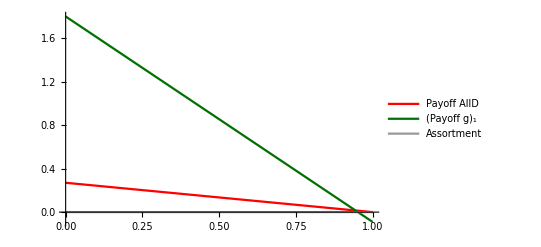

```mathematica
plot = Plot[{PDun[xd,0,3,1,0.9],PC1un[xd,0,3,1,0.9],0},{xd,0,1},PlotStyle->{Red,Darker[Darker[Green]],GrayLevel[0.6],GrayLevel[0.8]},PlotLegends->Placed[{"Payoff AllD",Subscript["Payoff g",1],"Assortment"},{Right,Top}]]
```

```mathematica
labeledPlot=Labeled[plot,{"",Style["Proportion AllD",FontFamily->"Arial",FontSize->14]},{Left,Bottom}];
```

```mathematica
labeledPlot
```

-Graphics-Proportion AllD

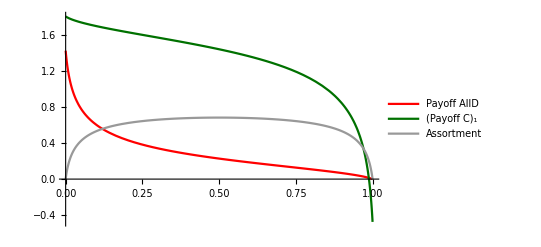

```mathematica
Plot[{PD[xd,0,3,1,0.9],PC1[xd,0,3,1,0.9],(xc1c1[xd,0,0.9]/(1-xd)) - (xdc1[xd,0,0.9]/(2*xd))},{xd,0,1},PlotStyle->{Red,Darker[Darker[Green]],GrayLevel[0.6],GrayLevel[0.8]},PlotLegends->Placed[{"Payoff AllD",Subscript["Payoff C",1],"Assortment"},{Right,Top}]]
```

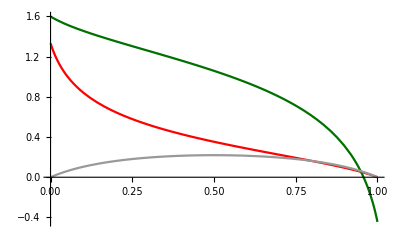

solveSystem[xd,0,√((1-xd)^2),0.5]⟦6⟧

```mathematica
Plot[{PD[xd,0,3,1,0.8],PC1[xd,0,3,1,0.8],(xc1c1[xd,0,0.6]/(1-xd)) - (xdc1[xd,0,0.6]/(2*xd))},{xd,0,1},PlotStyle->{Red,Darker[Darker[Green]],GrayLevel[0.6],GrayLevel[0.8]}]
```

```mathematica
Simplex2DCoord[{0, 1,0 }]
```

{1,0}

```mathematica
Simplex2DCoord[{x1_, x2_, x3_}] :=x1*{0, 0} + x2*{1, 0} + x3*{1/2, √3/2}
```

```mathematica
Simplex2DInverseCoord[{y1_,y2_}]:={1,0,0}+y1*{-1,1,0}+y2*{-1/√3,-1/√3,2/√3}
```

```mathematica
(*ExpectedChange[x_, b_,c_,delta_]:={(x.{1,0,0})*(PD[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),(x.{0,1,0})*(PDC[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),(x.{0,0,1})*(PC1[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta])}
```

```mathematica
(*ExpectedChange[x_,b_,c_,delta_]:={Piecewise[{{(x.{1,0,0})*(PD[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),0<x.{1,0,0}<1}},0],Piecewise[{{(x.{0,1,0})*(PDC[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),0<x.{0,1,0}<1}},0],Piecewise[{{(x.{0,0,1})*(PC1[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),0<x.{0,0,1}<1}},0]}
ExpectedChange[{0.2,0.6,0.2}, 3,1,0.9]
PD[0.8,0.2,3,1,0.9]
PDC[0.8,0.2,3,1,0.9]*)
ExpectedChange[x_List,b_?NumericQ,c_?NumericQ,delta_?NumericQ]:=Module[{change},If[VectorQ[x,NumericQ],(*If all elements of x are numeric,compute the change*)change={Piecewise[{{(x.{1,0,0})*(PD[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),0<x.{1,0,0}<1}},0],Piecewise[{{(x.{0,1,0})*(PDC[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),0<x.{0,1,0}<1}},0],Piecewise[{{(x.{0,0,1})*(PC1[x.{1,0,0},x.{0,1,0},b,c,delta]-AvgP[x.{1,0,0},x.{0,1,0},b,c,delta]),0<x.{0,0,1}<1}},0]},(*Otherwise,return some default value or error*)Throw["Non-numeric input in x"]];
change]
ExpectedChange[{0.2,0.6,0.2}, 3,1,0.9]
```

{0.0922736,-0.142345,0.050071}

```mathematica
Trajectory[initialPoint_List, b_,c_,delta_,time_]:=Module[{x},
NDSolveValue[
{x'[ti]==ExpectedChange[x[ti], b,c,delta],x[0]==initialPoint},
x,{ti,0,time},Method->{"EquationSimplification"->"Residual"},StepMonitor:>Print["Step to ",ti,": ",x[ti],"  ExpectedChange ",ExpectedChange[x[ti], b,c,delta]]]
]
```

```mathematica
BackTrajectory[initialPoint_List, b_,c_,delta_,time_]:=Module[{x},
NDSolveValue[
{x'[ti]==-ExpectedChange[x[ti], b,c,delta],x[0]==initialPoint},
x,{ti,0,time},Method->{"EquationSimplification"->"Residual"},StepMonitor:>Print["Step to ",ti,": ",x[ti],"  ExpectedChange ",-ExpectedChange[x[ti], b,c,delta]]]
]
```

```mathematica
Trajectory[initialPoint_List, b_,c_,delta_,time_]:=Module[{x},
NDSolveValue[
{x'[ti]==ExpectedChange[x[ti], b,c,delta],x[0]==initialPoint},
x,{ti,0,time},Method->{"EquationSimplification"->"Residual"}]
]
```

```mathematica
Outside = Graphics[{EdgeForm[Thick],FaceForm[{White}],Opacity[1], Polygon[{{Simplex2DCoord[{1, 0, 0}],Simplex2DCoord[{0, 1, 0}],Simplex2DCoord[{0, 0, 1}]}}],Boxed->False}];
```

```mathematica
ExpectedChange[{0.2,0.6,0.2}, 3,1,0.9]
ExpectedChange[{0,1,0}, 3,1,0.9]
ExpectedChange[{1,0,0}, 3,1,0.9]
ExpectedChange[{0,1,0}, 3,1,0.9]
ExpectedChange[{0,0.8,0.2}, 3,1,0.9]
ExpectedChange[{0.2,0.8,0}, 3,1,0.9]
ExpectedChange[{0.8,0,0.2}, 3,1,0.9]
ExpectedChange[{0.8,0.21,0}, 3,1,0.9]
```

{0.0931626,-0.139678,0.0465149}

{0,0,0}

{0,0,0}

{0,0,0}

{0,0.,-4.44089×10^-17}

{0.144,-0.144,0}

{-0.139106,0,0.139106}

{0.146551,-0.15039,0}

```mathematica
{-0.1391063742368784,0.,0.1391063742368784}
Max[0.1,1]
```

{-0.139106,0.,0.139106}

1

```mathematica
ExpectedChange[{0.203634863585926,0.796365136414074,1-0.203634863585926-0.796365136414074},3,1,0.9]
```

{0.145951,-0.145951,0}

```mathematica
1-0.203634863585926-0.796365136414074
```

0.

```mathematica
NumberForm[0.,16]
```

0.

```mathematica
Plot[ExpectedChange[{x1,1-x1,0},3,1,0.9][[1]],{x1,0,1}]
```

$Aborted

```mathematica
ExpectedChange[{0.2,0.6,0.2},3,1,0.9]
```

{0.0931626,-0.139678,2}

```mathematica
Total[{0.09316261365479597,-0.13967751062179704,0.04651489696700084}]
```

-2.22045×10^-16

```mathematica
ExpectedChange[{0.2,0,0.8},3,1,0.8]
```

{-0.106102,0,0.106102}

```mathematica
BackTrajectory[{0.55,0,0.45},3,1,0.9,100]
```

Step to 0.0001: {0.55003,0.,0.44997}  ExpectedChange {0.295511,0,-0.295511}

Step to 0.0002: {0.550059,0.,0.449941}  ExpectedChange {0.295505,0,-0.295505}

Step to 0.0004: {0.550118,0.,0.449882}  ExpectedChange {0.295493,0,-0.295493}

Step to 0.0008: {0.550236,0.,0.449764}  ExpectedChange {0.295467,0,-0.295467}

Step to 0.0012: {0.550355,0.,0.449645}  ExpectedChange {0.295442,0,-0.295442}

Step to 0.002: {0.550591,0.,0.449409}  ExpectedChange {0.295392,0,-0.295392}

Step to 0.0036: {0.551063,0.,0.448937}  ExpectedChange {0.295291,0,-0.295291}

Step to 0.0068: {0.552008,0.,0.447992}  ExpectedChange {0.295087,0,-0.295087}

Step to 0.01: {0.552952,0.,0.447048}  ExpectedChange {0.294881,0,-0.294881}

Step to 0.0132: {0.553895,0.,0.446105}  ExpectedChange {0.294672,0,-0.294672}

Step to 0.0164: {0.554838,0.,0.445162}  ExpectedChange {0.294461,0,-0.294461}

Step to 0.0228: {0.556721,0.,0.443279}  ExpectedChange {0.294032,0,-0.294032}

Step to 0.0292: {0.558601,0.,0.441399}  ExpectedChange {0.293593,0,-0.293593}

Step to 0.0356: {0.560479,0.,0.439521}  ExpectedChange {0.293145,0,-0.293145}

Step to 0.0484: {0.564225,0.,0.435775}  ExpectedChange {0.292221,0,-0.292221}

Step to 0.0612: {0.56796,0.,0.43204}  ExpectedChange {0.291261,0,-0.291261}

Step to 0.074: {0.571682,0.,0.428318}  ExpectedChange {0.290266,0,-0.290266}

Step to 0.0868: {0.57539,0.,0.42461}  ExpectedChange {0.289235,0,-0.289235}

Step to 0.0996: {0.579086,0.,0.420914}  ExpectedChange {0.288169,0,-0.288169}

Step to 0.1252: {0.586435,0.,0.413565}  ExpectedChange {0.285937,0,-0.285937}

Step to 0.151905: {0.594038,0.,0.405962}  ExpectedChange {0.283469,0,-0.283469}

Step to 0.17861: {0.601573,0.,0.398427}  ExpectedChange {0.280866,0,-0.280866}

Step to 0.212511: {0.611036,0.,0.388964}  ExpectedChange {0.277375,0,-0.277375}

Step to 0.246412: {0.620378,0.,0.379622}  ExpectedChange {0.27369,0,-0.27369}

Step to 0.280313: {0.629591,0.,0.370409}  ExpectedChange {0.269823,0,-0.269823}

Step to 0.314214: {0.638671,0.,0.361329}  ExpectedChange {0.265789,0,-0.265789}

Step to 0.348115: {0.647611,0.,0.352389}  ExpectedChange {0.261602,0,-0.261602}

Step to 0.389646: {0.658365,0.,0.341635}  ExpectedChange {0.256285,0,-0.256285}

Step to 0.431178: {0.668896,0.,0.331104}  ExpectedChange {0.250786,0,-0.250786}

Step to 0.472709: {0.679194,0.,0.320806}  ExpectedChange {0.245131,0,-0.245131}

Step to 0.51424: {0.689255,0.,0.310745}  ExpectedChange {0.239345,0,-0.239345}

Step to 0.555771: {0.699073,0.,0.300927}  ExpectedChange {0.233454,0,-0.233454}

Step to 0.597303: {0.708645,0.,0.291355}  ExpectedChange {0.22748,0,-0.22748}

Step to 0.638834: {0.717968,0.,0.282032}  ExpectedChange {0.221448,0,-0.221448}

Step to 0.680365: {0.727039,0.,0.272961}  ExpectedChange {0.215378,0,-0.215378}

Step to 0.721897: {0.735857,0.,0.264143}  ExpectedChange {0.209292,0,-0.209292}

Step to 0.763428: {0.744423,0.,0.255577}  ExpectedChange {0.203207,0,-0.203207}

Step to 0.804959: {0.752737,0.,0.247263}  ExpectedChange {0.197144,0,-0.197144}

Step to 0.846491: {0.760799,0.,0.239201}  ExpectedChange {0.191117,0,-0.191117}

Step to 0.888022: {0.768612,0.,0.231388}  ExpectedChange {0.185143,0,-0.185143}

Step to 0.929553: {0.776178,0.,0.223822}  ExpectedChange {0.179235,0,-0.179235}

Step to 0.971085: {0.783501,0.,0.216499}  ExpectedChange {0.173405,0,-0.173405}

Step to 1.01262: {0.790583,0.,0.209417}  ExpectedChange {0.167665,0,-0.167665}

Step to 1.05415: {0.797429,0.,0.202571}  ExpectedChange {0.162024,0,-0.162024}

Step to 1.09568: {0.804043,0.,0.195957}  ExpectedChange {0.156491,0,-0.156491}

Step to 1.13721: {0.810429,0.,0.189571}  ExpectedChange {0.151073,0,-0.151073}

Step to 1.17874: {0.816593,0.,0.183407}  ExpectedChange {0.145777,0,-0.145777}

Step to 1.22027: {0.822539,0.,0.177461}  ExpectedChange {0.140608,0,-0.140608}

Step to 1.2618: {0.828274,0.,0.171726}  ExpectedChange {0.13557,0,-0.13557}

Step to 1.30334: {0.833802,0.,0.166198}  ExpectedChange {0.130666,0,-0.130666}

Step to 1.34487: {0.839129,0.,0.160871}  ExpectedChange {0.125899,0,-0.125899}

Step to 1.3864: {0.844261,0.,0.155739}  ExpectedChange {0.12127,0,-0.12127}

Step to 1.42793: {0.849204,0.,0.150796}  ExpectedChange {0.116781,0,-0.116781}

Step to 1.46946: {0.853963,0.,0.146037}  ExpectedChange {0.112431,0,-0.112431}

Step to 1.51099: {0.858545,0.,0.141455}  ExpectedChange {0.10822,0,-0.10822}

Step to 1.55252: {0.862954,0.,0.137046}  ExpectedChange {0.104148,0,-0.104148}

Step to 1.59405: {0.867198,0.,0.132802}  ExpectedChange {0.100213,0,-0.100213}

Step to 1.63559: {0.87128,0.,0.12872}  ExpectedChange {0.0964132,0,-0.0964132}

Step to 1.67712: {0.875208,0.,0.124792}  ExpectedChange {0.0927472,0,-0.0927472}

Step to 1.71865: {0.878986,0.,0.121014}  ExpectedChange {0.0892124,0,-0.0892124}

Step to 1.76018: {0.88262,0.,0.11738}  ExpectedChange {0.0858061,0,-0.0858061}

Step to 1.80171: {0.886115,0.,0.113885}  ExpectedChange {0.0825256,0,-0.0825256}

Step to 1.84324: {0.889476,0.,0.110524}  ExpectedChange {0.0793679,0,-0.0793679}

Step to 1.88477: {0.892709,0.,0.107291}  ExpectedChange {0.0763298,0,-0.0763298}

Step to 1.92631: {0.895818,0.,0.104182}  ExpectedChange {0.0734081,0,-0.0734081}

Step to 1.96784: {0.898808,0.,0.101192}  ExpectedChange {0.0705995,0,-0.0705995}

Step to 2.00937: {0.901684,0.,0.0983163}  ExpectedChange {0.0679006,0,-0.0679006}

Step to 2.0509: {0.90445,0.,0.0955505}  ExpectedChange {0.065308,0,-0.065308}

Step to 2.09243: {0.90711,0.,0.0928902}  ExpectedChange {0.0628182,0,-0.0628182}

Step to 2.13396: {0.909669,0.,0.0903313}  ExpectedChange {0.0604278,0,-0.0604278}

Step to 2.17549: {0.91213,0.,0.0878696}  ExpectedChange {0.0581334,0,-0.0581334}

Step to 2.21702: {0.914499,0.,0.0855013}  ExpectedChange {0.0559316,0,-0.0559316}

Step to 2.25856: {0.916777,0.,0.0832225}  ExpectedChange {0.053819,0,-0.053819}

Step to 2.30009: {0.91897,0.,0.0810297}  ExpectedChange {0.0517923,0,-0.0517923}

Step to 2.34162: {0.921081,0.,0.0789194}  ExpectedChange {0.0498484,0,-0.0498484}

Step to 2.38315: {0.923112,0.,0.0768881}  ExpectedChange {0.047984,0,-0.047984}

Step to 2.42468: {0.925067,0.,0.0749326}  ExpectedChange {0.0461961,0,-0.0461961}

Step to 2.46621: {0.92695,0.,0.0730499}  ExpectedChange {0.0444816,0,-0.0444816}

Step to 2.50774: {0.928763,0.,0.0712369}  ExpectedChange {0.0428376,0,-0.0428376}

Step to 2.54928: {0.930509,0.,0.0694908}  ExpectedChange {0.0412613,0,-0.0412613}

Step to 2.63234: {0.933812,0.,0.0661882}  ExpectedChange {0.0383007,0,-0.0383007}

Step to 2.70349: {0.936453,0.,0.0635474}  ExpectedChange {0.0359552,0,-0.0359552}

Step to 2.76753: {0.938691,0.,0.0613086}  ExpectedChange {0.0339837,0,-0.0339837}

Step to 2.83157: {0.940808,0.,0.0591922}  ExpectedChange {0.0321355,0,-0.0321355}

Step to 2.89561: {0.94281,0.,0.0571903}  ExpectedChange {0.0304027,0,-0.0304027}

Step to 2.95965: {0.944704,0.,0.055296}  ExpectedChange {0.0287776,0,-0.0287776}

Step to 3.08772: {0.948197,0.,0.0518034}  ExpectedChange {0.0258229,0,-0.0258229}

Step to 3.2158: {0.951334,0.,0.0486663}  ExpectedChange {0.0232199,0,-0.0232199}

Step to 3.33107: {0.953888,0.,0.0461118}  ExpectedChange {0.0211405,0,-0.0211405}

Step to 3.44634: {0.956216,0.,0.0437842}  ExpectedChange {0.0192806,0,-0.0192806}

Step to 3.55008: {0.958137,0.,0.0418634}  ExpectedChange {0.0177733,0,-0.0177733}

Step to 3.65383: {0.959908,0.,0.0400916}  ExpectedChange {0.0164066,0,-0.0164066}

Step to 3.75757: {0.961545,0.,0.0384549}  ExpectedChange {0.015166,0,-0.015166}

Step to 3.86131: {0.963059,0.,0.036941}  ExpectedChange {0.0140384,0,-0.0140384}

Step to 3.96506: {0.964461,0.,0.0355387}  ExpectedChange {0.0130122,0,-0.0130122}

Step to 4.0688: {0.965762,0.,0.034238}  ExpectedChange {0.012077,0,-0.012077}

Step to 4.17254: {0.96697,0.,0.0330301}  ExpectedChange {0.0112237,0,-0.0112237}

Step to 4.27628: {0.968093,0.,0.0319067}  ExpectedChange {0.010444,0,-0.010444}

Step to 4.38003: {0.969139,0.,0.0308608}  ExpectedChange {0.00973065,0,-0.00973065}

Step to 4.48377: {0.970114,0.,0.0298857}  ExpectedChange {0.00907711,0,-0.00907711}

Step to 4.58751: {0.971024,0.,0.0289756}  ExpectedChange {0.00847757,0,-0.00847757}

Step to 4.69126: {0.971875,0.,0.028125}  ExpectedChange {0.00792685,0,-0.00792685}

Step to 4.795: {0.972671,0.,0.0273293}  ExpectedChange {0.0074203,0,-0.0074203}

Step to 4.89874: {0.973416,0.,0.0265841}  ExpectedChange {0.00695378,0,-0.00695378}

Step to 5.00248: {0.974115,0.,0.0258853}  ExpectedChange {0.00652357,0,-0.00652357}

Step to 5.10623: {0.974771,0.,0.0252294}  ExpectedChange {0.00612635,0,-0.00612635}

Step to 5.20997: {0.975387,0.,0.0246131}  ExpectedChange {0.00575913,0,-0.00575913}

Step to 5.31371: {0.975966,0.,0.0240335}  ExpectedChange {0.00541922,0,-0.00541922}

Step to 5.41745: {0.976512,0.,0.0234878}  ExpectedChange {0.00510423,0,-0.00510423}

Step to 5.5212: {0.977026,0.,0.0229737}  ExpectedChange {0.00481197,0,-0.00481197}

Step to 5.62494: {0.977511,0.,0.0224887}  ExpectedChange {0.0045405,0,-0.0045405}

Step to 5.72868: {0.977969,0.,0.0220309}  ExpectedChange {0.00428804,0,-0.00428804}

Step to 5.83243: {0.978402,0.,0.0215984}  ExpectedChange {0.00405302,0,-0.00405302}

Step to 5.93617: {0.978811,0.,0.0211894}  ExpectedChange {0.00383397,0,-0.00383397}

Step to 6.03991: {0.979198,0.,0.0208024}  ExpectedChange {0.00362961,0,-0.00362961}

Step to 6.14365: {0.979564,0.,0.0204359}  ExpectedChange {0.00343875,0,-0.00343875}

Step to 6.2474: {0.979912,0.,0.0200885}  ExpectedChange {0.00326031,0,-0.00326031}

Step to 6.35114: {0.980241,0.,0.019759}  ExpectedChange {0.00309332,0,-0.00309332}

Step to 6.45488: {0.980554,0.,0.0194463}  ExpectedChange {0.0029369,0,-0.0029369}

Step to 6.55863: {0.980851,0.,0.0191493}  ExpectedChange {0.00279024,0,-0.00279024}

Step to 6.66237: {0.981133,0.,0.0188671}  ExpectedChange {0.0026526,0,-0.0026526}

Step to 6.76611: {0.981401,0.,0.0185986}  ExpectedChange {0.00252332,0,-0.00252332}

Step to 6.86985: {0.981657,0.,0.0183432}  ExpectedChange {0.00240177,0,-0.00240177}

Step to 7.07734: {0.982132,0.,0.0178684}  ExpectedChange {0.0021797,0,-0.0021797}

Step to 7.28483: {0.982563,0.,0.017437}  ExpectedChange {0.00198245,0,-0.00198245}

Step to 7.49231: {0.982956,0.,0.0170443}  ExpectedChange {0.0018067,0,-0.0018067}

Step to 7.6998: {0.983314,0.,0.016686}  ExpectedChange {0.00164963,0,-0.00164963}

Step to 7.90728: {0.983641,0.,0.0163586}  ExpectedChange {0.00150888,0,-0.00150888}

Step to 8.11477: {0.983941,0.,0.0160589}  ExpectedChange {0.00138241,0,-0.00138241}

Step to 8.32225: {0.984216,0.,0.0157841}  ExpectedChange {0.00126848,0,-0.00126848}

Step to 8.52974: {0.984468,0.,0.0155317}  ExpectedChange {0.00116562,0,-0.00116562}

Step to 8.73722: {0.9847,0.,0.0152997}  ExpectedChange {0.00107254,0,-0.00107254}

Step to 8.94471: {0.984914,0.,0.015086}  ExpectedChange {0.000988132,0,-0.000988132}

Step to 9.1522: {0.985111,0.,0.0148891}  ExpectedChange {0.000911432,0,-0.000911432}

Step to 9.35968: {0.985293,0.,0.0147073}  ExpectedChange {0.000841606,0,-0.000841606}

Step to 9.56717: {0.985461,0.,0.0145394}  ExpectedChange {0.000777925,0,-0.000777925}

Step to 9.77465: {0.985616,0.,0.0143841}  ExpectedChange {0.000719751,0,-0.000719751}

Step to 9.98214: {0.98576,0.,0.0142404}  ExpectedChange {0.000666526,0,-0.000666526}

Step to 10.1896: {0.985893,0.,0.0141072}  ExpectedChange {0.000617754,0,-0.000617754}

Step to 10.3971: {0.986016,0.,0.0139838}  ExpectedChange {0.000572997,0,-0.000572997}

Step to 10.6046: {0.986131,0.,0.0138692}  ExpectedChange {0.00053187,0,-0.00053187}

Step to 10.8121: {0.986237,0.,0.0137628}  ExpectedChange {0.000494036,0,-0.000494036}

Step to 11.0196: {0.986336,0.,0.013664}  ExpectedChange {0.000459192,0,-0.000459192}

Step to 11.2271: {0.986428,0.,0.0135721}  ExpectedChange {0.000427061,0,-0.000427061}

Step to 11.4345: {0.986513,0.,0.0134866}  ExpectedChange {0.000397397,0,-0.000397397}

Step to 11.642: {0.986593,0.,0.013407}  ExpectedChange {0.000369989,0,-0.000369989}

Step to 11.8495: {0.986667,0.,0.0133329}  ExpectedChange {0.000344644,0,-0.000344644}

Step to 12.057: {0.986736,0.,0.0132639}  ExpectedChange {0.000321184,0,-0.000321184}

Step to 12.2645: {0.9868,0.,0.0131995}  ExpectedChange {0.000299448,0,-0.000299448}

Step to 12.472: {0.98686,0.,0.0131395}  ExpectedChange {0.000279296,0,-0.000279296}

Step to 12.6795: {0.986916,0.,0.0130835}  ExpectedChange {0.000260598,0,-0.000260598}

Step to 12.8869: {0.986969,0.,0.0130313}  ExpectedChange {0.000243238,0,-0.000243238}

Step to 13.0944: {0.987017,0.,0.0129825}  ExpectedChange {0.000227111,0,-0.000227111}

Step to 13.3019: {0.987063,0.,0.012937}  ExpectedChange {0.000212119,0,-0.000212119}

Step to 13.7169: {0.987145,0.,0.0128546}  ExpectedChange {0.000185196,0,-0.000185196}

Step to 14.0904: {0.98721,0.,0.0127895}  ExpectedChange {0.000164043,0,-0.000164043}

Step to 14.4638: {0.987268,0.,0.0127318}  ExpectedChange {0.000145414,0,-0.000145414}

Step to 14.8373: {0.987319,0.,0.0126806}  ExpectedChange {0.000128985,0,-0.000128985}

Step to 15.2108: {0.987365,0.,0.0126352}  ExpectedChange {0.00011448,0,-0.00011448}

Step to 15.5842: {0.987405,0.,0.0125949}  ExpectedChange {0.000101659,0,-0.000101659}

Step to 15.9577: {0.987441,0.,0.0125591}  ExpectedChange {0.0000903162,0,-0.0000903162}

Step to 16.3312: {0.987473,0.,0.0125272}  ExpectedChange {0.0000802726,0,-0.0000802726}

Step to 16.7047: {0.987501,0.,0.012499}  ExpectedChange {0.0000713727,0,-0.0000713727}

Step to 17.0781: {0.987526,0.,0.0124738}  ExpectedChange {0.0000634807,0,-0.0000634807}

Step to 17.4516: {0.987549,0.,0.0124514}  ExpectedChange {0.0000564778,0,-0.0000564778}

Step to 18.1986: {0.987586,0.,0.0124138}  ExpectedChange {0.0000447386,0,-0.0000447386}

Step to 18.8455: {0.987612,0.,0.0123876}  ExpectedChange {0.0000365884,0,-0.0000365884}

Step to 19.4924: {0.987634,0.,0.0123662}  ExpectedChange {0.0000299373,0,-0.0000299373}

Step to 20.1392: {0.987651,0.,0.0123486}  ExpectedChange {0.0000245035,0,-0.0000245035}

Step to 20.7861: {0.987666,0.,0.0123342}  ExpectedChange {0.0000200624,0,-0.0000200624}

Step to 21.433: {0.987678,0.,0.0123225}  ExpectedChange {0.0000164326,0,-0.0000164326}

Step to 22.0799: {0.987687,0.,0.0123128}  ExpectedChange {0.0000134637,0,-0.0000134637}

Step to 22.7268: {0.987695,0.,0.0123049}  ExpectedChange {0.0000110317,0,-0.0000110317}

Step to 23.3737: {0.987702,0.,0.0122984}  ExpectedChange {9.03845×10^-6,0,-9.03845×10^-6}

Step to 24.0206: {0.987707,0.,0.0122931}  ExpectedChange {7.40747×10^-6,0,-7.40747×10^-6}

Step to 24.6675: {0.987711,0.,0.0122888}  ExpectedChange {6.07427×10^-6,0,-6.07427×10^-6}

Step to 25.3144: {0.987715,0.,0.0122852}  ExpectedChange {4.98125×10^-6,0,-4.98125×10^-6}

Step to 25.9613: {0.987718,0.,0.0122823}  ExpectedChange {4.08317×10^-6,0,-4.08317×10^-6}

Step to 26.6082: {0.98772,0.,0.0122799}  ExpectedChange {3.34743×10^-6,0,-3.34743×10^-6}

Step to 27.2551: {0.987722,0.,0.012278}  ExpectedChange {2.74702×10^-6,0,-2.74702×10^-6}

Step to 27.9019: {0.987724,0.,0.0122764}  ExpectedChange {2.2549×10^-6,0,-2.2549×10^-6}

Step to 28.5488: {0.987725,0.,0.012275}  ExpectedChange {1.84874×10^-6,0,-1.84874×10^-6}

Step to 29.1957: {0.987726,0.,0.0122739}  ExpectedChange {1.51393×10^-6,0,-1.51393×10^-6}

Step to 29.8426: {0.987727,0.,0.0122731}  ExpectedChange {1.24069×10^-6,0,-1.24069×10^-6}

Step to 30.4895: {0.987728,0.,0.0122723}  ExpectedChange {1.019×10^-6,0,-1.019×10^-6}

Step to 31.1364: {0.987728,0.,0.0122717}  ExpectedChange {8.37501×10^-7,0,-8.37501×10^-7}

Step to 31.7833: {0.987729,0.,0.0122712}  ExpectedChange {6.86762×10^-7,0,-6.86762×10^-7}

Step to 32.4302: {0.987729,0.,0.0122708}  ExpectedChange {5.62937×10^-7,0,-5.62937×10^-7}

Step to 33.0771: {0.987729,0.,0.0122705}  ExpectedChange {4.61611×10^-7,0,-4.61611×10^-7}

Step to 34.3709: {0.98773,0.,0.01227}  ExpectedChange {3.11459×10^-7,0,-3.11459×10^-7}

Step to 35.6647: {0.98773,0.,0.0122697}  ExpectedChange {2.11161×10^-7,0,-2.11161×10^-7}

Step to 36.9584: {0.987731,0.,0.0122695}  ExpectedChange {1.43575×10^-7,0,-1.43575×10^-7}

Step to 38.2522: {0.987731,0.,0.0122693}  ExpectedChange {9.76721×10^-8,0,-9.76721×10^-8}

Step to 39.546: {0.987731,0.,0.0122692}  ExpectedChange {6.63879×10^-8,0,-6.63879×10^-8}

Step to 40.8398: {0.987731,0.,0.0122691}  ExpectedChange {4.48344×10^-8,0,-4.48344×10^-8}

Step to 42.1336: {0.987731,0.,0.0122691}  ExpectedChange {3.00346×10^-8,0,-3.00346×10^-8}

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {Null⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {Null⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {0.987731+1/2 (-x12-x13),x12,x13,-5.82506×10^-23+1/2 (-x12-x23),x23,0.012269+1/2 (-x13-x23)}/.Null⟦1⟧ does not exist.

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {Null⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 3 of {0.987731+1/2 (-x12-x13),x12,x13,-5.82506×10^-23+1/2 (-x12-x23),x23,0.012269+1/2 (-x13-x23)}/.Null⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolveValue::nlnum: The function value {1.22795×10^-8+0.987731 (0.+0.00621072 (2.7 Part[«2»]+1.42105 Part[«2»])-1. (-0.236842 Part[«2»]+1.8 Plus[«2»])),-4.68994×10^-23,-1.22795×10^-8+0.012269 (0.-0.5 (2.7 Part[«2»]+1.42105 Part[«2»])+80.5059 (-0.236842 Part[«2»]+1.8 Plus[«2»]))} is not a list of numbers with dimensions {3} at {ti,x$423420[ti],x$423420'[ti]} = {44.7211,{0.987731,-5.82506×10^-23,0.012269},{1.22795×10^-8,-4.68994×10^-23,-1.22795×10^-8}}.

InterpolatingFunction[…]

```mathematica
%132[40]
```

```mathematica
{{0.9497241727157818,0.,0.05027582728419761}} (*the intersection point if starting at 0.8*)
```

```mathematica
{0.7528964283105991,0.,0.2471035716894052}(*the intersection point if starting at 0.6*)
```

```mathematica
{0.9877308983271877,0.,0.01226910167275589} (*the intersection point if starting at 0.9*)
```

```mathematica
%343[2]
```

```mathematica
ExpectedChange[{0.36967132485506154,0.6122566683499397,0.01807200679499883},3,1,0.9]
```

{0.198436,-0.205573,0.0071376}

```mathematica
Total[{0.36967132485506154,0.6122566683499397,0.01807200679499883}]
```

1.

```mathematica
Plot[,{ti,0,1}]
```

Part::partw: Part 5 of solveSystem[x$2927676[0.0000204286].{1,0,0},x$2927676[0.0000204286].{0,1,0},Max[0,1-x$2927676[0.0000204286].{0,1,0}-x$2927676[0.0000204286].{1,0,0}],0.9] does not exist.

Part::partw: Part 6 of solveSystem[x$2927676[0.0000204286].{1,0,0},x$2927676[0.0000204286].{0,1,0},Max[0,1-x$2927676[0.0000204286].{0,1,0}-x$2927676[0.0000204286].{1,0,0}],0.9] does not exist.

Part::partw: Part 5 of solveSystem[x$2927676[0.0000204286].{1,0,0},x$2927676[0.0000204286].{0,1,0},Max[0,1-x$2927676[0.0000204286].{0,1,0}-x$2927676[0.0000204286].{1,0,0}],0.9] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolveValue::dsvar: 0.0000204286 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

-Graphics-

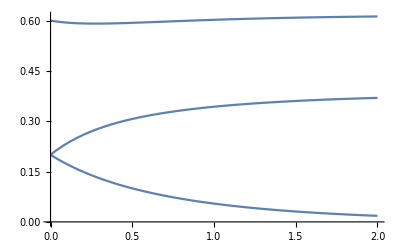

```mathematica
Plot[%343[x],{x,0.,2.}]
```

```mathematica
%337[0.00005]
```

{0.20002,0.599996,0.199985}

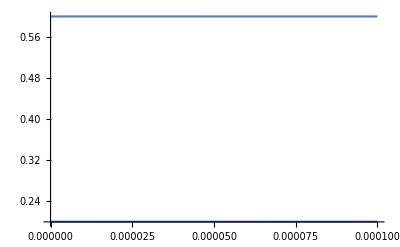

```mathematica
Plot[%337[x],{x,0.,0.0001}]
```

```mathematica
InterpolatingFunction[…]
```

InterpolatingFunction[…]

```mathematica
%329[0.2]
```

{0.259405,0.591426,0.149169}

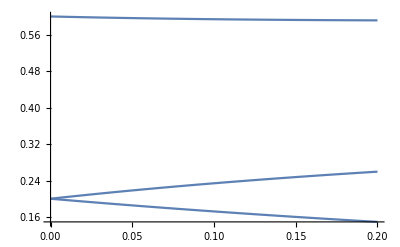

```mathematica
Plot[%327[x],{x,0.,0.2}]
```

```mathematica
%292[0.00001]
```

{0.200004,0.599999,0.199997}

```mathematica
Simplex2DCoord[{0.23391294600881285,0.5939471111878992,0.17213994280328782}]
```

{0.680017,0.149078}

```mathematica
Simplex2DCoord[{0.2,0.8,0.2}]
```

{0.9,0.173205}

```mathematica
Plot[%270[x],{x,0.,0.2}]
```

-Graphics-

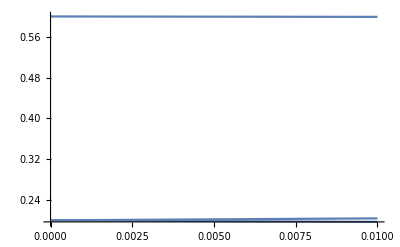

```mathematica
Plot[%268[x],{x,0.,0.01}]
```

```mathematica
%211[0.006002052956908911]
```

{0.203635,0.796365,0.}

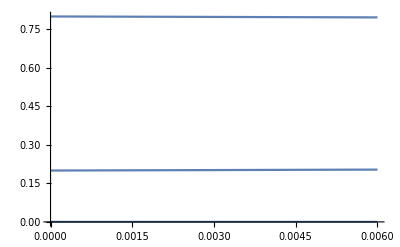

```mathematica
Plot[%211[x],{x,0.,0.006002052956908911}]
```

```mathematica
Plot[InterpolatingFunction[{{0.,0.}},{5,3,1,{1},{2},0,0,0,0,Automatic,{},{},False},{{0.}},{{{0.7,0.3,0.},{-0.9179999999999999,0.9179999999999998,0.}}},{Automatic}][x],{x,0.,0.}]
```

Plot::plld: Endpoints for x in {x,0.,0.} must have distinct machine-precision numerical values.

Plot[InterpolatingFunction[{{0.,0.}},{5,3,1,{1},{2},0,0,0,0,Automatic,{},{},False},{{0.}},{{{0.7,0.3,0.},{-0.918,0.918,0.}}},{Automatic}][x],{x,0.,0.}]

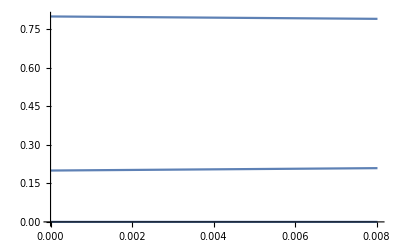

```mathematica
Plot[%161[x],{x,0.,0.008022515656124041}]
```

```mathematica
deltav = 0.8
```

0.8

```mathematica
BottomTrajectory[initialPoint_List, b_,c_,delta_,time_]:=Module[{x},
NDSolveValue[
{x'[ti]=={1,-1,0},x[0]==initialPoint},
x,{ti,0,time},Method->{"EquationSimplification"->"Residual"}]
]
```

```mathematica
bv = 3;cv=1;deltav=0.8;Tv = 100;div=10;
listOfProjectedTrajectories=Flatten[Table[Simplex2DCoord[Trajectory[N[{initx1,initx2,1-initx1-initx2}],bv,cv,deltav,Tv][ti]],{initx1,1/div,(div-1)/div,1/div},{initx2,1/div,1-initx1-1/div,1/div}]];
```

Step to 0.0001: {0.0999969,0.0999981,0.800005}  ExpectedChange {-0.0314661,-0.0193357,0.0508018}

Step to 0.0002: {0.0999937,0.0999961,0.80001}  ExpectedChange {-0.0314652,-0.0193351,0.0508002}

Step to 0.0004: {0.0999874,0.0999923,0.80002}  ExpectedChange {-0.0314633,-0.0193337,0.0507971}

Step to 0.0008: {0.0999748,0.0999845,0.800041}  ExpectedChange {-0.0314597,-0.019331,0.0507907}

Step to 0.0016: {0.0999497,0.0999691,0.800081}  ExpectedChange {-0.0314524,-0.0193256,0.050778}

Step to 0.0032: {0.0998994,0.0999382,0.800162}  ExpectedChange {-0.0314377,-0.0193149,0.0507526}

Step to 0.0064: {0.0997988,0.0998764,0.800325}  ExpectedChange {-0.0314084,-0.0192933,0.0507017}

Step to 0.0128: {0.099598,0.099753,0.800649}  ExpectedChange {-0.0313498,-0.0192503,0.0506001}

Step to 0.0256: {0.0991974,0.0995072,0.801295}  ExpectedChange {-0.0312326,-0.0191646,0.0503972}

Step to 0.0384: {0.0987984,0.0992624,0.801939}  ExpectedChange {-0.0311155,-0.0190793,0.0501948}

Step to 0.0512: {0.0984009,0.0990188,0.80258}  ExpectedChange {-0.0309985,-0.0189943,0.0499929}

Step to 0.064: {0.0980049,0.0987762,0.803219}  ExpectedChange {-0.0308816,-0.0189098,0.0497914}

Step to 0.0896: {0.0972173,0.0982942,0.804488}  ExpectedChange {-0.0306481,-0.0187418,0.0493899}

Step to 0.1152: {0.0964357,0.0978166,0.805748}  ExpectedChange {-0.0304151,-0.0185753,0.0489904}

Step to 0.1408: {0.09566,0.0973432,0.806997}  ExpectedChange {-0.0301826,-0.0184102,0.0485928}

Step to 0.1664: {0.0948903,0.096874,0.808236}  ExpectedChange {-0.0299506,-0.0182467,0.0481973}

Step to 0.2176: {0.0933687,0.095948,0.810683}  ExpectedChange {-0.0294884,-0.017924,0.0474125}

Step to 0.2688: {0.0918706,0.0950384,0.813091}  ExpectedChange {-0.0290289,-0.0176072,0.0466361}

Step to 0.32: {0.0903961,0.0941449,0.815459}  ExpectedChange {-0.0285723,-0.017296,0.0458683}

Step to 0.3712: {0.0889448,0.0932672,0.817788}  ExpectedChange {-0.0281188,-0.0169905,0.0451093}

Step to 0.4224: {0.0875166,0.092405,0.820078}  ExpectedChange {-0.0276688,-0.0166906,0.0443594}

Step to 0.5248: {0.084729,0.090726,0.824545}  ExpectedChange {-0.02678,-0.016107,0.042887}

Step to 0.61696: {0.0822973,0.089265,0.828438}  ExpectedChange {-0.025994,-0.0156,0.041594}

Step to 0.70912: {0.0799373,0.0878501,0.832213}  ExpectedChange {-0.0252222,-0.0151098,0.040332}

Step to 0.80128: {0.0776479,0.0864795,0.835873}  ExpectedChange {-0.0244655,-0.0146359,0.0391015}

Step to 0.89344: {0.0754274,0.0851519,0.839421}  ExpectedChange {-0.0237247,-0.0141779,0.0379026}

Step to 0.9856: {0.0732744,0.0838658,0.84286}  ExpectedChange {-0.0230003,-0.0137352,0.0367355}

Step to 1.07776: {0.0711875,0.0826197,0.846193}  ExpectedChange {-0.0222929,-0.0133074,0.0356003}

Step to 1.26208: {0.0672051,0.0802427,0.852552}  ExpectedChange {-0.02093,-0.0124949,0.0334249}

Step to 1.42797: {0.0638306,0.0782273,0.857942}  ExpectedChange {-0.0197638,-0.0118101,0.031574}

Step to 1.59386: {0.0606447,0.076322,0.863033}  ExpectedChange {-0.0186554,-0.011167,0.0298223}

Step to 1.74316: {0.0579309,0.0746959,0.867373}  ExpectedChange {-0.0177067,-0.0106216,0.0283283}

Step to 1.89245: {0.0553553,0.073149,0.871496}  ExpectedChange {-0.0168038,-0.0101063,0.0269101}

Step to 2.04175: {0.0529111,0.0716768,0.875412}  ExpectedChange {-0.0159457,-0.00961926,0.025565}

Step to 2.19105: {0.0505917,0.0702753,0.879133}  ExpectedChange {-0.0151311,-0.00915906,0.0242902}

Step to 2.34035: {0.0483909,0.0689407,0.882668}  ExpectedChange {-0.0143588,-0.00872416,0.0230829}

Step to 2.48965: {0.0463022,0.0676691,0.886029}  ExpectedChange {-0.0136271,-0.00831312,0.0219402}

Step to 2.63895: {0.0443199,0.0664573,0.889223}  ExpectedChange {-0.0129344,-0.00792459,0.020859}

Step to 2.78825: {0.0424382,0.0653018,0.89226}  ExpectedChange {-0.0122792,-0.00755726,0.0198365}

Step to 2.93755: {0.0406516,0.0641997,0.895149}  ExpectedChange {-0.0116597,-0.0072099,0.0188696}

Step to 3.1209: {0.0385799,0.0629149,0.898505}  ExpectedChange {-0.0109453,-0.00680893,0.0177542}

Step to 3.30426: {0.0366349,0.0617012,0.901664}  ExpectedChange {-0.010279,-0.00643431,0.0167133}

Step to 3.48762: {0.0348077,0.0605538,0.904638}  ExpectedChange {-0.00965784,-0.00608414,0.015742}

Step to 3.67097: {0.0330906,0.0594686,0.907441}  ExpectedChange {-0.00907889,-0.00575668,0.0148356}

Step to 3.85433: {0.031476,0.0584415,0.910082}  ExpectedChange {-0.00853929,-0.00545028,0.0139896}

Step to 4.03769: {0.0299569,0.0574688,0.912574}  ExpectedChange {-0.00803634,-0.00516343,0.0131998}

Step to 4.22104: {0.0285269,0.0565469,0.914926}  ExpectedChange {-0.00756749,-0.00489473,0.0124622}

Step to 4.4044: {0.0271799,0.0556728,0.917147}  ExpectedChange {-0.00713032,-0.00464287,0.0117732}

Step to 4.58775: {0.0259103,0.0548434,0.919246}  ExpectedChange {-0.00672258,-0.00440666,0.0111292}

Step to 4.77111: {0.024713,0.0540559,0.921231}  ExpectedChange {-0.00634215,-0.00418498,0.0105271}

Step to 4.95447: {0.023583,0.0533079,0.923109}  ExpectedChange {-0.00598705,-0.0039768,0.00996385}

Step to 5.13782: {0.022516,0.0525968,0.924887}  ExpectedChange {-0.00565544,-0.00378117,0.00943661}

Step to 5.32118: {0.0215078,0.0519205,0.926572}  ExpectedChange {-0.00534561,-0.00359721,0.00894282}

Step to 5.50453: {0.0205545,0.051277,0.928169}  ExpectedChange {-0.00505597,-0.00342412,0.00848009}

Step to 5.68789: {0.0196526,0.0506643,0.929683}  ExpectedChange {-0.00478506,-0.00326113,0.00804619}

Step to 5.87125: {0.0187987,0.0500805,0.931121}  ExpectedChange {-0.00453152,-0.00310756,0.00763908}

Step to 6.0546: {0.0179898,0.0495241,0.932486}  ExpectedChange {-0.00429408,-0.00296278,0.00725686}

Step to 6.23796: {0.0172231,0.0489936,0.933783}  ExpectedChange {-0.00407159,-0.00282617,0.00689776}

Step to 6.42131: {0.0164959,0.0484873,0.935017}  ExpectedChange {-0.00386297,-0.00269721,0.00656018}

Step to 6.60467: {0.0158057,0.048004,0.93619}  ExpectedChange {-0.00366723,-0.00257537,0.0062426}

Step to 6.78803: {0.0151503,0.0475425,0.937307}  ExpectedChange {-0.00348345,-0.0024602,0.00594365}

Step to 6.97138: {0.0145276,0.0471015,0.938371}  ExpectedChange {-0.00331079,-0.00235126,0.00566205}

Step to 7.15474: {0.0139356,0.0466799,0.939385}  ExpectedChange {-0.00314846,-0.00224814,0.00539661}

Step to 7.33809: {0.0133724,0.0462767,0.940351}  ExpectedChange {-0.00299576,-0.00215048,0.00514624}

Step to 7.52145: {0.0128365,0.045891,0.941273}  ExpectedChange {-0.00285201,-0.00205794,0.00490995}

Step to 7.70481: {0.0123261,0.0455217,0.942152}  ExpectedChange {-0.00271659,-0.00197018,0.00468678}

Step to 7.88816: {0.0118398,0.0451682,0.942992}  ExpectedChange {-0.00258895,-0.00188692,0.00447587}

Step to 8.07152: {0.0113762,0.0448295,0.943794}  ExpectedChange {-0.00246855,-0.00180788,0.00427643}

Step to 8.25487: {0.0109341,0.044505,0.944561}  ExpectedChange {-0.00235492,-0.00173279,0.00408771}

Step to 8.43823: {0.0105123,0.0441938,0.945294}  ExpectedChange {-0.0022476,-0.00166143,0.00390903}

Step to 8.62159: {0.0101095,0.0438955,0.945995}  ExpectedChange {-0.00214617,-0.00159358,0.00373975}

Step to 8.80494: {0.00972489,0.0436093,0.946666}  ExpectedChange {-0.00205027,-0.00152902,0.00357929}

Step to 8.9883: {0.00935736,0.0433346,0.947308}  ExpectedChange {-0.00195952,-0.00146756,0.00342708}

Step to 9.17165: {0.00900601,0.0430709,0.947923}  ExpectedChange {-0.0018736,-0.00140903,0.00328263}

Step to 9.35501: {0.00867,0.0428177,0.948512}  ExpectedChange {-0.0017922,-0.00135326,0.00314546}

Step to 9.53837: {0.00834853,0.0425745,0.949077}  ExpectedChange {-0.00171504,-0.00130009,0.00301513}

Step to 9.72172: {0.00804083,0.0423408,0.949618}  ExpectedChange {-0.00164186,-0.00124937,0.00289124}

Step to 9.90508: {0.00774621,0.0421162,0.950138}  ExpectedChange {-0.00157242,-0.00120098,0.0027734}

Step to 10.0884: {0.007464,0.0419002,0.950636}  ExpectedChange {-0.00150648,-0.00115478,0.00266126}

Step to 10.2718: {0.00719357,0.0416926,0.951114}  ExpectedChange {-0.00144383,-0.00111065,0.00255448}

Step to 10.4551: {0.00693433,0.0414928,0.951573}  ExpectedChange {-0.00138428,-0.00106849,0.00245277}

Step to 10.6385: {0.00668575,0.0413006,0.952014}  ExpectedChange {-0.00132765,-0.00102819,0.00235584}

Step to 10.8219: {0.0064473,0.0411157,0.952437}  ExpectedChange {-0.00127377,-0.000989644,0.00226341}

Step to 11.0052: {0.00621849,0.0409376,0.952844}  ExpectedChange {-0.00122246,-0.000952772,0.00217524}

Step to 11.1886: {0.00599886,0.0407662,0.953235}  ExpectedChange {-0.0011736,-0.000917484,0.00209109}

Step to 11.3719: {0.00578797,0.0406011,0.953611}  ExpectedChange {-0.00112704,-0.000883698,0.00201074}

Step to 11.5553: {0.00558542,0.040442,0.953973}  ExpectedChange {-0.00108265,-0.000851338,0.00193398}

Step to 11.7386: {0.00539082,0.0402888,0.95432}  ExpectedChange {-0.0010403,-0.000820335,0.00186064}

Step to 11.922: {0.00520381,0.0401411,0.954655}  ExpectedChange {-0.0009999,-0.000790619,0.00179052}

Step to 12.1054: {0.00502404,0.0399988,0.954977}  ExpectedChange {-0.000961327,-0.000762129,0.00172346}

Step to 12.2887: {0.00485118,0.0398616,0.955287}  ExpectedChange {-0.000924487,-0.000734805,0.00165929}

Step to 12.4721: {0.00468492,0.0397293,0.955586}  ExpectedChange {-0.000889287,-0.000708589,0.00159788}

Step to 12.6554: {0.00452496,0.0396016,0.955873}  ExpectedChange {-0.00085564,-0.00068343,0.00153907}

Step to 12.8388: {0.00437105,0.0394786,0.95615}  ExpectedChange {-0.000823466,-0.000659278,0.00148274}

Step to 13.0221: {0.0042229,0.0393598,0.956417}  ExpectedChange {-0.000792687,-0.000636085,0.00142877}

Step to 13.2055: {0.00408028,0.0392452,0.956674}  ExpectedChange {-0.000763233,-0.000613808,0.00137704}

Step to 13.3888: {0.00394294,0.0391347,0.956922}  ExpectedChange {-0.000735036,-0.000592403,0.00132744}

Step to 13.5722: {0.00381066,0.039028,0.957161}  ExpectedChange {-0.000708031,-0.000571831,0.00127986}

Step to 13.7556: {0.00368323,0.0389249,0.957392}  ExpectedChange {-0.00068216,-0.000552054,0.00123421}

Step to 13.9389: {0.00356044,0.0388255,0.957614}  ExpectedChange {-0.000657367,-0.000533037,0.0011904}

Step to 14.3056: {0.00332803,0.0386367,0.958035}  ExpectedChange {-0.000610805,-0.000497148,0.00110795}

Step to 14.6289: {0.00313678,0.0384807,0.958382}  ExpectedChange {-0.000572852,-0.000467721,0.00104057}

Step to 14.9522: {0.00295737,0.038334,0.958709}  ExpectedChange {-0.000537548,-0.000440203,0.000977751}

Step to 15.2754: {0.00278897,0.0381959,0.959015}  ExpectedChange {-0.000504678,-0.000414453,0.000919131}

Step to 15.5987: {0.00263083,0.0380659,0.959303}  ExpectedChange {-0.000474048,-0.000390342,0.00086439}

Step to 15.922: {0.00248226,0.0379434,0.959574}  ExpectedChange {-0.000445482,-0.000367752,0.000813234}

Step to 16.2452: {0.00234261,0.037828,0.959829}  ExpectedChange {-0.000418819,-0.000346574,0.000765393}

Step to 16.8918: {0.00208775,0.0376166,0.960296}  ExpectedChange {-0.000370634,-0.000308068,0.000678702}

Step to 17.5383: {0.00186205,0.0374287,0.960709}  ExpectedChange {-0.00032848,-0.000274122,0.000602602}

Step to 18.1202: {0.00168085,0.0372772,0.961042}  ExpectedChange {-0.000294991,-0.000246977,0.000541968}

Step to 18.7021: {0.00151805,0.0371407,0.961341}  ExpectedChange {-0.000265175,-0.00022267,0.000487845}

Step to 19.284: {0.00137163,0.0370176,0.961611}  ExpectedChange {-0.000238583,-0.000200878,0.000439461}

Step to 19.8659: {0.00123984,0.0369065,0.961854}  ExpectedChange {-0.00021483,-0.000181319,0.000396149}

Step to 20.4477: {0.00112114,0.0368062,0.962073}  ExpectedChange {-0.000193581,-0.000163746,0.000357328}

Step to 21.0296: {0.00101413,0.0367156,0.96227}  ExpectedChange {-0.00017455,-0.000147944,0.000322494}

Step to 21.6115: {0.000917623,0.0366337,0.962449}  ExpectedChange {-0.000157483,-0.000133722,0.000291205}

Step to 22.1934: {0.000830524,0.0365597,0.96261}  ExpectedChange {-0.000142162,-0.000120912,0.000263074}

Step to 22.7753: {0.00075188,0.0364927,0.962755}  ExpectedChange {-0.000128394,-0.000109367,0.000237761}

Step to 23.3572: {0.000680836,0.0364322,0.962887}  ExpectedChange {-0.000116011,-0.0000989537,0.000214965}

Step to 23.939: {0.000616631,0.0363774,0.963006}  ExpectedChange {-0.000104865,-0.000089557,0.000194422}

Step to 24.5209: {0.000558584,0.0363278,0.963114}  ExpectedChange {-0.0000948245,-0.0000810731,0.000175898}

Step to 25.1028: {0.000506086,0.0362829,0.963211}  ExpectedChange {-0.0000857738,-0.0000734097,0.000159183}

Step to 25.6847: {0.000458592,0.0362422,0.963299}  ExpectedChange {-0.0000776103,-0.0000664844,0.000144095}

Step to 26.2666: {0.000415612,0.0362054,0.963379}  ExpectedChange {-0.0000702429,-0.0000602237,0.000130467}

Step to 26.8485: {0.000376707,0.036172,0.963451}  ExpectedChange {-0.0000635907,-0.0000545619,0.000118153}

Step to 27.4304: {0.000341483,0.0361418,0.963517}  ExpectedChange {-0.0000575813,-0.00004944,0.000107021}

Step to 28.0122: {0.000309584,0.0361144,0.963576}  ExpectedChange {-0.0000521506,-0.0000448051,0.0000969557}

Step to 28.5941: {0.000280691,0.0360895,0.96363}  ExpectedChange {-0.0000472407,-0.00004061,0.0000878507}

Step to 29.176: {0.000254516,0.036067,0.963678}  ExpectedChange {-0.0000428003,-0.0000368118,0.0000796121}

Step to 30.3398: {0.000209308,0.0360281,0.963763}  ExpectedChange {-0.0000351481,-0.0000302573,0.0000654054}

Step to 31.5035: {0.000172175,0.0359962,0.963832}  ExpectedChange {-0.0000288787,-0.0000248787,0.0000537575}

Step to 32.6673: {0.000141661,0.0359699,0.963888}  ExpectedChange {-0.0000237376,-0.0000204621,0.0000441998}

Step to 33.8311: {0.000116574,0.0359482,0.963935}  ExpectedChange {-0.0000195184,-0.0000168335,0.000036352}

Step to 34.9949: {0.0000959428,0.0359304,0.963974}  ExpectedChange {-0.0000160536,-0.000013851,0.0000299046}

Step to 36.1586: {0.0000789721,0.0359158,0.964005}  ExpectedChange {-0.0000132069,-0.0000113987,0.0000246056}

Step to 37.3224: {0.0000650094,0.0359037,0.964031}  ExpectedChange {-0.000010867,-9.38184×10^-6,0.0000202489}

Step to 38.4862: {0.0000535197,0.0358938,0.964053}  ExpectedChange {-8.94313×10^-6,-7.72266×10^-6,0.0000166658}

Step to 39.6499: {0.0000440635,0.0358857,0.96407}  ExpectedChange {-7.36078×10^-6,-6.35746×10^-6,0.0000137182}

Step to 40.8137: {0.0000362799,0.0358789,0.964085}  ExpectedChange {-6.05904×10^-6,-5.23397×10^-6,0.000011293}

Step to 41.9775: {0.0000298725,0.0358734,0.964097}  ExpectedChange {-4.98793×10^-6,-4.30928×10^-6,9.29721×10^-6}

Step to 43.1412: {0.0000245977,0.0358688,0.964107}  ExpectedChange {-4.10648×10^-6,-3.54813×10^-6,7.65461×10^-6}

Step to 44.305: {0.0000202548,0.0358651,0.964115}  ExpectedChange {-3.381×10^-6,-2.92154×10^-6,6.30254×10^-6}

Step to 45.4688: {0.0000166792,0.035862,0.964121}  ExpectedChange {-2.78382×10^-6,-2.40569×10^-6,5.1895×10^-6}

Step to 46.6325: {0.000013735,0.0358595,0.964127}  ExpectedChange {-2.29221×10^-6,-1.98097×10^-6,4.27317×10^-6}

Step to 47.7963: {0.0000113107,0.0358574,0.964131}  ExpectedChange {-1.88747×10^-6,-1.63127×10^-6,3.51874×10^-6}

Step to 48.9601: {9.31442×10^-6,0.0358556,0.964135}  ExpectedChange {-1.55425×10^-6,-1.34333×10^-6,2.89758×10^-6}

Step to 50.1239: {7.67057×10^-6,0.0358542,0.964138}  ExpectedChange {-1.27988×10^-6,-1.10623×10^-6,2.38611×10^-6}

Step to 51.2876: {6.31689×10^-6,0.035853,0.964141}  ExpectedChange {-1.05397×10^-6,-9.10994×10^-7,1.96496×10^-6}

Step to 52.4514: {5.20215×10^-6,0.0358521,0.964143}  ExpectedChange {-8.6794×10^-7,-7.5022×10^-7,1.61816×10^-6}

Step to 54.7789: {3.52902×10^-6,0.0358506,0.964146}  ExpectedChange {-5.8876×10^-7,-5.08923×10^-7,1.09768×10^-6}

Step to 57.1065: {2.39539×10^-6,0.0358497,0.964148}  ExpectedChange {-3.99618×10^-7,-3.45436×10^-7,7.45054×10^-7}

Step to 59.434: {1.62682×10^-6,0.035849,0.964149}  ExpectedChange {-2.71392×10^-7,-2.34599×10^-7,5.05991×10^-7}

Step to 61.7616: {1.10494×10^-6,0.0358485,0.96415}  ExpectedChange {-1.84327×10^-7,-1.5934×10^-7,3.43667×10^-7}

Step to 64.0891: {7.50257×10^-7,0.0358482,0.964151}  ExpectedChange {-1.25157×10^-7,-1.08192×10^-7,2.33349×10^-7}

Step to 66.4166: {5.09386×10^-7,0.035848,0.964151}  ExpectedChange {-8.49747×10^-8,-7.34563×10^-8,1.58431×10^-7}

Step to 68.7442: {3.45984×10^-7,0.0358479,0.964152}  ExpectedChange {-5.77159×10^-8,-4.98926×10^-8,1.07609×10^-7}

Step to 71.0717: {2.35077×10^-7,0.0358478,0.964152}  ExpectedChange {-3.92147×10^-8,-3.38993×10^-8,7.31141×10^-8}

Step to 73.3992: {1.59675×10^-7,0.0358477,0.964152}  ExpectedChange {-2.66363×10^-8,-2.30259×10^-8,4.96623×10^-8}

Step to 75.7268: {1.08394×10^-7,0.0358477,0.964152}  ExpectedChange {-1.80818×10^-8,-1.5631×10^-8,3.37128×10^-8}

Step to 78.0543: {7.35828×10^-8,0.0358476,0.964152}  ExpectedChange {-1.22747×10^-8,-1.0611×10^-8,2.28857×10^-8}

Step to 82.7094: {3.50433×10^-8,0.0358476,0.964152}  ExpectedChange {-5.84575×10^-9,-5.0534×10^-9,1.08992×10^-8}

Step to 86.899: {1.78549×10^-8,0.0358476,0.964152}  ExpectedChange {-2.97846×10^-9,-2.57476×10^-9,5.55322×10^-9}

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {Null⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {Null⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 4 of {-2.58289×10^-9+1/2 (-x12-x13),x12,x13,0.0358476+1/2 (-x12-x23),x23,0.964152+1/2 (-x13-x23)}/.Null⟦1⟧ does not exist.

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {Null⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 5 of {-2.58289×10^-9+1/2 (-x12-x13),x12,x13,0.0358476+1/2 (-x12-x23),x23,0.964152+1/2 (-x13-x23)}/.Null⟦1⟧ does not exist.

Part::partw: Part 4 of {-2.58289×10^-9+1/2 (-x12-x13),x12,x13,0.0358476+1/2 (-x12-x23),x23,0.964152+1/2 (-x13-x23)}/.Null⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NDSolveValue::nlnum: The function value {-6.7871×10^-9,-5.86713×10^-9-0.0358476 (0.+26.8959 (-0.4 Part[«2»]+1.6 Plus[«2»])-1. (-0.222222 Part[«2»]+1.6 Plus[«2»])),1.26542×10^-8-0.964152 (0.-1. (-0.4 Part[«2»]+1.6 Plus[«2»])+0.0371804 (-0.222222 Part[«2»]+1.6 Plus[«2»]))} is not a list of numbers with dimensions {3} at {ti,x$1053364[ti],x$1053364'[ti]} = {91.0885,{-2.58289×10^-9,0.0358476,0.964152},{-6.7871×10^-9,-5.86713×10^-9,1.26542×10^-8}}.

Step to 0.0001: {0.0999989,0.199996,0.700005}  ExpectedChange {-0.0108499,-0.0352094,0.0460593}

Step to 0.0002: {0.0999978,0.199993,0.700009}  ExpectedChange {-0.0108503,-0.0352086,0.046059}

Step to 0.0004: {0.0999957,0.199986,0.700018}  ExpectedChange {-0.0108512,-0.0352072,0.0460584}

Step to 0.0008: {0.0999913,0.199972,0.700037}  ExpectedChange {-0.0108529,-0.0352042,0.0460571}

Step to 0.0016: {0.0999826,0.199944,0.700074}  ExpectedChange {-0.0108562,-0.0351984,0.0460546}

Step to 0.0032: {0.0999653,0.199887,0.700147}  ExpectedChange {-0.0108629,-0.0351867,0.0460496}

Step to 0.0064: {0.0999305,0.199775,0.700295}  ExpectedChange {-0.0108762,-0.0351633,0.0460395}

Step to 0.0128: {0.0998608,0.19955,0.700589}  ExpectedChange {-0.0109028,-0.0351165,0.0460193}

Step to 0.0256: {0.0997209,0.199101,0.701178}  ExpectedChange {-0.0109555,-0.035023,0.0459785}

Step to 0.0384: {0.0995803,0.198653,0.701766}  ExpectedChange {-0.0110076,-0.0349296,0.0459372}

Step to 0.0512: {0.0994391,0.198207,0.702354}  ExpectedChange {-0.0110592,-0.0348362,0.0458955}

Step to 0.064: {0.0992972,0.197762,0.702941}  ExpectedChange {-0.0111103,-0.0347429,0.0458532}

Step to 0.0896: {0.0990115,0.196874,0.704114}  ExpectedChange {-0.0112108,-0.0345565,0.0457673}

Step to 0.1152: {0.0987233,0.195992,0.705285}  ExpectedChange {-0.0113091,-0.0343704,0.0456794}

Step to 0.1408: {0.0984325,0.195115,0.706453}  ExpectedChange {-0.0114052,-0.0341845,0.0455897}

Step to 0.192: {0.0978438,0.193374,0.708782}  ExpectedChange {-0.0115909,-0.0338137,0.0454046}

Step to 0.2432: {0.0972457,0.191652,0.711102}  ExpectedChange {-0.011768,-0.0334443,0.0452123}

Step to 0.2944: {0.0966389,0.189949,0.713412}  ExpectedChange {-0.0119367,-0.0330763,0.0450129}

Step to 0.3456: {0.0960236,0.188265,0.715711}  ExpectedChange {-0.0120969,-0.0327098,0.0448067}

Step to 0.3968: {0.0954003,0.1866,0.718}  ExpectedChange {-0.0122487,-0.032345,0.0445937}

Step to 0.4992: {0.0941314,0.183325,0.722544}  ExpectedChange {-0.0125278,-0.0316207,0.0441485}

Step to 0.6016: {0.0928357,0.180124,0.727041}  ExpectedChange {-0.0127748,-0.0309041,0.0436789}

Step to 0.704: {0.0915162,0.176995,0.731488}  ExpectedChange {-0.0129907,-0.0301958,0.0431865}

Step to 0.8064: {0.0901762,0.173939,0.735885}  ExpectedChange {-0.0131765,-0.0294964,0.0426729}

Step to 0.9088: {0.0888187,0.170954,0.740227}  ExpectedChange {-0.0133333,-0.0288064,0.0421397}

Step to 1.0112: {0.0874465,0.168039,0.744514}  ExpectedChange {-0.0134623,-0.0281263,0.0415886}

Step to 1.1136: {0.0860625,0.165194,0.748744}  ExpectedChange {-0.0135646,-0.0274564,0.0410211}

Step to 1.216: {0.0846693,0.162416,0.752915}  ExpectedChange {-0.0136415,-0.0267973,0.0404388}

Step to 1.3184: {0.0832695,0.159705,0.757025}  ExpectedChange {-0.0136942,-0.0261491,0.0398433}

Step to 1.4208: {0.0818655,0.15706,0.761074}  ExpectedChange {-0.013724,-0.0255121,0.0392362}

Step to 1.5232: {0.0804596,0.15448,0.765061}  ExpectedChange {-0.0137321,-0.0248867,0.0386188}

Step to 1.728: {0.0776504,0.149508,0.772841}  ExpectedChange {-0.0136884,-0.0236708,0.0373592}

Step to 1.9328: {0.0748577,0.144781,0.780361}  ExpectedChange {-0.0135731,-0.0225026,0.0360757}

Step to 2.1376: {0.0720951,0.140288,0.787617}  ExpectedChange {-0.0133958,-0.0213826,0.0347784}

Step to 2.32192: {0.0696443,0.136436,0.793919}  ExpectedChange {-0.0131908,-0.020416,0.0336068}

Step to 2.50624: {0.0672347,0.132759,0.800006}  ExpectedChange {-0.0129494,-0.0194883,0.0324377}

Step to 2.69056: {0.0648725,0.12925,0.805878}  ExpectedChange {-0.0126775,-0.0185991,0.0312766}

Step to 2.87488: {0.0625628,0.125901,0.811537}  ExpectedChange {-0.0123805,-0.0177479,0.0301284}

Step to 3.0592: {0.0603098,0.122705,0.816985}  ExpectedChange {-0.0120634,-0.0169339,0.0289973}

Step to 3.24352: {0.0581167,0.119656,0.822227}  ExpectedChange {-0.0117307,-0.0161562,0.0278869}

Step to 3.42784: {0.0559861,0.116747,0.827267}  ExpectedChange {-0.0113865,-0.0154139,0.0268004}

Step to 3.61216: {0.0539197,0.113972,0.832109}  ExpectedChange {-0.0110343,-0.0147059,0.0257402}

Step to 3.79648: {0.0519187,0.111324,0.836758}  ExpectedChange {-0.0106774,-0.0140311,0.0247085}

Step to 3.9808: {0.0499837,0.108797,0.841219}  ExpectedChange {-0.0103186,-0.0133883,0.0237069}

Step to 4.16512: {0.0481148,0.106386,0.845499}  ExpectedChange {-0.00996018,-0.0127764,0.0227366}

Step to 4.34944: {0.0463118,0.104086,0.849603}  ExpectedChange {-0.00960429,-0.012194,0.0217983}

Step to 4.53376: {0.044574,0.101889,0.853537}  ExpectedChange {-0.00925265,-0.0116401,0.0208928}

Step to 4.71808: {0.0429006,0.0997929,0.857307}  ExpectedChange {-0.00890671,-0.0111134,0.0200201}

Step to 4.9024: {0.0412902,0.097791,0.860919}  ExpectedChange {-0.00856768,-0.0106126,0.0191803}

Step to 5.08672: {0.0397417,0.0958791,0.864379}  ExpectedChange {-0.00823652,-0.0101366,0.0183732}

Step to 5.27104: {0.0382534,0.0940528,0.867694}  ExpectedChange {-0.00791399,-0.00968433,0.0175983}

Step to 5.45536: {0.0368237,0.0923077,0.870869}  ExpectedChange {-0.00760069,-0.00925454,0.0168552}

Step to 5.63968: {0.0354509,0.0906399,0.873909}  ExpectedChange {-0.00729703,-0.00884616,0.0161432}

Step to 5.824: {0.0341331,0.0890454,0.876821}  ExpectedChange {-0.00700332,-0.00845815,0.0154615}

Step to 6.00832: {0.0328686,0.0875207,0.879611}  ExpectedChange {-0.00671973,-0.00808948,0.0148092}

Step to 6.19264: {0.0316553,0.0860622,0.882283}  ExpectedChange {-0.00644634,-0.00773917,0.0141855}

Step to 6.37696: {0.0304915,0.0846666,0.884842}  ExpectedChange {-0.00618316,-0.00740627,0.0135894}

Step to 6.56128: {0.0293753,0.0833309,0.887294}  ExpectedChange {-0.0059301,-0.00708987,0.01302}

Step to 6.7456: {0.0283049,0.082052,0.889643}  ExpectedChange {-0.00568703,-0.00678913,0.0124762}

Step to 6.92992: {0.0272783,0.0808272,0.891894}  ExpectedChange {-0.00545378,-0.00650321,0.011957}

Step to 7.11424: {0.0262938,0.0796538,0.894052}  ExpectedChange {-0.00523014,-0.00623133,0.0114615}

Step to 7.29856: {0.0253497,0.0785293,0.896121}  ExpectedChange {-0.00501584,-0.00597275,0.0109886}

Step to 7.48288: {0.0244442,0.0774513,0.898105}  ExpectedChange {-0.00481064,-0.00572675,0.0105374}

Step to 7.6672: {0.0235757,0.0764175,0.900007}  ExpectedChange {-0.00461424,-0.00549267,0.0101069}

Step to 7.85152: {0.0227427,0.0754258,0.901832}  ExpectedChange {-0.00442634,-0.00526987,0.00969621}

Step to 8.03584: {0.0219435,0.0744741,0.903582}  ExpectedChange {-0.00424665,-0.00505774,0.00930438}

Step to 8.22016: {0.0211767,0.0735607,0.905263}  ExpectedChange {-0.00407485,-0.00485571,0.00893056}

Step to 8.5888: {0.0197346,0.071841,0.908424}  ExpectedChange {-0.0037537,-0.00447985,0.00823354}

Step to 8.92058: {0.0185338,0.0704067,0.911059}  ExpectedChange {-0.00348859,-0.00417101,0.00765959}

Step to 9.25235: {0.0174175,0.0690706,0.913512}  ExpectedChange {-0.00324436,-0.00388736,0.00713172}

Step to 9.58413: {0.0163789,0.0678247,0.915796}  ExpectedChange {-0.00301936,-0.00362657,0.00664593}

Step to 9.9159: {0.015412,0.0666619,0.917926}  ExpectedChange {-0.00281206,-0.00338651,0.00619857}

Step to 10.2477: {0.0145111,0.0655755,0.919913}  ExpectedChange {-0.00262099,-0.00316529,0.00578628}

Step to 10.5795: {0.0136712,0.0645597,0.921769}  ExpectedChange {-0.0024448,-0.0029612,0.005406}

Step to 10.9112: {0.0128874,0.0636089,0.923504}  ExpectedChange {-0.00228225,-0.0027727,0.00505495}

Step to 11.243: {0.0121554,0.0627183,0.925126}  ExpectedChange {-0.00213218,-0.0025984,0.00473058}

Step to 11.5748: {0.0114713,0.0618833,0.926645}  ExpectedChange {-0.00199353,-0.00243706,0.00443059}

Step to 11.9066: {0.0108314,0.0610998,0.928069}  ExpectedChange {-0.00186535,-0.00228754,0.00415289}

Step to 12.2383: {0.0102325,0.0603642,0.929403}  ExpectedChange {-0.00174675,-0.00214883,0.00389557}

Step to 12.5701: {0.00967142,0.0596729,0.930656}  ExpectedChange {-0.00163691,-0.00202,0.00365691}

Step to 12.9019: {0.00914544,0.0590228,0.931832}  ExpectedChange {-0.00153511,-0.00190024,0.00343535}

Step to 13.2337: {0.00865198,0.0584111,0.932937}  ExpectedChange {-0.00144068,-0.00178879,0.00322946}

Step to 13.5654: {0.00818873,0.057835,0.933976}  ExpectedChange {-0.001353,-0.00168497,0.00303796}

Step to 13.8972: {0.00775351,0.0572922,0.934954}  ExpectedChange {-0.00127152,-0.00158816,0.00285968}

Step to 14.229: {0.00734437,0.0567805,0.935875}  ExpectedChange {-0.00119574,-0.00149781,0.00269355}

Step to 14.5608: {0.0069595,0.0562977,0.936743}  ExpectedChange {-0.0011252,-0.0014134,0.00253861}

Step to 14.8925: {0.00659721,0.055842,0.937561}  ExpectedChange {-0.00105948,-0.00133449,0.00239397}

Step to 15.2243: {0.00625599,0.0554116,0.938332}  ExpectedChange {-0.000998192,-0.00126064,0.00225883}

Step to 15.5561: {0.00593441,0.055005,0.939061}  ExpectedChange {-0.000940995,-0.00119148,0.00213248}

Step to 15.8879: {0.00563117,0.0546205,0.939748}  ExpectedChange {-0.000887571,-0.00112666,0.00201423}

Step to 16.2196: {0.00534508,0.0542569,0.940398}  ExpectedChange {-0.00083763,-0.00106585,0.00190348}

Step to 16.5514: {0.00507501,0.0539129,0.941012}  ExpectedChange {-0.000790909,-0.00100877,0.00179967}

Step to 16.8832: {0.00481994,0.0535872,0.941593}  ExpectedChange {-0.000747167,-0.000955143,0.00170231}

Step to 17.215: {0.00457892,0.0532787,0.942142}  ExpectedChange {-0.000706182,-0.000904734,0.00161092}

Step to 17.5468: {0.00435107,0.0529865,0.942662}  ExpectedChange {-0.000667754,-0.000857316,0.00152507}

Step to 17.8785: {0.00413557,0.0527096,0.943155}  ExpectedChange {-0.000631696,-0.000812682,0.00144438}

Step to 18.2103: {0.00393166,0.052447,0.943621}  ExpectedChange {-0.000597839,-0.000770642,0.00136848}

Step to 18.5421: {0.00373864,0.0521979,0.944063}  ExpectedChange {-0.000566028,-0.000731023,0.00129705}

Step to 18.8739: {0.00355586,0.0519617,0.944482}  ExpectedChange {-0.000536119,-0.000693663,0.00122978}

Step to 19.5374: {0.00321861,0.0515246,0.945257}  ExpectedChange {-0.000481494,-0.00062514,0.00110663}

Step to 20.1346: {0.0029444,0.051168,0.945888}  ExpectedChange {-0.000437625,-0.000569825,0.00100745}

Step to 20.6994: {0.00270798,0.0508598,0.946432}  ExpectedChange {-0.000400203,-0.000522424,0.000922627}

Step to 21.2642: {0.00249168,0.0505771,0.946931}  ExpectedChange {-0.000366296,-0.000479298,0.000845593}

Step to 21.8289: {0.00229363,0.0503177,0.947389}  ExpectedChange {-0.000335529,-0.000440013,0.000775542}

Step to 22.3937: {0.00211215,0.0500794,0.947808}  ExpectedChange {-0.000307575,-0.000404187,0.000711762}

Step to 22.9585: {0.00194573,0.0498605,0.948194}  ExpectedChange {-0.000282145,-0.000371481,0.000653626}

Step to 23.5233: {0.00179303,0.0496593,0.948548}  ExpectedChange {-0.000258982,-0.000341594,0.000600576}

Step to 24.0881: {0.00165281,0.0494742,0.948873}  ExpectedChange {-0.000237862,-0.000314259,0.000552121}

Step to 24.6529: {0.001524,0.0493039,0.949172}  ExpectedChange {-0.000218584,-0.000289236,0.000507821}

Step to 25.2176: {0.0014056,0.0491471,0.949447}  ExpectedChange {-0.000200971,-0.000266313,0.000467284}

Step to 25.7824: {0.00129671,0.0490027,0.949701}  ExpectedChange {-0.000184865,-0.000245297,0.000430161}

Step to 26.3472: {0.00119652,0.0488697,0.949934}  ExpectedChange {-0.000170124,-0.000226016,0.00039614}

Step to 26.912: {0.00110431,0.0487471,0.950149}  ExpectedChange {-0.000156621,-0.000208317,0.000364938}

Step to 27.4768: {0.0010194,0.0486341,0.950346}  ExpectedChange {-0.000144245,-0.00019206,0.000336305}

Step to 28.0415: {0.000941183,0.0485299,0.950529}  ExpectedChange {-0.000132892,-0.00017712,0.000310013}

Step to 28.6063: {0.000869113,0.0484338,0.950697}  ExpectedChange {-0.000122473,-0.000163383,0.000285856}

Step to 29.1711: {0.000802683,0.0483452,0.950852}  ExpectedChange {-0.000112904,-0.000150746,0.00026365}

Step to 29.7359: {0.000741434,0.0482634,0.950995}  ExpectedChange {-0.000104112,-0.000139117,0.000243228}

Step to 30.3007: {0.000684949,0.0481878,0.951127}  ExpectedChange {-0.0000960284,-0.00012841,0.000224438}

Step to 30.8655: {0.000632842,0.0481181,0.951249}  ExpectedChange {-0.0000885937,-0.000118548,0.000207142}

Step to 31.4302: {0.000584765,0.0480538,0.951361}  ExpectedChange {-0.0000817526,-0.000109463,0.000191216}

Step to 32.5598: {0.000499441,0.0479395,0.951561}  ExpectedChange {-0.0000696557,-0.0000933707,0.000163026}

Step to 33.5764: {0.00043348,0.047851,0.951715}  ExpectedChange {-0.0000603431,-0.0000809582,0.000141301}

Step to 34.5537: {0.000378387,0.0477771,0.951845}  ExpectedChange {-0.000052591,-0.0000706096,0.000123201}

Step to 35.5309: {0.000330362,0.0477126,0.951957}  ExpectedChange {-0.000045853,-0.0000616026,0.000107456}

Step to 36.5082: {0.000288482,0.0476563,0.952055}  ExpectedChange {-0.0000399921,-0.0000537588,0.0000937509}

Step to 37.4855: {0.00025195,0.0476072,0.952141}  ExpectedChange {-0.0000348909,-0.0000469247,0.0000818156}

Step to 38.4627: {0.000220074,0.0475643,0.952216}  ExpectedChange {-0.0000304485,-0.0000409678,0.0000714163}

Step to 39.44: {0.000192253,0.0475269,0.952281}  ExpectedChange {-0.0000265779,-0.0000357734,0.0000623513}

Step to 40.4172: {0.000167966,0.0474942,0.952338}  ExpectedChange {-0.000023204,-0.0000312425,0.0000544465}

Step to 41.3945: {0.00014676,0.0474656,0.952388}  ExpectedChange {-0.000020262,-0.0000272892,0.0000475512}

Step to 42.3718: {0.000128241,0.0474407,0.952431}  ExpectedChange {-0.0000176957,-0.000023839,0.0000415347}

Step to 43.349: {0.000112067,0.0474189,0.952469}  ExpectedChange {-0.0000154566,-0.0000208271,0.0000362837}

Step to 44.3263: {0.0000979389,0.0473998,0.952502}  ExpectedChange {-0.0000135024,-0.0000181974,0.0000316998}

Step to 45.3035: {0.000085596,0.0473832,0.952531}  ExpectedChange {-0.0000117965,-0.000015901,0.0000276975}

Step to 46.2808: {0.0000748121,0.0473687,0.952557}  ExpectedChange {-0.0000103071,-0.0000138954,0.0000242025}

Step to 47.2581: {0.0000653894,0.047356,0.952579}  ExpectedChange {-9.00639×10^-6,-0.0000121435,0.0000211499}

Step to 48.2353: {0.0000571555,0.0473449,0.952598}  ExpectedChange {-7.8704×10^-6,-0.000010613,0.0000184834}

Step to 49.2126: {0.00004996,0.0473352,0.952615}  ExpectedChange {-6.87811×10^-6,-9.27585×10^-6,0.000016154}

Step to 50.1898: {0.0000436715,0.0473267,0.95263}  ExpectedChange {-6.01124×10^-6,-8.1075×10^-6,0.0000141187}

Step to 51.1671: {0.0000381754,0.0473193,0.952643}  ExpectedChange {-5.25387×10^-6,-7.08655×10^-6,0.0000123404}

Step to 53.1216: {0.0000291736,0.0473071,0.952664}  ExpectedChange {-4.01395×10^-6,-5.41478×10^-6,9.42873×10^-6}

Step to 55.0761: {0.0000222969,0.0472978,0.95268}  ExpectedChange {-3.06718×10^-6,-4.138×10^-6,7.20518×10^-6}

Step to 57.0307: {0.0000170428,0.0472908,0.952692}  ExpectedChange {-2.34405×10^-6,-3.16264×10^-6,5.50669×10^-6}

Step to 58.9852: {0.0000130273,0.0472853,0.952702}  ExpectedChange {-1.79155×10^-6,-2.41733×10^-6,4.20888×10^-6}

Step to 60.9397: {9.95797×10^-6,0.0472812,0.952709}  ExpectedChange {-1.36933×10^-6,-1.8477×10^-6,3.21703×10^-6}

Step to 62.8942: {7.61192×10^-6,0.047278,0.952714}  ExpectedChange {-1.04665×10^-6,-1.41234×10^-6,2.45899×10^-6}

Step to 64.8488: {5.81878×10^-6,0.0472756,0.952719}  ExpectedChange {-8.00048×10^-7,-1.07961×10^-6,1.87965×10^-6}

Step to 66.8033: {4.44817×10^-6,0.0472738,0.952722}  ExpectedChange {-6.11572×10^-7,-8.25287×10^-7,1.43686×10^-6}

Step to 68.7578: {3.40041×10^-6,0.0472723,0.952724}  ExpectedChange {-4.67503×10^-7,-6.30882×10^-7,1.09838×10^-6}

Step to 70.7123: {2.59942×10^-6,0.0472713,0.952726}  ExpectedChange {-3.57371×10^-7,-4.82267×10^-7,8.39637×10^-7}

Step to 72.6668: {1.98711×10^-6,0.0472704,0.952728}  ExpectedChange {-2.73185×10^-7,-3.68662×10^-7,6.41847×10^-7}

Step to 74.6214: {1.51906×10^-6,0.0472698,0.952729}  ExpectedChange {-2.08836×10^-7,-2.81825×10^-7,4.90661×10^-7}

Step to 76.5759: {1.16128×10^-6,0.0472693,0.95273}  ExpectedChange {-1.59647×10^-7,-2.15445×10^-7,3.75092×10^-7}

Step to 78.5304: {8.87754×10^-7,0.047269,0.95273}  ExpectedChange {-1.22043×10^-7,-1.647×10^-7,2.86743×10^-7}

Step to 80.4849: {6.78648×10^-7,0.0472687,0.952731}  ExpectedChange {-9.3296×10^-8,-1.25905×10^-7,2.19201×10^-7}

Step to 82.4394: {5.18796×10^-7,0.0472685,0.952731}  ExpectedChange {-7.13203×10^-8,-9.62486×10^-8,1.67569×10^-7}

Step to 86.3485: {3.03863×10^-7,0.0472682,0.952732}  ExpectedChange {-4.17726×10^-8,-5.63733×10^-8,9.81458×10^-8}

Step to 89.8666: {1.88528×10^-7,0.047268,0.952732}  ExpectedChange {-2.59171×10^-8,-3.4976×10^-8,6.08931×10^-8}

Step to 94.1684: {1.03828×10^-7,0.0472679,0.952732}  ExpectedChange {-1.42734×10^-8,-1.92624×10^-8,3.35357×10^-8}

Step to 98.0399: {5.9374×10^-8,0.0472678,0.952732}  ExpectedChange {-8.16219×10^-9,-1.10152×10^-8,1.91773×10^-8}

Step to 100.: {4.52618×10^-8,0.0472678,0.952732}  ExpectedChange {-6.22217×10^-9,-8.39703×10^-9,1.46192×10^-8}

Step to 0.0001: {0.100001,0.299995,0.600004}  ExpectedChange {0.0069261,-0.0478385,0.0409124}

Step to 0.0002: {0.100001,0.29999,0.600008}  ExpectedChange {0.00692527,-0.0478382,0.0409129}

Step to 0.0004: {0.100003,0.299981,0.600016}  ExpectedChange {0.00692362,-0.0478376,0.040914}

Step to 0.0008: {0.100006,0.299962,0.600033}  ExpectedChange {0.00692031,-0.0478363,0.040916}

Step to 0.0016: {0.100011,0.299923,0.600065}  ExpectedChange {0.0069137,-0.0478338,0.0409201}

Step to 0.0032: {0.100022,0.299847,0.600131}  ExpectedChange {0.00690046,-0.0478288,0.0409283}

Step to 0.0064: {0.100044,0.299694,0.600262}  ExpectedChange {0.00687399,-0.0478187,0.0409447}

Step to 0.0128: {0.100088,0.299388,0.600524}  ExpectedChange {0.00682102,-0.0477984,0.0409773}

Step to 0.0256: {0.100175,0.298776,0.601049}  ExpectedChange {0.006715,-0.0477573,0.0410423}

Step to 0.0384: {0.10026,0.298165,0.601575}  ExpectedChange {0.00660886,-0.0477156,0.0411068}

Step to 0.0512: {0.100344,0.297555,0.602101}  ExpectedChange {0.00650261,-0.0476734,0.0411708}

Step to 0.064: {0.100426,0.296945,0.602629}  ExpectedChange {0.00639626,-0.0476306,0.0412343}

Step to 0.0896: {0.100587,0.295727,0.603686}  ExpectedChange {0.00618328,-0.0475432,0.0413599}

Step to 0.1152: {0.100743,0.294511,0.604746}  ExpectedChange {0.00596996,-0.0474535,0.0414835}

Step to 0.1408: {0.100893,0.293297,0.60581}  ExpectedChange {0.00575635,-0.0473615,0.0416052}

Step to 0.192: {0.101177,0.290877,0.607946}  ExpectedChange {0.00532848,-0.047171,0.0418425}

Step to 0.23808: {0.101413,0.288707,0.609879}  ExpectedChange {0.00494291,-0.0469921,0.0420492}

Step to 0.28416: {0.101632,0.286546,0.611821}  ExpectedChange {0.00455718,-0.0468064,0.0422492}

Step to 0.33024: {0.101833,0.284394,0.613773}  ExpectedChange {0.00417157,-0.046614,0.0424424}

Step to 0.37632: {0.102017,0.28225,0.615733}  ExpectedChange {0.00378635,-0.0464152,0.0426288}

Step to 0.4224: {0.102182,0.280116,0.617701}  ExpectedChange {0.0034018,-0.0462101,0.0428083}

Step to 0.51456: {0.102461,0.275877,0.621662}  ExpectedChange {0.00263579,-0.045782,0.0431462}

Step to 0.60672: {0.102668,0.271679,0.625653}  ExpectedChange {0.00187564,-0.0453311,0.0434555}

Step to 0.69888: {0.102807,0.267522,0.629671}  ExpectedChange {0.00112336,-0.0448591,0.0437357}

Step to 0.79104: {0.102876,0.263411,0.633714}  ExpectedChange {0.000380894,-0.0443674,0.0439865}

Step to 0.8832: {0.102877,0.259345,0.637778}  ExpectedChange {-0.000349933,-0.0438576,0.0442075}

Step to 0.97536: {0.102812,0.255327,0.641861}  ExpectedChange {-0.00106739,-0.043331,0.0443984}

Step to 1.06752: {0.102681,0.251359,0.64596}  ExpectedChange {-0.00176985,-0.0427893,0.0445591}

Step to 1.15968: {0.102486,0.247441,0.650073}  ExpectedChange {-0.0024558,-0.0422337,0.0446895}

Step to 1.25184: {0.102229,0.243575,0.654197}  ExpectedChange {-0.00312387,-0.0416658,0.0447897}

Step to 1.344: {0.101911,0.239761,0.658328}  ExpectedChange {-0.00377279,-0.0410868,0.0448595}

Step to 1.43616: {0.101534,0.236002,0.662464}  ExpectedChange {-0.0044014,-0.0404979,0.0448993}

Step to 1.52832: {0.1011,0.232297,0.666603}  ExpectedChange {-0.00500868,-0.0399006,0.0449093}

Step to 1.62048: {0.100611,0.228648,0.670741}  ExpectedChange {-0.00559374,-0.039296,0.0448898}

Step to 1.71264: {0.10007,0.225054,0.674876}  ExpectedChange {-0.00615579,-0.0386853,0.0448411}

Step to 1.8048: {0.0994776,0.221517,0.679005}  ExpectedChange {-0.00669419,-0.0380695,0.0447637}

Step to 1.89696: {0.0988367,0.218037,0.683126}  ExpectedChange {-0.00720837,-0.0374498,0.0446582}

Step to 1.98912: {0.0981497,0.214615,0.687236}  ExpectedChange {-0.00769793,-0.0368271,0.0445251}

Step to 2.08128: {0.0974186,0.211249,0.691332}  ExpectedChange {-0.00816254,-0.0362025,0.044365}

Step to 2.17344: {0.0966459,0.207942,0.695412}  ExpectedChange {-0.00860199,-0.0355768,0.0441787}

Step to 2.2656: {0.0958339,0.204692,0.699474}  ExpectedChange {-0.00901617,-0.0349508,0.043967}

Step to 2.35776: {0.0949848,0.2015,0.703515}  ExpectedChange {-0.00940509,-0.0343255,0.0437306}

Step to 2.44992: {0.0941011,0.198365,0.707534}  ExpectedChange {-0.00976881,-0.0337016,0.0434704}

Step to 2.54208: {0.093185,0.195288,0.711527}  ExpectedChange {-0.0101075,-0.0330798,0.0431873}

Step to 2.63424: {0.0922389,0.192268,0.715493}  ExpectedChange {-0.0104214,-0.0324608,0.0428822}

Step to 2.7264: {0.0912649,0.189304,0.719431}  ExpectedChange {-0.0107109,-0.0318451,0.042556}

Step to 2.81856: {0.0902654,0.186398,0.723337}  ExpectedChange {-0.0109763,-0.0312335,0.0422098}

Step to 2.91072: {0.0892425,0.183547,0.72721}  ExpectedChange {-0.0112181,-0.0306264,0.0418445}

Step to 3.00288: {0.0881984,0.180753,0.731049}  ExpectedChange {-0.0114368,-0.0300243,0.0414611}

Step to 3.09504: {0.0871351,0.178013,0.734852}  ExpectedChange {-0.011633,-0.0294278,0.0410608}

Step to 3.1872: {0.0860548,0.175328,0.738617}  ExpectedChange {-0.0118073,-0.0288371,0.0406444}

Step to 3.27936: {0.0849595,0.172698,0.742343}  ExpectedChange {-0.0119603,-0.0282528,0.0402132}

Step to 3.37152: {0.0838509,0.170121,0.746028}  ExpectedChange {-0.0120928,-0.0276752,0.039768}

Step to 3.46368: {0.0827311,0.167596,0.749673}  ExpectedChange {-0.0122053,-0.0271046,0.0393099}

Step to 3.55584: {0.0816018,0.165124,0.753274}  ExpectedChange {-0.0122987,-0.0265413,0.0388401}

Step to 3.648: {0.0804648,0.162704,0.756831}  ExpectedChange {-0.0123738,-0.0259856,0.0383594}

Step to 3.74016: {0.0793216,0.160335,0.760344}  ExpectedChange {-0.0124312,-0.0254377,0.0378688}

Step to 3.83232: {0.078174,0.158015,0.763811}  ExpectedChange {-0.0124718,-0.0248977,0.0373695}

Step to 3.92448: {0.0770234,0.155745,0.767232}  ExpectedChange {-0.0124963,-0.024366,0.0368623}

Step to 4.01664: {0.0758711,0.153524,0.770605}  ExpectedChange {-0.0125056,-0.0238425,0.0363481}

Step to 4.1088: {0.0747188,0.15135,0.773931}  ExpectedChange {-0.0125004,-0.0233276,0.035828}

Step to 4.20096: {0.0735675,0.149224,0.777209}  ExpectedChange {-0.0124815,-0.0228212,0.0353027}

Step to 4.29312: {0.0724186,0.147144,0.780438}  ExpectedChange {-0.0124497,-0.0223235,0.0347732}

Step to 4.38528: {0.0712731,0.145109,0.783618}  ExpectedChange {-0.0124057,-0.0218345,0.0342402}

Step to 4.47744: {0.0701323,0.143119,0.786749}  ExpectedChange {-0.0123504,-0.0213543,0.0337047}

Step to 4.5696: {0.0689971,0.141172,0.78983}  ExpectedChange {-0.0122843,-0.0208829,0.0331672}

Step to 4.66176: {0.0678684,0.139269,0.792862}  ExpectedChange {-0.0122083,-0.0204204,0.0326287}

Step to 4.75392: {0.0667471,0.137408,0.795845}  ExpectedChange {-0.012123,-0.0199667,0.0320897}

Step to 4.84608: {0.0656341,0.135589,0.798777}  ExpectedChange {-0.0120291,-0.0195218,0.031551}

Step to 4.93824: {0.0645302,0.13381,0.80166}  ExpectedChange {-0.0119274,-0.0190858,0.0310132}

Step to 5.0304: {0.0634359,0.132071,0.804493}  ExpectedChange {-0.0118183,-0.0186585,0.0304768}

Step to 5.12256: {0.062352,0.13037,0.807278}  ExpectedChange {-0.0117026,-0.0182399,0.0299425}

Step to 5.21472: {0.0612791,0.128708,0.810013}  ExpectedChange {-0.0115807,-0.01783,0.0294108}

Step to 5.30688: {0.0602176,0.127084,0.812699}  ExpectedChange {-0.0114534,-0.0174287,0.0288821}

Step to 5.39904: {0.0591681,0.125496,0.815336}  ExpectedChange {-0.0113211,-0.017036,0.0283571}

Step to 5.4912: {0.0581311,0.123943,0.817926}  ExpectedChange {-0.0111843,-0.0166516,0.027836}

Step to 5.58336: {0.0571068,0.122426,0.820467}  ExpectedChange {-0.0110436,-0.0162756,0.0273192}

Step to 5.67552: {0.0560956,0.120943,0.822961}  ExpectedChange {-0.0108994,-0.0159079,0.0268073}

Step to 5.76768: {0.0550979,0.119494,0.825408}  ExpectedChange {-0.0107521,-0.0155483,0.0263004}

Step to 5.85984: {0.0541139,0.118077,0.827809}  ExpectedChange {-0.0106022,-0.0151968,0.0257989}

Step to 5.952: {0.0531438,0.116692,0.830164}  ExpectedChange {-0.01045,-0.0148531,0.0253032}

Step to 6.04416: {0.0521878,0.115339,0.832473}  ExpectedChange {-0.010296,-0.0145173,0.0248134}

Step to 6.13632: {0.051246,0.114016,0.834738}  ExpectedChange {-0.0101405,-0.0141892,0.0243297}

Step to 6.22848: {0.0503187,0.112724,0.836958}  ExpectedChange {-0.00998388,-0.0138686,0.0238525}

Step to 6.32064: {0.0494058,0.11146,0.839134}  ExpectedChange {-0.00982636,-0.0135555,0.0233819}

Step to 6.4128: {0.0485075,0.110225,0.841268}  ExpectedChange {-0.00966826,-0.0132497,0.0229179}

Step to 6.50496: {0.0476238,0.109017,0.843359}  ExpectedChange {-0.00950987,-0.012951,0.0224609}

Step to 6.59712: {0.0467547,0.107837,0.845408}  ExpectedChange {-0.00935144,-0.0126594,0.0220109}

Step to 6.68928: {0.0459001,0.106684,0.847416}  ExpectedChange {-0.00919319,-0.0123748,0.021568}

Step to 6.78144: {0.0450602,0.105556,0.849384}  ExpectedChange {-0.00903535,-0.0120969,0.0211322}

Step to 6.8736: {0.0442347,0.104454,0.851311}  ExpectedChange {-0.00887811,-0.0118256,0.0207037}

Step to 6.96576: {0.0434237,0.103376,0.8532}  ExpectedChange {-0.00872166,-0.0115608,0.0202825}

Step to 7.05792: {0.0426271,0.102323,0.85505}  ExpectedChange {-0.00856617,-0.0113025,0.0198686}

Step to 7.15008: {0.0418448,0.101293,0.856862}  ExpectedChange {-0.00841179,-0.0110503,0.0194621}

Step to 7.24224: {0.0410766,0.100286,0.858637}  ExpectedChange {-0.00825866,-0.0108043,0.0190629}

Step to 7.3344: {0.0403225,0.0993013,0.860376}  ExpectedChange {-0.00810691,-0.0105642,0.0186711}

Step to 7.42656: {0.0395823,0.0983385,0.862079}  ExpectedChange {-0.00795666,-0.01033,0.0182867}

Step to 7.51872: {0.0388559,0.0973971,0.863747}  ExpectedChange {-0.00780801,-0.0101015,0.0179095}

Step to 7.61088: {0.0381431,0.0964764,0.86538}  ExpectedChange {-0.00766106,-0.00987857,0.0175396}

Step to 7.70304: {0.0374437,0.0955761,0.86698}  ExpectedChange {-0.00751588,-0.0096611,0.017177}

Step to 7.7952: {0.0367577,0.0946956,0.868547}  ExpectedChange {-0.00737256,-0.00944895,0.0168215}

Step to 7.88736: {0.0360848,0.0938343,0.870081}  ExpectedChange {-0.00723115,-0.009242,0.0164731}

Step to 7.97952: {0.0354248,0.0929919,0.871583}  ExpectedChange {-0.00709171,-0.00904013,0.0161318}

Step to 8.07168: {0.0347775,0.0921679,0.873055}  ExpectedChange {-0.00695429,-0.00884321,0.0157975}

Step to 8.16384: {0.0341429,0.0913618,0.874495}  ExpectedChange {-0.00681894,-0.00865113,0.0154701}

Step to 8.256: {0.0335206,0.0905732,0.875906}  ExpectedChange {-0.00668568,-0.00846377,0.0151494}

Step to 8.34816: {0.0329105,0.0898016,0.877288}  ExpectedChange {-0.00655454,-0.00828101,0.0148355}

Step to 8.44032: {0.0323124,0.0890467,0.878641}  ExpectedChange {-0.00642555,-0.00810273,0.0145283}

Step to 8.53248: {0.0317261,0.088308,0.879966}  ExpectedChange {-0.00629871,-0.00792884,0.0142276}

Step to 8.62464: {0.0311514,0.0875851,0.881264}  ExpectedChange {-0.00617406,-0.00775921,0.0139333}

Step to 8.74208: {0.0304355,0.0866863,0.882878}  ExpectedChange {-0.00601837,-0.00754907,0.0135674}

Step to 8.85951: {0.0297377,0.0858118,0.884451}  ExpectedChange {-0.00586622,-0.00734546,0.0132117}

Step to 8.97695: {0.0290575,0.0849608,0.885982}  ExpectedChange {-0.00571762,-0.00714818,0.0128658}

Step to 9.1388: {0.0281483,0.0838252,0.888027}  ExpectedChange {-0.00551857,-0.00688628,0.0124048}

Step to 9.30066: {0.0272708,0.0827311,0.889998}  ExpectedChange {-0.00532615,-0.00663547,0.0119616}

Step to 9.46251: {0.0264239,0.0816767,0.891899}  ExpectedChange {-0.00514026,-0.00639527,0.0115355}

Step to 9.62436: {0.0256065,0.0806603,0.893733}  ExpectedChange {-0.00496081,-0.0061652,0.011126}

Step to 9.78622: {0.0248177,0.0796804,0.895502}  ExpectedChange {-0.00478766,-0.00594479,0.0107324}

Step to 9.94807: {0.0240564,0.0787354,0.897208}  ExpectedChange {-0.00462067,-0.0057336,0.0103543}

Step to 10.1099: {0.0233216,0.0778239,0.898854}  ExpectedChange {-0.0044597,-0.00553121,0.00999091}

Step to 10.2718: {0.0226124,0.0769445,0.900443}  ExpectedChange {-0.00430459,-0.00533722,0.0096418}

Step to 10.4336: {0.0219279,0.0760958,0.901976}  ExpectedChange {-0.00415517,-0.00515124,0.00930641}

Step to 10.5955: {0.0212671,0.0752766,0.903456}  ExpectedChange {-0.00401127,-0.00497291,0.00898419}

Step to 10.9192: {0.0200132,0.0737218,0.906265}  ExpectedChange {-0.00373937,-0.00463781,0.00837718}

Step to 11.2429: {0.018844,0.0722712,0.908885}  ExpectedChange {-0.00348751,-0.00432928,0.00781679}

Step to 11.5666: {0.0177533,0.0709164,0.91133}  ExpectedChange {-0.00325431,-0.00404498,0.00729929}

Step to 11.8903: {0.0167352,0.06965,0.913615}  ExpectedChange {-0.00303844,-0.00378273,0.00682117}

Step to 12.214: {0.0157844,0.0684652,0.91575}  ExpectedChange {-0.00283863,-0.00354059,0.00637922}

Step to 12.5377: {0.0148959,0.0673558,0.917748}  ExpectedChange {-0.00265366,-0.00331678,0.00597045}

Step to 12.8614: {0.0140649,0.0663161,0.919619}  ExpectedChange {-0.00248238,-0.00310972,0.00559211}

Step to 13.1851: {0.0132874,0.0653409,0.921372}  ExpectedChange {-0.00232373,-0.00291796,0.00524169}

Step to 13.5088: {0.0125593,0.0644254,0.923015}  ExpectedChange {-0.0021767,-0.00274018,0.00491688}

Step to 13.8326: {0.011877,0.0635654,0.924558}  ExpectedChange {-0.00204038,-0.00257519,0.00461557}

Step to 14.1563: {0.0112372,0.0627569,0.926006}  ExpectedChange {-0.0019139,-0.00242193,0.00433583}

Step to 14.48: {0.0106369,0.0619963,0.927367}  ExpectedChange {-0.00179649,-0.00227941,0.0040759}

Step to 14.8037: {0.0100733,0.0612802,0.928647}  ExpectedChange {-0.00168741,-0.00214676,0.00383417}

Step to 15.1274: {0.00954366,0.0606055,0.929851}  ExpectedChange {-0.00158601,-0.00202317,0.00360919}

Step to 15.4511: {0.00904571,0.0599694,0.930985}  ExpectedChange {-0.00149168,-0.00190792,0.0033996}

Step to 15.7748: {0.00857723,0.0593694,0.932053}  ExpectedChange {-0.00140385,-0.00180034,0.00320419}

Step to 16.0985: {0.00813619,0.0588031,0.933061}  ExpectedChange {-0.00132202,-0.00169983,0.00302185}

Step to 16.4222: {0.00772075,0.0582682,0.934011}  ExpectedChange {-0.00124571,-0.00160586,0.00285157}

Step to 16.7459: {0.00732916,0.0577628,0.934908}  ExpectedChange {-0.00117451,-0.0015179,0.00269241}

Step to 17.0696: {0.00695985,0.0572849,0.935755}  ExpectedChange {-0.00110801,-0.00143552,0.00254353}

Step to 17.3933: {0.00661134,0.0568329,0.936556}  ExpectedChange {-0.00104586,-0.00135829,0.00240415}

Step to 17.717: {0.00628231,0.056405,0.937313}  ExpectedChange {-0.000987731,-0.00128584,0.00227357}

Step to 18.0407: {0.00597148,0.0559999,0.938029}  ExpectedChange {-0.000933322,-0.00121782,0.00215115}

Step to 18.3644: {0.00567769,0.0556162,0.938706}  ExpectedChange {-0.000882357,-0.00115392,0.00203627}

Step to 18.6882: {0.00539987,0.0552524,0.939348}  ExpectedChange {-0.000834581,-0.00109383,0.00192841}

Step to 19.0119: {0.00513703,0.0549076,0.939955}  ExpectedChange {-0.000789766,-0.00103729,0.00182706}

Step to 19.3356: {0.00488826,0.0545805,0.940531}  ExpectedChange {-0.0007477,-0.00098407,0.00173177}

Step to 19.6593: {0.00465269,0.0542702,0.941077}  ExpectedChange {-0.000708185,-0.000933927,0.00164211}

Step to 19.983: {0.00442951,0.0539756,0.941595}  ExpectedChange {-0.000671042,-0.000886658,0.0015577}

Step to 20.3067: {0.004218,0.0536959,0.942086}  ExpectedChange {-0.000636106,-0.000842071,0.00147818}

Step to 20.6304: {0.00401747,0.0534301,0.942552}  ExpectedChange {-0.000603227,-0.000799992,0.00140322}

Step to 20.9541: {0.00382727,0.0531777,0.942995}  ExpectedChange {-0.000572265,-0.000760257,0.00133252}

Step to 21.2778: {0.00364679,0.0529377,0.943416}  ExpectedChange {-0.000543087,-0.000722713,0.0012658}

Step to 21.6015: {0.00347548,0.0527096,0.943815}  ExpectedChange {-0.000515576,-0.000687221,0.0012028}

Step to 21.9252: {0.00331283,0.0524926,0.944195}  ExpectedChange {-0.000489623,-0.000653654,0.00114328}

Step to 22.2489: {0.00315834,0.0522862,0.944555}  ExpectedChange {-0.000465127,-0.000621893,0.00108702}

Step to 22.5726: {0.00301155,0.0520898,0.944899}  ExpectedChange {-0.000441994,-0.000591825,0.00103382}

Step to 22.8963: {0.00287204,0.0519028,0.945225}  ExpectedChange {-0.000420134,-0.000563346,0.00098348}

Step to 23.2201: {0.00273941,0.0517249,0.945536}  ExpectedChange {-0.000399469,-0.000536363,0.000935832}

Step to 23.5438: {0.00261329,0.0515555,0.945831}  ExpectedChange {-0.000379926,-0.000510787,0.000890713}

Step to 23.8675: {0.00249333,0.0513941,0.946113}  ExpectedChange {-0.000361434,-0.000486535,0.000847969}

Step to 24.1912: {0.00237919,0.0512403,0.94638}  ExpectedChange {-0.000343928,-0.000463528,0.000807456}

Step to 24.5149: {0.00227056,0.0510938,0.946636}  ExpectedChange {-0.000327348,-0.000441695,0.000769043}

Step to 24.8386: {0.00216715,0.0509543,0.946879}  ExpectedChange {-0.000311641,-0.000420969,0.00073261}

Step to 25.1623: {0.00206871,0.0508212,0.94711}  ExpectedChange {-0.000296754,-0.000401289,0.000698043}

Step to 25.486: {0.00197496,0.0506943,0.947331}  ExpectedChange {-0.000282638,-0.000382594,0.000665233}

Step to 25.8097: {0.00188565,0.0505734,0.947541}  ExpectedChange {-0.000269248,-0.000364829,0.000634077}

Step to 26.1334: {0.00180056,0.050458,0.947741}  ExpectedChange {-0.000256543,-0.000347943,0.000604486}

Step to 26.4571: {0.00171949,0.050348,0.947932}  ExpectedChange {-0.000244483,-0.00033189,0.000576373}

Step to 26.7808: {0.00164222,0.0502431,0.948115}  ExpectedChange {-0.000233033,-0.000316623,0.000549655}

Step to 27.1045: {0.00156856,0.050143,0.948288}  ExpectedChange {-0.000222157,-0.000302099,0.000524255}

Step to 27.4282: {0.00149834,0.0500474,0.948454}  ExpectedChange {-0.000211823,-0.000288279,0.000500101}

Step to 27.7519: {0.00143137,0.0499563,0.948612}  ExpectedChange {-0.000202002,-0.000275125,0.000477127}

Step to 28.0757: {0.0013675,0.0498693,0.948763}  ExpectedChange {-0.000192665,-0.000262604,0.000455268}

Step to 28.3994: {0.00130659,0.0497862,0.948907}  ExpectedChange {-0.000183787,-0.000250681,0.000434467}

Step to 29.0468: {0.00119302,0.0496312,0.949176}  ExpectedChange {-0.000167307,-0.000228509,0.000395816}

Step to 29.6942: {0.00108962,0.0494899,0.949421}  ExpectedChange {-0.000152383,-0.000208382,0.000360765}

Step to 30.3416: {0.000995408,0.049361,0.949644}  ExpectedChange {-0.000138855,-0.000190097,0.000328952}

Step to 30.989: {0.000909546,0.0492434,0.949847}  ExpectedChange {-0.000126582,-0.000173476,0.000300058}

Step to 31.6364: {0.000831258,0.049136,0.950033}  ExpectedChange {-0.00011544,-0.000158357,0.000273796}

Step to 32.2838: {0.000759848,0.049038,0.950202}  ExpectedChange {-0.000105316,-0.000144596,0.000249913}

Step to 32.9313: {0.00069469,0.0489485,0.950357}  ExpectedChange {-0.0000961123,-0.000132066,0.000228178}

Step to 33.5787: {0.000635219,0.0488668,0.950498}  ExpectedChange {-0.0000877395,-0.00012065,0.00020839}

Step to 34.2261: {0.000580921,0.0487921,0.950627}  ExpectedChange {-0.0000801185,-0.000110246,0.000190364}

Step to 34.8735: {0.000531333,0.0487238,0.950745}  ExpectedChange {-0.000073178,-0.000100758,0.000173936}

Step to 35.5209: {0.000486035,0.0486614,0.950853}  ExpectedChange {-0.0000668544,-0.0000921039,0.000158958}

Step to 36.1683: {0.000444648,0.0486044,0.950951}  ExpectedChange {-0.0000610904,-0.000084207,0.000145297}

Step to 37.4632: {0.000372254,0.0485046,0.951123}  ExpectedChange {-0.0000510397,-0.0000704181,0.000121458}

Step to 38.6285: {0.000317326,0.0484288,0.951254}  ExpectedChange {-0.0000434409,-0.0000599764,0.000103417}

Step to 39.7938: {0.000270567,0.0483642,0.951365}  ExpectedChange {-0.0000369903,-0.0000511013,0.0000880916}

Step to 40.9592: {0.000230743,0.0483092,0.95146}  ExpectedChange {-0.0000315099,-0.0000435527,0.0000750626}

Step to 42.1245: {0.000196813,0.0482622,0.951541}  ExpectedChange {-0.0000268504,-0.0000371286,0.0000639791}

Step to 43.2899: {0.000167896,0.0482223,0.95161}  ExpectedChange {-0.0000228864,-0.0000316591,0.0000545456}

Step to 44.4552: {0.000143246,0.0481881,0.951669}  ExpectedChange {-0.0000195124,-0.0000270005,0.0000465129}

Step to 45.6206: {0.000122227,0.0481591,0.951719}  ExpectedChange {-0.0000166392,-0.0000230311,0.0000396703}

Step to 46.7859: {0.000104302,0.0481342,0.951761}  ExpectedChange {-0.0000141917,-0.0000196479,0.0000338395}

Step to 47.9513: {0.0000890122,0.0481131,0.951798}  ExpectedChange {-0.0000121059,-0.0000167636,0.0000288696}

Step to 49.1166: {0.0000759687,0.048095,0.951829}  ExpectedChange {-0.0000103281,-0.0000143042,0.0000246323}

Step to 50.2819: {0.0000648401,0.0480796,0.951856}  ExpectedChange {-8.81228×10^-6,-0.0000122066,0.0000210189}

Step to 51.4473: {0.0000553443,0.0480664,0.951878}  ExpectedChange {-7.51966×10^-6,-0.0000104174,0.0000179371}

Step to 52.6126: {0.0000472411,0.0480552,0.951898}  ExpectedChange {-6.41717×10^-6,-8.89102×10^-6,0.0000153082}

Step to 53.778: {0.0000403257,0.0480456,0.951914}  ExpectedChange {-5.47669×10^-6,-7.58867×10^-6,0.0000130654}

Step to 54.9433: {0.0000344236,0.0480375,0.951928}  ExpectedChange {-4.67432×10^-6,-6.47738×10^-6,0.0000111517}

Step to 56.1087: {0.0000293861,0.0480305,0.95194}  ExpectedChange {-3.9897×10^-6,-5.52904×10^-6,9.51874×10^-6}

Step to 57.274: {0.0000250863,0.0480245,0.95195}  ExpectedChange {-3.40549×10^-6,-4.71971×10^-6,8.1252×10^-6}

Step to 58.4394: {0.000021416,0.0480194,0.951959}  ExpectedChange {-2.90694×10^-6,-4.02895×10^-6,6.9359×10^-6}

Step to 59.6047: {0.000018283,0.0480151,0.951967}  ExpectedChange {-2.48145×10^-6,-3.43938×10^-6,5.92083×10^-6}

Step to 60.7701: {0.0000156086,0.0480114,0.951973}  ExpectedChange {-2.1183×10^-6,-2.93614×10^-6,5.05444×10^-6}

Step to 63.1007: {0.0000113772,0.0480055,0.951983}  ExpectedChange {-1.54385×10^-6,-2.14003×10^-6,3.68388×10^-6}

Step to 65.1984: {8.56038×10^-6,0.0480016,0.95199}  ExpectedChange {-1.16153×10^-6,-1.61012×10^-6,2.77165×10^-6}

Step to 67.2304: {6.49873×10^-6,0.0479988,0.951995}  ExpectedChange {-8.81735×10^-7,-1.22231×10^-6,2.10404×10^-6}

Step to 69.2625: {4.9334×10^-6,0.0479966,0.951998}  ExpectedChange {-6.69323×10^-7,-9.27869×10^-7,1.59719×10^-6}

Step to 71.2945: {3.74502×10^-6,0.0479949,0.952001}  ExpectedChange {-5.08076×10^-7,-7.04346×10^-7,1.21242×10^-6}

Step to 73.3266: {2.84303×10^-6,0.0479937,0.952003}  ExpectedChange {-3.85696×10^-7,-5.34697×10^-7,9.20393×10^-7}

Step to 75.3586: {2.15842×10^-6,0.0479927,0.952005}  ExpectedChange {-2.92813×10^-7,-4.05936×10^-7,6.98749×10^-7}

Step to 77.3907: {1.63866×10^-6,0.047992,0.952006}  ExpectedChange {-2.22298×10^-7,-3.08181×10^-7,5.30479×10^-7}

Step to 79.4227: {1.24399×10^-6,0.0479915,0.952007}  ExpectedChange {-1.68757×10^-7,-2.33955×10^-7,4.02712×10^-7}

Step to 81.4547: {9.44366×10^-7,0.0479911,0.952008}  ExpectedChange {-1.28109×10^-7,-1.77604×10^-7,3.05713×10^-7}

Step to 83.4868: {7.16936×10^-7,0.0479907,0.952009}  ExpectedChange {-9.72561×10^-8,-1.34832×10^-7,2.32088×10^-7}

Step to 85.5188: {5.44301×10^-7,0.0479905,0.952009}  ExpectedChange {-7.38369×10^-8,-1.02364×10^-7,1.76201×10^-7}

Step to 87.5509: {4.13229×10^-7,0.0479903,0.952009}  ExpectedChange {-5.60562×10^-8,-7.77141×10^-8,1.3377×10^-7}

Step to 89.5829: {3.13706×10^-7,0.0479902,0.95201}  ExpectedChange {-4.25553×10^-8,-5.89971×10^-8,1.01552×10^-7}

Step to 93.647: {1.81163×10^-7,0.04799,0.95201}  ExpectedChange {-2.45753×10^-8,-3.40703×10^-8,5.86456×10^-8}

Step to 97.7111: {1.05311×10^-7,0.0479899,0.95201}  ExpectedChange {-1.42858×10^-8,-1.98053×10^-8,3.40911×10^-8}

Step to 100.: {7.7332×10^-8,0.0479899,0.95201}  ExpectedChange {-1.04903×10^-8,-1.45434×10^-8,2.50337×10^-8}

Step to 0.0001: {0.100002,0.399994,0.500004}  ExpectedChange {0.0222082,-0.0575033,0.0352951}

Step to 0.0002: {0.100004,0.399988,0.500007}  ExpectedChange {0.0222076,-0.0575037,0.0352961}

Step to 0.0004: {0.100009,0.399977,0.500014}  ExpectedChange {0.0222064,-0.0575045,0.0352981}

Step to 0.0008: {0.100018,0.399954,0.500028}  ExpectedChange {0.0222042,-0.0575062,0.035302}

Step to 0.0016: {0.100036,0.399908,0.500056}  ExpectedChange {0.0221996,-0.0575095,0.03531}

Step to 0.0032: {0.100071,0.399816,0.500113}  ExpectedChange {0.0221904,-0.0575162,0.0353258}

Step to 0.0064: {0.100142,0.399632,0.500226}  ExpectedChange {0.022172,-0.0575295,0.0353575}

Step to 0.0128: {0.100284,0.399264,0.500453}  ExpectedChange {0.022135,-0.0575559,0.0354209}

Step to 0.0256: {0.100567,0.398527,0.500907}  ExpectedChange {0.0220602,-0.0576078,0.0355476}

Step to 0.0384: {0.100849,0.397789,0.501363}  ExpectedChange {0.0219844,-0.0576587,0.0356743}

Step to 0.0512: {0.101129,0.397051,0.50182}  ExpectedChange {0.0219075,-0.0577083,0.0358008}

Step to 0.064: {0.101409,0.396312,0.502279}  ExpectedChange {0.0218296,-0.0577569,0.0359273}

Step to 0.0896: {0.101966,0.394832,0.503202}  ExpectedChange {0.0216707,-0.0578506,0.0361799}

Step to 0.1152: {0.102519,0.39335,0.504132}  ExpectedChange {0.0215076,-0.0579398,0.0364322}

Step to 0.1408: {0.103067,0.391865,0.505067}  ExpectedChange {0.0213405,-0.0580245,0.036684}

Step to 0.1664: {0.103611,0.390379,0.50601}  ExpectedChange {0.0211693,-0.0581046,0.0369354}

Step to 0.203665: {0.104396,0.388212,0.507393}  ExpectedChange {0.0209129,-0.0582132,0.0373003}

Step to 0.24093: {0.10517,0.38604,0.50879}  ExpectedChange {0.0206481,-0.0583121,0.037664}

Step to 0.278195: {0.105934,0.383866,0.5102}  ExpectedChange {0.0203751,-0.0584014,0.0380264}

Step to 0.31546: {0.106688,0.381688,0.511624}  ExpectedChange {0.0200939,-0.0584812,0.0383873}

Step to 0.352724: {0.107432,0.379507,0.513061}  ExpectedChange {0.0198047,-0.0585513,0.0387466}

Step to 0.389989: {0.108164,0.377324,0.514512}  ExpectedChange {0.0195076,-0.0586119,0.0391043}

Step to 0.427254: {0.108886,0.375139,0.515975}  ExpectedChange {0.0192029,-0.058663,0.0394601}

Step to 0.464519: {0.109595,0.372952,0.517452}  ExpectedChange {0.0188905,-0.0587046,0.0398141}

Step to 0.501784: {0.110293,0.370764,0.518943}  ExpectedChange {0.0185708,-0.0587368,0.0401659}

Step to 0.539049: {0.110979,0.368575,0.520446}  ExpectedChange {0.0182439,-0.0587595,0.0405156}

Step to 0.576314: {0.111653,0.366385,0.521962}  ExpectedChange {0.01791,-0.058773,0.040863}

Step to 0.613579: {0.112314,0.364194,0.523491}  ExpectedChange {0.0175692,-0.0587772,0.041208}

Step to 0.650844: {0.112962,0.362004,0.525033}  ExpectedChange {0.0172217,-0.0587722,0.0415505}

Step to 0.688108: {0.113598,0.359814,0.526588}  ExpectedChange {0.0168678,-0.0587581,0.0418903}

Step to 0.725373: {0.11422,0.357625,0.528155}  ExpectedChange {0.0165077,-0.0587349,0.0422273}

Step to 0.762638: {0.114828,0.355437,0.529735}  ExpectedChange {0.0161415,-0.0587029,0.0425614}

Step to 0.799903: {0.115422,0.35325,0.531328}  ExpectedChange {0.0157694,-0.0586619,0.0428925}

Step to 0.837168: {0.116003,0.351065,0.532932}  ExpectedChange {0.0153917,-0.0586122,0.0432205}

Step to 0.874433: {0.11657,0.348882,0.534549}  ExpectedChange {0.0150086,-0.0585539,0.0435452}

Step to 0.948963: {0.117659,0.344523,0.537818}  ExpectedChange {0.0142272,-0.0584116,0.0441845}

Step to 1.02349: {0.11869,0.340176,0.541134}  ExpectedChange {0.0134268,-0.0582361,0.0448093}

Step to 1.09802: {0.11966,0.335843,0.544497}  ExpectedChange {0.0126094,-0.0580283,0.0454189}

Step to 1.17255: {0.120569,0.331527,0.547904}  ExpectedChange {0.0117769,-0.0577891,0.0460122}

Step to 1.24708: {0.121415,0.32723,0.551355}  ExpectedChange {0.0109313,-0.0575197,0.0465884}

Step to 1.32161: {0.122198,0.322954,0.554848}  ExpectedChange {0.0100745,-0.0572213,0.0471467}

Step to 1.39614: {0.122917,0.318701,0.558382}  ExpectedChange {0.00920854,-0.0568948,0.0476862}

Step to 1.49802: {0.123794,0.312929,0.563277}  ExpectedChange {0.00801341,-0.0564054,0.048392}

Step to 1.59991: {0.124549,0.307209,0.568242}  ExpectedChange {0.0068098,-0.055869,0.0490592}

Step to 1.70179: {0.125182,0.301546,0.573272}  ExpectedChange {0.00560268,-0.0552887,0.0496861}

Step to 1.80368: {0.125691,0.295944,0.578365}  ExpectedChange {0.00439689,-0.0546678,0.0502709}

Step to 1.90556: {0.126078,0.290408,0.583514}  ExpectedChange {0.00319717,-0.0540093,0.0508121}

Step to 2.00744: {0.126343,0.28494,0.588717}  ExpectedChange {0.00200806,-0.0533163,0.0513083}

Step to 2.10933: {0.126487,0.279545,0.593968}  ExpectedChange {0.000833915,-0.052592,0.0517581}

Step to 2.21121: {0.126513,0.274225,0.599262}  ExpectedChange {-0.000321138,-0.0518395,0.0521606}

Step to 2.31309: {0.126423,0.268982,0.604595}  ExpectedChange {-0.00145321,-0.0510616,0.0525148}

Step to 2.41498: {0.126218,0.263821,0.609961}  ExpectedChange {-0.00255869,-0.0502612,0.0528199}

Step to 2.51686: {0.125902,0.258742,0.615356}  ExpectedChange {-0.00363423,-0.0494411,0.0530753}

Step to 2.61874: {0.125479,0.253747,0.620774}  ExpectedChange {-0.00467678,-0.048604,0.0532808}

Step to 2.72063: {0.124951,0.248838,0.626211}  ExpectedChange {-0.00568358,-0.0477524,0.053436}

Step to 2.82251: {0.124322,0.244017,0.631661}  ExpectedChange {-0.0066522,-0.0468888,0.053541}

Step to 2.9244: {0.123597,0.239284,0.637119}  ExpectedChange {-0.00758048,-0.0460155,0.053596}

Step to 3.02628: {0.122779,0.234641,0.642581}  ExpectedChange {-0.0084666,-0.0451346,0.0536012}

Step to 3.12816: {0.121873,0.230087,0.64804}  ExpectedChange {-0.00930902,-0.0442483,0.0535573}

Step to 3.23005: {0.120883,0.225624,0.653492}  ExpectedChange {-0.0101065,-0.0433584,0.0534649}

Step to 3.33193: {0.119815,0.221252,0.658933}  ExpectedChange {-0.0108581,-0.0424668,0.0533249}

Step to 3.43381: {0.118672,0.216971,0.664356}  ExpectedChange {-0.0115632,-0.0415752,0.0531384}

Step to 3.5357: {0.11746,0.212781,0.669759}  ExpectedChange {-0.0122213,-0.0406852,0.0529065}

Step to 3.63758: {0.116184,0.208681,0.675136}  ExpectedChange {-0.0128323,-0.0397982,0.0526305}

Step to 3.73946: {0.114847,0.204671,0.680482}  ExpectedChange {-0.0133964,-0.0389156,0.052312}

Step to 3.84135: {0.113456,0.200751,0.685794}  ExpectedChange {-0.0139138,-0.0380387,0.0519525}

Step to 3.94323: {0.112014,0.19692,0.691067}  ExpectedChange {-0.0143851,-0.0371685,0.0515536}

Step to 4.04512: {0.110526,0.193177,0.696297}  ExpectedChange {-0.0148109,-0.0363062,0.0511171}

Step to 4.147: {0.108997,0.189521,0.701482}  ExpectedChange {-0.0151923,-0.0354527,0.050645}

Step to 4.24888: {0.107432,0.185952,0.706616}  ExpectedChange {-0.0155302,-0.0346089,0.0501391}

Step to 4.35077: {0.105834,0.182469,0.711697}  ExpectedChange {-0.0158259,-0.0337755,0.0496014}

Step to 4.45265: {0.104208,0.17907,0.716722}  ExpectedChange {-0.0160807,-0.0329533,0.0490339}

Step to 4.55453: {0.102559,0.175754,0.721688}  ExpectedChange {-0.016296,-0.0321428,0.0484388}

Step to 4.65642: {0.100889,0.17252,0.726591}  ExpectedChange {-0.0164733,-0.0313447,0.047818}

Step to 4.7583: {0.0992032,0.169366,0.731431}  ExpectedChange {-0.0166143,-0.0305595,0.0471737}

Step to 4.86018: {0.0975048,0.166292,0.736203}  ExpectedChange {-0.0167205,-0.0297874,0.0465079}

Step to 4.96207: {0.0957972,0.163296,0.740907}  ExpectedChange {-0.0167937,-0.029029,0.0458228}

Step to 5.06395: {0.0940838,0.160376,0.74554}  ExpectedChange {-0.0168357,-0.0282846,0.0451203}

Step to 5.16584: {0.0923677,0.157532,0.7501}  ExpectedChange {-0.0168481,-0.0275543,0.0444024}

Step to 5.26772: {0.0906517,0.154761,0.754587}  ExpectedChange {-0.0168327,-0.0268384,0.0436711}

Step to 5.3696: {0.0889386,0.152063,0.758999}  ExpectedChange {-0.0167913,-0.0261371,0.0429284}

Step to 5.47149: {0.087231,0.149435,0.763334}  ExpectedChange {-0.0167256,-0.0254505,0.0421761}

Step to 5.57337: {0.0855313,0.146876,0.767593}  ExpectedChange {-0.0166372,-0.0247786,0.0414159}

Step to 5.67525: {0.0838416,0.144385,0.771773}  ExpectedChange {-0.016528,-0.0241216,0.0406496}

Step to 5.77714: {0.0821641,0.141961,0.775875}  ExpectedChange {-0.0163995,-0.0234794,0.0398789}

Step to 5.87902: {0.0805005,0.1396,0.779899}  ExpectedChange {-0.0162533,-0.0228519,0.0391052}

Step to 5.9809: {0.0788527,0.137304,0.783844}  ExpectedChange {-0.0160909,-0.0222393,0.0383302}

Step to 6.08279: {0.0772222,0.135068,0.787709}  ExpectedChange {-0.0159139,-0.0216413,0.0375552}

Step to 6.18467: {0.0756104,0.132893,0.791496}  ExpectedChange {-0.0157237,-0.0210578,0.0367815}

Step to 6.28656: {0.0740186,0.130777,0.795204}  ExpectedChange {-0.0155216,-0.0204889,0.0360105}

Step to 6.38844: {0.072448,0.128718,0.798834}  ExpectedChange {-0.015309,-0.0199342,0.0352432}

Step to 6.49032: {0.0708995,0.126715,0.802386}  ExpectedChange {-0.0150871,-0.0193937,0.0344807}

Step to 6.59221: {0.069374,0.124766,0.80586}  ExpectedChange {-0.014857,-0.0188671,0.0337241}

Step to 6.69409: {0.0678723,0.12287,0.809258}  ExpectedChange {-0.01462,-0.0183543,0.0329743}

Step to 6.89786: {0.064943,0.119231,0.815826}  ExpectedChange {-0.0141291,-0.0173693,0.0314984}

Step to 7.06493: {0.062617,0.116394,0.820989}  ExpectedChange {-0.0137141,-0.0166009,0.030315}

Step to 7.21529: {0.0605833,0.113948,0.825469}  ExpectedChange {-0.0133344,-0.0159387,0.0292731}

Step to 7.36565: {0.0586071,0.111599,0.829794}  ExpectedChange {-0.0129514,-0.0153034,0.0282547}

Step to 7.51602: {0.0566886,0.109344,0.833967}  ExpectedChange {-0.012567,-0.0146942,0.0272612}

Step to 7.66638: {0.0548279,0.107179,0.837993}  ExpectedChange {-0.0121833,-0.0141103,0.0262936}

Step to 7.81674: {0.0530247,0.1051,0.841876}  ExpectedChange {-0.0118019,-0.0135509,0.0253527}

Step to 7.9671: {0.0512786,0.103103,0.845619}  ExpectedChange {-0.0114241,-0.013015,0.0244391}

Step to 8.11747: {0.0495889,0.101185,0.849227}  ExpectedChange {-0.0110514,-0.0125018,0.0235532}

Step to 8.26783: {0.0479548,0.0993419,0.852703}  ExpectedChange {-0.0106846,-0.0120106,0.0226952}

Step to 8.41819: {0.0463754,0.0975716,0.856053}  ExpectedChange {-0.0103247,-0.0115403,0.021865}

Step to 8.56855: {0.0448496,0.0958704,0.85928}  ExpectedChange {-0.00997233,-0.0110903,0.0210626}

Step to 8.71892: {0.0433761,0.0942354,0.862388}  ExpectedChange {-0.00962818,-0.0106597,0.0202879}

Step to 8.86928: {0.0419537,0.0926638,0.865382}  ExpectedChange {-0.00929268,-0.0102477,0.0195404}

Step to 9.01964: {0.0405811,0.0911528,0.868266}  ExpectedChange {-0.00896617,-0.00985349,0.0188197}

Step to 9.17001: {0.0392569,0.0896998,0.871043}  ExpectedChange {-0.00864893,-0.00947637,0.0181253}

Step to 9.32037: {0.0379796,0.0883022,0.873718}  ExpectedChange {-0.00834112,-0.00911559,0.0174567}

Step to 9.47073: {0.036748,0.0869577,0.876294}  ExpectedChange {-0.00804284,-0.00877043,0.0168133}

Step to 9.62109: {0.0355605,0.085664,0.878776}  ExpectedChange {-0.00775412,-0.00844022,0.0161943}

Step to 9.77146: {0.0344156,0.0844188,0.881166}  ExpectedChange {-0.00747495,-0.00812427,0.0155992}

Step to 9.92182: {0.0333121,0.0832201,0.883468}  ExpectedChange {-0.00720526,-0.00782196,0.0150272}

Step to 10.0722: {0.0322484,0.0820659,0.885686}  ExpectedChange {-0.00694494,-0.00753268,0.0144776}

Step to 10.2225: {0.0312231,0.0809542,0.887823}  ExpectedChange {-0.00669385,-0.00725581,0.0139497}

Step to 10.3729: {0.0302349,0.0798833,0.889882}  ExpectedChange {-0.00645181,-0.00699081,0.0134426}

Step to 10.5233: {0.0292824,0.0788513,0.891866}  ExpectedChange {-0.00621864,-0.00673713,0.0129558}

Step to 10.6736: {0.0283644,0.0778567,0.893779}  ExpectedChange {-0.00599412,-0.00649423,0.0124883}

Step to 10.9744: {0.0266264,0.0759732,0.8974}  ExpectedChange {-0.00557012,-0.00603886,0.011609}

Step to 11.245: {0.0251673,0.0743905,0.900442}  ExpectedChange {-0.00521575,-0.00566116,0.0108769}

Step to 11.5046: {0.0238549,0.072965,0.90318}  ExpectedChange {-0.00489868,-0.00532508,0.0102238}

Step to 11.7642: {0.022622,0.0716236,0.905754}  ExpectedChange {-0.00460265,-0.00501261,0.00961526}

Step to 12.0239: {0.0214633,0.0703604,0.908176}  ExpectedChange {-0.00432637,-0.00472189,0.00904826}

Step to 12.2835: {0.020374,0.0691701,0.910456}  ExpectedChange {-0.00406859,-0.00445121,0.0085198}

Step to 12.5431: {0.0193493,0.0680476,0.912603}  ExpectedChange {-0.00382808,-0.00419901,0.00802709}

Step to 12.8027: {0.0183849,0.0669884,0.914627}  ExpectedChange {-0.00360368,-0.00396384,0.00756752}

Step to 13.0623: {0.0174769,0.0659881,0.916535}  ExpectedChange {-0.00339428,-0.00374439,0.00713867}

Step to 13.3219: {0.0166213,0.0650429,0.918336}  ExpectedChange {-0.00319883,-0.00353944,0.00673828}

Step to 13.5815: {0.0158148,0.0641492,0.920036}  ExpectedChange {-0.00301635,-0.00334789,0.00636425}

Step to 13.8412: {0.0150541,0.0633035,0.921642}  ExpectedChange {-0.00284592,-0.00316872,0.00601464}

Step to 14.1008: {0.0143362,0.0625029,0.923161}  ExpectedChange {-0.00268667,-0.003001,0.00568766}

Step to 14.3604: {0.0136582,0.0617444,0.924597}  ExpectedChange {-0.00253779,-0.00284386,0.00538165}

Step to 14.62: {0.0130176,0.0610254,0.925957}  ExpectedChange {-0.00239855,-0.00269654,0.00509508}

Step to 14.8796: {0.012412,0.0603435,0.927244}  ExpectedChange {-0.00226824,-0.0025583,0.00482654}

Step to 15.1392: {0.0118392,0.0596964,0.928464}  ExpectedChange {-0.00214623,-0.00242849,0.00457472}

Step to 15.3988: {0.011297,0.0590819,0.929621}  ExpectedChange {-0.00203191,-0.00230651,0.00433842}

Step to 15.6585: {0.0107835,0.0584981,0.930718}  ExpectedChange {-0.00192475,-0.00219179,0.00411654}

Step to 15.9181: {0.010297,0.0579433,0.93176}  ExpectedChange {-0.00182422,-0.00208383,0.00390805}

Step to 16.1777: {0.00983582,0.0574156,0.932749}  ExpectedChange {-0.00172986,-0.00198215,0.00371201}

Step to 16.4373: {0.00939835,0.0569136,0.933688}  ExpectedChange {-0.00164124,-0.00188632,0.00352756}

Step to 16.6969: {0.00898318,0.0564357,0.934581}  ExpectedChange {-0.00155795,-0.00179595,0.0033539}

Step to 16.9565: {0.00858898,0.0559806,0.93543}  ExpectedChange {-0.00147962,-0.00171066,0.00319028}

Step to 17.2161: {0.00821452,0.0555471,0.936238}  ExpectedChange {-0.00140591,-0.00163011,0.00303603}

Step to 17.4758: {0.00785862,0.0551338,0.937008}  ExpectedChange {-0.00133651,-0.001554,0.00289051}

Step to 17.7354: {0.00752022,0.0547398,0.93774}  ExpectedChange {-0.00127112,-0.00148203,0.00275315}

Step to 17.995: {0.0071983,0.054364,0.938438}  ExpectedChange {-0.00120947,-0.00141394,0.0026234}

Step to 18.2546: {0.00689193,0.0540054,0.939103}  ExpectedChange {-0.00115131,-0.00134947,0.00250078}

Step to 18.7738: {0.00632238,0.0533361,0.940342}  ExpectedChange {-0.00104456,-0.00123053,0.00227509}

Step to 19.2411: {0.00585475,0.052784,0.941361}  ExpectedChange {-0.000958278,-0.00113377,0.00209205}

Step to 19.6746: {0.00545534,0.0523106,0.942234}  ExpectedChange {-0.000885596,-0.00105178,0.00193738}

Step to 20.1081: {0.00508604,0.0518712,0.943043}  ExpectedChange {-0.000819244,-0.000976522,0.00179577}

Step to 20.5416: {0.00474424,0.0514631,0.943793}  ExpectedChange {-0.00075858,-0.000907345,0.00166592}

Step to 20.9751: {0.00442762,0.0510837,0.944489}  ExpectedChange {-0.000703037,-0.00084368,0.00154672}

Step to 21.4086: {0.00413405,0.0507309,0.945135}  ExpectedChange {-0.000652113,-0.000785017,0.00143713}

Step to 21.8421: {0.00386164,0.0504025,0.945736}  ExpectedChange {-0.000605362,-0.000730902,0.00133626}

Step to 22.2756: {0.00360866,0.0500966,0.946295}  ExpectedChange {-0.000562387,-0.000680927,0.00124331}

Step to 22.7091: {0.00337356,0.0498116,0.946815}  ExpectedChange {-0.000522837,-0.000634729,0.00115757}

Step to 23.1426: {0.00315492,0.0495458,0.947299}  ExpectedChange {-0.000486396,-0.000591981,0.00107838}

Step to 23.5761: {0.00295145,0.0492979,0.947751}  ExpectedChange {-0.000452782,-0.000552388,0.00100517}

Step to 24.0096: {0.00276199,0.0490665,0.948172}  ExpectedChange {-0.000421745,-0.000515685,0.00093743}

Step to 24.4431: {0.00258547,0.0488504,0.948564}  ExpectedChange {-0.000393057,-0.000481635,0.000874691}

Step to 24.8766: {0.00242091,0.0486485,0.948931}  ExpectedChange {-0.000366515,-0.000450019,0.000816534}

Step to 25.3101: {0.00226742,0.0484599,0.949273}  ExpectedChange {-0.000341938,-0.000420643,0.000762581}

Step to 25.7436: {0.00212419,0.0482836,0.949592}  ExpectedChange {-0.000319159,-0.000393329,0.000712489}

Step to 26.177: {0.00199047,0.0481186,0.949891}  ExpectedChange {-0.000298031,-0.000367916,0.000665947}

Step to 26.6105: {0.00186558,0.0479643,0.95017}  ExpectedChange {-0.000278418,-0.000344256,0.000622674}

Step to 27.044: {0.00174889,0.0478199,0.950431}  ExpectedChange {-0.000260199,-0.000322215,0.000582414}

Step to 27.4775: {0.00163981,0.0476847,0.950675}  ExpectedChange {-0.000243262,-0.000301672,0.000544935}

Step to 27.911: {0.00153781,0.0475582,0.950904}  ExpectedChange {-0.000227508,-0.000282515,0.000510023}

Step to 28.3445: {0.0014424,0.0474396,0.951118}  ExpectedChange {-0.000212844,-0.000264641,0.000477485}

Step to 29.2115: {0.00126958,0.0472245,0.951506}  ExpectedChange {-0.000186461,-0.000232377,0.000418838}

Step to 29.9918: {0.00113236,0.0470533,0.951814}  ExpectedChange {-0.00016568,-0.000206866,0.000372546}

Step to 30.7294: {0.00101669,0.0469088,0.952075}  ExpectedChange {-0.000148279,-0.000185434,0.000333713}

Step to 31.4671: {0.000913141,0.0467792,0.952308}  ExpectedChange {-0.000132791,-0.000166303,0.000299094}

Step to 32.2047: {0.000820378,0.0466629,0.952517}  ExpectedChange {-0.000118989,-0.000149212,0.000268202}

Step to 32.9423: {0.000737234,0.0465586,0.952704}  ExpectedChange {-0.000106678,-0.000133931,0.000240609}

Step to 33.68: {0.000662676,0.046465,0.952872}  ExpectedChange {-0.0000956855,-0.000120257,0.000215943}

Step to 34.4176: {0.000595786,0.0463809,0.953023}  ExpectedChange {-0.0000858622,-0.000108015,0.000193877}

Step to 35.1553: {0.000535752,0.0463053,0.953159}  ExpectedChange {-0.0000770769,-0.0000970461,0.000174123}

Step to 35.8929: {0.000481851,0.0462374,0.953281}  ExpectedChange {-0.0000692143,-0.0000872142,0.000156429}

Step to 36.6305: {0.000433441,0.0461764,0.95339}  ExpectedChange {-0.0000621731,-0.0000783968,0.00014057}

Step to 37.3682: {0.000389949,0.0461215,0.953489}  ExpectedChange {-0.0000558638,-0.0000704857,0.00012635}

Step to 38.1058: {0.000350866,0.0460722,0.953577}  ExpectedChange {-0.0000502075,-0.0000633849,0.000113592}

Step to 38.8434: {0.000315737,0.0460278,0.953656}  ExpectedChange {-0.0000451341,-0.0000570093,0.000102143}

Step to 39.5811: {0.000284153,0.0459879,0.953728}  ExpectedChange {-0.0000405817,-0.0000512828,0.0000918645}

Step to 40.3187: {0.000255753,0.045952,0.953792}  ExpectedChange {-0.0000364952,-0.000046138,0.0000826332}

Step to 41.0563: {0.000230211,0.0459198,0.95385}  ExpectedChange {-0.0000328256,-0.0000415145,0.0000743401}

Step to 41.794: {0.000207235,0.0458907,0.953902}  ExpectedChange {-0.0000295295,-0.0000373585,0.000066888}

Step to 42.5316: {0.000186565,0.0458645,0.953949}  ExpectedChange {-0.0000265679,-0.000033622,0.0000601899}

Step to 43.2693: {0.000167967,0.045841,0.953991}  ExpectedChange {-0.0000239062,-0.000030262,0.0000541682}

Step to 44.7445: {0.00013617,0.0458007,0.954063}  ExpectedChange {-0.0000193624,-0.0000245217,0.0000438841}

Step to 46.0723: {0.000112752,0.0457711,0.954116}  ExpectedChange {-0.0000160214,-0.0000202975,0.0000363189}

Step to 47.3409: {0.0000941596,0.0457475,0.954158}  ExpectedChange {-0.0000133721,-0.0000169458,0.0000303179}

Step to 48.6095: {0.0000786398,0.0457278,0.954194}  ExpectedChange {-0.0000111629,-0.0000141495,0.0000253124}

Step to 49.8782: {0.0000656829,0.0457114,0.954223}  ExpectedChange {-9.32006×10^-6,-0.0000118159,0.0000211359}

Step to 51.1468: {0.0000548645,0.0456977,0.954247}  ExpectedChange {-7.78246×10^-6,-9.86813×10^-6,0.0000176506}

Step to 52.4154: {0.0000458305,0.0456862,0.954268}  ExpectedChange {-6.49924×10^-6,-8.24213×10^-6,0.0000147414}

Step to 53.684: {0.0000382857,0.0456767,0.954285}  ExpectedChange {-5.42809×10^-6,-6.8845×10^-6,0.0000123126}

Step to 54.9527: {0.000031984,0.0456687,0.954299}  ExpectedChange {-4.53379×10^-6,-5.7508×10^-6,0.0000102846}

Step to 56.2213: {0.0000267204,0.045662,0.954311}  ExpectedChange {-3.78707×10^-6,-4.80402×10^-6,8.59109×10^-6}

Step to 57.4899: {0.0000223237,0.0456564,0.954321}  ExpectedChange {-3.1635×10^-6,-4.01327×10^-6,7.17677×10^-6}

Step to 58.7586: {0.0000186508,0.0456518,0.95433}  ExpectedChange {-2.64273×10^-6,-3.35279×10^-6,5.99551×10^-6}

Step to 60.0272: {0.0000155825,0.0456479,0.954337}  ExpectedChange {-2.20776×10^-6,-2.80108×10^-6,5.00884×10^-6}

Step to 61.2958: {0.0000130191,0.0456446,0.954342}  ExpectedChange {-1.84444×10^-6,-2.34021×10^-6,4.18465×10^-6}

Step to 62.5645: {0.0000108776,0.0456419,0.954347}  ExpectedChange {-1.54094×10^-6,-1.9552×10^-6,3.49615×10^-6}

Step to 63.8331: {9.08843×10^-6,0.0456396,0.954351}  ExpectedChange {-1.28742×10^-6,-1.63356×10^-6,2.92098×10^-6}

Step to 65.1017: {7.59362×10^-6,0.0456377,0.954355}  ExpectedChange {-1.07562×10^-6,-1.36485×10^-6,2.44047×10^-6}

Step to 66.3703: {6.34471×10^-6,0.0456362,0.954357}  ExpectedChange {-8.98683×10^-7,-1.14036×10^-6,2.03904×10^-6}

Step to 68.9076: {4.43004×10^-6,0.0456337,0.954362}  ExpectedChange {-6.27448×10^-7,-7.96203×10^-7,1.42365×10^-6}

Step to 71.4449: {3.09422×10^-6,0.045632,0.954365}  ExpectedChange {-4.38231×10^-7,-5.56107×10^-7,9.94338×10^-7}

Step to 73.9821: {2.1619×10^-6,0.0456308,0.954367}  ExpectedChange {-3.06179×10^-7,-3.88541×10^-7,6.94721×10^-7}

Step to 76.5194: {1.5106×10^-6,0.04563,0.954368}  ExpectedChange {-2.13935×10^-7,-2.71486×10^-7,4.85421×10^-7}

Step to 79.0566: {1.05536×10^-6,0.0456294,0.954369}  ExpectedChange {-1.49461×10^-7,-1.89668×10^-7,3.39129×10^-7}

Step to 81.5939: {7.37272×10^-7,0.045629,0.95437}  ExpectedChange {-1.04412×10^-7,-1.32501×10^-7,2.36913×10^-7}

Step to 84.1312: {5.15152×10^-7,0.0456288,0.954371}  ExpectedChange {-7.29549×10^-8,-9.25819×10^-8,1.65537×10^-7}

Step to 86.6684: {3.60015×10^-7,0.0456286,0.954371}  ExpectedChange {-5.09844×10^-8,-6.47009×10^-8,1.15685×10^-7}

Step to 89.2057: {2.51568×10^-7,0.0456284,0.954371}  ExpectedChange {-3.56263×10^-8,-4.5211×10^-8,8.08373×10^-8}

Step to 91.743: {1.75741×10^-7,0.0456283,0.954371}  ExpectedChange {-2.48878×10^-8,-3.15835×10^-8,5.64713×10^-8}

Step to 94.2802: {1.22766×10^-7,0.0456283,0.954372}  ExpectedChange {-1.73857×10^-8,-2.2063×10^-8,3.94487×10^-8}

Step to 96.8175: {8.5784×10^-8,0.0456282,0.954372}  ExpectedChange {-1.21484×10^-8,-1.54168×10^-8,2.75652×10^-8}

Step to 99.3547: {5.99536×10^-8,0.0456282,0.954372}  ExpectedChange {-8.49041×10^-9,-1.07747×10^-8,1.92651×10^-8}

Step to 100.: {5.47172×10^-8,0.0456282,0.954372}  ExpectedChange {-7.74885×10^-9,-9.83359×10^-9,1.75824×10^-8}

Step to 0.0001: {0.100004,0.499994,0.400003}  ExpectedChange {0.0353334,-0.0645135,0.0291801}

Step to 0.0002: {0.100007,0.499987,0.400006}  ExpectedChange {0.0353335,-0.0645148,0.0291813}

Step to 0.0004: {0.100014,0.499974,0.400012}  ExpectedChange {0.0353337,-0.0645174,0.0291837}

Step to 0.0008: {0.100028,0.499948,0.400023}  ExpectedChange {0.0353343,-0.0645227,0.0291885}

Step to 0.0016: {0.100057,0.499897,0.400047}  ExpectedChange {0.0353353,-0.0645333,0.029198}

Step to 0.0032: {0.100113,0.499793,0.400093}  ExpectedChange {0.0353373,-0.0645543,0.029217}

Step to 0.0064: {0.100226,0.499587,0.400187}  ExpectedChange {0.0353412,-0.0645964,0.0292552}

Step to 0.0128: {0.100452,0.499173,0.400374}  ExpectedChange {0.0353489,-0.0646804,0.0293316}

Step to 0.0256: {0.100905,0.498344,0.400751}  ExpectedChange {0.0353629,-0.0648475,0.0294846}

Step to 0.0384: {0.101358,0.497513,0.401129}  ExpectedChange {0.0353754,-0.0650133,0.029638}

Step to 0.0512: {0.101811,0.49668,0.40151}  ExpectedChange {0.0353862,-0.065178,0.0297917}

Step to 0.064: {0.102264,0.495845,0.401892}  ExpectedChange {0.0353955,-0.0653414,0.0299459}

Step to 0.0896: {0.10317,0.494168,0.402663}  ExpectedChange {0.0354091,-0.0656643,0.0302552}

Step to 0.1152: {0.104076,0.492483,0.403441}  ExpectedChange {0.0354163,-0.0659822,0.030566}

Step to 0.1408: {0.104983,0.490789,0.404228}  ExpectedChange {0.0354168,-0.0662949,0.0308781}

Step to 0.1664: {0.10589,0.489088,0.405022}  ExpectedChange {0.0354107,-0.0666023,0.0311916}

Step to 0.2176: {0.107702,0.485663,0.406635}  ExpectedChange {0.0353781,-0.0672007,0.0318225}

Step to 0.26368: {0.109331,0.482554,0.408115}  ExpectedChange {0.0353255,-0.0677202,0.0323947}

Step to 0.30976: {0.110957,0.479422,0.409621}  ExpectedChange {0.0352503,-0.0682211,0.0329708}

Step to 0.35584: {0.112579,0.476267,0.411153}  ExpectedChange {0.0351524,-0.0687029,0.0335505}

Step to 0.40192: {0.114197,0.473091,0.412713}  ExpectedChange {0.0350314,-0.0691652,0.0341338}

Step to 0.448: {0.115808,0.469893,0.414299}  ExpectedChange {0.0348873,-0.0696076,0.0347203}

Step to 0.49408: {0.117411,0.466676,0.415913}  ExpectedChange {0.0347197,-0.0700296,0.0353099}

Step to 0.54016: {0.119007,0.46344,0.417553}  ExpectedChange {0.0345286,-0.0704309,0.0359023}

Step to 0.58624: {0.120593,0.460185,0.419221}  ExpectedChange {0.0343139,-0.0708112,0.0364973}

Step to 0.63232: {0.122169,0.456914,0.420917}  ExpectedChange {0.0340755,-0.0711701,0.0370946}

Step to 0.6784: {0.123733,0.453627,0.42264}  ExpectedChange {0.0338134,-0.0715074,0.0376941}

Step to 0.72448: {0.125285,0.450324,0.424391}  ExpectedChange {0.0335275,-0.0718229,0.0382954}

Step to 0.81664: {0.128346,0.443678,0.427976}  ExpectedChange {0.0328849,-0.0723874,0.0395025}

Step to 0.899067: {0.13103,0.437694,0.431276}  ExpectedChange {0.0322307,-0.0728165,0.0405859}

Step to 0.981495: {0.133657,0.431676,0.434667}  ExpectedChange {0.0315026,-0.0731736,0.041671}

Step to 1.06392: {0.136221,0.425633,0.438146}  ExpectedChange {0.0307019,-0.0734582,0.0427563}

Step to 1.13811: {0.13847,0.420175,0.441354}  ExpectedChange {0.0299208,-0.0736527,0.0437319}

Step to 1.21229: {0.140659,0.414706,0.444635}  ExpectedChange {0.0290841,-0.0737891,0.044705}

Step to 1.28648: {0.142784,0.409229,0.447987}  ExpectedChange {0.0281934,-0.0738678,0.0456743}

Step to 1.36066: {0.144841,0.403748,0.451411}  ExpectedChange {0.027251,-0.0738896,0.0466386}

Step to 1.43484: {0.146826,0.398267,0.454907}  ExpectedChange {0.0262589,-0.0738554,0.0475965}

Step to 1.50903: {0.148736,0.392791,0.458473}  ExpectedChange {0.0252196,-0.0737663,0.0485467}

Step to 1.58321: {0.150567,0.387324,0.462109}  ExpectedChange {0.0241358,-0.0736235,0.0494877}

Step to 1.6574: {0.152316,0.381869,0.465815}  ExpectedChange {0.0230103,-0.0734285,0.0504183}

Step to 1.73158: {0.15398,0.376431,0.469589}  ExpectedChange {0.0218458,-0.0731828,0.0513369}

Step to 1.80577: {0.155556,0.371012,0.473431}  ExpectedChange {0.0206456,-0.072888,0.0522423}

Step to 1.87995: {0.157042,0.365618,0.47734}  ExpectedChange {0.0194128,-0.0725458,0.0531331}

Step to 1.95414: {0.158436,0.36025,0.481314}  ExpectedChange {0.0181506,-0.0721582,0.0540077}

Step to 2.02832: {0.159735,0.354913,0.485353}  ExpectedChange {0.0168623,-0.0717271,0.0548648}

Step to 2.10251: {0.160937,0.349609,0.489454}  ExpectedChange {0.0155514,-0.0712545,0.0557031}

Step to 2.17669: {0.162042,0.344342,0.493617}  ExpectedChange {0.0142213,-0.0707424,0.0565211}

Step to 2.25088: {0.163047,0.339114,0.49784}  ExpectedChange {0.0128754,-0.0701929,0.0573175}

Step to 2.32506: {0.163952,0.333928,0.50212}  ExpectedChange {0.0115172,-0.0696081,0.0580909}

Step to 2.39924: {0.164755,0.328787,0.506458}  ExpectedChange {0.0101501,-0.0689901,0.05884}

Step to 2.47343: {0.165457,0.323693,0.51085}  ExpectedChange {0.00877762,-0.0683411,0.0595634}

Step to 2.54761: {0.166058,0.318648,0.515295}  ExpectedChange {0.007403,-0.0676631,0.0602601}

Step to 2.6218: {0.166556,0.313654,0.51979}  ExpectedChange {0.0060296,-0.0669582,0.0609286}

Step to 2.69598: {0.166952,0.308714,0.524334}  ExpectedChange {0.00466066,-0.0662285,0.0615678}

Step to 2.77017: {0.167247,0.303829,0.528924}  ExpectedChange {0.00329935,-0.065476,0.0621767}

Step to 2.84435: {0.167442,0.299,0.533558}  ExpectedChange {0.00194871,-0.0647027,0.062754}

Step to 2.91854: {0.167537,0.294229,0.538234}  ExpectedChange {0.000611717,-0.0639105,0.0632988}

Step to 3.06691: {0.167432,0.284867,0.5477}  ExpectedChange {-0.0020101,-0.0622767,0.0642868}

Step to 3.20044: {0.16701,0.276652,0.556337}  ExpectedChange {-0.0042959,-0.0607598,0.0650557}

Step to 3.33397: {0.166289,0.268642,0.565069}  ExpectedChange {-0.00649723,-0.0592087,0.065706}

Step to 3.4675: {0.165279,0.260841,0.57388}  ExpectedChange {-0.0086017,-0.0576325,0.0662342}

Step to 3.60103: {0.163996,0.253251,0.582753}  ExpectedChange {-0.0105985,-0.0560392,0.0666377}

Step to 3.73457: {0.162454,0.245875,0.591671}  ExpectedChange {-0.0124785,-0.0544362,0.0669148}

Step to 3.8681: {0.160669,0.238713,0.600617}  ExpectedChange {-0.0142343,-0.0528304,0.0670647}

Step to 4.00163: {0.158658,0.231766,0.609576}  ExpectedChange {-0.01586,-0.0512276,0.0670876}

Step to 4.13516: {0.15644,0.225032,0.618529}  ExpectedChange {-0.0173515,-0.0496332,0.0669847}

Step to 4.2687: {0.154031,0.21851,0.627459}  ExpectedChange {-0.0187061,-0.048052,0.0667581}

Step to 4.40223: {0.15145,0.212198,0.636352}  ExpectedChange {-0.0199227,-0.0464881,0.0664108}

Step to 4.53576: {0.148716,0.206094,0.64519}  ExpectedChange {-0.0210015,-0.0449451,0.0659466}

Step to 4.66929: {0.145847,0.200194,0.653959}  ExpectedChange {-0.0219441,-0.0434262,0.0653703}

Step to 4.80283: {0.142862,0.194495,0.662643}  ExpectedChange {-0.0227531,-0.0419341,0.0646872}

Step to 4.93636: {0.139777,0.188993,0.67123}  ExpectedChange {-0.0234324,-0.040471,0.0639034}

Step to 5.06989: {0.136609,0.183685,0.679706}  ExpectedChange {-0.0239865,-0.039039,0.0630255}

Step to 5.20342: {0.133376,0.178566,0.688058}  ExpectedChange {-0.0244209,-0.0376396,0.0620605}

Step to 5.33695: {0.130092,0.173631,0.696276}  ExpectedChange {-0.0247418,-0.0362742,0.0610159}

Step to 5.47049: {0.126773,0.168877,0.70435}  ExpectedChange {-0.0249556,-0.0349437,0.0598993}

Step to 5.60402: {0.123432,0.164298,0.71227}  ExpectedChange {-0.0250693,-0.0336491,0.0587184}

Step to 5.73755: {0.120082,0.159889,0.720029}  ExpectedChange {-0.0250903,-0.0323909,0.0574811}

Step to 5.87108: {0.116735,0.155646,0.727619}  ExpectedChange {-0.0250258,-0.0311695,0.0561953}

Step to 6.00462: {0.113402,0.151563,0.735035}  ExpectedChange {-0.0248834,-0.0299852,0.0548686}

Step to 6.13815: {0.110093,0.147636,0.742271}  ExpectedChange {-0.0246704,-0.028838,0.0535084}

Step to 6.27168: {0.106816,0.14386,0.749324}  ExpectedChange {-0.0243942,-0.0277279,0.0521221}

Step to 6.40521: {0.10358,0.140229,0.75619}  ExpectedChange {-0.0240618,-0.0266547,0.0507165}

Step to 6.53874: {0.100392,0.136739,0.762868}  ExpectedChange {-0.0236801,-0.025618,0.0492981}

Step to 6.67228: {0.0972583,0.133386,0.769356}  ExpectedChange {-0.0232555,-0.0246175,0.047873}

Step to 6.80581: {0.0941833,0.130163,0.775653}  ExpectedChange {-0.0227944,-0.0236527,0.046447}

Step to 6.93934: {0.0911721,0.127068,0.78176}  ExpectedChange {-0.0223024,-0.0227229,0.0450253}

Step to 7.07287: {0.0882283,0.124093,0.787678}  ExpectedChange {-0.0217851,-0.0218277,0.0436127}

Step to 7.20641: {0.085355,0.121237,0.793408}  ExpectedChange {-0.0212474,-0.0209661,0.0422135}

Step to 7.33994: {0.0825545,0.118493,0.798953}  ExpectedChange {-0.0206941,-0.0201375,0.0408316}

Step to 7.47347: {0.0798288,0.115857,0.804314}  ExpectedChange {-0.0201292,-0.0193411,0.0394704}

Step to 7.607: {0.0771791,0.113326,0.809495}  ExpectedChange {-0.0195568,-0.0185761,0.0381328}

Step to 7.74054: {0.0746061,0.110895,0.814499}  ExpectedChange {-0.0189801,-0.0178415,0.0368216}

Step to 7.87407: {0.0721102,0.10856,0.81933}  ExpectedChange {-0.0184022,-0.0171365,0.0355387}

Step to 8.0076: {0.0696914,0.106317,0.823992}  ExpectedChange {-0.017826,-0.0164601,0.0342861}

Step to 8.14113: {0.0673493,0.104163,0.828488}  ExpectedChange {-0.0172537,-0.0158115,0.0330653}

Step to 8.27466: {0.0650833,0.102093,0.832824}  ExpectedChange {-0.0166876,-0.0151897,0.0318773}

Step to 8.4082: {0.0628923,0.100105,0.837003}  ExpectedChange {-0.0161292,-0.0145939,0.0307231}

Step to 8.54173: {0.0607753,0.0981945,0.84103}  ExpectedChange {-0.0155803,-0.0140229,0.0296032}

Step to 8.67526: {0.0587309,0.0963587,0.84491}  ExpectedChange {-0.015042,-0.0134761,0.0285181}

Step to 8.80879: {0.0567576,0.0945944,0.848648}  ExpectedChange {-0.0145154,-0.0129524,0.0274678}

Step to 8.94233: {0.0548538,0.0928986,0.852248}  ExpectedChange {-0.0140015,-0.0124509,0.0264524}

Step to 9.07586: {0.0530177,0.0912683,0.855714}  ExpectedChange {-0.0135008,-0.0119708,0.0254716}

Step to 9.20939: {0.0512476,0.0897007,0.859052}  ExpectedChange {-0.0130138,-0.0115113,0.0245251}

Step to 9.34292: {0.0495416,0.0881932,0.862265}  ExpectedChange {-0.0125411,-0.0110714,0.0236125}

Step to 9.47645: {0.0478977,0.0867431,0.865359}  ExpectedChange {-0.0120828,-0.0106504,0.0227332}

Step to 9.60999: {0.046314,0.085348,0.868338}  ExpectedChange {-0.011639,-0.0102475,0.0218864}

Step to 9.74352: {0.0447887,0.0840056,0.871206}  ExpectedChange {-0.0112098,-0.00986182,0.0210716}

Step to 9.87705: {0.0433197,0.0827135,0.873967}  ExpectedChange {-0.0107951,-0.00949273,0.0202879}

Step to 10.0106: {0.041905,0.0814697,0.876625}  ExpectedChange {-0.0103949,-0.00913947,0.0195344}

Step to 10.1441: {0.0405429,0.080272,0.879185}  ExpectedChange {-0.010009,-0.00880134,0.0188103}

Step to 10.2776: {0.0392314,0.0791185,0.88165}  ExpectedChange {-0.00963705,-0.00847767,0.0181147}

Step to 10.4112: {0.0379686,0.0780073,0.884024}  ExpectedChange {-0.00927889,-0.00816782,0.0174467}

Step to 10.5447: {0.0367527,0.0769366,0.886311}  ExpectedChange {-0.0089342,-0.00787116,0.0168054}

Step to 10.6782: {0.035582,0.0759047,0.888513}  ExpectedChange {-0.00860265,-0.0075871,0.0161898}

Step to 10.8118: {0.0344547,0.0749098,0.890635}  ExpectedChange {-0.00828388,-0.00731507,0.0155989}

Step to 10.9453: {0.0333691,0.0739506,0.89268}  ExpectedChange {-0.00797752,-0.00705451,0.015032}

Step to 11.2124: {0.0313167,0.0721328,0.896551}  ExpectedChange {-0.00740052,-0.00656575,0.0139663}

Step to 11.4527: {0.0295964,0.070604,0.8998}  ExpectedChange {-0.00691981,-0.00616008,0.0130799}

Step to 11.6831: {0.0280521,0.0692269,0.902721}  ExpectedChange {-0.00649116,-0.00579915,0.0122903}

Step to 11.9135: {0.0266031,0.0679299,0.905467}  ExpectedChange {-0.00609193,-0.00546336,0.0115553}

Step to 12.1439: {0.025243,0.0667077,0.908049}  ExpectedChange {-0.00572019,-0.00515075,0.0108709}

Step to 12.3743: {0.0239654,0.065555,0.91048}  ExpectedChange {-0.00537408,-0.00485953,0.0102336}

Step to 12.6047: {0.0227649,0.064467,0.912768}  ExpectedChange {-0.00505181,-0.00458804,0.00963984}

Step to 12.8351: {0.021636,0.0634395,0.914925}  ExpectedChange {-0.0047517,-0.00433474,0.00908644}

Step to 13.0655: {0.0205738,0.0624684,0.916958}  ExpectedChange {-0.00447216,-0.00409824,0.00857041}

Step to 13.2958: {0.0195738,0.0615499,0.918876}  ExpectedChange {-0.0042117,-0.00387726,0.00808897}

Step to 13.5262: {0.0186318,0.0606807,0.920688}  ExpectedChange {-0.00396892,-0.00367062,0.00763954}

Step to 13.7566: {0.0177438,0.0598576,0.922399}  ExpectedChange {-0.00374251,-0.00347724,0.00721975}

Step to 13.987: {0.0169062,0.0590775,0.924016}  ExpectedChange {-0.00353128,-0.00329612,0.0068274}

Step to 14.2174: {0.0161156,0.0583379,0.925547}  ExpectedChange {-0.00333409,-0.00312636,0.00646044}

Step to 14.4478: {0.0153689,0.0576362,0.926995}  ExpectedChange {-0.0031499,-0.00296711,0.00611701}

Step to 14.6782: {0.0146632,0.05697,0.928367}  ExpectedChange {-0.00297776,-0.00281762,0.00579538}

Step to 14.9086: {0.0139959,0.0563372,0.929667}  ExpectedChange {-0.00281677,-0.00267718,0.00549395}

Step to 15.139: {0.0133645,0.0557357,0.9309}  ExpectedChange {-0.00266612,-0.00254514,0.00521126}

Step to 15.3693: {0.0127667,0.0551638,0.932069}  ExpectedChange {-0.00252504,-0.0024209,0.00494595}

Step to 15.5997: {0.0122004,0.0546197,0.93318}  ExpectedChange {-0.00239285,-0.00230393,0.00469678}

Step to 15.8301: {0.0116635,0.0541017,0.934235}  ExpectedChange {-0.0022689,-0.00219371,0.0044626}

Step to 16.0605: {0.0111543,0.0536084,0.935237}  ExpectedChange {-0.00215259,-0.00208978,0.00424237}

Step to 16.2909: {0.0106711,0.0531383,0.936191}  ExpectedChange {-0.00204338,-0.00199171,0.00403509}

Step to 16.5213: {0.0102123,0.0526902,0.937097}  ExpectedChange {-0.00194077,-0.00189911,0.00383988}

Step to 16.7517: {0.00977636,0.0522629,0.937961}  ExpectedChange {-0.00184429,-0.00181162,0.00365591}

Step to 16.9821: {0.00936202,0.0518551,0.938783}  ExpectedChange {-0.00175351,-0.00172891,0.00348241}

Step to 17.2125: {0.00896798,0.0514659,0.939566}  ExpectedChange {-0.00166804,-0.00165065,0.00331869}

Step to 17.4428: {0.00859305,0.0510942,0.940313}  ExpectedChange {-0.00158752,-0.00157656,0.00316408}

Step to 17.6732: {0.00823613,0.0507392,0.941025}  ExpectedChange {-0.0015116,-0.00150639,0.00301799}

Step to 17.9036: {0.0078962,0.0503998,0.941704}  ExpectedChange {-0.00143999,-0.00143987,0.00287986}

Step to 18.134: {0.00757231,0.0500754,0.942352}  ExpectedChange {-0.00137239,-0.00137679,0.00274918}

Step to 18.5948: {0.0069691,0.0494684,0.943563}  ExpectedChange {-0.00124818,-0.00126011,0.00250829}

Step to 19.0095: {0.00647267,0.0489659,0.944561}  ExpectedChange {-0.00114766,-0.00116488,0.00231253}

Step to 19.3992: {0.00604236,0.048528,0.94543}  ExpectedChange {-0.0010618,-0.00108292,0.00214472}

Step to 19.789: {0.00564403,0.0481209,0.946235}  ExpectedChange {-0.000983407,-0.00100757,0.00199098}

Step to 20.1787: {0.00527492,0.0477419,0.946983}  ExpectedChange {-0.00091172,-0.000938191,0.00184991}

Step to 20.5685: {0.00493256,0.0473888,0.947679}  ExpectedChange {-0.000846063,-0.000874229,0.00172029}

Step to 20.9582: {0.00461471,0.0470598,0.948326}  ExpectedChange {-0.000785843,-0.000815192,0.00160103}

Step to 21.348: {0.00431936,0.0467528,0.948928}  ExpectedChange {-0.000730532,-0.000760636,0.00149117}

Step to 21.7377: {0.00404469,0.0464663,0.949489}  ExpectedChange {-0.000679661,-0.000710167,0.00138983}

Step to 22.1275: {0.00378904,0.0461988,0.950012}  ExpectedChange {-0.000632815,-0.00066343,0.00129624}

Step to 22.5172: {0.00355093,0.0459487,0.9505}  ExpectedChange {-0.000589622,-0.000620105,0.00120973}

Step to 22.907: {0.003329,0.045715,0.950956}  ExpectedChange {-0.000549752,-0.000579907,0.00112966}

Step to 23.2967: {0.00312201,0.0454963,0.951382}  ExpectedChange {-0.000512906,-0.000542576,0.00105548}

Step to 23.6865: {0.00292883,0.0452917,0.951779}  ExpectedChange {-0.000478821,-0.000507879,0.0009867}

Step to 24.0762: {0.00274844,0.0451001,0.952151}  ExpectedChange {-0.000447257,-0.000475604,0.000922861}

Step to 24.466: {0.0025799,0.0449207,0.952499}  ExpectedChange {-0.000417999,-0.00044556,0.000863559}

Step to 24.8557: {0.00242234,0.0447525,0.952825}  ExpectedChange {-0.000390854,-0.000417572,0.000808426}

Step to 25.2455: {0.00227498,0.0445949,0.95313}  ExpectedChange {-0.000365649,-0.000391482,0.00075713}

Step to 25.6352: {0.00213708,0.0444472,0.953416}  ExpectedChange {-0.000342224,-0.000367145,0.000709369}

Step to 26.025: {0.002008,0.0443085,0.953683}  ExpectedChange {-0.000320437,-0.00034443,0.000664867}

Step to 26.4147: {0.00188711,0.0441785,0.953934}  ExpectedChange {-0.000300158,-0.000323218,0.000623376}

Step to 26.8045: {0.00177385,0.0440564,0.95417}  ExpectedChange {-0.00028127,-0.000303397,0.000584666}

Step to 27.1942: {0.00166769,0.0439418,0.95439}  ExpectedChange {-0.000263665,-0.000284866,0.000548531}

Step to 27.9737: {0.00147482,0.0437331,0.954792}  ExpectedChange {-0.000231924,-0.000251317,0.000483241}

Step to 28.6753: {0.00132109,0.0435663,0.955113}  ExpectedChange {-0.000206852,-0.000224685,0.000431537}

Step to 29.3414: {0.00119049,0.0434243,0.955385}  ExpectedChange {-0.000185711,-0.000202137,0.000387848}

Step to 30.0075: {0.00107319,0.0432965,0.95563}  ExpectedChange {-0.000166851,-0.000181947,0.000348798}

Step to 30.6736: {0.000967766,0.0431815,0.955851}  ExpectedChange {-0.000150004,-0.000163851,0.000313855}

Step to 31.3397: {0.000872961,0.0430778,0.956049}  ExpectedChange {-0.000134937,-0.000147619,0.000282555}

Step to 32.0058: {0.000787657,0.0429845,0.956228}  ExpectedChange {-0.000121447,-0.000133045,0.000254493}

Step to 32.6718: {0.000710861,0.0429003,0.956389}  ExpectedChange {-0.000109359,-0.000119953,0.000229312}

Step to 33.3379: {0.000641695,0.0428244,0.956534}  ExpectedChange {-0.000098517,-0.000108183,0.0002067}

Step to 34.004: {0.000579373,0.0427559,0.956665}  ExpectedChange {-0.0000887846,-0.0000975959,0.00018638}

Step to 34.6701: {0.000523198,0.0426941,0.956783}  ExpectedChange {-0.0000800421,-0.0000880676,0.00016811}

Step to 35.3362: {0.000472547,0.0426384,0.956889}  ExpectedChange {-0.0000721836,-0.000079488,0.000151672}

Step to 36.0023: {0.000426862,0.042588,0.956985}  ExpectedChange {-0.0000651156,-0.0000717595,0.000136875}

Step to 36.6684: {0.000385644,0.0425426,0.957072}  ExpectedChange {-0.0000587552,-0.0000647947,0.00012355}

Step to 37.3345: {0.000348449,0.0425016,0.95715}  ExpectedChange {-0.0000530286,-0.000058516,0.000111545}

Step to 38.0006: {0.000314875,0.0424645,0.957221}  ExpectedChange {-0.0000478705,-0.0000528539,0.000100724}

Step to 38.6667: {0.000284563,0.042431,0.957284}  ExpectedChange {-0.0000432225,-0.0000477465,0.000090969}

Step to 39.3328: {0.000257193,0.0424008,0.957342}  ExpectedChange {-0.0000390327,-0.0000431381,0.0000821708}

Step to 39.9988: {0.000232473,0.0423735,0.957394}  ExpectedChange {-0.0000352546,-0.0000389789,0.0000742336}

Step to 40.6649: {0.000210145,0.0423488,0.957441}  ExpectedChange {-0.0000318469,-0.0000352245,0.0000670713}

Step to 41.9971: {0.00017175,0.0423063,0.957522}  ExpectedChange {-0.0000259976,-0.0000287737,0.0000547713}

Step to 43.1961: {0.000143258,0.0422747,0.957582}  ExpectedChange {-0.0000216659,-0.000023991,0.000045657}

Step to 44.3472: {0.000120377,0.0422494,0.95763}  ExpectedChange {-0.0000181927,-0.000020153,0.0000383457}

Step to 45.4983: {0.000101162,0.0422281,0.957671}  ExpectedChange {-0.0000152797,-0.0000169316,0.0000322113}

Step to 46.6494: {0.0000850217,0.0422102,0.957705}  ExpectedChange {-0.0000128355,-0.0000142271,0.0000270626}

Step to 47.8005: {0.0000714625,0.0421952,0.957733}  ExpectedChange {-0.000010784,-0.0000119559,0.0000227399}

Step to 48.9516: {0.0000600698,0.0421826,0.957757}  ExpectedChange {-9.06158×10^-6,-0.0000100483,0.0000191099}

Step to 50.1027: {0.0000504961,0.0421719,0.957778}  ExpectedChange {-7.61514×10^-6,-8.44577×10^-6,0.0000160609}

Step to 51.2538: {0.0000424502,0.042163,0.957795}  ExpectedChange {-6.40017×10^-6,-7.09926×10^-6,0.0000134994}

Step to 52.4049: {0.0000356877,0.0421555,0.957809}  ExpectedChange {-5.37947×10^-6,-5.96776×10^-6,0.0000113472}

Step to 53.5561: {0.0000300035,0.0421492,0.957821}  ExpectedChange {-4.52185×10^-6,-5.01684×10^-6,9.53869×10^-6}

Step to 54.7072: {0.0000252253,0.0421439,0.957831}  ExpectedChange {-3.80118×10^-6,-4.21762×10^-6,8.0188×10^-6}

Step to 55.8583: {0.0000212087,0.0421395,0.957839}  ExpectedChange {-3.19551×10^-6,-3.54585×10^-6,6.74135×10^-6}

Step to 57.0094: {0.0000178319,0.0421357,0.957846}  ExpectedChange {-2.68645×10^-6,-2.98115×10^-6,5.6676×10^-6}

Step to 58.1605: {0.000014993,0.0421326,0.957852}  ExpectedChange {-2.25856×10^-6,-2.50644×10^-6,4.765×10^-6}

Step to 59.3116: {0.0000126062,0.0421299,0.957857}  ExpectedChange {-1.89888×10^-6,-2.10737×10^-6,4.00625×10^-6}

Step to 60.4627: {0.0000105996,0.0421277,0.957862}  ExpectedChange {-1.59651×10^-6,-1.77187×10^-6,3.36838×10^-6}

Step to 61.6138: {8.91241×10^-6,0.0421258,0.957865}  ExpectedChange {-1.34232×10^-6,-1.4898×10^-6,2.83213×10^-6}

Step to 63.916: {6.30187×10^-6,0.0421229,0.957871}  ExpectedChange {-9.49065×10^-7,-1.05339×10^-6,2.00245×10^-6}

Step to 66.2182: {4.45722×10^-6,0.0421209,0.957875}  ExpectedChange {-6.71221×10^-7,-7.45025×10^-7,1.41625×10^-6}

Step to 68.5204: {3.15335×10^-6,0.0421194,0.957877}  ExpectedChange {-4.74849×10^-7,-5.27073×10^-7,1.00192×10^-6}

Step to 70.8227: {2.23103×10^-6,0.0421184,0.957879}  ExpectedChange {-3.35952×10^-7,-3.72905×10^-7,7.08857×10^-7}

Step to 73.1249: {1.57831×10^-6,0.0421177,0.957881}  ExpectedChange {-2.37659×10^-7,-2.63804×10^-7,5.01463×10^-7}

Step to 75.4271: {1.1165×10^-6,0.0421172,0.957882}  ExpectedChange {-1.68119×10^-7,-1.86615×10^-7,3.54734×10^-7}

Step to 77.7293: {7.89932×10^-7,0.0421168,0.957882}  ExpectedChange {-1.18944×10^-7,-1.32031×10^-7,2.50974×10^-7}

Step to 80.0315: {5.58954×10^-7,0.0421165,0.957883}  ExpectedChange {-8.41637×10^-8,-9.34242×10^-8,1.77588×10^-7}

Step to 82.3337: {3.95483×10^-7,0.0421164,0.957883}  ExpectedChange {-5.9549×10^-8,-6.61013×10^-8,1.2565×10^-7}

Step to 84.6359: {2.79767×10^-7,0.0421162,0.957883}  ExpectedChange {-4.21252×10^-8,-4.67604×10^-8,8.88856×10^-8}

Step to 86.9382: {1.97904×10^-7,0.0421161,0.957884}  ExpectedChange {-2.97989×10^-8,-3.30778×10^-8,6.28767×10^-8}

Step to 89.2404: {1.40023×10^-7,0.0421161,0.957884}  ExpectedChange {-2.10835×10^-8,-2.34035×10^-8,4.4487×10^-8}

Step to 91.5426: {9.9083×10^-8,0.042116,0.957884}  ExpectedChange {-1.49191×10^-8,-1.65608×10^-8,3.14798×10^-8}

Step to 93.8448: {7.01028×10^-8,0.042116,0.957884}  ExpectedChange {-1.05555×10^-8,-1.1717×10^-8,2.22725×10^-8}

Step to 98.4492: {3.54214×10^-8,0.042116,0.957884}  ExpectedChange {-5.33345×10^-9,-5.92033×10^-9,1.12538×10^-8}

Step to 100.: {2.8232×10^-8,0.042116,0.957884}  ExpectedChange {-4.25092×10^-9,-4.71869×10^-9,8.96961×10^-9}

Step to 0.0001: {0.100005,0.599993,0.300002}  ExpectedChange {0.0466143,-0.0691827,0.0225684}

Step to 0.0002: {0.100009,0.599986,0.300005}  ExpectedChange {0.0466154,-0.069185,0.0225696}

Step to 0.0004: {0.100019,0.599972,0.300009}  ExpectedChange {0.0466176,-0.0691895,0.0225719}

Step to 0.0008: {0.100037,0.599945,0.300018}  ExpectedChange {0.046622,-0.0691986,0.0225766}

Step to 0.0016: {0.100075,0.599889,0.300036}  ExpectedChange {0.0466308,-0.0692167,0.0225859}

Step to 0.0032: {0.100149,0.599779,0.300072}  ExpectedChange {0.0466484,-0.0692529,0.0226045}

Step to 0.0064: {0.100299,0.599557,0.300145}  ExpectedChange {0.0466836,-0.0693253,0.0226417}

Step to 0.0128: {0.100598,0.599113,0.30029}  ExpectedChange {0.0467537,-0.0694701,0.0227164}

Step to 0.0256: {0.101197,0.598222,0.300582}  ExpectedChange {0.0468928,-0.069759,0.0228662}

Step to 0.0384: {0.101798,0.597327,0.300875}  ExpectedChange {0.0470306,-0.0700472,0.0230166}

Step to 0.0512: {0.102401,0.596428,0.301171}  ExpectedChange {0.0471669,-0.0703347,0.0231678}

Step to 0.064: {0.103005,0.595526,0.301468}  ExpectedChange {0.0473017,-0.0706214,0.0233196}

Step to 0.0896: {0.10422,0.593711,0.302069}  ExpectedChange {0.0475669,-0.0711923,0.0236254}

Step to 0.1152: {0.105441,0.591881,0.302678}  ExpectedChange {0.0478259,-0.0717598,0.0239339}

Step to 0.1408: {0.106668,0.590037,0.303295}  ExpectedChange {0.0480786,-0.0723237,0.0242451}

Step to 0.1664: {0.107902,0.588178,0.303919}  ExpectedChange {0.0483248,-0.0728837,0.024559}

Step to 0.192: {0.109143,0.586305,0.304552}  ExpectedChange {0.0485642,-0.0734398,0.0248756}

Step to 0.2176: {0.110389,0.584418,0.305193}  ExpectedChange {0.0487967,-0.0739916,0.0251949}

Step to 0.2688: {0.112899,0.580602,0.306499}  ExpectedChange {0.0492401,-0.0750818,0.0258417}

Step to 0.314682: {0.115167,0.577135,0.307699}  ExpectedChange {0.049612,-0.0760423,0.0264303}

Step to 0.360565: {0.117451,0.573624,0.308925}  ExpectedChange {0.0499587,-0.0769861,0.0270275}

Step to 0.406447: {0.119751,0.57007,0.310179}  ExpectedChange {0.050279,-0.0779121,0.027633}

Step to 0.45233: {0.122064,0.566475,0.311461}  ExpectedChange {0.0505721,-0.078819,0.028247}

Step to 0.498212: {0.124391,0.562838,0.312771}  ExpectedChange {0.0508367,-0.0797059,0.0288692}

Step to 0.544095: {0.126729,0.559161,0.31411}  ExpectedChange {0.0510719,-0.0805715,0.0294995}

Step to 0.589977: {0.129077,0.555445,0.315478}  ExpectedChange {0.0512768,-0.0814147,0.0301379}

Step to 0.681742: {0.133798,0.547899,0.318303}  ExpectedChange {0.0515918,-0.08303,0.0314383}

Step to 0.773507: {0.138542,0.540209,0.321249}  ExpectedChange {0.0517745,-0.0845437,0.0327692}

Step to 0.865272: {0.143296,0.532386,0.324318}  ExpectedChange {0.0518187,-0.0859482,0.0341296}

Step to 0.957037: {0.148048,0.524439,0.327514}  ExpectedChange {0.0517188,-0.0872367,0.0355179}

Step to 1.0488: {0.152783,0.516379,0.330838}  ExpectedChange {0.0514701,-0.088403,0.0369329}

Step to 1.14057: {0.157489,0.508218,0.334293}  ExpectedChange {0.0510692,-0.089442,0.0383728}

Step to 1.23233: {0.162151,0.499968,0.337881}  ExpectedChange {0.0505133,-0.0903492,0.0398359}

Step to 1.3241: {0.166755,0.49164,0.341605}  ExpectedChange {0.0498009,-0.0911212,0.0413204}

Step to 1.41586: {0.171286,0.483248,0.345465}  ExpectedChange {0.0489316,-0.0917558,0.0428242}

Step to 1.50763: {0.175731,0.474805,0.349465}  ExpectedChange {0.0479063,-0.0922514,0.0443452}

Step to 1.59939: {0.180074,0.466322,0.353604}  ExpectedChange {0.0467267,-0.0926079,0.0458811}

Step to 1.69116: {0.184302,0.457813,0.357885}  ExpectedChange {0.045396,-0.0928256,0.0474296}

Step to 1.78292: {0.188401,0.44929,0.362309}  ExpectedChange {0.0439181,-0.0929063,0.0489882}

Step to 1.87469: {0.192358,0.440766,0.366877}  ExpectedChange {0.0422983,-0.0928525,0.0505542}

Step to 1.96645: {0.19616,0.432253,0.371588}  ExpectedChange {0.0405427,-0.0926676,0.0521249}

Step to 2.05822: {0.199795,0.423762,0.376443}  ExpectedChange {0.0386583,-0.0923556,0.0536973}

Step to 2.14998: {0.203251,0.415306,0.381443}  ExpectedChange {0.0366531,-0.0919215,0.0552685}

Step to 2.24175: {0.206518,0.406895,0.386586}  ExpectedChange {0.0345355,-0.0913707,0.0568352}

Step to 2.33351: {0.209586,0.39854,0.391873}  ExpectedChange {0.0323149,-0.0907092,0.0583944}

Step to 2.42528: {0.212446,0.390251,0.397303}  ExpectedChange {0.030001,-0.0899435,0.0599425}

Step to 2.51704: {0.21509,0.382036,0.402874}  ExpectedChange {0.0276042,-0.0890803,0.0614761}

Step to 2.60881: {0.21751,0.373905,0.408585}  ExpectedChange {0.025135,-0.0881266,0.0629916}

Step to 2.70057: {0.219701,0.365865,0.414434}  ExpectedChange {0.0226043,-0.0870895,0.0644853}

Step to 2.79234: {0.221657,0.357923,0.420419}  ExpectedChange {0.0200231,-0.0859763,0.0659533}

Step to 2.8841: {0.223374,0.350088,0.426538}  ExpectedChange {0.0174024,-0.0847942,0.0673918}

Step to 2.97587: {0.22485,0.342363,0.432787}  ExpectedChange {0.0147535,-0.0835503,0.0687968}

Step to 3.06763: {0.226082,0.334755,0.439163}  ExpectedChange {0.0120872,-0.0822516,0.0701644}

Step to 3.1594: {0.227068,0.327269,0.445663}  ExpectedChange {0.00941432,-0.0809048,0.0714905}

Step to 3.25116: {0.22781,0.319908,0.452282}  ExpectedChange {0.00674555,-0.0795165,0.0727709}

Step to 3.34293: {0.228307,0.312676,0.459017}  ExpectedChange {0.00409113,-0.0780929,0.0740017}

Step to 3.43469: {0.228561,0.305577,0.465862}  ExpectedChange {0.00146102,-0.0766399,0.0751789}

Step to 3.52646: {0.228576,0.298611,0.472813}  ExpectedChange {-0.00113522,-0.0751632,0.0762984}

Step to 3.61822: {0.228354,0.291782,0.479863}  ExpectedChange {-0.00368849,-0.073668,0.0773565}

Step to 3.70999: {0.2279,0.285091,0.487008}  ExpectedChange {-0.00619014,-0.0721592,0.0783493}

Step to 3.80175: {0.22722,0.278539,0.494241}  ExpectedChange {-0.00863207,-0.0706412,0.0792732}

Step to 3.89352: {0.226318,0.272127,0.501555}  ExpectedChange {-0.0110067,-0.0691182,0.0801249}

Step to 3.98528: {0.225202,0.265854,0.508944}  ExpectedChange {-0.013307,-0.0675941,0.080901}

Step to 4.07705: {0.223878,0.259721,0.5164}  ExpectedChange {-0.0155265,-0.0660722,0.0815987}

Step to 4.16881: {0.222355,0.253728,0.523917}  ExpectedChange {-0.0176595,-0.0645557,0.0822152}

Step to 4.26058: {0.22064,0.247873,0.531487}  ExpectedChange {-0.0197006,-0.0630474,0.082748}

Step to 4.35234: {0.218742,0.242156,0.539101}  ExpectedChange {-0.0216454,-0.0615497,0.0831952}

Step to 4.44411: {0.216671,0.236576,0.546753}  ExpectedChange {-0.0234899,-0.060065,0.0835549}

Step to 4.53587: {0.214435,0.231132,0.554433}  ExpectedChange {-0.0252307,-0.0585952,0.0838259}

Step to 4.62764: {0.212043,0.225822,0.562135}  ExpectedChange {-0.0268652,-0.0571419,0.0840071}

Step to 4.7194: {0.209507,0.220644,0.569848}  ExpectedChange {-0.0283912,-0.0557066,0.0840979}

Step to 4.81117: {0.206836,0.215598,0.577566}  ExpectedChange {-0.0298074,-0.0542908,0.0840982}

Step to 4.90293: {0.20404,0.21068,0.58528}  ExpectedChange {-0.0311128,-0.0528954,0.0840082}

Step to 4.9947: {0.201129,0.205889,0.592982}  ExpectedChange {-0.0323072,-0.0515215,0.0838286}

Step to 5.08646: {0.198114,0.201223,0.600662}  ExpectedChange {-0.0333908,-0.0501697,0.0835605}

Step to 5.17823: {0.195005,0.196681,0.608315}  ExpectedChange {-0.0343644,-0.0488408,0.0832053}

Step to 5.26999: {0.191811,0.192259,0.615931}  ExpectedChange {-0.0352294,-0.0475354,0.0827648}

Step to 5.36176: {0.188542,0.187956,0.623502}  ExpectedChange {-0.0359875,-0.0462538,0.0822413}

Step to 5.45352: {0.185209,0.183769,0.631022}  ExpectedChange {-0.0366411,-0.0449964,0.0816375}

Step to 5.54529: {0.181821,0.179697,0.638483}  ExpectedChange {-0.0371926,-0.0437635,0.0809561}

Step to 5.63705: {0.178386,0.175737,0.645877}  ExpectedChange {-0.0376451,-0.0425553,0.0802004}

Step to 5.72882: {0.174914,0.171886,0.6532}  ExpectedChange {-0.038002,-0.0413719,0.0793739}

Step to 5.82058: {0.171414,0.168143,0.660443}  ExpectedChange {-0.0382669,-0.0402134,0.0784803}

Step to 5.91235: {0.167894,0.164505,0.667601}  ExpectedChange {-0.0384437,-0.0390799,0.0775236}

Step to 6.00411: {0.164361,0.16097,0.674669}  ExpectedChange {-0.0385365,-0.0379712,0.0765078}

Step to 6.09588: {0.160824,0.157535,0.681641}  ExpectedChange {-0.0385496,-0.0368875,0.0754371}

Step to 6.18764: {0.157289,0.154199,0.688512}  ExpectedChange {-0.0384874,-0.0358285,0.0743159}

Step to 6.27941: {0.153762,0.150959,0.695279}  ExpectedChange {-0.0383544,-0.0347942,0.0731486}

Step to 6.37117: {0.150252,0.147812,0.701936}  ExpectedChange {-0.0381552,-0.0337845,0.0719396}

Step to 6.46294: {0.146762,0.144758,0.708481}  ExpectedChange {-0.0378943,-0.0327991,0.0706934}

Step to 6.5547: {0.143299,0.141792,0.714909}  ExpectedChange {-0.0375764,-0.031838,0.0694144}

Step to 6.64647: {0.139867,0.138914,0.721219}  ExpectedChange {-0.0372061,-0.0309008,0.0681069}

Step to 6.73823: {0.136472,0.13612,0.727408}  ExpectedChange {-0.0367877,-0.0299875,0.0667752}

Step to 6.83: {0.133117,0.133409,0.733474}  ExpectedChange {-0.0363258,-0.0290976,0.0654234}

Step to 6.92176: {0.129806,0.130779,0.739415}  ExpectedChange {-0.0358245,-0.0282311,0.0640556}

Step to 7.01353: {0.126543,0.128227,0.74523}  ExpectedChange {-0.0352882,-0.0273875,0.0626757}

Step to 7.10529: {0.12333,0.125752,0.750918}  ExpectedChange {-0.0347207,-0.0265666,0.0612873}

Step to 7.19706: {0.120171,0.123351,0.756478}  ExpectedChange {-0.034126,-0.0257681,0.0598941}

Step to 7.28882: {0.117068,0.121022,0.76191}  ExpectedChange {-0.0335077,-0.0249917,0.0584993}

Step to 7.38059: {0.114022,0.118764,0.767214}  ExpectedChange {-0.0328693,-0.0242369,0.0571062}

Step to 7.47235: {0.111036,0.116573,0.772391}  ExpectedChange {-0.0322141,-0.0235036,0.0557177}

Step to 7.56412: {0.10811,0.114449,0.77744}  ExpectedChange {-0.0315453,-0.0227913,0.0543366}

Step to 7.65588: {0.105247,0.11239,0.782363}  ExpectedChange {-0.0308658,-0.0220996,0.0529654}

Step to 7.74765: {0.102446,0.110393,0.787161}  ExpectedChange {-0.0301783,-0.0214282,0.0516065}

Step to 7.83941: {0.0997084,0.108456,0.791835}  ExpectedChange {-0.0294854,-0.0207766,0.050262}

Step to 7.93118: {0.0970346,0.106579,0.796386}  ExpectedChange {-0.0287893,-0.0201445,0.0489338}

Step to 8.02294: {0.0944247,0.104759,0.800817}  ExpectedChange {-0.0280923,-0.0195315,0.0476238}

Step to 8.11471: {0.0918788,0.102994,0.805127}  ExpectedChange {-0.0273963,-0.0189371,0.0463334}

Step to 8.20647: {0.0893966,0.101283,0.809321}  ExpectedChange {-0.0267031,-0.018361,0.0450641}

Step to 8.29824: {0.0869778,0.0996235,0.813399}  ExpectedChange {-0.0260143,-0.0178027,0.043817}

Step to 8.39: {0.084622,0.0980148,0.817363}  ExpectedChange {-0.0253315,-0.0172617,0.0425932}

Step to 8.48177: {0.0823285,0.0964549,0.821217}  ExpectedChange {-0.0246559,-0.0167377,0.0413937}

Step to 8.57353: {0.0800966,0.0949424,0.824961}  ExpectedChange {-0.0239887,-0.0162303,0.040219}

Step to 8.6653: {0.0779256,0.0934757,0.828599}  ExpectedChange {-0.0233309,-0.015739,0.0390699}

Step to 8.75706: {0.0758144,0.0920533,0.832132}  ExpectedChange {-0.0226834,-0.0152633,0.0379467}

Step to 8.84883: {0.0737622,0.0906739,0.835564}  ExpectedChange {-0.022047,-0.0148029,0.0368499}

Step to 8.94059: {0.0717678,0.0893361,0.838896}  ExpectedChange {-0.0214223,-0.0143574,0.0357797}

Step to 9.03236: {0.0698301,0.0880385,0.842131}  ExpectedChange {-0.02081,-0.0139262,0.0347362}

Step to 9.12412: {0.0679481,0.0867798,0.845272}  ExpectedChange {-0.0202104,-0.0135091,0.0337195}

Step to 9.21589: {0.0661205,0.0855587,0.848321}  ExpectedChange {-0.019624,-0.0131056,0.0327295}

Step to 9.30765: {0.0643461,0.0843741,0.85128}  ExpectedChange {-0.0190509,-0.0127152,0.0317662}

Step to 9.39942: {0.0626237,0.0832247,0.854152}  ExpectedChange {-0.0184916,-0.0123377,0.0308293}

Step to 9.49118: {0.0609519,0.0821094,0.856939}  ExpectedChange {-0.017946,-0.0119725,0.0299185}

Step to 9.58295: {0.0593296,0.0810271,0.859643}  ExpectedChange {-0.0174143,-0.0116194,0.0290337}

Step to 9.67471: {0.0577555,0.0799766,0.862268}  ExpectedChange {-0.0168965,-0.0112779,0.0281744}

Step to 9.76648: {0.0562282,0.0789569,0.864815}  ExpectedChange {-0.0163926,-0.0109477,0.0273402}

Step to 9.85824: {0.0547465,0.077967,0.867286}  ExpectedChange {-0.0159025,-0.0106284,0.0265308}

Step to 9.95001: {0.0533092,0.0770059,0.869685}  ExpectedChange {-0.0154261,-0.0103196,0.0257457}

Step to 10.0418: {0.051915,0.0760727,0.872012}  ExpectedChange {-0.0149634,-0.010021,0.0249844}

Step to 10.1335: {0.0505626,0.0751665,0.874271}  ExpectedChange {-0.014514,-0.0097323,0.0242463}

Step to 10.3171: {0.0479784,0.0734313,0.87859}  ExpectedChange {-0.0136549,-0.00918317,0.0228381}

Step to 10.5006: {0.0455473,0.0717935,0.882659}  ExpectedChange {-0.0128469,-0.00866965,0.0215166}

Step to 10.6658: {0.0434824,0.0703977,0.88612}  ExpectedChange {-0.0121618,-0.00823597,0.0203978}

Step to 10.8309: {0.0415275,0.0690713,0.889401}  ExpectedChange {-0.0115149,-0.00782754,0.0193424}

Step to 10.9961: {0.0396764,0.0678105,0.892513}  ExpectedChange {-0.0109045,-0.00744282,0.0183473}

Step to 11.1613: {0.0379232,0.0666114,0.895465}  ExpectedChange {-0.0103288,-0.00708033,0.0174092}

Step to 11.3265: {0.0362624,0.0654703,0.898267}  ExpectedChange {-0.00978631,-0.00673868,0.016525}

Step to 11.4917: {0.0346885,0.0643841,0.900927}  ExpectedChange {-0.00927512,-0.00641657,0.0156917}

Step to 11.6568: {0.0331967,0.0633496,0.903454}  ExpectedChange {-0.0087936,-0.00611278,0.0149064}

Step to 11.822: {0.031782,0.0623638,0.905854}  ExpectedChange {-0.0083401,-0.00582614,0.0141662}

Step to 11.9872: {0.03044,0.061424,0.908136}  ExpectedChange {-0.00791302,-0.00555558,0.0134686}

Step to 12.1524: {0.0291665,0.0605277,0.910306}  ExpectedChange {-0.00751084,-0.0053001,0.0128109}

Step to 12.3175: {0.0279575,0.0596723,0.91237}  ExpectedChange {-0.00713207,-0.00505874,0.0121908}

Step to 12.4827: {0.0268092,0.0588558,0.914335}  ExpectedChange {-0.00677532,-0.00483062,0.0116059}

Step to 12.6479: {0.0257181,0.0580758,0.916206}  ExpectedChange {-0.00643925,-0.00461492,0.0110542}

Step to 12.9782: {0.0236945,0.0566181,0.919687}  ExpectedChange {-0.00582415,-0.00421771,0.0100419}

Step to 13.2756: {0.0220377,0.0554128,0.922549}  ExpectedChange {-0.0053293,-0.00389544,0.00922474}

Step to 13.5729: {0.0205206,0.0542988,0.925181}  ExpectedChange {-0.00488381,-0.00360282,0.00848662}

Step to 13.8702: {0.0191293,0.0532678,0.927603}  ExpectedChange {-0.00448225,-0.00333668,0.00781893}

Step to 14.1675: {0.0178514,0.0523123,0.929836}  ExpectedChange {-0.00411982,-0.00309423,0.00721405}

Step to 14.4648: {0.016676,0.0514258,0.931898}  ExpectedChange {-0.00379223,-0.00287301,0.00666524}

Step to 14.7622: {0.0155933,0.0506021,0.933805}  ExpectedChange {-0.0034957,-0.00267083,0.00616653}

Step to 15.0595: {0.0145946,0.0498359,0.935569}  ExpectedChange {-0.00322688,-0.00248576,0.00571264}

Step to 15.3568: {0.0136721,0.0491224,0.937205}  ExpectedChange {-0.00298279,-0.00231609,0.00529888}

Step to 15.6541: {0.0128188,0.0484573,0.938724}  ExpectedChange {-0.00276081,-0.0021603,0.00492111}

Step to 15.9514: {0.0120285,0.0478366,0.940135}  ExpectedChange {-0.00255863,-0.00201705,0.00457568}

Step to 16.2488: {0.0112956,0.0472568,0.941448}  ExpectedChange {-0.00237418,-0.00188513,0.00425932}

Step to 16.5461: {0.0106151,0.0467146,0.94267}  ExpectedChange {-0.00220567,-0.00176348,0.00396915}

Step to 16.8434: {0.00998258,0.0462072,0.94381}  ExpectedChange {-0.00205146,-0.00165114,0.0037026}

Step to 17.1407: {0.00939396,0.0457319,0.944874}  ExpectedChange {-0.00191014,-0.00154727,0.00345742}

Step to 17.438: {0.00884559,0.0452864,0.945868}  ExpectedChange {-0.00178045,-0.0014511,0.00323155}

Step to 17.7353: {0.0083342,0.0448684,0.946797}  ExpectedChange {-0.00166124,-0.00136196,0.0030232}

Step to 18.0327: {0.00785682,0.0444759,0.947667}  ExpectedChange {-0.00155152,-0.00127923,0.00283075}

Step to 18.33: {0.00741076,0.0441071,0.948482}  ExpectedChange {-0.00145041,-0.00120236,0.00265277}

Step to 18.6273: {0.00699358,0.0437604,0.949246}  ExpectedChange {-0.00135709,-0.00113087,0.00248795}

Step to 18.9246: {0.00660308,0.0434342,0.949963}  ExpectedChange {-0.00127085,-0.00106429,0.00233515}

Step to 19.2219: {0.00623725,0.0431271,0.950636}  ExpectedChange {-0.00119107,-0.00100224,0.00219331}

Step to 19.5193: {0.00589425,0.0428378,0.951268}  ExpectedChange {-0.00111716,-0.000944348,0.00206151}

Step to 19.8166: {0.00557241,0.0425651,0.951862}  ExpectedChange {-0.00104862,-0.000890283,0.00193891}

Step to 20.1139: {0.00527022,0.042308,0.952422}  ExpectedChange {-0.000984984,-0.000839749,0.00182473}

Step to 20.4112: {0.00498626,0.0420655,0.952948}  ExpectedChange {-0.000925835,-0.000792474,0.00171831}

Step to 20.7085: {0.00471927,0.0418365,0.953444}  ExpectedChange {-0.0008708,-0.000748211,0.00161901}

Step to 21.0058: {0.00446808,0.0416203,0.953912}  ExpectedChange {-0.00081954,-0.000706736,0.00152628}

Step to 21.3032: {0.0042316,0.041416,0.954352}  ExpectedChange {-0.000771752,-0.000667843,0.00143959}

Step to 21.6005: {0.00400885,0.0412229,0.954768}  ExpectedChange {-0.000727157,-0.000631345,0.0013585}

Step to 21.8978: {0.00379892,0.0410404,0.955161}  ExpectedChange {-0.000685505,-0.000597072,0.00128258}

Step to 22.1951: {0.00360096,0.0408677,0.955531}  ExpectedChange {-0.000646568,-0.000564865,0.00121143}

Step to 22.4924: {0.00341419,0.0407043,0.955882}  ExpectedChange {-0.000610138,-0.000534581,0.00114472}

Step to 22.7898: {0.00323792,0.0405496,0.956212}  ExpectedChange {-0.000576027,-0.000506088,0.00108212}

Step to 23.0871: {0.00307145,0.0404032,0.956525}  ExpectedChange {-0.000544063,-0.000479265,0.00102333}

Step to 23.6817: {0.00276558,0.0401331,0.957101}  ExpectedChange {-0.000485959,-0.000430188,0.000916147}

Step to 24.2169: {0.00251815,0.0399136,0.957568}  ExpectedChange {-0.000439566,-0.000390694,0.00083026}

Step to 24.7217: {0.00230635,0.039725,0.957969}  ExpectedChange {-0.000400289,-0.000357034,0.000757323}

Step to 25.2265: {0.00211339,0.0395526,0.958334}  ExpectedChange {-0.00036486,-0.000326488,0.000691348}

Step to 25.7312: {0.00193743,0.0393949,0.958668}  ExpectedChange {-0.00033285,-0.000298736,0.000631587}

Step to 26.236: {0.00177684,0.0392506,0.958973}  ExpectedChange {-0.000303888,-0.000273495,0.000577383}

Step to 26.7408: {0.00163017,0.0391184,0.959251}  ExpectedChange {-0.000277647,-0.000250514,0.000528162}

Step to 27.2456: {0.00149613,0.0389974,0.959507}  ExpectedChange {-0.000253841,-0.000229573,0.000483414}

Step to 27.7504: {0.00137354,0.0388864,0.95974}  ExpectedChange {-0.000232219,-0.000210472,0.000442691}

Step to 28.2552: {0.00126136,0.0387846,0.959954}  ExpectedChange {-0.000212559,-0.000193037,0.000405596}

Step to 28.76: {0.00115865,0.0386912,0.96015}  ExpectedChange {-0.000194665,-0.000177112,0.000371776}

Step to 29.2648: {0.00106456,0.0386055,0.96033}  ExpectedChange {-0.000178362,-0.000162555,0.000340917}

Step to 29.7695: {0.000978335,0.0385269,0.960495}  ExpectedChange {-0.000163497,-0.00014924,0.000312737}

Step to 30.2743: {0.00089928,0.0384547,0.960646}  ExpectedChange {-0.000149932,-0.000137055,0.000286987}

Step to 30.7791: {0.00082677,0.0383884,0.960785}  ExpectedChange {-0.000137544,-0.000125898,0.000263442}

Step to 31.2839: {0.00076024,0.0383274,0.960912}  ExpectedChange {-0.000126223,-0.000115677,0.0002419}

Step to 31.7887: {0.000699176,0.0382714,0.961029}  ExpectedChange {-0.000115871,-0.000106309,0.00022218}

Step to 32.2935: {0.000643112,0.03822,0.961137}  ExpectedChange {-0.000106398,-0.0000977203,0.000204119}

Step to 32.7983: {0.000591625,0.0381727,0.961236}  ExpectedChange {-0.0000977269,-0.0000898421,0.000187569}

Step to 33.303: {0.000544327,0.0381292,0.961327}  ExpectedChange {-0.0000897844,-0.0000826134,0.000172398}

Step to 34.3126: {0.000460931,0.0380524,0.961487}  ExpectedChange {-0.0000758343,-0.0000698867,0.000145721}

Step to 35.2212: {0.000396991,0.0379934,0.96161}  ExpectedChange {-0.0000651861,-0.0000601461,0.000125332}

Step to 36.086: {0.000344483,0.0379449,0.961711}  ExpectedChange {-0.0000564724,-0.0000521579,0.00010863}

Step to 36.9507: {0.000298983,0.0379029,0.961798}  ExpectedChange {-0.0000489443,-0.000045244,0.0000941882}

Step to 37.8155: {0.000259541,0.0378664,0.961874}  ExpectedChange {-0.0000424354,-0.0000392567,0.0000816921}

Step to 38.6803: {0.000225339,0.0378348,0.96194}  ExpectedChange {-0.000036804,-0.0000340693,0.0000708733}

Step to 39.545: {0.000195672,0.0378073,0.961997}  ExpectedChange {-0.0000319289,-0.0000295732,0.0000615021}

Step to 40.4098: {0.000169931,0.0377834,0.962047}  ExpectedChange {-0.0000277063,-0.0000256748,0.0000533811}

Step to 41.2745: {0.000147592,0.0377627,0.96209}  ExpectedChange {-0.0000240472,-0.0000222936,0.0000463408}

Step to 42.1393: {0.000128202,0.0377448,0.962127}  ExpectedChange {-0.0000208752,-0.0000193601,0.0000402352}

Step to 43.004: {0.000111368,0.0377291,0.962159}  ExpectedChange {-0.0000181245,-0.0000168145,0.0000349389}

Step to 43.8688: {0.0000967508,0.0377156,0.962188}  ExpectedChange {-0.0000157384,-0.000014605,0.0000303434}

Step to 44.7335: {0.0000840574,0.0377038,0.962212}  ExpectedChange {-0.0000136681,-0.0000126869,0.000026355}

Step to 45.5983: {0.0000730332,0.0376936,0.962233}  ExpectedChange {-0.0000118714,-0.0000110215,0.0000228929}

Step to 46.463: {0.0000634577,0.0376847,0.962252}  ExpectedChange {-0.0000103118,-9.57533×10^-6,0.0000198871}

Step to 47.3278: {0.0000551399,0.037677,0.962268}  ExpectedChange {-8.95781×10^-6,-8.31938×10^-6,0.0000172772}

Step to 48.1926: {0.000047914,0.0376702,0.962282}  ExpectedChange {-7.78214×10^-6,-7.22851×10^-6,0.0000150106}

Step to 49.0573: {0.0000416363,0.0376644,0.962294}  ExpectedChange {-6.76117×10^-6,-6.28094×10^-6,0.0000130421}

Step to 49.9221: {0.000036182,0.0376593,0.962304}  ExpectedChange {-5.87446×10^-6,-5.45778×10^-6,0.0000113322}

Step to 51.6516: {0.0000273259,0.0376511,0.962322}  ExpectedChange {-4.43536×10^-6,-4.12146×10^-6,8.55682×10^-6}

Step to 53.3811: {0.0000206403,0.0376449,0.962334}  ExpectedChange {-3.34949×10^-6,-3.11284×10^-6,6.46233×10^-6}

Step to 55.1106: {0.0000155921,0.0376402,0.962344}  ExpectedChange {-2.52987×10^-6,-2.35136×10^-6,4.88123×10^-6}

Step to 56.8401: {0.0000117792,0.0376367,0.962352}  ExpectedChange {-1.91098×10^-6,-1.77627×10^-6,3.68725×10^-6}

Step to 58.5696: {8.89873×10^-6,0.037634,0.962357}  ExpectedChange {-1.44354×10^-6,-1.34186×10^-6,2.78539×10^-6}

Step to 60.2991: {6.72271×10^-6,0.037632,0.962361}  ExpectedChange {-1.09047×10^-6,-1.0137×10^-6,2.10418×10^-6}

Step to 62.0286: {5.07901×10^-6,0.0376304,0.962364}  ExpectedChange {-8.23809×10^-7,-7.65837×10^-7,1.58965×10^-6}

Step to 63.7581: {3.83732×10^-6,0.0376293,0.962367}  ExpectedChange {-6.22384×10^-7,-5.78601×10^-7,1.20098×10^-6}

Step to 65.4876: {2.89919×10^-6,0.0376284,0.962369}  ExpectedChange {-4.70212×10^-7,-4.37142×10^-7,9.07354×10^-7}

Step to 67.2171: {2.19036×10^-6,0.0376278,0.96237}  ExpectedChange {-3.55241×10^-7,-3.30261×10^-7,6.85502×10^-7}

Step to 68.9467: {1.65483×10^-6,0.0376273,0.962371}  ExpectedChange {-2.68383×10^-7,-2.49513×10^-7,5.17896×10^-7}

Step to 70.6762: {1.25027×10^-6,0.0376269,0.962372}  ExpectedChange {-2.02768×10^-7,-1.88513×10^-7,3.91282×10^-7}

Step to 72.4057: {9.44636×10^-7,0.0376266,0.962372}  ExpectedChange {-1.53199×10^-7,-1.4243×10^-7,2.95628×10^-7}

Step to 74.1352: {7.13706×10^-7,0.0376264,0.962373}  ExpectedChange {-1.15746×10^-7,-1.0761×10^-7,2.23356×10^-7}

Step to 75.8647: {5.39218×10^-7,0.0376262,0.962373}  ExpectedChange {-8.74479×10^-8,-8.13013×10^-8,1.68749×10^-7}

Step to 77.5942: {4.0739×10^-7,0.0376261,0.962373}  ExpectedChange {-6.60683×10^-8,-6.14246×10^-8,1.27493×10^-7}

Step to 81.0532: {2.3325×10^-7,0.0376259,0.962374}  ExpectedChange {-3.7827×10^-8,-3.51684×10^-8,7.29954×10^-8}

Step to 84.5122: {1.34603×10^-7,0.0376258,0.962374}  ExpectedChange {-2.1829×10^-8,-2.02949×10^-8,4.21239×10^-8}

Step to 87.9712: {7.82796×10^-8,0.0376258,0.962374}  ExpectedChange {-1.26948×10^-8,-1.18026×10^-8,2.44975×10^-8}

Step to 91.4303: {4.48054×10^-8,0.0376258,0.962374}  ExpectedChange {-7.26622×10^-9,-6.75555×10^-9,1.40218×10^-8}

Step to 94.8893: {2.48862×10^-8,0.0376257,0.962374}  ExpectedChange {-4.03587×10^-9,-3.75223×10^-9,7.78811×10^-9}

Step to 98.3483: {1.37201×10^-8,0.0376257,0.962374}  ExpectedChange {-2.22503×10^-9,-2.06865×10^-9,4.29368×10^-9}

NDSolveValue::nlnum: The function value {-2.03853×10^-9,-1.89539×10^-9-0.0376257 (0.+25.5776 (-0.4 Part[«2»]+1.6 Plus[«2»])-1. (-0.222222 Part[«2»]+1.6 Plus[«2»])),3.93392×10^-9-0.962374 (0.-1. (-0.4 Part[«2»]+1.6 Plus[«2»])+0.0390968 (-0.222222 Part[«2»]+1.6 Plus[«2»]))} is not a list of numbers with dimensions {3} at {ti,x$5369542[ti],x$5369542'[ti]} = {100.,{-4.59811×10^-10,0.0376257,0.962374},{-2.03853×10^-9,-1.89539×10^-9,3.93392×10^-9}}.

NDSolveValue::nlnum: The function value {-2.2992×10^-9-2.20855×10^-9 (2.26393×10^8 (2.4 Part[«2»]+1.33333 Part[«2»])-1. (-0.4 Part[«2»]+1.6 Plus[«2»])-1. (-0.222222 Part[«2»]+1.6 Plus[«2»])),-2.13766×10^-9-0.0376257 (-0.5 (2.4 Part[«2»]+1.33333 Part[«2»])+25.5776 (-0.4 Part[«2»]+1.6 Plus[«2»])-1. (-0.222222 Part[«2»]+1.6 Plus[«2»])),4.43686×10^-9-0.962374 (-0.5 (2.4 Part[«2»]+1.33333 Part[«2»])-1. (-0.4 Part[«2»]+1.6 Plus[«2»])+0.0390968 (-0.222222 Part[«2»]+1.6 Plus[«2»]))} is not a list of numbers with dimensions {3} at {ti,x$5369542[ti],x$5369542'[ti]} = {98.7612,{2.20855×10^-9,0.0376257,0.962374},{-2.2992×10^-9,-2.13766×10^-9,4.43686×10^-9}}.

General::stop: Further output of NDSolveValue::nlnum will be suppressed during this calculation.

NDSolveValue::ndcf: Repeated convergence test failure at ti == 98.3483; unable to continue.

Step to 0.0001: {0.100006,0.699993,0.200002}  ExpectedChange {0.0563302,-0.07181,0.0154798}

Step to 0.0002: {0.100011,0.699986,0.200003}  ExpectedChange {0.0563324,-0.0718132,0.0154807}

Step to 0.0004: {0.100023,0.699971,0.200006}  ExpectedChange {0.0563369,-0.0718195,0.0154826}

Step to 0.0008: {0.100045,0.699943,0.200012}  ExpectedChange {0.0563458,-0.0718322,0.0154864}

Step to 0.0016: {0.10009,0.699885,0.200025}  ExpectedChange {0.0563636,-0.0718575,0.0154939}

Step to 0.0032: {0.10018,0.69977,0.20005}  ExpectedChange {0.0563993,-0.0719082,0.0155089}

Step to 0.0048: {0.100271,0.699655,0.200074}  ExpectedChange {0.0564349,-0.0719589,0.0155239}

Step to 0.008: {0.100451,0.699425,0.200124}  ExpectedChange {0.0565062,-0.0720603,0.0155541}

Step to 0.0144: {0.100813,0.698963,0.200224}  ExpectedChange {0.0566486,-0.0722631,0.0156144}

Step to 0.0272: {0.10154,0.698035,0.200425}  ExpectedChange {0.0569332,-0.0726689,0.0157357}

Step to 0.04: {0.102271,0.697102,0.200627}  ExpectedChange {0.0572173,-0.0730751,0.0158578}

Step to 0.0528: {0.103005,0.696164,0.20083}  ExpectedChange {0.0575009,-0.0734816,0.0159806}

Step to 0.0656: {0.103743,0.695221,0.201036}  ExpectedChange {0.057784,-0.0738882,0.0161043}

Step to 0.0912: {0.105229,0.693319,0.201451}  ExpectedChange {0.0583485,-0.0747022,0.0163538}

Step to 0.1168: {0.10673,0.691396,0.201873}  ExpectedChange {0.0589104,-0.0755168,0.0166064}

Step to 0.1424: {0.108246,0.689453,0.202302}  ExpectedChange {0.0594696,-0.0763317,0.0168621}

Step to 0.168: {0.109775,0.687488,0.202737}  ExpectedChange {0.0600257,-0.0771467,0.017121}

Step to 0.1936: {0.111319,0.685503,0.203178}  ExpectedChange {0.0605785,-0.0779614,0.017383}

Step to 0.2192: {0.112877,0.683497,0.203627}  ExpectedChange {0.0611276,-0.0787757,0.0176481}

Step to 0.2704: {0.116034,0.679422,0.204544}  ExpectedChange {0.0622136,-0.0804016,0.0181879}

Step to 0.315291: {0.118848,0.67578,0.205371}  ExpectedChange {0.063151,-0.0818227,0.0186717}

Step to 0.360183: {0.121704,0.672076,0.20622}  ExpectedChange {0.0640727,-0.0832381,0.0191654}

Step to 0.405074: {0.124601,0.668307,0.207092}  ExpectedChange {0.0649769,-0.084646,0.0196691}

Step to 0.449965: {0.127538,0.664476,0.207987}  ExpectedChange {0.065862,-0.0860448,0.0201828}

Step to 0.539748: {0.133528,0.656626,0.209846}  ExpectedChange {0.0675677,-0.088808,0.0212403}

Step to 0.620553: {0.139047,0.649351,0.211602}  ExpectedChange {0.0690194,-0.091246,0.0222266}

Step to 0.701357: {0.14468,0.641882,0.213439}  ExpectedChange {0.070381,-0.0936269,0.0232459}

Step to 0.782161: {0.150419,0.634222,0.215359}  ExpectedChange {0.0716417,-0.0959399,0.0242982}

Step to 0.862966: {0.156255,0.626379,0.217366}  ExpectedChange {0.0727909,-0.0981744,0.0253835}

Step to 0.94377: {0.162179,0.618359,0.219462}  ExpectedChange {0.0738181,-0.10032,0.0265017}

Step to 1.02457: {0.168181,0.610169,0.22165}  ExpectedChange {0.0747132,-0.102366,0.0276527}

Step to 1.10538: {0.174249,0.601818,0.223932}  ExpectedChange {0.0754662,-0.104302,0.0288363}

Step to 1.18618: {0.180373,0.593316,0.226311}  ExpectedChange {0.0760678,-0.10612,0.0300522}

Step to 1.26699: {0.186538,0.584672,0.22879}  ExpectedChange {0.0765095,-0.10781,0.0313001}

Step to 1.34779: {0.192733,0.575897,0.23137}  ExpectedChange {0.0767833,-0.109363,0.0325795}

Step to 1.4286: {0.198942,0.567002,0.234056}  ExpectedChange {0.076882,-0.110772,0.0338901}

Step to 1.5094: {0.205153,0.557999,0.236848}  ExpectedChange {0.0767997,-0.112031,0.0352312}

Step to 1.59021: {0.211349,0.548901,0.23975}  ExpectedChange {0.076531,-0.113133,0.0366023}

Step to 1.67101: {0.217516,0.53972,0.242764}  ExpectedChange {0.0760721,-0.114075,0.0380029}

Step to 1.75181: {0.223638,0.53047,0.245893}  ExpectedChange {0.07542,-0.114852,0.0394321}

Step to 1.83262: {0.229699,0.521163,0.249138}  ExpectedChange {0.0745731,-0.115463,0.0408894}

Step to 1.91342: {0.235684,0.511814,0.252501}  ExpectedChange {0.0735309,-0.115905,0.042374}

Step to 2.02812: {0.244017,0.498498,0.257484}  ExpectedChange {0.071718,-0.116244,0.0445265}

Step to 2.14281: {0.252121,0.485162,0.262717}  ExpectedChange {0.0695195,-0.116249,0.0467298}

Step to 2.25751: {0.25995,0.471844,0.268206}  ExpectedChange {0.0669465,-0.115928,0.0489814}

Step to 2.3722: {0.267464,0.458582,0.273955}  ExpectedChange {0.0640142,-0.115293,0.0512784}

Step to 2.48689: {0.274621,0.445409,0.27997}  ExpectedChange {0.0607418,-0.114359,0.0536175}

Step to 2.60159: {0.281385,0.43236,0.286255}  ExpectedChange {0.0571523,-0.113148,0.0559953}

Step to 2.70481: {0.287107,0.420746,0.292147}  ExpectedChange {0.0536716,-0.111837,0.0581651}

Step to 2.80804: {0.292458,0.409278,0.298264}  ExpectedChange {0.0499751,-0.110335,0.0603599}

Step to 2.91126: {0.297417,0.397973,0.304609}  ExpectedChange {0.0460845,-0.108661,0.0625762}

Step to 3.01449: {0.301966,0.38685,0.311184}  ExpectedChange {0.0420223,-0.106832,0.0648099}

Step to 3.11771: {0.306088,0.375923,0.31799}  ExpectedChange {0.0378118,-0.104869,0.0670567}

Step to 3.22093: {0.309768,0.365204,0.325028}  ExpectedChange {0.0334765,-0.102788,0.0693118}

Step to 3.32416: {0.312995,0.354706,0.332299}  ExpectedChange {0.0290399,-0.10061,0.0715697}

Step to 3.42738: {0.315761,0.344436,0.339803}  ExpectedChange {0.0245258,-0.0983504,0.0738245}

Step to 3.53061: {0.318057,0.334403,0.34754}  ExpectedChange {0.0199574,-0.0960272,0.0760697}

Step to 3.63383: {0.31988,0.324613,0.355507}  ExpectedChange {0.0153576,-0.0936558,0.0782982}

Step to 3.73706: {0.321227,0.315069,0.363704}  ExpectedChange {0.0107486,-0.0912509,0.0805023}

Step to 3.84028: {0.322099,0.305775,0.372126}  ExpectedChange {0.00615214,-0.0888259,0.0826737}

Step to 3.94351: {0.322498,0.296732,0.38077}  ExpectedChange {0.00158924,-0.086393,0.0848037}

Step to 4.04673: {0.322429,0.287939,0.389632}  ExpectedChange {-0.00291994,-0.0839631,0.086883}

Step to 4.14996: {0.321898,0.279397,0.398705}  ExpectedChange {-0.00735603,-0.0815459,0.0889019}

Step to 4.25318: {0.320914,0.271103,0.407983}  ExpectedChange {-0.0117005,-0.0791498,0.0908503}

Step to 4.3564: {0.319486,0.263056,0.417458}  ExpectedChange {-0.0159359,-0.0767821,0.092718}

Step to 4.45963: {0.317628,0.255251,0.427121}  ExpectedChange {-0.0200454,-0.0744489,0.0944943}

Step to 4.56285: {0.315353,0.247684,0.436963}  ExpectedChange {-0.0240135,-0.0721554,0.0961689}

Step to 4.66608: {0.312676,0.240353,0.446971}  ExpectedChange {-0.0278256,-0.0699056,0.0977313}

Step to 4.7693: {0.309614,0.233251,0.457135}  ExpectedChange {-0.0314683,-0.0677029,0.0991712}

Step to 4.87253: {0.306185,0.226374,0.467441}  ExpectedChange {-0.0349293,-0.0655497,0.100479}

Step to 4.97575: {0.302409,0.219716,0.477874}  ExpectedChange {-0.0381975,-0.0634478,0.101645}

Step to 5.07898: {0.298307,0.213273,0.48842}  ExpectedChange {-0.0412632,-0.0613983,0.102662}

Step to 5.1822: {0.293898,0.207039,0.499063}  ExpectedChange {-0.044118,-0.0594019,0.10352}

Step to 5.28543: {0.289206,0.201008,0.509786}  ExpectedChange {-0.0467549,-0.0574588,0.104214}

Step to 5.38865: {0.284253,0.195175,0.520572}  ExpectedChange {-0.0491683,-0.0555687,0.104737}

Step to 5.49187: {0.279063,0.189534,0.531403}  ExpectedChange {-0.0513542,-0.0537311,0.105085}

Step to 5.5951: {0.273659,0.18408,0.542261}  ExpectedChange {-0.0533102,-0.0519453,0.105256}

Step to 5.69832: {0.268065,0.178808,0.553127}  ExpectedChange {-0.0550353,-0.0502103,0.105246}

Step to 5.80155: {0.262305,0.173713,0.563982}  ExpectedChange {-0.0565302,-0.048525,0.105055}

Step to 5.90477: {0.256402,0.168789,0.574809}  ExpectedChange {-0.0577968,-0.0468883,0.104685}

Step to 6.008: {0.250381,0.164031,0.585588}  ExpectedChange {-0.0588388,-0.0452989,0.104138}

Step to 6.11122: {0.244263,0.159435,0.596302}  ExpectedChange {-0.0596612,-0.0437556,0.103417}

Step to 6.21445: {0.238071,0.154996,0.606933}  ExpectedChange {-0.0602703,-0.0422572,0.102528}

Step to 6.31767: {0.231827,0.15071,0.617463}  ExpectedChange {-0.0606737,-0.0408023,0.101476}

Step to 6.4209: {0.225552,0.146571,0.627877}  ExpectedChange {-0.06088,-0.0393899,0.10027}

Step to 6.52412: {0.219265,0.142576,0.638159}  ExpectedChange {-0.0608988,-0.0380188,0.0989176}

Step to 6.62735: {0.212985,0.138721,0.648294}  ExpectedChange {-0.0607406,-0.0366881,0.0974287}

Step to 6.73057: {0.206731,0.135001,0.658269}  ExpectedChange {-0.0604166,-0.0353965,0.0958132}

Step to 6.83379: {0.200518,0.131412,0.668071}  ExpectedChange {-0.0599385,-0.0341434,0.0940819}

Step to 6.93702: {0.194361,0.12795,0.677688}  ExpectedChange {-0.0593184,-0.0329277,0.0922461}

Step to 7.04024: {0.188276,0.124613,0.687111}  ExpectedChange {-0.0585687,-0.0317487,0.0903174}

Step to 7.14347: {0.182274,0.121395,0.696331}  ExpectedChange {-0.0577017,-0.0306056,0.0883073}

Step to 7.24669: {0.176367,0.118293,0.70534}  ExpectedChange {-0.0567298,-0.0294977,0.0862275}

Step to 7.34992: {0.170565,0.115304,0.714131}  ExpectedChange {-0.0556653,-0.0284243,0.0840896}

Step to 7.45314: {0.164878,0.112424,0.722699}  ExpectedChange {-0.0545202,-0.0273847,0.0819049}

Step to 7.55637: {0.159312,0.109649,0.731039}  ExpectedChange {-0.0533059,-0.0263784,0.0796843}

Step to 7.65959: {0.153875,0.106977,0.739148}  ExpectedChange {-0.0520336,-0.0254047,0.0774383}

Step to 7.76282: {0.148571,0.104403,0.747025}  ExpectedChange {-0.0507138,-0.0244631,0.0751768}

Step to 7.86604: {0.143406,0.101925,0.754668}  ExpectedChange {-0.0493564,-0.0235528,0.0729092}

Step to 7.96926: {0.138383,0.0995397,0.762078}  ExpectedChange {-0.0479709,-0.0226734,0.0706442}

Step to 8.07249: {0.133503,0.0972433,0.769253}  ExpectedChange {-0.0465657,-0.0218241,0.0683898}

Step to 8.17571: {0.12877,0.0950331,0.776197}  ExpectedChange {-0.0451489,-0.0210045,0.0661534}

Step to 8.27894: {0.124183,0.092906,0.782911}  ExpectedChange {-0.0437277,-0.0202138,0.0639415}

Step to 8.38216: {0.119742,0.090859,0.789399}  ExpectedChange {-0.0423087,-0.0194514,0.0617601}

Step to 8.58861: {0.111298,0.0869941,0.801708}  ExpectedChange {-0.0395001,-0.018009,0.0575091}

Step to 8.77442: {0.104189,0.0837614,0.812049}  ExpectedChange {-0.0370321,-0.0168009,0.053833}

Step to 8.92037: {0.0989224,0.0813749,0.819703}  ExpectedChange {-0.0351482,-0.0159092,0.0510574}

Step to 9.06633: {0.0939263,0.079115,0.826959}  ExpectedChange {-0.0333218,-0.0150655,0.0483873}

Step to 9.21229: {0.0891921,0.0769748,0.833833}  ExpectedChange {-0.0315591,-0.014268,0.0458271}

Step to 9.35825: {0.0847103,0.0749478,0.840342}  ExpectedChange {-0.0298647,-0.0135145,0.0433792}

Step to 9.5042: {0.0804707,0.0730277,0.846502}  ExpectedChange {-0.0282415,-0.0128031,0.0410446}

Step to 9.65016: {0.0764626,0.0712084,0.852329}  ExpectedChange {-0.0266916,-0.0121317,0.0388233}

Step to 9.79612: {0.0726754,0.0694844,0.85784}  ExpectedChange {-0.0252154,-0.0114984,0.0367139}

Step to 9.94208: {0.0690982,0.0678501,0.863052}  ExpectedChange {-0.023813,-0.0109012,0.0347142}

Step to 10.088: {0.0657205,0.0663005,0.867979}  ExpectedChange {-0.0224833,-0.0103382,0.0328215}

Step to 10.234: {0.0625315,0.0648306,0.872638}  ExpectedChange {-0.0212248,-0.00980762,0.0310324}

Step to 10.38: {0.0595212,0.063436,0.877043}  ExpectedChange {-0.0200357,-0.00930756,0.0293432}

Step to 10.5259: {0.0566796,0.0621122,0.881208}  ExpectedChange {-0.0189135,-0.00883635,0.0277498}

Step to 10.6719: {0.0539969,0.0608552,0.885148}  ExpectedChange {-0.0178557,-0.00839232,0.026248}

Step to 10.8178: {0.0514642,0.0596611,0.888875}  ExpectedChange {-0.0168595,-0.0079739,0.0248334}

Step to 10.9638: {0.0490725,0.0585263,0.892401}  ExpectedChange {-0.0159222,-0.00757956,0.0235018}

Step to 11.1097: {0.0468135,0.0574474,0.895739}  ExpectedChange {-0.0150407,-0.00720788,0.0222486}

Step to 11.2557: {0.0446793,0.0564212,0.8989}  ExpectedChange {-0.0142123,-0.00685749,0.0210698}

Step to 11.4017: {0.0426623,0.0554446,0.901893}  ExpectedChange {-0.0134339,-0.00652709,0.019961}

Step to 11.5476: {0.0407554,0.0545149,0.90473}  ExpectedChange {-0.0127028,-0.00621546,0.0189183}

Step to 11.6936: {0.038952,0.0536294,0.907419}  ExpectedChange {-0.0120163,-0.00592145,0.0179377}

Step to 11.8395: {0.0372456,0.0527855,0.909969}  ExpectedChange {-0.0113716,-0.00564397,0.0170156}

Step to 11.9855: {0.0356305,0.051981,0.912388}  ExpectedChange {-0.0107663,-0.00538201,0.0161483}

Step to 12.1314: {0.034101,0.0512137,0.914685}  ExpectedChange {-0.0101978,-0.00513459,0.0153324}

Step to 12.2774: {0.0326519,0.0504815,0.916867}  ExpectedChange {-0.009664,-0.00490083,0.0145648}

Step to 12.5693: {0.0299757,0.0491148,0.920909}  ExpectedChange {-0.00869143,-0.00447092,0.0131624}

Step to 12.832: {0.0277964,0.0479867,0.924217}  ExpectedChange {-0.00791368,-0.00412275,0.0120364}

Step to 13.0673: {0.0260099,0.0470508,0.926939}  ExpectedChange {-0.00728685,-0.00383882,0.0111257}

Step to 13.3025: {0.0243638,0.046179,0.929457}  ExpectedChange {-0.00671863,-0.0035785,0.0102971}

Step to 13.5377: {0.0228452,0.0453658,0.931789}  ExpectedChange {-0.00620299,-0.00333952,0.00954251}

Step to 13.7729: {0.0214421,0.0446065,0.933951}  ExpectedChange {-0.00573451,-0.00311985,0.00885437}

Step to 14.0081: {0.0201442,0.0438967,0.935959}  ExpectedChange {-0.00530836,-0.00291769,0.00822605}

Step to 14.2433: {0.018942,0.0432327,0.937825}  ExpectedChange {-0.00492021,-0.00273139,0.0076516}

Step to 14.4785: {0.0178269,0.0426107,0.939562}  ExpectedChange {-0.0045662,-0.00255949,0.00712569}

Step to 14.7137: {0.0167915,0.0420276,0.941181}  ExpectedChange {-0.00424289,-0.00240068,0.00664357}

Step to 14.949: {0.0158288,0.0414804,0.942691}  ExpectedChange {-0.00394722,-0.00225379,0.00620101}

Step to 15.1842: {0.0149327,0.0409665,0.944101}  ExpectedChange {-0.00367646,-0.00211774,0.0057942}

Step to 15.4194: {0.0140975,0.0404834,0.945419}  ExpectedChange {-0.00342817,-0.00199159,0.00541976}

Step to 15.6546: {0.0133184,0.0400289,0.946653}  ExpectedChange {-0.00320016,-0.00187448,0.00507465}

Step to 15.8898: {0.0125907,0.039601,0.947808}  ExpectedChange {-0.00299051,-0.00176564,0.00475616}

Step to 16.125: {0.0119103,0.0391977,0.948892}  ExpectedChange {-0.00279748,-0.00166437,0.00446185}

Step to 16.3602: {0.0112735,0.0388174,0.949909}  ExpectedChange {-0.00261951,-0.00157005,0.00418956}

Step to 16.5954: {0.0106769,0.0384586,0.950864}  ExpectedChange {-0.00245522,-0.00148209,0.00393731}

Step to 16.8306: {0.0101175,0.0381198,0.951763}  ExpectedChange {-0.00230337,-0.00139999,0.00370336}

Step to 17.0659: {0.00959248,0.0377996,0.952608}  ExpectedChange {-0.00216283,-0.00132328,0.00348612}

Step to 17.3011: {0.00909926,0.0374969,0.953404}  ExpectedChange {-0.00203262,-0.00125154,0.00328416}

Step to 17.5363: {0.00863555,0.0372105,0.954154}  ExpectedChange {-0.00191182,-0.00118438,0.0030962}

Step to 17.7715: {0.00819922,0.0369394,0.954861}  ExpectedChange {-0.00179962,-0.00112145,0.00292108}

Step to 18.0067: {0.00778834,0.0366826,0.955529}  ExpectedChange {-0.00169531,-0.00106244,0.00275775}

Step to 18.2419: {0.00740114,0.0364393,0.95616}  ExpectedChange {-0.00159821,-0.00100705,0.00260525}

Step to 18.4771: {0.00703599,0.0362086,0.956755}  ExpectedChange {-0.00150773,-0.000955013,0.00246274}

Step to 18.7123: {0.00669139,0.0359898,0.957319}  ExpectedChange {-0.00142333,-0.000906094,0.00232943}

Step to 18.9476: {0.00636598,0.0357821,0.957852}  ExpectedChange {-0.00134453,-0.000860068,0.0022046}

Step to 19.1828: {0.00605849,0.035585,0.958357}  ExpectedChange {-0.00127089,-0.000816733,0.00208762}

Step to 19.418: {0.00576775,0.0353977,0.958835}  ExpectedChange {-0.00120199,-0.000775902,0.00197789}

Step to 19.6532: {0.0054927,0.0352198,0.959287}  ExpectedChange {-0.00113748,-0.000737404,0.00187488}

Step to 19.8884: {0.00523234,0.0350507,0.959717}  ExpectedChange {-0.00107702,-0.000701081,0.0017781}

Step to 20.1236: {0.00498575,0.0348898,0.960124}  ExpectedChange {-0.00102031,-0.000666788,0.0016871}

Step to 20.3588: {0.00475208,0.0347369,0.960511}  ExpectedChange {-0.000967081,-0.000634393,0.00160147}

Step to 20.8293: {0.00432044,0.0344527,0.961227}  ExpectedChange {-0.000870046,-0.000574813,0.00144486}

Step to 21.2526: {0.00396884,0.0342197,0.961811}  ExpectedChange {-0.000792275,-0.000526539,0.00131881}

Step to 21.676: {0.00364846,0.0340062,0.962345}  ExpectedChange {-0.000722419,-0.000482759,0.00120518}

Step to 22.0994: {0.00335615,0.0338104,0.962833}  ExpectedChange {-0.000659538,-0.000442992,0.00110253}

Step to 22.5228: {0.00308912,0.0336306,0.96328}  ExpectedChange {-0.00060282,-0.000406817,0.00100964}

Step to 22.9462: {0.00284494,0.0334654,0.96369}  ExpectedChange {-0.000551563,-0.000373865,0.000925428}

Step to 23.3695: {0.0026214,0.0333136,0.964065}  ExpectedChange {-0.000505161,-0.000343811,0.000848972}

Step to 23.7929: {0.00241658,0.0331739,0.964409}  ExpectedChange {-0.000463084,-0.000316367,0.000779451}

Step to 24.2163: {0.00222874,0.0330454,0.964726}  ExpectedChange {-0.000424869,-0.000291279,0.000716149}

Step to 24.6397: {0.00205633,0.032927,0.965017}  ExpectedChange {-0.000390112,-0.000268323,0.000658435}

Step to 25.0631: {0.00189797,0.0328179,0.965284}  ExpectedChange {-0.000358458,-0.000247295,0.000605753}

Step to 25.4865: {0.00175241,0.0327174,0.96553}  ExpectedChange {-0.000329592,-0.000228019,0.000557611}

Step to 25.9098: {0.00161853,0.0326246,0.965757}  ExpectedChange {-0.000303239,-0.000210332,0.000513571}

Step to 26.3332: {0.00149532,0.032539,0.965966}  ExpectedChange {-0.000279153,-0.000194093,0.000473245}

Step to 26.7566: {0.00138186,0.0324601,0.966158}  ExpectedChange {-0.000257117,-0.000179171,0.000436287}

Step to 27.18: {0.00127734,0.0323872,0.966335}  ExpectedChange {-0.000236937,-0.000165451,0.000402388}

Step to 27.6034: {0.001181,0.0323198,0.966499}  ExpectedChange {-0.00021844,-0.000152828,0.000371269}

Step to 28.0267: {0.00109216,0.0322576,0.96665}  ExpectedChange {-0.000201473,-0.000141208,0.000342682}

Step to 28.4501: {0.0010102,0.0322001,0.96679}  ExpectedChange {-0.000185897,-0.000130507,0.000316403}

Step to 28.8735: {0.000934568,0.032147,0.966918}  ExpectedChange {-0.000171587,-0.000120645,0.000292232}

Step to 29.2969: {0.000864745,0.0320979,0.967037}  ExpectedChange {-0.000158432,-0.000111554,0.000269985}

Step to 29.7203: {0.000800266,0.0320524,0.967147}  ExpectedChange {-0.000146331,-0.000103169,0.0002495}

Step to 30.1437: {0.000740702,0.0320104,0.967249}  ExpectedChange {-0.000135193,-0.0000954331,0.000230626}

Step to 30.9904: {0.000634798,0.0319356,0.96743}  ExpectedChange {-0.000115487,-0.0000817006,0.000197187}

Step to 31.7525: {0.000552717,0.0318775,0.96757}  ExpectedChange {-0.000100299,-0.0000710771,0.000171376}

Step to 32.4871: {0.000483806,0.0318286,0.967688}  ExpectedChange {-0.0000876065,-0.0000621715,0.000149778}

Step to 33.2218: {0.0004236,0.0317858,0.967791}  ExpectedChange {-0.0000765604,-0.0000544009,0.000130961}

Step to 33.9564: {0.000370972,0.0317484,0.967881}  ExpectedChange {-0.0000669381,-0.0000476163,0.000114554}

Step to 34.6911: {0.000324949,0.0317157,0.967959}  ExpectedChange {-0.000058549,-0.0000416891,0.000100238}

Step to 35.4257: {0.000284687,0.031687,0.968028}  ExpectedChange {-0.0000512296,-0.0000365084,0.000087738}

Step to 36.1603: {0.000249452,0.0316619,0.968089}  ExpectedChange {-0.0000448392,-0.0000319782,0.0000768174}

Step to 36.895: {0.000218609,0.0316399,0.968142}  ExpectedChange {-0.0000392567,-0.0000280152,0.000067272}

Step to 37.6296: {0.000191602,0.0316206,0.968188}  ExpectedChange {-0.0000343775,-0.0000245473,0.0000589248}

Step to 38.3642: {0.000167949,0.0316037,0.968228}  ExpectedChange {-0.0000301111,-0.0000215117,0.0000516228}

Step to 39.0989: {0.00014723,0.0315889,0.968264}  ExpectedChange {-0.0000263791,-0.0000188538,0.0000452328}

Step to 39.8335: {0.000129078,0.0315759,0.968295}  ExpectedChange {-0.0000231133,-0.0000165261,0.0000396394}

Step to 40.5682: {0.000113171,0.0315645,0.968322}  ExpectedChange {-0.0000202547,-0.0000144871,0.0000347418}

Step to 41.3028: {0.0000992312,0.0315546,0.968346}  ExpectedChange {-0.0000177519,-0.0000127008,0.0000304527}

Step to 42.0374: {0.000087013,0.0315458,0.968367}  ExpectedChange {-0.0000155601,-0.0000111355,0.0000266956}

Step to 42.7721: {0.0000763028,0.0315381,0.968386}  ExpectedChange {-0.0000136402,-9.76376×10^-6,0.0000234039}

Step to 43.5067: {0.0000669138,0.0315314,0.968402}  ExpectedChange {-0.0000119582,-8.56148×10^-6,0.0000205196}

Step to 44.2413: {0.0000586822,0.0315255,0.968416}  ExpectedChange {-0.0000104843,-7.50762×10^-6,0.000017992}

Step to 45.7106: {0.0000451376,0.0315158,0.968439}  ExpectedChange {-8.06091×10^-6,-5.77393×10^-6,0.0000138348}

Step to 47.1799: {0.0000347242,0.0315084,0.968457}  ExpectedChange {-6.19917×10^-6,-4.44138×10^-6,0.0000106406}

Step to 48.6492: {0.0000267164,0.0315026,0.968471}  ExpectedChange {-4.76833×10^-6,-3.41685×10^-6,8.18518×10^-6}

Step to 50.1184: {0.0000205565,0.0314982,0.968481}  ExpectedChange {-3.6682×10^-6,-2.62887×10^-6,6.29707×10^-6}

Step to 51.5877: {0.0000158174,0.0314948,0.968489}  ExpectedChange {-2.82209×10^-6,-2.02271×10^-6,4.8448×10^-6}

Step to 53.057: {0.0000121711,0.0314922,0.968496}  ExpectedChange {-2.17129×10^-6,-1.55637×10^-6,3.72766×10^-6}

Step to 54.5263: {9.36581×10^-6,0.0314902,0.9685}  ExpectedChange {-1.67068×10^-6,-1.19761×10^-6,2.86828×10^-6}

Step to 55.9955: {7.20733×10^-6,0.0314886,0.968504}  ExpectedChange {-1.28556×10^-6,-9.2158×10^-7,2.20714×10^-6}

Step to 57.4648: {5.54635×10^-6,0.0314875,0.968507}  ExpectedChange {-9.89239×10^-7,-7.09183×10^-7,1.69842×10^-6}

Step to 58.9341: {4.26813×10^-6,0.0314865,0.968509}  ExpectedChange {-7.61227×10^-7,-5.45737×10^-7,1.30696×10^-6}

Step to 60.4034: {3.28452×10^-6,0.0314858,0.968511}  ExpectedChange {-5.85779×10^-7,-4.19964×10^-7,1.00574×10^-6}

Step to 61.8726: {2.52763×10^-6,0.0314853,0.968512}  ExpectedChange {-4.50781×10^-7,-3.23184×10^-7,7.73965×10^-7}

Step to 63.3419: {1.94519×10^-6,0.0314849,0.968513}  ExpectedChange {-3.46901×10^-7,-2.48712×10^-7,5.95613×10^-7}

Step to 64.8112: {1.49696×10^-6,0.0314846,0.968514}  ExpectedChange {-2.6696×10^-7,-1.914×10^-7,4.5836×10^-7}

Step to 66.2805: {1.152×10^-6,0.0314843,0.968515}  ExpectedChange {-2.0544×10^-7,-1.47293×10^-7,3.52733×10^-7}

Step to 67.7497: {8.86537×10^-7,0.0314841,0.968515}  ExpectedChange {-1.58098×10^-7,-1.13351×10^-7,2.71449×10^-7}

Step to 69.219: {6.82255×10^-7,0.031484,0.968515}  ExpectedChange {-1.21667×10^-7,-8.72319×10^-8,2.08899×10^-7}

Step to 72.1576: {4.04859×10^-7,0.0314838,0.968516}  ExpectedChange {-7.21981×10^-8,-5.17644×10^-8,1.23963×10^-7}

Step to 75.0961: {2.41373×10^-7,0.0314837,0.968516}  ExpectedChange {-4.30437×10^-8,-3.08614×10^-8,7.39051×10^-8}

Step to 78.0347: {1.44548×10^-7,0.0314836,0.968516}  ExpectedChange {-2.5777×10^-8,-1.84816×10^-8,4.42586×10^-8}

Step to 80.9732: {8.65533×10^-8,0.0314835,0.968516}  ExpectedChange {-1.54348×10^-8,-1.10665×10^-8,2.65013×10^-8}

Step to 83.9118: {5.16429×10^-8,0.0314835,0.968516}  ExpectedChange {-9.20932×10^-9,-6.60292×10^-9,1.58122×10^-8}

Step to 86.8503: {3.08228×10^-8,0.0314835,0.968516}  ExpectedChange {-5.49654×10^-9,-3.94092×10^-9,9.43746×10^-9}

Step to 89.7889: {1.85228×10^-8,0.0314835,0.968516}  ExpectedChange {-3.30311×10^-9,-2.36828×10^-9,5.67139×10^-9}

Step to 92.7274: {1.11709×10^-8,0.0314835,0.968516}  ExpectedChange {-1.99208×10^-9,-1.42828×10^-9,3.42036×10^-9}

Step to 95.666: {6.67547×10^-9,0.0314835,0.968517}  ExpectedChange {-1.19042×10^-9,-8.53508×10^-10,2.04392×10^-9}

Step to 98.6045: {3.9416×10^-9,0.0314835,0.968517}  ExpectedChange {-7.02893×10^-10,-5.03962×10^-10,1.20685×10^-9}

Step to 0.0001: {0.100006,0.799993,0.100001}  ExpectedChange {0.0647244,-0.0726694,0.00794493}

Step to 0.0002: {0.100013,0.799985,0.100002}  ExpectedChange {0.0647278,-0.0726733,0.00794548}

Step to 0.0004: {0.100026,0.799971,0.100003}  ExpectedChange {0.0647347,-0.0726812,0.00794657}

Step to 0.0008: {0.100052,0.799942,0.100006}  ExpectedChange {0.0647483,-0.0726971,0.00794874}

Step to 0.0016: {0.100104,0.799884,0.100013}  ExpectedChange {0.0647757,-0.0727288,0.0079531}

Step to 0.0032: {0.100207,0.799767,0.100025}  ExpectedChange {0.0648304,-0.0727922,0.00796182}

Step to 0.0048: {0.100311,0.799651,0.100038}  ExpectedChange {0.0648851,-0.0728556,0.00797054}

Step to 0.008: {0.100519,0.799417,0.100064}  ExpectedChange {0.0649945,-0.0729826,0.00798802}

Step to 0.0144: {0.100936,0.79895,0.100115}  ExpectedChange {0.0652137,-0.0732368,0.00802308}

Step to 0.0272: {0.101773,0.798009,0.100218}  ExpectedChange {0.065653,-0.0737466,0.0080936}

Step to 0.04: {0.102616,0.797062,0.100322}  ExpectedChange {0.0660935,-0.0742582,0.00816466}

Step to 0.0528: {0.103465,0.796108,0.100427}  ExpectedChange {0.0665352,-0.0747715,0.00823627}

Step to 0.0656: {0.10432,0.795147,0.100533}  ExpectedChange {0.0669781,-0.0752865,0.00830843}

Step to 0.0912: {0.106046,0.793207,0.100748}  ExpectedChange {0.0678671,-0.0763215,0.00845442}

Step to 0.1168: {0.107794,0.79124,0.100966}  ExpectedChange {0.0687604,-0.0773631,0.00860265}

Step to 0.1424: {0.109566,0.789246,0.101188}  ExpectedChange {0.0696578,-0.0784109,0.00875313}

Step to 0.168: {0.111361,0.787225,0.101414}  ExpectedChange {0.0705589,-0.0794648,0.00890589}

Step to 0.1936: {0.113179,0.785177,0.101644}  ExpectedChange {0.0714635,-0.0805245,0.00906097}

Step to 0.2192: {0.11502,0.783102,0.101878}  ExpectedChange {0.0723713,-0.0815897,0.00921836}

Step to 0.253305: {0.117509,0.780295,0.102196}  ExpectedChange {0.0735852,-0.0830169,0.0094317}

Step to 0.28741: {0.120039,0.777439,0.102521}  ExpectedChange {0.0748035,-0.0844528,0.00964926}

Step to 0.321514: {0.122611,0.774535,0.102854}  ExpectedChange {0.0760255,-0.0858966,0.00987109}

Step to 0.355619: {0.125225,0.77158,0.103195}  ExpectedChange {0.0772505,-0.0873477,0.0100972}

Step to 0.389724: {0.12788,0.768577,0.103543}  ExpectedChange {0.0784775,-0.0888053,0.0103278}

Step to 0.423829: {0.130578,0.765523,0.103899}  ExpectedChange {0.0797058,-0.0902685,0.0105627}

Step to 0.457933: {0.133317,0.762419,0.104264}  ExpectedChange {0.0809345,-0.0917365,0.0108021}

Step to 0.492038: {0.136098,0.759266,0.104636}  ExpectedChange {0.0821626,-0.0932085,0.011046}

Step to 0.526143: {0.138921,0.756062,0.105017}  ExpectedChange {0.0833892,-0.0946836,0.0112944}

Step to 0.560248: {0.141786,0.752807,0.105407}  ExpectedChange {0.0846134,-0.0961609,0.0115475}

Step to 0.594352: {0.144693,0.749503,0.105805}  ExpectedChange {0.0858341,-0.0976392,0.0118051}

Step to 0.628457: {0.147641,0.746147,0.106212}  ExpectedChange {0.0870503,-0.0991178,0.0120675}

Step to 0.662562: {0.15063,0.742742,0.106628}  ExpectedChange {0.088261,-0.100596,0.0123345}

Step to 0.696667: {0.153661,0.739286,0.107053}  ExpectedChange {0.089465,-0.102071,0.0126063}

Step to 0.730771: {0.156733,0.73578,0.107488}  ExpectedChange {0.0906612,-0.103544,0.0128829}

Step to 0.764876: {0.159845,0.732223,0.107932}  ExpectedChange {0.0918485,-0.105013,0.0131643}

Step to 0.798981: {0.162997,0.728617,0.108386}  ExpectedChange {0.0930257,-0.106476,0.0134506}

Step to 0.833086: {0.16619,0.724961,0.10885}  ExpectedChange {0.0941916,-0.107933,0.0137417}

Step to 0.86719: {0.169422,0.721255,0.109323}  ExpectedChange {0.095345,-0.109383,0.0140378}

Step to 0.901295: {0.172693,0.7175,0.109807}  ExpectedChange {0.0964846,-0.110823,0.0143387}

Step to 0.9354: {0.176003,0.713696,0.110301}  ExpectedChange {0.0976093,-0.112254,0.0146446}

Step to 0.969505: {0.179351,0.709843,0.110806}  ExpectedChange {0.0987177,-0.113673,0.0149555}

Step to 1.00361: {0.182736,0.705942,0.111321}  ExpectedChange {0.0998085,-0.11508,0.0152714}

Step to 1.03771: {0.186159,0.701994,0.111848}  ExpectedChange {0.10088,-0.116473,0.0155923}

Step to 1.07182: {0.189617,0.697998,0.112385}  ExpectedChange {0.101932,-0.117851,0.0159183}

Step to 1.10592: {0.193111,0.693955,0.112934}  ExpectedChange {0.102963,-0.119212,0.0162493}

Step to 1.14003: {0.19664,0.689867,0.113493}  ExpectedChange {0.10397,-0.120555,0.0165853}

Step to 1.17413: {0.200203,0.685733,0.114065}  ExpectedChange {0.104953,-0.12188,0.0169264}

Step to 1.24234: {0.207426,0.67733,0.115243}  ExpectedChange {0.106842,-0.124466,0.0176238}

Step to 1.31055: {0.214775,0.668755,0.11647}  ExpectedChange {0.108619,-0.12696,0.0183415}

Step to 1.37876: {0.222241,0.660013,0.117746}  ExpectedChange {0.110272,-0.129351,0.0190796}

Step to 1.44697: {0.229815,0.651112,0.119073}  ExpectedChange {0.111792,-0.13163,0.0198379}

Step to 1.51518: {0.237489,0.642059,0.120452}  ExpectedChange {0.113169,-0.133785,0.0206165}

Step to 1.58339: {0.24525,0.632864,0.121886}  ExpectedChange {0.114392,-0.135808,0.0214153}

Step to 1.6516: {0.25309,0.623535,0.123374}  ExpectedChange {0.115454,-0.137688,0.0222342}

Step to 1.71981: {0.260997,0.614084,0.124919}  ExpectedChange {0.116345,-0.139418,0.023073}

Step to 1.78802: {0.268958,0.60452,0.126522}  ExpectedChange {0.117058,-0.14099,0.0239318}

Step to 1.85623: {0.276961,0.594854,0.128185}  ExpectedChange {0.117586,-0.142396,0.0248102}

Step to 1.92444: {0.284994,0.585098,0.129907}  ExpectedChange {0.117922,-0.14363,0.0257084}

Step to 1.99265: {0.293044,0.575264,0.131692}  ExpectedChange {0.118061,-0.144687,0.026626}

Step to 2.07783: {0.303098,0.562892,0.13401}  ExpectedChange {0.117952,-0.145751,0.0277994}

Step to 2.16301: {0.313129,0.550442,0.136429}  ExpectedChange {0.117522,-0.146525,0.029003}

Step to 2.24819: {0.32311,0.537938,0.138952}  ExpectedChange {0.116769,-0.147006,0.0302368}

Step to 2.33337: {0.333013,0.525406,0.141581}  ExpectedChange {0.115691,-0.147192,0.031501}

Step to 2.41856: {0.342811,0.51287,0.144319}  ExpectedChange {0.11429,-0.147086,0.0327957}

Step to 2.50374: {0.352475,0.500356,0.147169}  ExpectedChange {0.11257,-0.146691,0.0341213}

Step to 2.58892: {0.361979,0.487887,0.150133}  ExpectedChange {0.110537,-0.146015,0.0354783}

Step to 2.6741: {0.371298,0.475488,0.153214}  ExpectedChange {0.108199,-0.145067,0.0368673}

Step to 2.75928: {0.380404,0.463181,0.156415}  ExpectedChange {0.105568,-0.143858,0.0382892}

Step to 2.84446: {0.389275,0.450987,0.159738}  ExpectedChange {0.102656,-0.142401,0.039745}

Step to 2.92964: {0.397886,0.438927,0.163187}  ExpectedChange {0.0994771,-0.140713,0.0412358}

Step to 3.01483: {0.406215,0.427021,0.166764}  ExpectedChange {0.0960462,-0.138809,0.0427629}

Step to 3.10001: {0.414242,0.415285,0.170473}  ExpectedChange {0.0923796,-0.136707,0.0443278}

Step to 3.18519: {0.421947,0.403736,0.174317}  ExpectedChange {0.0884943,-0.134426,0.045932}

Step to 3.27037: {0.429312,0.392388,0.1783}  ExpectedChange {0.0844076,-0.131985,0.0475771}

Step to 3.35555: {0.436321,0.381255,0.182424}  ExpectedChange {0.080137,-0.129402,0.0492648}

Step to 3.44073: {0.44296,0.370346,0.186694}  ExpectedChange {0.0756999,-0.126697,0.0509969}

Step to 3.52592: {0.449214,0.359673,0.191113}  ExpectedChange {0.0711135,-0.123888,0.0527749}

Step to 3.6111: {0.455071,0.349243,0.195686}  ExpectedChange {0.0663944,-0.120995,0.0546005}

Step to 3.69628: {0.460521,0.339062,0.200417}  ExpectedChange {0.0615589,-0.118034,0.0564753}

Step to 3.78146: {0.465556,0.329136,0.205309}  ExpectedChange {0.0566224,-0.115023,0.0584005}

Step to 3.86664: {0.470165,0.319467,0.210367}  ExpectedChange {0.0515996,-0.111977,0.0603773}

Step to 3.95182: {0.474344,0.310059,0.215596}  ExpectedChange {0.0465043,-0.108911,0.0624067}

Step to 4.03701: {0.478086,0.300913,0.221001}  ExpectedChange {0.0413497,-0.105839,0.0644893}

Step to 4.12219: {0.481387,0.292028,0.226585}  ExpectedChange {0.0361482,-0.102773,0.0666253}

Step to 4.20737: {0.484244,0.283404,0.232353}  ExpectedChange {0.0309111,-0.0997258,0.0688147}

Step to 4.29255: {0.486653,0.275038,0.23831}  ExpectedChange {0.0256493,-0.0967062,0.0710569}

Step to 4.37773: {0.488613,0.266928,0.24446}  ExpectedChange {0.0203731,-0.0937239,0.0733508}

Step to 4.46291: {0.490123,0.259069,0.250807}  ExpectedChange {0.015092,-0.0907869,0.0756949}

Step to 4.54809: {0.491184,0.251459,0.257357}  ExpectedChange {0.00981515,-0.0879022,0.0780871}

Step to 4.63328: {0.491796,0.244092,0.264112}  ExpectedChange {0.00455141,-0.0850758,0.0805244}

Step to 4.71846: {0.49196,0.236964,0.271076}  ExpectedChange {-0.000690732,-0.0823128,0.0830035}

Step to 4.80364: {0.491679,0.230067,0.278253}  ExpectedChange {-0.00590294,-0.0796172,0.0855202}

Step to 4.88882: {0.490956,0.223398,0.285647}  ExpectedChange {-0.0110769,-0.0769926,0.0880696}

Step to 4.974: {0.489793,0.216949,0.293258}  ExpectedChange {-0.0162045,-0.0744415,0.0906459}

Step to 5.05918: {0.488196,0.210714,0.30109}  ExpectedChange {-0.0212771,-0.0719657,0.0932429}

Step to 5.14437: {0.48617,0.204686,0.309144}  ExpectedChange {-0.0262864,-0.0695667,0.0958531}

Step to 5.22955: {0.48372,0.19886,0.31742}  ExpectedChange {-0.0312235,-0.0672451,0.0984685}

Step to 5.31473: {0.480853,0.193228,0.325919}  ExpectedChange {-0.0360793,-0.0650011,0.10108}

Step to 5.39991: {0.477576,0.187784,0.33464}  ExpectedChange {-0.0408445,-0.0628345,0.103679}

Step to 5.48509: {0.473898,0.182521,0.343581}  ExpectedChange {-0.0455093,-0.0607447,0.106254}

Step to 5.57027: {0.469826,0.177433,0.352741}  ExpectedChange {-0.0500637,-0.0587306,0.108794}

Step to 5.65546: {0.465372,0.172513,0.362115}  ExpectedChange {-0.0544974,-0.0567909,0.111288}

Step to 5.74064: {0.460546,0.167756,0.371698}  ExpectedChange {-0.0587998,-0.0549239,0.113724}

Step to 5.82582: {0.455359,0.163154,0.381487}  ExpectedChange {-0.0629598,-0.0531278,0.116088}

Step to 5.911: {0.449824,0.158703,0.391473}  ExpectedChange {-0.0669666,-0.0514005,0.118367}

Step to 5.99618: {0.443955,0.154396,0.401649}  ExpectedChange {-0.070809,-0.0497399,0.120549}

Step to 6.08136: {0.437766,0.150227,0.412007}  ExpectedChange {-0.074476,-0.0481435,0.12262}

Step to 6.16654: {0.431272,0.146192,0.422536}  ExpectedChange {-0.0779568,-0.0466088,0.124566}

Step to 6.25173: {0.42449,0.142285,0.433225}  ExpectedChange {-0.0812408,-0.0451333,0.126374}

Step to 6.33691: {0.417438,0.138501,0.444061}  ExpectedChange {-0.0843179,-0.0437143,0.128032}

Step to 6.42209: {0.410132,0.134836,0.455032}  ExpectedChange {-0.0871785,-0.0423492,0.129528}

Step to 6.50727: {0.402592,0.131285,0.466123}  ExpectedChange {-0.0898138,-0.0410354,0.130849}

Step to 6.59245: {0.394837,0.127844,0.477319}  ExpectedChange {-0.0922159,-0.0397701,0.131986}

Step to 6.67763: {0.386889,0.124509,0.488603}  ExpectedChange {-0.0943781,-0.0385507,0.132929}

Step to 6.76282: {0.378766,0.121275,0.499959}  ExpectedChange {-0.0962945,-0.0373748,0.133669}

Step to 6.848: {0.370491,0.11814,0.511369}  ExpectedChange {-0.0979609,-0.0362398,0.134201}

Step to 6.93318: {0.362084,0.1151,0.522816}  ExpectedChange {-0.0993741,-0.0351433,0.134517}

Step to 7.01836: {0.353568,0.112152,0.53428}  ExpectedChange {-0.100533,-0.034083,0.134616}

Step to 7.10354: {0.344964,0.109293,0.545743}  ExpectedChange {-0.101437,-0.0330568,0.134494}

Step to 7.18872: {0.336294,0.106519,0.557186}  ExpectedChange {-0.102088,-0.0320626,0.134151}

Step to 7.2739: {0.327579,0.10383,0.568591}  ExpectedChange {-0.102489,-0.0310985,0.133588}

Step to 7.35909: {0.318841,0.101221,0.579939}  ExpectedChange {-0.102646,-0.0301627,0.132809}

Step to 7.44427: {0.310099,0.0986902,0.591211}  ExpectedChange {-0.102564,-0.0292536,0.131817}

Step to 7.52945: {0.301374,0.0962361,0.60239}  ExpectedChange {-0.10225,-0.0283697,0.13062}

Step to 7.61463: {0.292686,0.0938563,0.613458}  ExpectedChange {-0.101715,-0.0275096,0.129225}

Step to 7.69981: {0.284052,0.0915488,0.624399}  ExpectedChange {-0.100969,-0.0266722,0.127641}

Step to 7.78499: {0.27549,0.0893118,0.635198}  ExpectedChange {-0.100022,-0.0258564,0.125878}

Step to 7.87018: {0.267017,0.0871433,0.64584}  ExpectedChange {-0.0988876,-0.0250613,0.123949}

Step to 7.95536: {0.258648,0.0850417,0.65631}  ExpectedChange {-0.0975787,-0.024286,0.121865}

Step to 8.04054: {0.250398,0.0830053,0.666597}  ExpectedChange {-0.0961091,-0.0235298,0.119639}

Step to 8.12572: {0.242279,0.0810325,0.676689}  ExpectedChange {-0.0944929,-0.0227923,0.117285}

Step to 8.2109: {0.234303,0.0791218,0.686575}  ExpectedChange {-0.0927447,-0.0220728,0.114818}

Step to 8.29608: {0.226482,0.0772716,0.696246}  ExpectedChange {-0.090879,-0.021371,0.11225}

Step to 8.38127: {0.218824,0.0754805,0.705696}  ExpectedChange {-0.0889105,-0.0206865,0.109597}

Step to 8.46645: {0.211337,0.0737469,0.714916}  ExpectedChange {-0.0868534,-0.0200191,0.106873}

Step to 8.55163: {0.204029,0.0720695,0.723901}  ExpectedChange {-0.0847219,-0.0193684,0.10409}

Step to 8.63681: {0.196906,0.0704468,0.732647}  ExpectedChange {-0.0825293,-0.0187344,0.101264}

Step to 8.72199: {0.189971,0.0688774,0.741152}  ExpectedChange {-0.0802888,-0.0181168,0.0984056}

Step to 8.80717: {0.183228,0.0673599,0.749412}  ExpectedChange {-0.0780128,-0.0175155,0.0955282}

Step to 8.89235: {0.176681,0.065893,0.757426}  ExpectedChange {-0.0757128,-0.0169303,0.0926431}

Step to 8.97754: {0.17033,0.0644752,0.765195}  ExpectedChange {-0.0733997,-0.0163612,0.089761}

Step to 9.06272: {0.164177,0.0631052,0.772718}  ExpectedChange {-0.0710837,-0.0158081,0.0868918}

Step to 9.1479: {0.15822,0.0617816,0.779998}  ExpectedChange {-0.068774,-0.0152707,0.0840448}

Step to 9.23308: {0.15246,0.0605031,0.787037}  ExpectedChange {-0.0664791,-0.014749,0.0812281}

Step to 9.31826: {0.146894,0.0592685,0.793838}  ExpectedChange {-0.0642064,-0.0142429,0.0784493}

Step to 9.40344: {0.14152,0.0580762,0.800403}  ExpectedChange {-0.0619628,-0.0137521,0.0757148}

Step to 9.48863: {0.136337,0.0569252,0.806738}  ExpectedChange {-0.0597542,-0.0132764,0.0730306}

Step to 9.57381: {0.131339,0.055814,0.812847}  ExpectedChange {-0.0575858,-0.0128158,0.0704016}

Step to 9.65899: {0.126525,0.0547414,0.818734}  ExpectedChange {-0.0554622,-0.0123699,0.067832}

Step to 9.74417: {0.121889,0.0537062,0.824405}  ExpectedChange {-0.0533869,-0.0119385,0.0653255}

Step to 9.82935: {0.117428,0.0527071,0.829865}  ExpectedChange {-0.0513633,-0.0115214,0.0628848}

Step to 9.91453: {0.113137,0.051743,0.83512}  ExpectedChange {-0.0493938,-0.0111184,0.0605122}

Step to 9.99972: {0.109012,0.0508126,0.840176}  ExpectedChange {-0.0474802,-0.0107291,0.0582094}

Step to 10.0849: {0.105047,0.0499148,0.845039}  ExpectedChange {-0.0456243,-0.0103533,0.0559775}

Step to 10.1701: {0.101237,0.0490484,0.849714}  ExpectedChange {-0.0438268,-0.00999061,0.0538174}

Step to 10.2553: {0.0975786,0.0482124,0.854209}  ExpectedChange {-0.0420884,-0.00964077,0.0517291}

Step to 10.3404: {0.0940653,0.0474056,0.858529}  ExpectedChange {-0.0404093,-0.00930344,0.0497127}

Step to 10.4256: {0.0906926,0.0466271,0.86268}  ExpectedChange {-0.0387894,-0.00897829,0.0477677}

Step to 10.5108: {0.0874554,0.0458757,0.866669}  ExpectedChange {-0.0372283,-0.00866499,0.0458932}

Step to 10.596: {0.0843486,0.0451505,0.870501}  ExpectedChange {-0.0357253,-0.00836319,0.0440885}

Step to 10.6812: {0.0813675,0.0444506,0.874182}  ExpectedChange {-0.0342796,-0.00807255,0.0423521}

Step to 10.7663: {0.0785071,0.043775,0.877718}  ExpectedChange {-0.0328901,-0.00779273,0.0406829}

Step to 10.8515: {0.0757627,0.0431227,0.881115}  ExpectedChange {-0.0315557,-0.00752338,0.0390791}

Step to 10.9367: {0.0731296,0.042493,0.884377}  ExpectedChange {-0.030275,-0.00726416,0.0375392}

Step to 11.0219: {0.0706034,0.0418849,0.887512}  ExpectedChange {-0.0290467,-0.00701473,0.0360614}

Step to 11.1071: {0.0681797,0.0412976,0.890523}  ExpectedChange {-0.0278691,-0.00677476,0.0346439}

Step to 11.1923: {0.0658542,0.0407305,0.893415}  ExpectedChange {-0.0267408,-0.00654391,0.0332847}

Step to 11.2774: {0.0636227,0.0401826,0.896195}  ExpectedChange {-0.0256602,-0.00632186,0.031982}

Step to 11.3626: {0.0614813,0.0396532,0.898865}  ExpectedChange {-0.0246256,-0.00610828,0.0307338}

Step to 11.4478: {0.0594261,0.0391417,0.901432}  ExpectedChange {-0.0236354,-0.00590287,0.0295382}

Step to 11.533: {0.0574535,0.0386474,0.903899}  ExpectedChange {-0.0226879,-0.00570532,0.0283933}

Step to 11.6182: {0.0555598,0.0381695,0.906271}  ExpectedChange {-0.0217816,-0.00551533,0.027297}

Step to 11.7033: {0.0537416,0.0377075,0.908551}  ExpectedChange {-0.0209149,-0.0053326,0.0262475}

Step to 11.7885: {0.0519956,0.0372608,0.910744}  ExpectedChange {-0.0200861,-0.00515687,0.0252429}

Step to 11.8737: {0.0503186,0.0368288,0.912853}  ExpectedChange {-0.0192936,-0.00498785,0.0242815}

Step to 11.9589: {0.0487077,0.0364109,0.914881}  ExpectedChange {-0.0185361,-0.00482527,0.0233613}

Step to 12.0441: {0.0471598,0.0360066,0.916834}  ExpectedChange {-0.0178119,-0.00466889,0.0224807}

Step to 12.1293: {0.0456723,0.0356153,0.918712}  ExpectedChange {-0.0171196,-0.00451845,0.021638}

Step to 12.2349: {0.0439072,0.0351475,0.920945}  ExpectedChange {-0.0163033,-0.00433977,0.020643}

Step to 12.3405: {0.0422261,0.0346981,0.923076}  ExpectedChange {-0.0155314,-0.00416942,0.0197008}

Step to 12.4462: {0.0406242,0.0342663,0.92511}  ExpectedChange {-0.0148014,-0.004007,0.0188084}

Step to 12.5518: {0.0390974,0.0338512,0.927051}  ExpectedChange {-0.0141109,-0.00385208,0.017963}

Step to 12.6575: {0.0376415,0.0334521,0.928906}  ExpectedChange {-0.0134579,-0.00370431,0.0171622}

Step to 12.7631: {0.0362527,0.0330683,0.930679}  ExpectedChange {-0.01284,-0.0035633,0.0164033}

Step to 12.8688: {0.0349274,0.032699,0.932374}  ExpectedChange {-0.0122553,-0.00342873,0.015684}

Step to 12.9744: {0.0336622,0.0323437,0.933994}  ExpectedChange {-0.0117019,-0.00330025,0.0150022}

Step to 13.08: {0.0324539,0.0320015,0.935545}  ExpectedChange {-0.011178,-0.00317757,0.0143556}

Step to 13.1857: {0.0312995,0.0316721,0.937028}  ExpectedChange {-0.0106819,-0.00306039,0.0137423}

Step to 13.2913: {0.0301961,0.0313547,0.938449}  ExpectedChange {-0.0102119,-0.00294842,0.0131603}

Step to 13.397: {0.029141,0.031049,0.93981}  ExpectedChange {-0.00976656,-0.00284141,0.012608}

Step to 13.5026: {0.0281317,0.0307542,0.941114}  ExpectedChange {-0.00934443,-0.0027391,0.0120835}

Step to 13.6083: {0.0271659,0.0304701,0.942364}  ExpectedChange {-0.00894417,-0.00264125,0.0115854}

Step to 13.7139: {0.0262412,0.030196,0.943563}  ExpectedChange {-0.00856451,-0.00254765,0.0111122}

Step to 13.8195: {0.0253557,0.0299317,0.944713}  ExpectedChange {-0.00820425,-0.00245808,0.0106623}

Step to 13.9252: {0.0245072,0.0296765,0.945816}  ExpectedChange {-0.00786228,-0.00237233,0.0102346}

Step to 14.0308: {0.0236939,0.0294303,0.946876}  ExpectedChange {-0.00753755,-0.00229022,0.00982777}

Step to 14.1365: {0.022914,0.0291925,0.947893}  ExpectedChange {-0.00722907,-0.00221156,0.00944063}

Step to 14.2421: {0.0221659,0.0289629,0.948871}  ExpectedChange {-0.0069359,-0.0021362,0.0090721}

Step to 14.3477: {0.0214481,0.0287411,0.949811}  ExpectedChange {-0.00665719,-0.00206395,0.00872114}

Step to 14.4534: {0.0207589,0.0285267,0.950714}  ExpectedChange {-0.0063921,-0.00199469,0.00838679}

Step to 14.559: {0.020097,0.0283195,0.951583}  ExpectedChange {-0.00613988,-0.00192824,0.00806812}

Step to 14.6647: {0.0194612,0.0281192,0.95242}  ExpectedChange {-0.00589979,-0.0018645,0.00776429}

Step to 14.7703: {0.0188501,0.0279255,0.953224}  ExpectedChange {-0.00567117,-0.00180331,0.00747448}

Step to 14.876: {0.0182626,0.0277381,0.953999}  ExpectedChange {-0.00545337,-0.00174456,0.00719793}

Step to 14.9816: {0.0176975,0.0275568,0.954746}  ExpectedChange {-0.0052458,-0.00168814,0.00693394}

Step to 15.0872: {0.0171539,0.0273814,0.955465}  ExpectedChange {-0.00504789,-0.00163394,0.00668183}

Step to 15.1929: {0.0166307,0.0272115,0.956158}  ExpectedChange {-0.00485912,-0.00158184,0.00644097}

Step to 15.2985: {0.0161269,0.0270471,0.956826}  ExpectedChange {-0.004679,-0.00153176,0.00621077}

Step to 15.4042: {0.0156418,0.0268878,0.95747}  ExpectedChange {-0.00450706,-0.0014836,0.00599066}

Step to 15.5098: {0.0151744,0.0267335,0.958092}  ExpectedChange {-0.00434286,-0.00143727,0.00578013}

Step to 15.6155: {0.0147239,0.0265841,0.958692}  ExpectedChange {-0.00418599,-0.00139269,0.00557868}

Step to 15.7211: {0.0142897,0.0264392,0.959271}  ExpectedChange {-0.00403606,-0.00134979,0.00538585}

Step to 15.8267: {0.0138709,0.0262988,0.95983}  ExpectedChange {-0.00389271,-0.00130847,0.00520118}

Step to 15.9324: {0.013467,0.0261627,0.96037}  ExpectedChange {-0.0037556,-0.00126868,0.00502428}

Step to 16.038: {0.0130772,0.0260307,0.960892}  ExpectedChange {-0.0036244,-0.00123035,0.00485474}

Step to 16.1437: {0.012701,0.0259027,0.961396}  ExpectedChange {-0.00349881,-0.0011934,0.00469221}

Step to 16.2493: {0.0123378,0.0257785,0.961884}  ExpectedChange {-0.00337855,-0.00115779,0.00453634}

Step to 16.355: {0.011987,0.025658,0.962355}  ExpectedChange {-0.00326334,-0.00112345,0.00438679}

Step to 16.4606: {0.0116481,0.0255411,0.962811}  ExpectedChange {-0.00315293,-0.00109033,0.00424327}

Step to 16.5662: {0.0113207,0.0254276,0.963252}  ExpectedChange {-0.00304709,-0.00105838,0.00410547}

Step to 16.6719: {0.0110042,0.0253175,0.963678}  ExpectedChange {-0.00294558,-0.00102755,0.00397313}

Step to 16.7775: {0.0106982,0.0252105,0.964091}  ExpectedChange {-0.0028482,-0.00099778,0.00384598}

Step to 16.8832: {0.0104023,0.0251066,0.964491}  ExpectedChange {-0.00275474,-0.00096904,0.00372378}

Step to 16.9888: {0.010116,0.0250057,0.964878}  ExpectedChange {-0.00266502,-0.000941283,0.0036063}

Step to 17.0945: {0.00983905,0.0249077,0.965253}  ExpectedChange {-0.00257885,-0.000914469,0.00349332}

Step to 17.2001: {0.00957101,0.0248125,0.965617}  ExpectedChange {-0.00249606,-0.000888559,0.00338462}

Step to 17.3057: {0.00931155,0.0247199,0.965969}  ExpectedChange {-0.00241651,-0.000863516,0.00328002}

Step to 17.517: {0.00881703,0.0245426,0.96664}  ExpectedChange {-0.00226647,-0.000815894,0.00308237}

Step to 17.7072: {0.00839811,0.0243913,0.967211}  ExpectedChange {-0.00214104,-0.000775667,0.00291671}

Step to 17.8973: {0.00800223,0.0242474,0.96775}  ExpectedChange {-0.00202395,-0.000737755,0.0027617}

Step to 18.0875: {0.00762788,0.0241106,0.968262}  ExpectedChange {-0.00191453,-0.000701999,0.00261653}

Step to 18.2777: {0.00727366,0.0239803,0.968746}  ExpectedChange {-0.00181218,-0.000668252,0.00248043}

Step to 18.4678: {0.00693827,0.0238563,0.969205}  ExpectedChange {-0.00171635,-0.000636381,0.00235273}

Step to 18.658: {0.00662052,0.0237382,0.969641}  ExpectedChange {-0.00162655,-0.000606261,0.00223281}

Step to 18.8481: {0.00631931,0.0236256,0.970055}  ExpectedChange {-0.00154232,-0.000577779,0.0021201}

Step to 19.0383: {0.00603363,0.0235183,0.970448}  ExpectedChange {-0.00146325,-0.000550829,0.00201408}

Step to 19.2284: {0.00576252,0.023416,0.970821}  ExpectedChange {-0.00138896,-0.000525314,0.00191427}

Step to 19.4186: {0.00550511,0.0233185,0.971176}  ExpectedChange {-0.00131911,-0.000501143,0.00182025}

Step to 19.7989: {0.00502819,0.0231365,0.971835}  ExpectedChange {-0.00119147,-0.000456506,0.00164797}

Step to 20.1373: {0.0046425,0.0229882,0.972369}  ExpectedChange {-0.00108996,-0.000420552,0.00151051}

Step to 20.4757: {0.00428944,0.0228515,0.972859}  ExpectedChange {-0.000998419,-0.000387757,0.00138618}

Step to 20.814: {0.00396582,0.0227255,0.973309}  ExpectedChange {-0.000915685,-0.0003578,0.00127348}

Step to 21.1524: {0.00366885,0.0226091,0.973722}  ExpectedChange {-0.000840766,-0.000330398,0.00117116}

Step to 21.4908: {0.00339603,0.0225016,0.974102}  ExpectedChange {-0.000772799,-0.000305302,0.0010781}

Step to 21.8292: {0.00314515,0.0224023,0.974453}  ExpectedChange {-0.000711032,-0.000282291,0.000993323}

Step to 22.1675: {0.00291422,0.0223104,0.974775}  ExpectedChange {-0.000654803,-0.000261168,0.00091597}

Step to 22.5059: {0.00270144,0.0222253,0.975073}  ExpectedChange {-0.000603536,-0.000241756,0.000845292}

Step to 22.8443: {0.00250525,0.0221466,0.975348}  ExpectedChange {-0.000556729,-0.000223901,0.00078063}

Step to 23.1827: {0.00232422,0.0220736,0.975602}  ExpectedChange {-0.000513936,-0.000207464,0.0007214}

Step to 23.521: {0.00215705,0.022006,0.975837}  ExpectedChange {-0.000474762,-0.000192319,0.000667081}

Step to 23.8594: {0.00200256,0.0219434,0.976054}  ExpectedChange {-0.000438855,-0.000178351,0.000617206}

Step to 24.1978: {0.00185972,0.0218852,0.976255}  ExpectedChange {-0.000405907,-0.000165461,0.000571368}

Step to 24.5362: {0.00172756,0.0218313,0.976441}  ExpectedChange {-0.000375644,-0.000153557,0.000529201}

Step to 24.8746: {0.00160523,0.0217812,0.976614}  ExpectedChange {-0.00034782,-0.000142557,0.000490377}

Step to 25.2129: {0.00149193,0.0217347,0.976773}  ExpectedChange {-0.000322211,-0.000132385,0.000454597}

Step to 25.5513: {0.00138694,0.0216915,0.976922}  ExpectedChange {-0.000298621,-0.000122973,0.000421594}

Step to 25.8897: {0.00128961,0.0216514,0.977059}  ExpectedChange {-0.000276874,-0.000114261,0.000391136}

Step to 26.2281: {0.00119937,0.0216141,0.977187}  ExpectedChange {-0.000256815,-0.000106194,0.000363008}

Step to 26.5664: {0.00111565,0.0215795,0.977305}  ExpectedChange {-0.000238295,-0.0000987184,0.000337013}

Step to 26.9048: {0.00103794,0.0215472,0.977415}  ExpectedChange {-0.000221184,-0.0000917885,0.000312973}

Step to 27.2432: {0.000965805,0.0215173,0.977517}  ExpectedChange {-0.000205369,-0.0000853624,0.000290731}

Step to 27.5816: {0.000898826,0.0214894,0.977612}  ExpectedChange {-0.000190741,-0.0000794016,0.000270143}

Step to 27.9199: {0.000836608,0.0214635,0.9777}  ExpectedChange {-0.000177205,-0.0000738699,0.000251075}

Step to 28.2583: {0.000778793,0.0214394,0.977782}  ExpectedChange {-0.00016467,-0.0000687342,0.000233404}

Step to 28.5967: {0.000725057,0.0214169,0.977858}  ExpectedChange {-0.000153058,-0.0000639649,0.000217022}

Step to 28.9351: {0.000675109,0.0213961,0.977929}  ExpectedChange {-0.000142296,-0.0000595352,0.000201832}

Step to 29.2735: {0.000628673,0.0213766,0.977995}  ExpectedChange {-0.000132321,-0.00005542,0.000187741}

Step to 29.6118: {0.000585489,0.0213585,0.978056}  ExpectedChange {-0.000123068,-0.0000515957,0.000174664}

Step to 29.9502: {0.000545316,0.0213417,0.978113}  ExpectedChange {-0.000114482,-0.0000480403,0.000162523}

Step to 30.2886: {0.00050794,0.021326,0.978166}  ExpectedChange {-0.000106513,-0.0000447343,0.000151247}

Step to 30.627: {0.000473164,0.0213114,0.978215}  ExpectedChange {-0.0000991136,-0.0000416601,0.000140774}

Step to 30.9653: {0.000440804,0.0212978,0.978261}  ExpectedChange {-0.0000922428,-0.000038801,0.000131044}

Step to 31.3037: {0.000410686,0.0212851,0.978304}  ExpectedChange {-0.0000858599,-0.0000361412,0.000122001}

Step to 31.6421: {0.000382646,0.0212733,0.978344}  ExpectedChange {-0.000079928,-0.0000336661,0.000113594}

Step to 31.9805: {0.000356541,0.0212623,0.978381}  ExpectedChange {-0.0000744144,-0.0000313627,0.000105777}

Step to 32.3188: {0.000332239,0.021252,0.978416}  ExpectedChange {-0.0000692898,-0.0000292193,0.0000985091}

Step to 32.6572: {0.000309614,0.0212425,0.978448}  ExpectedChange {-0.0000645257,-0.0000272246,0.0000917503}

Step to 32.9956: {0.000288541,0.0212336,0.978478}  ExpectedChange {-0.0000600941,-0.0000253673,0.0000854614}

Step to 33.334: {0.00026891,0.0212253,0.978506}  ExpectedChange {-0.0000559711,-0.0000236377,0.0000796088}

Step to 33.6724: {0.000250626,0.0212176,0.978532}  ExpectedChange {-0.0000521356,-0.0000220273,0.0000741629}

Step to 34.0107: {0.000233599,0.0212104,0.978556}  ExpectedChange {-0.0000485676,-0.0000205279,0.0000690955}

Step to 34.3491: {0.000217737,0.0212037,0.978579}  ExpectedChange {-0.0000452472,-0.0000191316,0.0000643789}

Step to 34.6875: {0.000202957,0.0211974,0.9786}  ExpectedChange {-0.0000421561,-0.0000178308,0.0000599868}

Step to 35.0259: {0.000189182,0.0211916,0.978619}  ExpectedChange {-0.0000392779,-0.0000166187,0.0000558966}

Step to 35.3642: {0.000176348,0.0211862,0.978637}  ExpectedChange {-0.0000365984,-0.0000154897,0.0000520881}

Step to 35.7026: {0.000164392,0.0211811,0.978654}  ExpectedChange {-0.0000341043,-0.0000144381,0.0000485425}

Step to 36.041: {0.000153252,0.0211764,0.97867}  ExpectedChange {-0.000031782,-0.0000134585,0.0000452405}

Step to 36.3794: {0.000142866,0.021172,0.978685}  ExpectedChange {-0.0000296185,-0.0000125454,0.0000421638}

Step to 36.7177: {0.000133186,0.0211679,0.978699}  ExpectedChange {-0.0000276031,-0.0000116944,0.0000392975}

Step to 37.0561: {0.000124167,0.0211641,0.978712}  ExpectedChange {-0.0000257266,-0.0000109017,0.0000366283}

Step to 37.3945: {0.000115764,0.0211605,0.978724}  ExpectedChange {-0.0000239792,-0.0000101632,0.0000341425}

Step to 37.7329: {0.000107932,0.0211572,0.978735}  ExpectedChange {-0.0000223512,-9.475×10^-6,0.0000318262}

Step to 38.1606: {0.0000987846,0.0211533,0.978748}  ExpectedChange {-0.0000204511,-8.67135×10^-6,0.0000291224}

Step to 38.5884: {0.0000904125,0.0211498,0.97876}  ExpectedChange {-0.0000187128,-7.9359×10^-6,0.0000266487}

Step to 39.0161: {0.0000827516,0.0211465,0.978771}  ExpectedChange {-0.0000171231,-7.26302×10^-6,0.0000243861}

Step to 39.5823: {0.000073603,0.0211426,0.978784}  ExpectedChange {-0.0000152256,-6.45957×10^-6,0.0000216852}

Step to 40.1485: {0.000065469,0.0211392,0.978795}  ExpectedChange {-0.0000135395,-5.74532×10^-6,0.0000192848}

Step to 40.7147: {0.0000582357,0.0211361,0.978806}  ExpectedChange {-0.0000120408,-5.11025×10^-6,0.0000171511}

Step to 41.2808: {0.0000518027,0.0211334,0.978815}  ExpectedChange {-0.0000107086,-4.54551×10^-6,0.0000152541}

Step to 41.847: {0.0000460811,0.021131,0.978823}  ExpectedChange {-9.52406×10^-6,-4.04327×10^-6,0.0000135673}

Step to 42.4132: {0.0000409922,0.0211288,0.97883}  ExpectedChange {-8.47091×10^-6,-3.5966×10^-6,0.0000120675}

Step to 42.9794: {0.0000364661,0.0211269,0.978837}  ExpectedChange {-7.53452×10^-6,-3.19937×10^-6,0.0000107339}

Step to 44.1118: {0.0000288602,0.0211237,0.978847}  ExpectedChange {-5.96158×10^-6,-2.53191×10^-6,8.49349×10^-6}

Step to 45.2441: {0.0000228415,0.0211211,0.978856}  ExpectedChange {-4.71739×10^-6,-2.00378×10^-6,6.72118×10^-6}

Step to 46.3765: {0.0000180765,0.0211191,0.978863}  ExpectedChange {-3.73274×10^-6,-1.58571×10^-6,5.31845×10^-6}

Step to 47.5089: {0.0000143057,0.0211175,0.978868}  ExpectedChange {-2.95372×10^-6,-1.25489×10^-6,4.20861×10^-6}

Step to 48.6413: {0.0000113241,0.0211162,0.978872}  ExpectedChange {-2.33787×10^-6,-9.93316×10^-7,3.33119×10^-6}

Step to 49.7736: {8.96503×10^-6,0.0211152,0.978876}  ExpectedChange {-1.85071×10^-6,-7.86374×10^-7,2.63708×10^-6}

Step to 50.906: {7.09443×10^-6,0.0211144,0.978879}  ExpectedChange {-1.46446×10^-6,-6.22283×10^-7,2.08674×10^-6}

Step to 52.0384: {5.61102×10^-6,0.0211138,0.978881}  ExpectedChange {-1.15819×10^-6,-4.92161×10^-7,1.65035×10^-6}

Step to 53.1708: {4.44024×10^-6,0.0211133,0.978882}  ExpectedChange {-9.16493×10^-7,-3.89464×10^-7,1.30596×10^-6}

Step to 54.3031: {3.51905×10^-6,0.0211129,0.978884}  ExpectedChange {-7.26333×10^-7,-3.08662×10^-7,1.035×10^-6}

Step to 55.4355: {2.78829×10^-6,0.0211126,0.978885}  ExpectedChange {-5.7549×10^-7,-2.44564×10^-7,8.20055×10^-7}

Step to 56.5679: {2.20199×10^-6,0.0211123,0.978885}  ExpectedChange {-4.54473×10^-7,-1.93138×10^-7,6.47611×10^-7}

Step to 57.7002: {1.73718×10^-6,0.0211121,0.978886}  ExpectedChange {-3.58533×10^-7,-1.52368×10^-7,5.10902×10^-7}

Step to 58.8326: {1.37274×10^-6,0.021112,0.978887}  ExpectedChange {-2.83314×10^-7,-1.20403×10^-7,4.03717×10^-7}

Step to 59.965: {1.08688×10^-6,0.0211119,0.978887}  ExpectedChange {-2.24314×10^-7,-9.53299×10^-8,3.19644×10^-7}

Step to 61.0974: {8.61029×10^-7,0.0211118,0.978887}  ExpectedChange {-1.77702×10^-7,-7.55207×10^-8,2.53222×10^-7}

Step to 62.2297: {6.81694×10^-7,0.0211117,0.978888}  ExpectedChange {-1.40689×10^-7,-5.97911×10^-8,2.0048×10^-7}

Step to 63.3621: {5.39341×10^-7,0.0211116,0.978888}  ExpectedChange {-1.1131×10^-7,-4.73054×10^-8,1.58615×10^-7}

Step to 65.6268: {3.35201×10^-7,0.0211115,0.978888}  ExpectedChange {-6.91785×10^-8,-2.94002×10^-8,9.85787×10^-8}

Step to 67.8916: {2.10158×10^-7,0.0211115,0.978888}  ExpectedChange {-4.3372×10^-8,-1.84328×10^-8,6.18048×10^-8}

Step to 69.9299: {1.39506×10^-7,0.0211114,0.978888}  ExpectedChange {-2.87909×10^-8,-1.22359×10^-8,4.10268×10^-8}

Step to 71.9681: {9.30355×10^-8,0.0211114,0.978888}  ExpectedChange {-1.92005×10^-8,-8.16007×10^-9,2.73605×10^-8}

Step to 74.0064: {6.20234×10^-8,0.0211114,0.978889}  ExpectedChange {-1.28002×10^-8,-5.44002×10^-9,1.82403×10^-8}

Step to 76.0447: {4.12435×10^-8,0.0211114,0.978889}  ExpectedChange {-8.51173×10^-9,-3.61744×10^-9,1.21292×10^-8}

Step to 78.0829: {2.73634×10^-8,0.0211114,0.978889}  ExpectedChange {-5.64718×10^-9,-2.40002×10^-9,8.0472×10^-9}

Step to 80.1212: {1.8037×10^-8,0.0211114,0.978889}  ExpectedChange {-3.72243×10^-9,-1.58201×10^-9,5.30445×10^-9}

Step to 81.1403: {1.4611×10^-8,0.0211114,0.978889}  ExpectedChange {-3.01539×10^-9,-1.28152×10^-9,4.29691×10^-9}

Step to 81.1722: {1.45154×10^-8,0.0211114,0.978889}  ExpectedChange {-2.99564×10^-9,-1.27313×10^-9,4.26877×10^-9}

Step to 81.1881: {1.44678×10^-8,0.0211114,0.978889}  ExpectedChange {-2.98582×10^-9,-1.26896×10^-9,4.25477×10^-9}

Step to 81.1961: {1.4444×10^-8,0.0211114,0.978889}  ExpectedChange {-2.98091×10^-9,-1.26687×10^-9,4.24779×10^-9}

Step to 81.212: {1.43966×10^-8,0.0211114,0.978889}  ExpectedChange {-2.97114×10^-9,-1.26272×10^-9,4.23385×10^-9}

Step to 81.214: {1.43907×10^-8,0.0211114,0.978889}  ExpectedChange {-2.96991×10^-9,-1.2622×10^-9,4.23211×10^-9}

Step to 81.2142: {1.439×10^-8,0.0211114,0.978889}  ExpectedChange {-2.96976×10^-9,-1.26213×10^-9,4.2319×10^-9}

Step to 81.2144: {1.43896×10^-8,0.0211114,0.978889}  ExpectedChange {-2.96969×10^-9,-1.2621×10^-9,4.23179×10^-9}

Step to 81.2144: {1.43894×10^-8,0.0211114,0.978889}  ExpectedChange {-2.96965×10^-9,-1.26208×10^-9,4.23173×10^-9}

Step to 81.2145: {1.43893×10^-8,0.0211114,0.978889}  ExpectedChange {-2.96963×10^-9,-1.26208×10^-9,4.23171×10^-9}

Step to 81.2145: {1.43893×10^-8,0.0211114,0.978889}  ExpectedChange {-2.96962×10^-9,-1.26207×10^-9,4.23169×10^-9}

Step to 81.2145: {1.43893×10^-8,0.0211114,0.978889}  ExpectedChange {-2.96961×10^-9,-1.26207×10^-9,4.23168×10^-9}

Step to 81.2145: {1.43892×10^-8,0.0211114,0.978889}  ExpectedChange {-2.96961×10^-9,-1.26207×10^-9,4.23167×10^-9}

Step to 81.2145: {1.43892×10^-8,0.0211114,0.978889}  ExpectedChange {-2.96961×10^-9,-1.26207×10^-9,4.23167×10^-9}

Step to 81.2145: {1.43892×10^-8,0.0211114,0.978889}  ExpectedChange {-2.96961×10^-9,-1.26207×10^-9,4.23167×10^-9}

«1 more identical outputs»

Step to 81.2145: {1.43892×10^-8,0.0211114,0.978889}  ExpectedChange {-2.9696×10^-9,-1.26207×10^-9,4.23167×10^-9}

Step to 81.2145: {1.43892×10^-8,0.0211114,0.978889}  ExpectedChange {-2.9696×10^-9,-1.26207×10^-9,4.23167×10^-9}

Step to 81.2145: {1.43892×10^-8,0.0211114,0.978889}  ExpectedChange {-2.9696×10^-9,-1.26207×10^-9,4.23167×10^-9}

«3 more identical outputs»

NDSolveValue::ndsz: At ti == 81.2145, step size is effectively zero; singularity or stiff system suspected.

Step to 0.0001: {0.199993,0.0999974,0.70001}  ExpectedChange {-0.0719938,-0.026358,0.0983519}

Step to 0.0002: {0.199986,0.0999947,0.70002}  ExpectedChange {-0.0719923,-0.0263571,0.0983493}

Step to 0.0004: {0.199971,0.0999895,0.700039}  ExpectedChange {-0.0719892,-0.0263551,0.0983443}

Step to 0.0008: {0.199942,0.0999789,0.700079}  ExpectedChange {-0.0719831,-0.0263512,0.0983343}

Step to 0.0016: {0.199885,0.0999578,0.700157}  ExpectedChange {-0.0719708,-0.0263433,0.0983142}

Step to 0.0032: {0.19977,0.0999157,0.700315}  ExpectedChange {-0.0719463,-0.0263276,0.0982739}

Step to 0.0064: {0.19954,0.0998315,0.700629}  ExpectedChange {-0.0718971,-0.0262962,0.0981934}

Step to 0.0128: {0.19908,0.0996634,0.701257}  ExpectedChange {-0.0717985,-0.0262336,0.0980321}

Step to 0.0192: {0.198621,0.0994957,0.701884}  ExpectedChange {-0.0716994,-0.026171,0.0978704}

Step to 0.032: {0.197704,0.0991615,0.703134}  ExpectedChange {-0.0714999,-0.0260463,0.0975463}

Step to 0.04352: {0.196881,0.0988621,0.704256}  ExpectedChange {-0.071319,-0.0259345,0.0972535}

Step to 0.05504: {0.196061,0.098564,0.705375}  ExpectedChange {-0.0711366,-0.0258231,0.0969597}

Step to 0.06656: {0.195242,0.0982671,0.70649}  ExpectedChange {-0.0709529,-0.0257121,0.096665}

Step to 0.07808: {0.194426,0.0979716,0.707602}  ExpectedChange {-0.070768,-0.0256015,0.0963695}

Step to 0.10112: {0.1928,0.0973843,0.709816}  ExpectedChange {-0.0703942,-0.0253814,0.0957756}

Step to 0.12416: {0.191182,0.096802,0.712016}  ExpectedChange {-0.0700155,-0.025163,0.0951784}

Step to 0.1472: {0.189574,0.0962247,0.714202}  ExpectedChange {-0.069632,-0.0249461,0.094578}

Step to 0.175301: {0.187624,0.0955274,0.716849}  ExpectedChange {-0.0691581,-0.0246836,0.0938417}

Step to 0.203402: {0.185687,0.0948374,0.719476}  ExpectedChange {-0.0686777,-0.0244235,0.0931013}

Step to 0.231503: {0.183764,0.0941547,0.722081}  ExpectedChange {-0.0681913,-0.0241657,0.092357}

Step to 0.259604: {0.181854,0.0934792,0.724666}  ExpectedChange {-0.067699,-0.0239102,0.0916092}

Step to 0.287705: {0.179959,0.0928109,0.72723}  ExpectedChange {-0.0672013,-0.023657,0.0908583}

Step to 0.315806: {0.178078,0.0921497,0.729773}  ExpectedChange {-0.0666984,-0.023406,0.0901045}

Step to 0.343908: {0.17621,0.0914954,0.732294}  ExpectedChange {-0.0661907,-0.0231573,0.0893481}

Step to 0.372009: {0.174358,0.0908481,0.734794}  ExpectedChange {-0.0656785,-0.0229109,0.0885894}

Step to 0.40011: {0.172519,0.0902078,0.737273}  ExpectedChange {-0.0651621,-0.0226667,0.0878288}

Step to 0.456312: {0.168886,0.0889474,0.742166}  ExpectedChange {-0.0641179,-0.0221849,0.0863028}

Step to 0.505789: {0.165737,0.0878601,0.746403}  ExpectedChange {-0.0631876,-0.0217681,0.0849557}

Step to 0.555266: {0.162634,0.0867933,0.750573}  ExpectedChange {-0.0622486,-0.0213581,0.0836066}

Step to 0.604743: {0.159577,0.0857465,0.754676}  ExpectedChange {-0.0613023,-0.0209548,0.0822571}

Step to 0.703698: {0.153605,0.0837121,0.762683}  ExpectedChange {-0.0593939,-0.0201681,0.079562}

Step to 0.787828: {0.148677,0.0820428,0.76928}  ExpectedChange {-0.0577612,-0.01952,0.0772812}

Step to 0.871959: {0.143886,0.0804271,0.775686}  ExpectedChange {-0.0561257,-0.0188906,0.0750163}

Step to 0.947676: {0.139692,0.0790177,0.78129}  ExpectedChange {-0.0546561,-0.0183398,0.072996}

Step to 1.02339: {0.13561,0.0776495,0.786741}  ExpectedChange {-0.0531927,-0.0178038,0.0709965}

Step to 1.09911: {0.131637,0.0763212,0.792042}  ExpectedChange {-0.0517387,-0.0172823,0.069021}

Step to 1.17483: {0.127774,0.075032,0.797194}  ExpectedChange {-0.0502975,-0.0167751,0.0670726}

Step to 1.25055: {0.12402,0.0737806,0.8022}  ExpectedChange {-0.0488719,-0.0162819,0.0651538}

Step to 1.32626: {0.120373,0.072566,0.807061}  ExpectedChange {-0.0474643,-0.0158026,0.0632669}

Step to 1.40198: {0.116832,0.0713871,0.811781}  ExpectedChange {-0.0460771,-0.0153368,0.0614139}

Step to 1.4777: {0.113395,0.0702431,0.816362}  ExpectedChange {-0.0447122,-0.0148844,0.0595967}

Step to 1.55342: {0.11006,0.0691328,0.820807}  ExpectedChange {-0.0433715,-0.0144451,0.0578166}

Step to 1.62913: {0.106826,0.0680553,0.825119}  ExpectedChange {-0.0420564,-0.0140187,0.056075}

Step to 1.70485: {0.10369,0.0670096,0.8293}  ExpectedChange {-0.0407681,-0.0136048,0.0543729}

Step to 1.78057: {0.100652,0.0659947,0.833354}  ExpectedChange {-0.0395077,-0.0132032,0.052711}

Step to 1.85629: {0.0977069,0.0650098,0.837283}  ExpectedChange {-0.0382762,-0.0128137,0.0510899}

Step to 1.932: {0.0948544,0.064054,0.841092}  ExpectedChange {-0.0370741,-0.012436,0.0495101}

Step to 2.00772: {0.0920918,0.0631263,0.844782}  ExpectedChange {-0.0359021,-0.0120698,0.0479718}

Step to 2.08344: {0.0894168,0.0622259,0.848357}  ExpectedChange {-0.0347603,-0.0117148,0.0464751}

Step to 2.15916: {0.0868271,0.061352,0.851821}  ExpectedChange {-0.0336492,-0.0113707,0.0450199}

Step to 2.23487: {0.0843204,0.0605037,0.855176}  ExpectedChange {-0.0325687,-0.0110374,0.0436061}

Step to 2.31059: {0.0818943,0.0596803,0.858425}  ExpectedChange {-0.0315188,-0.0107144,0.0422333}

Step to 2.38631: {0.0795466,0.0588809,0.861573}  ExpectedChange {-0.0304995,-0.0104016,0.0409011}

Step to 2.46203: {0.0772749,0.0581049,0.86462}  ExpectedChange {-0.0295104,-0.0100986,0.039609}

Step to 2.53774: {0.0750769,0.0573514,0.867572}  ExpectedChange {-0.0285513,-0.00980524,0.0383565}

Step to 2.61346: {0.0729504,0.0566198,0.87043}  ExpectedChange {-0.0276218,-0.00952115,0.037143}

Step to 2.68918: {0.0708932,0.0559093,0.873197}  ExpectedChange {-0.0267216,-0.00924611,0.0359677}

Step to 2.7649: {0.0689031,0.0552194,0.875878}  ExpectedChange {-0.02585,-0.00897985,0.0348298}

Step to 2.84061: {0.0669779,0.0545492,0.878473}  ExpectedChange {-0.0250065,-0.00872211,0.0337287}

Step to 2.91633: {0.0651156,0.0538983,0.880986}  ExpectedChange {-0.0241907,-0.00847262,0.0326633}

Step to 2.99205: {0.0633139,0.053266,0.88342}  ExpectedChange {-0.0234019,-0.00823115,0.031633}

Step to 3.06777: {0.061571,0.0526516,0.885777}  ExpectedChange {-0.0226394,-0.00799743,0.0306368}

Step to 3.14348: {0.0598849,0.0520547,0.88806}  ExpectedChange {-0.0219026,-0.00777124,0.0296739}

Step to 3.2192: {0.0582536,0.0514746,0.890272}  ExpectedChange {-0.0211909,-0.00755232,0.0287432}

Step to 3.29492: {0.0566752,0.0509108,0.892414}  ExpectedChange {-0.0205036,-0.00734045,0.027844}

Step to 3.37064: {0.055148,0.0503628,0.894489}  ExpectedChange {-0.0198399,-0.0071354,0.0269753}

Step to 3.44635: {0.0536702,0.0498301,0.8965}  ExpectedChange {-0.0191992,-0.00693695,0.0261362}

Step to 3.52207: {0.05224,0.0493122,0.898448}  ExpectedChange {-0.0185809,-0.00674488,0.0253258}

Step to 3.59779: {0.0508559,0.0488086,0.900336}  ExpectedChange {-0.0179842,-0.00655898,0.0245432}

Step to 3.67351: {0.0495161,0.0483188,0.902165}  ExpectedChange {-0.0174084,-0.00637905,0.0237875}

Step to 3.74922: {0.0482191,0.0478424,0.903938}  ExpectedChange {-0.0168529,-0.00620488,0.0230578}

Step to 3.82494: {0.0469635,0.047379,0.905658}  ExpectedChange {-0.0163171,-0.00603628,0.0223533}

Step to 3.90066: {0.0457477,0.0469282,0.907324}  ExpectedChange {-0.0158001,-0.00587307,0.0216732}

Step to 3.97638: {0.0445703,0.0464895,0.90894}  ExpectedChange {-0.0153016,-0.00571505,0.0210166}

Step to 4.05209: {0.04343,0.0460626,0.910507}  ExpectedChange {-0.0148207,-0.00556207,0.0203827}

Step to 4.12781: {0.0423255,0.0456471,0.912027}  ExpectedChange {-0.0143568,-0.00541393,0.0197708}

Step to 4.20353: {0.0412555,0.0452426,0.913502}  ExpectedChange {-0.0139095,-0.00527048,0.01918}

Step to 4.27925: {0.0402187,0.0448488,0.914932}  ExpectedChange {-0.0134781,-0.00513155,0.0186096}

Step to 4.35496: {0.039214,0.0444654,0.916321}  ExpectedChange {-0.0130619,-0.00499699,0.0180589}

Step to 4.43068: {0.0382403,0.044092,0.917668}  ExpectedChange {-0.0126606,-0.00486665,0.0175272}

Step to 4.5064: {0.0372964,0.0437283,0.918975}  ExpectedChange {-0.0122734,-0.00474038,0.0170138}

Step to 4.58212: {0.0363813,0.043374,0.920245}  ExpectedChange {-0.0119,-0.00461804,0.0165181}

Step to 4.65783: {0.035494,0.0430289,0.921477}  ExpectedChange {-0.0115398,-0.0044995,0.0160393}

Step to 4.73355: {0.0346335,0.0426926,0.922674}  ExpectedChange {-0.0111923,-0.00438462,0.0155769}

Step to 4.80927: {0.0337988,0.0423648,0.923836}  ExpectedChange {-0.010857,-0.00427327,0.0151303}

Step to 4.88499: {0.032989,0.0420454,0.924966}  ExpectedChange {-0.0105335,-0.00416535,0.0146988}

Step to 4.9607: {0.0322034,0.0417339,0.926063}  ExpectedChange {-0.0102213,-0.00406071,0.0142821}

Step to 5.03642: {0.0314409,0.0414303,0.927129}  ExpectedChange {-0.00992009,-0.00395926,0.0138794}

Step to 5.11214: {0.0307008,0.0411343,0.928165}  ExpectedChange {-0.00962933,-0.00386089,0.0134902}

Step to 5.18786: {0.0299824,0.0408456,0.929172}  ExpectedChange {-0.00934868,-0.00376547,0.0131142}

Step to 5.26357: {0.0292849,0.040564,0.930151}  ExpectedChange {-0.00907775,-0.00367293,0.0127507}

Step to 5.33929: {0.0286075,0.0402893,0.931103}  ExpectedChange {-0.00881616,-0.00358314,0.0123993}

Step to 5.41501: {0.0279496,0.0400213,0.932029}  ExpectedChange {-0.00856356,-0.00349603,0.0120596}

Step to 5.49073: {0.0273105,0.0397598,0.93293}  ExpectedChange {-0.00831962,-0.0034115,0.0117311}

Step to 5.56644: {0.0266895,0.0395046,0.933806}  ExpectedChange {-0.00808401,-0.00332946,0.0114135}

Step to 5.64216: {0.026086,0.0392556,0.934658}  ExpectedChange {-0.0078564,-0.00324982,0.0111062}

Step to 5.71788: {0.0254996,0.0390124,0.935488}  ExpectedChange {-0.00763649,-0.00317251,0.010809}

Step to 5.7936: {0.0249294,0.0387751,0.936295}  ExpectedChange {-0.007424,-0.00309744,0.0105214}

Step to 5.86931: {0.0243751,0.0385433,0.937082}  ExpectedChange {-0.00721864,-0.00302455,0.0102432}

Step to 5.94503: {0.0238361,0.038317,0.937847}  ExpectedChange {-0.00702014,-0.00295374,0.00997388}

Step to 6.02075: {0.0233119,0.038096,0.938592}  ExpectedChange {-0.00682823,-0.00288497,0.0097132}

Step to 6.09647: {0.0228019,0.0378801,0.939318}  ExpectedChange {-0.00664269,-0.00281815,0.00946083}

Step to 6.17218: {0.0223058,0.0376692,0.940025}  ExpectedChange {-0.00646325,-0.00275322,0.00921647}

Step to 6.2479: {0.021823,0.0374631,0.940714}  ExpectedChange {-0.0062897,-0.00269012,0.00897982}

Step to 6.32362: {0.0213531,0.0372617,0.941385}  ExpectedChange {-0.00612181,-0.00262879,0.0087506}

Step to 6.47505: {0.0204505,0.0368726,0.942677}  ExpectedChange {-0.00580218,-0.0025112,0.00831338}

Step to 6.61134: {0.0196784,0.0365373,0.943784}  ExpectedChange {-0.00553184,-0.00241085,0.00794269}

Step to 6.74764: {0.018942,0.0362153,0.944843}  ExpectedChange {-0.00527681,-0.00231538,0.00759219}

Step to 6.88393: {0.0182393,0.0359059,0.945855}  ExpectedChange {-0.00503607,-0.00222451,0.00726058}

Step to 7.02022: {0.0175686,0.0356087,0.946823}  ExpectedChange {-0.00480871,-0.00213798,0.00694669}

Step to 7.15651: {0.016928,0.035323,0.947749}  ExpectedChange {-0.00459385,-0.00205554,0.00664939}

Step to 7.2928: {0.0163159,0.0350482,0.948636}  ExpectedChange {-0.0043907,-0.00197696,0.00636766}

Step to 7.42909: {0.0157307,0.0347839,0.949485}  ExpectedChange {-0.00419851,-0.00190203,0.00610053}

Step to 7.56539: {0.015171,0.0345296,0.950299}  ExpectedChange {-0.00401659,-0.00183053,0.00584712}

Step to 7.70168: {0.0146354,0.0342848,0.95108}  ExpectedChange {-0.00384429,-0.00176229,0.00560658}

Step to 7.83797: {0.0141227,0.0340491,0.951828}  ExpectedChange {-0.00368102,-0.00169713,0.00537815}

Step to 7.97426: {0.0136316,0.0338221,0.952546}  ExpectedChange {-0.00352621,-0.00163488,0.00516109}

Step to 8.24684: {0.0127101,0.0333925,0.953897}  ExpectedChange {-0.00323996,-0.00151848,0.00475845}

Step to 8.51943: {0.0118628,0.0329933,0.955144}  ExpectedChange {-0.00298181,-0.00141198,0.00439379}

Step to 8.79201: {0.0110823,0.0326219,0.956296}  ExpectedChange {-0.0027485,-0.00131437,0.00406287}

Step to 9.06459: {0.0103624,0.0322761,0.957362}  ExpectedChange {-0.00253722,-0.00122476,0.00376197}

Step to 9.33717: {0.00969733,0.0319536,0.958349}  ExpectedChange {-0.0023455,-0.00114237,0.00348786}

Step to 9.60976: {0.00908212,0.0316527,0.959265}  ExpectedChange {-0.00217119,-0.0010665,0.0032377}

Step to 9.88234: {0.00851226,0.0313716,0.960116}  ExpectedChange {-0.00201243,-0.000996548,0.00300897}

Step to 10.1549: {0.00798375,0.0311089,0.960907}  ExpectedChange {-0.00186755,-0.000931955,0.00279951}

Step to 10.4275: {0.00749301,0.0308631,0.961644}  ExpectedChange {-0.00173512,-0.000872234,0.00260735}

Step to 10.7001: {0.00703681,0.030633,0.96233}  ExpectedChange {-0.00161386,-0.000816948,0.00243081}

Step to 10.9727: {0.00661228,0.0304174,0.96297}  ExpectedChange {-0.00150265,-0.000765707,0.00226836}

Step to 11.2453: {0.0062168,0.0302152,0.963568}  ExpectedChange {-0.0014005,-0.000718159,0.00211866}

Step to 11.5178: {0.00584803,0.0300256,0.964126}  ExpectedChange {-0.00130653,-0.000673991,0.00198052}

Step to 11.7904: {0.00550385,0.0298475,0.964649}  ExpectedChange {-0.00121996,-0.000632919,0.00185288}

Step to 12.063: {0.00518234,0.0296803,0.965137}  ExpectedChange {-0.00114009,-0.000594687,0.00173478}

Step to 12.3356: {0.00488176,0.0295231,0.965595}  ExpectedChange {-0.00106632,-0.000559065,0.00162538}

Step to 12.6082: {0.00460052,0.0293753,0.966024}  ExpectedChange {-0.000998082,-0.000525845,0.00152393}

Step to 12.8808: {0.00433718,0.0292362,0.966427}  ExpectedChange {-0.000934891,-0.000494837,0.00142973}

Step to 13.1533: {0.00409043,0.0291053,0.966804}  ExpectedChange {-0.000876305,-0.00046587,0.00134218}

Step to 13.4259: {0.00385906,0.028982,0.967159}  ExpectedChange {-0.000821928,-0.000438789,0.00126072}

Step to 13.6985: {0.00364199,0.0288659,0.967492}  ExpectedChange {-0.000771404,-0.000413452,0.00118486}

Step to 13.9711: {0.0034382,0.0287565,0.967805}  ExpectedChange {-0.000724411,-0.000389729,0.00111414}

Step to 14.2437: {0.00324677,0.0286533,0.9681}  ExpectedChange {-0.000680661,-0.000367502,0.00104816}

Step to 14.5163: {0.00306686,0.028556,0.968377}  ExpectedChange {-0.000639891,-0.000346664,0.000986555}

Step to 14.7888: {0.00289768,0.0284642,0.968638}  ExpectedChange {-0.000601865,-0.000327115,0.00092898}

Step to 15.0614: {0.00273851,0.0283776,0.968884}  ExpectedChange {-0.000566368,-0.000308765,0.000875134}

Step to 15.334: {0.0025887,0.0282958,0.969116}  ExpectedChange {-0.000533206,-0.000291531,0.000824737}

Step to 15.6066: {0.00244763,0.0282186,0.969334}  ExpectedChange {-0.000502199,-0.000275336,0.000777536}

Step to 16.1517: {0.0021895,0.0280767,0.969734}  ExpectedChange {-0.000446025,-0.000245788,0.000691813}

Step to 16.6424: {0.00198183,0.027962,0.970056}  ExpectedChange {-0.000401363,-0.000222098,0.000623462}

Step to 17.1133: {0.00180199,0.0278623,0.970336}  ExpectedChange {-0.000363075,-0.000201644,0.000564719}

Step to 17.5843: {0.00163923,0.0277718,0.970589}  ExpectedChange {-0.000328736,-0.000183181,0.000511917}

Step to 18.0552: {0.00149181,0.0276895,0.970819}  ExpectedChange {-0.00029789,-0.000166499,0.000464389}

Step to 18.5262: {0.00135817,0.0276147,0.971027}  ExpectedChange {-0.000270142,-0.00015141,0.000421552}

Step to 18.9971: {0.00123693,0.0275466,0.971216}  ExpectedChange {-0.000245148,-0.00013775,0.000382898}

Step to 19.4681: {0.00112688,0.0274847,0.971388}  ExpectedChange {-0.000222605,-0.000125374,0.000347979}

Step to 19.939: {0.00102692,0.0274284,0.971545}  ExpectedChange {-0.000202251,-0.000114153,0.000316404}

Step to 20.41: {0.000936077,0.0273771,0.971687}  ExpectedChange {-0.000183855,-0.000103971,0.000287826}

Step to 20.8809: {0.000853476,0.0273303,0.971816}  ExpectedChange {-0.000167211,-0.0000947267,0.000261938}

Step to 21.3519: {0.000778336,0.0272877,0.971934}  ExpectedChange {-0.000152141,-0.0000863289,0.00023847}

Step to 21.8228: {0.000709954,0.0272489,0.972041}  ExpectedChange {-0.000138484,-0.000078696,0.00021718}

Step to 22.2938: {0.0006477,0.0272135,0.972139}  ExpectedChange {-0.000126099,-0.000071755,0.000197854}

Step to 22.7647: {0.000591003,0.0271812,0.972228}  ExpectedChange {-0.000114859,-0.0000654402,0.0001803}

Step to 23.2356: {0.000539353,0.0271517,0.972309}  ExpectedChange {-0.000104653,-0.000059693,0.000164346}

Step to 23.7066: {0.000492285,0.0271249,0.972383}  ExpectedChange {-0.0000953809,-0.0000544603,0.000149841}

Step to 24.1775: {0.000449382,0.0271004,0.97245}  ExpectedChange {-0.000086952,-0.0000496945,0.000136647}

Step to 24.6485: {0.000410266,0.027078,0.972512}  ExpectedChange {-0.0000792863,-0.0000453526,0.000124639}

Step to 25.5904: {0.000342059,0.027039,0.972619}  ExpectedChange {-0.0000659636,-0.0000377889,0.000103753}

Step to 26.4381: {0.000290515,0.0270094,0.9727}  ExpectedChange {-0.0000559328,-0.0000320792,0.000088012}

Step to 27.2476: {0.000248618,0.0269854,0.972766}  ExpectedChange {-0.000047803,-0.0000274421,0.0000752452}

Step to 28.0571: {0.000212803,0.0269648,0.972822}  ExpectedChange {-0.0000408703,-0.0000234811,0.0000643514}

Step to 28.8666: {0.000182177,0.0269472,0.972871}  ExpectedChange {-0.0000349544,-0.000020096,0.0000550504}

Step to 29.676: {0.000155981,0.0269321,0.972912}  ExpectedChange {-0.0000299032,-0.000017202,0.0000471052}

Step to 30.4855: {0.000133567,0.0269192,0.972947}  ExpectedChange {-0.000025588,-0.0000147271,0.0000403152}

Step to 31.295: {0.000114386,0.0269082,0.972977}  ExpectedChange {-0.0000219,-0.00001261,0.00003451}

Step to 32.1045: {0.0000979683,0.0268987,0.973003}  ExpectedChange {-0.0000187469,-0.0000107984,0.0000295452}

Step to 32.914: {0.0000839131,0.0268907,0.973025}  ExpectedChange {-0.0000160501,-9.24793×10^-6,0.000025298}

Step to 33.7235: {0.000071879,0.0268837,0.973044}  ExpectedChange {-0.000013743,-7.92078×10^-6,0.0000216638}

Step to 34.533: {0.0000615742,0.0268778,0.973061}  ExpectedChange {-0.0000117689,-6.78456×10^-6,0.0000185535}

Step to 35.3425: {0.0000527492,0.0268727,0.973075}  ExpectedChange {-0.0000100793,-5.81169×10^-6,0.000015891}

Step to 36.152: {0.0000451908,0.0268683,0.973086}  ExpectedChange {-8.63295×10^-6,-4.97858×10^-6,0.0000136115}

Step to 36.9615: {0.0000387168,0.0268646,0.973097}  ExpectedChange {-7.39466×10^-6,-4.26509×10^-6,0.0000116598}

Step to 37.771: {0.0000331712,0.0268614,0.973105}  ExpectedChange {-6.33437×10^-6,-3.65399×10^-6,9.98836×10^-6}

Step to 38.5805: {0.0000284207,0.0268587,0.973113}  ExpectedChange {-5.42638×10^-6,-3.13056×10^-6,8.55694×10^-6}

Step to 39.3899: {0.000024351,0.0268563,0.973119}  ExpectedChange {-4.64875×10^-6,-2.68218×10^-6,7.33093×10^-6}

Step to 41.0089: {0.0000178785,0.0268526,0.97313}  ExpectedChange {-3.4124×10^-6,-1.96913×10^-6,5.38153×10^-6}

Step to 42.6279: {0.0000131287,0.0268498,0.973137}  ExpectedChange {-2.50543×10^-6,-1.44592×10^-6,3.95136×10^-6}

Step to 44.2469: {9.6422×10^-6,0.0268478,0.973143}  ExpectedChange {-1.83988×10^-6,-1.06191×10^-6,2.90179×10^-6}

Step to 45.8659: {7.08197×10^-6,0.0268463,0.973147}  ExpectedChange {-1.35124×10^-6,-7.79925×10^-7,2.13116×10^-6}

Step to 47.4849: {5.20139×10^-6,0.0268453,0.97315}  ExpectedChange {-9.92364×10^-7,-5.7281×10^-7,1.56517×10^-6}

Step to 49.1038: {3.82016×10^-6,0.0268445,0.973152}  ExpectedChange {-7.2881×10^-7,-4.20695×10^-7,1.14951×10^-6}

Step to 50.7228: {2.8059×10^-6,0.0268439,0.973153}  ExpectedChange {-5.35291×10^-7,-3.08996×10^-7,8.44287×10^-7}

Step to 52.3418: {2.06104×10^-6,0.0268434,0.973154}  ExpectedChange {-3.93182×10^-7,-2.26968×10^-7,6.2015×10^-7}

Step to 53.9608: {1.51388×10^-6,0.0268431,0.973155}  ExpectedChange {-2.88797×10^-7,-1.66712×10^-7,4.55509×10^-7}

Step to 55.5798: {1.11191×10^-6,0.0268429,0.973156}  ExpectedChange {-2.12112×10^-7,-1.22446×10^-7,3.34558×10^-7}

Step to 57.1988: {8.16668×10^-7,0.0268427,0.973156}  ExpectedChange {-1.55789×10^-7,-8.99329×10^-8,2.45722×10^-7}

Step to 58.8177: {5.99857×10^-7,0.0268426,0.973157}  ExpectedChange {-1.14429×10^-7,-6.60571×10^-8,1.80486×10^-7}

Step to 60.4367: {4.40624×10^-7,0.0268425,0.973157}  ExpectedChange {-8.40531×10^-8,-4.85222×10^-8,1.32575×10^-7}

Step to 62.0557: {3.23648×10^-7,0.0268424,0.973157}  ExpectedChange {-6.17387×10^-8,-3.56406×10^-8,9.73792×10^-8}

Step to 63.6747: {2.37712×10^-7,0.0268424,0.973157}  ExpectedChange {-4.53454×10^-8,-2.61771×10^-8,7.15226×10^-8}

Step to 66.9127: {1.2887×10^-7,0.0268423,0.973158}  ExpectedChange {-2.45828×10^-8,-1.41913×10^-8,3.87741×10^-8}

Step to 70.1506: {7.09486×10^-8,0.0268423,0.973158}  ExpectedChange {-1.35339×10^-8,-7.81294×10^-9,2.13469×10^-8}

Step to 73.3886: {3.97471×10^-8,0.0268423,0.973158}  ExpectedChange {-7.58203×10^-9,-4.37699×10^-9,1.1959×10^-8}

Step to 76.6266: {2.16787×10^-8,0.0268423,0.973158}  ExpectedChange {-4.13535×10^-9,-2.38727×10^-9,6.52262×10^-9}

Step to 79.8645: {1.11245×10^-8,0.0268423,0.973158}  ExpectedChange {-2.12207×10^-9,-1.22504×10^-9,3.34711×10^-9}

Step to 83.1025: {5.58129×10^-9,0.0268423,0.973158}  ExpectedChange {-1.06467×10^-9,-6.14617×10^-10,1.67929×10^-9}

Step to 0.0001: {0.199997,0.199995,0.600008}  ExpectedChange {-0.0342145,-0.0500911,0.0843056}

Step to 0.0002: {0.199993,0.19999,0.600017}  ExpectedChange {-0.0342156,-0.0500896,0.0843052}

Step to 0.0004: {0.199986,0.19998,0.600034}  ExpectedChange {-0.0342178,-0.0500867,0.0843045}

Step to 0.0008: {0.199973,0.19996,0.600067}  ExpectedChange {-0.0342223,-0.0500808,0.0843031}

Step to 0.0016: {0.199945,0.19992,0.600135}  ExpectedChange {-0.0342312,-0.0500691,0.0843003}

Step to 0.0032: {0.19989,0.19984,0.60027}  ExpectedChange {-0.0342491,-0.0500456,0.0842947}

Step to 0.0064: {0.199781,0.19968,0.600539}  ExpectedChange {-0.0342847,-0.0499986,0.0842833}

Step to 0.0128: {0.199561,0.19936,0.601079}  ExpectedChange {-0.0343554,-0.0499048,0.0842602}

Step to 0.0256: {0.199121,0.198722,0.602157}  ExpectedChange {-0.0344953,-0.0497176,0.0842128}

Step to 0.03712: {0.198722,0.198151,0.603127}  ExpectedChange {-0.0346193,-0.0495494,0.0841687}

Step to 0.04864: {0.198323,0.197581,0.604096}  ExpectedChange {-0.0347415,-0.0493817,0.0841232}

Step to 0.06016: {0.197922,0.197013,0.605065}  ExpectedChange {-0.034862,-0.0492143,0.0840763}

Step to 0.07168: {0.19752,0.196447,0.606033}  ExpectedChange {-0.0349808,-0.0490473,0.084028}

Step to 0.09472: {0.196711,0.195321,0.607968}  ExpectedChange {-0.035213,-0.0487144,0.0839273}

Step to 0.11776: {0.195897,0.194202,0.609901}  ExpectedChange {-0.0354382,-0.048383,0.0838212}

Step to 0.1408: {0.195078,0.193091,0.611831}  ExpectedChange {-0.0356565,-0.0480531,0.0837096}

Step to 0.16384: {0.194254,0.191988,0.613758}  ExpectedChange {-0.0358679,-0.0477248,0.0835927}

Step to 0.18688: {0.193425,0.190892,0.615683}  ExpectedChange {-0.0360724,-0.047398,0.0834704}

Step to 0.20992: {0.192592,0.189804,0.617604}  ExpectedChange {-0.03627,-0.0470728,0.0833428}

Step to 0.23296: {0.191754,0.188723,0.619523}  ExpectedChange {-0.0364608,-0.0467491,0.0832099}

Step to 0.256: {0.190912,0.18765,0.621439}  ExpectedChange {-0.0366448,-0.0464269,0.0830717}

Step to 0.30208: {0.189215,0.185525,0.62526}  ExpectedChange {-0.0369926,-0.0457873,0.0827799}

Step to 0.343552: {0.187675,0.183638,0.628687}  ExpectedChange {-0.0372828,-0.045217,0.0824999}

Step to 0.385024: {0.186123,0.181774,0.632103}  ExpectedChange {-0.0375517,-0.0446518,0.0822036}

Step to 0.426496: {0.184561,0.179934,0.635505}  ExpectedChange {-0.0377995,-0.0440918,0.0818913}

Step to 0.467968: {0.182988,0.178117,0.638895}  ExpectedChange {-0.0380266,-0.0435368,0.0815633}

Step to 0.550912: {0.179817,0.174552,0.645631}  ExpectedChange {-0.0384195,-0.0424423,0.0808618}

Step to 0.632005: {0.176689,0.171153,0.652159}  ExpectedChange {-0.0387269,-0.0413922,0.0801191}

Step to 0.713098: {0.173538,0.167838,0.658624}  ExpectedChange {-0.0389611,-0.0403618,0.0793229}

Step to 0.794191: {0.170372,0.164606,0.665022}  ExpectedChange {-0.0391248,-0.0393512,0.078476}

Step to 0.875284: {0.167195,0.161455,0.67135}  ExpectedChange {-0.0392209,-0.0383603,0.0775812}

Step to 0.956377: {0.164012,0.158384,0.677604}  ExpectedChange {-0.0392524,-0.0373891,0.0766415}

Step to 1.03747: {0.16083,0.155391,0.683779}  ExpectedChange {-0.0392224,-0.0364376,0.0756599}

Step to 1.11856: {0.157653,0.152474,0.689874}  ExpectedChange {-0.039134,-0.0355056,0.0746396}

Step to 1.19966: {0.154485,0.149632,0.695884}  ExpectedChange {-0.0389905,-0.0345931,0.0735836}

Step to 1.31367: {0.150055,0.145759,0.704186}  ExpectedChange {-0.0387017,-0.0333429,0.0720446}

Step to 1.42768: {0.145663,0.142027,0.71231}  ExpectedChange {-0.0383194,-0.0321306,0.0704501}

Step to 1.54169: {0.14132,0.138431,0.720249}  ExpectedChange {-0.0378527,-0.0309559,0.0688085}

Step to 1.6557: {0.137035,0.134967,0.727998}  ExpectedChange {-0.0373102,-0.0298181,0.0671284}

Step to 1.76971: {0.132815,0.131631,0.735554}  ExpectedChange {-0.0367008,-0.028717,0.0654178}

Step to 1.88372: {0.128669,0.128418,0.742914}  ExpectedChange {-0.0360327,-0.0276519,0.0636846}

Step to 1.99773: {0.124601,0.125324,0.750075}  ExpectedChange {-0.035314,-0.0266223,0.0619363}

Step to 2.11175: {0.120618,0.122346,0.757036}  ExpectedChange {-0.0345523,-0.0256276,0.0601799}

Step to 2.22576: {0.116724,0.119479,0.763797}  ExpectedChange {-0.0337548,-0.0246671,0.0584219}

Step to 2.33977: {0.112922,0.11672,0.770358}  ExpectedChange {-0.0329284,-0.0237402,0.0566686}

Step to 2.45378: {0.109216,0.114065,0.776719}  ExpectedChange {-0.0320792,-0.0228462,0.0549254}

Step to 2.56779: {0.105608,0.111509,0.782883}  ExpectedChange {-0.0312132,-0.0219843,0.0531976}

Step to 2.6818: {0.102099,0.10905,0.78885}  ExpectedChange {-0.0303357,-0.0211539,0.0514896}

Step to 2.79581: {0.0986909,0.106684,0.794625}  ExpectedChange {-0.0294515,-0.0203541,0.0498056}

Step to 2.90982: {0.0953837,0.104408,0.800208}  ExpectedChange {-0.028565,-0.0195843,0.0481493}

Step to 3.02383: {0.0921774,0.102218,0.805605}  ExpectedChange {-0.0276803,-0.0188434,0.0465237}

Step to 3.13785: {0.0890718,0.10011,0.810818}  ExpectedChange {-0.0268007,-0.0181309,0.0449316}

Step to 3.25186: {0.0860659,0.0980824,0.815852}  ExpectedChange {-0.0259294,-0.0174458,0.0433752}

Step to 3.36587: {0.0831589,0.0961312,0.82071}  ExpectedChange {-0.0250692,-0.0167873,0.0418565}

Step to 3.47988: {0.0803491,0.0942536,0.825397}  ExpectedChange {-0.0242222,-0.0161547,0.0403769}

Step to 3.59389: {0.0776351,0.0924466,0.829918}  ExpectedChange {-0.0233907,-0.015547,0.0389377}

Step to 3.7079: {0.0750149,0.0907076,0.834278}  ExpectedChange {-0.0225762,-0.0149634,0.0375396}

Step to 3.82191: {0.0724865,0.0890337,0.83848}  ExpectedChange {-0.0217801,-0.0144032,0.0361833}

Step to 3.93592: {0.0700478,0.0874225,0.84253}  ExpectedChange {-0.0210035,-0.0138655,0.034869}

Step to 4.04994: {0.0676964,0.0858713,0.846432}  ExpectedChange {-0.0202474,-0.0133495,0.0335969}

Step to 4.16395: {0.0654301,0.0843777,0.850192}  ExpectedChange {-0.0195124,-0.0128544,0.0323669}

Step to 4.27796: {0.0632463,0.0829394,0.853814}  ExpectedChange {-0.0187991,-0.0123795,0.0311786}

Step to 4.39197: {0.0611427,0.0815542,0.857303}  ExpectedChange {-0.0181076,-0.0119239,0.0300315}

Step to 4.50598: {0.0591166,0.0802198,0.860664}  ExpectedChange {-0.0174382,-0.011487,0.0289252}

Step to 4.61999: {0.0571655,0.0789342,0.8639}  ExpectedChange {-0.0167909,-0.011068,0.0278589}

Step to 4.734: {0.055287,0.0776954,0.867018}  ExpectedChange {-0.0161657,-0.0106661,0.0268318}

Step to 4.84801: {0.0534785,0.0765014,0.87002}  ExpectedChange {-0.0155622,-0.0102808,0.025843}

Step to 4.96203: {0.0517377,0.0753505,0.872912}  ExpectedChange {-0.0149803,-0.00991127,0.0248916}

Step to 5.07604: {0.0500619,0.0742409,0.875697}  ExpectedChange {-0.0144196,-0.00955692,0.0239765}

Step to 5.19005: {0.0484489,0.0731708,0.87838}  ExpectedChange {-0.0138797,-0.00921711,0.0230968}

Step to 5.30406: {0.0468963,0.0721386,0.880965}  ExpectedChange {-0.0133601,-0.00889122,0.0222513}

Step to 5.41807: {0.0454017,0.0711429,0.883455}  ExpectedChange {-0.0128603,-0.00857868,0.021439}

Step to 5.53208: {0.0439631,0.070182,0.885855}  ExpectedChange {-0.0123799,-0.0082789,0.0206588}

Step to 5.64609: {0.0425781,0.0692546,0.888167}  ExpectedChange {-0.0119182,-0.00799135,0.0199096}

Step to 5.7601: {0.0412448,0.0683594,0.890396}  ExpectedChange {-0.0114747,-0.00771549,0.0191902}

Step to 5.87411: {0.039961,0.0674949,0.892544}  ExpectedChange {-0.0110489,-0.00745082,0.0184997}

Step to 5.98813: {0.0387247,0.06666,0.894615}  ExpectedChange {-0.01064,-0.00719686,0.0178369}

Step to 6.10214: {0.0375342,0.0658535,0.896612}  ExpectedChange {-0.0102476,-0.00695312,0.0172008}

Step to 6.21615: {0.0363874,0.0650742,0.898538}  ExpectedChange {-0.00987108,-0.00671918,0.0165903}

Step to 6.33016: {0.0352828,0.064321,0.900396}  ExpectedChange {-0.0095098,-0.00649459,0.0160044}

Step to 6.44417: {0.0342184,0.0635929,0.902189}  ExpectedChange {-0.0091632,-0.00627895,0.0154422}

Step to 6.55818: {0.0331928,0.0628889,0.903918}  ExpectedChange {-0.00883074,-0.00607186,0.0149026}

Step to 6.67219: {0.0322043,0.0622081,0.905588}  ExpectedChange {-0.00851184,-0.00587295,0.0143848}

Step to 6.7862: {0.0312514,0.0615495,0.907199}  ExpectedChange {-0.00820598,-0.00568185,0.0138878}

Step to 6.90022: {0.0303327,0.0609122,0.908755}  ExpectedChange {-0.00791261,-0.00549823,0.0134108}

Step to 7.01423: {0.0294467,0.0602955,0.910258}  ExpectedChange {-0.00763124,-0.00532175,0.012953}

Step to 7.12824: {0.0285922,0.0596985,0.911709}  ExpectedChange {-0.00736135,-0.0051521,0.0125134}

Step to 7.24225: {0.0277677,0.0591204,0.913112}  ExpectedChange {-0.00710247,-0.00498898,0.0120914}

Step to 7.35626: {0.0269722,0.0585606,0.914467}  ExpectedChange {-0.00685413,-0.0048321,0.0116862}

Step to 7.47027: {0.0262045,0.0580184,0.915777}  ExpectedChange {-0.00661588,-0.00468119,0.0112971}

Step to 7.58428: {0.0254633,0.057493,0.917044}  ExpectedChange {-0.00638729,-0.004536,0.0109233}

Step to 7.69829: {0.0247477,0.0569839,0.918268}  ExpectedChange {-0.00616795,-0.00439627,0.0105642}

Step to 7.81231: {0.0240565,0.0564903,0.919453}  ExpectedChange {-0.00595744,-0.00426176,0.0102192}

Step to 7.92632: {0.0233889,0.0560119,0.920599}  ExpectedChange {-0.0057554,-0.00413225,0.00988765}

Step to 8.04033: {0.0227439,0.0555479,0.921708}  ExpectedChange {-0.00556144,-0.00400753,0.00956897}

Step to 8.15434: {0.0221205,0.0550979,0.922782}  ExpectedChange {-0.00537522,-0.00388738,0.0092626}

Step to 8.26835: {0.0215179,0.0546613,0.923821}  ExpectedChange {-0.00519639,-0.00377162,0.00896801}

Step to 8.38236: {0.0209353,0.0542377,0.924827}  ExpectedChange {-0.00502464,-0.00366005,0.00868469}

Step to 8.49637: {0.0203719,0.0538266,0.925801}  ExpectedChange {-0.00485965,-0.0035525,0.00841215}

Step to 8.61038: {0.019827,0.0534275,0.926745}  ExpectedChange {-0.00470112,-0.0034488,0.00814992}

Step to 8.72439: {0.0192997,0.0530401,0.92766}  ExpectedChange {-0.00454877,-0.00334878,0.00789756}

Step to 8.83841: {0.0187895,0.0526638,0.928547}  ExpectedChange {-0.00440234,-0.0032523,0.00765464}

Step to 8.95242: {0.0182957,0.0522984,0.929406}  ExpectedChange {-0.00426156,-0.0031592,0.00742076}

Step to 9.06643: {0.0178176,0.0519433,0.930239}  ExpectedChange {-0.00412619,-0.00306934,0.00719553}

Step to 9.18044: {0.0173546,0.0515984,0.931047}  ExpectedChange {-0.00399598,-0.0029826,0.00697858}

Step to 9.29445: {0.0169062,0.0512631,0.931831}  ExpectedChange {-0.00387072,-0.00289884,0.00676956}

Step to 9.40846: {0.0164719,0.0509372,0.932591}  ExpectedChange {-0.00375019,-0.00281793,0.00656813}

Step to 9.52247: {0.0160509,0.0506205,0.933329}  ExpectedChange {-0.00363419,-0.00273978,0.00637396}

Step to 9.63648: {0.015643,0.0503124,0.934045}  ExpectedChange {-0.00352251,-0.00266425,0.00618677}

Step to 9.7505: {0.0152476,0.0500128,0.93474}  ExpectedChange {-0.00341498,-0.00259126,0.00600624}

Step to 9.86451: {0.0148642,0.0497215,0.935414}  ExpectedChange {-0.00331142,-0.00252069,0.00583211}

Step to 9.97852: {0.0144924,0.049438,0.93607}  ExpectedChange {-0.00321165,-0.00245245,0.0056641}

Step to 10.0925: {0.0141317,0.0491622,0.936706}  ExpectedChange {-0.00311552,-0.00238646,0.00550197}

Step to 10.2065: {0.0137818,0.0488937,0.937324}  ExpectedChange {-0.00302287,-0.00232261,0.00534548}

Step to 10.3206: {0.0134423,0.0486325,0.937925}  ExpectedChange {-0.00293355,-0.00226083,0.00519438}

Step to 10.4346: {0.0131128,0.0483781,0.938509}  ExpectedChange {-0.00284743,-0.00220103,0.00504846}

Step to 10.6626: {0.0124823,0.0478894,0.939628}  ExpectedChange {-0.00268424,-0.0020871,0.00477133}

Step to 10.8548: {0.0119788,0.0474969,0.940524}  ExpectedChange {-0.00255542,-0.00199655,0.00455197}

Step to 11.0471: {0.0114993,0.0471214,0.941379}  ExpectedChange {-0.00243406,-0.00191071,0.00434477}

Step to 11.2394: {0.0110424,0.0467619,0.942196}  ExpectedChange {-0.00231964,-0.00182929,0.00414893}

Step to 11.4316: {0.0106069,0.0464177,0.942975}  ExpectedChange {-0.0022117,-0.00175201,0.00396371}

Step to 11.6239: {0.0101916,0.046088,0.94372}  ExpectedChange {-0.0021098,-0.00167863,0.00378843}

Step to 11.8161: {0.00979532,0.0457721,0.944433}  ExpectedChange {-0.00201355,-0.0016089,0.00362245}

Step to 12.0084: {0.00941703,0.0454692,0.945114}  ExpectedChange {-0.00192257,-0.00154261,0.00346518}

Step to 12.2006: {0.00905575,0.0451787,0.945766}  ExpectedChange {-0.00183653,-0.00147955,0.00331607}

Step to 12.3929: {0.00871057,0.0449001,0.946389}  ExpectedChange {-0.0017551,-0.00141954,0.00317463}

Step to 12.5851: {0.00838062,0.0446327,0.946987}  ExpectedChange {-0.00167799,-0.00136239,0.00304038}

Step to 12.9697: {0.00776327,0.0441296,0.948107}  ExpectedChange {-0.00153567,-0.00125607,0.00279174}

Step to 13.3542: {0.00719783,0.0436655,0.949137}  ExpectedChange {-0.00140761,-0.00115939,0.002567}

Step to 13.7002: {0.00672907,0.0432783,0.949993}  ExpectedChange {-0.00130315,-0.00107977,0.00238292}

Step to 14.0463: {0.00629485,0.0429175,0.950788}  ExpectedChange {-0.00120781,-0.00100645,0.00221427}

Step to 14.3923: {0.00589218,0.042581,0.951527}  ExpectedChange {-0.00112065,-0.000938854,0.0020595}

Step to 14.7384: {0.00551838,0.0422671,0.952215}  ExpectedChange {-0.00104083,-0.000876445,0.00191728}

Step to 15.0845: {0.00517104,0.0419739,0.952855}  ExpectedChange {-0.000967629,-0.000818758,0.00178639}

Step to 15.4305: {0.00484798,0.0416999,0.953452}  ExpectedChange {-0.000900393,-0.000765373,0.00166577}

Step to 15.7766: {0.00454724,0.0414437,0.954009}  ExpectedChange {-0.000838551,-0.000715916,0.00155447}

Step to 16.1226: {0.00426704,0.041204,0.954529}  ExpectedChange {-0.000781593,-0.000670048,0.00145164}

Step to 16.4687: {0.00400578,0.0409796,0.955015}  ExpectedChange {-0.000729065,-0.000627466,0.00135653}

Step to 16.8148: {0.00376198,0.0407693,0.955469}  ExpectedChange {-0.000680564,-0.000587898,0.00126846}

Step to 17.1608: {0.00353432,0.0405723,0.955893}  ExpectedChange {-0.000635727,-0.000551098,0.00118682}

Step to 17.5069: {0.0033216,0.0403876,0.956291}  ExpectedChange {-0.000594231,-0.000516841,0.00111107}

Step to 17.8529: {0.00312269,0.0402144,0.956663}  ExpectedChange {-0.000555785,-0.000484927,0.00104071}

Step to 18.199: {0.00293661,0.0400517,0.957012}  ExpectedChange {-0.00052013,-0.000455172,0.000975302}

Step to 18.5451: {0.00276241,0.0398991,0.957339}  ExpectedChange {-0.00048703,-0.00042741,0.00091444}

Step to 18.8911: {0.00259925,0.0397557,0.957645}  ExpectedChange {-0.000456273,-0.000401489,0.000857763}

Step to 19.2372: {0.00244636,0.039621,0.957933}  ExpectedChange {-0.000427669,-0.000377272,0.000804941}

Step to 19.5832: {0.00230303,0.0394944,0.958203}  ExpectedChange {-0.000401044,-0.000354632,0.000755676}

Step to 19.9293: {0.00216858,0.0393754,0.958456}  ExpectedChange {-0.000376242,-0.000333454,0.000709696}

Step to 20.2754: {0.00204243,0.0392635,0.958694}  ExpectedChange {-0.00035312,-0.000313632,0.000666752}

Step to 20.6214: {0.001924,0.0391582,0.958918}  ExpectedChange {-0.000331549,-0.00029507,0.000626619}

Step to 21.3135: {0.00170832,0.0389659,0.959326}  ExpectedChange {-0.000292598,-0.000261377,0.000553975}

Step to 21.9364: {0.00153585,0.0388116,0.959653}  ExpectedChange {-0.000261767,-0.000234544,0.000496311}

Step to 22.5296: {0.00138849,0.0386794,0.959932}  ExpectedChange {-0.000235647,-0.000211691,0.000447338}

Step to 23.1227: {0.00125577,0.03856,0.960184}  ExpectedChange {-0.000212302,-0.000191172,0.000403474}

Step to 23.7158: {0.00113616,0.0384522,0.960412}  ExpectedChange {-0.000191408,-0.000172728,0.000364136}

Step to 24.309: {0.00102828,0.0383547,0.960617}  ExpectedChange {-0.000172683,-0.000156136,0.000328819}

Step to 24.9021: {0.00093093,0.0382666,0.960802}  ExpectedChange {-0.000155882,-0.000141196,0.000297078}

Step to 25.4952: {0.000843027,0.0381869,0.96097}  ExpectedChange {-0.000140792,-0.000127734,0.000268526}

Step to 26.0884: {0.000763613,0.0381148,0.961122}  ExpectedChange {-0.000127225,-0.000115594,0.00024282}

Step to 26.6815: {0.000691836,0.0380496,0.961259}  ExpectedChange {-0.000115017,-0.000104641,0.000219658}

Step to 27.2746: {0.000626934,0.0379905,0.961383}  ExpectedChange {-0.000104021,-0.0000947524,0.000198774}

Step to 27.8678: {0.000568225,0.037937,0.961495}  ExpectedChange {-0.0000941118,-0.00008582,0.000179932}

Step to 28.4609: {0.000515101,0.0378885,0.961596}  ExpectedChange {-0.0000851745,-0.0000777477,0.000162922}

Step to 29.054: {0.000467014,0.0378446,0.961688}  ExpectedChange {-0.0000771091,-0.0000704494,0.000147559}

Step to 29.6472: {0.000423474,0.0378048,0.961772}  ExpectedChange {-0.0000698265,-0.0000638484,0.000133675}

Step to 30.2403: {0.000384042,0.0377687,0.961847}  ExpectedChange {-0.0000632475,-0.0000578759,0.000121123}

Step to 30.8334: {0.000348321,0.037736,0.961916}  ExpectedChange {-0.0000573012,-0.0000524702,0.000109771}

Step to 31.4266: {0.000315955,0.0377064,0.961978}  ExpectedChange {-0.0000519246,-0.0000475763,0.0000995009}

Step to 32.0197: {0.000286624,0.0376795,0.962034}  ExpectedChange {-0.0000470612,-0.0000431443,0.0000902055}

Step to 32.6128: {0.000260037,0.0376551,0.962085}  ExpectedChange {-0.0000426606,-0.0000391298,0.0000817904}

Step to 33.7991: {0.000214082,0.037613,0.962173}  ExpectedChange {-0.000035071,-0.0000321968,0.0000672678}

Step to 34.8667: {0.00017975,0.0375814,0.962239}  ExpectedChange {-0.000029415,-0.0000270221,0.0000564372}

Step to 35.897: {0.000151875,0.0375558,0.962292}  ExpectedChange {-0.0000248317,-0.000022824,0.0000476557}

Step to 36.9272: {0.00012834,0.0375342,0.962337}  ExpectedChange {-0.0000209682,-0.0000192816,0.0000402498}

Step to 37.9575: {0.000108464,0.0375159,0.962376}  ExpectedChange {-0.0000177098,-0.0000162915,0.0000340013}

Step to 38.9877: {0.0000916755,0.0375005,0.962408}  ExpectedChange {-0.0000149607,-0.000013767,0.0000287277}

Step to 40.018: {0.000077492,0.0374874,0.962435}  ExpectedChange {-0.0000126404,-0.0000116351,0.0000242754}

Step to 41.0482: {0.0000655074,0.0374764,0.962458}  ExpectedChange {-0.0000106814,-9.83419×10^-6,0.0000205156}

Step to 42.0785: {0.0000553794,0.037467,0.962478}  ExpectedChange {-9.02709×10^-6,-8.31272×10^-6,0.0000173398}

Step to 43.1087: {0.0000468196,0.0374592,0.962494}  ExpectedChange {-7.62974×10^-6,-7.02711×10^-6,0.0000146568}

Step to 44.139: {0.0000395845,0.0374525,0.962508}  ExpectedChange {-6.44923×10^-6,-5.94068×10^-6,0.0000123899}

Step to 45.1692: {0.0000334687,0.0374469,0.96252}  ExpectedChange {-5.45177×10^-6,-5.02247×10^-6,0.0000104742}

Step to 46.1994: {0.0000282986,0.0374421,0.96253}  ExpectedChange {-4.60885×10^-6,-4.24635×10^-6,8.8552×10^-6}

Step to 47.2297: {0.0000239278,0.0374381,0.962538}  ExpectedChange {-3.89645×10^-6,-3.59029×10^-6,7.48674×10^-6}

Step to 48.2599: {0.0000202324,0.0374347,0.962545}  ExpectedChange {-3.29431×10^-6,-3.03568×10^-6,6.32999×10^-6}

Step to 49.2902: {0.0000171081,0.0374318,0.962551}  ExpectedChange {-2.78532×10^-6,-2.56681×10^-6,5.35213×10^-6}

Step to 50.3204: {0.0000144665,0.0374294,0.962556}  ExpectedChange {-2.35505×10^-6,-2.1704×10^-6,4.52545×10^-6}

Step to 51.3507: {0.0000122329,0.0374273,0.96256}  ExpectedChange {-1.9913×10^-6,-1.83525×10^-6,3.82654×10^-6}

Step to 53.4112: {8.74816×10^-6,0.0374241,0.962567}  ExpectedChange {-1.42388×10^-6,-1.31239×10^-6,2.73628×10^-6}

Step to 55.4717: {6.25757×10^-6,0.0374218,0.962572}  ExpectedChange {-1.01843×10^-6,-9.38728×10^-7,1.95715×10^-6}

Step to 57.5322: {4.47702×10^-6,0.0374201,0.962575}  ExpectedChange {-7.28599×10^-7,-6.71605×10^-7,1.4002×10^-6}

Step to 59.5926: {3.20329×10^-6,0.037419,0.962578}  ExpectedChange {-5.21288×10^-7,-4.80522×10^-7,1.00181×10^-6}

Step to 61.6531: {2.29175×10^-6,0.0374181,0.96258}  ExpectedChange {-3.72938×10^-7,-3.4378×10^-7,7.16718×10^-7}

Step to 63.7136: {1.63956×10^-6,0.0374175,0.962581}  ExpectedChange {-2.66801×10^-7,-2.45944×10^-7,5.12745×10^-7}

Step to 65.7741: {1.1731×10^-6,0.0374171,0.962582}  ExpectedChange {-1.90892×10^-7,-1.75971×10^-7,3.66863×10^-7}

Step to 67.8346: {8.39428×10^-7,0.0374168,0.962582}  ExpectedChange {-1.36594×10^-7,-1.25918×10^-7,2.62512×10^-7}

Step to 69.8951: {6.00633×10^-7,0.0374166,0.962583}  ExpectedChange {-9.7736×10^-8,-9.00975×10^-8,1.87834×10^-7}

Step to 71.9556: {4.29709×10^-7,0.0374164,0.962583}  ExpectedChange {-6.99226×10^-8,-6.4458×10^-8,1.34381×10^-7}

Step to 74.0161: {3.0742×10^-7,0.0374163,0.962583}  ExpectedChange {-5.00235×10^-8,-4.61141×10^-8,9.61376×10^-8}

Step to 76.0766: {2.19963×10^-7,0.0374162,0.962584}  ExpectedChange {-3.57924×10^-8,-3.29953×10^-8,6.87877×10^-8}

Step to 78.1371: {1.57401×10^-7,0.0374162,0.962584}  ExpectedChange {-2.56123×10^-8,-2.36107×10^-8,4.9223×10^-8}

Step to 80.1976: {1.12622×10^-7,0.0374161,0.962584}  ExpectedChange {-1.83258×10^-8,-1.68937×10^-8,3.52195×10^-8}

Step to 82.258: {8.05699×10^-8,0.0374161,0.962584}  ExpectedChange {-1.31103×10^-8,-1.20858×10^-8,2.5196×10^-8}

Step to 86.379: {4.15788×10^-8,0.0374161,0.962584}  ExpectedChange {-6.76567×10^-9,-6.23696×10^-9,1.30026×10^-8}

Step to 90.5: {2.20776×10^-8,0.037416,0.962584}  ExpectedChange {-3.59244×10^-9,-3.31171×10^-9,6.90414×10^-9}

Step to 94.621: {1.21126×10^-8,0.037416,0.962584}  ExpectedChange {-1.97094×10^-9,-1.81693×10^-9,3.78787×10^-9}

Step to 98.742: {6.36156×10^-9,0.037416,0.962584}  ExpectedChange {-1.03515×10^-9,-9.54254×10^-10,1.9894×10^-9}

NDSolveValue::ndcf: Repeated convergence test failure at ti == 98.742; unable to continue.

Step to 0.0001: {0.2,0.299993,0.500007}  ExpectedChange {0.000333131,-0.0709223,0.0705892}

Step to 0.0002: {0.2,0.299986,0.500014}  ExpectedChange {0.000330793,-0.070921,0.0705902}

Step to 0.0004: {0.2,0.299972,0.500028}  ExpectedChange {0.000326118,-0.0709182,0.0705921}

Step to 0.0008: {0.2,0.299943,0.500056}  ExpectedChange {0.000316767,-0.0709128,0.070596}

Step to 0.0016: {0.200001,0.299887,0.500113}  ExpectedChange {0.000298067,-0.0709019,0.0706038}

Step to 0.0032: {0.200001,0.299773,0.500226}  ExpectedChange {0.000260676,-0.07088,0.0706194}

Step to 0.0064: {0.200002,0.299546,0.500452}  ExpectedChange {0.000185923,-0.0708364,0.0706504}

Step to 0.0128: {0.200002,0.299093,0.500904}  ExpectedChange {0.0000365382,-0.0707489,0.0707124}

Step to 0.0256: {0.200001,0.298189,0.50181}  ExpectedChange {-0.000261734,-0.0705736,0.0708354}

Step to 0.0384: {0.199996,0.297287,0.502718}  ExpectedChange {-0.000559328,-0.0703979,0.0709572}

Step to 0.0512: {0.199987,0.296387,0.503627}  ExpectedChange {-0.000856225,-0.0702217,0.071078}

Step to 0.064: {0.199974,0.295489,0.504537}  ExpectedChange {-0.0011524,-0.0700451,0.0711975}

Step to 0.0896: {0.199937,0.2937,0.506363}  ExpectedChange {-0.00174254,-0.0696907,0.0714332}

Step to 0.1152: {0.199885,0.291921,0.508195}  ExpectedChange {-0.00232958,-0.0693346,0.0716642}

Step to 0.1408: {0.199817,0.29015,0.510032}  ExpectedChange {-0.00291337,-0.0689771,0.0718904}

Step to 0.1664: {0.199735,0.288389,0.511875}  ExpectedChange {-0.00349378,-0.0686181,0.0721119}

Step to 0.192: {0.199639,0.286637,0.513724}  ExpectedChange {-0.00407065,-0.0682578,0.0723284}

Step to 0.2176: {0.199527,0.284894,0.515579}  ExpectedChange {-0.00464384,-0.0678962,0.0725401}

Step to 0.2688: {0.19926,0.281437,0.519303}  ExpectedChange {-0.00577866,-0.0671697,0.0729484}

Step to 0.314697: {0.198972,0.278369,0.522659}  ExpectedChange {-0.0067821,-0.0665151,0.0732972}

Step to 0.360594: {0.198638,0.275331,0.526031}  ExpectedChange {-0.00777168,-0.0658577,0.0736294}

Step to 0.406491: {0.198259,0.272324,0.529418}  ExpectedChange {-0.00874669,-0.065198,0.0739447}

Step to 0.452388: {0.197835,0.269346,0.532819}  ExpectedChange {-0.00970645,-0.0645364,0.0742428}

Step to 0.498285: {0.197368,0.266399,0.536233}  ExpectedChange {-0.0106503,-0.0638733,0.0745237}

Step to 0.544182: {0.196858,0.263483,0.539659}  ExpectedChange {-0.0115776,-0.0632092,0.0747868}

Step to 0.590079: {0.196305,0.260597,0.543097}  ExpectedChange {-0.0124879,-0.0625444,0.0750322}

Step to 0.681873: {0.195077,0.254917,0.550005}  ExpectedChange {-0.0142548,-0.061214,0.0754688}

Step to 0.773667: {0.193691,0.249359,0.55695}  ExpectedChange {-0.0159469,-0.0598849,0.0758318}

Step to 0.865461: {0.192152,0.243923,0.563925}  ExpectedChange {-0.0175608,-0.0585596,0.0761204}

Step to 0.957255: {0.190469,0.238608,0.570923}  ExpectedChange {-0.0190934,-0.0572402,0.0763336}

Step to 1.04905: {0.188649,0.233414,0.577936}  ExpectedChange {-0.0205421,-0.0559289,0.076471}

Step to 1.14084: {0.186701,0.22834,0.584959}  ExpectedChange {-0.021905,-0.0546274,0.0765324}

Step to 1.23264: {0.184631,0.223385,0.591985}  ExpectedChange {-0.0231804,-0.0533374,0.0765178}

Step to 1.32443: {0.182448,0.218547,0.599005}  ExpectedChange {-0.0243673,-0.0520604,0.0764277}

Step to 1.41622: {0.18016,0.213827,0.606014}  ExpectedChange {-0.0254653,-0.0507976,0.0762629}

Step to 1.50802: {0.177775,0.209221,0.613004}  ExpectedChange {-0.026474,-0.0495502,0.0760243}

Step to 1.59981: {0.175302,0.204729,0.619968}  ExpectedChange {-0.027394,-0.0483193,0.0757133}

Step to 1.69161: {0.172749,0.20035,0.626901}  ExpectedChange {-0.0282258,-0.0471057,0.0753315}

Step to 1.7834: {0.170123,0.196081,0.633796}  ExpectedChange {-0.0289706,-0.0459103,0.0748809}

Step to 1.87519: {0.167433,0.191921,0.640647}  ExpectedChange {-0.0296299,-0.0447336,0.0743635}

Step to 1.96699: {0.164686,0.187868,0.647447}  ExpectedChange {-0.0302054,-0.0435763,0.0737817}

Step to 2.05878: {0.16189,0.18392,0.65419}  ExpectedChange {-0.0306993,-0.0424389,0.0731382}

Step to 2.15058: {0.159052,0.180076,0.660872}  ExpectedChange {-0.0311139,-0.0413218,0.0724357}

Step to 2.24237: {0.15618,0.176333,0.667487}  ExpectedChange {-0.0314519,-0.0402253,0.0716772}

Step to 2.33416: {0.15328,0.17269,0.674029}  ExpectedChange {-0.031716,-0.0391498,0.0708658}

Step to 2.42596: {0.15036,0.169145,0.680495}  ExpectedChange {-0.0319094,-0.0380954,0.0700048}

Step to 2.51775: {0.147424,0.165696,0.68688}  ExpectedChange {-0.0320352,-0.0370624,0.0690975}

Step to 2.60955: {0.14448,0.16234,0.69318}  ExpectedChange {-0.0320966,-0.0360508,0.0681473}

Step to 2.70134: {0.141534,0.159077,0.69939}  ExpectedChange {-0.0320971,-0.0350607,0.0671577}

Step to 2.79313: {0.138589,0.155903,0.705508}  ExpectedChange {-0.0320401,-0.0340922,0.0661323}

Step to 2.88493: {0.135653,0.152817,0.71153}  ExpectedChange {-0.0319292,-0.0331452,0.0650743}

Step to 2.97672: {0.132729,0.149817,0.717454}  ExpectedChange {-0.0317678,-0.0322198,0.0639875}

Step to 3.06852: {0.129822,0.146901,0.723277}  ExpectedChange {-0.0315594,-0.0313158,0.0628752}

Step to 3.16031: {0.126937,0.144067,0.728996}  ExpectedChange {-0.0313077,-0.0304332,0.0617408}

Step to 3.2521: {0.124076,0.141313,0.734611}  ExpectedChange {-0.0310159,-0.0295718,0.0605877}

Step to 3.3439: {0.121244,0.138638,0.740119}  ExpectedChange {-0.0306874,-0.0287315,0.0594189}

Step to 3.43569: {0.118443,0.136038,0.745519}  ExpectedChange {-0.0303257,-0.0279121,0.0582378}

Step to 3.52749: {0.115677,0.133513,0.75081}  ExpectedChange {-0.0299338,-0.0271135,0.0570473}

Step to 3.61928: {0.112948,0.13106,0.755992}  ExpectedChange {-0.0295149,-0.0263353,0.0558502}

Step to 3.71107: {0.110259,0.128677,0.761064}  ExpectedChange {-0.0290719,-0.0255774,0.0546493}

Step to 3.80287: {0.107612,0.126363,0.766025}  ExpectedChange {-0.0286078,-0.0248395,0.0534473}

Step to 3.89466: {0.105008,0.124116,0.770876}  ExpectedChange {-0.0281251,-0.0241214,0.0522465}

Step to 3.98645: {0.102449,0.121934,0.775617}  ExpectedChange {-0.0276267,-0.0234227,0.0510493}

Step to 4.07825: {0.0999363,0.119816,0.780248}  ExpectedChange {-0.0271148,-0.0227431,0.0498579}

Step to 4.17004: {0.0974712,0.117758,0.78477}  ExpectedChange {-0.0265918,-0.0220824,0.0486742}

Step to 4.26184: {0.0950546,0.115761,0.789184}  ExpectedChange {-0.0260599,-0.0214402,0.0475001}

Step to 4.35363: {0.0926871,0.113822,0.793491}  ExpectedChange {-0.025521,-0.0208162,0.0463373}

Step to 4.44542: {0.0903694,0.111939,0.797692}  ExpectedChange {-0.0249772,-0.0202101,0.0451873}

Step to 4.53722: {0.0881017,0.110111,0.801787}  ExpectedChange {-0.0244302,-0.0196214,0.0440516}

Step to 4.62901: {0.0858843,0.108336,0.80578}  ExpectedChange {-0.0238815,-0.0190499,0.0429314}

Step to 4.72081: {0.0837174,0.106613,0.80967}  ExpectedChange {-0.0233328,-0.0184951,0.0418279}

Step to 4.8126: {0.0816007,0.10494,0.813459}  ExpectedChange {-0.0227852,-0.0179568,0.040742}

Step to 4.90439: {0.0795342,0.103316,0.81715}  ExpectedChange {-0.0222401,-0.0174345,0.0396746}

Step to 4.99619: {0.0775176,0.101739,0.820744}  ExpectedChange {-0.0216987,-0.0169279,0.0386265}

Step to 5.08798: {0.0755505,0.100208,0.824242}  ExpectedChange {-0.0211618,-0.0164365,0.0375984}

Step to 5.17978: {0.0736324,0.0987208,0.827647}  ExpectedChange {-0.0206305,-0.0159601,0.0365906}

Step to 5.27157: {0.0717628,0.0972771,0.83096}  ExpectedChange {-0.0201055,-0.0154982,0.0356038}

Step to 5.36336: {0.069941,0.0958751,0.834184}  ExpectedChange {-0.0195876,-0.0150505,0.0346382}

Step to 5.45516: {0.0681665,0.0945135,0.83732}  ExpectedChange {-0.0190774,-0.0146166,0.033694}

Step to 5.54695: {0.0664384,0.0931912,0.84037}  ExpectedChange {-0.0185754,-0.0141961,0.0327715}

Step to 5.63875: {0.064756,0.0919069,0.843337}  ExpectedChange {-0.0180821,-0.0137887,0.0318708}

Step to 5.73054: {0.0631185,0.0906594,0.846222}  ExpectedChange {-0.017598,-0.013394,0.0309919}

Step to 5.82233: {0.0615249,0.0894476,0.849028}  ExpectedChange {-0.0171232,-0.0130116,0.0301348}

Step to 5.91413: {0.0599745,0.0882703,0.851755}  ExpectedChange {-0.0166582,-0.0126412,0.0292994}

Step to 6.00592: {0.0584664,0.0871264,0.854407}  ExpectedChange {-0.0162031,-0.0122824,0.0284855}

Step to 6.09772: {0.0569995,0.086015,0.856985}  ExpectedChange {-0.0157581,-0.0119349,0.027693}

Step to 6.18951: {0.0555731,0.084935,0.859492}  ExpectedChange {-0.0153233,-0.0115984,0.0269217}

Step to 6.2813: {0.0541861,0.0838854,0.861929}  ExpectedChange {-0.0148988,-0.0112725,0.0261712}

Step to 6.3731: {0.0528375,0.0828652,0.864297}  ExpectedChange {-0.0144846,-0.0109568,0.0254414}

Step to 6.46489: {0.0515265,0.0818735,0.8666}  ExpectedChange {-0.0140807,-0.0106512,0.0247319}

Step to 6.55669: {0.0502522,0.0809095,0.868838}  ExpectedChange {-0.0136871,-0.0103552,0.0240424}

Step to 6.64848: {0.0490134,0.0799721,0.871014}  ExpectedChange {-0.0133038,-0.0100686,0.0233724}

Step to 6.74027: {0.0478094,0.0790607,0.87313}  ExpectedChange {-0.0129306,-0.00979104,0.0227217}

Step to 6.83207: {0.0466392,0.0781744,0.875186}  ExpectedChange {-0.0125675,-0.00952226,0.0220898}

Step to 6.92386: {0.0455019,0.0773123,0.877186}  ExpectedChange {-0.0122143,-0.00926196,0.0214763}

Step to 7.01566: {0.0443965,0.0764737,0.87913}  ExpectedChange {-0.011871,-0.00900988,0.0208809}

Step to 7.19924: {0.0422781,0.0748642,0.882858}  ExpectedChange {-0.011213,-0.00852929,0.0197423}

Step to 7.36447: {0.0404721,0.0734889,0.886039}  ExpectedChange {-0.0106527,-0.00812224,0.0187749}

Step to 7.5297: {0.0387563,0.0721789,0.889065}  ExpectedChange {-0.0101215,-0.00773786,0.0178593}

Step to 7.69493: {0.0371258,0.0709306,0.891944}  ExpectedChange {-0.00961817,-0.00737479,0.016993}

Step to 7.86016: {0.0355764,0.0697407,0.894683}  ExpectedChange {-0.00914161,-0.00703177,0.0161734}

Step to 8.02539: {0.0341035,0.0686059,0.897291}  ExpectedChange {-0.00869058,-0.0067076,0.0153982}

Step to 8.19062: {0.0327032,0.0675232,0.899774}  ExpectedChange {-0.00826388,-0.00640114,0.014665}

Step to 8.35585: {0.0313714,0.0664897,0.902139}  ExpectedChange {-0.00786032,-0.00611133,0.0139717}

Step to 8.52108: {0.0301044,0.0655028,0.904393}  ExpectedChange {-0.0074787,-0.00583718,0.0133159}

Step to 8.68631: {0.0288988,0.0645599,0.906541}  ExpectedChange {-0.0071179,-0.00557772,0.0126956}

Step to 8.85153: {0.0277512,0.0636588,0.90859}  ExpectedChange {-0.00677678,-0.0053321,0.0121089}

Step to 9.01676: {0.0266584,0.0627972,0.910544}  ExpectedChange {-0.00645429,-0.00509946,0.0115537}

Step to 9.18199: {0.0256173,0.061973,0.91241}  ExpectedChange {-0.00614938,-0.00487903,0.0110284}

Step to 9.51245: {0.0236796,0.0604291,0.915891}  ExpectedChange {-0.0055884,-0.00447194,0.0100603}

Step to 9.84291: {0.0219174,0.0590129,0.91907}  ExpectedChange {-0.00508649,-0.00410553,0.00919201}

Step to 10.1734: {0.0203121,0.0577117,0.921976}  ExpectedChange {-0.00463701,-0.00377512,0.00841213}

Step to 10.5038: {0.0188476,0.0565144,0.924638}  ExpectedChange {-0.00423402,-0.00347664,0.00771067}

Step to 10.8343: {0.0175093,0.0554109,0.92708}  ExpectedChange {-0.00387224,-0.00320651,0.00707876}

Step to 11.1647: {0.0162843,0.0543924,0.929323}  ExpectedChange {-0.00354698,-0.00296159,0.00650858}

Step to 11.4952: {0.0151614,0.053451,0.931388}  ExpectedChange {-0.0032541,-0.00273913,0.00599323}

Step to 11.8257: {0.0141305,0.0525798,0.93329}  ExpectedChange {-0.00298996,-0.0025367,0.00552666}

Step to 12.1561: {0.0131825,0.0517725,0.935045}  ExpectedChange {-0.00275133,-0.00235218,0.00510351}

Step to 12.4866: {0.0123096,0.0510235,0.936667}  ExpectedChange {-0.00253539,-0.0021837,0.00471909}

Step to 12.817: {0.0115046,0.0503277,0.938168}  ExpectedChange {-0.00233966,-0.0020296,0.00436926}

Step to 13.1475: {0.0107613,0.0496807,0.939558}  ExpectedChange {-0.00216194,-0.00188843,0.00405036}

Step to 13.4779: {0.010074,0.0490783,0.940848}  ExpectedChange {-0.0020003,-0.00175889,0.0037592}

Step to 13.8084: {0.00943769,0.048517,0.942045}  ExpectedChange {-0.00185305,-0.00163986,0.00349291}

Step to 14.1389: {0.00884787,0.0479935,0.943159}  ExpectedChange {-0.00171869,-0.00153032,0.003249}

Step to 14.4693: {0.00830051,0.0475047,0.944195}  ExpectedChange {-0.00159588,-0.00142936,0.00302525}

Step to 14.7998: {0.00779198,0.0470479,0.94516}  ExpectedChange {-0.00148347,-0.0013362,0.00281967}

Step to 15.1302: {0.00731903,0.0466208,0.94606}  ExpectedChange {-0.00138042,-0.00125011,0.00263053}

Step to 15.4607: {0.00687871,0.046221,0.9469}  ExpectedChange {-0.00128581,-0.00117045,0.00245626}

Step to 15.7912: {0.00646838,0.0458466,0.947685}  ExpectedChange {-0.00119882,-0.00109667,0.00229548}

Step to 16.1216: {0.00608563,0.0454956,0.948419}  ExpectedChange {-0.00111873,-0.00102824,0.00214696}

Step to 16.4521: {0.00572831,0.0451664,0.949105}  ExpectedChange {-0.00104489,-0.000964701,0.00200959}

Step to 16.7825: {0.00539443,0.0448575,0.949748}  ExpectedChange {-0.000976722,-0.00090565,0.00188237}

Step to 17.113: {0.00508221,0.0445674,0.95035}  ExpectedChange {-0.00091372,-0.000850711,0.00176443}

Step to 17.4434: {0.00479002,0.0442949,0.950915}  ExpectedChange {-0.000855418,-0.000799547,0.00165497}

Step to 17.7739: {0.00451638,0.0440386,0.951445}  ExpectedChange {-0.000801404,-0.000751855,0.00155326}

Step to 18.1044: {0.00425993,0.0437976,0.951942}  ExpectedChange {-0.000751306,-0.00070736,0.00145867}

Step to 18.4348: {0.00401943,0.0435708,0.95241}  ExpectedChange {-0.000704791,-0.000665812,0.0013706}

Step to 18.7653: {0.00379376,0.0433572,0.952849}  ExpectedChange {-0.000661558,-0.000626984,0.00128854}

Step to 19.0957: {0.00358186,0.0431561,0.953262}  ExpectedChange {-0.000621337,-0.000590672,0.00121201}

Step to 19.4262: {0.0033828,0.0429666,0.953651}  ExpectedChange {-0.000583881,-0.000556686,0.00114057}

Step to 19.7567: {0.00319569,0.042788,0.954016}  ExpectedChange {-0.00054897,-0.000524856,0.00107383}

Step to 20.0871: {0.00301972,0.0426195,0.954361}  ExpectedChange {-0.000516403,-0.000495024,0.00101143}

Step to 20.4176: {0.00285415,0.0424606,0.954685}  ExpectedChange {-0.000485996,-0.000467048,0.000953044}

Step to 20.748: {0.0026983,0.0423106,0.954991}  ExpectedChange {-0.000457584,-0.000440796,0.00089838}

Step to 21.0785: {0.00255152,0.0421691,0.955279}  ExpectedChange {-0.000431016,-0.000416148,0.000847164}

Step to 21.4089: {0.00241324,0.0420354,0.955551}  ExpectedChange {-0.000406155,-0.000392993,0.000799148}

Step to 22.0699: {0.00216004,0.0417899,0.95605}  ExpectedChange {-0.000361059,-0.000350762,0.000711821}

Step to 22.6647: {0.00195615,0.0415915,0.956452}  ExpectedChange {-0.000325156,-0.000316919,0.000642075}

Step to 23.2307: {0.00178091,0.0414205,0.956799}  ExpectedChange {-0.00029459,-0.000287948,0.000582537}

Step to 23.7968: {0.00162208,0.041265,0.957113}  ExpectedChange {-0.000267122,-0.000261783,0.000528905}

Step to 24.3628: {0.00147799,0.0411237,0.957398}  ExpectedChange {-0.000242403,-0.000238128,0.00048053}

Step to 24.9288: {0.0013472,0.040995,0.957658}  ExpectedChange {-0.000220126,-0.000216719,0.000436846}

Step to 25.4949: {0.00122839,0.0408779,0.957894}  ExpectedChange {-0.000200026,-0.000197327,0.000397353}

Step to 26.0609: {0.00112039,0.0407713,0.958108}  ExpectedChange {-0.000181869,-0.000179746,0.000361615}

Step to 26.6269: {0.00102217,0.0406742,0.958304}  ExpectedChange {-0.00016545,-0.000163794,0.000329243}

Step to 27.193: {0.000932797,0.0405856,0.958482}  ExpectedChange {-0.000150587,-0.00014931,0.000299897}

Step to 27.759: {0.000851433,0.0405049,0.958644}  ExpectedChange {-0.000137121,-0.000136151,0.000273272}

Step to 28.325: {0.000777329,0.0404313,0.958791}  ExpectedChange {-0.000124911,-0.000124188,0.0002491}

Step to 28.8911: {0.000709812,0.0403641,0.958926}  ExpectedChange {-0.000113832,-0.000113307,0.000227139}

Step to 29.4571: {0.000648272,0.0403028,0.959049}  ExpectedChange {-0.000103771,-0.000103405,0.000207176}

Step to 30.0231: {0.000592163,0.0402469,0.959161}  ExpectedChange {-0.000094629,-0.0000943892,0.000189018}

Step to 30.5892: {0.000540989,0.0401958,0.959263}  ExpectedChange {-0.0000863176,-0.0000861772,0.000172495}

Step to 31.1552: {0.000494304,0.0401492,0.959357}  ExpectedChange {-0.0000787571,-0.0000786945,0.000157452}

Step to 31.7213: {0.000451703,0.0401066,0.959442}  ExpectedChange {-0.0000718762,-0.0000718739,0.00014375}

Step to 32.2873: {0.000412819,0.0400677,0.95952}  ExpectedChange {-0.000065611,-0.0000656547,0.000131266}

Step to 32.8533: {0.000377321,0.0400321,0.959591}  ExpectedChange {-0.0000599041,-0.0000599823,0.000119886}

Step to 33.9854: {0.000315307,0.03997,0.959715}  ExpectedChange {-0.0000499634,-0.0000500847,0.000100048}

Step to 35.0043: {0.000268332,0.0399229,0.959809}  ExpectedChange {-0.0000424583,-0.0000425976,0.0000850559}

Step to 35.9787: {0.000230013,0.0398844,0.959886}  ExpectedChange {-0.0000363519,-0.0000364966,0.0000728486}

Step to 36.9532: {0.000197199,0.0398515,0.959951}  ExpectedChange {-0.0000311342,-0.0000312769,0.0000624111}

Step to 37.9277: {0.00016909,0.0398232,0.960008}  ExpectedChange {-0.0000266731,-0.0000268091,0.0000534822}

Step to 38.9021: {0.000145007,0.039799,0.960056}  ExpectedChange {-0.0000228569,-0.0000229835,0.0000458404}

Step to 39.8766: {0.000124367,0.0397783,0.960097}  ExpectedChange {-0.0000195909,-0.0000197069,0.0000392977}

Step to 40.8511: {0.000106674,0.0397605,0.960133}  ExpectedChange {-0.0000167946,-0.0000168995,0.0000336941}

Step to 41.8255: {0.0000915057,0.0397452,0.960163}  ExpectedChange {-0.0000143997,-0.0000144937,0.0000288933}

Step to 42.8: {0.0000784993,0.0397321,0.960189}  ExpectedChange {-0.0000123479,-0.0000124315,0.0000247794}

Step to 43.7745: {0.0000673456,0.0397209,0.960212}  ExpectedChange {-0.0000105898,-0.0000106636,0.0000212534}

Step to 44.7489: {0.0000577796,0.0397113,0.960231}  ExpectedChange {-9.08282×10^-6,-9.14779×10^-6,0.0000182306}

Step to 45.7234: {0.0000495744,0.039703,0.960247}  ExpectedChange {-7.79099×10^-6,-7.8479×10^-6,0.0000156389}

Step to 46.6979: {0.000042536,0.0396959,0.960262}  ExpectedChange {-6.68338×10^-6,-6.73307×10^-6,0.0000134164}

Step to 47.6723: {0.000036498,0.0396898,0.960274}  ExpectedChange {-5.73358×10^-6,-5.77686×10^-6,0.0000115104}

Step to 48.6468: {0.0000313179,0.0396846,0.960284}  ExpectedChange {-4.91903×10^-6,-4.95663×10^-6,9.87567×10^-6}

Step to 49.6213: {0.0000268737,0.0396801,0.960293}  ExpectedChange {-4.2204×10^-6,-4.25301×10^-6,8.47341×10^-6}

Step to 50.5957: {0.0000230606,0.0396763,0.960301}  ExpectedChange {-3.62113×10^-6,-3.64937×10^-6,7.2705×10^-6}

Step to 51.5702: {0.0000197889,0.039673,0.960307}  ExpectedChange {-3.10706×10^-6,-3.13148×10^-6,6.23854×10^-6}

Step to 53.5191: {0.0000145734,0.0396677,0.960318}  ExpectedChange {-2.28781×10^-6,-2.30601×10^-6,4.59383×10^-6}

Step to 55.4681: {0.0000107342,0.0396639,0.960325}  ExpectedChange {-1.68491×10^-6,-1.69844×10^-6,3.38335×10^-6}

Step to 57.417: {7.90751×10^-6,0.039661,0.960331}  ExpectedChange {-1.2411×10^-6,-1.25113×10^-6,2.49223×10^-6}

Step to 59.3659: {5.8254×10^-6,0.0396589,0.960335}  ExpectedChange {-9.1425×10^-7,-9.21672×10^-7,1.83592×10^-6}

Step to 61.3148: {4.2914×10^-6,0.0396574,0.960338}  ExpectedChange {-6.73468×10^-7,-6.78955×10^-7,1.35242×10^-6}

Step to 63.2638: {3.16133×10^-6,0.0396562,0.960341}  ExpectedChange {-4.96103×10^-7,-5.00155×10^-7,9.96259×10^-7}

Step to 65.2127: {2.32897×10^-6,0.0396554,0.960342}  ExpectedChange {-3.65473×10^-7,-3.68464×10^-7,7.33938×10^-7}

Step to 67.1616: {1.71586×10^-6,0.0396548,0.960344}  ExpectedChange {-2.69256×10^-7,-2.71462×10^-7,5.40718×10^-7}

Step to 69.1106: {1.26413×10^-6,0.0396543,0.960344}  ExpectedChange {-1.98366×10^-7,-1.99993×10^-7,3.9836×10^-7}

Step to 71.0595: {9.31268×10^-7,0.039654,0.960345}  ExpectedChange {-1.46132×10^-7,-1.47332×10^-7,2.93465×10^-7}

Step to 73.0084: {6.86049×10^-7,0.0396537,0.960346}  ExpectedChange {-1.07652×10^-7,-1.08537×10^-7,2.16189×10^-7}

Step to 74.9574: {5.05429×10^-7,0.0396535,0.960346}  ExpectedChange {-7.93098×10^-8,-7.99615×10^-8,1.59271×10^-7}

Step to 76.9063: {3.72377×10^-7,0.0396534,0.960346}  ExpectedChange {-5.84316×10^-8,-5.89119×10^-8,1.17343×10^-7}

Step to 78.8552: {2.74341×10^-7,0.0396533,0.960346}  ExpectedChange {-4.30481×10^-8,-4.3402×10^-8,8.645×10^-8}

Step to 80.8042: {2.02103×10^-7,0.0396532,0.960347}  ExpectedChange {-3.17128×10^-8,-3.19736×10^-8,6.36865×10^-8}

Step to 84.702: {1.10193×10^-7,0.0396531,0.960347}  ExpectedChange {-1.72907×10^-8,-1.74329×10^-8,3.47237×10^-8}

Step to 88.5999: {6.09485×10^-8,0.0396531,0.960347}  ExpectedChange {-9.56364×10^-9,-9.64231×10^-9,1.9206×10^-8}

Step to 92.4978: {3.42605×10^-8,0.0396531,0.960347}  ExpectedChange {-5.37594×10^-9,-5.42016×10^-9,1.07961×10^-8}

Step to 96.3956: {1.87778×10^-8,0.0396531,0.960347}  ExpectedChange {-2.94648×10^-9,-2.97072×10^-9,5.9172×10^-9}

Step to 100.: {1.02607×10^-8,0.039653,0.960347}  ExpectedChange {-1.61004×10^-9,-1.62329×10^-9,3.23333×10^-9}

Step to 0.0001: {0.200003,0.399991,0.400006}  ExpectedChange {0.0316929,-0.0886612,0.0569684}

Step to 0.0002: {0.200006,0.399982,0.400011}  ExpectedChange {0.0316906,-0.0886606,0.05697}

Step to 0.0004: {0.200013,0.399965,0.400023}  ExpectedChange {0.031686,-0.0886593,0.0569733}

Step to 0.0008: {0.200025,0.399929,0.400046}  ExpectedChange {0.0316768,-0.0886566,0.0569798}

Step to 0.0016: {0.200051,0.399858,0.400091}  ExpectedChange {0.0316584,-0.0886513,0.0569929}

Step to 0.0032: {0.200101,0.399716,0.400182}  ExpectedChange {0.0316216,-0.0886407,0.0570191}

Step to 0.0048: {0.200152,0.399574,0.400274}  ExpectedChange {0.0315848,-0.0886301,0.0570453}

Step to 0.008: {0.200253,0.399291,0.400456}  ExpectedChange {0.031511,-0.0886088,0.0570977}

Step to 0.0144: {0.200454,0.398724,0.400822}  ExpectedChange {0.0313633,-0.0885657,0.0572024}

Step to 0.0208: {0.200654,0.398157,0.401188}  ExpectedChange {0.031215,-0.0885221,0.0573071}

Step to 0.0336: {0.201052,0.397025,0.401923}  ExpectedChange {0.0309173,-0.0884335,0.0575162}

Step to 0.04512: {0.201407,0.396006,0.402587}  ExpectedChange {0.0306478,-0.0883521,0.0577042}

Step to 0.05664: {0.201758,0.394989,0.403253}  ExpectedChange {0.030377,-0.088269,0.0578921}

Step to 0.06816: {0.202106,0.393973,0.403921}  ExpectedChange {0.0301048,-0.0881845,0.0580796}

Step to 0.07968: {0.202452,0.392957,0.404591}  ExpectedChange {0.0298313,-0.0880983,0.058267}

Step to 0.10272: {0.203133,0.39093,0.405938}  ExpectedChange {0.0292803,-0.0879214,0.0586411}

Step to 0.12576: {0.203801,0.388906,0.407293}  ExpectedChange {0.0287243,-0.0877385,0.0590142}

Step to 0.1488: {0.204456,0.386887,0.408657}  ExpectedChange {0.0281633,-0.0875495,0.0593863}

Step to 0.17184: {0.205099,0.384872,0.41003}  ExpectedChange {0.0275974,-0.0873547,0.0597573}

Step to 0.19488: {0.205728,0.382861,0.411411}  ExpectedChange {0.027027,-0.0871541,0.0601272}

Step to 0.229087: {0.206638,0.379885,0.413477}  ExpectedChange {0.0261718,-0.0868459,0.0606741}

Step to 0.263294: {0.207518,0.37692,0.415562}  ExpectedChange {0.0253072,-0.0865255,0.0612183}

Step to 0.297501: {0.208369,0.373966,0.417665}  ExpectedChange {0.0244338,-0.0861933,0.0617595}

Step to 0.331708: {0.20919,0.371023,0.419787}  ExpectedChange {0.0235521,-0.0858496,0.0622975}

Step to 0.400123: {0.21074,0.365174,0.424085}  ExpectedChange {0.0217659,-0.0851292,0.0633633}

Step to 0.460116: {0.211998,0.360087,0.427915}  ExpectedChange {0.0201773,-0.084463,0.0642857}

Step to 0.52011: {0.213161,0.355041,0.431799}  ExpectedChange {0.018571,-0.0837666,0.0651956}

Step to 0.580104: {0.214226,0.350037,0.435737}  ExpectedChange {0.0169499,-0.0830418,0.0660919}

Step to 0.640097: {0.215194,0.345077,0.439729}  ExpectedChange {0.0153169,-0.0822904,0.0669735}

Step to 0.700091: {0.216064,0.340163,0.443773}  ExpectedChange {0.013675,-0.0815144,0.0678395}

Step to 0.760085: {0.216835,0.335297,0.447868}  ExpectedChange {0.0120269,-0.0807155,0.0686887}

Step to 0.880072: {0.21808,0.325711,0.456209}  ExpectedChange {0.00872372,-0.0790562,0.0703325}

Step to 1.00006: {0.218929,0.316328,0.464743}  ExpectedChange {0.00542973,-0.0773262,0.0718965}

Step to 1.10772: {0.219355,0.308089,0.472556}  ExpectedChange {0.00249949,-0.0757245,0.073225}

Step to 1.20462: {0.219471,0.300822,0.479706}  ExpectedChange {-0.000104415,-0.0742505,0.074355}

Step to 1.30152: {0.219337,0.2937,0.486963}  ExpectedChange {-0.0026661,-0.0727522,0.0754183}

Step to 1.38873: {0.219005,0.287415,0.49358}  ExpectedChange {-0.00492748,-0.0713875,0.076315}

Step to 1.47594: {0.218478,0.281249,0.500272}  ExpectedChange {-0.00714012,-0.0700114,0.0771515}

Step to 1.56314: {0.217761,0.275204,0.507035}  ExpectedChange {-0.00929778,-0.0686275,0.0779253}

Step to 1.65035: {0.216859,0.26928,0.513862}  ExpectedChange {-0.0113946,-0.0672391,0.0786338}

Step to 1.73756: {0.215776,0.263477,0.520748}  ExpectedChange {-0.0134253,-0.0658492,0.0792745}

Step to 1.82477: {0.214519,0.257795,0.527686}  ExpectedChange {-0.0153849,-0.0644606,0.0798455}

Step to 1.91198: {0.213095,0.252234,0.534672}  ExpectedChange {-0.0172689,-0.0630759,0.0803448}

Step to 1.99918: {0.211509,0.246793,0.541698}  ExpectedChange {-0.0190735,-0.0616972,0.0807707}

Step to 2.08639: {0.20977,0.241472,0.548757}  ExpectedChange {-0.0207952,-0.0603267,0.0811219}

Step to 2.1736: {0.207885,0.236271,0.555844}  ExpectedChange {-0.0224309,-0.0589663,0.0813971}

Step to 2.26081: {0.205861,0.231187,0.562952}  ExpectedChange {-0.0239781,-0.0576175,0.0815957}

Step to 2.34802: {0.203705,0.226221,0.570074}  ExpectedChange {-0.0254349,-0.056282,0.0817169}

Step to 2.43522: {0.201427,0.22137,0.577203}  ExpectedChange {-0.0267997,-0.054961,0.0817607}

Step to 2.52243: {0.199034,0.216634,0.584332}  ExpectedChange {-0.0280714,-0.0536556,0.081727}

Step to 2.60964: {0.196534,0.212012,0.591455}  ExpectedChange {-0.0292493,-0.0523669,0.0816163}

Step to 2.69685: {0.193935,0.2075,0.598565}  ExpectedChange {-0.0303334,-0.0510958,0.0814292}

Step to 2.78406: {0.191246,0.203099,0.605655}  ExpectedChange {-0.0313237,-0.049843,0.0811668}

Step to 2.87126: {0.188474,0.198806,0.612719}  ExpectedChange {-0.032221,-0.0486092,0.0808302}

Step to 2.95847: {0.185629,0.19462,0.619751}  ExpectedChange {-0.0330263,-0.0473949,0.0804212}

Step to 3.04568: {0.182717,0.190539,0.626744}  ExpectedChange {-0.0337409,-0.0462006,0.0799415}

Step to 3.13289: {0.179746,0.186562,0.633692}  ExpectedChange {-0.0343666,-0.0450267,0.0793933}

Step to 3.2201: {0.176725,0.182685,0.64059}  ExpectedChange {-0.0349053,-0.0438735,0.0787789}

Step to 3.3073: {0.173661,0.178909,0.647431}  ExpectedChange {-0.0353595,-0.0427413,0.0781008}

Step to 3.39451: {0.17056,0.17523,0.65421}  ExpectedChange {-0.0357316,-0.0416303,0.077362}

Step to 3.48172: {0.167431,0.171647,0.660922}  ExpectedChange {-0.0360246,-0.0405406,0.0765652}

Step to 3.56893: {0.164279,0.168158,0.667563}  ExpectedChange {-0.0362413,-0.0394724,0.0757136}

Step to 3.65614: {0.161112,0.164762,0.674126}  ExpectedChange {-0.036385,-0.0384256,0.0748106}

Step to 3.74334: {0.157935,0.161456,0.680609}  ExpectedChange {-0.0364589,-0.0374004,0.0738593}

Step to 3.83055: {0.154755,0.158238,0.687007}  ExpectedChange {-0.0364666,-0.0363967,0.0728633}

Step to 3.91776: {0.151576,0.155107,0.693317}  ExpectedChange {-0.0364115,-0.0354145,0.071826}

Step to 4.00497: {0.148406,0.152061,0.699534}  ExpectedChange {-0.0362973,-0.0344538,0.070751}

Step to 4.09218: {0.145247,0.149097,0.705656}  ExpectedChange {-0.0361275,-0.0335144,0.0696419}

Step to 4.17938: {0.142106,0.146214,0.71168}  ExpectedChange {-0.0359058,-0.0325962,0.0685021}

Step to 4.26659: {0.138986,0.143411,0.717603}  ExpectedChange {-0.0356359,-0.0316992,0.0673351}

Step to 4.3538: {0.135892,0.140685,0.723423}  ExpectedChange {-0.0353213,-0.0308232,0.0661445}

Step to 4.44101: {0.132827,0.138034,0.729139}  ExpectedChange {-0.0349656,-0.029968,0.0649336}

Step to 4.52822: {0.129794,0.135458,0.734748}  ExpectedChange {-0.0345723,-0.0291333,0.0637057}

Step to 4.61542: {0.126798,0.132952,0.74025}  ExpectedChange {-0.0341449,-0.0283192,0.062464}

Step to 4.78984: {0.120923,0.128151,0.750926}  ExpectedChange {-0.0332005,-0.0267512,0.0599517}

Step to 4.91063: {0.116955,0.124983,0.758062}  ExpectedChange {-0.0324873,-0.0257116,0.058199}

Step to 5.03142: {0.113076,0.121938,0.764986}  ExpectedChange {-0.0317348,-0.0247093,0.0564441}

Step to 5.15222: {0.10929,0.119012,0.771698}  ExpectedChange {-0.0309502,-0.0237434,0.0546936}

Step to 5.27301: {0.1056,0.116201,0.778199}  ExpectedChange {-0.0301404,-0.0228132,0.0529536}

Step to 5.3938: {0.102009,0.113499,0.784491}  ExpectedChange {-0.0293117,-0.0219178,0.0512295}

Step to 5.5146: {0.0985194,0.110904,0.790577}  ExpectedChange {-0.0284698,-0.0210565,0.0495262}

Step to 5.63539: {0.0951317,0.108411,0.796457}  ExpectedChange {-0.0276199,-0.0202283,0.0478482}

Step to 5.75618: {0.0918469,0.106016,0.802137}  ExpectedChange {-0.0267667,-0.0194324,0.0461991}

Step to 5.87697: {0.0886652,0.103715,0.80762}  ExpectedChange {-0.0259145,-0.0186679,0.0445824}

Step to 5.99777: {0.0855862,0.101505,0.812909}  ExpectedChange {-0.025067,-0.0179339,0.0430009}

Step to 6.11856: {0.0826091,0.0993814,0.81801}  ExpectedChange {-0.0242274,-0.0172294,0.0414568}

Step to 6.23935: {0.0797327,0.0973413,0.822926}  ExpectedChange {-0.0233985,-0.0165535,0.039952}

Step to 6.36015: {0.0769558,0.0953812,0.827663}  ExpectedChange {-0.022583,-0.0159053,0.0384882}

Step to 6.48094: {0.0742764,0.0934978,0.832226}  ExpectedChange {-0.0217827,-0.0152837,0.0370664}

Step to 6.60173: {0.0716927,0.0916878,0.836619}  ExpectedChange {-0.0209995,-0.014688,0.0356875}

Step to 6.72252: {0.0692025,0.0899484,0.840849}  ExpectedChange {-0.0202347,-0.0141171,0.0343518}

Step to 6.84332: {0.0668035,0.0882764,0.84492}  ExpectedChange {-0.0194896,-0.0135702,0.0330597}

Step to 6.96411: {0.0644933,0.0866691,0.848838}  ExpectedChange {-0.0187649,-0.0130463,0.0318112}

Step to 7.0849: {0.0622693,0.0851237,0.852607}  ExpectedChange {-0.0180614,-0.0125445,0.0306059}

Step to 7.20569: {0.060129,0.0836376,0.856233}  ExpectedChange {-0.0173795,-0.0120641,0.0294436}

Step to 7.32649: {0.0580698,0.0822084,0.859722}  ExpectedChange {-0.0167195,-0.011604,0.0283235}

Step to 7.44728: {0.0560889,0.0808335,0.863078}  ExpectedChange {-0.0160815,-0.0111636,0.0272451}

Step to 7.56807: {0.0541838,0.0795106,0.866306}  ExpectedChange {-0.0154655,-0.0107419,0.0262074}

Step to 7.68887: {0.0523518,0.0782377,0.869411}  ExpectedChange {-0.0148713,-0.0103383,0.0252096}

Step to 7.80966: {0.0505903,0.0770124,0.872397}  ExpectedChange {-0.0142988,-0.00995189,0.0242506}

Step to 7.93045: {0.0488966,0.0758328,0.875271}  ExpectedChange {-0.0137475,-0.00958197,0.0233295}

Step to 8.05124: {0.0472682,0.0746969,0.878035}  ExpectedChange {-0.0132172,-0.00922783,0.022445}

Step to 8.17204: {0.0457027,0.0736028,0.880694}  ExpectedChange {-0.0127073,-0.00888879,0.0215961}

Step to 8.29283: {0.0441975,0.0725489,0.883254}  ExpectedChange {-0.0122175,-0.00856417,0.0207816}

Step to 8.41362: {0.0427503,0.0715333,0.885716}  ExpectedChange {-0.011747,-0.00825333,0.0200004}

Step to 8.53441: {0.0413588,0.0705545,0.888087}  ExpectedChange {-0.0112955,-0.00795567,0.0192511}

Step to 8.65521: {0.0400208,0.0696108,0.890368}  ExpectedChange {-0.0108622,-0.00767058,0.0185328}

Step to 8.776: {0.038734,0.0687009,0.892565}  ExpectedChange {-0.0104467,-0.00739751,0.0178442}

Step to 8.89679: {0.0374963,0.0678232,0.89468}  ExpectedChange {-0.0100482,-0.00713589,0.0171841}

Step to 9.13838: {0.0351605,0.0661594,0.89868}  ExpectedChange {-0.00930022,-0.00664501,0.0159452}

Step to 9.35581: {0.0332067,0.0647595,0.902034}  ExpectedChange {-0.00867945,-0.00623743,0.0149169}

Step to 9.56615: {0.0314403,0.0634865,0.905073}  ExpectedChange {-0.00812283,-0.00587142,0.0139943}

Step to 9.77649: {0.0297867,0.0622877,0.907926}  ExpectedChange {-0.00760636,-0.00553103,0.0131374}

Step to 9.98684: {0.0282378,0.061158,0.910604}  ExpectedChange {-0.00712716,-0.00521426,0.0123414}

Step to 10.1972: {0.026786,0.0600926,0.913121}  ExpectedChange {-0.00668251,-0.00491925,0.0116018}

Step to 10.4075: {0.0254243,0.0590871,0.915489}  ExpectedChange {-0.00626983,-0.00464431,0.0109141}

Step to 10.6179: {0.0241463,0.0581375,0.917716}  ExpectedChange {-0.00588671,-0.00438789,0.0102746}

Step to 10.8282: {0.0229459,0.05724,0.919814}  ExpectedChange {-0.00553089,-0.00414856,0.00967945}

Step to 11.0386: {0.0218177,0.0563911,0.921791}  ExpectedChange {-0.00520029,-0.00392499,0.00912529}

Step to 11.2489: {0.0207566,0.0555878,0.923656}  ExpectedChange {-0.00489296,-0.003716,0.00860896}

Step to 11.4592: {0.0197578,0.0548269,0.925415}  ExpectedChange {-0.0046071,-0.00352047,0.00812757}

Step to 11.6696: {0.018817,0.0541059,0.927077}  ExpectedChange {-0.00434105,-0.00333739,0.00767844}

Step to 11.8799: {0.0179303,0.0534221,0.928648}  ExpectedChange {-0.00409327,-0.00316584,0.00725911}

Step to 12.0903: {0.0170939,0.0527733,0.930133}  ExpectedChange {-0.00386236,-0.00300495,0.00686731}

Step to 12.3006: {0.0163044,0.0521573,0.931538}  ExpectedChange {-0.00364701,-0.00285396,0.00650097}

Step to 12.511: {0.0155586,0.051572,0.932869}  ExpectedChange {-0.00344604,-0.00271213,0.00615817}

Step to 12.7213: {0.0148537,0.0510157,0.934131}  ExpectedChange {-0.00325834,-0.00257882,0.00583716}

Step to 12.9316: {0.014187,0.0504866,0.935326}  ExpectedChange {-0.00308292,-0.00245341,0.00553633}

Step to 13.142: {0.013556,0.0499831,0.936461}  ExpectedChange {-0.00291884,-0.00233535,0.00525419}

Step to 13.3523: {0.0129584,0.0495037,0.937538}  ExpectedChange {-0.00276526,-0.00222412,0.00498938}

Step to 13.5627: {0.012392,0.049047,0.938561}  ExpectedChange {-0.00262139,-0.00211926,0.00474065}

Step to 13.773: {0.0118549,0.0486117,0.939533}  ExpectedChange {-0.00248652,-0.00202033,0.00450685}

Step to 13.9834: {0.0113454,0.0481967,0.940458}  ExpectedChange {-0.00236,-0.00192693,0.00428693}

Step to 14.1937: {0.0108616,0.0478007,0.941338}  ExpectedChange {-0.00224121,-0.00183868,0.0040799}

Step to 14.4041: {0.010402,0.0474228,0.942175}  ExpectedChange {-0.00212961,-0.00175525,0.00388486}

Step to 14.6144: {0.0099652,0.047062,0.942973}  ExpectedChange {-0.00202468,-0.00167633,0.00370101}

Step to 14.8247: {0.00954981,0.0467173,0.943733}  ExpectedChange {-0.00192595,-0.00160162,0.00352757}

Step to 15.0351: {0.00915458,0.0463879,0.944457}  ExpectedChange {-0.00183298,-0.00153085,0.00336384}

Step to 15.2454: {0.00877832,0.046073,0.945149}  ExpectedChange {-0.00174539,-0.00146378,0.00320917}

Step to 15.4558: {0.00841996,0.0457719,0.945808}  ExpectedChange {-0.0016628,-0.00140017,0.00306297}

Step to 15.6661: {0.00807848,0.0454838,0.946438}  ExpectedChange {-0.00158487,-0.00133981,0.00292468}

Step to 16.0868: {0.00744241,0.044944,0.947614}  ExpectedChange {-0.00144178,-0.00122806,0.00266984}

Step to 16.4654: {0.0069188,0.0444966,0.948585}  ExpectedChange {-0.00132606,-0.00113675,0.00246281}

Step to 16.8192: {0.00646728,0.0441085,0.949424}  ExpectedChange {-0.00122781,-0.00105853,0.00228634}

Step to 17.173: {0.00604898,0.0437469,0.950204}  ExpectedChange {-0.0011381,-0.000986492,0.00212459}

Step to 17.5268: {0.00566104,0.0434097,0.950929}  ExpectedChange {-0.00105604,-0.000920072,0.00197612}

Step to 17.8807: {0.0053009,0.0430952,0.951604}  ExpectedChange {-0.000980878,-0.000858751,0.00183963}

Step to 18.2345: {0.00496623,0.0428015,0.952232}  ExpectedChange {-0.000911918,-0.00080207,0.00171399}

Step to 18.5883: {0.00465495,0.0425272,0.952818}  ExpectedChange {-0.000848559,-0.000749616,0.00159817}

Step to 18.9421: {0.00436518,0.0422706,0.953364}  ExpectedChange {-0.000790266,-0.000701021,0.00149129}

Step to 19.2959: {0.0040952,0.0420307,0.953874}  ExpectedChange {-0.000736563,-0.000655955,0.00139252}

Step to 19.6497: {0.00384348,0.0418061,0.95435}  ExpectedChange {-0.000687024,-0.000614121,0.00130115}

Step to 20.0035: {0.00360861,0.0415958,0.954796}  ExpectedChange {-0.000641273,-0.00057525,0.00121652}

Step to 20.3573: {0.0033893,0.0413987,0.955212}  ExpectedChange {-0.000598971,-0.0005391,0.00113807}

Step to 20.7111: {0.0031844,0.041214,0.955602}  ExpectedChange {-0.000559814,-0.000505452,0.00106527}

Step to 21.0649: {0.00299283,0.0410408,0.955966}  ExpectedChange {-0.00052353,-0.000474109,0.000997639}

Step to 21.4187: {0.00281363,0.0408783,0.956308}  ExpectedChange {-0.000489876,-0.00044489,0.000934765}

Step to 21.7725: {0.0026459,0.0407257,0.956628}  ExpectedChange {-0.00045863,-0.000417631,0.000876261}

Step to 22.1264: {0.00248884,0.0405825,0.956929}  ExpectedChange {-0.000429594,-0.000392185,0.000821779}

Step to 22.4802: {0.00234168,0.040448,0.95721}  ExpectedChange {-0.000402589,-0.000368414,0.000771003}

Step to 22.834: {0.00220374,0.0403217,0.957475}  ExpectedChange {-0.000377451,-0.000346195,0.000723646}

Step to 23.1878: {0.00207438,0.0402029,0.957723}  ExpectedChange {-0.000354034,-0.000325415,0.000679449}

Step to 23.5416: {0.00195303,0.0400912,0.957956}  ExpectedChange {-0.000332204,-0.000305969,0.000638173}

Step to 23.8954: {0.00183914,0.0399862,0.958175}  ExpectedChange {-0.000311838,-0.000287764,0.000599601}

Step to 24.603: {0.00163178,0.0397945,0.958574}  ExpectedChange {-0.000275065,-0.000254728,0.000529794}

Step to 25.2399: {0.00146606,0.0396409,0.958893}  ExpectedChange {-0.000245963,-0.00022843,0.000474393}

Step to 25.8484: {0.00132406,0.0395088,0.959167}  ExpectedChange {-0.000221232,-0.00020597,0.000427202}

Step to 26.4569: {0.00119629,0.0393897,0.959414}  ExpectedChange {-0.000199141,-0.00018582,0.000384961}

Step to 27.0654: {0.00108123,0.0392823,0.959637}  ExpectedChange {-0.000179382,-0.000167724,0.000347106}

Step to 27.6739: {0.000977562,0.0391852,0.959837}  ExpectedChange {-0.000161687,-0.000151459,0.000313145}

Step to 28.2824: {0.00088409,0.0390976,0.960018}  ExpectedChange {-0.000145821,-0.000136826,0.000282647}

Step to 28.8909: {0.000799768,0.0390184,0.960182}  ExpectedChange {-0.000131581,-0.000123653,0.000255233}

Step to 29.4994: {0.000723663,0.0389468,0.960329}  ExpectedChange {-0.000118787,-0.000111785,0.000230572}

Step to 30.1079: {0.000654942,0.0388821,0.960463}  ExpectedChange {-0.000107284,-0.000101086,0.00020837}

Step to 30.7164: {0.000592864,0.0388236,0.960584}  ExpectedChange {-0.0000969326,-0.0000914367,0.000188369}

Step to 31.3249: {0.000536766,0.0387707,0.960693}  ExpectedChange {-0.0000876108,-0.0000827288,0.00017034}

Step to 31.9334: {0.000486054,0.0387228,0.960791}  ExpectedChange {-0.0000792108,-0.000074867,0.000154078}

Step to 32.5419: {0.000440198,0.0386794,0.96088}  ExpectedChange {-0.000071637,-0.0000677661,0.000139403}

Step to 33.1504: {0.000398722,0.0386401,0.960961}  ExpectedChange {-0.0000648044,-0.00006135,0.000126154}

Step to 33.7589: {0.000361196,0.0386046,0.961034}  ExpectedChange {-0.0000586375,-0.0000555507,0.000114188}

Step to 34.3674: {0.000327238,0.0385724,0.9611}  ExpectedChange {-0.0000530689,-0.0000503072,0.000103376}

Step to 34.9759: {0.000296502,0.0385433,0.96116}  ExpectedChange {-0.0000480386,-0.0000455648,0.0000936035}

Step to 35.5844: {0.000268677,0.0385169,0.961214}  ExpectedChange {-0.0000434928,-0.0000412747,0.0000847675}

Step to 36.1929: {0.000243482,0.038493,0.961264}  ExpectedChange {-0.0000393836,-0.0000373927,0.0000767763}

Step to 37.41: {0.000200004,0.0384517,0.961348}  ExpectedChange {-0.000032307,-0.000030699,0.000063006}

Step to 38.5053: {0.000167588,0.0384209,0.961412}  ExpectedChange {-0.0000270435,-0.0000257132,0.0000527567}

Step to 39.5626: {0.000141312,0.0383959,0.961463}  ExpectedChange {-0.0000227845,-0.0000216745,0.0000444591}

Step to 40.62: {0.00011917,0.0383748,0.961506}  ExpectedChange {-0.0000192012,-0.0000182734,0.0000374746}

Step to 41.6773: {0.000100509,0.038357,0.961542}  ExpectedChange {-0.0000161849,-0.0000154083,0.0000315932}

Step to 42.7347: {0.0000847773,0.0383421,0.961573}  ExpectedChange {-0.0000136449,-0.0000129941,0.000026639}

Step to 43.7921: {0.0000715138,0.0383294,0.961599}  ExpectedChange {-0.0000115053,-0.0000109594,0.0000224647}

Step to 44.8494: {0.0000603294,0.0383188,0.961621}  ExpectedChange {-9.70254×10^-6,-9.24407×10^-6,0.0000189466}

Step to 45.9068: {0.0000508968,0.0383098,0.961639}  ExpectedChange {-8.1831×10^-6,-7.79783×10^-6,0.0000159809}

Step to 46.9641: {0.000042941,0.0383022,0.961655}  ExpectedChange {-6.90225×10^-6,-6.57828×10^-6,0.0000134805}

Step to 48.0215: {0.0000362302,0.0382958,0.961668}  ExpectedChange {-5.82234×10^-6,-5.54977×10^-6,0.0000113721}

Step to 49.0788: {0.0000305693,0.0382904,0.961679}  ExpectedChange {-4.91172×10^-6,-4.68229×10^-6,9.59401×10^-6}

Step to 50.1362: {0.0000257935,0.0382859,0.961688}  ExpectedChange {-4.14376×10^-6,-3.95056×10^-6,8.09431×10^-6}

Step to 51.1936: {0.0000217644,0.038282,0.961696}  ExpectedChange {-3.49602×10^-6,-3.33328×10^-6,6.82931×10^-6}

Step to 52.2509: {0.000018365,0.0382788,0.961703}  ExpectedChange {-2.94966×10^-6,-2.81253×10^-6,5.76219×10^-6}

Step to 53.3083: {0.0000154968,0.038276,0.961708}  ExpectedChange {-2.48877×10^-6,-2.3732×10^-6,4.86196×10^-6}

Step to 54.3656: {0.0000130768,0.0382737,0.961713}  ExpectedChange {-2.09995×10^-6,-2.00253×10^-6,4.10248×10^-6}

Step to 55.423: {0.0000110348,0.0382718,0.961717}  ExpectedChange {-1.77192×10^-6,-1.68978×10^-6,3.4617×10^-6}

Step to 57.5377: {7.85861×10^-6,0.0382688,0.961723}  ExpectedChange {-1.26178×10^-6,-1.20336×10^-6,2.46514×10^-6}

Step to 59.6524: {5.59805×10^-6,0.0382666,0.961728}  ExpectedChange {-8.98758×10^-7,-8.57185×10^-7,1.75594×10^-6}

Step to 61.7671: {3.98867×10^-6,0.0382651,0.961731}  ExpectedChange {-6.40343×10^-7,-6.10741×10^-7,1.25108×10^-6}

Step to 63.8819: {2.84213×10^-6,0.038264,0.961733}  ExpectedChange {-4.5626×10^-7,-4.35178×10^-7,8.91437×10^-7}

Step to 65.9966: {2.02498×10^-6,0.0382632,0.961735}  ExpectedChange {-3.2507×10^-7,-3.10055×10^-7,6.35125×10^-7}

Step to 68.1113: {1.44272×10^-6,0.0382626,0.961736}  ExpectedChange {-2.31597×10^-7,-2.20902×10^-7,4.52498×10^-7}

Step to 70.226: {1.02801×10^-6,0.0382622,0.961737}  ExpectedChange {-1.65022×10^-7,-1.57402×10^-7,3.22424×10^-7}

Step to 72.3407: {7.32587×10^-7,0.038262,0.961737}  ExpectedChange {-1.17598×10^-7,-1.12168×10^-7,2.29766×10^-7}

Step to 74.4555: {5.22028×10^-7,0.0382618,0.961738}  ExpectedChange {-8.37973×10^-8,-7.99289×10^-8,1.63726×10^-7}

Step to 76.5702: {3.71929×10^-7,0.0382616,0.961738}  ExpectedChange {-5.97028×10^-8,-5.69468×10^-8,1.1665×10^-7}

Step to 78.6849: {2.64983×10^-7,0.0382615,0.961738}  ExpectedChange {-4.25355×10^-8,-4.05721×10^-8,8.31076×10^-8}

Step to 80.7996: {1.88819×10^-7,0.0382614,0.961738}  ExpectedChange {-3.03094×10^-8,-2.89104×10^-8,5.92198×10^-8}

Step to 82.9143: {1.3456×10^-7,0.0382614,0.961738}  ExpectedChange {-2.15997×10^-8,-2.06028×10^-8,4.22025×10^-8}

Step to 85.029: {9.58825×10^-8,0.0382614,0.961739}  ExpectedChange {-1.53911×10^-8,-1.46807×10^-8,3.00718×10^-8}

Step to 89.2585: {4.90921×10^-8,0.0382613,0.961739}  ExpectedChange {-7.88028×10^-9,-7.51656×10^-9,1.53968×10^-8}

Step to 93.4879: {2.58386×10^-8,0.0382613,0.961739}  ExpectedChange {-4.14762×10^-9,-3.95618×10^-9,8.1038×10^-9}

Step to 0.0001: {0.200006,0.49999,0.300004}  ExpectedChange {0.0599673,-0.103209,0.0432421}

Step to 0.0002: {0.200012,0.499979,0.300009}  ExpectedChange {0.0599661,-0.10321,0.0432439}

Step to 0.0004: {0.200024,0.499959,0.300017}  ExpectedChange {0.0599637,-0.103211,0.0432474}

Step to 0.0008: {0.200048,0.499917,0.300035}  ExpectedChange {0.0599588,-0.103213,0.0432546}

Step to 0.0016: {0.200096,0.499835,0.300069}  ExpectedChange {0.0599492,-0.103218,0.0432688}

Step to 0.0032: {0.200192,0.49967,0.300138}  ExpectedChange {0.0599298,-0.103227,0.0432974}

Step to 0.0064: {0.200384,0.499339,0.300277}  ExpectedChange {0.0598909,-0.103245,0.0433544}

Step to 0.0128: {0.200767,0.498678,0.300555}  ExpectedChange {0.0598124,-0.103281,0.0434687}

Step to 0.0192: {0.201149,0.498017,0.300834}  ExpectedChange {0.0597329,-0.103316,0.0435831}

Step to 0.0256: {0.201531,0.497356,0.301113}  ExpectedChange {0.0596525,-0.10335,0.0436975}

Step to 0.032: {0.201913,0.496694,0.301393}  ExpectedChange {0.0595711,-0.103383,0.0438122}

Step to 0.0448: {0.202674,0.495371,0.301955}  ExpectedChange {0.0594053,-0.103447,0.0440418}

Step to 0.0576: {0.203433,0.494046,0.30252}  ExpectedChange {0.0592357,-0.103508,0.0442719}

Step to 0.0704: {0.204191,0.492721,0.303088}  ExpectedChange {0.0590622,-0.103565,0.0445024}

Step to 0.096: {0.205698,0.490068,0.304234}  ExpectedChange {0.0587037,-0.103669,0.044965}

Step to 0.1216: {0.207196,0.487413,0.305391}  ExpectedChange {0.0583298,-0.103759,0.0454293}

Step to 0.1472: {0.208684,0.484756,0.30656}  ExpectedChange {0.0579406,-0.103836,0.0458955}

Step to 0.1728: {0.210162,0.482097,0.307741}  ExpectedChange {0.0575362,-0.1039,0.0463635}

Step to 0.224: {0.213087,0.476775,0.310138}  ExpectedChange {0.0566822,-0.103987,0.0473045}

Step to 0.27008: {0.21568,0.471982,0.312338}  ExpectedChange {0.0558625,-0.10402,0.048157}

Step to 0.31616: {0.218234,0.467189,0.314577}  ExpectedChange {0.0549952,-0.10401,0.0490145}

Step to 0.36224: {0.220748,0.462397,0.316855}  ExpectedChange {0.054081,-0.103958,0.0498767}

Step to 0.40832: {0.223218,0.457609,0.319173}  ExpectedChange {0.0531207,-0.103864,0.0507432}

Step to 0.449792: {0.225402,0.453304,0.321294}  ExpectedChange {0.052218,-0.103745,0.0515267}

Step to 0.491264: {0.227548,0.449004,0.323447}  ExpectedChange {0.0512795,-0.103593,0.0523132}

Step to 0.528589: {0.229446,0.445141,0.325413}  ExpectedChange {0.0504049,-0.103428,0.0530235}

Step to 0.565914: {0.231311,0.441284,0.327405}  ExpectedChange {0.0495026,-0.103239,0.0537359}

Step to 0.603238: {0.233141,0.437434,0.329424}  ExpectedChange {0.0485732,-0.103024,0.0544503}

Step to 0.640563: {0.234936,0.433593,0.33147}  ExpectedChange {0.0476174,-0.102784,0.0551665}

Step to 0.677888: {0.236696,0.429762,0.333543}  ExpectedChange {0.0466359,-0.10252,0.0558843}

Step to 0.715213: {0.238418,0.425941,0.335642}  ExpectedChange {0.0456294,-0.102233,0.0566034}

Step to 0.752538: {0.240101,0.422131,0.337768}  ExpectedChange {0.0445986,-0.101922,0.0573237}

Step to 0.789862: {0.241747,0.418332,0.339921}  ExpectedChange {0.0435444,-0.101589,0.058045}

Step to 0.827187: {0.243352,0.414547,0.342101}  ExpectedChange {0.0424675,-0.101235,0.0587671}

Step to 0.864512: {0.244916,0.410776,0.344308}  ExpectedChange {0.0413687,-0.100858,0.0594897}

Step to 0.901837: {0.24644,0.407018,0.346542}  ExpectedChange {0.0402488,-0.100462,0.0602127}

Step to 0.939162: {0.247921,0.403276,0.348803}  ExpectedChange {0.0391087,-0.100045,0.0609358}

Step to 0.976486: {0.249359,0.39955,0.351091}  ExpectedChange {0.0379493,-0.0996081,0.0616588}

Step to 1.01008: {0.250616,0.396211,0.353173}  ExpectedChange {0.03689,-0.0991992,0.0623092}

Step to 1.04367: {0.251837,0.392886,0.355277}  ExpectedChange {0.0358164,-0.0987756,0.0629592}

Step to 1.07726: {0.253022,0.389575,0.357403}  ExpectedChange {0.0347291,-0.0983376,0.0636085}

Step to 1.11086: {0.25417,0.386279,0.35955}  ExpectedChange {0.0336288,-0.0978858,0.064257}

Step to 1.14445: {0.255281,0.382999,0.36172}  ExpectedChange {0.0325162,-0.0974207,0.0649045}

Step to 1.21163: {0.25739,0.376486,0.366124}  ExpectedChange {0.0302565,-0.0964523,0.0661958}

Step to 1.27882: {0.259346,0.37004,0.370614}  ExpectedChange {0.0279556,-0.0954363,0.0674807}

Step to 1.346: {0.261146,0.363663,0.375191}  ExpectedChange {0.0256187,-0.0943765,0.0687577}

Step to 1.41319: {0.262788,0.357359,0.379853}  ExpectedChange {0.0232515,-0.0932766,0.0700251}

Step to 1.48037: {0.26427,0.35113,0.3846}  ExpectedChange {0.0208593,-0.0921405,0.0712812}

Step to 1.54756: {0.26559,0.344979,0.389431}  ExpectedChange {0.0184475,-0.0909718,0.0725242}

Step to 1.68193: {0.267743,0.332917,0.399341}  ExpectedChange {0.0135869,-0.0885504,0.0749635}

Step to 1.79185: {0.269017,0.323295,0.407688}  ExpectedChange {0.00959795,-0.0865018,0.0769039}

Step to 1.90178: {0.269853,0.313901,0.416246}  ExpectedChange {0.00562188,-0.0844072,0.0787853}

Step to 2.00071: {0.270234,0.305645,0.424122}  ExpectedChange {0.00207236,-0.0824932,0.0804208}

Step to 2.09964: {0.270265,0.297579,0.432156}  ExpectedChange {-0.00143398,-0.0805608,0.0819948}

Step to 2.19858: {0.269952,0.289705,0.440343}  ExpectedChange {-0.00488266,-0.0786177,0.0835004}

Step to 2.29751: {0.269301,0.282023,0.448676}  ExpectedChange {-0.00825991,-0.0766711,0.084931}

Step to 2.39644: {0.26832,0.274534,0.457146}  ExpectedChange {-0.0115527,-0.0747273,0.0862801}

Step to 2.49537: {0.267018,0.267237,0.465745}  ExpectedChange {-0.014749,-0.072792,0.087541}

Step to 2.59431: {0.265405,0.260131,0.474464}  ExpectedChange {-0.0178375,-0.0708701,0.0887076}

Step to 2.69324: {0.263493,0.253214,0.483294}  ExpectedChange {-0.0208077,-0.068966,0.0897738}

Step to 2.79217: {0.261292,0.246484,0.492224}  ExpectedChange {-0.0236504,-0.0670835,0.0907339}

Step to 2.89111: {0.258818,0.239939,0.501243}  ExpectedChange {-0.026357,-0.0652256,0.0915826}

Step to 2.99004: {0.256082,0.233577,0.510341}  ExpectedChange {-0.0289202,-0.0633951,0.0923152}

Step to 3.08897: {0.2531,0.227395,0.519505}  ExpectedChange {-0.0313334,-0.0615941,0.0929275}

Step to 3.18791: {0.249887,0.221389,0.528724}  ExpectedChange {-0.0335914,-0.0598246,0.093416}

Step to 3.28684: {0.246459,0.215556,0.537985}  ExpectedChange {-0.0356898,-0.0580878,0.0937776}

Step to 3.38577: {0.242831,0.209894,0.547275}  ExpectedChange {-0.0376253,-0.0563849,0.0940102}

Step to 3.48471: {0.239019,0.204398,0.556582}  ExpectedChange {-0.0393957,-0.0547167,0.0941125}

Step to 3.58364: {0.235041,0.199066,0.565893}  ExpectedChange {-0.0409998,-0.0530838,0.0940836}

Step to 3.68257: {0.230913,0.193894,0.575194}  ExpectedChange {-0.0424374,-0.0514866,0.0939239}

Step to 3.7815: {0.22665,0.188878,0.584473}  ExpectedChange {-0.0437093,-0.0499251,0.0936343}

Step to 3.88044: {0.222269,0.184014,0.593717}  ExpectedChange {-0.0448171,-0.0483995,0.0932166}

Step to 3.97937: {0.217787,0.1793,0.602913}  ExpectedChange {-0.0457637,-0.0469096,0.0926733}

Step to 4.0783: {0.213219,0.174731,0.612049}  ExpectedChange {-0.0465524,-0.0454554,0.0920078}

Step to 4.17724: {0.208581,0.170305,0.621114}  ExpectedChange {-0.0471876,-0.0440365,0.0912241}

Step to 4.27617: {0.203888,0.166017,0.630096}  ExpectedChange {-0.0476742,-0.0426527,0.0903269}

Step to 4.3751: {0.199153,0.161864,0.638983}  ExpectedChange {-0.0480179,-0.0413036,0.0893215}

Step to 4.47404: {0.194391,0.157843,0.647766}  ExpectedChange {-0.0482249,-0.0399888,0.0882137}

Step to 4.57297: {0.189615,0.15395,0.656435}  ExpectedChange {-0.0483019,-0.0387079,0.0870098}

Step to 4.6719: {0.184838,0.150183,0.66498}  ExpectedChange {-0.0482561,-0.0374605,0.0857166}

Step to 4.77084: {0.180071,0.146537,0.673392}  ExpectedChange {-0.0480948,-0.0362462,0.084341}

Step to 4.86977: {0.175325,0.14301,0.681665}  ExpectedChange {-0.0478257,-0.0350646,0.0828903}

Step to 4.9687: {0.170611,0.139598,0.689791}  ExpectedChange {-0.0474567,-0.0339152,0.0813719}

Step to 5.06763: {0.165938,0.136298,0.697764}  ExpectedChange {-0.0469957,-0.0327976,0.0797933}

Step to 5.16657: {0.161315,0.133107,0.705578}  ExpectedChange {-0.0464506,-0.0317113,0.0781619}

Step to 5.2655: {0.156749,0.130022,0.713228}  ExpectedChange {-0.0458294,-0.0306559,0.0764853}

Step to 5.36443: {0.152249,0.127041,0.720711}  ExpectedChange {-0.0451397,-0.029631,0.0747707}

Step to 5.46337: {0.14782,0.124159,0.728022}  ExpectedChange {-0.0443892,-0.028636,0.0730252}

Step to 5.5623: {0.143468,0.121373,0.735159}  ExpectedChange {-0.0435851,-0.0276706,0.0712557}

Step to 5.66123: {0.139197,0.118682,0.74212}  ExpectedChange {-0.0427347,-0.0267342,0.0694689}

Step to 5.76017: {0.135013,0.116083,0.748904}  ExpectedChange {-0.0418446,-0.0258264,0.067671}

Step to 5.8591: {0.130919,0.113571,0.75551}  ExpectedChange {-0.0409214,-0.0249467,0.0658681}

Step to 5.95803: {0.126917,0.111146,0.761937}  ExpectedChange {-0.0399711,-0.0240946,0.0640656}

Step to 6.05697: {0.123011,0.108803,0.768186}  ExpectedChange {-0.0389994,-0.0232695,0.0622689}

Step to 6.1559: {0.119201,0.106541,0.774258}  ExpectedChange {-0.0380116,-0.022471,0.0604826}

Step to 6.25483: {0.11549,0.104356,0.780154}  ExpectedChange {-0.0370127,-0.0216986,0.0587113}

Step to 6.35376: {0.111878,0.102246,0.785876}  ExpectedChange {-0.0360073,-0.0209516,0.0569589}

Step to 6.4527: {0.108365,0.100209,0.791425}  ExpectedChange {-0.0349995,-0.0202295,0.055229}

Step to 6.55163: {0.104952,0.0982428,0.796805}  ExpectedChange {-0.0339931,-0.0195318,0.0535249}

Step to 6.65056: {0.101639,0.096344,0.802017}  ExpectedChange {-0.0329915,-0.0188579,0.0518493}

Step to 6.7495: {0.0984242,0.0945107,0.807065}  ExpectedChange {-0.0319977,-0.0182071,0.0502049}

Step to 6.84843: {0.0953073,0.0927407,0.811952}  ExpectedChange {-0.0310146,-0.017579,0.0485936}

Step to 6.94736: {0.092287,0.0910317,0.816681}  ExpectedChange {-0.0300444,-0.0169729,0.0470173}

Step to 7.0463: {0.089362,0.0893816,0.821256}  ExpectedChange {-0.0290892,-0.0163882,0.0454774}

Step to 7.14523: {0.0865307,0.0877883,0.825681}  ExpectedChange {-0.0281509,-0.0158244,0.0439753}

Step to 7.24416: {0.0837913,0.0862498,0.829959}  ExpectedChange {-0.027231,-0.0152807,0.0425118}

Step to 7.34309: {0.081142,0.0847642,0.834094}  ExpectedChange {-0.0263308,-0.0147567,0.0410875}

Step to 7.44203: {0.0785807,0.0833294,0.83809}  ExpectedChange {-0.0254513,-0.0142517,0.0397031}

Step to 7.54096: {0.0761053,0.0819436,0.841951}  ExpectedChange {-0.0245934,-0.0137652,0.0383586}

Step to 7.63989: {0.0737137,0.0806051,0.845681}  ExpectedChange {-0.0237578,-0.0132965,0.0370542}

Step to 7.73883: {0.0714037,0.0793121,0.849284}  ExpectedChange {-0.0229448,-0.0128451,0.0357899}

Step to 7.83776: {0.0691729,0.078063,0.852764}  ExpectedChange {-0.0221549,-0.0124103,0.0345653}

Step to 7.93669: {0.0670192,0.076856,0.856125}  ExpectedChange {-0.0213883,-0.0119917,0.03338}

Step to 8.03563: {0.0649402,0.0756897,0.85937}  ExpectedChange {-0.020645,-0.0115887,0.0322337}

Step to 8.13456: {0.0629335,0.0745625,0.862504}  ExpectedChange {-0.0199249,-0.0112007,0.0311256}

Step to 8.23349: {0.0609969,0.073473,0.86553}  ExpectedChange {-0.019228,-0.0108272,0.0300552}

Step to 8.33243: {0.0591282,0.0724197,0.868452}  ExpectedChange {-0.018554,-0.0104677,0.0290217}

Step to 8.43136: {0.057325,0.0714013,0.871274}  ExpectedChange {-0.0179026,-0.0101217,0.0280242}

Step to 8.53029: {0.0555851,0.0704165,0.873998}  ExpectedChange {-0.0172735,-0.00978857,0.027062}

Step to 8.62922: {0.0539064,0.0694641,0.876629}  ExpectedChange {-0.0166662,-0.00946798,0.0261342}

Step to 8.72816: {0.0522868,0.0685427,0.879171}  ExpectedChange {-0.0160803,-0.0091594,0.0252397}

Step to 8.82709: {0.050724,0.0676514,0.881625}  ExpectedChange {-0.0155154,-0.00886238,0.0243778}

Step to 8.92602: {0.0492161,0.0667888,0.883995}  ExpectedChange {-0.0149709,-0.00857648,0.0235473}

Step to 9.02496: {0.0477611,0.065954,0.886285}  ExpectedChange {-0.0144462,-0.00830126,0.0227475}

Step to 9.12389: {0.0463571,0.0651459,0.888497}  ExpectedChange {-0.0139409,-0.00803632,0.0219772}

Step to 9.22282: {0.0450021,0.0643636,0.890634}  ExpectedChange {-0.0134543,-0.00778124,0.0212355}

Step to 9.32176: {0.0436943,0.063606,0.8927}  ExpectedChange {-0.0129858,-0.00753565,0.0205215}

Step to 9.42069: {0.042432,0.0628722,0.894696}  ExpectedChange {-0.012535,-0.00729917,0.0198342}

Step to 9.51962: {0.0412135,0.0621614,0.896625}  ExpectedChange {-0.0121012,-0.00707144,0.0191727}

Step to 9.61856: {0.0400371,0.0614728,0.89849}  ExpectedChange {-0.0116839,-0.0068521,0.018536}

Step to 9.71749: {0.0389011,0.0608054,0.900293}  ExpectedChange {-0.0112825,-0.00664083,0.0179233}

Step to 9.81642: {0.0378041,0.0601585,0.902037}  ExpectedChange {-0.0108963,-0.0064373,0.0173336}

Step to 9.91535: {0.0367446,0.0595314,0.903724}  ExpectedChange {-0.0105249,-0.0062412,0.0167661}

Step to 10.0143: {0.0357211,0.0589233,0.905356}  ExpectedChange {-0.0101678,-0.00605223,0.01622}

Step to 10.1132: {0.0347323,0.0583336,0.906934}  ExpectedChange {-0.00982435,-0.00587011,0.0156945}

Step to 10.2122: {0.0337768,0.0577616,0.908462}  ExpectedChange {-0.00949407,-0.00569456,0.0151886}

Step to 10.3111: {0.0328534,0.0572067,0.90994}  ExpectedChange {-0.00917646,-0.00552532,0.0147018}

Step to 10.41: {0.0319607,0.0566682,0.911371}  ExpectedChange {-0.00887102,-0.00536213,0.0142332}

Step to 10.509: {0.0310977,0.0561455,0.912757}  ExpectedChange {-0.00857729,-0.00520475,0.013782}

Step to 10.6079: {0.0302632,0.0556381,0.914099}  ExpectedChange {-0.0082948,-0.00505294,0.0133477}

Step to 10.7068: {0.0294561,0.0551455,0.915398}  ExpectedChange {-0.00802309,-0.00490649,0.0129296}

Step to 10.8058: {0.0286753,0.0546671,0.916658}  ExpectedChange {-0.00776175,-0.00476518,0.0125269}

Step to 10.9047: {0.02792,0.0542025,0.917878}  ExpectedChange {-0.00751035,-0.0046288,0.0121392}

Step to 11.0036: {0.027189,0.0537511,0.91906}  ExpectedChange {-0.0072685,-0.00449716,0.0117657}

Step to 11.1026: {0.0264815,0.0533125,0.920206}  ExpectedChange {-0.00703579,-0.00437006,0.0114059}

Step to 11.2015: {0.0257966,0.0528863,0.921317}  ExpectedChange {-0.00681187,-0.00424733,0.0110592}

Step to 11.3004: {0.0251334,0.052472,0.922395}  ExpectedChange {-0.00659637,-0.00412879,0.0107252}

Step to 11.3994: {0.0244911,0.0520692,0.92344}  ExpectedChange {-0.00638894,-0.00401428,0.0104032}

Step to 11.4983: {0.023869,0.0516775,0.924453}  ExpectedChange {-0.00618926,-0.00390364,0.0100929}

Step to 11.5972: {0.0232662,0.0512967,0.925437}  ExpectedChange {-0.005997,-0.00379671,0.00979371}

Step to 11.6961: {0.0226821,0.0509262,0.926392}  ExpectedChange {-0.00581186,-0.00369336,0.00950523}

Step to 11.7951: {0.022116,0.0505658,0.927318}  ExpectedChange {-0.00563356,-0.00359344,0.009227}

Step to 11.894: {0.0215672,0.0502151,0.928218}  ExpectedChange {-0.0054618,-0.00349681,0.00895861}

Step to 11.9929: {0.0210351,0.0498738,0.929091}  ExpectedChange {-0.00529632,-0.00340336,0.00869968}

Step to 12.0919: {0.0205191,0.0495415,0.929939}  ExpectedChange {-0.00513686,-0.00331296,0.00844981}

Step to 12.1908: {0.0200185,0.0492181,0.930763}  ExpectedChange {-0.00498317,-0.00322548,0.00820865}

Step to 12.2897: {0.0195329,0.0489032,0.931564}  ExpectedChange {-0.00483502,-0.00314083,0.00797585}

Step to 12.3887: {0.0190616,0.0485966,0.932342}  ExpectedChange {-0.00469218,-0.00305889,0.00775107}

Step to 12.4876: {0.0186043,0.0482979,0.933098}  ExpectedChange {-0.00455443,-0.00297955,0.00753399}

Step to 12.5865: {0.0181603,0.0480069,0.933833}  ExpectedChange {-0.00442157,-0.00290273,0.0073243}

Step to 12.6855: {0.0177293,0.0477235,0.934547}  ExpectedChange {-0.0042934,-0.00282832,0.00712172}

Step to 12.7844: {0.0173106,0.0474472,0.935242}  ExpectedChange {-0.00416973,-0.00275624,0.00692597}

Step to 12.8833: {0.0169041,0.047178,0.935918}  ExpectedChange {-0.00405037,-0.00268639,0.00673677}

Step to 12.9823: {0.0165091,0.0469156,0.936575}  ExpectedChange {-0.00393516,-0.00261871,0.00655387}

Step to 13.0812: {0.0161253,0.0466598,0.937215}  ExpectedChange {-0.00382392,-0.0025531,0.00637702}

Step to 13.1801: {0.0157523,0.0464104,0.937837}  ExpectedChange {-0.0037165,-0.00248949,0.00620599}

Step to 13.2791: {0.0153898,0.0461672,0.938443}  ExpectedChange {-0.00361274,-0.00242781,0.00604055}

Step to 13.4769: {0.0146947,0.0456986,0.939607}  ExpectedChange {-0.00341565,-0.00230995,0.0057256}

Step to 13.655: {0.0141014,0.0452962,0.940602}  ExpectedChange {-0.0032494,-0.00220981,0.00545921}

Step to 13.8331: {0.0135368,0.0449112,0.941552}  ExpectedChange {-0.00309296,-0.0021149,0.00520786}

Step to 14.0112: {0.0129993,0.0445427,0.942458}  ExpectedChange {-0.00294563,-0.00202491,0.00497054}

Step to 14.1893: {0.0124872,0.0441897,0.943323}  ExpectedChange {-0.0028068,-0.00193953,0.00474633}

Step to 14.3673: {0.0119991,0.0438516,0.944149}  ExpectedChange {-0.00267589,-0.00185848,0.00453436}

Step to 14.5454: {0.0115337,0.0435276,0.944939}  ExpectedChange {-0.00255236,-0.00178149,0.00433385}

Step to 14.7235: {0.0110897,0.0432169,0.945693}  ExpectedChange {-0.00243574,-0.00170831,0.00414405}

Step to 14.9016: {0.0106658,0.0429189,0.946415}  ExpectedChange {-0.00232556,-0.00163874,0.00396429}

Step to 15.0797: {0.010261,0.0426331,0.947106}  ExpectedChange {-0.00222139,-0.00157254,0.00379393}

Step to 15.2577: {0.00987432,0.0423587,0.947767}  ExpectedChange {-0.00212286,-0.00150952,0.00363238}

Step to 15.4358: {0.00950466,0.0420953,0.9484}  ExpectedChange {-0.0020296,-0.00144951,0.0034791}

Step to 15.792: {0.00881298,0.0415992,0.949588}  ExpectedChange {-0.00185757,-0.0013378,0.00319536}

Step to 16.1481: {0.00817942,0.0411411,0.950679}  ExpectedChange {-0.00170289,-0.00123618,0.00293907}

Step to 16.5043: {0.00759817,0.0407176,0.951684}  ExpectedChange {-0.00156352,-0.00114356,0.00270708}

Step to 16.8605: {0.00706411,0.0403256,0.95261}  ExpectedChange {-0.00143765,-0.001059,0.00249664}

Step to 17.2166: {0.0065727,0.0399624,0.953465}  ExpectedChange {-0.00132373,-0.000981664,0.00230539}

Step to 17.5728: {0.00611993,0.0396256,0.954255}  ExpectedChange {-0.00122043,-0.000910826,0.00213125}

Step to 17.9289: {0.00570225,0.0393129,0.954985}  ExpectedChange {-0.00112657,-0.000845839,0.00197241}

Step to 18.2851: {0.00531646,0.0390224,0.955661}  ExpectedChange {-0.00104113,-0.000786136,0.00182727}

Step to 18.6413: {0.00495974,0.0387524,0.956288}  ExpectedChange {-0.000963227,-0.000731212,0.00169444}

Step to 18.9974: {0.00462954,0.0385011,0.956869}  ExpectedChange {-0.000892064,-0.000680618,0.00157268}

Step to 19.3536: {0.00432359,0.0382671,0.957409}  ExpectedChange {-0.000826958,-0.000633957,0.00146091}

Step to 19.7097: {0.00403984,0.0380491,0.957911}  ExpectedChange {-0.000767301,-0.000590872,0.00135817}

Step to 20.0659: {0.00377644,0.0378458,0.958378}  ExpectedChange {-0.000712558,-0.000551047,0.00126361}

Step to 20.422: {0.00353174,0.0376562,0.958812}  ExpectedChange {-0.000662255,-0.000514196,0.00117645}

Step to 20.7782: {0.00330423,0.0374792,0.959217}  ExpectedChange {-0.00061597,-0.000480063,0.00109603}

Step to 21.1344: {0.00309254,0.0373139,0.959594}  ExpectedChange {-0.000573329,-0.00044842,0.00102175}

Step to 21.4905: {0.00289545,0.0371595,0.959945}  ExpectedChange {-0.000533999,-0.000419058,0.000953057}

Step to 21.8467: {0.00271181,0.0370152,0.960273}  ExpectedChange {-0.000497681,-0.000391791,0.000889472}

Step to 22.2028: {0.00254061,0.0368802,0.960579}  ExpectedChange {-0.000464109,-0.000366449,0.000830558}

Step to 22.559: {0.00238092,0.0367539,0.960865}  ExpectedChange {-0.000433044,-0.000342879,0.000775923}

Step to 22.9152: {0.00223188,0.0366358,0.961132}  ExpectedChange {-0.000404271,-0.000320942,0.000725213}

Step to 23.2713: {0.0020927,0.0365252,0.961382}  ExpectedChange {-0.000377597,-0.000300511,0.000678108}

Step to 23.6275: {0.00196268,0.0364216,0.961616}  ExpectedChange {-0.000352847,-0.000281472,0.000634318}

Step to 23.9836: {0.00184115,0.0363245,0.961834}  ExpectedChange {-0.000329863,-0.000263718,0.000593582}

Step to 24.3398: {0.00172752,0.0362336,0.962039}  ExpectedChange {-0.000308504,-0.000247155,0.000555659}

Step to 24.696: {0.00162122,0.0361483,0.96223}  ExpectedChange {-0.00028864,-0.000231693,0.000520334}

Step to 25.0521: {0.00152175,0.0360684,0.96241}  ExpectedChange {-0.000270154,-0.000217254,0.000487407}

Step to 25.7644: {0.00134144,0.0359232,0.962735}  ExpectedChange {-0.000236896,-0.000191151,0.000428047}

Step to 26.4055: {0.00119815,0.0358074,0.962994}  ExpectedChange {-0.0002107,-0.000170473,0.000381173}

Step to 27.0218: {0.00107529,0.0357079,0.963217}  ExpectedChange {-0.000188407,-0.000152793,0.0003412}

Step to 27.6382: {0.000965397,0.0356186,0.963416}  ExpectedChange {-0.000168597,-0.000137016,0.000305613}

Step to 28.2545: {0.000867023,0.0355386,0.963594}  ExpectedChange {-0.000150969,-0.000122923,0.000273892}

Step to 28.8708: {0.000778909,0.0354668,0.963754}  ExpectedChange {-0.000135265,-0.000110325,0.000245589}

Step to 29.4872: {0.00069994,0.0354024,0.963898}  ExpectedChange {-0.000121259,-0.0000990539,0.000220313}

Step to 30.1035: {0.000629131,0.0353445,0.964026}  ExpectedChange {-0.000108756,-0.0000889638,0.00019772}

Step to 30.7198: {0.000565608,0.0352925,0.964142}  ExpectedChange {-0.0000975841,-0.0000799251,0.000177509}

Step to 31.3362: {0.0005086,0.0352458,0.964246}  ExpectedChange {-0.0000875942,-0.0000718239,0.000159418}

Step to 31.9525: {0.000457419,0.0352038,0.964339}  ExpectedChange {-0.0000786547,-0.0000645594,0.000143214}

Step to 32.5688: {0.000411454,0.035166,0.964423}  ExpectedChange {-0.0000706499,-0.0000580421,0.000128692}

Step to 33.1852: {0.000370161,0.0351321,0.964498}  ExpectedChange {-0.0000634778,-0.0000521929,0.000115671}

Step to 33.8015: {0.000333055,0.0351016,0.964565}  ExpectedChange {-0.0000570484,-0.0000469414,0.00010399}

Step to 34.4178: {0.000299703,0.0350741,0.964626}  ExpectedChange {-0.0000512821,-0.0000422249,0.000093507}

Step to 35.0342: {0.00026972,0.0350494,0.964681}  ExpectedChange {-0.0000461082,-0.0000379877,0.0000840959}

Step to 35.6505: {0.000242759,0.0350272,0.96473}  ExpectedChange {-0.0000414641,-0.00003418,0.0000756441}

Step to 36.2668: {0.000218511,0.0350072,0.964774}  ExpectedChange {-0.0000372941,-0.0000307576,0.0000680516}

Step to 36.8832: {0.000196701,0.0349892,0.964814}  ExpectedChange {-0.0000335485,-0.0000276807,0.0000612291}

Step to 38.1158: {0.000159426,0.0349584,0.964882}  ExpectedChange {-0.0000271591,-0.0000224257,0.0000495848}

Step to 39.2252: {0.000131985,0.0349358,0.964932}  ExpectedChange {-0.0000224648,-0.0000185599,0.0000410247}

Step to 40.2849: {0.000110212,0.0349178,0.964972}  ExpectedChange {-0.000018746,-0.0000154943,0.0000342403}

Step to 41.3445: {0.0000920414,0.0349028,0.965005}  ExpectedChange {-0.0000156462,-0.000012937,0.0000285833}

Step to 42.4042: {0.0000768733,0.0348902,0.965033}  ExpectedChange {-0.0000130615,-0.0000108032,0.0000238647}

Step to 43.4638: {0.0000642102,0.0348797,0.965056}  ExpectedChange {-0.0000109055,-9.02231×10^-6,0.0000199278}

Step to 44.5235: {0.0000536368,0.034871,0.965075}  ExpectedChange {-9.10665×10^-6,-7.5357×10^-6,0.0000166423}

Step to 45.5831: {0.0000448069,0.0348637,0.965092}  ExpectedChange {-7.60534×10^-6,-6.2945×10^-6,0.0000138998}

Step to 46.6427: {0.0000374322,0.0348576,0.965105}  ExpectedChange {-6.3521×10^-6,-5.25806×10^-6,0.0000116102}

Step to 47.7024: {0.0000312725,0.0348525,0.965116}  ExpectedChange {-5.30578×10^-6,-4.39251×10^-6,9.69829×10^-6}

Step to 48.762: {0.0000261273,0.0348482,0.965126}  ExpectedChange {-4.4321×10^-6,-3.6696×10^-6,8.1017×10^-6}

Step to 49.8217: {0.0000218293,0.0348447,0.965134}  ExpectedChange {-3.7025×10^-6,-3.06579×10^-6,6.76828×10^-6}

Step to 50.8813: {0.0000182387,0.0348417,0.96514}  ExpectedChange {-3.09313×10^-6,-2.5614×10^-6,5.65454×10^-6}

Step to 51.941: {0.0000152389,0.0348392,0.965146}  ExpectedChange {-2.58416×10^-6,-2.14005×10^-6,4.72421×10^-6}

Step to 53.0006: {0.0000127328,0.0348371,0.96515}  ExpectedChange {-2.159×10^-6,-1.78805×10^-6,3.94705×10^-6}

Step to 54.0603: {0.0000106389,0.0348354,0.965154}  ExpectedChange {-1.80384×10^-6,-1.49398×10^-6,3.29781×10^-6}

Step to 55.1199: {8.88949×10^-6,0.034834,0.965157}  ExpectedChange {-1.50714×10^-6,-1.24829×10^-6,2.75542×10^-6}

Step to 56.1795: {7.42779×10^-6,0.0348327,0.96516}  ExpectedChange {-1.25926×10^-6,-1.04301×10^-6,2.30227×10^-6}

Step to 58.2988: {5.18678×10^-6,0.0348309,0.965164}  ExpectedChange {-8.7927×10^-7,-7.28311×10^-7,1.60758×10^-6}

Step to 60.4181: {3.62314×10^-6,0.0348296,0.965167}  ExpectedChange {-6.14169×10^-7,-5.08741×10^-7,1.12291×10^-6}

Step to 62.5374: {2.53172×10^-6,0.0348287,0.965169}  ExpectedChange {-4.29144×10^-7,-3.55485×10^-7,7.84629×10^-7}

Step to 64.6567: {1.7692×10^-6,0.0348281,0.96517}  ExpectedChange {-2.99884×10^-7,-2.48416×10^-7,5.483×10^-7}

Step to 66.776: {1.23616×10^-6,0.0348276,0.965171}  ExpectedChange {-2.09529×10^-7,-1.73569×10^-7,3.83098×10^-7}

Step to 68.8953: {8.6367×10^-7,0.0348273,0.965172}  ExpectedChange {-1.4639×10^-7,-1.21268×10^-7,2.67658×10^-7}

Step to 71.0146: {6.03535×10^-7,0.0348271,0.965172}  ExpectedChange {-1.02297×10^-7,-8.4742×10^-8,1.87039×10^-7}

Step to 73.1339: {4.21828×10^-7,0.0348269,0.965173}  ExpectedChange {-7.14979×10^-8,-5.92284×10^-8,1.30726×10^-7}

Step to 75.2531: {2.94793×10^-7,0.0348268,0.965173}  ExpectedChange {-4.99659×10^-8,-4.13916×10^-8,9.13575×10^-8}

Step to 77.3724: {2.0596×10^-7,0.0348268,0.965173}  ExpectedChange {-3.4909×10^-8,-2.89185×10^-8,6.38275×10^-8}

Step to 79.4917: {1.43891×10^-7,0.0348267,0.965173}  ExpectedChange {-2.43887×10^-8,-2.02036×10^-8,4.45923×10^-8}

Step to 81.611: {1.00557×10^-7,0.0348267,0.965173}  ExpectedChange {-1.70437×10^-8,-1.4119×10^-8,3.11628×10^-8}

Step to 83.7303: {7.02859×10^-8,0.0348266,0.965173}  ExpectedChange {-1.1913×10^-8,-9.86873×10^-9,2.17817×10^-8}

Step to 85.8496: {4.91165×10^-8,0.0348266,0.965173}  ExpectedChange {-8.32492×10^-9,-6.89637×10^-9,1.52213×10^-8}

Step to 90.0882: {2.42533×10^-8,0.0348266,0.965173}  ExpectedChange {-4.11077×10^-9,-3.40537×10^-9,7.51613×10^-9}

Step to 94.3267: {1.24699×10^-8,0.0348266,0.965173}  ExpectedChange {-2.11357×10^-9,-1.75088×10^-9,3.86445×10^-9}

Step to 0.0001: {0.200009,0.599989,0.200003}  ExpectedChange {0.0853104,-0.114558,0.0292477}

Step to 0.0002: {0.200017,0.599977,0.200006}  ExpectedChange {0.0853111,-0.11456,0.0292492}

Step to 0.0004: {0.200034,0.599954,0.200012}  ExpectedChange {0.0853125,-0.114565,0.0292523}

Step to 0.0008: {0.200068,0.599908,0.200023}  ExpectedChange {0.0853153,-0.114574,0.0292583}

Step to 0.0016: {0.200137,0.599817,0.200047}  ExpectedChange {0.085321,-0.114591,0.0292704}

Step to 0.0032: {0.200273,0.599633,0.200094}  ExpectedChange {0.0853324,-0.114627,0.0292946}

Step to 0.0064: {0.200546,0.599266,0.200187}  ExpectedChange {0.0853548,-0.114698,0.0293431}

Step to 0.0128: {0.201093,0.598532,0.200376}  ExpectedChange {0.0853987,-0.114839,0.0294402}

Step to 0.0192: {0.201639,0.597796,0.200564}  ExpectedChange {0.0854416,-0.114979,0.0295376}

Step to 0.0256: {0.202186,0.59706,0.200754}  ExpectedChange {0.0854832,-0.115118,0.0296351}

Step to 0.032: {0.202733,0.596323,0.200944}  ExpectedChange {0.0855237,-0.115257,0.0297328}

Step to 0.0448: {0.203829,0.594846,0.201325}  ExpectedChange {0.0856011,-0.11553,0.0299289}

Step to 0.0576: {0.204925,0.593365,0.20171}  ExpectedChange {0.0856738,-0.1158,0.0301258}

Step to 0.0704: {0.206022,0.591881,0.202097}  ExpectedChange {0.0857417,-0.116065,0.0303236}

Step to 0.0832: {0.20712,0.590394,0.202486}  ExpectedChange {0.0858048,-0.116327,0.0305221}

Step to 0.1088: {0.209318,0.58741,0.203273}  ExpectedChange {0.0859164,-0.116838,0.0309216}

Step to 0.1344: {0.211518,0.584412,0.204069}  ExpectedChange {0.0860084,-0.117333,0.0313244}

Step to 0.16: {0.213721,0.581402,0.204876}  ExpectedChange {0.0860806,-0.117811,0.0317305}

Step to 0.1856: {0.215926,0.57838,0.205694}  ExpectedChange {0.0861326,-0.118272,0.0321397}

Step to 0.2112: {0.218131,0.575347,0.206522}  ExpectedChange {0.0861643,-0.118717,0.0325522}

Step to 0.2624: {0.222543,0.569247,0.20821}  ExpectedChange {0.086166,-0.119553,0.0333869}

Step to 0.3136: {0.226953,0.563106,0.209941}  ExpectedChange {0.0860839,-0.120318,0.0342342}

Step to 0.3648: {0.231357,0.556928,0.211716}  ExpectedChange {0.0859168,-0.121011,0.0350942}

Step to 0.416: {0.235749,0.550716,0.213535}  ExpectedChange {0.0856635,-0.12163,0.0359668}

Step to 0.4672: {0.240127,0.544474,0.215399}  ExpectedChange {0.0853231,-0.122175,0.0368518}

Step to 0.5184: {0.244485,0.538206,0.217309}  ExpectedChange {0.084895,-0.122644,0.0377491}

Step to 0.6208: {0.253124,0.525608,0.221268}  ExpectedChange {0.0837737,-0.123354,0.0395803}

Step to 0.7232: {0.26163,0.512954,0.225416}  ExpectedChange {0.0822985,-0.123758,0.0414595}

Step to 0.8256: {0.269967,0.500273,0.22976}  ExpectedChange {0.0804721,-0.123858,0.0433857}

Step to 0.928: {0.278099,0.487598,0.234303}  ExpectedChange {0.0783005,-0.123658,0.0453579}

Step to 1.0304: {0.285991,0.474958,0.239051}  ExpectedChange {0.0757932,-0.123168,0.047375}

Step to 1.1328: {0.29361,0.462383,0.244007}  ExpectedChange {0.0729629,-0.122399,0.0494359}

Step to 1.2352: {0.300923,0.4499,0.249177}  ExpectedChange {0.0698249,-0.121364,0.0515395}

Step to 1.3376: {0.3079,0.437536,0.254564}  ExpectedChange {0.0663972,-0.120081,0.0536842}

Step to 1.44: {0.314512,0.425315,0.260173}  ExpectedChange {0.0626997,-0.118568,0.0558687}

Step to 1.5424: {0.320733,0.41326,0.266007}  ExpectedChange {0.0587541,-0.116845,0.058091}

Step to 1.6448: {0.326537,0.401391,0.272071}  ExpectedChange {0.0545834,-0.114933,0.0603492}

Step to 1.7472: {0.331905,0.389728,0.278368}  ExpectedChange {0.0502117,-0.112852,0.0626407}

Step to 1.8496: {0.336815,0.378284,0.284901}  ExpectedChange {0.0456634,-0.110626,0.0649627}

Step to 1.952: {0.341251,0.367076,0.291673}  ExpectedChange {0.0409636,-0.108275,0.0673118}

Step to 2.0544: {0.3452,0.356113,0.298687}  ExpectedChange {0.0361371,-0.105821,0.0696841}

Step to 2.1568: {0.348649,0.345406,0.305945}  ExpectedChange {0.0312088,-0.103284,0.0720751}

Step to 2.2592: {0.351589,0.334963,0.313449}  ExpectedChange {0.026203,-0.100683,0.0744796}

Step to 2.3616: {0.354013,0.324788,0.321199}  ExpectedChange {0.0211437,-0.0980353,0.0768916}

Step to 2.464: {0.355918,0.314886,0.329196}  ExpectedChange {0.0160543,-0.0953587,0.0793044}

Step to 2.5664: {0.357301,0.305259,0.33744}  ExpectedChange {0.0109573,-0.0926681,0.0817108}

Step to 2.6688: {0.358162,0.295908,0.34593}  ExpectedChange {0.00587484,-0.0899771,0.0841023}

Step to 2.7712: {0.358505,0.286831,0.354663}  ExpectedChange {0.000828099,-0.0872982,0.0864701}

Step to 2.8736: {0.358334,0.278028,0.363638}  ExpectedChange {-0.00416241,-0.0846419,0.0888044}

Step to 2.976: {0.357655,0.269496,0.372849}  ExpectedChange {-0.00907692,-0.0820178,0.0910947}

Step to 3.0784: {0.356478,0.26123,0.382292}  ExpectedChange {-0.0138964,-0.0794338,0.0933302}

Step to 3.1808: {0.354813,0.253226,0.391961}  ExpectedChange {-0.0186026,-0.0768964,0.095499}

Step to 3.2832: {0.352673,0.245479,0.401848}  ExpectedChange {-0.0231781,-0.0744112,0.0975892}

Step to 3.3856: {0.350071,0.237985,0.411944}  ExpectedChange {-0.027606,-0.0719824,0.0995884}

Step to 3.488: {0.347025,0.230735,0.42224}  ExpectedChange {-0.0318708,-0.0696133,0.101484}

Step to 3.5904: {0.34355,0.223726,0.432724}  ExpectedChange {-0.0359572,-0.0673063,0.103264}

Step to 3.6928: {0.339667,0.216949,0.443384}  ExpectedChange {-0.0398515,-0.065063,0.104914}

Step to 3.7952: {0.335396,0.210399,0.454206}  ExpectedChange {-0.0435407,-0.062884,0.106425}

Step to 3.8976: {0.330758,0.204068,0.465174}  ExpectedChange {-0.0470131,-0.0607696,0.107783}

Step to 4.: {0.325775,0.197951,0.476274}  ExpectedChange {-0.050258,-0.0587194,0.108977}

Step to 4.1024: {0.320473,0.19204,0.487487}  ExpectedChange {-0.0532665,-0.0567327,0.109999}

Step to 4.2048: {0.314875,0.18633,0.498796}  ExpectedChange {-0.0560306,-0.0548082,0.110839}

Step to 4.3072: {0.309006,0.180813,0.51018}  ExpectedChange {-0.0585442,-0.0529446,0.111489}

Step to 4.4096: {0.302893,0.175485,0.521622}  ExpectedChange {-0.0608028,-0.05114,0.111943}

Step to 4.512: {0.296563,0.170338,0.533099}  ExpectedChange {-0.0628035,-0.0493928,0.112196}

Step to 4.6144: {0.29004,0.165367,0.544593}  ExpectedChange {-0.064545,-0.047701,0.112246}

Step to 4.7168: {0.283353,0.160567,0.55608}  ExpectedChange {-0.066028,-0.0460627,0.112091}

Step to 4.8192: {0.276526,0.155932,0.567542}  ExpectedChange {-0.0672549,-0.0444758,0.111731}

Step to 4.9216: {0.269587,0.151457,0.578956}  ExpectedChange {-0.0682295,-0.0429384,0.111168}

Step to 5.024: {0.262561,0.147136,0.590302}  ExpectedChange {-0.0689578,-0.0414487,0.110406}

Step to 5.1264: {0.255473,0.142966,0.601561}  ExpectedChange {-0.069447,-0.0400048,0.109452}

Step to 5.2288: {0.248347,0.138942,0.612712}  ExpectedChange {-0.0697058,-0.0386051,0.108311}

Step to 5.3312: {0.241205,0.135059,0.623737}  ExpectedChange {-0.0697443,-0.037248,0.106992}

Step to 5.4336: {0.23407,0.131312,0.634618}  ExpectedChange {-0.069574,-0.035932,0.105506}

Step to 5.536: {0.226963,0.127698,0.645339}  ExpectedChange {-0.069207,-0.0346558,0.103863}

Step to 5.6384: {0.219903,0.124213,0.655884}  ExpectedChange {-0.0686565,-0.0334181,0.102075}

Step to 5.7408: {0.212908,0.120853,0.666239}  ExpectedChange {-0.0679363,-0.0322178,0.100154}

Step to 5.8432: {0.205995,0.117614,0.676392}  ExpectedChange {-0.0670607,-0.031054,0.0981147}

Step to 5.9456: {0.199179,0.114492,0.686329}  ExpectedChange {-0.0660442,-0.0299256,0.0959698}

Step to 6.048: {0.192473,0.111484,0.696043}  ExpectedChange {-0.0649015,-0.0288319,0.0937334}

Step to 6.1504: {0.185891,0.108586,0.705523}  ExpectedChange {-0.063647,-0.0277721,0.0914191}

Step to 6.2528: {0.179442,0.105795,0.714763}  ExpectedChange {-0.0622952,-0.0267456,0.0890407}

Step to 6.3552: {0.173135,0.103107,0.723757}  ExpectedChange {-0.0608599,-0.0257515,0.0866114}

Step to 6.4576: {0.16698,0.10052,0.7325}  ExpectedChange {-0.0593546,-0.0247894,0.0841441}

Step to 6.56: {0.160981,0.0980295,0.740989}  ExpectedChange {-0.0577923,-0.0238587,0.0816509}

Step to 6.6624: {0.155146,0.0956327,0.749222}  ExpectedChange {-0.0561849,-0.0229587,0.0791436}

Step to 6.7648: {0.149476,0.0933265,0.757198}  ExpectedChange {-0.054544,-0.0220889,0.076633}

Step to 6.8672: {0.143976,0.0911079,0.764916}  ExpectedChange {-0.0528802,-0.0212488,0.074129}

Step to 6.9696: {0.138647,0.0889738,0.77238}  ExpectedChange {-0.0512032,-0.0204378,0.071641}

Step to 7.072: {0.133489,0.0869212,0.779589}  ExpectedChange {-0.0495219,-0.0196554,0.0691773}

Step to 7.1744: {0.128504,0.0849474,0.786548}  ExpectedChange {-0.0478445,-0.0189008,0.0667453}

Step to 7.2768: {0.12369,0.0830494,0.79326}  ExpectedChange {-0.0461781,-0.0181736,0.0643517}

Step to 7.4816: {0.11457,0.07947,0.80596}  ExpectedChange {-0.0429031,-0.0167988,0.0597019}

Step to 7.6521: {0.107482,0.0766977,0.815821}  ExpectedChange {-0.0402597,-0.0157321,0.0559918}

Step to 7.78801: {0.102149,0.0746146,0.823236}  ExpectedChange {-0.0382201,-0.0149304,0.0531505}

Step to 7.92391: {0.0970901,0.0726377,0.830272}  ExpectedChange {-0.0362481,-0.01417,0.050418}

Step to 8.05981: {0.0922938,0.0707613,0.836945}  ExpectedChange {-0.0343486,-0.0134493,0.0477979}

Step to 8.19572: {0.0877504,0.0689803,0.843269}  ExpectedChange {-0.0325255,-0.0127667,0.0452922}

Step to 8.33162: {0.0834496,0.0672896,0.849261}  ExpectedChange {-0.0307809,-0.0121205,0.0429014}

Step to 8.46752: {0.0793804,0.0656843,0.854935}  ExpectedChange {-0.0291159,-0.0115091,0.040625}

Step to 8.60342: {0.0755321,0.0641599,0.860308}  ExpectedChange {-0.0275308,-0.0109309,0.0384617}

Step to 8.73933: {0.0718938,0.0627118,0.865394}  ExpectedChange {-0.0260248,-0.0103842,0.0364091}

Step to 8.87523: {0.0684548,0.061336,0.870209}  ExpectedChange {-0.0245966,-0.00986763,0.0344643}

Step to 9.01113: {0.0652048,0.0600285,0.874767}  ExpectedChange {-0.0232444,-0.00937948,0.0326239}

Step to 9.14704: {0.0621335,0.0587854,0.879081}  ExpectedChange {-0.0219659,-0.00891833,0.0308842}

Step to 9.28294: {0.0592311,0.0576033,0.883166}  ExpectedChange {-0.0207585,-0.00848272,0.0292412}

Step to 9.41884: {0.0564882,0.0564787,0.887033}  ExpectedChange {-0.0196194,-0.00807125,0.0276906}

Step to 9.55474: {0.0538955,0.0554084,0.890696}  ExpectedChange {-0.0185457,-0.0076826,0.0262283}

Step to 9.69065: {0.0514445,0.0543895,0.894166}  ExpectedChange {-0.0175343,-0.00731549,0.0248498}

Step to 9.82655: {0.0491269,0.0534191,0.897454}  ExpectedChange {-0.0165822,-0.00696867,0.0235509}

Step to 9.96245: {0.0469348,0.0524945,0.900571}  ExpectedChange {-0.0156863,-0.006641,0.0223273}

Step to 10.0984: {0.0448608,0.0516132,0.903526}  ExpectedChange {-0.0148436,-0.00633135,0.021175}

Step to 10.2343: {0.042898,0.0507728,0.906329}  ExpectedChange {-0.0140511,-0.00603867,0.0200898}

Step to 10.3702: {0.0410395,0.0499711,0.908989}  ExpectedChange {-0.0133061,-0.00576197,0.019068}

Step to 10.5061: {0.0392793,0.049206,0.911515}  ExpectedChange {-0.0126056,-0.0055003,0.0181059}

Step to 10.642: {0.0376114,0.0484755,0.913913}  ExpectedChange {-0.011947,-0.00525277,0.0171998}

Step to 10.7779: {0.0360302,0.0477777,0.916192}  ExpectedChange {-0.0113278,-0.00501854,0.0163464}

Step to 10.9138: {0.0345307,0.0471109,0.918358}  ExpectedChange {-0.0107456,-0.00479682,0.0155425}

Step to 11.0497: {0.0331079,0.0464734,0.920419}  ExpectedChange {-0.0101981,-0.00458686,0.014785}

Step to 11.2347: {0.0312861,0.0456498,0.923064}  ExpectedChange {-0.00950456,-0.00431868,0.0138232}

Step to 11.4197: {0.0295875,0.0448741,0.925538}  ExpectedChange {-0.00886613,-0.00406936,0.0129355}

Step to 11.6047: {0.0280022,0.0441429,0.927855}  ExpectedChange {-0.00827813,-0.00383741,0.0121155}

Step to 11.7898: {0.0265214,0.0434531,0.930025}  ExpectedChange {-0.0077362,-0.00362144,0.0113576}

Step to 11.9748: {0.025137,0.042802,0.932061}  ExpectedChange {-0.0072364,-0.00342018,0.0106566}

Step to 12.1598: {0.0238413,0.0421867,0.933972}  ExpectedChange {-0.00677508,-0.00323248,0.0100076}

Step to 12.3448: {0.0226278,0.041605,0.935767}  ExpectedChange {-0.00634895,-0.00305729,0.00940623}

Step to 12.5298: {0.02149,0.0410547,0.937455}  ExpectedChange {-0.00595498,-0.00289362,0.0088486}

Step to 12.7148: {0.0204224,0.0405336,0.939044}  ExpectedChange {-0.00559043,-0.00274059,0.00833102}

Step to 12.8999: {0.0194197,0.04004,0.94054}  ExpectedChange {-0.0052528,-0.00259739,0.00785019}

Step to 13.0849: {0.0184771,0.039572,0.941951}  ExpectedChange {-0.00493982,-0.00246328,0.0074031}

Step to 13.2699: {0.0175904,0.039128,0.943282}  ExpectedChange {-0.00464941,-0.00233757,0.00698698}

Step to 13.4549: {0.0167554,0.0387065,0.944538}  ExpectedChange {-0.00437971,-0.00221964,0.00659934}

Step to 13.6399: {0.0159685,0.0383062,0.945725}  ExpectedChange {-0.00412899,-0.00210891,0.0062379}

Step to 13.825: {0.0152264,0.0379257,0.946848}  ExpectedChange {-0.0038957,-0.00200488,0.00590058}

Step to 14.01: {0.014526,0.0375639,0.94791}  ExpectedChange {-0.00367844,-0.00190704,0.00558548}

Step to 14.195: {0.0138644,0.0372197,0.948916}  ExpectedChange {-0.0034759,-0.00181497,0.00529087}

Step to 14.38: {0.013239,0.036892,0.949869}  ExpectedChange {-0.00328692,-0.00172825,0.00501517}

Step to 14.565: {0.0126473,0.0365798,0.950773}  ExpectedChange {-0.00311043,-0.00164651,0.00475695}

Step to 14.75: {0.0120873,0.0362824,0.95163}  ExpectedChange {-0.00294546,-0.00156942,0.00451488}

Step to 14.9351: {0.0115567,0.0359988,0.952444}  ExpectedChange {-0.00279111,-0.00149665,0.00428776}

Step to 15.1201: {0.0110539,0.0357283,0.953218}  ExpectedChange {-0.00264658,-0.00142791,0.00407449}

Step to 15.3051: {0.0105769,0.0354702,0.953953}  ExpectedChange {-0.00251112,-0.00136294,0.00387405}

Step to 15.4901: {0.0101241,0.0352238,0.954652}  ExpectedChange {-0.00238406,-0.00130148,0.00368554}

Step to 15.6751: {0.00969418,0.0349884,0.955317}  ExpectedChange {-0.00226477,-0.00124331,0.00350809}

Step to 15.8602: {0.00928563,0.0347635,0.955951}  ExpectedChange {-0.0021527,-0.00118822,0.00334092}

Step to 16.0452: {0.00889719,0.0345486,0.956554}  ExpectedChange {-0.00204731,-0.00113602,0.00318333}

Step to 16.2302: {0.00852767,0.034343,0.957129}  ExpectedChange {-0.00194814,-0.00108651,0.00303465}

Step to 16.4152: {0.00817595,0.0341464,0.957678}  ExpectedChange {-0.00185475,-0.00103954,0.00289428}

Step to 16.6002: {0.00784101,0.0339582,0.958201}  ExpectedChange {-0.00176672,-0.000994944,0.00276167}

Step to 16.7853: {0.00752189,0.033778,0.9587}  ExpectedChange {-0.0016837,-0.000952585,0.00263629}

Step to 17.1553: {0.00692758,0.0334403,0.959632}  ExpectedChange {-0.00153134,-0.000874046,0.00240538}

Step to 17.4883: {0.00643845,0.0331601,0.960401}  ExpectedChange {-0.00140817,-0.000809754,0.00221793}

Step to 17.8041: {0.00601077,0.0329134,0.961076}  ExpectedChange {-0.00130218,-0.00075381,0.00205599}

Step to 18.1199: {0.00561506,0.0326836,0.961701}  ExpectedChange {-0.00120555,-0.000702279,0.00190783}

Step to 18.4357: {0.00524851,0.0324694,0.962282}  ExpectedChange {-0.00111729,-0.000654751,0.00177204}

Step to 18.7515: {0.00490863,0.0322697,0.962822}  ExpectedChange {-0.00103656,-0.000610862,0.00164742}

Step to 19.0672: {0.00459315,0.0320833,0.963324}  ExpectedChange {-0.000962586,-0.000570286,0.00153287}

Step to 19.383: {0.00430005,0.0319092,0.963791}  ExpectedChange {-0.000894703,-0.000532731,0.00142743}

Step to 19.6988: {0.00402751,0.0317465,0.964226}  ExpectedChange {-0.000832319,-0.000497936,0.00133025}

Step to 20.0146: {0.00377387,0.0315944,0.964632}  ExpectedChange {-0.00077491,-0.000465665,0.00124058}

Step to 20.3304: {0.00353763,0.0314522,0.96501}  ExpectedChange {-0.000722009,-0.000435709,0.00115772}

Step to 20.6462: {0.00331744,0.031319,0.965364}  ExpectedChange {-0.000673202,-0.000407875,0.00108108}

Step to 20.9619: {0.00311207,0.0311944,0.965694}  ExpectedChange {-0.000628118,-0.000381992,0.00101011}

Step to 21.2777: {0.00292039,0.0310776,0.966002}  ExpectedChange {-0.000586427,-0.000357903,0.00094433}

Step to 21.5935: {0.00274138,0.0309682,0.96629}  ExpectedChange {-0.000547831,-0.000335468,0.000883299}

Step to 21.9093: {0.0025741,0.0308656,0.96656}  ExpectedChange {-0.000512065,-0.000314558,0.000826623}

Step to 22.2251: {0.0024177,0.0307693,0.966813}  ExpectedChange {-0.000478889,-0.000295055,0.000773945}

Step to 22.5408: {0.0022714,0.0306791,0.96705}  ExpectedChange {-0.000448088,-0.000276855,0.000724942}

Step to 22.8566: {0.00213448,0.0305944,0.967271}  ExpectedChange {-0.000419466,-0.000259858,0.000679324}

Step to 23.1724: {0.00200627,0.0305148,0.967479}  ExpectedChange {-0.000392847,-0.000243978,0.000636825}

Step to 23.4882: {0.00188617,0.0304402,0.967674}  ExpectedChange {-0.000368072,-0.000229132,0.000597204}

Step to 23.804: {0.00177363,0.03037,0.967856}  ExpectedChange {-0.000344996,-0.000215246,0.000560242}

Step to 24.4355: {0.00156917,0.0302422,0.968189}  ExpectedChange {-0.000303428,-0.000190085,0.000493513}

Step to 25.004: {0.00140622,0.03014,0.968454}  ExpectedChange {-0.000270625,-0.000170094,0.000440719}

Step to 25.5474: {0.00126686,0.0300522,0.968681}  ExpectedChange {-0.000242804,-0.000153042,0.000395846}

Step to 26.0908: {0.00114177,0.0299733,0.968885}  ExpectedChange {-0.000218016,-0.000137772,0.000355788}

Step to 26.6343: {0.00102942,0.0299022,0.969068}  ExpectedChange {-0.000195901,-0.000124084,0.000319986}

Step to 27.1777: {0.000928423,0.0298382,0.969233}  ExpectedChange {-0.000176144,-0.000111805,0.000287949}

Step to 27.7212: {0.00083759,0.0297805,0.969382}  ExpectedChange {-0.000158473,-0.00010078,0.000259252}

Step to 28.2646: {0.000755847,0.0297284,0.969516}  ExpectedChange {-0.00014265,-0.0000908739,0.000233524}

Step to 28.8081: {0.000682248,0.0296815,0.969636}  ExpectedChange {-0.000128469,-0.0000819676,0.000210437}

Step to 29.3515: {0.000615951,0.0296392,0.969745}  ExpectedChange {-0.000115748,-0.0000739553,0.000189704}

Step to 29.895: {0.000556207,0.029601,0.969843}  ExpectedChange {-0.000104328,-0.0000667436,0.000171072}

Step to 30.4384: {0.000502348,0.0295665,0.969931}  ExpectedChange {-0.0000940681,-0.0000602492,0.000154317}

Step to 30.9819: {0.000453778,0.0295354,0.970011}  ExpectedChange {-0.0000848444,-0.0000543982,0.000139243}

Step to 31.5253: {0.000409964,0.0295073,0.970083}  ExpectedChange {-0.0000765474,-0.0000491248,0.000125672}

Step to 32.0688: {0.000370429,0.0294819,0.970148}  ExpectedChange {-0.0000690798,-0.0000443703,0.00011345}

Step to 32.6122: {0.000334747,0.029459,0.970206}  ExpectedChange {-0.0000623556,-0.0000400823,0.000102438}

Step to 33.1557: {0.000302535,0.0294383,0.970259}  ExpectedChange {-0.0000562981,-0.0000362137,0.0000925118}

Step to 33.6991: {0.000273449,0.0294195,0.970307}  ExpectedChange {-0.0000508388,-0.0000327227,0.0000835616}

Step to 34.2425: {0.000247181,0.0294026,0.97035}  ExpectedChange {-0.000045917,-0.0000295717,0.0000754888}

Step to 35.3294: {0.000202021,0.0293735,0.970424}  ExpectedChange {-0.0000374743,-0.0000241582,0.0000616325}

Step to 36.3076: {0.000168516,0.0293519,0.97048}  ExpectedChange {-0.000031226,-0.0000201448,0.0000513708}

Step to 37.2472: {0.000141603,0.0293346,0.970524}  ExpectedChange {-0.0000262165,-0.000016923,0.0000431395}

Step to 38.1867: {0.000119004,0.02932,0.970561}  ExpectedChange {-0.0000220165,-0.000014219,0.0000362355}

Step to 39.1262: {0.000100023,0.0293077,0.970592}  ExpectedChange {-0.0000184937,-0.0000119488,0.0000304424}

Step to 40.0658: {0.0000840772,0.0292974,0.970619}  ExpectedChange {-0.0000155375,-0.0000100423,0.0000255798}

Step to 41.0053: {0.0000706797,0.0292887,0.970641}  ExpectedChange {-0.000013056,-8.44097×10^-6,0.000021497}

Step to 41.9448: {0.000059421,0.0292815,0.970659}  ExpectedChange {-0.0000109724,-7.0956×10^-6,0.000018068}

Step to 42.8843: {0.0000499586,0.0292753,0.970675}  ExpectedChange {-9.22228×10^-6,-5.9651×10^-6,0.0000151874}

Step to 43.8239: {0.0000420049,0.0292702,0.970688}  ExpectedChange {-7.75207×10^-6,-5.01502×10^-6,0.0000127671}

Step to 44.7634: {0.000035319,0.0292659,0.970699}  ExpectedChange {-6.51678×10^-6,-4.2165×10^-6,0.0000107333}

Step to 45.7029: {0.0000296983,0.0292622,0.970708}  ExpectedChange {-5.47871×10^-6,-3.54529×10^-6,9.024×10^-6}

Step to 46.6425: {0.0000249728,0.0292592,0.970716}  ExpectedChange {-4.60626×10^-6,-2.98103×10^-6,7.58729×10^-6}

Step to 47.582: {0.0000209997,0.0292566,0.970722}  ExpectedChange {-3.87292×10^-6,-2.50666×10^-6,6.37958×10^-6}

Step to 48.5215: {0.0000176591,0.0292544,0.970728}  ExpectedChange {-3.25647×10^-6,-2.10783×10^-6,5.3643×10^-6}

Step to 49.4611: {0.0000148501,0.0292526,0.970733}  ExpectedChange {-2.73823×10^-6,-1.7725×10^-6,4.51072×10^-6}

Step to 50.4006: {0.0000124882,0.0292511,0.970736}  ExpectedChange {-2.30253×10^-6,-1.49054×10^-6,3.79307×10^-6}

Step to 51.3401: {0.000010502,0.0292498,0.97074}  ExpectedChange {-1.93621×10^-6,-1.25346×10^-6,3.18966×10^-6}

Step to 53.2192: {7.4282×10^-6,0.0292478,0.970745}  ExpectedChange {-1.36936×10^-6,-8.86555×10^-7,2.25592×10^-6}

Step to 55.0982: {5.25552×10^-6,0.0292464,0.970748}  ExpectedChange {-9.6877×10^-7,-6.27232×10^-7,1.596×10^-6}

Step to 56.9773: {3.71931×10^-6,0.0292454,0.970751}  ExpectedChange {-6.85561×10^-7,-4.43883×10^-7,1.12944×10^-6}

Step to 58.8563: {2.63231×10^-6,0.0292447,0.970753}  ExpectedChange {-4.85182×10^-7,-3.1415×10^-7,7.99332×10^-7}

Step to 60.7354: {1.86279×10^-6,0.0292442,0.970754}  ExpectedChange {-3.43337×10^-7,-2.22311×10^-7,5.65648×10^-7}

Step to 62.6145: {1.31818×10^-6,0.0292439,0.970755}  ExpectedChange {-2.42954×10^-7,-1.57315×10^-7,4.00269×10^-7}

Step to 64.4935: {9.3292×10^-7,0.0292436,0.970755}  ExpectedChange {-1.71945×10^-7,-1.11337×10^-7,2.83281×10^-7}

Step to 66.3726: {6.60347×10^-7,0.0292434,0.970756}  ExpectedChange {-1.21706×10^-7,-7.88069×10^-8,2.00513×10^-7}

Step to 68.2516: {4.67375×10^-7,0.0292433,0.970756}  ExpectedChange {-8.61397×10^-8,-5.57772×10^-8,1.41917×10^-7}

Step to 70.1307: {3.30732×10^-7,0.0292432,0.970756}  ExpectedChange {-6.09554×10^-8,-3.947×10^-8,1.00425×10^-7}

Step to 72.0098: {2.34033×10^-7,0.0292432,0.970757}  ExpectedChange {-4.31333×10^-8,-2.79298×10^-8,7.10631×10^-8}

Step to 73.8888: {1.65639×10^-7,0.0292431,0.970757}  ExpectedChange {-3.0528×10^-8,-1.97676×10^-8,5.02956×10^-8}

Step to 75.7679: {1.17248×10^-7,0.0292431,0.970757}  ExpectedChange {-2.16092×10^-8,-1.39925×10^-8,3.56017×10^-8}

Step to 77.6469: {8.29819×10^-8,0.0292431,0.970757}  ExpectedChange {-1.52938×10^-8,-9.90315×10^-9,2.5197×10^-8}

Step to 81.4051: {4.19539×10^-8,0.029243,0.970757}  ExpectedChange {-7.73222×10^-9,-5.00682×10^-9,1.2739×10^-8}

Step to 85.1632: {2.18924×10^-8,0.029243,0.970757}  ExpectedChange {-4.03483×10^-9,-2.61266×10^-9,6.64748×10^-9}

Step to 0.0001: {0.200011,0.699988,0.100001}  ExpectedChange {0.107916,-0.122778,0.0148622}

Step to 0.0002: {0.200022,0.699975,0.100003}  ExpectedChange {0.10792,-0.122783,0.0148631}

Step to 0.0004: {0.200043,0.699951,0.100006}  ExpectedChange {0.107926,-0.122791,0.0148649}

Step to 0.0008: {0.200086,0.699902,0.100012}  ExpectedChange {0.107939,-0.122807,0.0148685}

Step to 0.0016: {0.200173,0.699804,0.100024}  ExpectedChange {0.107965,-0.12284,0.0148757}

Step to 0.0032: {0.200345,0.699607,0.100048}  ExpectedChange {0.108016,-0.122907,0.0148902}

Step to 0.0048: {0.200518,0.69941,0.100071}  ExpectedChange {0.108068,-0.122973,0.0149046}

Step to 0.008: {0.200864,0.699016,0.100119}  ExpectedChange {0.108171,-0.123105,0.0149336}

Step to 0.0144: {0.201557,0.698228,0.100215}  ExpectedChange {0.108376,-0.123368,0.0149916}

Step to 0.0208: {0.202252,0.697437,0.100311}  ExpectedChange {0.108581,-0.123631,0.0150499}

Step to 0.0272: {0.202947,0.696645,0.100408}  ExpectedChange {0.108785,-0.123893,0.0151083}

Step to 0.0336: {0.203644,0.695852,0.100504}  ExpectedChange {0.108988,-0.124155,0.0151668}

Step to 0.0464: {0.205042,0.694259,0.100699}  ExpectedChange {0.109391,-0.124675,0.0152844}

Step to 0.0592: {0.206444,0.69266,0.100896}  ExpectedChange {0.109791,-0.125193,0.0154027}

Step to 0.072: {0.207852,0.691054,0.101094}  ExpectedChange {0.110187,-0.125708,0.0155216}

Step to 0.0848: {0.209265,0.689442,0.101293}  ExpectedChange {0.110579,-0.12622,0.0156412}

Step to 0.1104: {0.212106,0.686197,0.101697}  ExpectedChange {0.111353,-0.127235,0.0158824}

Step to 0.136: {0.214966,0.682927,0.102106}  ExpectedChange {0.112111,-0.128237,0.0161262}

Step to 0.1616: {0.217846,0.679632,0.102522}  ExpectedChange {0.112853,-0.129226,0.0163727}

Step to 0.1872: {0.220744,0.676311,0.102945}  ExpectedChange {0.113578,-0.1302,0.0166218}

Step to 0.2128: {0.223661,0.672966,0.103373}  ExpectedChange {0.114286,-0.13116,0.0168736}

Step to 0.264: {0.229548,0.666202,0.10425}  ExpectedChange {0.115648,-0.133033,0.0173851}

Step to 0.3152: {0.235502,0.659344,0.105154}  ExpectedChange {0.116933,-0.13484,0.0179072}

Step to 0.3664: {0.24152,0.652396,0.106084}  ExpectedChange {0.118138,-0.136577,0.0184398}

Step to 0.4176: {0.247598,0.64536,0.107042}  ExpectedChange {0.119257,-0.13824,0.0189829}

Step to 0.4688: {0.25373,0.638241,0.108028}  ExpectedChange {0.120287,-0.139823,0.0195365}

Step to 0.52: {0.259914,0.631044,0.109043}  ExpectedChange {0.121223,-0.141324,0.0201004}

Step to 0.6224: {0.272411,0.616429,0.11116}  ExpectedChange {0.1228,-0.144059,0.0212593}

Step to 0.711194: {0.283363,0.603543,0.113094}  ExpectedChange {0.123829,-0.146126,0.0222973}

Step to 0.799989: {0.294392,0.590487,0.115121}  ExpectedChange {0.124527,-0.147893,0.0233656}

Step to 0.879903: {0.304359,0.578614,0.117027}  ExpectedChange {0.124862,-0.149215,0.0243527}

Step to 0.959818: {0.314341,0.566645,0.119014}  ExpectedChange {0.12491,-0.150274,0.025364}

Step to 1.03973: {0.324315,0.554603,0.121082}  ExpectedChange {0.124665,-0.151064,0.0263992}

Step to 1.11965: {0.334258,0.542508,0.123234}  ExpectedChange {0.124123,-0.151582,0.0274583}

Step to 1.19956: {0.344146,0.530383,0.125471}  ExpectedChange {0.123284,-0.151825,0.0285411}

Step to 1.27948: {0.353955,0.518249,0.127796}  ExpectedChange {0.122148,-0.151796,0.029648}

Step to 1.35939: {0.363661,0.506129,0.13021}  ExpectedChange {0.120717,-0.151496,0.0307789}

Step to 1.43931: {0.373241,0.494043,0.132716}  ExpectedChange {0.118996,-0.15093,0.0319344}

Step to 1.51922: {0.382672,0.482012,0.135315}  ExpectedChange {0.116992,-0.150107,0.0331148}

Step to 1.59914: {0.391933,0.470058,0.13801}  ExpectedChange {0.114713,-0.149034,0.0343208}

Step to 1.67905: {0.401,0.458199,0.140801}  ExpectedChange {0.11217,-0.147723,0.0355532}

Step to 1.75897: {0.409854,0.446453,0.143693}  ExpectedChange {0.109373,-0.146186,0.0368129}

Step to 1.83888: {0.418475,0.434839,0.146686}  ExpectedChange {0.106336,-0.144437,0.0381011}

Step to 1.9188: {0.426844,0.423373,0.149783}  ExpectedChange {0.103072,-0.142492,0.0394191}

Step to 1.99871: {0.434943,0.41207,0.152987}  ExpectedChange {0.0995961,-0.140364,0.0407682}

Step to 2.07863: {0.442757,0.400943,0.1563}  ExpectedChange {0.0959221,-0.138072,0.0421499}

Step to 2.15854: {0.450269,0.390006,0.159725}  ExpectedChange {0.0920656,-0.135632,0.043566}

Step to 2.23846: {0.457467,0.379269,0.163264}  ExpectedChange {0.0880418,-0.13306,0.0450182}

Step to 2.31837: {0.464337,0.368742,0.166921}  ExpectedChange {0.0838659,-0.130374,0.0465083}

Step to 2.39829: {0.470868,0.358434,0.170699}  ExpectedChange {0.0795527,-0.127591,0.0480381}

Step to 2.4782: {0.477049,0.348351,0.1746}  ExpectedChange {0.0751165,-0.124726,0.0496096}

Step to 2.55812: {0.482871,0.338501,0.178629}  ExpectedChange {0.0705714,-0.121796,0.0512245}

Step to 2.63803: {0.488325,0.328886,0.182788}  ExpectedChange {0.0659305,-0.118815,0.0528849}

Step to 2.71795: {0.493406,0.319511,0.187083}  ExpectedChange {0.0612064,-0.115799,0.0545924}

Step to 2.79786: {0.498106,0.310379,0.191515}  ExpectedChange {0.0564108,-0.112759,0.0563486}

Step to 2.87778: {0.50242,0.301489,0.19609}  ExpectedChange {0.0515548,-0.10971,0.0581552}

Step to 2.95769: {0.506345,0.292844,0.200812}  ExpectedChange {0.0466486,-0.106662,0.0600135}

Step to 3.03761: {0.509875,0.284441,0.205684}  ExpectedChange {0.0417017,-0.103626,0.0619245}

Step to 3.11752: {0.513009,0.276281,0.21071}  ExpectedChange {0.0367229,-0.100612,0.0638893}

Step to 3.19743: {0.515744,0.26836,0.215896}  ExpectedChange {0.0317202,-0.0976286,0.0659084}

Step to 3.27735: {0.518078,0.260676,0.221246}  ExpectedChange {0.026701,-0.0946831,0.0679821}

Step to 3.35726: {0.520011,0.253225,0.226763}  ExpectedChange {0.0216723,-0.0917827,0.0701104}

Step to 3.43718: {0.521542,0.246005,0.232453}  ExpectedChange {0.0166405,-0.0889333,0.0722928}

Step to 3.51709: {0.522671,0.23901,0.238319}  ExpectedChange {0.0116116,-0.0861401,0.0745285}

Step to 3.59701: {0.523398,0.232235,0.244366}  ExpectedChange {0.00659138,-0.0834075,0.0768161}

Step to 3.67692: {0.523725,0.225677,0.250598}  ExpectedChange {0.00158528,-0.0807391,0.0791538}

Step to 3.75684: {0.523652,0.219329,0.257019}  ExpectedChange {-0.00340129,-0.078138,0.0815392}

Step to 3.83675: {0.523182,0.213186,0.263632}  ExpectedChange {-0.00836301,-0.0756064,0.0839694}

Step to 3.91667: {0.522316,0.207243,0.270441}  ExpectedChange {-0.0132945,-0.0731462,0.0864407}

Step to 3.99658: {0.521058,0.201493,0.277449}  ExpectedChange {-0.0181903,-0.0707587,0.0889491}

Step to 4.0765: {0.51941,0.195932,0.284658}  ExpectedChange {-0.0230448,-0.0684447,0.0914895}

Step to 4.15641: {0.517376,0.190552,0.292072}  ExpectedChange {-0.027852,-0.0662046,0.0940566}

Step to 4.23633: {0.51496,0.185348,0.299692}  ExpectedChange {-0.0326058,-0.0640383,0.0966441}

Step to 4.31624: {0.512166,0.180315,0.307519}  ExpectedChange {-0.0372995,-0.0619456,0.0992451}

Step to 4.39616: {0.509,0.175445,0.315554}  ExpectedChange {-0.0419261,-0.0599257,0.101852}

Step to 4.47607: {0.505467,0.170735,0.323798}  ExpectedChange {-0.0464783,-0.0579778,0.104456}

Step to 4.55599: {0.501574,0.166177,0.332249}  ExpectedChange {-0.0509483,-0.0561006,0.107049}

Step to 4.6359: {0.497327,0.161766,0.340907}  ExpectedChange {-0.0553277,-0.0542927,0.10962}

Step to 4.71582: {0.492733,0.157498,0.349769}  ExpectedChange {-0.0596079,-0.0525526,0.11216}

Step to 4.79573: {0.487802,0.153365,0.358832}  ExpectedChange {-0.0637797,-0.0508784,0.114658}

Step to 4.87565: {0.482543,0.149364,0.368093}  ExpectedChange {-0.0678337,-0.0492684,0.117102}

Step to 4.95556: {0.476964,0.145489,0.377547}  ExpectedChange {-0.0717602,-0.0477205,0.119481}

Step to 5.03548: {0.471077,0.141735,0.387188}  ExpectedChange {-0.0755491,-0.0462325,0.121782}

Step to 5.11539: {0.464893,0.138098,0.397009}  ExpectedChange {-0.0791903,-0.0448023,0.123993}

Step to 5.19531: {0.458424,0.134573,0.407003}  ExpectedChange {-0.0826736,-0.0434276,0.126101}

Step to 5.27522: {0.451684,0.131156,0.417161}  ExpectedChange {-0.0859889,-0.0421062,0.128095}

Step to 5.35514: {0.444685,0.127842,0.427473}  ExpectedChange {-0.0891261,-0.0408355,0.129962}

Step to 5.43505: {0.437444,0.124628,0.437929}  ExpectedChange {-0.0920757,-0.0396134,0.131689}

Step to 5.51497: {0.429974,0.121509,0.448517}  ExpectedChange {-0.0948284,-0.0384375,0.133266}

Step to 5.59488: {0.422293,0.118483,0.459224}  ExpectedChange {-0.0973756,-0.0373053,0.134681}

Step to 5.6748: {0.414416,0.115546,0.470038}  ExpectedChange {-0.0997092,-0.0362147,0.135924}

Step to 5.75471: {0.406362,0.112694,0.480944}  ExpectedChange {-0.101822,-0.0351633,0.136986}

Step to 5.83463: {0.398148,0.109924,0.491927}  ExpectedChange {-0.103709,-0.0341489,0.137857}

Step to 5.91454: {0.389793,0.107235,0.502973}  ExpectedChange {-0.105363,-0.0331693,0.138532}

Step to 5.99446: {0.381314,0.104622,0.514064}  ExpectedChange {-0.106782,-0.0322225,0.139004}

Step to 6.07437: {0.372732,0.102084,0.525184}  ExpectedChange {-0.107962,-0.0313064,0.139269}

Step to 6.15429: {0.364065,0.0996177,0.536317}  ExpectedChange {-0.108903,-0.0304193,0.139322}

Step to 6.2342: {0.355333,0.0972213,0.547446}  ExpectedChange {-0.109604,-0.0295593,0.139163}

Step to 6.31411: {0.346553,0.0948926,0.558554}  ExpectedChange {-0.110068,-0.0287246,0.138792}

Step to 6.39403: {0.337747,0.0926296,0.569624}  ExpectedChange {-0.110296,-0.0279139,0.13821}

Step to 6.47394: {0.328931,0.0904305,0.580638}  ExpectedChange {-0.110293,-0.0271255,0.137419}

Step to 6.55386: {0.320125,0.0882936,0.591582}  ExpectedChange {-0.110066,-0.0263582,0.136424}

Step to 6.63377: {0.311345,0.0862172,0.602438}  ExpectedChange {-0.109621,-0.0256107,0.135232}

Step to 6.71369: {0.302609,0.0841997,0.613191}  ExpectedChange {-0.108966,-0.0248821,0.133848}

Step to 6.7936: {0.293934,0.0822398,0.623826}  ExpectedChange {-0.108111,-0.0241712,0.132282}

Step to 6.87352: {0.285335,0.080336,0.634329}  ExpectedChange {-0.107066,-0.0234773,0.130544}

Step to 6.95343: {0.276827,0.078487,0.644686}  ExpectedChange {-0.105843,-0.0227996,0.128642}

Step to 7.03335: {0.268423,0.0766915,0.654886}  ExpectedChange {-0.104452,-0.0221374,0.12659}

Step to 7.11326: {0.260136,0.0749484,0.664915}  ExpectedChange {-0.102908,-0.0214902,0.124398}

Step to 7.19318: {0.251979,0.0732564,0.674765}  ExpectedChange {-0.101222,-0.0208576,0.12208}

Step to 7.27309: {0.243961,0.0716143,0.684424}  ExpectedChange {-0.0994085,-0.020239,0.119648}

Step to 7.35301: {0.236093,0.0700212,0.693885}  ExpectedChange {-0.0974806,-0.0196343,0.117115}

Step to 7.43292: {0.228384,0.0684758,0.70314}  ExpectedChange {-0.0954517,-0.0190432,0.114495}

Step to 7.51284: {0.22084,0.0669772,0.712183}  ExpectedChange {-0.0933351,-0.0184654,0.1118}

Step to 7.59275: {0.213468,0.0655242,0.721008}  ExpectedChange {-0.0911439,-0.0179008,0.109045}

Step to 7.67267: {0.206274,0.0641157,0.72961}  ExpectedChange {-0.0888909,-0.0173492,0.10624}

Step to 7.75258: {0.199262,0.0627509,0.737987}  ExpectedChange {-0.0865883,-0.0168107,0.103399}

Step to 7.8325: {0.192436,0.0614286,0.746136}  ExpectedChange {-0.0842478,-0.016285,0.100533}

Step to 7.91241: {0.185797,0.0601477,0.754055}  ExpectedChange {-0.0818806,-0.0157721,0.0976527}

Step to 7.99233: {0.179349,0.0589074,0.761744}  ExpectedChange {-0.0794972,-0.015272,0.0947692}

Step to 8.07224: {0.173091,0.0577065,0.769202}  ExpectedChange {-0.0771073,-0.0147847,0.091892}

Step to 8.15216: {0.167025,0.056544,0.776431}  ExpectedChange {-0.07472,-0.01431,0.08903}

Step to 8.23207: {0.161149,0.055419,0.783432}  ExpectedChange {-0.0723437,-0.0138479,0.0861916}

Step to 8.31199: {0.155462,0.0543304,0.790208}  ExpectedChange {-0.0699858,-0.0133983,0.0833841}

Step to 8.3919: {0.149962,0.0532772,0.796761}  ExpectedChange {-0.0676532,-0.0129613,0.0806145}

Step to 8.47182: {0.144648,0.0522584,0.803094}  ExpectedChange {-0.0653521,-0.0125366,0.0778886}

Step to 8.55173: {0.139516,0.0512731,0.809211}  ExpectedChange {-0.0630877,-0.0121241,0.0752118}

Step to 8.63165: {0.134563,0.0503203,0.815116}  ExpectedChange {-0.0608648,-0.0117238,0.0725886}

Step to 8.71156: {0.129787,0.049399,0.820814}  ExpectedChange {-0.0586874,-0.0113355,0.0700229}

Step to 8.79148: {0.125182,0.0485082,0.82631}  ExpectedChange {-0.056559,-0.0109591,0.0675181}

Step to 8.87139: {0.120746,0.0476471,0.831607}  ExpectedChange {-0.0544823,-0.0105944,0.0650767}

Step to 8.95131: {0.116473,0.0468146,0.836713}  ExpectedChange {-0.0524597,-0.0102412,0.0627009}

Step to 9.03122: {0.112359,0.0460099,0.841631}  ExpectedChange {-0.050493,-0.00989931,0.0603924}

Step to 9.11114: {0.108401,0.0452321,0.846367}  ExpectedChange {-0.0485836,-0.00956853,0.0581521}

Step to 9.19105: {0.104593,0.0444803,0.850927}  ExpectedChange {-0.0467323,-0.00924864,0.055981}

Step to 9.27097: {0.10093,0.0437536,0.855316}  ExpectedChange {-0.0449398,-0.00893941,0.0538792}

Step to 9.35088: {0.0974086,0.0430513,0.85954}  ExpectedChange {-0.0432061,-0.00864062,0.0518467}

Step to 9.43079: {0.094023,0.0423723,0.863605}  ExpectedChange {-0.0415313,-0.008352,0.0498833}

Step to 9.51071: {0.0907691,0.0417161,0.867515}  ExpectedChange {-0.039915,-0.00807331,0.0479883}

Step to 9.59062: {0.0876419,0.0410817,0.871276}  ExpectedChange {-0.0383565,-0.00780428,0.0461608}

Step to 9.67054: {0.084637,0.0404685,0.874895}  ExpectedChange {-0.0368552,-0.00754467,0.0443999}

Step to 9.75045: {0.0817498,0.0398756,0.878375}  ExpectedChange {-0.03541,-0.00729421,0.0427042}

Step to 9.83037: {0.078976,0.0393024,0.881722}  ExpectedChange {-0.0340199,-0.00705262,0.0410725}

Step to 9.91028: {0.076311,0.0387482,0.884941}  ExpectedChange {-0.0326835,-0.00681965,0.0395032}

Step to 9.9902: {0.0737508,0.0382122,0.888037}  ExpectedChange {-0.0313996,-0.00659503,0.0379947}

Step to 10.0701: {0.0712911,0.0376939,0.891015}  ExpectedChange {-0.0301668,-0.0063785,0.0365453}

Step to 10.15: {0.0689279,0.0371925,0.89388}  ExpectedChange {-0.0289836,-0.00616979,0.0351534}

Step to 10.2299: {0.0666573,0.0367076,0.896635}  ExpectedChange {-0.0278485,-0.00596865,0.0338172}

Step to 10.3099: {0.0644756,0.0362384,0.899286}  ExpectedChange {-0.02676,-0.00577481,0.0325348}

Step to 10.3898: {0.0623791,0.0357844,0.901837}  ExpectedChange {-0.0257164,-0.00558804,0.0313045}

Step to 10.4697: {0.0603642,0.0353451,0.904291}  ExpectedChange {-0.0247163,-0.00540808,0.0301244}

Step to 10.5496: {0.0584276,0.0349198,0.906653}  ExpectedChange {-0.023758,-0.00523469,0.0289927}

Step to 10.6295: {0.0565659,0.0345082,0.908926}  ExpectedChange {-0.02284,-0.00506763,0.0279077}

Step to 10.7094: {0.054776,0.0341097,0.911114}  ExpectedChange {-0.0219608,-0.00490669,0.0268675}

Step to 10.7893: {0.0530549,0.0337238,0.913221}  ExpectedChange {-0.0211189,-0.00475162,0.0258705}

Step to 10.8693: {0.0513997,0.0333501,0.91525}  ExpectedChange {-0.0203127,-0.00460221,0.0249149}

Step to 10.9492: {0.0498074,0.0329881,0.917204}  ExpectedChange {-0.0195408,-0.00445826,0.0239991}

Step to 11.0291: {0.0482756,0.0326374,0.919087}  ExpectedChange {-0.0188018,-0.00431954,0.0231214}

Step to 11.109: {0.0468015,0.0322976,0.920901}  ExpectedChange {-0.0180944,-0.00418588,0.0222803}

Step to 11.1889: {0.0453828,0.0319683,0.922649}  ExpectedChange {-0.0174171,-0.00405706,0.0214742}

Step to 11.2688: {0.044017,0.031649,0.924334}  ExpectedChange {-0.0167687,-0.00393291,0.0207016}

Step to 11.3488: {0.0427019,0.0313395,0.925959}  ExpectedChange {-0.016148,-0.00381324,0.0199612}

Step to 11.4287: {0.0414353,0.0310394,0.927525}  ExpectedChange {-0.0155537,-0.00369788,0.0192516}

Step to 11.5086: {0.0402153,0.0307484,0.929036}  ExpectedChange {-0.0149846,-0.00358666,0.0185713}

Step to 11.5885: {0.0390397,0.0304661,0.930494}  ExpectedChange {-0.0144397,-0.00347942,0.0179192}

Step to 11.6684: {0.0379068,0.0301922,0.931901}  ExpectedChange {-0.0139179,-0.00337601,0.0172939}

Step to 11.7483: {0.0368146,0.0299264,0.933259}  ExpectedChange {-0.0134181,-0.00327627,0.0166944}

Step to 11.8282: {0.0357616,0.0296684,0.93457}  ExpectedChange {-0.0129394,-0.00318006,0.0161194}

Step to 11.9082: {0.034746,0.029418,0.935836}  ExpectedChange {-0.0124807,-0.00308724,0.015568}

Step to 11.9881: {0.0337663,0.0291749,0.937059}  ExpectedChange {-0.0120413,-0.00299767,0.0150389}

Step to 12.068: {0.032821,0.0289388,0.93824}  ExpectedChange {-0.0116201,-0.00291124,0.0145314}

Step to 12.1479: {0.0319086,0.0287095,0.939382}  ExpectedChange {-0.0112164,-0.00282781,0.0140443}

Step to 12.2278: {0.0310278,0.0284868,0.940485}  ExpectedChange {-0.0108295,-0.00274726,0.0135767}

Step to 12.3077: {0.0301773,0.0282704,0.941552}  ExpectedChange {-0.0104584,-0.00266949,0.0131279}

Step to 12.3876: {0.0293558,0.0280601,0.942584}  ExpectedChange {-0.0101026,-0.00259438,0.0126969}

Step to 12.4676: {0.0285622,0.0278556,0.943582}  ExpectedChange {-0.00976121,-0.00252184,0.0122831}

Step to 12.5475: {0.0277953,0.0276569,0.944548}  ExpectedChange {-0.00943372,-0.00245175,0.0118855}

Step to 12.6274: {0.0270541,0.0274637,0.945482}  ExpectedChange {-0.00911945,-0.00238403,0.0115035}

Step to 12.7073: {0.0263374,0.0272758,0.946387}  ExpectedChange {-0.0088178,-0.00231858,0.0111364}

Step to 12.7872: {0.0256444,0.0270931,0.947263}  ExpectedChange {-0.0085282,-0.00225531,0.0107835}

Step to 12.8671: {0.0249741,0.0269153,0.948111}  ExpectedChange {-0.00825011,-0.00219414,0.0104443}

Step to 12.947: {0.0243255,0.0267423,0.948932}  ExpectedChange {-0.007983,-0.00213499,0.010118}

Step to 13.027: {0.0236979,0.026574,0.949728}  ExpectedChange {-0.00772638,-0.00207778,0.00980417}

Step to 13.1069: {0.0230903,0.0264102,0.950499}  ExpectedChange {-0.00747979,-0.00202244,0.00950223}

Step to 13.1868: {0.0225021,0.0262507,0.951247}  ExpectedChange {-0.00724277,-0.00196889,0.00921166}

Step to 13.2667: {0.0219325,0.0260955,0.951972}  ExpectedChange {-0.00701489,-0.00191707,0.00893196}

Step to 13.3466: {0.0213807,0.0259443,0.952675}  ExpectedChange {-0.00679576,-0.00186691,0.00866267}

Step to 13.4265: {0.0208461,0.025797,0.953357}  ExpectedChange {-0.00658498,-0.00181834,0.00840332}

Step to 13.5065: {0.020328,0.0256536,0.954018}  ExpectedChange {-0.00638218,-0.00177132,0.0081535}

Step to 13.5864: {0.0198258,0.0255139,0.95466}  ExpectedChange {-0.00618703,-0.00172577,0.0079128}

Step to 13.6663: {0.019339,0.0253777,0.955283}  ExpectedChange {-0.00599917,-0.00168165,0.00768082}

Step to 13.7462: {0.0188668,0.0252451,0.955888}  ExpectedChange {-0.00581829,-0.0016389,0.00745719}

Step to 13.8261: {0.0184088,0.0251158,0.956475}  ExpectedChange {-0.00564409,-0.00159747,0.00724156}

Step to 13.906: {0.0179645,0.0249897,0.957046}  ExpectedChange {-0.00547628,-0.00155732,0.0070336}

Step to 13.9859: {0.0175334,0.0248668,0.9576}  ExpectedChange {-0.00531459,-0.00151839,0.00683299}

Step to 14.0659: {0.017115,0.024747,0.958138}  ExpectedChange {-0.00515876,-0.00148064,0.00663941}

Step to 14.1458: {0.0167087,0.0246301,0.958661}  ExpectedChange {-0.00500853,-0.00144404,0.00645257}

Step to 14.2257: {0.0163143,0.0245162,0.95917}  ExpectedChange {-0.00486368,-0.00140853,0.0062722}

Step to 14.3056: {0.0159312,0.024405,0.959664}  ExpectedChange {-0.00472396,-0.00137408,0.00609804}

Step to 14.3855: {0.0155591,0.0242965,0.960144}  ExpectedChange {-0.00458917,-0.00134064,0.00592982}

Step to 14.4654: {0.0151976,0.0241907,0.960612}  ExpectedChange {-0.00445911,-0.0013082,0.00576731}

Step to 14.5453: {0.0148463,0.0240874,0.961066}  ExpectedChange {-0.00433357,-0.0012767,0.00561027}

Step to 14.7052: {0.0141729,0.0238882,0.961939}  ExpectedChange {-0.00409533,-0.00121642,0.00531175}

Step to 14.849: {0.0135984,0.023717,0.962685}  ExpectedChange {-0.00389461,-0.0011651,0.00505971}

Step to 14.9929: {0.0130519,0.0235529,0.963395}  ExpectedChange {-0.0037059,-0.00111638,0.00482228}

Step to 15.1367: {0.0125317,0.0233957,0.964073}  ExpectedChange {-0.00352835,-0.00107009,0.00459844}

Step to 15.2806: {0.0120363,0.0232449,0.964719}  ExpectedChange {-0.00336117,-0.0010261,0.00438727}

Step to 15.4244: {0.0115643,0.0231004,0.965335}  ExpectedChange {-0.00320365,-0.000984262,0.00418791}

Step to 15.5683: {0.0111142,0.0229617,0.965924}  ExpectedChange {-0.00305512,-0.000944457,0.00399957}

Step to 15.856: {0.0102752,0.0227008,0.967024}  ExpectedChange {-0.00278262,-0.000870472,0.00365309}

Step to 16.1149: {0.00958372,0.0224834,0.967933}  ExpectedChange {-0.00256245,-0.000809726,0.00337218}

Step to 16.3738: {0.00894646,0.022281,0.968773}  ExpectedChange {-0.00236322,-0.000753943,0.00311716}

Step to 16.6327: {0.00835834,0.0220925,0.969549}  ExpectedChange {-0.00218254,-0.000702642,0.00288518}

Step to 16.8916: {0.00781481,0.0219168,0.970268}  ExpectedChange {-0.00201837,-0.000655395,0.00267376}

Step to 17.1506: {0.00731184,0.0217528,0.970935}  ExpectedChange {-0.00186891,-0.000611822,0.00248073}

Step to 17.4095: {0.00684585,0.0215997,0.971554}  ExpectedChange {-0.00173259,-0.000571585,0.00230417}

Step to 17.6684: {0.00641361,0.0214566,0.97213}  ExpectedChange {-0.00160804,-0.000534383,0.00214242}

Step to 17.9273: {0.00601222,0.0213227,0.972665}  ExpectedChange {-0.00149404,-0.000499944,0.00199398}

Step to 18.1863: {0.00563909,0.0211975,0.973163}  ExpectedChange {-0.00138953,-0.000468027,0.00185756}

Step to 18.4452: {0.0052919,0.0210801,0.973628}  ExpectedChange {-0.00129357,-0.000438417,0.00173199}

Step to 18.7041: {0.00496855,0.0209702,0.974061}  ExpectedChange {-0.00120534,-0.000410917,0.00161626}

Step to 18.963: {0.00466712,0.0208672,0.974466}  ExpectedChange {-0.00112409,-0.000385353,0.00150945}

Step to 19.222: {0.00438589,0.0207705,0.974844}  ExpectedChange {-0.00104917,-0.000361565,0.00141073}

Step to 19.4809: {0.00412331,0.0206798,0.975197}  ExpectedChange {-0.000979993,-0.000339411,0.0013194}

Step to 19.7398: {0.00387796,0.0205946,0.975527}  ExpectedChange {-0.000916045,-0.000318762,0.00123481}

Step to 19.9987: {0.00364855,0.0205146,0.975837}  ExpectedChange {-0.000856858,-0.000299499,0.00115636}

Step to 20.2577: {0.00343387,0.0204394,0.976127}  ExpectedChange {-0.000802013,-0.000281515,0.00108353}

Step to 20.5166: {0.00323288,0.0203687,0.976398}  ExpectedChange {-0.000751139,-0.000264713,0.00101585}

Step to 20.7755: {0.00304458,0.0203023,0.976653}  ExpectedChange {-0.000703902,-0.000249006,0.000952908}

Step to 21.0344: {0.00286808,0.0202397,0.976892}  ExpectedChange {-0.000659997,-0.000234312,0.000894308}

Step to 21.2934: {0.00270254,0.0201808,0.977117}  ExpectedChange {-0.00061915,-0.000220556,0.000839706}

Step to 21.5523: {0.00254721,0.0201254,0.977327}  ExpectedChange {-0.000581117,-0.000207672,0.00078879}

Step to 21.8112: {0.00240139,0.0200732,0.977525}  ExpectedChange {-0.000545675,-0.000195599,0.000741274}

Step to 22.0701: {0.00226444,0.0200241,0.977712}  ExpectedChange {-0.000512619,-0.000184278,0.000696897}

Step to 22.3291: {0.00213574,0.0199777,0.977887}  ExpectedChange {-0.000481763,-0.000173658,0.000655421}

Step to 22.588: {0.00201477,0.0199341,0.978051}  ExpectedChange {-0.000452941,-0.000163689,0.000616629}

Step to 22.8469: {0.00190102,0.0198929,0.978206}  ExpectedChange {-0.000426002,-0.000154329,0.000580331}

Step to 23.1058: {0.00179402,0.0198541,0.978352}  ExpectedChange {-0.000400809,-0.000145537,0.000546346}

Step to 23.3648: {0.00169334,0.0198175,0.978489}  ExpectedChange {-0.00037723,-0.000137274,0.000514504}

Step to 23.6237: {0.00159855,0.019783,0.978618}  ExpectedChange {-0.000355148,-0.000129505,0.000484653}

Step to 23.8826: {0.0015093,0.0197504,0.97874}  ExpectedChange {-0.000334457,-0.000122199,0.000456655}

Step to 24.1415: {0.00142524,0.0197197,0.978855}  ExpectedChange {-0.000315061,-0.000115325,0.000430386}

Step to 24.4004: {0.00134605,0.0196907,0.978963}  ExpectedChange {-0.00029687,-0.000108857,0.000405727}

Step to 24.6594: {0.00127143,0.0196633,0.979065}  ExpectedChange {-0.000279799,-0.000102767,0.000382566}

Step to 24.9183: {0.00120107,0.0196374,0.979162}  ExpectedChange {-0.00026377,-0.000097032,0.000360802}

Step to 25.1772: {0.00113474,0.019613,0.979252}  ExpectedChange {-0.000248715,-0.0000916297,0.000340345}

Step to 25.4361: {0.0010722,0.0195899,0.979338}  ExpectedChange {-0.000234571,-0.0000865401,0.000321111}

Step to 25.6951: {0.0010132,0.0195681,0.979419}  ExpectedChange {-0.000221276,-0.0000817439,0.00030302}

Step to 25.954: {0.000957545,0.0195476,0.979495}  ExpectedChange {-0.000208773,-0.0000772222,0.000285996}

Step to 26.2129: {0.000905022,0.0195281,0.979567}  ExpectedChange {-0.000197012,-0.0000729584,0.00026997}

Step to 26.4718: {0.000855457,0.0195098,0.979635}  ExpectedChange {-0.000185945,-0.0000689377,0.000254882}

Step to 26.7308: {0.00080868,0.0194924,0.979699}  ExpectedChange {-0.000175529,-0.0000651457,0.000240675}

Step to 26.9897: {0.000764519,0.019476,0.979759}  ExpectedChange {-0.000165722,-0.0000615681,0.000227291}

Step to 27.2486: {0.000722818,0.0194605,0.979817}  ExpectedChange {-0.000156485,-0.0000581918,0.000214677}

Step to 27.5075: {0.000683433,0.0194459,0.979871}  ExpectedChange {-0.000147781,-0.000055005,0.000202786}

Step to 27.7665: {0.000646238,0.019432,0.979922}  ExpectedChange {-0.00013958,-0.000051997,0.000191577}

Step to 28.0254: {0.00061111,0.0194189,0.97997}  ExpectedChange {-0.000131851,-0.0000491577,0.000181009}

Step to 28.2843: {0.000577925,0.0194065,0.980016}  ExpectedChange {-0.000124565,-0.0000464767,0.000171042}

Step to 28.5432: {0.000546567,0.0193948,0.980059}  ExpectedChange {-0.000117693,-0.0000439446,0.000161637}

Step to 28.8022: {0.000516936,0.0193838,0.980099}  ExpectedChange {-0.000111211,-0.0000415529,0.000152764}

Step to 29.0611: {0.00048894,0.0193733,0.980138}  ExpectedChange {-0.000105098,-0.0000392942,0.000144392}

Step to 29.32: {0.000462488,0.0193634,0.980174}  ExpectedChange {-0.0000993305,-0.0000371609,0.000136491}

Step to 29.5789: {0.000437484,0.0193541,0.980208}  ExpectedChange {-0.0000938878,-0.0000351452,0.000129033}

Step to 29.8794: {0.000410176,0.0193438,0.980246}  ExpectedChange {-0.0000879529,-0.0000329446,0.000120897}

Step to 30.1799: {0.000384591,0.0193342,0.980281}  ExpectedChange {-0.0000824013,-0.0000308836,0.000113285}

Step to 30.4804: {0.000360619,0.0193253,0.980314}  ExpectedChange {-0.0000772077,-0.0000289533,0.000106161}

Step to 30.7808: {0.000338158,0.0193168,0.980345}  ExpectedChange {-0.0000723483,-0.0000271453,0.0000994935}

Step to 31.0813: {0.000317109,0.0193089,0.980374}  ExpectedChange {-0.0000678006,-0.0000254515,0.0000932521}

Step to 31.6823: {0.000278895,0.0192946,0.980427}  ExpectedChange {-0.000059559,-0.0000223779,0.0000819369}

Step to 32.2832: {0.00024532,0.019282,0.980473}  ExpectedChange {-0.000052334,-0.0000196788,0.0000720128}

Step to 32.8842: {0.000215813,0.0192709,0.980513}  ExpectedChange {-0.0000459967,-0.0000173079,0.0000633046}

Step to 33.4852: {0.000189876,0.0192611,0.980549}  ExpectedChange {-0.0000404357,-0.0000152247,0.0000556604}

Step to 34.0861: {0.000167072,0.0192525,0.98058}  ExpectedChange {-0.000035554,-0.0000133939,0.0000489479}

Step to 34.6871: {0.00014702,0.019245,0.980608}  ExpectedChange {-0.0000312671,-0.0000117845,0.0000430516}

Step to 35.288: {0.000129385,0.0192383,0.980632}  ExpectedChange {-0.0000275013,-0.0000103696,0.0000378709}

Step to 35.889: {0.000113874,0.0192325,0.980654}  ExpectedChange {-0.0000241925,-9.1253×10^-6,0.0000333178}

Step to 36.4899: {0.000100228,0.0192273,0.980672}  ExpectedChange {-0.0000212843,-8.03094×10^-6,0.0000293152}

Step to 37.0909: {0.0000882221,0.0192228,0.980689}  ExpectedChange {-0.0000187276,-7.06828×10^-6,0.0000257959}

Step to 37.6919: {0.0000776577,0.0192188,0.980704}  ExpectedChange {-0.0000164795,-6.22136×10^-6,0.0000227009}

Step to 38.8938: {0.0000601801,0.0192122,0.980728}  ExpectedChange {-0.0000127636,-4.82052×10^-6,0.0000175841}

Step to 40.0957: {0.0000466436,0.0192071,0.980746}  ExpectedChange {-9.88837×10^-6,-3.73583×10^-6,0.0000136242}

Step to 41.2976: {0.0000361571,0.0192031,0.980761}  ExpectedChange {-7.66269×10^-6,-2.89569×10^-6,0.0000105584}

Step to 42.4995: {0.0000280305,0.0192,0.980772}  ExpectedChange {-5.93891×10^-6,-2.24472×10^-6,8.18363×10^-6}

Step to 43.7014: {0.0000217311,0.0191977,0.980781}  ExpectedChange {-4.60332×10^-6,-1.74017×10^-6,6.3435×10^-6}

Step to 44.9034: {0.0000168479,0.0191958,0.980787}  ExpectedChange {-3.56836×10^-6,-1.34909×10^-6,4.91744×10^-6}

Step to 46.1053: {0.0000130627,0.0191944,0.980793}  ExpectedChange {-2.76631×10^-6,-1.04595×10^-6,3.81227×10^-6}

Step to 47.3072: {0.0000101283,0.0191933,0.980797}  ExpectedChange {-2.1447×10^-6,-8.10977×10^-7,2.95568×10^-6}

Step to 48.5091: {7.85328×10^-6,0.0191924,0.9808}  ExpectedChange {-1.66283×10^-6,-6.28802×10^-7,2.29164×10^-6}

Step to 49.711: {6.08923×10^-6,0.0191918,0.980802}  ExpectedChange {-1.28925×10^-6,-4.8755×10^-7,1.7768×10^-6}

Step to 50.9129: {4.72144×10^-6,0.0191912,0.980804}  ExpectedChange {-9.99607×10^-7,-3.7803×10^-7,1.37764×10^-6}

Step to 52.1149: {3.66098×10^-6,0.0191908,0.980806}  ExpectedChange {-7.75064×10^-7,-2.93121×10^-7,1.06818×10^-6}

Step to 53.3168: {2.83877×10^-6,0.0191905,0.980807}  ExpectedChange {-6.00979×10^-7,-2.27288×10^-7,8.28266×10^-7}

Step to 54.5187: {2.20122×10^-6,0.0191903,0.980808}  ExpectedChange {-4.65997×10^-7,-1.76241×10^-7,6.42238×10^-7}

Step to 55.7206: {1.70683×10^-6,0.0191901,0.980808}  ExpectedChange {-3.6133×10^-7,-1.36657×10^-7,4.97987×10^-7}

Step to 56.9225: {1.32348×10^-6,0.0191899,0.980809}  ExpectedChange {-2.80173×10^-7,-1.05964×10^-7,3.86137×10^-7}

Step to 59.3263: {7.96968×10^-7,0.0191897,0.980809}  ExpectedChange {-1.6871×10^-7,-6.38087×10^-8,2.32519×10^-7}

Step to 61.4898: {5.06294×10^-7,0.0191896,0.98081}  ExpectedChange {-1.07177×10^-7,-4.0536×10^-8,1.47713×10^-7}

Step to 63.9825: {2.98099×10^-7,0.0191896,0.98081}  ExpectedChange {-6.31036×10^-8,-2.3867×10^-8,8.69706×10^-8}

Step to 66.226: {1.8297×10^-7,0.0191895,0.98081}  ExpectedChange {-3.87322×10^-8,-1.46493×10^-8,5.33816×10^-8}

Step to 68.4694: {1.1178×10^-7,0.0191895,0.98081}  ExpectedChange {-2.36622×10^-8,-8.94953×10^-9,3.26117×10^-8}

Step to 70.7129: {6.86366×10^-8,0.0191895,0.98081}  ExpectedChange {-1.45294×10^-8,-5.49531×10^-9,2.00247×10^-8}

Step to 72.9563: {4.24678×10^-8,0.0191895,0.98081}  ExpectedChange {-8.9898×10^-9,-3.40014×10^-9,1.23899×10^-8}

Step to 75.1998: {2.6291×10^-8,0.0191895,0.980811}  ExpectedChange {-5.5654×10^-9,-2.10496×10^-9,7.67036×10^-9}

Step to 79.6867: {8.12854×10^-9,0.0191895,0.980811}  ExpectedChange {-1.72069×10^-9,-6.50802×10^-10,2.37149×10^-9}

Step to 0.0001: {0.29999,0.0999971,0.600013}  ExpectedChange {-0.0999723,-0.0294342,0.129406}

Step to 0.0002: {0.29998,0.0999941,0.600026}  ExpectedChange {-0.0999719,-0.0294331,0.129405}

Step to 0.0004: {0.29996,0.0999882,0.600052}  ExpectedChange {-0.0999712,-0.029431,0.129402}

Step to 0.0008: {0.29992,0.0999765,0.600104}  ExpectedChange {-0.0999696,-0.0294268,0.129396}

Step to 0.0016: {0.29984,0.0999529,0.600207}  ExpectedChange {-0.0999665,-0.0294183,0.129385}

Step to 0.0032: {0.29968,0.0999059,0.600414}  ExpectedChange {-0.0999603,-0.0294013,0.129362}

Step to 0.0064: {0.29936,0.0998118,0.600828}  ExpectedChange {-0.0999476,-0.0293674,0.129315}

Step to 0.0128: {0.298721,0.0996241,0.601655}  ExpectedChange {-0.0999212,-0.0292998,0.129221}

Step to 0.0192: {0.298081,0.0994368,0.602482}  ExpectedChange {-0.0998936,-0.0292322,0.129126}

Step to 0.0256: {0.297442,0.0992499,0.603308}  ExpectedChange {-0.0998647,-0.0291648,0.12903}

Step to 0.032: {0.296803,0.0990635,0.604134}  ExpectedChange {-0.0998347,-0.0290976,0.128932}

Step to 0.0448: {0.295526,0.0986919,0.605783}  ExpectedChange {-0.0997709,-0.0289635,0.128734}

Step to 0.0576: {0.294249,0.098322,0.607429}  ExpectedChange {-0.0997023,-0.0288299,0.128532}

Step to 0.0704: {0.292973,0.0979538,0.609073}  ExpectedChange {-0.099629,-0.0286969,0.128326}

Step to 0.096: {0.290425,0.0972226,0.612353}  ExpectedChange {-0.0994679,-0.0284325,0.1279}

Step to 0.1216: {0.287881,0.0964981,0.615621}  ExpectedChange {-0.0992881,-0.0281702,0.127458}

Step to 0.1472: {0.285341,0.0957803,0.618878}  ExpectedChange {-0.0990899,-0.02791,0.127}

Step to 0.1728: {0.282807,0.0950691,0.622124}  ExpectedChange {-0.0988734,-0.0276519,0.126525}

Step to 0.1984: {0.280279,0.0943645,0.625356}  ExpectedChange {-0.098639,-0.0273958,0.126035}

Step to 0.2496: {0.275242,0.0929748,0.631783}  ExpectedChange {-0.0981179,-0.0268896,0.125007}

Step to 0.3008: {0.270233,0.0916108,0.638156}  ExpectedChange {-0.0975291,-0.0263912,0.12392}

Step to 0.352: {0.265256,0.0902722,0.644472}  ExpectedChange {-0.0968753,-0.0259004,0.122776}

Step to 0.4032: {0.260314,0.0889585,0.650727}  ExpectedChange {-0.0961593,-0.0254171,0.121576}

Step to 0.4544: {0.25541,0.0876694,0.65692}  ExpectedChange {-0.0953838,-0.0249411,0.120325}

Step to 0.5056: {0.250548,0.0864044,0.663048}  ExpectedChange {-0.094552,-0.0244723,0.119024}

Step to 0.608: {0.240957,0.0839456,0.675097}  ExpectedChange {-0.0927308,-0.0235555,0.116286}

Step to 0.70016: {0.232493,0.0818119,0.685695}  ExpectedChange {-0.0909288,-0.0227537,0.113682}

Step to 0.79232: {0.224201,0.079751,0.696048}  ExpectedChange {-0.088991,-0.0219733,0.110964}

Step to 0.88448: {0.216094,0.0777611,0.706145}  ExpectedChange {-0.0869352,-0.0212139,0.108149}

Step to 0.97664: {0.20818,0.0758402,0.715979}  ExpectedChange {-0.0847789,-0.0204751,0.105254}

Step to 1.0688: {0.20047,0.0739865,0.725544}  ExpectedChange {-0.0825391,-0.0197566,0.102296}

Step to 1.16096: {0.192969,0.0721981,0.734833}  ExpectedChange {-0.0802322,-0.0190581,0.0992903}

Step to 1.25312: {0.185683,0.0704731,0.743844}  ExpectedChange {-0.077874,-0.0183794,0.0962535}

Step to 1.34528: {0.178616,0.0688098,0.752574}  ExpectedChange {-0.0754793,-0.0177204,0.0931997}

Step to 1.43744: {0.171771,0.0672063,0.761022}  ExpectedChange {-0.0730619,-0.0170808,0.0901427}

Step to 1.5296: {0.16515,0.0656609,0.769189}  ExpectedChange {-0.0706347,-0.0164604,0.0870951}

Step to 1.62176: {0.158752,0.0641717,0.777076}  ExpectedChange {-0.0682093,-0.0158591,0.0840685}

Step to 1.71392: {0.152577,0.0627371,0.784686}  ExpectedChange {-0.0657966,-0.0152767,0.0810733}

Step to 1.80608: {0.146624,0.0613553,0.792021}  ExpectedChange {-0.063406,-0.014713,0.078119}

Step to 1.89824: {0.140889,0.0600247,0.799086}  ExpectedChange {-0.061046,-0.0141677,0.0752137}

Step to 2.03252: {0.132919,0.0581738,0.808907}  ExpectedChange {-0.0576773,-0.0134058,0.0710831}

Step to 2.1668: {0.125395,0.0564227,0.818183}  ExpectedChange {-0.0544086,-0.0126817,0.0670902}

Step to 2.30109: {0.118302,0.0547663,0.826932}  ExpectedChange {-0.0512547,-0.0119944,0.0632491}

Step to 2.43537: {0.111624,0.0531998,0.835176}  ExpectedChange {-0.0482269,-0.011343,0.0595699}

Step to 2.56965: {0.105344,0.0517184,0.842938}  ExpectedChange {-0.045333,-0.0107263,0.0560593}

Step to 2.6905: {0.100016,0.0504542,0.84953}  ExpectedChange {-0.0428471,-0.0101999,0.053047}

Step to 2.81136: {0.0949825,0.049252,0.855766}  ExpectedChange {-0.0404754,-0.00969973,0.0501751}

Step to 2.93221: {0.0902285,0.0481087,0.861663}  ExpectedChange {-0.0382183,-0.00922482,0.0474431}

Step to 3.05307: {0.0857403,0.0470213,0.867238}  ExpectedChange {-0.0360749,-0.00877418,0.0448491}

Step to 3.17392: {0.0815044,0.0459869,0.872509}  ExpectedChange {-0.0340436,-0.0083468,0.0423904}

Step to 3.29477: {0.0775073,0.0450029,0.87749}  ExpectedChange {-0.0321218,-0.0079417,0.0400635}

Step to 3.41563: {0.073736,0.0440665,0.882198}  ExpectedChange {-0.0303061,-0.00755787,0.037864}

Step to 3.53648: {0.0701779,0.0431753,0.886647}  ExpectedChange {-0.0285931,-0.00719432,0.0357874}

Step to 3.65734: {0.0668208,0.0423268,0.890852}  ExpectedChange {-0.0269787,-0.00685008,0.0338288}

Step to 3.77819: {0.0636531,0.0415188,0.894828}  ExpectedChange {-0.0254586,-0.00652418,0.0319828}

Step to 3.89904: {0.0606636,0.0407492,0.898587}  ExpectedChange {-0.0240285,-0.0062157,0.0302442}

Step to 4.0199: {0.0578418,0.0400158,0.902142}  ExpectedChange {-0.022684,-0.00592373,0.0286077}

Step to 4.14075: {0.0551775,0.0393167,0.905506}  ExpectedChange {-0.0214206,-0.0056474,0.027068}

Step to 4.26161: {0.0526612,0.0386502,0.908689}  ExpectedChange {-0.0202338,-0.00538586,0.0256197}

Step to 4.38246: {0.0502839,0.0380143,0.911702}  ExpectedChange {-0.0191195,-0.00513832,0.0242578}

Step to 4.50331: {0.0480371,0.0374077,0.914555}  ExpectedChange {-0.0180734,-0.00490399,0.0229774}

Step to 4.62417: {0.0459128,0.0368285,0.917259}  ExpectedChange {-0.0170914,-0.00468215,0.0217736}

Step to 4.74502: {0.0439035,0.0362755,0.919821}  ExpectedChange {-0.0161698,-0.00447207,0.0206418}

Step to 4.86588: {0.0420022,0.0357471,0.922251}  ExpectedChange {-0.0153047,-0.00427311,0.0195778}

Step to 4.98673: {0.0402021,0.0352422,0.924556}  ExpectedChange {-0.0144926,-0.00408463,0.0185772}

Step to 5.10758: {0.0384972,0.0347594,0.926743}  ExpectedChange {-0.0137302,-0.00390602,0.0176362}

Step to 5.22844: {0.0368816,0.0342977,0.928821}  ExpectedChange {-0.0130143,-0.00373671,0.016751}

Step to 5.34929: {0.0353498,0.0338559,0.930794}  ExpectedChange {-0.0123419,-0.00357618,0.0159181}

Step to 5.47014: {0.0338968,0.033433,0.93267}  ExpectedChange {-0.0117102,-0.00342392,0.0151342}

Step to 5.591: {0.0325178,0.033028,0.934454}  ExpectedChange {-0.0111166,-0.00327945,0.014396}

Step to 5.71185: {0.0312084,0.03264,0.936152}  ExpectedChange {-0.0105585,-0.00314232,0.0137008}

Step to 5.83271: {0.0299644,0.0322682,0.937767}  ExpectedChange {-0.0100337,-0.0030121,0.0130458}

Step to 5.95356: {0.0287819,0.0319117,0.939306}  ExpectedChange {-0.00953988,-0.00288841,0.0124283}

Step to 6.07441: {0.0276574,0.0315698,0.940773}  ExpectedChange {-0.00907512,-0.00277087,0.011846}

Step to 6.31612: {0.0255686,0.0309268,0.943505}  ExpectedChange {-0.0082252,-0.00255284,0.010778}

Step to 6.48662: {0.024213,0.0305038,0.945283}  ExpectedChange {-0.00768349,-0.00241161,0.0100951}

Step to 6.65712: {0.0229461,0.030104,0.94695}  ExpectedChange {-0.00718471,-0.00227983,0.00946455}

Step to 6.82762: {0.0217608,0.0297259,0.948513}  ExpectedChange {-0.006725,-0.00215678,0.00888178}

Step to 6.99812: {0.0206508,0.029368,0.949981}  ExpectedChange {-0.00630086,-0.00204178,0.00834263}

Step to 7.16862: {0.0196104,0.0290292,0.95136}  ExpectedChange {-0.00590913,-0.0019342,0.00784333}

Step to 7.33912: {0.0186341,0.0287081,0.952658}  ExpectedChange {-0.00554697,-0.00183349,0.00738046}

Step to 7.50962: {0.0177173,0.0284036,0.953879}  ExpectedChange {-0.00521179,-0.00173913,0.00695092}

Step to 7.68012: {0.0168555,0.0281147,0.95503}  ExpectedChange {-0.00490126,-0.00165064,0.0065519}

Step to 7.85062: {0.0160447,0.0278404,0.956115}  ExpectedChange {-0.00461326,-0.00156759,0.00618085}

Step to 8.02112: {0.0152812,0.0275799,0.957139}  ExpectedChange {-0.00434588,-0.00148958,0.00583546}

Step to 8.19162: {0.0145617,0.0273322,0.958106}  ExpectedChange {-0.0040974,-0.00141624,0.00551364}

Step to 8.36212: {0.013883,0.0270967,0.95902}  ExpectedChange {-0.00386623,-0.00134725,0.00521348}

Step to 8.53262: {0.0132424,0.0268726,0.959885}  ExpectedChange {-0.00365096,-0.0012823,0.00493326}

Step to 8.70312: {0.0126372,0.0266592,0.960704}  ExpectedChange {-0.00345029,-0.0012211,0.00467139}

Step to 8.87362: {0.0120651,0.026456,0.961479}  ExpectedChange {-0.00326305,-0.00116339,0.00442644}

Step to 9.04412: {0.0115238,0.0262623,0.962214}  ExpectedChange {-0.00308817,-0.00110893,0.00419711}

Step to 9.21462: {0.0110114,0.0260777,0.962911}  ExpectedChange {-0.00292469,-0.00105751,0.00398221}

Step to 9.38512: {0.0105259,0.0259015,0.963573}  ExpectedChange {-0.00277172,-0.00100893,0.00378064}

Step to 9.55562: {0.0100657,0.0257335,0.964201}  ExpectedChange {-0.00262845,-0.000962983,0.00359143}

Step to 9.72612: {0.00962911,0.025573,0.964798}  ExpectedChange {-0.00249415,-0.000919512,0.00341366}

Step to 9.89662: {0.00921472,0.0254198,0.965365}  ExpectedChange {-0.00236814,-0.000878354,0.0032465}

Step to 10.0671: {0.00882114,0.0252734,0.965905}  ExpectedChange {-0.00224982,-0.000839362,0.00308919}

Step to 10.2376: {0.00844712,0.0251334,0.966419}  ExpectedChange {-0.00213863,-0.000802399,0.00294103}

Step to 10.4081: {0.00809149,0.0249997,0.966909}  ExpectedChange {-0.00203404,-0.000767338,0.00280138}

Step to 10.5786: {0.00775317,0.0248717,0.967375}  ExpectedChange {-0.00193559,-0.000734064,0.00266966}

Step to 10.7491: {0.00743113,0.0247492,0.96782}  ExpectedChange {-0.00184285,-0.000702467,0.00254532}

Step to 11.0901: {0.00683225,0.0245199,0.968648}  ExpectedChange {-0.00167294,-0.000643909,0.00231685}

Step to 11.397: {0.00634022,0.0243297,0.96933}  ExpectedChange {-0.00153588,-0.000596004,0.00213188}

Step to 11.684: {0.00591634,0.0241646,0.969919}  ExpectedChange {-0.00141968,-0.000554889,0.00197457}

Step to 11.9711: {0.00552429,0.0240109,0.970465}  ExpectedChange {-0.00131378,-0.000516997,0.00183078}

Step to 12.2581: {0.00516129,0.0238676,0.970971}  ExpectedChange {-0.00121711,-0.000482031,0.00169915}

Step to 12.5451: {0.00482483,0.0237339,0.971441}  ExpectedChange {-0.00112871,-0.000449727,0.00157844}

Step to 12.8321: {0.00451266,0.0236092,0.971878}  ExpectedChange {-0.00104775,-0.000419849,0.0014676}

Step to 13.1191: {0.00422274,0.0234927,0.972285}  ExpectedChange {-0.000973471,-0.000392186,0.00136566}

Step to 13.4062: {0.00395327,0.0233838,0.972663}  ExpectedChange {-0.000905236,-0.000366547,0.00127178}

Step to 13.6932: {0.00370258,0.0232821,0.973015}  ExpectedChange {-0.000842463,-0.000342761,0.00118522}

Step to 13.9802: {0.00346919,0.0231869,0.973344}  ExpectedChange {-0.000784639,-0.000320675,0.00110531}

Step to 14.2672: {0.00325174,0.0230979,0.97365}  ExpectedChange {-0.000731307,-0.00030015,0.00103146}

Step to 14.5542: {0.003049,0.0230145,0.973937}  ExpectedChange {-0.000682059,-0.000281059,0.000963119}

Step to 14.8413: {0.00285986,0.0229364,0.974204}  ExpectedChange {-0.000636532,-0.000263289,0.000899821}

Step to 15.1283: {0.00268328,0.0228632,0.974453}  ExpectedChange {-0.000594398,-0.000246737,0.000841135}

Step to 15.4153: {0.00251835,0.0227947,0.974687}  ExpectedChange {-0.000555365,-0.000231309,0.000786674}

Step to 15.7023: {0.00236421,0.0227304,0.974905}  ExpectedChange {-0.00051917,-0.000216918,0.000736088}

Step to 15.9893: {0.00222008,0.02267,0.97511}  ExpectedChange {-0.000485577,-0.000203487,0.000689064}

Step to 16.2764: {0.00208524,0.0226135,0.975301}  ExpectedChange {-0.00045437,-0.000190945,0.000645316}

Step to 16.5634: {0.00195904,0.0225604,0.975481}  ExpectedChange {-0.000425358,-0.000179227,0.000604584}

Step to 16.8504: {0.00184088,0.0225105,0.975649}  ExpectedChange {-0.000398363,-0.000168272,0.000566635}

Step to 17.4244: {0.00162647,0.0224197,0.975954}  ExpectedChange {-0.000349809,-0.00014844,0.000498249}

Step to 17.9411: {0.00145583,0.0223472,0.976197}  ExpectedChange {-0.000311565,-0.000132698,0.000444263}

Step to 18.4293: {0.0013117,0.0222857,0.976403}  ExpectedChange {-0.000279538,-0.000119431,0.000398969}

Step to 18.9174: {0.00118233,0.0222304,0.976587}  ExpectedChange {-0.000251007,-0.000107546,0.000358554}

Step to 19.4056: {0.00106613,0.0221805,0.976753}  ExpectedChange {-0.000225556,-0.0000968895,0.000322445}

Step to 19.8938: {0.000961669,0.0221356,0.976903}  ExpectedChange {-0.00020282,-0.0000873256,0.000290146}

Step to 20.382: {0.000867711,0.0220951,0.977037}  ExpectedChange {-0.000182487,-0.000078736,0.000261223}

Step to 20.8702: {0.00078315,0.0220586,0.977158}  ExpectedChange {-0.000164281,-0.0000710157,0.000235297}

Step to 21.3584: {0.000707006,0.0220256,0.977267}  ExpectedChange {-0.000147965,-0.0000640725,0.000212037}

Step to 21.8465: {0.00063841,0.0219959,0.977366}  ExpectedChange {-0.000133329,-0.0000578244,0.000191153}

Step to 22.3347: {0.000576586,0.0219691,0.977454}  ExpectedChange {-0.000120188,-0.0000521989,0.000172387}

Step to 22.8229: {0.000520845,0.0219448,0.977534}  ExpectedChange {-0.000108383,-0.0000471315,0.000155514}

Step to 23.3111: {0.000470571,0.021923,0.977606}  ExpectedChange {-0.0000977691,-0.000042565,0.000140334}

Step to 23.7993: {0.000425214,0.0219032,0.977672}  ExpectedChange {-0.000088221,-0.0000384481,0.000126669}

Step to 24.2875: {0.00038428,0.0218854,0.97773}  ExpectedChange {-0.0000796268,-0.0000347354,0.000114362}

Step to 24.7756: {0.00034733,0.0218692,0.977783}  ExpectedChange {-0.0000718874,-0.000031386,0.000103273}

Step to 25.2638: {0.000313968,0.0218547,0.977831}  ExpectedChange {-0.0000649145,-0.0000283635,0.000093278}

Step to 25.752: {0.000283838,0.0218415,0.977875}  ExpectedChange {-0.0000586297,-0.0000256353,0.000084265}

Step to 26.2402: {0.000256623,0.0218296,0.977914}  ExpectedChange {-0.0000529629,-0.0000231722,0.000076135}

Step to 27.2166: {0.000209823,0.0218091,0.977981}  ExpectedChange {-0.0000432402,-0.000018939,0.0000621792}

Step to 28.1929: {0.000171605,0.0217923,0.978036}  ExpectedChange {-0.0000353217,-0.0000154845,0.0000508062}

Step to 29.1693: {0.00014038,0.0217787,0.978081}  ExpectedChange {-0.0000288661,-0.0000126637,0.0000415298}

Step to 30.1457: {0.000114858,0.0217675,0.978118}  ExpectedChange {-0.0000235989,-0.0000103591,0.000033958}

Step to 31.122: {0.000093989,0.0217583,0.978148}  ExpectedChange {-0.0000192984,-8.47548×10^-6,0.0000277739}

Step to 32.0984: {0.000076921,0.0217508,0.978172}  ExpectedChange {-0.0000157853,-6.93539×10^-6,0.0000227207}

Step to 33.0748: {0.0000629588,0.0217447,0.978192}  ExpectedChange {-0.0000129143,-5.67586×10^-6,0.0000185902}

Step to 34.0511: {0.0000515351,0.0217396,0.978209}  ExpectedChange {-0.0000105672,-4.64555×10^-6,0.0000152128}

Step to 35.0275: {0.000042187,0.0217355,0.978222}  ExpectedChange {-8.64781×10^-6,-3.80258×10^-6,0.0000124504}

Step to 36.0039: {0.0000345363,0.0217322,0.978233}  ExpectedChange {-7.07779×10^-6,-3.11278×10^-6,0.0000101906}

Step to 36.9802: {0.0000282743,0.0217294,0.978242}  ExpectedChange {-5.79331×10^-6,-2.54824×10^-6,8.34156×10^-6}

Step to 37.9566: {0.0000231486,0.0217272,0.97825}  ExpectedChange {-4.74229×10^-6,-2.0862×10^-6,6.82849×10^-6}

Step to 38.933: {0.0000189526,0.0217253,0.978256}  ExpectedChange {-3.88218×10^-6,-1.70799×10^-6,5.59017×10^-6}

Step to 39.9093: {0.0000155176,0.0217238,0.978261}  ExpectedChange {-3.17822×10^-6,-1.39839×10^-6,4.57661×10^-6}

Step to 40.8857: {0.0000127054,0.0217226,0.978265}  ExpectedChange {-2.60201×10^-6,-1.14494×10^-6,3.74695×10^-6}

Step to 41.8621: {0.000010403,0.0217215,0.978268}  ExpectedChange {-2.13033×10^-6,-9.37443×10^-7,3.06778×10^-6}

Step to 42.8384: {8.51799×10^-6,0.0217207,0.978271}  ExpectedChange {-1.74421×10^-6,-7.67564×10^-7,2.51177×10^-6}

Step to 43.8148: {6.97459×10^-6,0.02172,0.978273}  ExpectedChange {-1.4281×10^-6,-6.2848×10^-7,2.05658×10^-6}

Step to 44.7912: {5.7109×10^-6,0.0217195,0.978275}  ExpectedChange {-1.1693×10^-6,-5.14603×10^-7,1.68391×10^-6}

Step to 45.7675: {4.6762×10^-6,0.021719,0.978276}  ExpectedChange {-9.57417×10^-7,-4.21363×10^-7,1.37878×10^-6}

Step to 47.7203: {3.13621×10^-6,0.0217183,0.978279}  ExpectedChange {-6.42084×10^-7,-2.82594×10^-7,9.24679×10^-7}

Step to 49.673: {2.10485×10^-6,0.0217179,0.97828}  ExpectedChange {-4.30918×10^-7,-1.8966×10^-7,6.20578×10^-7}

Step to 51.6257: {1.41362×10^-6,0.0217176,0.978281}  ExpectedChange {-2.89399×10^-7,-1.27375×10^-7,4.16774×10^-7}

Step to 53.5785: {9.49485×10^-7,0.0217174,0.978282}  ExpectedChange {-1.94377×10^-7,-8.55536×10^-8,2.79931×10^-7}

Step to 55.5312: {6.37497×10^-7,0.0217172,0.978282}  ExpectedChange {-1.30506×10^-7,-5.74417×10^-8,1.87948×10^-7}

Step to 57.4839: {4.27982×10^-7,0.0217172,0.978282}  ExpectedChange {-8.76144×10^-8,-3.85633×10^-8,1.26178×10^-7}

Step to 59.4367: {2.87474×10^-7,0.0217171,0.978283}  ExpectedChange {-5.88499×10^-8,-2.59028×10^-8,8.47527×10^-8}

Step to 61.3894: {1.93179×10^-7,0.0217171,0.978283}  ExpectedChange {-3.95464×10^-8,-1.74064×10^-8,5.69528×10^-8}

Step to 63.3421: {1.29762×10^-7,0.021717,0.978283}  ExpectedChange {-2.65639×10^-8,-1.16921×10^-8,3.8256×10^-8}

Step to 65.2949: {8.70932×10^-8,0.021717,0.978283}  ExpectedChange {-1.78291×10^-8,-7.8475×10^-9,2.56766×10^-8}

Step to 67.2476: {5.84565×10^-8,0.021717,0.978283}  ExpectedChange {-1.19668×10^-8,-5.2672×10^-9,1.7234×10^-8}

Step to 71.1531: {2.74531×10^-8,0.021717,0.978283}  ExpectedChange {-5.61999×10^-9,-2.47365×10^-9,8.09364×10^-9}

Step to 75.0585: {1.24567×10^-8,0.021717,0.978283}  ExpectedChange {-2.55004×10^-9,-1.1224×10^-9,3.67244×10^-9}

Step to 0.0001: {0.299995,0.199994,0.500011}  ExpectedChange {-0.0480415,-0.0578416,0.105883}

Step to 0.0002: {0.29999,0.199988,0.500021}  ExpectedChange {-0.0480441,-0.0578397,0.105884}

Step to 0.0004: {0.299981,0.199977,0.500042}  ExpectedChange {-0.0480493,-0.0578359,0.105885}

Step to 0.0008: {0.299962,0.199954,0.500085}  ExpectedChange {-0.0480598,-0.0578284,0.105888}

Step to 0.0016: {0.299923,0.199907,0.500169}  ExpectedChange {-0.0480807,-0.0578132,0.105894}

Step to 0.0032: {0.299846,0.199815,0.500339}  ExpectedChange {-0.0481225,-0.057783,0.105906}

Step to 0.0048: {0.299769,0.199723,0.500508}  ExpectedChange {-0.0481643,-0.0577528,0.105917}

Step to 0.008: {0.299615,0.199538,0.500847}  ExpectedChange {-0.0482477,-0.0576924,0.10594}

Step to 0.0144: {0.299306,0.199169,0.501525}  ExpectedChange {-0.0484137,-0.0575718,0.105985}

Step to 0.0208: {0.298995,0.198801,0.502204}  ExpectedChange {-0.0485789,-0.0574513,0.10603}

Step to 0.0272: {0.298684,0.198434,0.502883}  ExpectedChange {-0.0487431,-0.0573311,0.106074}

Step to 0.0336: {0.298371,0.198067,0.503562}  ExpectedChange {-0.0489065,-0.0572111,0.106118}

Step to 0.0464: {0.297743,0.197336,0.50492}  ExpectedChange {-0.0492306,-0.0569718,0.106202}

Step to 0.0592: {0.297111,0.196609,0.50628}  ExpectedChange {-0.0495511,-0.0567333,0.106284}

Step to 0.072: {0.296475,0.195884,0.507641}  ExpectedChange {-0.049868,-0.0564957,0.106364}

Step to 0.0976: {0.29519,0.194444,0.510366}  ExpectedChange {-0.050491,-0.0560231,0.106514}

Step to 0.1232: {0.29389,0.193016,0.513095}  ExpectedChange {-0.0510996,-0.0555539,0.106653}

Step to 0.1744: {0.291243,0.190195,0.518562}  ExpectedChange {-0.0522731,-0.0546257,0.106899}

Step to 0.2256: {0.288538,0.187422,0.52404}  ExpectedChange {-0.0533881,-0.053711,0.107099}

Step to 0.2768: {0.285777,0.184695,0.529528}  ExpectedChange {-0.0544443,-0.0528097,0.107254}

Step to 0.328: {0.282964,0.182014,0.535022}  ExpectedChange {-0.0554414,-0.0519217,0.107363}

Step to 0.3792: {0.280101,0.179378,0.540521}  ExpectedChange {-0.0563792,-0.0510468,0.107426}

Step to 0.4304: {0.277192,0.176786,0.546022}  ExpectedChange {-0.0572578,-0.0501848,0.107443}

Step to 0.4816: {0.274239,0.174239,0.551523}  ExpectedChange {-0.0580771,-0.0493356,0.107413}

Step to 0.5328: {0.271246,0.171734,0.55702}  ExpectedChange {-0.0588373,-0.048499,0.107336}

Step to 0.584: {0.268215,0.169272,0.562513}  ExpectedChange {-0.0595387,-0.0476748,0.107213}

Step to 0.6352: {0.26515,0.166852,0.567998}  ExpectedChange {-0.0601815,-0.0468629,0.107044}

Step to 0.6864: {0.262053,0.164473,0.573474}  ExpectedChange {-0.0607663,-0.046063,0.106829}

Step to 0.7888: {0.255778,0.159837,0.584385}  ExpectedChange {-0.0617638,-0.0444988,0.106263}

Step to 0.8912: {0.249412,0.155358,0.59523}  ExpectedChange {-0.0625365,-0.0429807,0.105517}

Step to 0.9936: {0.242978,0.151033,0.605989}  ExpectedChange {-0.063091,-0.0415073,0.104598}

Step to 1.096: {0.236498,0.146856,0.616646}  ExpectedChange {-0.0634352,-0.0400774,0.103513}

Step to 1.1984: {0.229993,0.142824,0.627183}  ExpectedChange {-0.0635782,-0.0386895,0.102268}

Step to 1.3008: {0.223484,0.138931,0.637585}  ExpectedChange {-0.0635299,-0.0373426,0.100872}

Step to 1.4032: {0.216988,0.135174,0.647837}  ExpectedChange {-0.0633013,-0.0360354,0.0993367}

Step to 1.5056: {0.210525,0.13155,0.657925}  ExpectedChange {-0.062904,-0.0347669,0.0976709}

Step to 1.608: {0.204111,0.128053,0.667836}  ExpectedChange {-0.0623501,-0.0335362,0.0958863}

Step to 1.7104: {0.197761,0.12468,0.677559}  ExpectedChange {-0.0616523,-0.0323423,0.0939946}

Step to 1.8128: {0.191489,0.121428,0.687083}  ExpectedChange {-0.0608232,-0.0311845,0.0920077}

Step to 1.9152: {0.185308,0.118292,0.696399}  ExpectedChange {-0.0598758,-0.0300618,0.0899377}

Step to 2.0176: {0.17923,0.11527,0.7055}  ExpectedChange {-0.058823,-0.0289737,0.0877967}

Step to 2.12: {0.173264,0.112357,0.714378}  ExpectedChange {-0.0576773,-0.0279193,0.0855966}

Step to 2.2224: {0.16742,0.109551,0.723028}  ExpectedChange {-0.056451,-0.0268982,0.0833492}

Step to 2.3248: {0.161706,0.106848,0.731447}  ExpectedChange {-0.0551561,-0.0259096,0.0810657}

Step to 2.4272: {0.156126,0.104244,0.73963}  ExpectedChange {-0.0538041,-0.024953,0.0787571}

Step to 2.5296: {0.150688,0.101736,0.747576}  ExpectedChange {-0.0524057,-0.0240277,0.0764334}

Step to 2.632: {0.145395,0.0993218,0.755283}  ExpectedChange {-0.0509712,-0.0231333,0.0741044}

Step to 2.7344: {0.14025,0.0969974,0.762752}  ExpectedChange {-0.0495101,-0.022269,0.0717791}

Step to 2.8368: {0.135256,0.09476,0.769984}  ExpectedChange {-0.0480313,-0.0214344,0.0694657}

Step to 2.9392: {0.130414,0.0926067,0.77698}  ExpectedChange {-0.0465429,-0.0206287,0.0671717}

Step to 3.0416: {0.125724,0.0905343,0.783742}  ExpectedChange {-0.0450524,-0.0198515,0.0649039}

Step to 3.144: {0.121187,0.0885401,0.790273}  ExpectedChange {-0.0435663,-0.0191021,0.0626684}

Step to 3.2464: {0.116801,0.0866213,0.796577}  ExpectedChange {-0.0420907,-0.0183798,0.0604705}

Step to 3.3488: {0.112566,0.084775,0.802659}  ExpectedChange {-0.0406308,-0.017684,0.0583148}

Step to 3.4512: {0.108479,0.0829987,0.808522}  ExpectedChange {-0.0391913,-0.0170141,0.0562054}

Step to 3.5536: {0.104539,0.0812897,0.814171}  ExpectedChange {-0.0377762,-0.0163694,0.0541456}

Step to 3.656: {0.100742,0.0796454,0.819613}  ExpectedChange {-0.036389,-0.0157492,0.0521381}

Step to 3.7584: {0.0970853,0.0780635,0.824851}  ExpectedChange {-0.0350324,-0.0151527,0.0501852}

Step to 3.8608: {0.0935661,0.0765414,0.829893}  ExpectedChange {-0.0337089,-0.0145794,0.0482884}

Step to 3.9632: {0.0901805,0.0750768,0.834743}  ExpectedChange {-0.0324205,-0.0140286,0.046449}

Step to 4.0656: {0.0869251,0.0736676,0.839407}  ExpectedChange {-0.0311685,-0.0134994,0.0446679}

Step to 4.168: {0.083796,0.0723114,0.843893}  ExpectedChange {-0.0299541,-0.0129913,0.0429453}

Step to 4.2704: {0.0807892,0.0710063,0.848205}  ExpectedChange {-0.028778,-0.0125034,0.0412814}

Step to 4.3728: {0.0779009,0.06975,0.852349}  ExpectedChange {-0.0276408,-0.0120352,0.039676}

Step to 4.4752: {0.075127,0.0685408,0.856332}  ExpectedChange {-0.0265425,-0.0115859,0.0381284}

Step to 4.5776: {0.0724637,0.0673766,0.86016}  ExpectedChange {-0.0254832,-0.0111549,0.0366381}

Step to 4.68: {0.0699068,0.0662557,0.863838}  ExpectedChange {-0.0244626,-0.0107414,0.035204}

Step to 4.7824: {0.0674524,0.0651762,0.867371}  ExpectedChange {-0.0234803,-0.0103448,0.0338251}

Step to 4.8848: {0.0650967,0.0641365,0.870767}  ExpectedChange {-0.0225357,-0.0099645,0.0325002}

Step to 4.9872: {0.0628358,0.063135,0.874029}  ExpectedChange {-0.0216281,-0.00959982,0.0312279}

Step to 5.0896: {0.060666,0.06217,0.877164}  ExpectedChange {-0.0207567,-0.00925015,0.0300068}

Step to 5.192: {0.0585836,0.06124,0.880176}  ExpectedChange {-0.0199205,-0.00891489,0.0288354}

Step to 5.2944: {0.0565851,0.0603437,0.883071}  ExpectedChange {-0.0191187,-0.00859345,0.0277122}

Step to 5.3968: {0.054667,0.0594796,0.885853}  ExpectedChange {-0.0183502,-0.00828526,0.0266355}

Step to 5.4992: {0.0528259,0.0586465,0.888528}  ExpectedChange {-0.017614,-0.00798977,0.0256038}

Step to 5.6016: {0.0510586,0.0578429,0.891099}  ExpectedChange {-0.016909,-0.00770645,0.0246155}

Step to 5.704: {0.0493619,0.0570678,0.89357}  ExpectedChange {-0.0162342,-0.00743478,0.0236689}

Step to 5.8064: {0.0477328,0.0563199,0.895947}  ExpectedChange {-0.0155883,-0.00717426,0.0227625}

Step to 5.9088: {0.0461685,0.0555981,0.898233}  ExpectedChange {-0.0149704,-0.00692441,0.0218948}

Step to 6.0112: {0.044666,0.0549014,0.900433}  ExpectedChange {-0.0143793,-0.00668477,0.021064}

Step to 6.1136: {0.0432227,0.0542288,0.902549}  ExpectedChange {-0.0138139,-0.00645489,0.0202688}

Step to 6.216: {0.041836,0.0535791,0.904585}  ExpectedChange {-0.0132733,-0.00623436,0.0195077}

Step to 6.3184: {0.0405035,0.0529517,0.906545}  ExpectedChange {-0.0127564,-0.00602275,0.0187791}

Step to 6.4208: {0.0392228,0.0523454,0.908432}  ExpectedChange {-0.0122621,-0.00581969,0.0180818}

Step to 6.5232: {0.0379915,0.0517595,0.910249}  ExpectedChange {-0.0117896,-0.00562478,0.0174143}

Step to 6.6256: {0.0368075,0.0511932,0.911999}  ExpectedChange {-0.0113378,-0.00543767,0.0167754}

Step to 6.728: {0.0356688,0.0506456,0.913686}  ExpectedChange {-0.0109058,-0.00525802,0.0161638}

Step to 6.8304: {0.0345734,0.0501161,0.915311}  ExpectedChange {-0.0104927,-0.00508549,0.0155782}

Step to 6.9328: {0.0335193,0.0496039,0.916877}  ExpectedChange {-0.0100978,-0.00491978,0.0150175}

Step to 7.0352: {0.0325048,0.0491083,0.918387}  ExpectedChange {-0.00972007,-0.00476057,0.0144806}

Step to 7.1376: {0.0315281,0.0486287,0.919843}  ExpectedChange {-0.00935883,-0.00460758,0.0139664}

Step to 7.24: {0.0305876,0.0481645,0.921248}  ExpectedChange {-0.0090133,-0.00446053,0.0134738}

Step to 7.3424: {0.0296816,0.047715,0.922603}  ExpectedChange {-0.00868274,-0.00431917,0.0130019}

Step to 7.4448: {0.0288088,0.0472797,0.923911}  ExpectedChange {-0.00836647,-0.00418325,0.0125497}

Step to 7.5472: {0.0279677,0.0468581,0.925174}  ExpectedChange {-0.0080638,-0.00405251,0.0121163}

Step to 7.6496: {0.0271569,0.0464496,0.926393}  ExpectedChange {-0.00777411,-0.00392674,0.0117009}

Step to 7.752: {0.0263752,0.0460537,0.927571}  ExpectedChange {-0.00749679,-0.00380572,0.0113025}

Step to 7.8544: {0.0256212,0.04567,0.928709}  ExpectedChange {-0.00723126,-0.00368925,0.0109205}

Step to 7.9568: {0.0248938,0.045298,0.929808}  ExpectedChange {-0.00697695,-0.00357711,0.0105541}

Step to 8.0592: {0.0241919,0.0449373,0.930871}  ExpectedChange {-0.00673335,-0.00346913,0.0102025}

Step to 8.1616: {0.0235145,0.0445874,0.931898}  ExpectedChange {-0.00649995,-0.00336513,0.00986508}

Step to 8.264: {0.0228604,0.044248,0.932892}  ExpectedChange {-0.00627628,-0.00326493,0.00954121}

Step to 8.3664: {0.0222288,0.0439186,0.933853}  ExpectedChange {-0.00606187,-0.00316837,0.00923024}

Step to 8.4688: {0.0216186,0.043599,0.934782}  ExpectedChange {-0.00585629,-0.0030753,0.00893159}

Step to 8.5712: {0.0210291,0.0432887,0.935682}  ExpectedChange {-0.00565913,-0.00298557,0.0086447}

Step to 8.6736: {0.0204594,0.0429874,0.936553}  ExpectedChange {-0.00547,-0.00289904,0.00836904}

Step to 8.776: {0.0199086,0.0426949,0.937397}  ExpectedChange {-0.00528853,-0.00281557,0.0081041}

Step to 8.8784: {0.019376,0.0424107,0.938213}  ExpectedChange {-0.00511436,-0.00273503,0.00784939}

Step to 8.9808: {0.0188609,0.0421346,0.939004}  ExpectedChange {-0.00494715,-0.00265731,0.00760446}

Step to 9.0832: {0.0183626,0.0418664,0.939771}  ExpectedChange {-0.00478658,-0.00258228,0.00736886}

Step to 9.1856: {0.0178804,0.0416057,0.940514}  ExpectedChange {-0.00463236,-0.00250984,0.0071422}

Step to 9.288: {0.0174137,0.0413523,0.941234}  ExpectedChange {-0.00448418,-0.00243987,0.00692405}

Step to 9.3904: {0.0169619,0.0411059,0.941932}  ExpectedChange {-0.00434177,-0.00237228,0.00671406}

Step to 9.4928: {0.0165243,0.0408664,0.942609}  ExpectedChange {-0.00420488,-0.00230698,0.00651186}

Step to 9.5952: {0.0161005,0.0406334,0.943266}  ExpectedChange {-0.00407325,-0.00224386,0.00631711}

Step to 9.6976: {0.01569,0.0404067,0.943903}  ExpectedChange {-0.00394665,-0.00218285,0.0061295}

Step to 9.8: {0.0152921,0.0401862,0.944522}  ExpectedChange {-0.00382485,-0.00212385,0.0059487}

Step to 9.9024: {0.0149065,0.0399717,0.945122}  ExpectedChange {-0.00370764,-0.00206679,0.00577442}

Step to 10.0048: {0.0145326,0.0397629,0.945704}  ExpectedChange {-0.00359481,-0.00201159,0.0056064}

Step to 10.1072: {0.0141701,0.0395597,0.94627}  ExpectedChange {-0.00348618,-0.00195818,0.00544436}

Step to 10.2096: {0.0138185,0.0393618,0.94682}  ExpectedChange {-0.00338156,-0.00190649,0.00528805}

Step to 10.312: {0.0134775,0.0391691,0.947353}  ExpectedChange {-0.00328077,-0.00185645,0.00513722}

Step to 10.4144: {0.0131465,0.0389815,0.947872}  ExpectedChange {-0.00318365,-0.001808,0.00499165}

Step to 10.5168: {0.0128253,0.0387988,0.948376}  ExpectedChange {-0.00309004,-0.00176107,0.00485111}

Step to 10.6192: {0.0125136,0.0386208,0.948866}  ExpectedChange {-0.00299979,-0.00171562,0.00471541}

Step to 10.7216: {0.0122109,0.0384474,0.949342}  ExpectedChange {-0.00291276,-0.00167158,0.00458434}

Step to 10.9264: {0.0116314,0.0381138,0.950255}  ExpectedChange {-0.0027478,-0.00158754,0.00433534}

Step to 11.1312: {0.0110846,0.0377968,0.951119}  ExpectedChange {-0.00259417,-0.00150854,0.00410271}

Step to 11.336: {0.0105681,0.0374955,0.951936}  ExpectedChange {-0.00245093,-0.00143423,0.00388516}

Step to 11.5408: {0.01008,0.037209,0.952711}  ExpectedChange {-0.00231725,-0.00136428,0.00368153}

Step to 11.7456: {0.00961838,0.0369365,0.953445}  ExpectedChange {-0.00219238,-0.00129837,0.00349075}

Step to 11.9504: {0.00918146,0.036677,0.954142}  ExpectedChange {-0.00207562,-0.00123623,0.00331185}

Step to 12.1552: {0.00876769,0.0364299,0.954802}  ExpectedChange {-0.00196634,-0.0011776,0.00314395}

Step to 12.36: {0.00837558,0.0361944,0.95543}  ExpectedChange {-0.00186398,-0.00112224,0.00298623}

Step to 12.5648: {0.00800377,0.03597,0.956026}  ExpectedChange {-0.00176802,-0.00106994,0.00283795}

Step to 12.7696: {0.00765099,0.035756,0.956593}  ExpectedChange {-0.00167796,-0.00102048,0.00269845}

Step to 12.9744: {0.0073161,0.0355518,0.957132}  ExpectedChange {-0.00159339,-0.000973695,0.00256708}

Step to 13.1792: {0.006998,0.035357,0.957645}  ExpectedChange {-0.0015139,-0.000929401,0.0024433}

Step to 13.5888: {0.00640824,0.0349933,0.958598}  ExpectedChange {-0.00136872,-0.000847672,0.0022164}

Step to 13.9574: {0.00592555,0.0346933,0.959381}  ExpectedChange {-0.00125209,-0.000781177,0.00203327}

Step to 14.3261: {0.00548368,0.0344166,0.9601}  ExpectedChange {-0.00114708,-0.000720627,0.00186771}

Step to 14.6947: {0.00507858,0.0341613,0.96076}  ExpectedChange {-0.00105233,-0.000665398,0.00171773}

Step to 15.0634: {0.00470671,0.0339255,0.961368}  ExpectedChange {-0.000966649,-0.000614943,0.00158159}

Step to 15.432: {0.00436491,0.0337074,0.961928}  ExpectedChange {-0.000889013,-0.000568782,0.00145779}

Step to 15.8006: {0.00405038,0.0335057,0.962444}  ExpectedChange {-0.000818534,-0.000526489,0.00134502}

Step to 16.1693: {0.00376064,0.0333188,0.962921}  ExpectedChange {-0.000754436,-0.000487689,0.00124213}

Step to 16.5379: {0.00349345,0.0331457,0.963361}  ExpectedChange {-0.000696043,-0.000452051,0.00114809}

Step to 16.9066: {0.00324684,0.0329852,0.963768}  ExpectedChange {-0.00064276,-0.000419278,0.00106204}

Step to 17.2752: {0.003019,0.0328363,0.964145}  ExpectedChange {-0.000594068,-0.000389107,0.000983175}

Step to 17.6438: {0.00280834,0.032698,0.964494}  ExpectedChange {-0.000549505,-0.000361303,0.000910809}

Step to 18.0125: {0.0026134,0.0325696,0.964817}  ExpectedChange {-0.000508667,-0.000335656,0.000844324}

Step to 18.3811: {0.00243289,0.0324503,0.965117}  ExpectedChange {-0.000471196,-0.000311977,0.000783173}

Step to 18.7498: {0.00226563,0.0323394,0.965395}  ExpectedChange {-0.000436771,-0.000290097,0.000726868}

Step to 19.1184: {0.00211053,0.0322362,0.965653}  ExpectedChange {-0.00040511,-0.000269862,0.000674971}

Step to 19.487: {0.00196664,0.0321402,0.965893}  ExpectedChange {-0.000375959,-0.000251135,0.000627094}

Step to 19.8557: {0.00183307,0.0320509,0.966116}  ExpectedChange {-0.000349093,-0.000233792,0.000582885}

Step to 20.2243: {0.00170901,0.0319677,0.966323}  ExpectedChange {-0.00032431,-0.000217719,0.000542029}

Step to 20.593: {0.00159373,0.0318902,0.966516}  ExpectedChange {-0.000301427,-0.000202815,0.000504242}

Step to 20.9616: {0.00148656,0.031818,0.966695}  ExpectedChange {-0.000280281,-0.000188987,0.000469269}

Step to 21.3302: {0.00138689,0.0317508,0.966862}  ExpectedChange {-0.000260726,-0.00017615,0.000436876}

Step to 21.6989: {0.00129415,0.0316881,0.967018}  ExpectedChange {-0.000242628,-0.000164227,0.000406854}

Step to 22.0675: {0.00120784,0.0316296,0.967163}  ExpectedChange {-0.000225867,-0.000153147,0.000379014}

Step to 22.8048: {0.00105263,0.0315242,0.967423}  ExpectedChange {-0.000195931,-0.000133267,0.000329198}

Step to 23.4684: {0.000930541,0.031441,0.967628}  ExpectedChange {-0.00017257,-0.000117671,0.000290241}

Step to 24.0982: {0.000828116,0.0313711,0.967801}  ExpectedChange {-0.000153098,-0.000104613,0.000257712}

Step to 24.728: {0.000737217,0.031309,0.967954}  ExpectedChange {-0.000135915,-0.0000930465,0.000228962}

Step to 25.3578: {0.000656495,0.0312536,0.96809}  ExpectedChange {-0.000120733,-0.0000827919,0.000203525}

Step to 25.9876: {0.00058477,0.0312044,0.968211}  ExpectedChange {-0.000107305,-0.0000736937,0.000180998}

Step to 26.6174: {0.000521009,0.0311606,0.968318}  ExpectedChange {-0.0000954156,-0.0000656163,0.000161032}

Step to 27.2473: {0.000464299,0.0311216,0.968414}  ExpectedChange {-0.00008488,-0.0000584408,0.000143321}

Step to 27.8771: {0.000413842,0.0310868,0.968499}  ExpectedChange {-0.0000755365,-0.0000520632,0.0001276}

Step to 28.5069: {0.000368931,0.0310559,0.968575}  ExpectedChange {-0.0000672444,-0.000046392,0.000113636}

Step to 29.1367: {0.000328944,0.0310283,0.968643}  ExpectedChange {-0.0000598808,-0.0000413469,0.000101228}

Step to 29.7665: {0.000293331,0.0310037,0.968703}  ExpectedChange {-0.000053338,-0.0000368571,0.0000901951}

Step to 30.3963: {0.000261606,0.0309817,0.968757}  ExpectedChange {-0.0000475216,-0.0000328601,0.0000803817}

Step to 31.0262: {0.000233337,0.0309622,0.968804}  ExpectedChange {-0.0000423485,-0.0000293008,0.0000716493}

Step to 31.656: {0.000208143,0.0309447,0.968847}  ExpectedChange {-0.0000377459,-0.0000261303,0.0000638762}

Step to 32.2858: {0.000185685,0.0309292,0.968885}  ExpectedChange {-0.0000336492,-0.0000233056,0.0000569548}

Step to 32.9156: {0.000165663,0.0309153,0.968919}  ExpectedChange {-0.0000300018,-0.0000207883,0.0000507901}

Step to 33.5454: {0.00014781,0.0309029,0.968949}  ExpectedChange {-0.0000267534,-0.0000185446,0.000045298}

Step to 34.1752: {0.000131889,0.0308919,0.968976}  ExpectedChange {-0.0000238597,-0.0000165444,0.0000404041}

Step to 35.4349: {0.000105025,0.0308733,0.969022}  ExpectedChange {-0.0000189835,-0.0000131709,0.0000321543}

Step to 36.5685: {0.0000855737,0.0308598,0.969055}  ExpectedChange {-0.000015458,-0.0000107293,0.0000261873}

Step to 37.6627: {0.0000702319,0.0308491,0.969081}  ExpectedChange {-0.0000126804,-8.80435×10^-6,0.0000214848}

Step to 38.7569: {0.0000576452,0.0308404,0.969102}  ExpectedChange {-0.0000104037,-7.22553×10^-6,0.0000176292}

Step to 39.851: {0.0000473175,0.0308332,0.969119}  ExpectedChange {-8.53693×10^-6,-5.93037×10^-6,0.0000144673}

Step to 40.9452: {0.0000388426,0.0308273,0.969134}  ExpectedChange {-7.00599×10^-6,-4.86776×10^-6,0.0000118738}

Step to 42.0394: {0.0000318872,0.0308225,0.969146}  ExpectedChange {-5.75019×10^-6,-3.99583×10^-6,9.74601×10^-6}

Step to 43.1335: {0.0000261784,0.0308185,0.969155}  ExpectedChange {-4.71985×10^-6,-3.28025×10^-6,8.0001×10^-6}

Step to 44.2277: {0.0000214922,0.0308153,0.969163}  ExpectedChange {-3.87437×10^-6,-2.69292×10^-6,6.5673×10^-6}

Step to 45.3219: {0.0000176454,0.0308126,0.96917}  ExpectedChange {-3.18051×10^-6,-2.21083×10^-6,5.39134×10^-6}

Step to 46.416: {0.0000144874,0.0308104,0.969175}  ExpectedChange {-2.61104×10^-6,-1.8151×10^-6,4.42614×10^-6}

Step to 47.5102: {0.0000118949,0.0308086,0.96918}  ExpectedChange {-2.14361×10^-6,-1.49025×10^-6,3.63386×10^-6}

Step to 48.6044: {9.76639×10^-6,0.0308071,0.969183}  ExpectedChange {-1.75991×10^-6,-1.22356×10^-6,2.98347×10^-6}

Step to 49.6985: {8.01887×10^-6,0.0308059,0.969186}  ExpectedChange {-1.44493×10^-6,-1.0046×10^-6,2.44953×10^-6}

Step to 50.7927: {6.5841×10^-6,0.0308049,0.969189}  ExpectedChange {-1.18634×10^-6,-8.24843×10^-7,2.01118×10^-6}

Step to 51.8869: {5.4061×10^-6,0.0308041,0.969191}  ExpectedChange {-9.74046×10^-7,-6.77257×10^-7,1.6513×10^-6}

Step to 54.0752: {3.64583×10^-6,0.0308029,0.969193}  ExpectedChange {-6.56851×10^-7,-4.56728×10^-7,1.11358×10^-6}

Step to 56.0447: {2.55871×10^-6,0.0308021,0.969195}  ExpectedChange {-4.60974×10^-7,-3.20537×10^-7,7.81511×10^-7}

Step to 58.0142: {1.79654×10^-6,0.0308016,0.969197}  ExpectedChange {-3.23654×10^-7,-2.25055×10^-7,5.4871×10^-7}

Step to 59.9837: {1.26145×10^-6,0.0308012,0.969198}  ExpectedChange {-2.27252×10^-7,-1.58023×10^-7,3.85276×10^-7}

Step to 61.9532: {8.85593×10^-7,0.0308009,0.969198}  ExpectedChange {-1.59539×10^-7,-1.10939×10^-7,2.70478×10^-7}

Step to 63.9227: {6.21706×10^-7,0.0308008,0.969199}  ExpectedChange {-1.11999×10^-7,-7.78813×10^-8,1.8988×10^-7}

Step to 65.8922: {4.36575×10^-7,0.0308006,0.969199}  ExpectedChange {-7.86475×10^-8,-5.46897×10^-8,1.33337×10^-7}

Step to 67.8617: {3.06665×10^-7,0.0308005,0.969199}  ExpectedChange {-5.52444×10^-8,-3.84158×10^-8,9.36602×10^-8}

Step to 69.8312: {2.15401×10^-7,0.0308005,0.969199}  ExpectedChange {-3.88035×10^-8,-2.69832×10^-8,6.57868×10^-8}

Step to 71.8007: {1.51241×10^-7,0.0308004,0.969199}  ExpectedChange {-2.72453×10^-8,-1.89459×10^-8,4.61912×10^-8}

Step to 73.7702: {1.06165×10^-7,0.0308004,0.9692}  ExpectedChange {-1.91251×10^-8,-1.32992×10^-8,3.24243×10^-8}

Step to 77.7092: {5.30777×10^-8,0.0308004,0.9692}  ExpectedChange {-9.56164×10^-9,-6.64901×10^-9,1.62107×10^-8}

Step to 81.6482: {2.78067×10^-8,0.0308003,0.9692}  ExpectedChange {-5.00922×10^-9,-3.48333×10^-9,8.49255×10^-9}

Step to 0.0001: {0.3,0.299992,0.400008}  ExpectedChange {0.001193,-0.0847325,0.0835395}

Step to 0.0002: {0.3,0.299983,0.400017}  ExpectedChange {0.00118895,-0.0847303,0.0835413}

Step to 0.0004: {0.3,0.299966,0.400033}  ExpectedChange {0.00118087,-0.0847259,0.083545}

Step to 0.0008: {0.300001,0.299932,0.400067}  ExpectedChange {0.0011647,-0.0847172,0.0835525}

Step to 0.0016: {0.300002,0.299864,0.400134}  ExpectedChange {0.00113235,-0.0846997,0.0835673}

Step to 0.0032: {0.300004,0.299729,0.400267}  ExpectedChange {0.00106768,-0.0846647,0.083597}

Step to 0.0048: {0.300005,0.299594,0.400401}  ExpectedChange {0.00100302,-0.0846297,0.0836267}

Step to 0.008: {0.300008,0.299323,0.400669}  ExpectedChange {0.000873738,-0.0845597,0.083686}

Step to 0.0144: {0.300013,0.298782,0.401205}  ExpectedChange {0.000615335,-0.0844197,0.0838044}

Step to 0.0272: {0.300018,0.297703,0.402279}  ExpectedChange {0.0000991878,-0.0841397,0.0840405}

Step to 0.04: {0.300016,0.296628,0.403356}  ExpectedChange {-0.000416051,-0.0838596,0.0842757}

Step to 0.0528: {0.300007,0.295557,0.404437}  ExpectedChange {-0.000930346,-0.0835795,0.0845099}

Step to 0.0656: {0.299992,0.294488,0.40552}  ExpectedChange {-0.00144366,-0.0832994,0.084743}

Step to 0.0912: {0.299942,0.292363,0.407695}  ExpectedChange {-0.00246723,-0.0827391,0.0852063}

Step to 0.1168: {0.299866,0.290252,0.409882}  ExpectedChange {-0.00348647,-0.082179,0.0856654}

Step to 0.1424: {0.299763,0.288156,0.412081}  ExpectedChange {-0.00450111,-0.0816191,0.0861202}

Step to 0.168: {0.299635,0.286073,0.414292}  ExpectedChange {-0.0055109,-0.0810596,0.0865704}

Step to 0.1936: {0.299481,0.284005,0.416513}  ExpectedChange {-0.00651555,-0.0805006,0.0870161}

Step to 0.2192: {0.299302,0.281952,0.418747}  ExpectedChange {-0.00751482,-0.0799422,0.087457}

Step to 0.2704: {0.298866,0.277887,0.423247}  ExpectedChange {-0.00949619,-0.0788278,0.088324}

Step to 0.31648: {0.298388,0.274278,0.427334}  ExpectedChange {-0.0112585,-0.0778281,0.0890866}

Step to 0.36256: {0.297829,0.270715,0.431457}  ExpectedChange {-0.0129994,-0.0768322,0.0898316}

Step to 0.40864: {0.29719,0.267197,0.435613}  ExpectedChange {-0.0147176,-0.0758406,0.0905582}

Step to 0.45472: {0.296473,0.263725,0.439802}  ExpectedChange {-0.0164118,-0.0748538,0.0912656}

Step to 0.5008: {0.295678,0.260298,0.444024}  ExpectedChange {-0.0180807,-0.0738723,0.091953}

Step to 0.54688: {0.294807,0.256917,0.448276}  ExpectedChange {-0.0197229,-0.0728966,0.0926195}

Step to 0.63904: {0.292841,0.250288,0.456871}  ExpectedChange {-0.0229227,-0.0709642,0.0938869}

Step to 0.7312: {0.290585,0.243836,0.465579}  ExpectedChange {-0.0260021,-0.0690596,0.0950617}

Step to 0.82336: {0.288052,0.237558,0.47439}  ExpectedChange {-0.0289527,-0.0671851,0.0961378}

Step to 0.91552: {0.285253,0.231451,0.483296}  ExpectedChange {-0.0317669,-0.0653428,0.0971097}

Step to 1.00768: {0.282201,0.225513,0.492286}  ExpectedChange {-0.0344377,-0.0635344,0.0979721}

Step to 1.09984: {0.27891,0.21974,0.50135}  ExpectedChange {-0.0369593,-0.0617609,0.0987202}

Step to 1.192: {0.275394,0.214128,0.510478}  ExpectedChange {-0.0393263,-0.0600234,0.0993497}

Step to 1.28416: {0.271666,0.208675,0.519659}  ExpectedChange {-0.0415344,-0.0583224,0.0998568}

Step to 1.37632: {0.267743,0.203377,0.52888}  ExpectedChange {-0.0435803,-0.0566583,0.100239}

Step to 1.46848: {0.263639,0.198231,0.538131}  ExpectedChange {-0.0454614,-0.0550312,0.100493}

Step to 1.56064: {0.259369,0.193232,0.547399}  ExpectedChange {-0.047176,-0.0534411,0.100617}

Step to 1.6528: {0.254948,0.188379,0.556673}  ExpectedChange {-0.0487234,-0.0518878,0.100611}

Step to 1.74496: {0.250393,0.183667,0.56594}  ExpectedChange {-0.0501036,-0.050371,0.100475}

Step to 1.83712: {0.245718,0.179094,0.575188}  ExpectedChange {-0.0513177,-0.0488904,0.100208}

Step to 1.92928: {0.240939,0.174655,0.584406}  ExpectedChange {-0.0523675,-0.0474453,0.0998128}

Step to 2.02144: {0.236071,0.170347,0.593582}  ExpectedChange {-0.0532556,-0.0460353,0.0992909}

Step to 2.1136: {0.231128,0.166168,0.602704}  ExpectedChange {-0.0539855,-0.0446598,0.0986453}

Step to 2.20576: {0.226125,0.162115,0.61176}  ExpectedChange {-0.0545611,-0.0433182,0.0978794}

Step to 2.29792: {0.221076,0.158183,0.620741}  ExpectedChange {-0.0549875,-0.04201,0.0969975}

Step to 2.39008: {0.215994,0.15437,0.629635}  ExpectedChange {-0.0552698,-0.0407345,0.0960043}

Step to 2.48224: {0.210893,0.150674,0.638433}  ExpectedChange {-0.0554142,-0.0394911,0.0949053}

Step to 2.5744: {0.205784,0.14709,0.647125}  ExpectedChange {-0.055427,-0.0382792,0.0937062}

Step to 2.66656: {0.20068,0.143617,0.655702}  ExpectedChange {-0.055315,-0.0370983,0.0924133}

Step to 2.75872: {0.195592,0.140252,0.664156}  ExpectedChange {-0.0550855,-0.0359478,0.0910333}

Step to 2.85088: {0.19053,0.13699,0.672479}  ExpectedChange {-0.0547458,-0.0348273,0.0895731}

Step to 2.94304: {0.185505,0.133831,0.680664}  ExpectedChange {-0.0543036,-0.0337361,0.0880396}

Step to 3.0352: {0.180524,0.130771,0.688705}  ExpectedChange {-0.0537665,-0.0326738,0.0864403}

Step to 3.12736: {0.175597,0.127808,0.696595}  ExpectedChange {-0.0531423,-0.0316399,0.0847823}

Step to 3.21952: {0.170731,0.124939,0.70433}  ExpectedChange {-0.0524389,-0.0306341,0.083073}

Step to 3.31168: {0.165934,0.122161,0.711906}  ExpectedChange {-0.0516638,-0.0296557,0.0813195}

Step to 3.40384: {0.161211,0.119472,0.719318}  ExpectedChange {-0.0508247,-0.0287044,0.0795291}

Step to 3.496: {0.156567,0.116869,0.726564}  ExpectedChange {-0.0499288,-0.0277798,0.0777087}

Step to 3.58816: {0.152009,0.11435,0.73364}  ExpectedChange {-0.0489834,-0.0268815,0.0758649}

Step to 3.68032: {0.14754,0.111913,0.740546}  ExpectedChange {-0.0479952,-0.026009,0.0740042}

Step to 3.77248: {0.143164,0.109556,0.74728}  ExpectedChange {-0.0469709,-0.0251618,0.0721328}

Step to 3.86464: {0.138883,0.107275,0.753842}  ExpectedChange {-0.0459167,-0.0243397,0.0702564}

Step to 3.9568: {0.134701,0.105069,0.76023}  ExpectedChange {-0.0448385,-0.0235421,0.0683806}

Step to 4.04896: {0.130619,0.102935,0.766446}  ExpectedChange {-0.0437419,-0.0227686,0.0665105}

Step to 4.14112: {0.126639,0.100871,0.77249}  ExpectedChange {-0.042632,-0.0220188,0.0646508}

Step to 4.23328: {0.122762,0.0988756,0.778363}  ExpectedChange {-0.0415136,-0.0212923,0.0628059}

Step to 4.32544: {0.118987,0.0969459,0.784067}  ExpectedChange {-0.0403912,-0.0205885,0.0609797}

Step to 4.4176: {0.115317,0.0950801,0.789603}  ExpectedChange {-0.0392688,-0.019907,0.0591759}

Step to 4.50976: {0.111749,0.093276,0.794975}  ExpectedChange {-0.0381502,-0.0192475,0.0573976}

Step to 4.60192: {0.108285,0.0915317,0.800184}  ExpectedChange {-0.0370385,-0.0186092,0.0556478}

Step to 4.69408: {0.104922,0.0898453,0.805233}  ExpectedChange {-0.035937,-0.0179919,0.0539289}

Step to 4.78624: {0.10166,0.0882148,0.810125}  ExpectedChange {-0.0348481,-0.017395,0.0522431}

Step to 4.8784: {0.0984983,0.0866384,0.814863}  ExpectedChange {-0.0337743,-0.016818,0.0505924}

Step to 4.97056: {0.0954345,0.0851143,0.819451}  ExpectedChange {-0.0327177,-0.0162605,0.0489781}

Step to 5.06272: {0.0924673,0.0836407,0.823892}  ExpectedChange {-0.0316799,-0.0157218,0.0474017}

Step to 5.15488: {0.0895947,0.0822159,0.828189}  ExpectedChange {-0.0306625,-0.0152016,0.0458641}

Step to 5.24704: {0.0868149,0.0808382,0.832347}  ExpectedChange {-0.0296669,-0.0146992,0.0443661}

Step to 5.3392: {0.0841258,0.079506,0.836368}  ExpectedChange {-0.0286939,-0.0142143,0.0429083}

Step to 5.43136: {0.0815253,0.0782177,0.840257}  ExpectedChange {-0.0277446,-0.0137463,0.0414909}

Step to 5.52352: {0.0790112,0.0769718,0.844017}  ExpectedChange {-0.0268195,-0.0132947,0.0401142}

Step to 5.61568: {0.0765811,0.0757668,0.847652}  ExpectedChange {-0.0259191,-0.012859,0.0387781}

Step to 5.70784: {0.074233,0.0746012,0.851166}  ExpectedChange {-0.0250438,-0.0124387,0.0374824}

Step to 5.8: {0.0719643,0.0734736,0.854562}  ExpectedChange {-0.0241936,-0.0120333,0.0362269}

Step to 5.89216: {0.0697728,0.0723828,0.857844}  ExpectedChange {-0.0233688,-0.0116424,0.0350112}

Step to 5.98432: {0.0676562,0.0713273,0.861017}  ExpectedChange {-0.0225693,-0.0112654,0.0338347}

Step to 6.07648: {0.0656121,0.0703059,0.864082}  ExpectedChange {-0.0217948,-0.010902,0.0326968}

Step to 6.16864: {0.0636382,0.0693174,0.867044}  ExpectedChange {-0.0210452,-0.0105516,0.0315968}

Step to 6.2608: {0.0617323,0.0683606,0.869907}  ExpectedChange {-0.0203202,-0.0102138,0.030534}

Step to 6.35296: {0.059892,0.0674344,0.872674}  ExpectedChange {-0.0196194,-0.00988818,0.0295075}

Step to 6.44512: {0.0581153,0.0665377,0.875347}  ExpectedChange {-0.0189423,-0.00957429,0.0285166}

Step to 6.53728: {0.0563999,0.0656694,0.877931}  ExpectedChange {-0.0182886,-0.00927173,0.0275603}

Step to 6.62944: {0.0547436,0.0648284,0.880428}  ExpectedChange {-0.0176576,-0.00898008,0.0266377}

Step to 6.7216: {0.0531445,0.0640138,0.882842}  ExpectedChange {-0.017049,-0.00869894,0.0257479}

Step to 6.81376: {0.0516005,0.0632247,0.885175}  ExpectedChange {-0.016462,-0.00842794,0.0248899}

Step to 6.90592: {0.0501096,0.0624601,0.88743}  ExpectedChange {-0.0158961,-0.00816669,0.0240628}

Step to 6.99808: {0.0486699,0.0617191,0.889611}  ExpectedChange {-0.0153508,-0.00791484,0.0232656}

Step to 7.09024: {0.0472795,0.061001,0.89172}  ExpectedChange {-0.0148254,-0.00767204,0.0224974}

Step to 7.1824: {0.0459367,0.0603048,0.893759}  ExpectedChange {-0.0143193,-0.00743794,0.0217572}

Step to 7.27456: {0.0446396,0.0596297,0.895731}  ExpectedChange {-0.0138319,-0.00721221,0.0210441}

Step to 7.36672: {0.0433867,0.0589751,0.897638}  ExpectedChange {-0.0133625,-0.00699454,0.0203571}

Step to 7.45888: {0.0421761,0.0583403,0.899484}  ExpectedChange {-0.0129107,-0.00678461,0.0196953}

Step to 7.55104: {0.0410064,0.0577244,0.901269}  ExpectedChange {-0.0124757,-0.00658214,0.0190579}

Step to 7.6432: {0.0398761,0.0571268,0.902997}  ExpectedChange {-0.0120571,-0.00638684,0.0184439}

Step to 7.73536: {0.0387836,0.0565469,0.904669}  ExpectedChange {-0.0116541,-0.00619843,0.0178526}

Step to 7.82752: {0.0377275,0.0559841,0.906288}  ExpectedChange {-0.0112664,-0.00601664,0.017283}

Step to 7.91968: {0.0367065,0.0554378,0.907856}  ExpectedChange {-0.0108932,-0.00584122,0.0167344}

Step to 8.01184: {0.0357193,0.0549073,0.909373}  ExpectedChange {-0.010534,-0.00567192,0.0162059}

Step to 8.104: {0.0347645,0.0543921,0.910843}  ExpectedChange {-0.0101884,-0.00550851,0.0156969}

Step to 8.19616: {0.0338409,0.0538918,0.912267}  ExpectedChange {-0.00985572,-0.00535076,0.0152065}

Step to 8.28832: {0.0329475,0.0534057,0.913647}  ExpectedChange {-0.00953559,-0.00519844,0.014734}

Step to 8.38048: {0.032083,0.0529334,0.914984}  ExpectedChange {-0.00922748,-0.00505136,0.0142788}

Step to 8.47264: {0.0312463,0.0524745,0.916279}  ExpectedChange {-0.00893092,-0.0049093,0.0138402}

Step to 8.5648: {0.0304365,0.0520284,0.917535}  ExpectedChange {-0.00864545,-0.00477207,0.0134175}

Step to 8.65696: {0.0296524,0.0515948,0.918753}  ExpectedChange {-0.00837064,-0.00463948,0.0130101}

Step to 8.74912: {0.0288933,0.0511731,0.919934}  ExpectedChange {-0.00810607,-0.00451137,0.0126174}

Step to 8.84128: {0.028158,0.0507631,0.921079}  ExpectedChange {-0.00785133,-0.00438755,0.0122389}

Step to 8.93344: {0.0274458,0.0503643,0.92219}  ExpectedChange {-0.00760602,-0.00426785,0.0118739}

Step to 9.0256: {0.0267558,0.0499763,0.923268}  ExpectedChange {-0.00736977,-0.00415213,0.0115219}

Step to 9.11776: {0.0260872,0.0495988,0.924314}  ExpectedChange {-0.00714222,-0.00404023,0.0111824}

Step to 9.20992: {0.0254391,0.0492315,0.925329}  ExpectedChange {-0.00692301,-0.003932,0.010855}

Step to 9.30208: {0.0248109,0.048874,0.926315}  ExpectedChange {-0.00671181,-0.0038273,0.0105391}

Step to 9.39424: {0.0242017,0.048526,0.927272}  ExpectedChange {-0.00650829,-0.003726,0.0102343}

Step to 9.4864: {0.023611,0.0481871,0.928202}  ExpectedChange {-0.00631215,-0.00362798,0.00994012}

Step to 9.57856: {0.0230381,0.0478572,0.929105}  ExpectedChange {-0.00612309,-0.0035331,0.00965618}

Step to 9.67072: {0.0224822,0.0475358,0.929982}  ExpectedChange {-0.00594081,-0.00344125,0.00938206}

Step to 9.76288: {0.0219429,0.0472228,0.930834}  ExpectedChange {-0.00576506,-0.00335232,0.00911738}

Step to 9.85504: {0.0214194,0.0469178,0.931663}  ExpectedChange {-0.00559556,-0.00326619,0.00886176}

Step to 9.9472: {0.0209113,0.0466207,0.932468}  ExpectedChange {-0.00543207,-0.00318277,0.00861484}

Step to 10.0394: {0.020418,0.0463311,0.933251}  ExpectedChange {-0.00527434,-0.00310195,0.0083763}

Step to 10.1315: {0.019939,0.0460488,0.934012}  ExpectedChange {-0.00512215,-0.00302364,0.00814579}

Step to 10.3158: {0.0190218,0.0455054,0.935473}  ExpectedChange {-0.00483348,-0.00287418,0.00770766}

Step to 10.5002: {0.0181559,0.0449888,0.936855}  ExpectedChange {-0.00456441,-0.00273369,0.0072981}

Step to 10.6845: {0.017338,0.0444972,0.938165}  ExpectedChange {-0.00431342,-0.00260153,0.00691495}

Step to 10.8688: {0.0165648,0.0440292,0.939406}  ExpectedChange {-0.00407911,-0.00247713,0.00655624}

Step to 11.0531: {0.0158333,0.0435836,0.940583}  ExpectedChange {-0.0038602,-0.00235994,0.00622013}

Step to 11.2374: {0.0151409,0.0431589,0.9417}  ExpectedChange {-0.00365551,-0.00224946,0.00590497}

Step to 11.4218: {0.014485,0.0427539,0.942761}  ExpectedChange {-0.00346398,-0.00214524,0.00560922}

Step to 11.6061: {0.0138632,0.0423677,0.943769}  ExpectedChange {-0.00328462,-0.00204685,0.00533147}

Step to 11.7904: {0.0132734,0.0419991,0.944728}  ExpectedChange {-0.00311652,-0.0019539,0.00507042}

Step to 11.9747: {0.0127137,0.0416471,0.945639}  ExpectedChange {-0.00295885,-0.00186604,0.00482489}

Step to 12.159: {0.0121821,0.0413109,0.946507}  ExpectedChange {-0.00281086,-0.00178292,0.00459378}

Step to 12.3434: {0.0116769,0.0409896,0.947334}  ExpectedChange {-0.00267183,-0.00170425,0.00437608}

Step to 12.712: {0.0107397,0.0403885,0.948872}  ExpectedChange {-0.00241818,-0.00155911,0.0039773}

Step to 13.0438: {0.00997177,0.0398912,0.950137}  ExpectedChange {-0.00221466,-0.00144104,0.0036557}

Step to 13.3756: {0.0092679,0.0394312,0.951301}  ExpectedChange {-0.00203166,-0.00133351,0.00336517}

Step to 13.6742: {0.00868387,0.0390464,0.95227}  ExpectedChange {-0.00188247,-0.00124483,0.0031273}

Step to 13.9727: {0.0081424,0.0386871,0.953171}  ExpectedChange {-0.00174636,-0.00116306,0.00290942}

Step to 14.2713: {0.00763979,0.0383512,0.954009}  ExpectedChange {-0.00162198,-0.00108756,0.00270955}

Step to 14.5699: {0.00717272,0.038037,0.95479}  ExpectedChange {-0.00150813,-0.00101777,0.0025259}

Step to 14.8685: {0.0067382,0.0377429,0.955519}  ExpectedChange {-0.00140375,-0.000953158,0.00235691}

Step to 15.1671: {0.00633356,0.0374673,0.956199}  ExpectedChange {-0.0013079,-0.000893281,0.00220118}

Step to 15.4657: {0.00595637,0.037209,0.956835}  ExpectedChange {-0.00121975,-0.000837724,0.00205747}

Step to 15.7643: {0.00560444,0.0369667,0.957429}  ExpectedChange {-0.00113857,-0.000786119,0.00192469}

Step to 16.0629: {0.00527579,0.0367392,0.957985}  ExpectedChange {-0.00106371,-0.000738136,0.00180184}

Step to 16.3615: {0.00496863,0.0365255,0.958506}  ExpectedChange {-0.000994574,-0.000693475,0.00168805}

Step to 16.6601: {0.00468132,0.0363247,0.958994}  ExpectedChange {-0.000930655,-0.000651866,0.00158252}

Step to 16.9587: {0.00441238,0.0361359,0.959452}  ExpectedChange {-0.000871483,-0.000613065,0.00148455}

Step to 17.2573: {0.00416044,0.0359583,0.959881}  ExpectedChange {-0.000816641,-0.000576852,0.00139349}

Step to 17.5559: {0.00392429,0.0357912,0.960285}  ExpectedChange {-0.000765757,-0.000543026,0.00130878}

Step to 17.8545: {0.00370278,0.0356338,0.960663}  ExpectedChange {-0.000718493,-0.000511404,0.0012299}

Step to 18.1531: {0.00349488,0.0354856,0.96102}  ExpectedChange {-0.000674547,-0.000481821,0.00115637}

Step to 18.4517: {0.00329964,0.0353459,0.961354}  ExpectedChange {-0.000633647,-0.000454126,0.00108777}

Step to 18.7503: {0.00311619,0.0352142,0.96167}  ExpectedChange {-0.000595546,-0.000428179,0.00102372}

Step to 19.0489: {0.00294372,0.03509,0.961966}  ExpectedChange {-0.000560019,-0.000403856,0.000963875}

Step to 19.3475: {0.00278151,0.0349729,0.962246}  ExpectedChange {-0.000526866,-0.00038104,0.000907906}

Step to 19.6461: {0.00262886,0.0348623,0.962509}  ExpectedChange {-0.000495901,-0.000359625,0.000855527}

Step to 19.9447: {0.00248516,0.034758,0.962757}  ExpectedChange {-0.000466959,-0.000339515,0.000806474}

Step to 20.2433: {0.00234981,0.0346595,0.962991}  ExpectedChange {-0.000439887,-0.000320618,0.000760505}

Step to 20.8405: {0.00210209,0.0344785,0.963419}  ExpectedChange {-0.000390808,-0.000286147,0.000676955}

Step to 21.4377: {0.00188185,0.0343169,0.963801}  ExpectedChange {-0.000347694,-0.000255626,0.000603319}

Step to 22.0349: {0.00168579,0.0341725,0.964142}  ExpectedChange {-0.000309726,-0.000228556,0.000538282}

Step to 22.6321: {0.00151103,0.0340433,0.964446}  ExpectedChange {-0.000276218,-0.00020451,0.000480728}

Step to 23.2293: {0.0013551,0.0339277,0.964717}  ExpectedChange {-0.000246586,-0.000183121,0.000429707}

Step to 23.8265: {0.00121583,0.0338241,0.96496}  ExpectedChange {-0.000220336,-0.000164071,0.000384407}

Step to 24.4237: {0.00109134,0.0337313,0.965177}  ExpectedChange {-0.000197044,-0.000147085,0.000344129}

Step to 25.0209: {0.000979963,0.0336481,0.965372}  ExpectedChange {-0.000176345,-0.000131924,0.000308269}

Step to 25.6181: {0.000880255,0.0335734,0.965546}  ExpectedChange {-0.000157926,-0.00011838,0.000276306}

Step to 26.2153: {0.000790935,0.0335064,0.965703}  ExpectedChange {-0.000141516,-0.000106269,0.000247785}

Step to 26.8125: {0.000710874,0.0334462,0.965843}  ExpectedChange {-0.000126881,-0.0000954324,0.000222313}

Step to 27.4097: {0.000639073,0.0333922,0.965969}  ExpectedChange {-0.000113814,-0.0000857289,0.000199543}

Step to 28.0069: {0.000574651,0.0333436,0.966082}  ExpectedChange {-0.000102138,-0.0000770346,0.000179173}

Step to 28.6041: {0.000516828,0.0333,0.966183}  ExpectedChange {-0.0000916963,-0.0000692407,0.000160937}

Step to 29.2013: {0.00046491,0.0332608,0.966274}  ExpectedChange {-0.000082352,-0.0000622508,0.000144603}

Step to 29.7985: {0.000418276,0.0332255,0.966356}  ExpectedChange {-0.0000739839,-0.0000559787,0.000129963}

Step to 30.3957: {0.00037637,0.0331938,0.96643}  ExpectedChange {-0.0000664845,-0.0000503478,0.000116832}

Step to 30.9929: {0.000338704,0.0331653,0.966496}  ExpectedChange {-0.0000597602,-0.0000452908,0.000105051}

Step to 31.5901: {0.000304847,0.0331396,0.966556}  ExpectedChange {-0.0000537295,-0.0000407488,0.0000944783}

Step to 32.1873: {0.000274412,0.0331165,0.966609}  ExpectedChange {-0.0000483189,-0.0000366685,0.0000849874}

Step to 32.7844: {0.000247038,0.0330957,0.966657}  ExpectedChange {-0.0000434613,-0.0000330008,0.0000764621}

Step to 33.3816: {0.000222406,0.033077,0.966701}  ExpectedChange {-0.0000390974,-0.0000297025,0.0000687999}

Step to 33.9788: {0.000200247,0.0330602,0.96674}  ExpectedChange {-0.0000351773,-0.0000267367,0.000061914}

Step to 34.576: {0.000180313,0.033045,0.966775}  ExpectedChange {-0.0000316556,-0.00002407,0.0000557256}

Step to 35.1732: {0.000162375,0.0330314,0.966806}  ExpectedChange {-0.0000284901,-0.0000216711,0.0000501612}

Step to 35.7704: {0.000146227,0.0330191,0.966835}  ExpectedChange {-0.0000256436,-0.0000195126,0.0000451562}

Step to 36.3676: {0.00013169,0.033008,0.96686}  ExpectedChange {-0.0000230836,-0.0000175699,0.0000406535}

Step to 36.9648: {0.000118603,0.0329981,0.966883}  ExpectedChange {-0.000020781,-0.0000158216,0.0000366026}

Step to 37.562: {0.000106821,0.0329891,0.966904}  ExpectedChange {-0.0000187097,-0.0000142482,0.0000329578}

Step to 38.1592: {0.0000962142,0.032981,0.966923}  ExpectedChange {-0.0000168461,-0.0000128318,0.0000296779}

Step to 38.7564: {0.0000866631,0.0329737,0.96694}  ExpectedChange {-0.0000151692,-0.0000115568,0.000026726}

Step to 39.9508: {0.0000703149,0.0329613,0.966968}  ExpectedChange {-0.0000123012,-9.37506×10^-6,0.0000216763}

Step to 41.0258: {0.0000582587,0.0329521,0.96699}  ExpectedChange {-0.0000101881,-7.76658×10^-6,0.0000179547}

Step to 42.1007: {0.0000482714,0.0329445,0.967007}  ExpectedChange {-8.43889×10^-6,-6.43446×10^-6,0.0000148733}

Step to 43.1757: {0.0000399981,0.0329382,0.967022}  ExpectedChange {-6.99068×10^-6,-5.33116×10^-6,0.0000123218}

Step to 44.2506: {0.0000331443,0.032933,0.967034}  ExpectedChange {-5.79153×10^-6,-4.41732×10^-6,0.0000102089}

Step to 45.3256: {0.0000274661,0.0329286,0.967044}  ExpectedChange {-4.79847×10^-6,-3.66033×10^-6,8.4588×10^-6}

Step to 46.4005: {0.0000227615,0.032925,0.967052}  ExpectedChange {-3.97595×10^-6,-3.03319×10^-6,7.00914×10^-6}

Step to 47.4755: {0.000018864,0.0329221,0.967059}  ExpectedChange {-3.29472×10^-6,-2.51371×10^-6,5.80843×10^-6}

Step to 48.5504: {0.000015635,0.0329196,0.967065}  ExpectedChange {-2.73049×10^-6,-2.08336×10^-6,4.81385×10^-6}

Step to 49.6254: {0.0000129596,0.0329176,0.967069}  ExpectedChange {-2.26306×10^-6,-1.72681×10^-6,3.98987×10^-6}

Step to 50.7004: {0.0000107421,0.0329159,0.967073}  ExpectedChange {-1.8757×10^-6,-1.43131×10^-6,3.30701×10^-6}

Step to 52.8503: {7.38145×10^-6,0.0329133,0.967079}  ExpectedChange {-1.28875×10^-6,-9.83487×10^-7,2.27223×10^-6}

Step to 54.7464: {5.30313×10^-6,0.0329117,0.967083}  ExpectedChange {-9.25826×10^-7,-7.0656×10^-7,1.63239×10^-6}

Step to 56.6426: {3.80812×10^-6,0.0329106,0.967086}  ExpectedChange {-6.64795×10^-7,-5.07365×10^-7,1.17216×10^-6}

Step to 58.5388: {2.73017×10^-6,0.0329097,0.967088}  ExpectedChange {-4.76596×10^-7,-3.63742×10^-7,8.40338×10^-7}

Step to 60.435: {1.95602×10^-6,0.0329092,0.967089}  ExpectedChange {-3.41448×10^-7,-2.606×10^-7,6.02049×10^-7}

Step to 62.3312: {1.40504×10^-6,0.0329087,0.96709}  ExpectedChange {-2.45262×10^-7,-1.87192×10^-7,4.32454×10^-7}

Step to 64.2274: {1.01162×10^-6,0.0329084,0.967091}  ExpectedChange {-1.76586×10^-7,-1.34777×10^-7,3.11363×10^-7}

Step to 66.1235: {7.24542×10^-7,0.0329082,0.967091}  ExpectedChange {-1.26473×10^-7,-9.65292×10^-8,2.23002×10^-7}

Step to 68.5814: {4.66899×10^-7,0.032908,0.967092}  ExpectedChange {-8.14991×10^-8,-6.22038×10^-8,1.43703×10^-7}

Step to 71.0392: {3.00513×10^-7,0.0329079,0.967092}  ExpectedChange {-5.24555×10^-8,-4.00366×10^-8,9.24921×10^-8}

Step to 73.4971: {1.95613×10^-7,0.0329078,0.967092}  ExpectedChange {-3.41447×10^-8,-2.60609×10^-8,6.02057×10^-8}

Step to 75.9549: {1.29449×10^-7,0.0329078,0.967092}  ExpectedChange {-2.25956×10^-8,-1.72461×10^-8,3.98416×10^-8}

Step to 78.4128: {8.67838×10^-8,0.0329077,0.967092}  ExpectedChange {-1.51483×10^-8,-1.15619×10^-8,2.67102×10^-8}

Step to 80.8707: {5.85206×10^-8,0.0329077,0.967092}  ExpectedChange {-1.02149×10^-8,-7.79652×10^-9,1.80114×10^-8}

Step to 83.3285: {3.94149×10^-8,0.0329077,0.967092}  ExpectedChange {-6.87995×10^-9,-5.25113×10^-9,1.21311×10^-8}

Step to 85.7864: {2.60751×10^-8,0.0329077,0.967092}  ExpectedChange {-4.55144×10^-9,-3.4739×10^-9,8.02534×10^-9}

Step to 88.2442: {1.68614×10^-8,0.0329077,0.967092}  ExpectedChange {-2.94319×10^-9,-2.2464×10^-9,5.18958×10^-9}

Step to 93.1599: {5.6882×10^-9,0.0329077,0.967092}  ExpectedChange {-9.92883×10^-10,-7.57821×10^-10,1.7507×10^-9}

Step to 0.0001: {0.300005,0.399989,0.300006}  ExpectedChange {0.0475462,-0.109623,0.062077}

Step to 0.0002: {0.30001,0.399978,0.300012}  ExpectedChange {0.0475423,-0.109621,0.0620792}

Step to 0.0004: {0.300019,0.399956,0.300025}  ExpectedChange {0.0475345,-0.109618,0.0620835}

Step to 0.0008: {0.300038,0.399912,0.30005}  ExpectedChange {0.0475191,-0.109611,0.0620921}

Step to 0.0016: {0.300076,0.399825,0.300099}  ExpectedChange {0.0474881,-0.109598,0.0621095}

Step to 0.0032: {0.300152,0.399649,0.300199}  ExpectedChange {0.0474261,-0.10957,0.0621441}

Step to 0.0048: {0.300228,0.399474,0.300298}  ExpectedChange {0.047364,-0.109543,0.0621787}

Step to 0.008: {0.300379,0.399124,0.300497}  ExpectedChange {0.0472398,-0.109488,0.062248}

Step to 0.0144: {0.300681,0.398423,0.300896}  ExpectedChange {0.0469909,-0.109378,0.0623867}

Step to 0.0208: {0.300981,0.397724,0.301296}  ExpectedChange {0.0467413,-0.109267,0.0625254}

Step to 0.0272: {0.301279,0.397025,0.301696}  ExpectedChange {0.046491,-0.109155,0.0626642}

Step to 0.0336: {0.301576,0.396326,0.302098}  ExpectedChange {0.04624,-0.109043,0.0628031}

Step to 0.0464: {0.302164,0.394932,0.302904}  ExpectedChange {0.0457362,-0.108817,0.063081}

Step to 0.0592: {0.302747,0.393541,0.303713}  ExpectedChange {0.0452297,-0.108589,0.0633593}

Step to 0.072: {0.303322,0.392152,0.304526}  ExpectedChange {0.0447208,-0.108359,0.0636378}

Step to 0.0976: {0.304454,0.389384,0.306162}  ExpectedChange {0.0436954,-0.107891,0.0641956}

Step to 0.1232: {0.305559,0.386628,0.307812}  ExpectedChange {0.0426603,-0.107415,0.0647543}

Step to 0.1488: {0.306638,0.383885,0.309477}  ExpectedChange {0.0416161,-0.10693,0.065314}

Step to 0.1744: {0.30769,0.381153,0.311157}  ExpectedChange {0.0405629,-0.106437,0.0658746}

Step to 0.2: {0.308715,0.378435,0.31285}  ExpectedChange {0.0395012,-0.105937,0.0664359}

Step to 0.2512: {0.310682,0.373037,0.31628}  ExpectedChange {0.0373536,-0.104914,0.0675606}

Step to 0.3024: {0.312539,0.367692,0.319768}  ExpectedChange {0.0351763,-0.103864,0.0686874}

Step to 0.3536: {0.314284,0.362402,0.323314}  ExpectedChange {0.0329722,-0.102788,0.0698159}

Step to 0.4048: {0.315915,0.357167,0.326917}  ExpectedChange {0.0307441,-0.101689,0.0709452}

Step to 0.456: {0.317432,0.351989,0.330579}  ExpectedChange {0.028495,-0.10057,0.0720746}

Step to 0.5072: {0.318833,0.346869,0.334298}  ExpectedChange {0.0262277,-0.0994312,0.0732035}

Step to 0.6096: {0.321285,0.336806,0.341909}  ExpectedChange {0.0216503,-0.0971065,0.0754563}

Step to 0.712: {0.323266,0.326984,0.349751}  ExpectedChange {0.0170344,-0.0947311,0.0776968}

Step to 0.8144: {0.324773,0.317406,0.357821}  ExpectedChange {0.0124022,-0.0923198,0.0799176}

Step to 0.9168: {0.325806,0.308077,0.366117}  ExpectedChange {0.00777519,-0.0898862,0.082111}

Step to 1.0192: {0.326366,0.298998,0.374636}  ExpectedChange {0.0031743,-0.0874428,0.0842685}

Step to 1.1216: {0.326457,0.290169,0.383374}  ExpectedChange {-0.00138037,-0.0850006,0.086381}

Step to 1.224: {0.326086,0.281589,0.392325}  ExpectedChange {-0.00586948,-0.0825696,0.0884391}

Step to 1.3264: {0.325258,0.273258,0.401484}  ExpectedChange {-0.0102745,-0.0801585,0.090433}

Step to 1.4288: {0.323985,0.265172,0.410843}  ExpectedChange {-0.0145778,-0.0777748,0.0923526}

Step to 1.5312: {0.322277,0.257328,0.420395}  ExpectedChange {-0.0187626,-0.0754248,0.0941874}

Step to 1.6336: {0.320147,0.249724,0.43013}  ExpectedChange {-0.022813,-0.0731139,0.0959269}

Step to 1.736: {0.31761,0.242353,0.440037}  ExpectedChange {-0.0267143,-0.0708463,0.0975606}

Step to 1.8384: {0.314681,0.235213,0.450106}  ExpectedChange {-0.0304527,-0.0686256,0.0990783}

Step to 1.9408: {0.311379,0.228297,0.460324}  ExpectedChange {-0.0340154,-0.0664544,0.10047}

Step to 2.0432: {0.307721,0.221601,0.470678}  ExpectedChange {-0.037391,-0.0643346,0.101726}

Step to 2.1456: {0.303728,0.21512,0.481152}  ExpectedChange {-0.0405691,-0.0622674,0.102837}

Step to 2.248: {0.29942,0.208847,0.491733}  ExpectedChange {-0.0435407,-0.0602537,0.103794}

Step to 2.3504: {0.294818,0.202778,0.502404}  ExpectedChange {-0.0462981,-0.0582936,0.104592}

Step to 2.4528: {0.289945,0.196907,0.513148}  ExpectedChange {-0.0488351,-0.0563871,0.105222}

Step to 2.5552: {0.284824,0.191228,0.523948}  ExpectedChange {-0.0511467,-0.0545335,0.10568}

Step to 2.6576: {0.279478,0.185736,0.534785}  ExpectedChange {-0.0532298,-0.0527323,0.105962}

Step to 2.76: {0.273931,0.180427,0.545643}  ExpectedChange {-0.0550825,-0.0509824,0.106065}

Step to 2.8624: {0.268205,0.175293,0.556501}  ExpectedChange {-0.0567043,-0.0492828,0.105987}

Step to 2.9648: {0.262326,0.170332,0.567343}  ExpectedChange {-0.0580967,-0.0476322,0.105729}

Step to 3.0672: {0.256315,0.165537,0.578148}  ExpectedChange {-0.0592622,-0.0460294,0.105292}

Step to 3.1696: {0.250196,0.160903,0.5889}  ExpectedChange {-0.0602051,-0.0444731,0.104678}

Step to 3.272: {0.243992,0.156427,0.599581}  ExpectedChange {-0.0609307,-0.042962,0.103893}

Step to 3.3744: {0.237725,0.152103,0.610172}  ExpectedChange {-0.0614459,-0.0414949,0.102941}

Step to 3.4768: {0.231415,0.147927,0.620657}  ExpectedChange {-0.0617586,-0.0400704,0.101829}

Step to 3.5792: {0.225083,0.143895,0.631021}  ExpectedChange {-0.0618778,-0.0386875,0.100565}

Step to 3.6816: {0.218749,0.140003,0.641248}  ExpectedChange {-0.0618134,-0.037345,0.0991584}

Step to 3.784: {0.21243,0.136246,0.651324}  ExpectedChange {-0.0615762,-0.0360419,0.0976181}

Step to 3.8864: {0.206144,0.13262,0.661236}  ExpectedChange {-0.0611775,-0.0347771,0.0959547}

Step to 3.9888: {0.199906,0.129122,0.670972}  ExpectedChange {-0.0606292,-0.0335499,0.0941791}

Step to 4.0912: {0.193731,0.125748,0.680521}  ExpectedChange {-0.0599433,-0.0323592,0.0923026}

Step to 4.1936: {0.187634,0.122494,0.689873}  ExpectedChange {-0.0591323,-0.0312044,0.0903368}

Step to 4.296: {0.181625,0.119356,0.699019}  ExpectedChange {-0.0582086,-0.0300847,0.0882933}

Step to 4.3984: {0.175716,0.116331,0.707953}  ExpectedChange {-0.0571845,-0.0289994,0.0861838}

Step to 4.5008: {0.169917,0.113416,0.716668}  ExpectedChange {-0.056072,-0.0279478,0.0840198}

Step to 4.6032: {0.164235,0.110606,0.725159}  ExpectedChange {-0.0548831,-0.0269293,0.0818124}

Step to 4.7056: {0.158679,0.1079,0.733422}  ExpectedChange {-0.053629,-0.0259433,0.0795723}

Step to 4.808: {0.153254,0.105292,0.741454}  ExpectedChange {-0.0523207,-0.0249892,0.0773099}

Step to 4.9104: {0.147965,0.102781,0.749254}  ExpectedChange {-0.0509686,-0.0240664,0.075035}

Step to 5.0128: {0.142817,0.100362,0.756821}  ExpectedChange {-0.0495822,-0.0231744,0.0727566}

Step to 5.1152: {0.137811,0.0980336,0.764155}  ExpectedChange {-0.0481709,-0.0223124,0.0704833}

Step to 5.2176: {0.132952,0.0957917,0.771257}  ExpectedChange {-0.0467428,-0.02148,0.0682229}

Step to 5.32: {0.128239,0.0936335,0.778128}  ExpectedChange {-0.0453059,-0.0206766,0.0659825}

Step to 5.4224: {0.123673,0.0915561,0.784771}  ExpectedChange {-0.043867,-0.0199015,0.0637685}

Step to 5.5248: {0.119255,0.0895567,0.791189}  ExpectedChange {-0.0424326,-0.019154,0.0615866}

Step to 5.7296: {0.110856,0.0857806,0.803364}  ExpectedChange {-0.039599,-0.0177397,0.0573386}

Step to 5.91088: {0.1039,0.0826716,0.813428}  ExpectedChange {-0.0371545,-0.0165738,0.0537284}

Step to 6.05347: {0.0987358,0.0803705,0.820894}  ExpectedChange {-0.0352878,-0.015711,0.0509989}

Step to 6.19605: {0.0938339,0.0781891,0.827977}  ExpectedChange {-0.0334787,-0.014894,0.0483727}

Step to 6.33864: {0.0891855,0.076121,0.834693}  ExpectedChange {-0.0317329,-0.0141207,0.0458536}

Step to 6.48123: {0.0847812,0.0741602,0.841059}  ExpectedChange {-0.0300545,-0.0133894,0.0434439}

Step to 6.62382: {0.0806113,0.0723008,0.847088}  ExpectedChange {-0.0284463,-0.0126981,0.0411445}

Step to 6.7664: {0.0766656,0.0705372,0.852797}  ExpectedChange {-0.0269099,-0.012045,0.0389549}

Step to 6.90899: {0.0729339,0.0688641,0.858202}  ExpectedChange {-0.0254457,-0.0114282,0.036874}

Step to 7.05158: {0.0694057,0.0672765,0.863318}  ExpectedChange {-0.0240537,-0.0108459,0.0348996}

Step to 7.19417: {0.0660709,0.0657696,0.868159}  ExpectedChange {-0.0227328,-0.0102964,0.0330291}

Step to 7.33676: {0.0629196,0.0643388,0.872742}  ExpectedChange {-0.0214815,-0.00977776,0.0312593}

Step to 7.47934: {0.0599417,0.0629798,0.877078}  ExpectedChange {-0.0202981,-0.00928845,0.0295865}

Step to 7.62193: {0.0571279,0.0616886,0.881183}  ExpectedChange {-0.0191801,-0.00882683,0.028007}

Step to 7.76452: {0.054469,0.0604614,0.88507}  ExpectedChange {-0.0181253,-0.00839134,0.0265166}

Step to 7.90711: {0.0519562,0.0592944,0.888749}  ExpectedChange {-0.0171308,-0.00798048,0.0251113}

Step to 8.04969: {0.049581,0.0581844,0.892235}  ExpectedChange {-0.016194,-0.00759283,0.0237869}

Step to 8.19228: {0.0473354,0.0571281,0.895537}  ExpectedChange {-0.0153122,-0.00722704,0.0225392}

Step to 8.33487: {0.0452118,0.0561225,0.898666}  ExpectedChange {-0.0144824,-0.00688181,0.0213642}

Step to 8.47746: {0.043203,0.0551647,0.901632}  ExpectedChange {-0.0137019,-0.00655593,0.0202578}

Step to 8.62005: {0.0413022,0.054252,0.904446}  ExpectedChange {-0.012968,-0.00624822,0.0192162}

Step to 8.76263: {0.0395028,0.053382,0.907115}  ExpectedChange {-0.0122781,-0.00595761,0.0182357}

Step to 8.90522: {0.0377988,0.0525523,0.909649}  ExpectedChange {-0.0116295,-0.00568305,0.0173126}

Step to 9.04781: {0.0361845,0.0517606,0.912055}  ExpectedChange {-0.0110198,-0.00542357,0.0164434}

Step to 9.1904: {0.0346545,0.0510049,0.914341}  ExpectedChange {-0.0104467,-0.00517826,0.015625}

Step to 9.33298: {0.0332037,0.0502833,0.916513}  ExpectedChange {-0.00990795,-0.00494626,0.0148542}

Step to 9.47557: {0.0318274,0.0495938,0.918579}  ExpectedChange {-0.00940134,-0.00472675,0.0141281}

Step to 9.61816: {0.0305212,0.0489348,0.920544}  ExpectedChange {-0.00892488,-0.00451899,0.0134439}

Step to 9.90333: {0.0281026,0.0477017,0.924196}  ExpectedChange {-0.00805492,-0.00413588,0.0121908}

Step to 10.1478: {0.0262163,0.0467275,0.927056}  ExpectedChange {-0.00738856,-0.00383868,0.0112272}

Step to 10.3923: {0.0244848,0.0458227,0.929693}  ExpectedChange {-0.00678723,-0.00356724,0.0103545}

Step to 10.6367: {0.022893,0.0449814,0.932126}  ExpectedChange {-0.00624394,-0.00331899,0.00956293}

Step to 10.8812: {0.0214276,0.0441982,0.934374}  ExpectedChange {-0.00575246,-0.00309164,0.00884409}

Step to 11.1257: {0.0200766,0.0434682,0.936455}  ExpectedChange {-0.00530724,-0.00288314,0.00819037}

Step to 11.3702: {0.0188293,0.0427871,0.938384}  ExpectedChange {-0.00490336,-0.00269165,0.00759501}

Step to 11.6146: {0.0176762,0.0421509,0.940173}  ExpectedChange {-0.00453645,-0.00251556,0.007052}

Step to 11.8591: {0.0166086,0.041556,0.941835}  ExpectedChange {-0.00420263,-0.00235339,0.00655602}

Step to 12.1036: {0.0156189,0.0409992,0.943382}  ExpectedChange {-0.00389846,-0.00220385,0.00610231}

Step to 12.348: {0.0147003,0.0404775,0.944822}  ExpectedChange {-0.0036209,-0.00206577,0.00568667}

Step to 12.5925: {0.0138465,0.0399883,0.946165}  ExpectedChange {-0.00336724,-0.00193811,0.00530535}

Step to 12.837: {0.0130521,0.0395291,0.947419}  ExpectedChange {-0.00313507,-0.00181993,0.004955}

Step to 13.0815: {0.0123121,0.0390978,0.94859}  ExpectedChange {-0.00292227,-0.00171038,0.00463265}

Step to 13.3259: {0.0116219,0.0386922,0.949686}  ExpectedChange {-0.00272693,-0.00160873,0.00433566}

Step to 13.5704: {0.0109775,0.0383106,0.950712}  ExpectedChange {-0.00254737,-0.00151428,0.00406165}

Step to 13.8149: {0.0103752,0.0379513,0.951673}  ExpectedChange {-0.00238208,-0.00142643,0.00380851}

Step to 14.0593: {0.00981175,0.0376127,0.952576}  ExpectedChange {-0.00222972,-0.00134463,0.00357435}

Step to 14.3038: {0.00928406,0.0372934,0.953423}  ExpectedChange {-0.00208909,-0.00126837,0.00335746}

Step to 14.5483: {0.00878944,0.0369921,0.954218}  ExpectedChange {-0.00195911,-0.00119721,0.00315632}

Step to 14.7928: {0.00832538,0.0367076,0.954967}  ExpectedChange {-0.00183883,-0.00113075,0.00296958}

Step to 15.0372: {0.00788963,0.0364389,0.955671}  ExpectedChange {-0.00172739,-0.0010686,0.00279599}

Step to 15.2817: {0.00748013,0.0361848,0.956335}  ExpectedChange {-0.00162401,-0.00101044,0.00263445}

Step to 15.5262: {0.00709499,0.0359445,0.95696}  ExpectedChange {-0.001528,-0.000955959,0.00248396}

Step to 15.7706: {0.00673248,0.0357171,0.95755}  ExpectedChange {-0.00143873,-0.000904884,0.00234361}

Step to 16.0151: {0.00639103,0.0355018,0.958107}  ExpectedChange {-0.00135564,-0.000856959,0.0022126}

Step to 16.2596: {0.00606919,0.0352979,0.958633}  ExpectedChange {-0.00127821,-0.000811955,0.00209017}

Step to 16.504: {0.00576563,0.0351046,0.95913}  ExpectedChange {-0.00120599,-0.00076966,0.00197565}

Step to 16.7485: {0.00547914,0.0349214,0.959599}  ExpectedChange {-0.00113856,-0.000729883,0.00186845}

Step to 16.993: {0.00520858,0.0347476,0.960044}  ExpectedChange {-0.00107554,-0.000692445,0.00176799}

Step to 17.2375: {0.00495293,0.0345826,0.960464}  ExpectedChange {-0.00101659,-0.000657185,0.00167378}

Step to 17.4819: {0.00471122,0.0344261,0.960863}  ExpectedChange {-0.000961401,-0.000623954,0.00158535}

Step to 17.9709: {0.00426618,0.0341362,0.961598}  ExpectedChange {-0.000861171,-0.000563044,0.00142422}

Step to 18.3776: {0.00393127,0.0339166,0.962152}  ExpectedChange {-0.000786955,-0.000517448,0.0013044}

Step to 18.7844: {0.00362503,0.0337147,0.96266}  ExpectedChange {-0.000720021,-0.000475943,0.00119596}

Step to 19.1911: {0.00334467,0.0335289,0.963126}  ExpectedChange {-0.000659533,-0.000438108,0.00109764}

Step to 19.5978: {0.00308774,0.0333578,0.963554}  ExpectedChange {-0.000604768,-0.00040357,0.00100834}

Step to 20.0046: {0.00285202,0.0332002,0.963948}  ExpectedChange {-0.000555098,-0.000372004,0.000927102}

Step to 20.4113: {0.00263556,0.0330549,0.96431}  ExpectedChange {-0.000509974,-0.000343119,0.000853093}

Step to 20.8181: {0.00243661,0.0329208,0.964643}  ExpectedChange {-0.000468917,-0.000316659,0.000785576}

Step to 21.2248: {0.00225361,0.032797,0.964949}  ExpectedChange {-0.000431506,-0.000292395,0.000723901}

Step to 21.6316: {0.00208515,0.0326826,0.965232}  ExpectedChange {-0.00039737,-0.000270123,0.000667494}

Step to 22.0383: {0.00192996,0.032577,0.965493}  ExpectedChange {-0.000366185,-0.000249663,0.000615848}

Step to 22.4451: {0.0017869,0.0324793,0.965734}  ExpectedChange {-0.00033766,-0.00023085,0.00056851}

Step to 22.8518: {0.00165495,0.032389,0.965956}  ExpectedChange {-0.000311541,-0.000213539,0.000525079}

Step to 23.2585: {0.00153317,0.0323054,0.966161}  ExpectedChange {-0.000287598,-0.000197598,0.000485197}

Step to 23.6653: {0.00142073,0.0322281,0.966351}  ExpectedChange {-0.00026563,-0.00018291,0.00044854}

Step to 24.072: {0.00131684,0.0321565,0.966527}  ExpectedChange {-0.000245456,-0.000169367,0.000414823}

Step to 24.4788: {0.00122083,0.0320901,0.966689}  ExpectedChange {-0.000226913,-0.000156872,0.000383786}

Step to 24.8855: {0.00113205,0.0320287,0.966839}  ExpectedChange {-0.000209857,-0.000145339,0.000355196}

Step to 25.2923: {0.00104993,0.0319718,0.966978}  ExpectedChange {-0.000194155,-0.000134688,0.000328843}

Step to 25.699: {0.000973941,0.031919,0.967107}  ExpectedChange {-0.000179691,-0.000124846,0.000304538}

Step to 26.1058: {0.000903601,0.0318701,0.967226}  ExpectedChange {-0.000166359,-0.000115749,0.000282109}

Step to 26.5125: {0.00083847,0.0318248,0.967337}  ExpectedChange {-0.000154063,-0.000107336,0.0002614}

Step to 27.326: {0.000722256,0.0317437,0.967534}  ExpectedChange {-0.000132239,-0.000092352,0.000224591}

Step to 28.1395: {0.000622456,0.031674,0.967704}  ExpectedChange {-0.000113617,-0.000079511,0.000193128}

Step to 28.953: {0.000536674,0.0316139,0.967849}  ExpectedChange {-0.0000976996,-0.0000684939,0.000166194}

Step to 29.7664: {0.00046288,0.0315621,0.967975}  ExpectedChange {-0.0000840725,-0.0000590314,0.000143104}

Step to 30.5799: {0.000399357,0.0315175,0.968083}  ExpectedChange {-0.000072391,-0.0000508972,0.000123288}

Step to 31.3934: {0.000344648,0.031479,0.968176}  ExpectedChange {-0.0000623667,-0.0000438998,0.000106267}

Step to 32.2069: {0.000297503,0.0314458,0.968257}  ExpectedChange {-0.0000537558,-0.0000378764,0.0000916321}

Step to 33.0204: {0.000256859,0.0314171,0.968326}  ExpectedChange {-0.0000463522,-0.000032688,0.0000790402}

Step to 33.8339: {0.000221806,0.0313924,0.968386}  ExpectedChange {-0.0000399822,-0.0000282168,0.000068199}

Step to 34.6474: {0.000191566,0.0313711,0.968437}  ExpectedChange {-0.0000344981,-0.0000243622,0.0000588602}

Step to 35.4609: {0.000165471,0.0313526,0.968482}  ExpectedChange {-0.000029774,-0.0000210378,0.0000508119}

Step to 36.2744: {0.000142945,0.0313367,0.96852}  ExpectedChange {-0.0000257024,-0.0000181697,0.0000438721}

Step to 37.0878: {0.000123495,0.0313229,0.968554}  ExpectedChange {-0.0000221915,-0.0000156942,0.0000378857}

Step to 37.9013: {0.000106701,0.0313111,0.968582}  ExpectedChange {-0.0000191634,-0.0000135576,0.000032721}

Step to 38.7148: {0.0000922018,0.0313008,0.968607}  ExpectedChange {-0.0000165517,-0.0000117135,0.0000282652}

Step to 39.5283: {0.0000796797,0.0312919,0.968628}  ExpectedChange {-0.000014298,-0.0000101213,0.0000244194}

Step to 40.3418: {0.0000688574,0.0312843,0.968647}  ExpectedChange {-0.0000123518,-8.74564×10^-6,0.0000210974}

Step to 41.1553: {0.0000595022,0.0312777,0.968663}  ExpectedChange {-0.0000106704,-7.55668×10^-6,0.0000182271}

Step to 41.9688: {0.0000514233,0.0312719,0.968677}  ExpectedChange {-9.21925×10^-6,-6.53012×10^-6,0.0000157494}

Step to 42.7823: {0.0000444494,0.031267,0.968689}  ExpectedChange {-7.96718×10^-6,-5.64411×10^-6,0.0000136113}

Step to 43.5957: {0.0000384226,0.0312627,0.968699}  ExpectedChange {-6.88559×10^-6,-4.87852×10^-6,0.0000117641}

Step to 44.4092: {0.0000332112,0.031259,0.968708}  ExpectedChange {-5.95069×10^-6,-4.21661×10^-6,0.0000101673}

Step to 45.2227: {0.0000287058,0.0312558,0.968715}  ExpectedChange {-5.14268×10^-6,-3.64441×10^-6,8.78709×10^-6}

Step to 46.0362: {0.000024812,0.0312531,0.968722}  ExpectedChange {-4.44455×10^-6,-3.14994×10^-6,7.59448×10^-6}

Step to 46.8497: {0.0000214472,0.0312507,0.968728}  ExpectedChange {-3.8414×10^-6,-2.72267×10^-6,6.56407×10^-6}

Step to 47.6632: {0.0000185393,0.0312486,0.968733}  ExpectedChange {-3.32024×10^-6,-2.35344×10^-6,5.67369×10^-6}

Step to 49.2902: {0.0000138515,0.0312453,0.968741}  ExpectedChange {-2.48032×10^-6,-1.75827×10^-6,4.23859×10^-6}

Step to 50.7544: {0.0000106533,0.031243,0.968746}  ExpectedChange {-1.90744×10^-6,-1.35225×10^-6,3.25969×10^-6}

Step to 52.2187: {8.19201×10^-6,0.0312413,0.968751}  ExpectedChange {-1.46664×10^-6,-1.03981×10^-6,2.50645×10^-6}

Step to 53.683: {6.29887×10^-6,0.03124,0.968754}  ExpectedChange {-1.12764×10^-6,-7.99497×10^-7,1.92713×10^-6}

Step to 55.1473: {4.84329×10^-6,0.0312389,0.968756}  ExpectedChange {-8.67016×10^-7,-6.14736×10^-7,1.48175×10^-6}

Step to 56.6116: {3.72429×10^-6,0.0312381,0.968758}  ExpectedChange {-6.66676×10^-7,-4.72701×10^-7,1.13938×10^-6}

Step to 58.0758: {2.86394×10^-6,0.0312375,0.96876}  ExpectedChange {-5.12652×10^-7,-3.63499×10^-7,8.76151×10^-7}

Step to 59.5401: {2.20289×10^-6,0.0312371,0.968761}  ExpectedChange {-3.94314×10^-7,-2.79595×10^-7,6.73909×10^-7}

Step to 61.0044: {1.69502×10^-6,0.0312367,0.968762}  ExpectedChange {-3.03401×10^-7,-2.15134×10^-7,5.18535×10^-7}

Step to 62.4687: {1.30464×10^-6,0.0312364,0.968762}  ExpectedChange {-2.33522×10^-7,-1.65585×10^-7,3.99107×10^-7}

Step to 63.9329: {1.00418×10^-6,0.0312362,0.968763}  ExpectedChange {-1.7974×10^-7,-1.27451×10^-7,3.07191×10^-7}

Step to 66.8615: {5.95421×10^-7,0.0312359,0.968763}  ExpectedChange {-1.06574×10^-7,-7.55705×10^-8,1.82145×10^-7}

Step to 69.4972: {3.72897×10^-7,0.0312358,0.968764}  ExpectedChange {-6.67441×10^-8,-4.73278×10^-8,1.14072×10^-7}

Step to 72.1329: {2.32177×10^-7,0.0312357,0.968764}  ExpectedChange {-4.15567×10^-8,-2.94677×10^-8,7.10244×10^-8}

Step to 74.7686: {1.41286×10^-7,0.0312356,0.968764}  ExpectedChange {-2.52883×10^-8,-1.79318×10^-8,4.32201×10^-8}

Step to 77.4043: {8.49936×10^-8,0.0312356,0.968764}  ExpectedChange {-1.52127×10^-8,-1.07873×10^-8,2.6×10^-8}

Step to 80.04: {5.38825×10^-8,0.0312355,0.968764}  ExpectedChange {-9.64423×10^-9,-6.8387×10^-9,1.64829×10^-8}

Step to 82.6757: {3.57997×10^-8,0.0312355,0.968764}  ExpectedChange {-6.40764×10^-9,-4.54365×10^-9,1.09513×10^-8}

Step to 85.3114: {2.05159×10^-8,0.0312355,0.968764}  ExpectedChange {-3.67205×10^-9,-2.60385×10^-9,6.2759×10^-9}

Step to 0.0001: {0.300009,0.499987,0.200004}  ExpectedChange {0.0908641,-0.132057,0.0411932}

Step to 0.0002: {0.300018,0.499974,0.200008}  ExpectedChange {0.090862,-0.132057,0.0411951}

Step to 0.0004: {0.300036,0.499947,0.200016}  ExpectedChange {0.0908577,-0.132056,0.0411988}

Step to 0.0008: {0.300073,0.499894,0.200033}  ExpectedChange {0.0908491,-0.132055,0.0412062}

Step to 0.0016: {0.300145,0.499789,0.200066}  ExpectedChange {0.0908318,-0.132053,0.041221}

Step to 0.0032: {0.300291,0.499577,0.200132}  ExpectedChange {0.0907973,-0.132048,0.0412507}

Step to 0.0048: {0.300436,0.499366,0.200198}  ExpectedChange {0.0907626,-0.132043,0.0412804}

Step to 0.008: {0.300726,0.498944,0.20033}  ExpectedChange {0.090693,-0.132033,0.0413397}

Step to 0.0144: {0.301306,0.498099,0.200595}  ExpectedChange {0.0905528,-0.132011,0.0414586}

Step to 0.0208: {0.301885,0.497254,0.200861}  ExpectedChange {0.090411,-0.131989,0.0415777}

Step to 0.0272: {0.302463,0.496409,0.201127}  ExpectedChange {0.0902677,-0.131965,0.0416969}

Step to 0.0336: {0.303041,0.495565,0.201395}  ExpectedChange {0.090123,-0.131939,0.0418164}

Step to 0.0464: {0.304192,0.493876,0.201931}  ExpectedChange {0.089829,-0.131885,0.0420559}

Step to 0.0592: {0.30534,0.492189,0.202471}  ExpectedChange {0.089529,-0.131825,0.0422962}

Step to 0.072: {0.306484,0.490502,0.203014}  ExpectedChange {0.0892232,-0.13176,0.0425372}

Step to 0.0848: {0.307624,0.488815,0.20356}  ExpectedChange {0.0889114,-0.13169,0.042779}

Step to 0.1104: {0.309892,0.485446,0.204661}  ExpectedChange {0.0882703,-0.131535,0.043265}

Step to 0.13344: {0.311919,0.482417,0.205663}  ExpectedChange {0.0876735,-0.131378,0.043705}

Step to 0.15648: {0.313932,0.479392,0.206675}  ExpectedChange {0.0870579,-0.131205,0.0441475}

Step to 0.17952: {0.315931,0.476372,0.207698}  ExpectedChange {0.0864238,-0.131016,0.0445926}

Step to 0.20256: {0.317915,0.473355,0.20873}  ExpectedChange {0.0857714,-0.130812,0.0450401}

Step to 0.2256: {0.319883,0.470344,0.209773}  ExpectedChange {0.0851009,-0.130591,0.0454901}

Step to 0.27168: {0.323773,0.464337,0.21189}  ExpectedChange {0.0837062,-0.130104,0.0463978}

Step to 0.31776: {0.327596,0.458354,0.214049}  ExpectedChange {0.0822414,-0.129557,0.0473154}

Step to 0.36384: {0.331351,0.452398,0.216251}  ExpectedChange {0.0807082,-0.128951,0.0482431}

Step to 0.40992: {0.335033,0.446471,0.218496}  ExpectedChange {0.0791085,-0.128289,0.0491809}

Step to 0.456: {0.338641,0.440576,0.220784}  ExpectedChange {0.0774443,-0.127573,0.0501286}

Step to 0.50208: {0.34217,0.434715,0.223116}  ExpectedChange {0.0757175,-0.126804,0.0510865}

Step to 0.54816: {0.345618,0.42889,0.225492}  ExpectedChange {0.0739305,-0.125985,0.0520543}

Step to 0.59424: {0.348982,0.423105,0.227913}  ExpectedChange {0.0720852,-0.125117,0.0530322}

Step to 0.64032: {0.35226,0.41736,0.23038}  ExpectedChange {0.070184,-0.124204,0.05402}

Step to 0.6864: {0.35545,0.411659,0.232892}  ExpectedChange {0.0682292,-0.123247,0.0550179}

Step to 0.77856: {0.361552,0.400393,0.238055}  ExpectedChange {0.0641682,-0.121212,0.0570433}

Step to 0.857942: {0.366502,0.390845,0.242654}  ExpectedChange {0.0605204,-0.11934,0.0588195}

Step to 0.929385: {0.370705,0.382381,0.246914}  ExpectedChange {0.0571296,-0.117572,0.0604426}

Step to 1.00083: {0.374663,0.374047,0.251291}  ExpectedChange {0.0536461,-0.115735,0.0620886}

Step to 1.07227: {0.378368,0.365846,0.255786}  ExpectedChange {0.050079,-0.113836,0.063757}

Step to 1.14372: {0.381816,0.357782,0.260401}  ExpectedChange {0.0464373,-0.111885,0.0654472}

Step to 1.21516: {0.385002,0.34986,0.265138}  ExpectedChange {0.0427299,-0.109888,0.0671584}

Step to 1.2866: {0.387921,0.342082,0.269998}  ExpectedChange {0.0389655,-0.107855,0.0688896}

Step to 1.35805: {0.390568,0.33445,0.274982}  ExpectedChange {0.0351527,-0.105792,0.0706397}

Step to 1.42949: {0.392943,0.326966,0.280092}  ExpectedChange {0.0313,-0.103708,0.0724075}

Step to 1.50093: {0.39504,0.319632,0.285328}  ExpectedChange {0.0274157,-0.101607,0.0741914}

Step to 1.57238: {0.396859,0.312448,0.290693}  ExpectedChange {0.0235078,-0.0994976,0.0759897}

Step to 1.64382: {0.398399,0.305415,0.296187}  ExpectedChange {0.0195841,-0.0973848,0.0778006}

Step to 1.78671: {0.400635,0.291801,0.307564}  ExpectedChange {0.0117199,-0.0931711,0.0814511}

Step to 1.9153: {0.401688,0.280061,0.31825}  ExpectedChange {0.00466308,-0.0894184,0.0847553}

Step to 2.0439: {0.401837,0.2688,0.329362}  ExpectedChange {-0.00233125,-0.085728,0.0880593}

Step to 2.1725: {0.401093,0.258009,0.340898}  ExpectedChange {-0.00922361,-0.0821193,0.0913429}

Step to 2.3011: {0.399471,0.247675,0.352854}  ExpectedChange {-0.015976,-0.0786078,0.0945838}

Step to 2.4297: {0.396992,0.237787,0.365222}  ExpectedChange {-0.0225515,-0.0752053,0.0977568}

Step to 2.55829: {0.39368,0.228328,0.377992}  ExpectedChange {-0.0289145,-0.0719203,0.100835}

Step to 2.67403: {0.390012,0.22017,0.389818}  ExpectedChange {-0.0344309,-0.069069,0.1035}

Step to 2.78977: {0.385719,0.212336,0.401945}  ExpectedChange {-0.0397229,-0.0663197,0.106043}

Step to 2.90551: {0.380827,0.204815,0.414359}  ExpectedChange {-0.0447671,-0.0636734,0.10844}

Step to 3.02125: {0.375366,0.197593,0.42704}  ExpectedChange {-0.049541,-0.0611296,0.110671}

Step to 3.13699: {0.36937,0.190661,0.439969}  ExpectedChange {-0.0540238,-0.0586869,0.112711}

Step to 3.25272: {0.362873,0.184005,0.453122}  ExpectedChange {-0.058196,-0.056343,0.114539}

Step to 3.35689: {0.356628,0.178242,0.46513}  ExpectedChange {-0.0616708,-0.0543155,0.115986}

Step to 3.46105: {0.350035,0.172687,0.477278}  ExpectedChange {-0.0648685,-0.0523631,0.117232}

Step to 3.56522: {0.343124,0.167331,0.489545}  ExpectedChange {-0.0677794,-0.050483,0.118262}

Step to 3.66938: {0.335925,0.162167,0.501908}  ExpectedChange {-0.0703956,-0.0486722,0.119068}

Step to 3.77355: {0.328469,0.157189,0.514342}  ExpectedChange {-0.0727112,-0.0469277,0.119639}

Step to 3.87771: {0.320788,0.152389,0.526824}  ExpectedChange {-0.0747224,-0.0452463,0.119969}

Step to 3.98188: {0.312913,0.147761,0.539327}  ExpectedChange {-0.0764277,-0.0436249,0.120053}

Step to 4.08604: {0.304876,0.143298,0.551826}  ExpectedChange {-0.0778277,-0.0420606,0.119888}

Step to 4.1902: {0.296709,0.138996,0.564294}  ExpectedChange {-0.0789253,-0.0405504,0.119476}

Step to 4.29437: {0.288444,0.134849,0.576707}  ExpectedChange {-0.079726,-0.0390915,0.118817}

Step to 4.39853: {0.28011,0.130851,0.589039}  ExpectedChange {-0.0802371,-0.0376815,0.117919}

Step to 4.5027: {0.271738,0.126997,0.601265}  ExpectedChange {-0.0804682,-0.0363178,0.116786}

Step to 4.60686: {0.263356,0.123283,0.613361}  ExpectedChange {-0.0804311,-0.0349982,0.115429}

Step to 4.71103: {0.254991,0.119704,0.625305}  ExpectedChange {-0.0801389,-0.0337209,0.11386}

Step to 4.81519: {0.246669,0.116257,0.637075}  ExpectedChange {-0.0796066,-0.0324839,0.112091}

Step to 4.91936: {0.238414,0.112936,0.64865}  ExpectedChange {-0.0788505,-0.0312857,0.110136}

Step to 5.02352: {0.230249,0.109738,0.660013}  ExpectedChange {-0.0778877,-0.0301248,0.108012}

Step to 5.12768: {0.222194,0.106659,0.671147}  ExpectedChange {-0.0767364,-0.029,0.105736}

Step to 5.23185: {0.214269,0.103695,0.682036}  ExpectedChange {-0.075415,-0.0279102,0.103325}

Step to 5.33601: {0.206489,0.100843,0.692669}  ExpectedChange {-0.0739423,-0.0268545,0.100797}

Step to 5.44018: {0.198869,0.0980992,0.703032}  ExpectedChange {-0.072337,-0.025832,0.098169}

Step to 5.54434: {0.191423,0.0954602,0.713117}  ExpectedChange {-0.0706177,-0.024842,0.0954597}

Step to 5.64851: {0.184161,0.0929228,0.722917}  ExpectedChange {-0.0688024,-0.0238837,0.0926861}

Step to 5.75267: {0.177092,0.0904835,0.732425}  ExpectedChange {-0.0669083,-0.0229567,0.089865}

Step to 5.85684: {0.170224,0.0881391,0.741637}  ExpectedChange {-0.0649521,-0.0220604,0.0870125}

Step to 5.961: {0.163562,0.0858866,0.750551}  ExpectedChange {-0.0629492,-0.0211942,0.0841434}

Step to 6.06516: {0.157111,0.0837227,0.759166}  ExpectedChange {-0.0609143,-0.0203576,0.0812719}

Step to 6.16933: {0.150873,0.0816445,0.767483}  ExpectedChange {-0.0588607,-0.0195502,0.0784109}

Step to 6.27349: {0.144849,0.0796489,0.775503}  ExpectedChange {-0.0568007,-0.0187714,0.0755721}

Step to 6.37766: {0.139039,0.0777329,0.783228}  ExpectedChange {-0.0547454,-0.0180207,0.0727661}

Step to 6.48182: {0.133443,0.0758937,0.790663}  ExpectedChange {-0.0527046,-0.0172975,0.0700021}

Step to 6.58599: {0.128058,0.0741284,0.797813}  ExpectedChange {-0.0506871,-0.0166014,0.0672885}

Step to 6.69015: {0.122882,0.0724342,0.804683}  ExpectedChange {-0.0487004,-0.0159318,0.0646322}

Step to 6.79432: {0.117911,0.0708084,0.81128}  ExpectedChange {-0.0467512,-0.0152879,0.0620391}

Step to 6.89848: {0.113141,0.0692484,0.81761}  ExpectedChange {-0.0448448,-0.0146693,0.0595142}

Step to 7.00264: {0.108567,0.0677515,0.823681}  ExpectedChange {-0.042986,-0.0140753,0.0570614}

Step to 7.10681: {0.104184,0.0663153,0.8295}  ExpectedChange {-0.0411784,-0.0135052,0.0546837}

Step to 7.21097: {0.0999867,0.0649372,0.835076}  ExpectedChange {-0.0394249,-0.0129584,0.0523833}

Step to 7.31514: {0.095969,0.0636149,0.840416}  ExpectedChange {-0.0377278,-0.0124341,0.0501619}

Step to 7.4193: {0.092125,0.0623461,0.845529}  ExpectedChange {-0.0360884,-0.0119317,0.0480201}

Step to 7.52347: {0.0884487,0.0611285,0.850423}  ExpectedChange {-0.0345079,-0.0114503,0.0459582}

Step to 7.62763: {0.0849339,0.0599599,0.855106}  ExpectedChange {-0.0329865,-0.0109894,0.043976}

Step to 7.7318: {0.0815745,0.0588384,0.859587}  ExpectedChange {-0.0315244,-0.0105482,0.0420727}

Step to 7.83596: {0.0783644,0.0577618,0.863874}  ExpectedChange {-0.0301212,-0.010126,0.0402473}

Step to 7.94012: {0.0752974,0.0567282,0.867974}  ExpectedChange {-0.0287762,-0.0097221,0.0384983}

Step to 8.04429: {0.0723675,0.0557357,0.871897}  ExpectedChange {-0.0274883,-0.00933573,0.036824}

Step to 8.14845: {0.0695689,0.0547827,0.875648}  ExpectedChange {-0.0262564,-0.00896625,0.0352226}

Step to 8.25262: {0.0668957,0.0538673,0.879237}  ExpectedChange {-0.0250791,-0.00861295,0.033692}

Step to 8.35678: {0.0643423,0.0529878,0.88267}  ExpectedChange {-0.0239548,-0.00827519,0.03223}

Step to 8.46095: {0.0619034,0.0521428,0.885954}  ExpectedChange {-0.022882,-0.00795231,0.0308343}

Step to 8.56511: {0.0595736,0.0513306,0.889096}  ExpectedChange {-0.0218589,-0.00764366,0.0295026}

Step to 8.66928: {0.0573479,0.0505499,0.892102}  ExpectedChange {-0.0208837,-0.00734864,0.0282323}

Step to 8.77344: {0.0552213,0.0497992,0.894979}  ExpectedChange {-0.0199546,-0.00706664,0.0270212}

Step to 8.8776: {0.0531892,0.0490773,0.897733}  ExpectedChange {-0.0190697,-0.00679708,0.0258668}

Step to 8.98177: {0.0512471,0.0483828,0.90037}  ExpectedChange {-0.0182273,-0.00653941,0.0247667}

Step to 9.08593: {0.0493905,0.0477146,0.902895}  ExpectedChange {-0.0174255,-0.00629307,0.0237186}

Step to 9.1901: {0.0476155,0.0470714,0.905313}  ExpectedChange {-0.0166625,-0.00605757,0.0227201}

Step to 9.29426: {0.045918,0.0464522,0.90763}  ExpectedChange {-0.0159366,-0.00583238,0.021769}

Step to 9.39843: {0.0442942,0.045856,0.90985}  ExpectedChange {-0.015246,-0.00561704,0.020863}

Step to 9.50259: {0.0427406,0.0452817,0.911978}  ExpectedChange {-0.0145891,-0.00541108,0.0200002}

Step to 9.71092: {0.0398304,0.0441952,0.915974}  ExpectedChange {-0.0133698,-0.00502557,0.0183954}

Step to 9.91925: {0.0371619,0.0431855,0.919653}  ExpectedChange {-0.0122665,-0.00467256,0.0169391}

Step to 10.1276: {0.0347122,0.0422463,0.923042}  ExpectedChange {-0.0112678,-0.00434903,0.0156169}

Step to 10.3359: {0.0324606,0.0413716,0.926168}  ExpectedChange {-0.0103634,-0.00405227,0.0144157}

Step to 10.5442: {0.0303883,0.0405562,0.929055}  ExpectedChange {-0.00954373,-0.00377978,0.0133235}

Step to 10.7526: {0.0284788,0.0397952,0.931726}  ExpectedChange {-0.00880028,-0.00352933,0.0123296}

Step to 10.9609: {0.0267169,0.0390843,0.934199}  ExpectedChange {-0.0081253,-0.00329889,0.0114242}

Step to 11.1692: {0.0250891,0.0384194,0.936492}  ExpectedChange {-0.00751185,-0.00308662,0.0105985}

Step to 11.3776: {0.0235832,0.0377971,0.93862}  ExpectedChange {-0.00695368,-0.00289088,0.00984455}

Step to 11.5859: {0.0221883,0.0372139,0.940598}  ExpectedChange {-0.0064452,-0.00271016,0.00915536}

Step to 11.7942: {0.0208946,0.0366669,0.942438}  ExpectedChange {-0.00598142,-0.00254314,0.00852456}

Step to 12.0025: {0.0196933,0.0361534,0.944153}  ExpectedChange {-0.00555787,-0.00238858,0.00794645}

Step to 12.2109: {0.0185764,0.0356709,0.945753}  ExpectedChange {-0.00517055,-0.00224541,0.00741596}

Step to 12.4192: {0.0175367,0.0352171,0.947246}  ExpectedChange {-0.00481591,-0.00211262,0.00692853}

Step to 12.6275: {0.0165678,0.03479,0.948642}  ExpectedChange {-0.00449075,-0.00198933,0.00648008}

Step to 12.8359: {0.0156637,0.0343876,0.949949}  ExpectedChange {-0.00419223,-0.00187474,0.00606697}

Step to 13.0442: {0.0148194,0.0340083,0.951172}  ExpectedChange {-0.00391781,-0.00176811,0.00568592}

Step to 13.2525: {0.0140298,0.0336504,0.95232}  ExpectedChange {-0.00366522,-0.00166878,0.005334}

Step to 13.4608: {0.0132909,0.0333125,0.953397}  ExpectedChange {-0.00343241,-0.00157616,0.00500857}

Step to 13.6692: {0.0125985,0.0329933,0.954408}  ExpectedChange {-0.00321756,-0.00148971,0.00470727}

Step to 13.8775: {0.0119491,0.0326914,0.955359}  ExpectedChange {-0.00301904,-0.00140894,0.00442798}

Step to 14.0858: {0.0113395,0.0324059,0.956255}  ExpectedChange {-0.00283538,-0.00133339,0.00416877}

Step to 14.2942: {0.0107668,0.0321355,0.957098}  ExpectedChange {-0.00266526,-0.00126267,0.00392794}

Step to 14.5025: {0.0102282,0.0318795,0.957892}  ExpectedChange {-0.0025075,-0.00119641,0.00370391}

Step to 14.7108: {0.00972122,0.0316368,0.958642}  ExpectedChange {-0.00236103,-0.00113426,0.00349529}

Step to 14.9191: {0.00924371,0.0314066,0.95935}  ExpectedChange {-0.00222488,-0.00107592,0.00330081}

Step to 15.1275: {0.00879355,0.0311882,0.960018}  ExpectedChange {-0.0020982,-0.00102112,0.00311932}

Step to 15.3358: {0.00836887,0.0309809,0.96065}  ExpectedChange {-0.00198018,-0.000969597,0.00294978}

Step to 15.5441: {0.00796794,0.030784,0.961248}  ExpectedChange {-0.00187014,-0.000921115,0.00279125}

Step to 15.7525: {0.00758916,0.0305969,0.961814}  ExpectedChange {-0.00176741,-0.00087546,0.00264287}

Step to 15.9608: {0.00723107,0.0304191,0.96235}  ExpectedChange {-0.00167143,-0.000832436,0.00250386}

Step to 16.1691: {0.00689232,0.0302499,0.962858}  ExpectedChange {-0.00158165,-0.000791863,0.00237351}

Step to 16.3774: {0.00657166,0.030089,0.963339}  ExpectedChange {-0.00149761,-0.000753574,0.00225118}

Step to 16.5858: {0.00626796,0.0299358,0.963796}  ExpectedChange {-0.00141886,-0.000717416,0.00213627}

Step to 16.7941: {0.00598015,0.0297899,0.96423}  ExpectedChange {-0.001345,-0.00068325,0.00202825}

Step to 17.0024: {0.00570724,0.029651,0.964642}  ExpectedChange {-0.00127568,-0.000650944,0.00192662}

Step to 17.2108: {0.00544833,0.0295186,0.965033}  ExpectedChange {-0.00121055,-0.000620379,0.00183093}

Step to 17.4191: {0.00520258,0.0293924,0.965405}  ExpectedChange {-0.00114932,-0.000591446,0.00174077}

Step to 17.8357: {0.00474748,0.0291573,0.966095}  ExpectedChange {-0.00103746,-0.000538068,0.00157553}

Step to 18.2107: {0.0043756,0.0289638,0.966661}  ExpectedChange {-0.000947553,-0.000494655,0.00144221}

Step to 18.5629: {0.0040556,0.0287962,0.967148}  ExpectedChange {-0.000871289,-0.00045745,0.00132874}

Step to 18.915: {0.00376119,0.0286413,0.967598}  ExpectedChange {-0.000802038,-0.000423347,0.00122539}

Step to 19.2671: {0.00349004,0.0284978,0.968012}  ExpectedChange {-0.000739043,-0.000392051,0.00113109}

Step to 19.6192: {0.00324008,0.0283649,0.968395}  ExpectedChange {-0.000681644,-0.000363295,0.00104494}

Step to 19.9713: {0.00300942,0.0282417,0.968749}  ExpectedChange {-0.000629262,-0.000336845,0.000966107}

Step to 20.3234: {0.0027964,0.0281274,0.969076}  ExpectedChange {-0.000581386,-0.000312491,0.000893877}

Step to 20.6756: {0.00259951,0.0280214,0.969379}  ExpectedChange {-0.000537569,-0.000290045,0.000827613}

Step to 21.0277: {0.0024174,0.0279229,0.96966}  ExpectedChange {-0.000497413,-0.000269338,0.000766751}

Step to 21.3798: {0.00224883,0.0278315,0.96992}  ExpectedChange {-0.000460567,-0.00025022,0.000710787}

Step to 21.7319: {0.0020927,0.0277465,0.970161}  ExpectedChange {-0.000426718,-0.000232555,0.000659273}

Step to 22.084: {0.001948,0.0276676,0.970384}  ExpectedChange {-0.00039559,-0.00021622,0.00061181}

Step to 22.4362: {0.00181382,0.0275941,0.970592}  ExpectedChange {-0.000366934,-0.000201104,0.000568038}

Step to 22.7883: {0.00168933,0.0275258,0.970785}  ExpectedChange {-0.000340527,-0.000187108,0.000527635}

Step to 23.1404: {0.00157377,0.0274622,0.970964}  ExpectedChange {-0.000316173,-0.00017414,0.000490313}

Step to 23.4925: {0.00146645,0.0274031,0.97113}  ExpectedChange {-0.000293691,-0.000162118,0.000455809}

Step to 23.8446: {0.00136674,0.027348,0.971285}  ExpectedChange {-0.000272921,-0.000150967,0.000423888}

Step to 24.1967: {0.00127407,0.0272967,0.971429}  ExpectedChange {-0.00025372,-0.000140619,0.000394338}

Step to 24.5489: {0.0011879,0.0272489,0.971563}  ExpectedChange {-0.000235954,-0.00013101,0.000366965}

Step to 25.2531: {0.00103317,0.0271628,0.971804}  ExpectedChange {-0.000204273,-0.000113793,0.000318065}

Step to 25.8869: {0.000911699,0.0270951,0.971993}  ExpectedChange {-0.000179596,-0.000100307,0.000279903}

Step to 26.4856: {0.000810423,0.0270384,0.972151}  ExpectedChange {-0.000159155,-0.0000890845,0.000248239}

Step to 27.0843: {0.000720643,0.0269881,0.972291}  ExpectedChange {-0.000141135,-0.0000791522,0.000220287}

Step to 27.683: {0.000641003,0.0269434,0.972416}  ExpectedChange {-0.000125231,-0.0000703547,0.000195585}

Step to 28.2818: {0.00057032,0.0269037,0.972526}  ExpectedChange {-0.000111178,-0.0000625567,0.000173735}

Step to 28.8805: {0.000507553,0.0268683,0.972624}  ExpectedChange {-0.0000987499,-0.0000556404,0.00015439}

Step to 29.4792: {0.000451791,0.0268369,0.972711}  ExpectedChange {-0.0000877481,-0.0000495023,0.00013725}

Step to 30.0779: {0.000402231,0.0268089,0.972789}  ExpectedChange {-0.0000780016,-0.0000440522,0.000122054}

Step to 30.6766: {0.000358169,0.026784,0.972858}  ExpectedChange {-0.0000693611,-0.0000392107,0.000108572}

Step to 31.2753: {0.000318982,0.0267619,0.972919}  ExpectedChange {-0.0000616963,-0.0000349081,0.0000966043}

Step to 31.8741: {0.000284121,0.0267421,0.972974}  ExpectedChange {-0.0000548932,-0.000031083,0.0000859762}

Step to 32.4728: {0.0002531,0.0267246,0.973022}  ExpectedChange {-0.0000488519,-0.0000276814,0.0000765333}

Step to 33.0715: {0.00022549,0.0267089,0.973066}  ExpectedChange {-0.0000434848,-0.0000246554,0.0000681402}

Step to 33.6702: {0.000200912,0.026695,0.973104}  ExpectedChange {-0.0000387147,-0.0000219629,0.0000606776}

Step to 34.2689: {0.000179027,0.0266826,0.973138}  ExpectedChange {-0.0000344737,-0.0000195666,0.0000540403}

Step to 34.8676: {0.000159538,0.0266715,0.973169}  ExpectedChange {-0.0000307019,-0.0000174334,0.0000481353}

Step to 35.4663: {0.000142181,0.0266616,0.973196}  ExpectedChange {-0.0000273465,-0.0000155342,0.0000428806}

Step to 36.0651: {0.000126719,0.0266529,0.97322}  ExpectedChange {-0.0000243607,-0.0000138429,0.0000382036}

Step to 37.2625: {0.000100674,0.026638,0.973261}  ExpectedChange {-0.0000193377,-0.000010995,0.0000303327}

Step to 38.4599: {0.0000799977,0.0266263,0.973294}  ExpectedChange {-0.0000153559,-8.73517×10^-6,0.0000240911}

Step to 39.6573: {0.0000635774,0.0266169,0.973319}  ExpectedChange {-0.0000121976,-6.94112×10^-6,0.0000191387}

Step to 40.8548: {0.0000505331,0.0266095,0.97334}  ExpectedChange {-9.6909×10^-6,-5.51632×10^-6,0.0000152072}

Step to 42.0522: {0.0000401682,0.0266036,0.973356}  ExpectedChange {-7.70063×10^-6,-4.38443×10^-6,0.0000120851}

Step to 43.2496: {0.0000319313,0.0265989,0.973369}  ExpectedChange {-6.11992×10^-6,-3.48509×10^-6,9.60502×10^-6}

Step to 44.4471: {0.000025385,0.0265952,0.973379}  ExpectedChange {-4.86424×10^-6,-2.77043×10^-6,7.63467×10^-6}

Step to 45.6445: {0.0000201817,0.0265922,0.973388}  ExpectedChange {-3.86654×10^-6,-2.20245×10^-6,6.069×10^-6}

Step to 46.8419: {0.0000160454,0.0265899,0.973394}  ExpectedChange {-3.07369×10^-6,-1.75099×10^-6,4.82468×10^-6}

Step to 48.0394: {0.0000127572,0.026588,0.973399}  ExpectedChange {-2.44353×10^-6,-1.39211×10^-6,3.83564×10^-6}

Step to 49.2368: {0.000010143,0.0265865,0.973403}  ExpectedChange {-1.94264×10^-6,-1.10682×10^-6,3.04946×10^-6}

Step to 50.4342: {8.06469×10^-6,0.0265853,0.973407}  ExpectedChange {-1.54449×10^-6,-8.80011×10^-7,2.4245×10^-6}

Step to 51.6316: {6.41233×10^-6,0.0265844,0.973409}  ExpectedChange {-1.22798×10^-6,-6.99696×10^-7,1.92767×10^-6}

Step to 52.8291: {5.09857×10^-6,0.0265836,0.973411}  ExpectedChange {-9.76346×10^-7,-5.56335×10^-7,1.53268×10^-6}

Step to 54.0265: {4.05399×10^-6,0.0265831,0.973413}  ExpectedChange {-7.76288×10^-7,-4.4235×10^-7,1.21864×10^-6}

Step to 55.2239: {3.22344×10^-6,0.0265826,0.973414}  ExpectedChange {-6.17232×10^-7,-3.51722×10^-7,9.68954×10^-7}

Step to 56.4214: {2.56307×10^-6,0.0265822,0.973415}  ExpectedChange {-4.90772×10^-7,-2.79665×10^-7,7.70437×10^-7}

Step to 57.6188: {2.038×10^-6,0.0265819,0.973416}  ExpectedChange {-3.90226×10^-7,-2.22371×10^-7,6.12597×10^-7}

Step to 58.8162: {1.62049×10^-6,0.0265817,0.973417}  ExpectedChange {-3.1028×10^-7,-1.76816×10^-7,4.87096×10^-7}

Step to 61.2111: {1.0253×10^-6,0.0265813,0.973418}  ExpectedChange {-1.96312×10^-7,-1.11872×10^-7,3.08184×10^-7}

Step to 63.6059: {6.4985×10^-7,0.0265811,0.973418}  ExpectedChange {-1.24425×10^-7,-7.0906×10^-8,1.95331×10^-7}

Step to 66.1259: {4.00383×10^-7,0.026581,0.973419}  ExpectedChange {-7.66593×10^-8,-4.36862×10^-8,1.20345×10^-7}

Step to 68.6458: {2.44372×10^-7,0.0265809,0.973419}  ExpectedChange {-4.67884×10^-8,-2.66636×10^-8,7.34521×10^-8}

Step to 71.1657: {1.48215×10^-7,0.0265808,0.973419}  ExpectedChange {-2.83778×10^-8,-1.61719×10^-8,4.45496×10^-8}

Step to 73.6856: {9.00792×10^-8,0.0265808,0.973419}  ExpectedChange {-1.72469×10^-8,-9.82861×10^-9,2.70755×10^-8}

Step to 76.2055: {5.51115×10^-8,0.0265808,0.973419}  ExpectedChange {-1.05518×10^-8,-6.01326×10^-9,1.65651×10^-8}

Step to 78.7255: {3.38044×10^-8,0.0265808,0.973419}  ExpectedChange {-6.47229×10^-9,-3.68842×10^-9,1.01607×10^-8}

Step to 81.2454: {2.06309×10^-8,0.0265808,0.973419}  ExpectedChange {-3.95005×10^-9,-2.25105×10^-9,6.20111×10^-9}

Step to 82.5053: {1.61417×10^-8,0.0265807,0.973419}  ExpectedChange {-3.09053×10^-9,-1.76123×10^-9,4.85176×10^-9}

Step to 82.6628: {1.56616×10^-8,0.0265807,0.973419}  ExpectedChange {-2.99861×10^-9,-1.70885×10^-9,4.70746×10^-9}

Step to 82.9778: {1.47463×10^-8,0.0265807,0.973419}  ExpectedChange {-2.82337×10^-9,-1.60898×10^-9,4.43235×10^-9}

Step to 83.0172: {1.46357×10^-8,0.0265807,0.973419}  ExpectedChange {-2.80219×10^-9,-1.59691×10^-9,4.39909×10^-9}

Step to 83.0959: {1.44167×10^-8,0.0265807,0.973419}  ExpectedChange {-2.76027×10^-9,-1.57302×10^-9,4.33329×10^-9}

Step to 83.0984: {1.44099×10^-8,0.0265807,0.973419}  ExpectedChange {-2.75897×10^-9,-1.57228×10^-9,4.33125×10^-9}

Step to 83.0996: {1.44066×10^-8,0.0265807,0.973419}  ExpectedChange {-2.75832×10^-9,-1.57191×10^-9,4.33023×10^-9}

Step to 83.1002: {1.44049×10^-8,0.0265807,0.973419}  ExpectedChange {-2.75799×10^-9,-1.57172×10^-9,4.32972×10^-9}

Step to 83.1006: {1.4404×10^-8,0.0265807,0.973419}  ExpectedChange {-2.75783×10^-9,-1.57163×10^-9,4.32946×10^-9}

Step to 83.1007: {1.44036×10^-8,0.0265807,0.973419}  ExpectedChange {-2.75775×10^-9,-1.57158×10^-9,4.32933×10^-9}

Step to 83.1007: {1.44036×10^-8,0.0265807,0.973419}  ExpectedChange {-2.75775×10^-9,-1.57158×10^-9,4.32933×10^-9}

Step to 83.1007: {1.44036×10^-8,0.0265807,0.973419}  ExpectedChange {-2.75775×10^-9,-1.57158×10^-9,4.32933×10^-9}

«4 more identical outputs»

NDSolveValue::ndsz: At ti == 83.1007, step size is effectively zero; singularity or stiff system suspected.

Step to 0.0001: {0.300013,0.599985,0.100002}  ExpectedChange {0.131036,-0.151629,0.020593}

Step to 0.0002: {0.300026,0.59997,0.100004}  ExpectedChange {0.131037,-0.151631,0.0205941}

Step to 0.0004: {0.300052,0.599939,0.100008}  ExpectedChange {0.131039,-0.151636,0.0205963}

Step to 0.0008: {0.300105,0.599879,0.100016}  ExpectedChange {0.131043,-0.151644,0.0206006}

Step to 0.0016: {0.30021,0.599757,0.100033}  ExpectedChange {0.131051,-0.15166,0.0206094}

Step to 0.0032: {0.300419,0.599515,0.100066}  ExpectedChange {0.131067,-0.151694,0.0206268}

Step to 0.0064: {0.300839,0.599029,0.100132}  ExpectedChange {0.131098,-0.15176,0.0206617}

Step to 0.0128: {0.301678,0.598057,0.100264}  ExpectedChange {0.131159,-0.151891,0.0207316}

Step to 0.0192: {0.302518,0.597085,0.100397}  ExpectedChange {0.131218,-0.15202,0.0208016}

Step to 0.0256: {0.303358,0.596112,0.100531}  ExpectedChange {0.131275,-0.152147,0.0208718}

Step to 0.032: {0.304198,0.595137,0.100665}  ExpectedChange {0.131331,-0.152273,0.0209421}

Step to 0.0448: {0.30588,0.593187,0.100933}  ExpectedChange {0.131436,-0.152519,0.0210831}

Step to 0.0576: {0.307563,0.591233,0.101204}  ExpectedChange {0.131534,-0.152759,0.0212246}

Step to 0.0704: {0.309247,0.589276,0.101477}  ExpectedChange {0.131625,-0.152992,0.0213667}

Step to 0.0832: {0.310932,0.587316,0.101751}  ExpectedChange {0.131708,-0.153217,0.0215094}

Step to 0.1088: {0.314306,0.583389,0.102306}  ExpectedChange {0.131852,-0.153648,0.0217963}

Step to 0.13184: {0.317345,0.579844,0.102811}  ExpectedChange {0.131955,-0.154011,0.0220563}

Step to 0.15488: {0.320386,0.576292,0.103322}  ExpectedChange {0.132033,-0.154351,0.0223181}

Step to 0.17792: {0.323429,0.572732,0.103839}  ExpectedChange {0.132087,-0.154668,0.0225816}

Step to 0.20096: {0.326473,0.569165,0.104363}  ExpectedChange {0.132115,-0.154962,0.0228469}

Step to 0.224: {0.329517,0.565591,0.104892}  ExpectedChange {0.132118,-0.155232,0.0231138}

Step to 0.27008: {0.335603,0.558427,0.105969}  ExpectedChange {0.132049,-0.155701,0.0236528}

Step to 0.31616: {0.341685,0.551243,0.107072}  ExpectedChange {0.131877,-0.156075,0.0241986}

Step to 0.363866: {0.347969,0.543791,0.10824}  ExpectedChange {0.131591,-0.156362,0.0247708}

Step to 0.411571: {0.354238,0.536326,0.109435}  ExpectedChange {0.131194,-0.156544,0.0253502}

Step to 0.459277: {0.360485,0.528856,0.110659}  ExpectedChange {0.130688,-0.156624,0.0259368}

Step to 0.506983: {0.366705,0.521384,0.11191}  ExpectedChange {0.130071,-0.156601,0.0265306}

Step to 0.554688: {0.372894,0.513916,0.11319}  ExpectedChange {0.129345,-0.156476,0.0271316}

Step to 0.602394: {0.379045,0.506456,0.114499}  ExpectedChange {0.12851,-0.15625,0.0277399}

Step to 0.697805: {0.391214,0.491581,0.117205}  ExpectedChange {0.12652,-0.155498,0.0289784}

Step to 0.793217: {0.403174,0.476796,0.12003}  ExpectedChange {0.124112,-0.154359,0.030247}

Step to 0.888628: {0.414885,0.462138,0.122977}  ExpectedChange {0.121304,-0.15285,0.0315465}

Step to 0.974498: {0.425181,0.449082,0.125737}  ExpectedChange {0.11845,-0.151193,0.0327437}

Step to 1.06037: {0.435219,0.436179,0.128602}  ExpectedChange {0.115303,-0.149271,0.0339684}

Step to 1.14624: {0.444975,0.423453,0.131572}  ExpectedChange {0.11188,-0.147102,0.0352221}

Step to 1.23211: {0.454426,0.410922,0.134651}  ExpectedChange {0.108202,-0.144708,0.0365066}

Step to 1.31798: {0.463551,0.398606,0.137843}  ExpectedChange {0.104286,-0.14211,0.037824}

Step to 1.40385: {0.47233,0.386521,0.141148}  ExpectedChange {0.100154,-0.13933,0.0391764}

Step to 1.48972: {0.480746,0.374682,0.144572}  ExpectedChange {0.0958252,-0.136391,0.0405662}

Step to 1.57559: {0.488782,0.363101,0.148116}  ExpectedChange {0.0913196,-0.133316,0.0419961}

Step to 1.66146: {0.496425,0.35179,0.151785}  ExpectedChange {0.0866565,-0.130125,0.0434687}

Step to 1.74733: {0.503661,0.340756,0.155583}  ExpectedChange {0.0818547,-0.126842,0.0449869}

Step to 1.8332: {0.510479,0.330008,0.159513}  ExpectedChange {0.0769318,-0.123485,0.0465536}

Step to 1.91907: {0.51687,0.31955,0.16358}  ExpectedChange {0.0719046,-0.120076,0.0481718}

Step to 2.00494: {0.522825,0.309387,0.167788}  ExpectedChange {0.0667886,-0.116633,0.0498442}

Step to 2.09081: {0.528338,0.29952,0.172141}  ExpectedChange {0.0615981,-0.113172,0.0515738}

Step to 2.17668: {0.533402,0.289951,0.176647}  ExpectedChange {0.0563461,-0.109709,0.0533633}

Step to 2.26255: {0.538014,0.280679,0.181308}  ExpectedChange {0.0510444,-0.10626,0.0552154}

Step to 2.34842: {0.542168,0.271701,0.186131}  ExpectedChange {0.0457037,-0.102836,0.0571325}

Step to 2.43429: {0.545862,0.263016,0.191122}  ExpectedChange {0.0403332,-0.0994499,0.0591167}

Step to 2.52016: {0.549094,0.25462,0.196286}  ExpectedChange {0.0349414,-0.0961115,0.06117}

Step to 2.60603: {0.551862,0.246509,0.201629}  ExpectedChange {0.0295357,-0.0928298,0.0632941}

Step to 2.6919: {0.554166,0.238676,0.207158}  ExpectedChange {0.0241226,-0.0896126,0.06549}

Step to 2.77777: {0.556005,0.231116,0.212879}  ExpectedChange {0.0187078,-0.0864663,0.0677586}

Step to 2.86364: {0.557379,0.223824,0.218797}  ExpectedChange {0.0132966,-0.0833966,0.0701}

Step to 2.94951: {0.558289,0.216791,0.22492}  ExpectedChange {0.00789375,-0.0804079,0.0725142}

Step to 3.03538: {0.558735,0.210012,0.231253}  ExpectedChange {0.00250366,-0.0775037,0.0750001}

Step to 3.12125: {0.558719,0.203478,0.237802}  ExpectedChange {-0.00286939,-0.0746868,0.0775562}

Step to 3.20712: {0.558243,0.197183,0.244574}  ExpectedChange {-0.00822118,-0.0719591,0.0801803}

Step to 3.29299: {0.557308,0.191118,0.251574}  ExpectedChange {-0.0135474,-0.0693219,0.0828693}

Step to 3.37886: {0.555917,0.185275,0.258808}  ExpectedChange {-0.0188435,-0.0667759,0.0856193}

Step to 3.46473: {0.554073,0.179647,0.26628}  ExpectedChange {-0.0241045,-0.0643212,0.0884257}

Step to 3.5506: {0.551779,0.174226,0.273996}  ExpectedChange {-0.0293251,-0.0619574,0.0912826}

Step to 3.63647: {0.549038,0.169004,0.281958}  ExpectedChange {-0.0344994,-0.0596839,0.0941833}

Step to 3.72234: {0.545855,0.163973,0.290172}  ExpectedChange {-0.0396208,-0.0574994,0.0971202}

Step to 3.80821: {0.542235,0.159126,0.298638}  ExpectedChange {-0.0446819,-0.0554025,0.100084}

Step to 3.89408: {0.538184,0.154456,0.307361}  ExpectedChange {-0.0496748,-0.0533914,0.103066}

Step to 3.97995: {0.533706,0.149954,0.316339}  ExpectedChange {-0.0545903,-0.0514641,0.106054}

Step to 4.06582: {0.528811,0.145615,0.325574}  ExpectedChange {-0.0594188,-0.0496185,0.109037}

Step to 4.15169: {0.523505,0.141431,0.335065}  ExpectedChange {-0.0641497,-0.0478521,0.112002}

Step to 4.23756: {0.517797,0.137395,0.344809}  ExpectedChange {-0.0687714,-0.0461625,0.114934}

Step to 4.32343: {0.511697,0.133501,0.354802}  ExpectedChange {-0.0732718,-0.0445468,0.117819}

Step to 4.40931: {0.505217,0.129742,0.365041}  ExpectedChange {-0.077638,-0.0430025,0.12064}

Step to 4.49518: {0.498368,0.126113,0.375519}  ExpectedChange {-0.0818564,-0.0415265,0.123383}

Step to 4.58105: {0.491163,0.122608,0.386228}  ExpectedChange {-0.0859131,-0.040116,0.126029}

Step to 4.66692: {0.483618,0.119222,0.39716}  ExpectedChange {-0.0897937,-0.038768,0.128562}

Step to 4.75279: {0.475748,0.115949,0.408304}  ExpectedChange {-0.0934838,-0.0374795,0.130963}

Step to 4.83866: {0.467569,0.112784,0.419647}  ExpectedChange {-0.0969691,-0.0362474,0.133217}

Step to 4.92453: {0.4591,0.109722,0.431178}  ExpectedChange {-0.100235,-0.0350688,0.135304}

Step to 5.0104: {0.450361,0.106759,0.442879}  ExpectedChange {-0.103269,-0.0339407,0.13721}

Step to 5.09627: {0.441372,0.103892,0.454736}  ExpectedChange {-0.106057,-0.0328601,0.138917}

Step to 5.18214: {0.432154,0.101115,0.466731}  ExpectedChange {-0.108588,-0.031824,0.140412}

Step to 5.26801: {0.422731,0.098425,0.478844}  ExpectedChange {-0.110851,-0.0308297,0.14168}

Step to 5.35388: {0.413125,0.0958189,0.491056}  ExpectedChange {-0.112836,-0.0298745,0.14271}

Step to 5.43975: {0.40336,0.0932933,0.503346}  ExpectedChange {-0.114536,-0.0289555,0.143491}

Step to 5.52562: {0.393463,0.0908451,0.515692}  ExpectedChange {-0.115945,-0.0280704,0.144015}

Step to 5.61149: {0.383456,0.0884716,0.528072}  ExpectedChange {-0.117059,-0.0272167,0.144276}

Step to 5.69736: {0.373367,0.0861701,0.540463}  ExpectedChange {-0.117877,-0.0263921,0.144269}

Step to 5.78323: {0.363221,0.0839382,0.552841}  ExpectedChange {-0.118398,-0.0255946,0.143992}

Step to 5.8691: {0.353042,0.0817738,0.565184}  ExpectedChange {-0.118626,-0.024822,0.143448}

Step to 5.95497: {0.342856,0.0796746,0.577469}  ExpectedChange {-0.118565,-0.0240728,0.142637}

Step to 6.04084: {0.332688,0.0776389,0.589673}  ExpectedChange {-0.118222,-0.0233451,0.141567}

Step to 6.12671: {0.322561,0.0756647,0.601775}  ExpectedChange {-0.117606,-0.0226375,0.140243}

Step to 6.21258: {0.312498,0.0737506,0.613752}  ExpectedChange {-0.116728,-0.0219487,0.138677}

Step to 6.29845: {0.302521,0.0718948,0.625584}  ExpectedChange {-0.115601,-0.0212776,0.136879}

Step to 6.38432: {0.292651,0.0700959,0.637253}  ExpectedChange {-0.114239,-0.0206232,0.134862}

Step to 6.47019: {0.282908,0.0683525,0.64874}  ExpectedChange {-0.112658,-0.0199846,0.132643}

Step to 6.55606: {0.273309,0.0666633,0.660028}  ExpectedChange {-0.110875,-0.019361,0.130236}

Step to 6.64193: {0.263871,0.065027,0.671102}  ExpectedChange {-0.108906,-0.018752,0.127658}

Step to 6.7278: {0.25461,0.0634424,0.681948}  ExpectedChange {-0.106771,-0.018157,0.124929}

Step to 6.81367: {0.245539,0.0619083,0.692553}  ExpectedChange {-0.104489,-0.0175757,0.122064}

Step to 6.89954: {0.236669,0.0604235,0.702908}  ExpectedChange {-0.102076,-0.0170078,0.119084}

Step to 6.98541: {0.228011,0.058987,0.713002}  ExpectedChange {-0.0995533,-0.016453,0.116006}

Step to 7.07128: {0.219574,0.0575975,0.722828}  ExpectedChange {-0.0969379,-0.0159113,0.112849}

Step to 7.15715: {0.211365,0.056254,0.732381}  ExpectedChange {-0.0942478,-0.0153826,0.10963}

Step to 7.24302: {0.20339,0.0549553,0.741655}  ExpectedChange {-0.0915,-0.0148667,0.106367}

Step to 7.32889: {0.195652,0.0537004,0.750647}  ExpectedChange {-0.0887107,-0.0143638,0.103074}

Step to 7.41476: {0.188155,0.0524881,0.759357}  ExpectedChange {-0.0858953,-0.0138736,0.0997689}

Step to 7.50063: {0.180901,0.0513174,0.767782}  ExpectedChange {-0.0830679,-0.0133964,0.0964643}

Step to 7.5865: {0.173889,0.0501871,0.775924}  ExpectedChange {-0.0802418,-0.012932,0.0931737}

Step to 7.67237: {0.16712,0.0490961,0.783784}  ExpectedChange {-0.0774289,-0.0124804,0.0899093}

Step to 7.75824: {0.160591,0.0480433,0.791366}  ExpectedChange {-0.0746401,-0.0120417,0.0866818}

Step to 7.84411: {0.1543,0.0470277,0.798672}  ExpectedChange {-0.0718852,-0.0116158,0.083501}

Step to 7.92998: {0.148244,0.046048,0.805708}  ExpectedChange {-0.0691726,-0.0112026,0.0803753}

Step to 8.05376: {0.13992,0.0446972,0.815383}  ExpectedChange {-0.0653521,-0.0106294,0.0759814}

Step to 8.17754: {0.132061,0.0434156,0.824524}  ExpectedChange {-0.0616535,-0.0100821,0.0717356}

Step to 8.30131: {0.124651,0.0422002,0.833148}  ExpectedChange {-0.0580912,-0.00956056,0.0676518}

Step to 8.42509: {0.117674,0.0410478,0.841278}  ExpectedChange {-0.0546758,-0.00906413,0.0637399}

Step to 8.54887: {0.11111,0.0399554,0.848935}  ExpectedChange {-0.0514142,-0.00859226,0.0600065}

Step to 8.66027: {0.105539,0.0390209,0.85544}  ExpectedChange {-0.048614,-0.00818804,0.0568021}

Step to 8.77167: {0.100274,0.0381304,0.861596}  ExpectedChange {-0.0459432,-0.00780264,0.0537458}

Step to 8.88307: {0.0952985,0.0372818,0.86742}  ExpectedChange {-0.0434016,-0.0074355,0.0508372}

Step to 8.99447: {0.0905992,0.0364731,0.872928}  ExpectedChange {-0.040988,-0.00708602,0.0480741}

Step to 9.10587: {0.0861618,0.0357024,0.878136}  ExpectedChange {-0.0387001,-0.00675357,0.0454537}

Step to 9.21726: {0.0819723,0.0349678,0.88306}  ExpectedChange {-0.0365347,-0.00643751,0.0429722}

Step to 9.32866: {0.0780174,0.0342675,0.887715}  ExpectedChange {-0.0344882,-0.00613718,0.0406254}

Step to 9.44006: {0.0742841,0.0335999,0.892116}  ExpectedChange {-0.0325564,-0.00585193,0.0384083}

Step to 9.54403: {0.0709888,0.0330048,0.896006}  ExpectedChange {-0.030853,-0.00559875,0.0364518}

Step to 9.64799: {0.0678657,0.0324353,0.899699}  ExpectedChange {-0.0292418,-0.00535759,0.0345994}

Step to 9.75195: {0.0649056,0.0318904,0.903204}  ExpectedChange {-0.0277187,-0.00512794,0.0328467}

Step to 9.85592: {0.0620993,0.0313687,0.906532}  ExpectedChange {-0.0262798,-0.00490929,0.0311891}

Step to 9.95988: {0.0594385,0.0308692,0.909692}  ExpectedChange {-0.0249211,-0.00470113,0.0296222}

Step to 10.0638: {0.0569149,0.0303909,0.912694}  ExpectedChange {-0.0236385,-0.00450297,0.0281415}

Step to 10.1678: {0.0545209,0.0299326,0.915547}  ExpectedChange {-0.0224283,-0.00431434,0.0267426}

Step to 10.2718: {0.0522491,0.0294935,0.918257}  ExpectedChange {-0.0212864,-0.00413478,0.0254212}

Step to 10.4797: {0.0480449,0.028669,0.923286}  ExpectedChange {-0.0191935,-0.00380111,0.0229946}

Step to 10.6548: {0.0448257,0.0280264,0.927148}  ExpectedChange {-0.0176116,-0.00354449,0.0211561}

Step to 10.8298: {0.0418702,0.0274269,0.930703}  ExpectedChange {-0.016178,-0.00330811,0.0194861}

Step to 10.9874: {0.0394153,0.0269214,0.933663}  ExpectedChange {-0.0150026,-0.00311127,0.0181139}

Step to 11.1449: {0.0371377,0.0264458,0.936417}  ExpectedChange {-0.0139262,-0.00292829,0.0168545}

Step to 11.3025: {0.0350225,0.025998,0.93898}  ExpectedChange {-0.0129398,-0.00275809,0.0156979}

Step to 11.46: {0.0330561,0.0255761,0.941368}  ExpectedChange {-0.0120353,-0.0025997,0.014635}

Step to 11.6176: {0.0312262,0.0251783,0.943596}  ExpectedChange {-0.0112054,-0.00245218,0.0136576}

Step to 11.7751: {0.0295217,0.0248029,0.945675}  ExpectedChange {-0.0104434,-0.00231471,0.0127581}

Step to 11.9327: {0.0279323,0.0244484,0.947619}  ExpectedChange {-0.00974304,-0.00218651,0.0119296}

Step to 12.0902: {0.0264487,0.0241135,0.949438}  ExpectedChange {-0.00909885,-0.00206686,0.0111657}

Step to 12.2478: {0.0250626,0.0237967,0.951141}  ExpectedChange {-0.00850575,-0.00195511,0.0104609}

Step to 12.4053: {0.0237661,0.023497,0.952737}  ExpectedChange {-0.00795918,-0.00185065,0.00980983}

Step to 12.5629: {0.0225524,0.0232132,0.954234}  ExpectedChange {-0.007455,-0.00175294,0.00920794}

Step to 12.7204: {0.0214151,0.0229444,0.955641}  ExpectedChange {-0.00698945,-0.00166146,0.00865091}

Step to 12.878: {0.0203482,0.0226894,0.956962}  ExpectedChange {-0.00655913,-0.00157575,0.00813489}

Step to 13.0355: {0.0193466,0.0224476,0.958206}  ExpectedChange {-0.00616099,-0.00149539,0.00765638}

Step to 13.1931: {0.0184053,0.022218,0.959377}  ExpectedChange {-0.00579223,-0.00141997,0.0072122}

Step to 13.3506: {0.0175201,0.0219999,0.96048}  ExpectedChange {-0.00545034,-0.00134915,0.00679949}

Step to 13.5082: {0.0166867,0.0217926,0.961521}  ExpectedChange {-0.00513303,-0.00128259,0.00641562}

Step to 13.6657: {0.0159015,0.0215955,0.962503}  ExpectedChange {-0.00483825,-0.00121998,0.00605823}

Step to 13.8233: {0.0151611,0.021408,0.963431}  ExpectedChange {-0.00456411,-0.00116105,0.00572516}

Step to 13.9808: {0.0144623,0.0212295,0.964308}  ExpectedChange {-0.00430892,-0.00110554,0.00541446}

Step to 14.1384: {0.0138024,0.0210595,0.965138}  ExpectedChange {-0.00407113,-0.00105321,0.00512434}

Step to 14.2959: {0.0131787,0.0208975,0.965924}  ExpectedChange {-0.00384934,-0.00100385,0.00485319}

Step to 14.4535: {0.0125887,0.020743,0.966668}  ExpectedChange {-0.00364227,-0.000957248,0.00459952}

Step to 14.611: {0.0120303,0.0205957,0.967374}  ExpectedChange {-0.00344878,-0.000913228,0.00436201}

Step to 14.7685: {0.0115013,0.0204552,0.968043}  ExpectedChange {-0.00326779,-0.000871616,0.00413941}

Step to 14.9261: {0.011,0.020321,0.968679}  ExpectedChange {-0.00309835,-0.000832255,0.0039306}

Step to 15.0836: {0.0105245,0.0201928,0.969283}  ExpectedChange {-0.00293958,-0.000794999,0.00373458}

Step to 15.2412: {0.0100732,0.0200704,0.969856}  ExpectedChange {-0.00279067,-0.000759713,0.00355038}

Step to 15.3987: {0.00964469,0.0199533,0.970402}  ExpectedChange {-0.0026509,-0.000726273,0.00337717}

Step to 15.5563: {0.00923749,0.0198414,0.970921}  ExpectedChange {-0.00251959,-0.000694562,0.00321416}

Step to 15.7138: {0.00885035,0.0197344,0.971415}  ExpectedChange {-0.00239614,-0.000664475,0.00306061}

Step to 15.8714: {0.00848208,0.019632,0.971886}  ExpectedChange {-0.00227997,-0.000635912,0.00291588}

Step to 16.0289: {0.00813158,0.0195339,0.972334}  ExpectedChange {-0.00217058,-0.00060878,0.00277936}

Step to 16.1865: {0.00779781,0.0194401,0.972762}  ExpectedChange {-0.00206748,-0.000582994,0.00265048}

Step to 16.5016: {0.0071767,0.019264,0.973559}  ExpectedChange {-0.00187849,-0.000535148,0.00241364}

Step to 16.7852: {0.00666598,0.0191179,0.974216}  ExpectedChange {-0.00172593,-0.000495948,0.00222187}

Step to 17.0515: {0.00622392,0.0189904,0.974786}  ExpectedChange {-0.00159599,-0.000462126,0.00205812}

Step to 17.3178: {0.0058149,0.0188715,0.975314}  ExpectedChange {-0.00147755,-0.000430928,0.00190848}

Step to 17.5841: {0.00543603,0.0187607,0.975803}  ExpectedChange {-0.00136941,-0.000402113,0.00177152}

Step to 17.8504: {0.0050847,0.0186572,0.976258}  ExpectedChange {-0.00127049,-0.00037547,0.00164596}

Step to 18.1167: {0.0047586,0.0185605,0.976681}  ExpectedChange {-0.00117987,-0.000350807,0.00153067}

Step to 18.3831: {0.00445562,0.0184702,0.977074}  ExpectedChange {-0.00109671,-0.000327953,0.00142467}

Step to 18.6494: {0.00417386,0.0183857,0.97744}  ExpectedChange {-0.00102031,-0.000306755,0.00132706}

Step to 18.9157: {0.00391164,0.0183066,0.977782}  ExpectedChange {-0.000949996,-0.000287073,0.00123707}

Step to 19.182: {0.00366738,0.0182326,0.9781}  ExpectedChange {-0.000885212,-0.000268784,0.001154}

Step to 19.4483: {0.00343971,0.0181634,0.978397}  ExpectedChange {-0.000825445,-0.000251775,0.00107722}

Step to 19.7146: {0.00322733,0.0180984,0.978674}  ExpectedChange {-0.000770239,-0.000235942,0.00100618}

Step to 19.9809: {0.00302909,0.0180376,0.978933}  ExpectedChange {-0.000719188,-0.000221194,0.000940383}

Step to 20.2472: {0.00284393,0.0179805,0.979176}  ExpectedChange {-0.000671929,-0.000207447,0.000879376}

Step to 20.5136: {0.0026709,0.017927,0.979402}  ExpectedChange {-0.000628135,-0.000194623,0.000822758}

Step to 20.7799: {0.00250909,0.0178768,0.979614}  ExpectedChange {-0.000587511,-0.000182654,0.000770165}

Step to 21.0462: {0.00235771,0.0178297,0.979813}  ExpectedChange {-0.000549794,-0.000171475,0.000721269}

Step to 21.3125: {0.00221602,0.0177854,0.979999}  ExpectedChange {-0.000514746,-0.000161028,0.000675773}

Step to 21.5788: {0.00208333,0.0177438,0.980173}  ExpectedChange {-0.000482149,-0.00015126,0.000633408}

Step to 21.8451: {0.00195902,0.0177048,0.980336}  ExpectedChange {-0.000451808,-0.000142122,0.00059393}

Step to 22.3777: {0.00173326,0.0176336,0.980633}  ExpectedChange {-0.000397204,-0.000125562,0.000522766}

Step to 22.8571: {0.00155339,0.0175766,0.98087}  ExpectedChange {-0.00035416,-0.000112399,0.000466559}

Step to 23.3096: {0.00140144,0.0175283,0.98107}  ExpectedChange {-0.000318121,-0.000101303,0.000419424}

Step to 23.7621: {0.0012649,0.0174848,0.98125}  ExpectedChange {-0.000285988,-0.00009135,0.000377338}

Step to 24.2146: {0.00114211,0.0174455,0.981412}  ExpectedChange {-0.000257297,-0.0000824134,0.00033971}

Step to 24.6671: {0.00103159,0.0174101,0.981558}  ExpectedChange {-0.000231642,-0.0000743828,0.000306025}

Step to 25.1196: {0.000932067,0.0173781,0.98169}  ExpectedChange {-0.000208676,-0.0000671606,0.000275836}

Step to 25.5721: {0.000842384,0.0173492,0.981808}  ExpectedChange {-0.000188092,-0.0000606607,0.000248752}

Step to 26.0246: {0.000761526,0.0173231,0.981915}  ExpectedChange {-0.000169624,-0.0000548072,0.000224432}

Step to 26.4771: {0.000688591,0.0172995,0.982012}  ExpectedChange {-0.000153041,-0.0000495326,0.000202574}

Step to 26.9296: {0.000622772,0.0172782,0.982099}  ExpectedChange {-0.000138136,-0.0000447772,0.000182914}

Step to 27.3821: {0.000563352,0.0172589,0.982178}  ExpectedChange {-0.000124731,-0.0000404879,0.000165218}

Step to 27.8346: {0.00050969,0.0172415,0.982249}  ExpectedChange {-0.000112664,-0.0000366172,0.000149281}

Step to 28.2871: {0.000461211,0.0172257,0.982313}  ExpectedChange {-0.000101797,-0.0000331229,0.00013492}

Step to 28.7396: {0.000417402,0.0172114,0.982371}  ExpectedChange {-0.0000920034,-0.0000299672,0.000121971}

Step to 29.1921: {0.000377803,0.0171985,0.982424}  ExpectedChange {-0.0000831733,-0.0000271165,0.00011029}

Step to 29.6446: {0.000342,0.0171868,0.982471}  ExpectedChange {-0.0000752081,-0.0000245404,0.0000997485}

Step to 30.0971: {0.000309623,0.0171763,0.982514}  ExpectedChange {-0.0000680198,-0.0000222119,0.0000902318}

Step to 30.5496: {0.000280337,0.0171667,0.982553}  ExpectedChange {-0.0000615302,-0.0000201068,0.000081637}

Step to 31.4546: {0.000229873,0.0171502,0.98262}  ExpectedChange {-0.0000503747,-0.0000164812,0.0000668559}

Step to 32.3596: {0.000188548,0.0171367,0.982675}  ExpectedChange {-0.0000412654,-0.0000135142,0.0000547796}

Step to 33.2646: {0.000154689,0.0171256,0.98272}  ExpectedChange {-0.0000338192,-0.0000110846,0.0000449038}

Step to 34.1696: {0.000126934,0.0171165,0.982757}  ExpectedChange {-0.0000277272,-9.09394×10^-6,0.0000368211}

Step to 35.0746: {0.000104175,0.017109,0.982787}  ExpectedChange {-0.0000227395,-7.46218×10^-6,0.0000302017}

Step to 35.9796: {0.0000855079,0.0171029,0.982812}  ExpectedChange {-0.0000186538,-6.12416×10^-6,0.000024778}

Step to 36.8846: {0.000070193,0.0170979,0.982832}  ExpectedChange {-0.0000153054,-5.02672×10^-6,0.0000203322}

Step to 37.7896: {0.0000576261,0.0170937,0.982849}  ExpectedChange {-0.0000125603,-4.12639×10^-6,0.0000166867}

Step to 38.6946: {0.0000473124,0.0170903,0.982862}  ExpectedChange {-0.0000103089,-3.3876×10^-6,0.0000136965}

Step to 39.5996: {0.0000388468,0.0170876,0.982874}  ExpectedChange {-8.46209×10^-6,-2.78128×10^-6,0.0000112434}

Step to 40.5046: {0.0000318974,0.0170853,0.982883}  ExpectedChange {-6.94676×10^-6,-2.28361×10^-6,9.23038×10^-6}

Step to 41.4096: {0.0000261923,0.0170834,0.98289}  ExpectedChange {-5.70324×10^-6,-1.87509×10^-6,7.57833×10^-6}

Step to 42.3146: {0.0000215082,0.0170819,0.982897}  ExpectedChange {-4.68263×10^-6,-1.53971×10^-6,6.22234×10^-6}

Step to 43.2196: {0.0000176623,0.0170806,0.982902}  ExpectedChange {-3.84486×10^-6,-1.26436×10^-6,5.10922×10^-6}

Step to 44.1246: {0.0000145044,0.0170796,0.982906}  ExpectedChange {-3.15711×10^-6,-1.03827×10^-6,4.19538×10^-6}

Step to 45.0296: {0.0000119113,0.0170787,0.982909}  ExpectedChange {-2.59247×10^-6,-8.52635×10^-7,3.4451×10^-6}

Step to 45.9346: {9.78198×10^-6,0.017078,0.982912}  ExpectedChange {-2.12888×10^-6,-7.00201×10^-7,2.82908×10^-6}

Step to 46.8396: {8.03339×10^-6,0.0170774,0.982915}  ExpectedChange {-1.74823×10^-6,-5.75028×10^-7,2.32326×10^-6}

Step to 47.7446: {6.59743×10^-6,0.017077,0.982916}  ExpectedChange {-1.43567×10^-6,-4.72238×10^-7,1.90791×10^-6}

Step to 48.6496: {5.41818×10^-6,0.0170766,0.982918}  ExpectedChange {-1.17901×10^-6,-3.87825×10^-7,1.56684×10^-6}

Step to 50.4596: {3.65542×10^-6,0.017076,0.98292}  ExpectedChange {-7.95383×10^-7,-2.61645×10^-7,1.05703×10^-6}

Step to 52.2696: {2.46772×10^-6,0.0170756,0.982922}  ExpectedChange {-5.36932×10^-7,-1.76632×10^-7,7.13563×10^-7}

Step to 54.0795: {1.66694×10^-6,0.0170753,0.982923}  ExpectedChange {-3.62688×10^-7,-1.19314×10^-7,4.82002×10^-7}

Step to 55.8895: {1.12612×10^-6,0.0170752,0.982924}  ExpectedChange {-2.45014×10^-7,-8.06036×10^-8,3.25618×10^-7}

Step to 57.6995: {7.60513×10^-7,0.017075,0.982924}  ExpectedChange {-1.65465×10^-7,-5.44345×10^-8,2.199×10^-7}

Step to 59.5095: {5.13557×10^-7,0.017075,0.982925}  ExpectedChange {-1.11734×10^-7,-3.67583×10^-8,1.48492×10^-7}

Step to 61.3195: {3.4695×10^-7,0.0170749,0.982925}  ExpectedChange {-7.5485×10^-8,-2.48332×10^-8,1.00318×10^-7}

Step to 63.1295: {2.34483×10^-7,0.0170749,0.982925}  ExpectedChange {-5.10157×10^-8,-1.67833×10^-8,6.7799×10^-8}

Step to 64.9395: {1.58418×10^-7,0.0170748,0.982925}  ExpectedChange {-3.44665×10^-8,-1.13389×10^-8,4.58054×10^-8}

Step to 66.7495: {1.06955×10^-7,0.0170748,0.982925}  ExpectedChange {-2.32697×10^-8,-7.65536×10^-9,3.09251×10^-8}

Step to 68.5595: {7.22108×10^-8,0.0170748,0.982925}  ExpectedChange {-1.57106×10^-8,-5.16853×10^-9,2.08791×10^-8}

Step to 72.1795: {3.41515×10^-8,0.0170748,0.982925}  ExpectedChange {-7.43018×10^-9,-2.44441×10^-9,9.87459×10^-9}

Step to 75.7995: {1.56132×10^-8,0.0170748,0.982925}  ExpectedChange {-3.39689×10^-9,-1.11752×10^-9,4.51441×10^-9}

Step to 0.0001: {0.399989,0.0999969,0.500014}  ExpectedChange {-0.110144,-0.0310336,0.141177}

Step to 0.0002: {0.399978,0.0999938,0.500028}  ExpectedChange {-0.110146,-0.0310324,0.141178}

Step to 0.0004: {0.399956,0.0999876,0.500056}  ExpectedChange {-0.11015,-0.0310302,0.14118}

Step to 0.0008: {0.399912,0.0999752,0.500113}  ExpectedChange {-0.110157,-0.0310257,0.141183}

Step to 0.0016: {0.399824,0.0999504,0.500226}  ExpectedChange {-0.110173,-0.0310166,0.141189}

Step to 0.0032: {0.399647,0.0999007,0.500452}  ExpectedChange {-0.110204,-0.0309986,0.141202}

Step to 0.0064: {0.399295,0.0998016,0.500904}  ExpectedChange {-0.110265,-0.0309626,0.141228}

Step to 0.0128: {0.398589,0.0996037,0.501808}  ExpectedChange {-0.110388,-0.0308906,0.141278}

Step to 0.0192: {0.397882,0.0994062,0.502712}  ExpectedChange {-0.110508,-0.0308189,0.141327}

Step to 0.0256: {0.397174,0.0992092,0.503617}  ExpectedChange {-0.110627,-0.0307474,0.141375}

Step to 0.032: {0.396466,0.0990126,0.504522}  ExpectedChange {-0.110745,-0.030676,0.141421}

Step to 0.0448: {0.395047,0.0986209,0.506332}  ExpectedChange {-0.110975,-0.030534,0.141509}

Step to 0.0576: {0.393625,0.098231,0.508144}  ExpectedChange {-0.111199,-0.0303927,0.141591}

Step to 0.0704: {0.3922,0.0978428,0.509957}  ExpectedChange {-0.111416,-0.0302521,0.141668}

Step to 0.0832: {0.390773,0.0974565,0.511771}  ExpectedChange {-0.111627,-0.0301124,0.14174}

Step to 0.1088: {0.38791,0.0966892,0.515401}  ExpectedChange {-0.11203,-0.0298351,0.141866}

Step to 0.1344: {0.385037,0.0959289,0.519034}  ExpectedChange {-0.112408,-0.0295607,0.141969}

Step to 0.16: {0.382155,0.0951757,0.52267}  ExpectedChange {-0.112761,-0.0292893,0.14205}

Step to 0.2112: {0.376365,0.0936898,0.529945}  ExpectedChange {-0.113388,-0.0287548,0.142143}

Step to 0.256638: {0.371202,0.0923938,0.536405}  ExpectedChange {-0.11386,-0.0282895,0.142149}

Step to 0.302075: {0.366019,0.0911189,0.542862}  ExpectedChange {-0.114251,-0.0278324,0.142083}

Step to 0.347513: {0.36082,0.0898645,0.549315}  ExpectedChange {-0.114561,-0.0273833,0.141944}

Step to 0.39295: {0.355609,0.0886303,0.55576}  ExpectedChange {-0.114792,-0.0269417,0.141733}

Step to 0.438388: {0.35039,0.087416,0.562194}  ExpectedChange {-0.114943,-0.0265074,0.14145}

Step to 0.483825: {0.345165,0.0862213,0.568613}  ExpectedChange {-0.115015,-0.0260801,0.141095}

Step to 0.529263: {0.339939,0.0850459,0.575015}  ExpectedChange {-0.115009,-0.0256597,0.140669}

Step to 0.5747: {0.334715,0.0838894,0.581396}  ExpectedChange {-0.114926,-0.0252457,0.140172}

Step to 0.620138: {0.329496,0.0827516,0.587752}  ExpectedChange {-0.114768,-0.024838,0.139606}

Step to 0.665575: {0.324286,0.0816322,0.594081}  ExpectedChange {-0.114535,-0.0244365,0.138972}

Step to 0.711013: {0.319089,0.0805308,0.60038}  ExpectedChange {-0.11423,-0.0240407,0.13827}

Step to 0.75645: {0.313907,0.0794474,0.606646}  ExpectedChange {-0.113853,-0.0236507,0.137503}

Step to 0.801888: {0.308744,0.0783815,0.612875}  ExpectedChange {-0.113406,-0.0232661,0.136672}

Step to 0.847325: {0.303602,0.077333,0.619065}  ExpectedChange {-0.112891,-0.0228868,0.135778}

Step to 0.892763: {0.298486,0.0763016,0.625213}  ExpectedChange {-0.112311,-0.0225127,0.134824}

Step to 0.9382: {0.293397,0.0752871,0.631316}  ExpectedChange {-0.111667,-0.0221436,0.133811}

Step to 0.983638: {0.288339,0.0742892,0.637372}  ExpectedChange {-0.110962,-0.0217794,0.132741}

Step to 1.02908: {0.283314,0.0733078,0.643378}  ExpectedChange {-0.110197,-0.02142,0.131617}

Step to 1.07451: {0.278325,0.0723426,0.649332}  ExpectedChange {-0.109376,-0.0210651,0.130441}

Step to 1.11995: {0.273375,0.0713934,0.655231}  ExpectedChange {-0.108499,-0.0207148,0.129214}

Step to 1.16539: {0.268466,0.0704601,0.661074}  ExpectedChange {-0.107571,-0.020369,0.12794}

Step to 1.21083: {0.263601,0.0695423,0.666857}  ExpectedChange {-0.106594,-0.0200275,0.126621}

Step to 1.25626: {0.25878,0.06864,0.67258}  ExpectedChange {-0.105569,-0.0196902,0.125259}

Step to 1.3017: {0.254008,0.0677529,0.678239}  ExpectedChange {-0.1045,-0.0193572,0.123857}

Step to 1.34714: {0.249285,0.0668809,0.683835}  ExpectedChange {-0.10339,-0.0190283,0.122418}

Step to 1.39258: {0.244613,0.0660237,0.689364}  ExpectedChange {-0.10224,-0.0187036,0.120944}

Step to 1.43801: {0.239994,0.0651811,0.694825}  ExpectedChange {-0.101054,-0.0183829,0.119437}

Step to 1.48345: {0.23543,0.0643531,0.700217}  ExpectedChange {-0.0998342,-0.0180662,0.1179}

Step to 1.52889: {0.230922,0.0635393,0.705539}  ExpectedChange {-0.0985833,-0.0177535,0.116337}

Step to 1.57433: {0.226472,0.0627396,0.710789}  ExpectedChange {-0.0973038,-0.0174447,0.114748}

Step to 1.61976: {0.22208,0.0619539,0.715966}  ExpectedChange {-0.0959983,-0.0171399,0.113138}

Step to 1.6652: {0.217748,0.061182,0.72107}  ExpectedChange {-0.0946694,-0.0168389,0.111508}

Step to 1.71064: {0.213477,0.0604236,0.726099}  ExpectedChange {-0.0933195,-0.0165419,0.109861}

Step to 1.75608: {0.209268,0.0596787,0.731053}  ExpectedChange {-0.0919511,-0.0162487,0.1082}

Step to 1.80151: {0.205121,0.058947,0.735932}  ExpectedChange {-0.0905665,-0.0159594,0.106526}

Step to 1.84695: {0.201038,0.0582283,0.740734}  ExpectedChange {-0.0891682,-0.015674,0.104842}

Step to 1.89239: {0.197018,0.0575226,0.745459}  ExpectedChange {-0.0877583,-0.0153924,0.103151}

Step to 1.93783: {0.193063,0.0568295,0.750107}  ExpectedChange {-0.086339,-0.0151147,0.101454}

Step to 1.98326: {0.189172,0.0561489,0.754679}  ExpectedChange {-0.0849125,-0.0148408,0.0997532}

Step to 2.0287: {0.185347,0.0554808,0.759172}  ExpectedChange {-0.0834808,-0.0145707,0.0980515}

Step to 2.07414: {0.181586,0.0548248,0.763589}  ExpectedChange {-0.0820458,-0.0143044,0.0963502}

Step to 2.11958: {0.177891,0.0541808,0.767928}  ExpectedChange {-0.0806095,-0.014042,0.0946515}

Step to 2.16501: {0.174261,0.0535487,0.772191}  ExpectedChange {-0.0791736,-0.0137834,0.092957}

Step to 2.21045: {0.170696,0.0529282,0.776376}  ExpectedChange {-0.0777398,-0.0135286,0.0912684}

Step to 2.25589: {0.167196,0.0523192,0.780485}  ExpectedChange {-0.0763098,-0.0132777,0.0895874}

Step to 2.30133: {0.163761,0.0517215,0.784517}  ExpectedChange {-0.0748851,-0.0130305,0.0879156}

Step to 2.34676: {0.160391,0.051135,0.788474}  ExpectedChange {-0.0734671,-0.0127871,0.0862543}

Step to 2.3922: {0.157085,0.0505594,0.792356}  ExpectedChange {-0.0720573,-0.0125476,0.0846049}

Step to 2.43764: {0.153842,0.0499947,0.796163}  ExpectedChange {-0.0706569,-0.0123118,0.0829687}

Step to 2.48308: {0.150664,0.0494405,0.799896}  ExpectedChange {-0.0692672,-0.0120797,0.0813469}

Step to 2.52851: {0.147548,0.0488969,0.803555}  ExpectedChange {-0.0678891,-0.0118515,0.0797406}

Step to 2.57395: {0.144494,0.0483635,0.807143}  ExpectedChange {-0.0665239,-0.0116269,0.0781508}

Step to 2.61939: {0.141502,0.0478402,0.810658}  ExpectedChange {-0.0651724,-0.0114061,0.0765786}

Step to 2.66483: {0.138571,0.0473269,0.814102}  ExpectedChange {-0.0638356,-0.011189,0.0750246}

Step to 2.71026: {0.135701,0.0468233,0.817476}  ExpectedChange {-0.0625142,-0.0109756,0.0734898}

Step to 2.7557: {0.13289,0.0463294,0.820781}  ExpectedChange {-0.061209,-0.0107658,0.0719749}

Step to 2.80114: {0.130138,0.0458449,0.824017}  ExpectedChange {-0.0599207,-0.0105597,0.0704804}

Step to 2.84658: {0.127444,0.0453697,0.827186}  ExpectedChange {-0.0586499,-0.0103572,0.0690071}

Step to 2.89201: {0.124808,0.0449037,0.830288}  ExpectedChange {-0.057397,-0.0101583,0.0675554}

Step to 2.93745: {0.122228,0.0444466,0.833325}  ExpectedChange {-0.0561627,-0.00996297,0.0661257}

Step to 2.98289: {0.119704,0.0439982,0.836298}  ExpectedChange {-0.0549473,-0.00977115,0.0647184}

Step to 3.02833: {0.117235,0.0435586,0.839207}  ExpectedChange {-0.0537511,-0.00958283,0.0633339}

Step to 3.07376: {0.114819,0.0431273,0.842054}  ExpectedChange {-0.0525745,-0.00939798,0.0619725}

Step to 3.1192: {0.112457,0.0427045,0.844839}  ExpectedChange {-0.0514178,-0.00921657,0.0606343}

Step to 3.16464: {0.110146,0.0422897,0.847564}  ExpectedChange {-0.0502811,-0.00903855,0.0593196}

Step to 3.21008: {0.107887,0.041883,0.85023}  ExpectedChange {-0.0491645,-0.00886389,0.0580284}

Step to 3.25551: {0.105678,0.0414842,0.852838}  ExpectedChange {-0.0480684,-0.00869256,0.0567609}

Step to 3.34639: {0.101407,0.0407095,0.857883}  ExpectedChange {-0.0459373,-0.0083597,0.054297}

Step to 3.42501: {0.0978658,0.0400632,0.862071}  ExpectedChange {-0.0441594,-0.00808206,0.0522415}

Step to 3.50364: {0.0944617,0.0394383,0.8661}  ExpectedChange {-0.0424426,-0.00781378,0.0502564}

Step to 3.58226: {0.0911903,0.0388342,0.869976}  ExpectedChange {-0.0407864,-0.00755465,0.048341}

Step to 3.66088: {0.0880466,0.0382502,0.873703}  ExpectedChange {-0.0391899,-0.00730443,0.0464944}

Step to 3.73951: {0.0850262,0.0376854,0.877288}  ExpectedChange {-0.0376525,-0.00706289,0.0447154}

Step to 3.81813: {0.0821243,0.0371393,0.880736}  ExpectedChange {-0.036173,-0.00682978,0.0430028}

Step to 3.9258: {0.0783346,0.0364205,0.885245}  ExpectedChange {-0.0342386,-0.0065238,0.0407624}

Step to 4.03348: {0.0747475,0.0357339,0.889519}  ExpectedChange {-0.0324071,-0.00623258,0.0386397}

Step to 4.14115: {0.0713522,0.0350779,0.89357}  ExpectedChange {-0.0306748,-0.00595549,0.0366303}

Step to 4.24882: {0.0681384,0.0344509,0.897411}  ExpectedChange {-0.0290378,-0.00569193,0.0347298}

Step to 4.3565: {0.0650958,0.0338517,0.901053}  ExpectedChange {-0.027492,-0.00544128,0.0329333}

Step to 4.46417: {0.0622149,0.0332787,0.904506}  ExpectedChange {-0.0260332,-0.00520297,0.0312362}

Step to 4.57184: {0.0594866,0.0327308,0.907783}  ExpectedChange {-0.0246572,-0.00497641,0.0296336}

Step to 4.67952: {0.0569022,0.0322067,0.910891}  ExpectedChange {-0.0233599,-0.00476103,0.028121}

Step to 4.78719: {0.0544535,0.0317052,0.913841}  ExpectedChange {-0.0221372,-0.00455629,0.0266935}

Step to 4.89486: {0.0521325,0.0312251,0.916642}  ExpectedChange {-0.0209851,-0.00436166,0.0253468}

Step to 5.00254: {0.049932,0.0307655,0.919302}  ExpectedChange {-0.0198997,-0.00417663,0.0240764}

Step to 5.11021: {0.047845,0.0303254,0.92183}  ExpectedChange {-0.0188773,-0.00400072,0.022878}

Step to 5.21788: {0.0458647,0.0299037,0.924232}  ExpectedChange {-0.0179142,-0.00383346,0.0217476}

Step to 5.32555: {0.0439852,0.0294996,0.926515}  ExpectedChange {-0.017007,-0.00367439,0.0206813}

Step to 5.43323: {0.0422005,0.0291121,0.928687}  ExpectedChange {-0.0161523,-0.00352309,0.0196754}

Step to 5.5409: {0.0405051,0.0287406,0.930754}  ExpectedChange {-0.0153471,-0.00337915,0.0187263}

Step to 5.64857: {0.0388938,0.0283842,0.932722}  ExpectedChange {-0.0145884,-0.00324219,0.0178306}

Step to 5.75625: {0.0373619,0.0280422,0.934596}  ExpectedChange {-0.0138733,-0.00311182,0.0169852}

Step to 5.86392: {0.0359048,0.0277139,0.936381}  ExpectedChange {-0.0131993,-0.00298772,0.016187}

Step to 5.97159: {0.0345182,0.0273986,0.938083}  ExpectedChange {-0.0125636,-0.00286953,0.0154331}

Step to 6.07927: {0.033198,0.0270957,0.939706}  ExpectedChange {-0.0119641,-0.00275695,0.014721}

Step to 6.18694: {0.0319405,0.0268047,0.941255}  ExpectedChange {-0.0113984,-0.00264967,0.0140481}

Step to 6.29461: {0.0307422,0.0265249,0.942733}  ExpectedChange {-0.0108645,-0.00254742,0.0134119}

Step to 6.40229: {0.0295998,0.0262559,0.944144}  ExpectedChange {-0.0103604,-0.00244993,0.0128103}

Step to 6.50996: {0.0285102,0.0259972,0.945493}  ExpectedChange {-0.00988423,-0.00235695,0.0122412}

Step to 6.61763: {0.0274703,0.0257482,0.946781}  ExpectedChange {-0.00943431,-0.00226823,0.0117025}

Step to 6.72531: {0.0264776,0.0255086,0.948014}  ExpectedChange {-0.00900901,-0.00218355,0.0111926}

Step to 6.83298: {0.0255295,0.0252779,0.949193}  ExpectedChange {-0.0086068,-0.00210271,0.0107095}

Step to 6.94065: {0.0246234,0.0250557,0.950321}  ExpectedChange {-0.00822628,-0.00202549,0.0102518}

Step to 7.04833: {0.0237572,0.0248416,0.951401}  ExpectedChange {-0.00786611,-0.00195171,0.00981782}

Step to 7.156: {0.0229288,0.0246352,0.952436}  ExpectedChange {-0.00752505,-0.0018812,0.00940625}

Step to 7.26367: {0.0221361,0.0244363,0.953428}  ExpectedChange {-0.00720195,-0.00181378,0.00901572}

Step to 7.37135: {0.0213773,0.0242446,0.954378}  ExpectedChange {-0.00689571,-0.00174929,0.008645}

Step to 7.47902: {0.0206506,0.0240595,0.95529}  ExpectedChange {-0.00660533,-0.00168758,0.00829291}

Step to 7.58669: {0.0199543,0.023881,0.956165}  ExpectedChange {-0.00632985,-0.00162852,0.00795837}

Step to 7.69436: {0.0192869,0.0237088,0.957004}  ExpectedChange {-0.0060684,-0.00157196,0.00764036}

Step to 7.80204: {0.018647,0.0235424,0.957811}  ExpectedChange {-0.00582013,-0.00151779,0.00733792}

Step to 7.90971: {0.0180332,0.0233818,0.958585}  ExpectedChange {-0.00558428,-0.00146588,0.00705016}

Step to 8.01738: {0.0174441,0.0232267,0.959329}  ExpectedChange {-0.00536011,-0.00141612,0.00677624}

Step to 8.12506: {0.0168785,0.0230768,0.960045}  ExpectedChange {-0.00514696,-0.00136841,0.00651537}

Step to 8.23273: {0.0163353,0.0229319,0.960733}  ExpectedChange {-0.00494419,-0.00132264,0.00626683}

Step to 8.3404: {0.0158134,0.0227919,0.961395}  ExpectedChange {-0.0047512,-0.00127872,0.00602992}

Step to 8.44808: {0.0153118,0.0226565,0.962032}  ExpectedChange {-0.00456744,-0.00123657,0.005804}

Step to 8.55575: {0.0148295,0.0225256,0.962645}  ExpectedChange {-0.00439238,-0.00119609,0.00558847}

Step to 8.66342: {0.0143657,0.0223989,0.963235}  ExpectedChange {-0.00422554,-0.0011572,0.00538275}

Step to 8.7711: {0.0139193,0.0222763,0.963804}  ExpectedChange {-0.00406646,-0.00111984,0.00518631}

Step to 8.87877: {0.0134897,0.0221577,0.964353}  ExpectedChange {-0.00391472,-0.00108393,0.00499865}

Step to 8.98644: {0.013076,0.0220428,0.964881}  ExpectedChange {-0.00376991,-0.0010494,0.00481931}

Step to 9.09412: {0.0126776,0.0219316,0.965391}  ExpectedChange {-0.00363165,-0.00101619,0.00464784}

Step to 9.20179: {0.0122938,0.021824,0.965882}  ExpectedChange {-0.00349959,-0.000984237,0.00448383}

Step to 9.30946: {0.0119238,0.0217196,0.966357}  ExpectedChange {-0.00337341,-0.000953485,0.00432689}

Step to 9.41714: {0.0115671,0.0216186,0.966814}  ExpectedChange {-0.00325278,-0.00092388,0.00417666}

Step to 9.52481: {0.0112231,0.0215207,0.967256}  ExpectedChange {-0.00313741,-0.00089537,0.00403278}

Step to 9.63248: {0.0108913,0.0214257,0.967683}  ExpectedChange {-0.00302704,-0.000867907,0.00389495}

Step to 9.74016: {0.0105711,0.0213337,0.968095}  ExpectedChange {-0.0029214,-0.000841444,0.00376284}

Step to 9.84783: {0.010262,0.0212445,0.968493}  ExpectedChange {-0.00282025,-0.000815938,0.00363618}

Step to 9.9555: {0.0099636,0.021158,0.968878}  ExpectedChange {-0.00272335,-0.000791348,0.0035147}

Step to 10.0632: {0.0096754,0.0210741,0.969251}  ExpectedChange {-0.00263051,-0.000767632,0.00339814}

Step to 10.1708: {0.00939699,0.0209926,0.96961}  ExpectedChange {-0.0025415,-0.000744756,0.00328626}

Step to 10.2785: {0.00912797,0.0209136,0.969958}  ExpectedChange {-0.00245615,-0.000722681,0.00317883}

Step to 10.3862: {0.00886794,0.020837,0.970295}  ExpectedChange {-0.00237426,-0.000701376,0.00307564}

Step to 10.4939: {0.00861656,0.0207626,0.970621}  ExpectedChange {-0.00229568,-0.000680807,0.00297649}

Step to 10.6015: {0.00837346,0.0206903,0.970936}  ExpectedChange {-0.00222024,-0.000660945,0.00288119}

Step to 10.7092: {0.00813833,0.0206202,0.971241}  ExpectedChange {-0.00214779,-0.000641759,0.00278955}

Step to 10.8169: {0.00791084,0.0205521,0.971537}  ExpectedChange {-0.00207819,-0.000623223,0.00270141}

Step to 11.0322: {0.00747762,0.0204217,0.972101}  ExpectedChange {-0.00194699,-0.000587996,0.00253498}

Step to 11.226: {0.00711101,0.0203107,0.972578}  ExpectedChange {-0.00183737,-0.000558262,0.00239563}

Step to 11.4199: {0.00676493,0.0202052,0.97303}  ExpectedChange {-0.0017351,-0.000530259,0.00226536}

Step to 11.6137: {0.00643801,0.0201051,0.973457}  ExpectedChange {-0.00163958,-0.000503869,0.00214345}

Step to 11.8075: {0.006129,0.0200098,0.973861}  ExpectedChange {-0.00155028,-0.00047898,0.00202926}

Step to 12.0013: {0.00583672,0.0199193,0.974244}  ExpectedChange {-0.00146672,-0.000455493,0.00192221}

Step to 12.1951: {0.00556013,0.0198332,0.974607}  ExpectedChange {-0.00138845,-0.000433314,0.00182176}

Step to 12.3889: {0.00529821,0.0197513,0.974951}  ExpectedChange {-0.00131507,-0.000412357,0.00172743}

Step to 12.5827: {0.00505008,0.0196733,0.975277}  ExpectedChange {-0.00124623,-0.000392544,0.00163878}

Step to 12.7765: {0.00481488,0.019599,0.975586}  ExpectedChange {-0.00118159,-0.000373802,0.00155539}

Step to 12.9704: {0.00459182,0.0195283,0.97588}  ExpectedChange {-0.00112083,-0.000356063,0.00147689}

Step to 13.1642: {0.00438018,0.019461,0.976159}  ExpectedChange {-0.00106369,-0.000339264,0.00140296}

Step to 13.5518: {0.00398851,0.0193356,0.976676}  ExpectedChange {-0.000959259,-0.00030826,0.00126752}

Step to 13.9394: {0.00363502,0.0192216,0.977143}  ExpectedChange {-0.000866485,-0.000280376,0.00114686}

Step to 14.2883: {0.00334601,0.0191278,0.977526}  ExpectedChange {-0.000791698,-0.000257651,0.00104935}

Step to 14.6371: {0.00308179,0.0190416,0.977877}  ExpectedChange {-0.000724176,-0.000236934,0.00096111}

Step to 14.986: {0.00283999,0.0189623,0.978198}  ExpectedChange {-0.000663099,-0.000218025,0.000881124}

Step to 15.3349: {0.00261847,0.0188893,0.978492}  ExpectedChange {-0.000607756,-0.000200745,0.000808501}

Step to 15.6837: {0.00241535,0.018822,0.978763}  ExpectedChange {-0.000557528,-0.000184938,0.000742466}

Step to 16.0326: {0.00222894,0.0187601,0.979011}  ExpectedChange {-0.000511872,-0.000170464,0.000682335}

Step to 16.3814: {0.00205773,0.0187029,0.979239}  ExpectedChange {-0.000470313,-0.000157197,0.00062751}

Step to 16.7303: {0.00190037,0.0186503,0.979449}  ExpectedChange {-0.000432434,-0.000145026,0.00057746}

Step to 17.0792: {0.00175563,0.0186016,0.979643}  ExpectedChange {-0.000397866,-0.000133853,0.000531719}

Step to 17.428: {0.00162242,0.0185568,0.979821}  ExpectedChange {-0.000366283,-0.000123587,0.00048987}

Step to 17.7769: {0.00149976,0.0185153,0.979985}  ExpectedChange {-0.000337397,-0.000114149,0.000451546}

Step to 18.1257: {0.00138673,0.018477,0.980136}  ExpectedChange {-0.000310951,-0.000105465,0.000416416}

Step to 18.4746: {0.00128254,0.0184417,0.980276}  ExpectedChange {-0.000286716,-0.0000974716,0.000384188}

Step to 18.8235: {0.00118645,0.018409,0.980405}  ExpectedChange {-0.000264488,-0.000090109,0.000354597}

Step to 19.1723: {0.00109779,0.0183787,0.980523}  ExpectedChange {-0.000244084,-0.0000833241,0.000327408}

Step to 19.5212: {0.00101596,0.0183508,0.980633}  ExpectedChange {-0.000225341,-0.0000770684,0.00030241}

Step to 19.87: {0.000940391,0.0183249,0.980735}  ExpectedChange {-0.000208111,-0.0000712982,0.00027941}

Step to 20.2189: {0.000870592,0.018301,0.980828}  ExpectedChange {-0.000192263,-0.0000659736,0.000258236}

Step to 20.5678: {0.000806099,0.0182788,0.980915}  ExpectedChange {-0.000177675,-0.0000610582,0.000238733}

Step to 21.2655: {0.000691384,0.0182393,0.981069}  ExpectedChange {-0.000151862,-0.0000523259,0.000204188}

Step to 21.9632: {0.000593288,0.0182055,0.981201}  ExpectedChange {-0.000129927,-0.0000448699,0.000174797}

Step to 22.6609: {0.000509327,0.0181765,0.981314}  ExpectedChange {-0.000111254,-0.0000384964,0.00014975}

Step to 23.3587: {0.000437407,0.0181516,0.981411}  ExpectedChange {-0.000095333,-0.000033043,0.000128376}

Step to 24.0564: {0.000375759,0.0181302,0.981494}  ExpectedChange {-0.000081741,-0.0000283731,0.000110114}

Step to 24.7541: {0.000322887,0.0181118,0.981565}  ExpectedChange {-0.0000701243,-0.0000243712,0.0000944955}

Step to 25.4518: {0.000277518,0.018096,0.981626}  ExpectedChange {-0.0000601861,-0.0000209397,0.0000811259}

Step to 26.1495: {0.000238571,0.0180825,0.981679}  ExpectedChange {-0.0000516768,-0.0000179958,0.0000696726}

Step to 26.8473: {0.000205125,0.0180708,0.981724}  ExpectedChange {-0.0000443856,-0.0000154691,0.0000598547}

Step to 27.545: {0.000176394,0.0180608,0.981763}  ExpectedChange {-0.0000381343,-0.0000132995,0.0000514337}

Step to 28.2427: {0.000151706,0.0180522,0.981796}  ExpectedChange {-0.0000327716,-0.0000114359,0.0000442076}

Step to 28.9404: {0.000130487,0.0180448,0.981825}  ExpectedChange {-0.0000281692,-9.83487×10^-6,0.000038004}

Step to 29.6382: {0.000112247,0.0180384,0.981849}  ExpectedChange {-0.0000242176,-8.45892×10^-6,0.0000326765}

Step to 30.3359: {0.0000965639,0.0180329,0.98187}  ExpectedChange {-0.0000208237,-7.2762×10^-6,0.0000280999}

Step to 31.0336: {0.000083078,0.0180282,0.981889}  ExpectedChange {-0.0000179079,-6.25938×10^-6,0.0000241673}

Step to 31.7313: {0.0000714797,0.0180242,0.981904}  ExpectedChange {-0.0000154022,-5.38505×10^-6,0.0000207872}

Step to 32.429: {0.0000615038,0.0180207,0.981918}  ExpectedChange {-0.0000132484,-4.63315×10^-6,0.0000178816}

Step to 33.1268: {0.0000529224,0.0180177,0.981929}  ExpectedChange {-0.0000113968,-3.98644×10^-6,0.0000153833}

Step to 33.8245: {0.0000455401,0.0180151,0.981939}  ExpectedChange {-9.80477×10^-6,-3.43017×10^-6,0.0000132349}

Step to 34.5222: {0.0000391888,0.0180129,0.981948}  ExpectedChange {-8.43565×10^-6,-2.95164×10^-6,0.0000113873}

Step to 35.2199: {0.0000337243,0.018011,0.981955}  ExpectedChange {-7.25812×10^-6,-2.53995×10^-6,9.79807×10^-6}

Step to 36.6154: {0.0000249779,0.0180079,0.981967}  ExpectedChange {-5.37424×10^-6,-1.88109×10^-6,7.25533×10^-6}

Step to 37.8713: {0.0000190663,0.0180058,0.981975}  ExpectedChange {-4.10153×10^-6,-1.43582×10^-6,5.53735×10^-6}

Step to 39.0834: {0.0000146921,0.0180043,0.981981}  ExpectedChange {-3.16012×10^-6,-1.10638×10^-6,4.2665×10^-6}

Step to 40.2956: {0.0000113213,0.0180031,0.981986}  ExpectedChange {-2.43484×10^-6,-8.52522×10^-7,3.28736×10^-6}

Step to 41.5077: {8.72387×10^-6,0.0180022,0.981989}  ExpectedChange {-1.87606×10^-6,-6.56915×10^-7,2.53297×10^-6}

Step to 42.7199: {6.72268×10^-6,0.0180015,0.981992}  ExpectedChange {-1.44561×10^-6,-5.06216×10^-7,1.95183×10^-6}

Step to 43.932: {5.18082×10^-6,0.018001,0.981994}  ExpectedChange {-1.114×10^-6,-3.9011×10^-7,1.50411×10^-6}

Step to 45.1442: {3.9926×10^-6,0.0180006,0.981995}  ExpectedChange {-8.58476×10^-7,-3.00636×10^-7,1.15911×10^-6}

Step to 46.3563: {3.07681×10^-6,0.0180002,0.981997}  ExpectedChange {-6.61545×10^-7,-2.31676×10^-7,8.93222×10^-7}

Step to 47.5685: {2.37105×10^-6,0.018,0.981998}  ExpectedChange {-5.0979×10^-7,-1.78534×10^-7,6.88324×10^-7}

Step to 48.7806: {1.82725×10^-6,0.0179998,0.981998}  ExpectedChange {-3.92862×10^-7,-1.37586×10^-7,5.30448×10^-7}

Step to 49.9928: {1.40821×10^-6,0.0179997,0.981999}  ExpectedChange {-3.02763×10^-7,-1.06033×10^-7,4.08796×10^-7}

Step to 51.2049: {1.08525×10^-6,0.0179995,0.981999}  ExpectedChange {-2.33326×10^-7,-8.17157×10^-8,3.15042×10^-7}

Step to 52.4171: {8.36341×10^-7,0.0179995,0.982}  ExpectedChange {-1.79809×10^-7,-6.29735×10^-8,2.42783×10^-7}

Step to 54.8414: {4.97404×10^-7,0.0179993,0.982}  ExpectedChange {-1.06938×10^-7,-3.74526×10^-8,1.44391×10^-7}

Step to 57.2657: {2.97132×10^-7,0.0179993,0.982}  ExpectedChange {-6.38808×10^-8,-2.23729×10^-8,8.62537×10^-8}

Step to 59.69: {1.78417×10^-7,0.0179992,0.982001}  ExpectedChange {-3.83579×10^-8,-1.34341×10^-8,5.1792×10^-8}

Step to 62.1143: {1.07201×10^-7,0.0179992,0.982001}  ExpectedChange {-2.30472×10^-8,-8.07181×10^-9,3.1119×10^-8}

Step to 64.5386: {6.41377×10^-8,0.0179992,0.982001}  ExpectedChange {-1.3789×10^-8,-4.82931×10^-9,1.86183×10^-8}

Step to 66.9629: {3.83203×10^-8,0.0179992,0.982001}  ExpectedChange {-8.23848×10^-9,-2.88536×10^-9,1.11238×10^-8}

Step to 69.3872: {2.3054×10^-8,0.0179992,0.982001}  ExpectedChange {-4.95638×10^-9,-1.73587×10^-9,6.69225×10^-9}

Step to 71.8115: {1.3957×10^-8,0.0179992,0.982001}  ExpectedChange {-3.0006×10^-9,-1.0509×10^-9,4.05151×10^-9}

Step to 74.2358: {8.34178×10^-9,0.0179992,0.982001}  ExpectedChange {-1.7934×10^-9,-6.28102×10^-10,2.4215×10^-9}

Step to 0.0001: {0.399995,0.199994,0.400011}  ExpectedChange {-0.045942,-0.0631108,0.109053}

Step to 0.0002: {0.399991,0.199987,0.400022}  ExpectedChange {-0.0459465,-0.0631085,0.109055}

Step to 0.0004: {0.399982,0.199975,0.400044}  ExpectedChange {-0.0459555,-0.0631039,0.109059}

Step to 0.0008: {0.399963,0.19995,0.400087}  ExpectedChange {-0.0459736,-0.0630948,0.109068}

Step to 0.0016: {0.399926,0.199899,0.400175}  ExpectedChange {-0.0460096,-0.0630766,0.109086}

Step to 0.0032: {0.399853,0.199798,0.400349}  ExpectedChange {-0.0460816,-0.0630402,0.109122}

Step to 0.0048: {0.399779,0.199697,0.400524}  ExpectedChange {-0.0461536,-0.0630037,0.109157}

Step to 0.008: {0.399631,0.199496,0.400873}  ExpectedChange {-0.0462974,-0.062931,0.109228}

Step to 0.0144: {0.399334,0.199094,0.401573}  ExpectedChange {-0.0465844,-0.0627857,0.10937}

Step to 0.0208: {0.399035,0.198692,0.402273}  ExpectedChange {-0.0468705,-0.0626408,0.109511}

Step to 0.0272: {0.398734,0.198292,0.402974}  ExpectedChange {-0.0471558,-0.0624963,0.109652}

Step to 0.0336: {0.398431,0.197892,0.403677}  ExpectedChange {-0.0474403,-0.062352,0.109792}

Step to 0.0464: {0.39782,0.197096,0.405084}  ExpectedChange {-0.0480068,-0.0620646,0.110071}

Step to 0.0592: {0.397202,0.196303,0.406494}  ExpectedChange {-0.04857,-0.0617785,0.110348}

Step to 0.072: {0.396577,0.195514,0.407909}  ExpectedChange {-0.0491297,-0.0614937,0.110623}

Step to 0.0976: {0.395305,0.193947,0.410748}  ExpectedChange {-0.050239,-0.0609283,0.111167}

Step to 0.1232: {0.394005,0.192395,0.4136}  ExpectedChange {-0.0513343,-0.0603682,0.111702}

Step to 0.156881: {0.392252,0.190374,0.417374}  ExpectedChange {-0.0527537,-0.0596394,0.112393}

Step to 0.190563: {0.390451,0.188377,0.421171}  ExpectedChange {-0.0541482,-0.0589197,0.113068}

Step to 0.224244: {0.388605,0.186405,0.424991}  ExpectedChange {-0.055517,-0.0582092,0.113726}

Step to 0.257926: {0.386712,0.184456,0.428832}  ExpectedChange {-0.0568597,-0.0575077,0.114367}

Step to 0.291607: {0.384775,0.182531,0.432695}  ExpectedChange {-0.0581757,-0.0568151,0.114991}

Step to 0.325289: {0.382793,0.180629,0.436578}  ExpectedChange {-0.0594647,-0.0561313,0.115596}

Step to 0.368222: {0.380206,0.178237,0.441557}  ExpectedChange {-0.0610676,-0.0552725,0.11634}

Step to 0.411155: {0.37755,0.175882,0.446567}  ExpectedChange {-0.0626246,-0.0544276,0.117052}

Step to 0.454088: {0.374829,0.173564,0.451607}  ExpectedChange {-0.0641348,-0.0535966,0.117731}

Step to 0.497022: {0.372044,0.17128,0.456676}  ExpectedChange {-0.0655973,-0.0527792,0.118376}

Step to 0.539955: {0.369197,0.169031,0.461771}  ExpectedChange {-0.0670112,-0.0519751,0.118986}

Step to 0.582888: {0.366291,0.166817,0.466892}  ExpectedChange {-0.0683757,-0.0511842,0.11956}

Step to 0.625821: {0.363327,0.164636,0.472037}  ExpectedChange {-0.06969,-0.0504063,0.120096}

Step to 0.668754: {0.360307,0.162489,0.477204}  ExpectedChange {-0.0709534,-0.049641,0.120594}

Step to 0.711688: {0.357235,0.160374,0.482391}  ExpectedChange {-0.0721653,-0.0488881,0.121053}

Step to 0.754621: {0.354112,0.158291,0.487598}  ExpectedChange {-0.073325,-0.0481474,0.121472}

Step to 0.797554: {0.35094,0.156239,0.492821}  ExpectedChange {-0.074432,-0.0474187,0.121851}

Step to 0.840487: {0.347721,0.154219,0.49806}  ExpectedChange {-0.0754858,-0.0467016,0.122187}

Step to 0.883421: {0.344459,0.152229,0.503312}  ExpectedChange {-0.076486,-0.045996,0.122482}

Step to 0.926354: {0.341154,0.150269,0.508577}  ExpectedChange {-0.0774322,-0.0453016,0.122734}

Step to 0.969287: {0.337811,0.148339,0.513851}  ExpectedChange {-0.078324,-0.0446181,0.122942}

Step to 1.05515: {0.331014,0.144565,0.524421}  ExpectedChange {-0.0799441,-0.0432831,0.123227}

Step to 1.13243: {0.324786,0.141266,0.533949}  ExpectedChange {-0.0812149,-0.0421165,0.123331}

Step to 1.20971: {0.318466,0.138055,0.543479}  ExpectedChange {-0.0823084,-0.0409816,0.12329}

Step to 1.28699: {0.312069,0.134931,0.553}  ExpectedChange {-0.0832254,-0.0398772,0.123103}

Step to 1.36427: {0.305607,0.131891,0.562502}  ExpectedChange {-0.0839676,-0.0388018,0.122769}

Step to 1.44155: {0.299095,0.128933,0.571972}  ExpectedChange {-0.0845373,-0.0377544,0.122292}

Step to 1.51883: {0.292546,0.126055,0.5814}  ExpectedChange {-0.0849377,-0.0367337,0.121671}

Step to 1.59611: {0.285972,0.123255,0.590774}  ExpectedChange {-0.0851725,-0.0357387,0.120911}

Step to 1.67339: {0.279386,0.12053,0.600084}  ExpectedChange {-0.0852464,-0.0347683,0.120015}

Step to 1.75067: {0.2728,0.11788,0.60932}  ExpectedChange {-0.0851644,-0.0338216,0.118986}

Step to 1.82795: {0.266226,0.115302,0.618471}  ExpectedChange {-0.0849325,-0.0328977,0.11783}

Step to 1.90523: {0.259677,0.112795,0.627528}  ExpectedChange {-0.0845568,-0.0319958,0.116553}

Step to 1.98251: {0.253161,0.110357,0.636482}  ExpectedChange {-0.0840442,-0.0311153,0.115159}

Step to 2.05979: {0.24669,0.107985,0.645325}  ExpectedChange {-0.083402,-0.0302553,0.113657}

Step to 2.13707: {0.240274,0.10568,0.654047}  ExpectedChange {-0.0826376,-0.0294153,0.112053}

Step to 2.21435: {0.233921,0.103438,0.662641}  ExpectedChange {-0.0817591,-0.0285948,0.110354}

Step to 2.29163: {0.22764,0.10126,0.671101}  ExpectedChange {-0.0807744,-0.0277933,0.108568}

Step to 2.36891: {0.221439,0.0991422,0.679419}  ExpectedChange {-0.0796918,-0.0270103,0.106702}

Step to 2.44619: {0.215325,0.0970845,0.687591}  ExpectedChange {-0.0785196,-0.0262454,0.104765}

Step to 2.52347: {0.209305,0.0950853,0.69561}  ExpectedChange {-0.0772662,-0.0254983,0.102764}

Step to 2.60075: {0.203384,0.0931431,0.703472}  ExpectedChange {-0.0759397,-0.0247686,0.100708}

Step to 2.67803: {0.197569,0.0912566,0.711174}  ExpectedChange {-0.0745485,-0.0240562,0.0986047}

Step to 2.75531: {0.191864,0.0894245,0.718712}  ExpectedChange {-0.0731004,-0.0233606,0.096461}

Step to 2.83259: {0.186272,0.0876456,0.726082}  ExpectedChange {-0.0716032,-0.0226818,0.094285}

Step to 2.90987: {0.180798,0.0859184,0.733284}  ExpectedChange {-0.0700646,-0.0220194,0.092084}

Step to 2.98715: {0.175444,0.0842418,0.740314}  ExpectedChange {-0.0684918,-0.0213733,0.0898651}

Step to 3.06443: {0.170212,0.0826146,0.747173}  ExpectedChange {-0.0668916,-0.0207433,0.0876349}

Step to 3.14171: {0.165106,0.0810354,0.753859}  ExpectedChange {-0.0652707,-0.0201291,0.0853998}

Step to 3.21899: {0.160125,0.079503,0.760372}  ExpectedChange {-0.0636353,-0.0195307,0.0831659}

Step to 3.29627: {0.15527,0.0780163,0.766713}  ExpectedChange {-0.0619911,-0.0189477,0.0809389}

Step to 3.37355: {0.150543,0.0765741,0.772883}  ExpectedChange {-0.0603438,-0.0183801,0.0787239}

Step to 3.45083: {0.145944,0.0751751,0.778881}  ExpectedChange {-0.0586982,-0.0178276,0.0765258}

Step to 3.60539: {0.137124,0.0725024,0.790373}  ExpectedChange {-0.0554306,-0.0167673,0.0721979}

Step to 3.75995: {0.128806,0.069989,0.801205}  ExpectedChange {-0.0522207,-0.0157652,0.0679859}

Step to 3.91451: {0.120978,0.0676261,0.811396}  ExpectedChange {-0.049095,-0.0148194,0.0639144}

Step to 4.06907: {0.113624,0.0654052,0.82097}  ExpectedChange {-0.046074,-0.0139282,0.0600023}

Step to 4.20817: {0.107398,0.0635209,0.829081}  ExpectedChange {-0.0434578,-0.0131711,0.0566289}

Step to 4.34727: {0.101529,0.061739,0.836732}  ExpectedChange {-0.0409473,-0.012455,0.0534023}

Step to 4.47247: {0.0965393,0.0602183,0.843242}  ExpectedChange {-0.038783,-0.0118444,0.0506273}

Step to 4.59766: {0.0918146,0.0587721,0.849413}  ExpectedChange {-0.0367113,-0.0112645,0.0479758}

Step to 4.72285: {0.0873433,0.0573966,0.85526}  ExpectedChange {-0.0347336,-0.0107141,0.0454477}

Step to 4.84805: {0.0831138,0.0560882,0.860798}  ExpectedChange {-0.0328499,-0.0101921,0.043042}

Step to 4.97324: {0.0791143,0.0548435,0.866042}  ExpectedChange {-0.0310594,-0.00969725,0.0407566}

Step to 5.09843: {0.0753331,0.0536591,0.871008}  ExpectedChange {-0.0293606,-0.0092283,0.0385889}

Step to 5.22363: {0.071759,0.0525318,0.875709}  ExpectedChange {-0.0277513,-0.00878406,0.0365354}

Step to 5.34882: {0.0683809,0.0514587,0.88016}  ExpectedChange {-0.026229,-0.00836334,0.0345923}

Step to 5.47401: {0.0651881,0.0504368,0.884375}  ExpectedChange {-0.0247906,-0.007965,0.0327556}

Step to 5.59921: {0.0621703,0.0494635,0.888366}  ExpectedChange {-0.023433,-0.0075879,0.0310209}

Step to 5.7244: {0.0593176,0.0485361,0.892146}  ExpectedChange {-0.0221527,-0.00723094,0.0293836}

Step to 5.84959: {0.0566205,0.0476521,0.895727}  ExpectedChange {-0.0209461,-0.00689307,0.0278392}

Step to 5.97479: {0.05407,0.0468094,0.899121}  ExpectedChange {-0.0198098,-0.00657328,0.0263831}

Step to 6.09998: {0.0516576,0.0460056,0.902337}  ExpectedChange {-0.0187402,-0.00627057,0.0250108}

Step to 6.22517: {0.0493751,0.0452386,0.905386}  ExpectedChange {-0.0177337,-0.00598401,0.0237178}

Step to 6.35036: {0.0472148,0.0445066,0.908279}  ExpectedChange {-0.0167869,-0.00571271,0.0224997}

Step to 6.47556: {0.0451695,0.0438077,0.911023}  ExpectedChange {-0.0158965,-0.00545581,0.0213523}

Step to 6.60075: {0.0432323,0.04314,0.913628}  ExpectedChange {-0.0150591,-0.00521249,0.0202716}

Step to 6.72594: {0.0413968,0.042502,0.916101}  ExpectedChange {-0.0142716,-0.004982,0.0192536}

Step to 6.85114: {0.0396569,0.0418921,0.918451}  ExpectedChange {-0.0135311,-0.00476359,0.0182947}

Step to 7.10152: {0.0364416,0.0407507,0.922808}  ExpectedChange {-0.0121796,-0.0043603,0.0165399}

Step to 7.32593: {0.0338316,0.0398095,0.926359}  ExpectedChange {-0.011101,-0.00403344,0.0151345}

Step to 7.55034: {0.031451,0.0389382,0.929611}  ExpectedChange {-0.0101335,-0.00373585,0.0138694}

Step to 7.77475: {0.0292761,0.0381308,0.932593}  ExpectedChange {-0.00926483,-0.00346459,0.0127294}

Step to 7.99916: {0.0272862,0.0373815,0.935332}  ExpectedChange {-0.00848399,-0.00321701,0.011701}

Step to 8.22356: {0.0254626,0.0366854,0.937852}  ExpectedChange {-0.00778121,-0.00299076,0.010772}

Step to 8.44797: {0.0237887,0.0360378,0.940174}  ExpectedChange {-0.00714784,-0.00278373,0.00993156}

Step to 8.67238: {0.0222499,0.0354347,0.942315}  ExpectedChange {-0.00657618,-0.00259402,0.0091702}

Step to 8.89679: {0.0208331,0.0348724,0.944295}  ExpectedChange {-0.00605945,-0.00241994,0.00847939}

Step to 9.1212: {0.0195266,0.0343475,0.946126}  ExpectedChange {-0.00559163,-0.00226,0.00785164}

Step to 9.3456: {0.0183202,0.0338571,0.947823}  ExpectedChange {-0.00516744,-0.00211285,0.00728028}

Step to 9.57001: {0.0172045,0.0333984,0.949397}  ExpectedChange {-0.00478218,-0.00197727,0.00675944}

Step to 9.79442: {0.0161713,0.0329689,0.95086}  ExpectedChange {-0.00443172,-0.00185219,0.00628391}

Step to 10.0188: {0.0152131,0.0325663,0.952221}  ExpectedChange {-0.00411242,-0.00173666,0.00584907}

Step to 10.2432: {0.0143235,0.0321888,0.953488}  ExpectedChange {-0.00382103,-0.00162979,0.00545083}

Step to 10.4676: {0.0134963,0.0318343,0.954669}  ExpectedChange {-0.00355471,-0.00153083,0.00508554}

Step to 10.6921: {0.0127264,0.0315012,0.955772}  ExpectedChange {-0.00331092,-0.00143907,0.00474998}

Step to 10.9165: {0.0120088,0.0311879,0.956803}  ExpectedChange {-0.00308741,-0.00135388,0.00444129}

Step to 11.1409: {0.0113393,0.0308931,0.957768}  ExpectedChange {-0.00288219,-0.00127471,0.00415689}

Step to 11.3653: {0.010714,0.0306154,0.958671}  ExpectedChange {-0.00269348,-0.00120104,0.00389452}

Step to 11.5897: {0.0101293,0.0303537,0.959517}  ExpectedChange {-0.00251972,-0.00113242,0.00365213}

Step to 11.8141: {0.00958208,0.0301068,0.960311}  ExpectedChange {-0.00235949,-0.00106843,0.00342792}

Step to 12.0385: {0.00906941,0.0298738,0.961057}  ExpectedChange {-0.00221154,-0.00100871,0.00322025}

Step to 12.2629: {0.00858868,0.0296538,0.961758}  ExpectedChange {-0.00207475,-0.000952906,0.00302766}

Step to 12.4873: {0.00813747,0.0294458,0.962417}  ExpectedChange {-0.00194812,-0.000900714,0.00284883}

Step to 12.7117: {0.00771363,0.0292493,0.963037}  ExpectedChange {-0.00183074,-0.000851857,0.00268259}

Step to 12.9361: {0.00731518,0.0290633,0.963622}  ExpectedChange {-0.0017218,-0.000806082,0.00252789}

Step to 13.1605: {0.00694029,0.0288873,0.964172}  ExpectedChange {-0.00162059,-0.000763155,0.00238375}

Step to 13.3849: {0.00658731,0.0287206,0.964692}  ExpectedChange {-0.00152645,-0.000722866,0.00224931}

Step to 13.6094: {0.00625471,0.0285626,0.965183}  ExpectedChange {-0.00143878,-0.000685023,0.0021238}

Step to 13.8338: {0.00594112,0.0284129,0.965646}  ExpectedChange {-0.00135706,-0.00064945,0.00200651}

Step to 14.0582: {0.00564525,0.028271,0.966084}  ExpectedChange {-0.0012808,-0.000615987,0.00189679}

Step to 14.2826: {0.00536591,0.0281363,0.966498}  ExpectedChange {-0.00120957,-0.000584485,0.00179406}

Step to 14.507: {0.00510202,0.0280085,0.966889}  ExpectedChange {-0.00114297,-0.000554809,0.00169778}

Step to 14.7314: {0.00485259,0.0278872,0.96726}  ExpectedChange {-0.00108065,-0.000526835,0.00160748}

Step to 14.9558: {0.00461671,0.027772,0.967611}  ExpectedChange {-0.00102227,-0.000500449,0.00152272}

Step to 15.1802: {0.00439351,0.0276625,0.967944}  ExpectedChange {-0.000967552,-0.000475546,0.0014431}

Step to 15.4046: {0.00418221,0.0275584,0.968259}  ExpectedChange {-0.000916208,-0.000452027,0.00136824}

Step to 15.629: {0.00398207,0.0274595,0.968558}  ExpectedChange {-0.000867998,-0.000429805,0.0012978}

Step to 15.8534: {0.00379242,0.0273654,0.968842}  ExpectedChange {-0.000822696,-0.000408796,0.00123149}

Step to 16.0778: {0.00361264,0.0272759,0.969111}  ExpectedChange {-0.000780096,-0.000388924,0.00116902}

Step to 16.3023: {0.00344212,0.0271908,0.969367}  ExpectedChange {-0.000740003,-0.000370117,0.00111012}

Step to 16.5267: {0.00328033,0.0271097,0.96961}  ExpectedChange {-0.000702246,-0.000352309,0.00105455}

Step to 16.7511: {0.00312676,0.0270326,0.969841}  ExpectedChange {-0.000666667,-0.000335441,0.00100211}

Step to 16.9755: {0.00298097,0.0269591,0.97006}  ExpectedChange {-0.000633122,-0.000319457,0.000952579}

Step to 17.1999: {0.00284248,0.0268892,0.970268}  ExpectedChange {-0.000601472,-0.000304303,0.000905775}

Step to 17.4243: {0.00271089,0.0268225,0.970467}  ExpectedChange {-0.00057159,-0.000289929,0.000861519}

Step to 17.6487: {0.00258581,0.026759,0.970655}  ExpectedChange {-0.000543363,-0.00027629,0.000819653}

Step to 17.8731: {0.00246689,0.0266984,0.970835}  ExpectedChange {-0.000516686,-0.000263345,0.000780031}

Step to 18.0975: {0.0023538,0.0266407,0.971005}  ExpectedChange {-0.000491463,-0.000251054,0.000742517}

Step to 18.3219: {0.00224623,0.0265857,0.971168}  ExpectedChange {-0.0004676,-0.00023938,0.000706981}

Step to 18.5463: {0.00214385,0.0265333,0.971323}  ExpectedChange {-0.000445012,-0.000228288,0.0006733}

Step to 18.7707: {0.0020464,0.0264832,0.97147}  ExpectedChange {-0.00042362,-0.000217744,0.000641364}

Step to 18.9951: {0.00195363,0.0264355,0.971611}  ExpectedChange {-0.000403355,-0.00020772,0.000611074}

Step to 19.2196: {0.00186529,0.02639,0.971745}  ExpectedChange {-0.000384148,-0.000198188,0.000582336}

Step to 19.444: {0.00178115,0.0263465,0.971872}  ExpectedChange {-0.000365938,-0.00018912,0.000555058}

Step to 19.6684: {0.00170098,0.026305,0.971994}  ExpectedChange {-0.000348662,-0.000180491,0.000529154}

Step to 19.8928: {0.00162459,0.0262655,0.97211}  ExpectedChange {-0.000332269,-0.000172278,0.000504547}

Step to 20.1172: {0.00155179,0.0262277,0.972221}  ExpectedChange {-0.000316709,-0.00016446,0.000481169}

Step to 20.3416: {0.0014824,0.0261916,0.972326}  ExpectedChange {-0.000301935,-0.000157017,0.000458951}

Step to 20.566: {0.00141623,0.0261572,0.972427}  ExpectedChange {-0.0002879,-0.000149927,0.000437827}

Step to 20.7904: {0.00135313,0.0261243,0.972523}  ExpectedChange {-0.000274563,-0.000143172,0.000417736}

Step to 21.0148: {0.00129295,0.0260929,0.972614}  ExpectedChange {-0.000261885,-0.000136736,0.000398621}

Step to 21.2392: {0.00123554,0.0260629,0.972702}  ExpectedChange {-0.000249832,-0.000130602,0.000380434}

Step to 21.4636: {0.00118077,0.0260343,0.972785}  ExpectedChange {-0.000238369,-0.000124756,0.000363125}

Step to 21.688: {0.00112852,0.0260069,0.972865}  ExpectedChange {-0.000227465,-0.000119182,0.000346647}

Step to 21.9125: {0.00107864,0.0259808,0.972941}  ExpectedChange {-0.000217088,-0.000113867,0.000330955}

Step to 22.1369: {0.00103104,0.0259558,0.973013}  ExpectedChange {-0.000207212,-0.000108798,0.000316009}

Step to 22.3613: {0.000985603,0.0259319,0.973082}  ExpectedChange {-0.000197809,-0.000103963,0.000301772}

Step to 22.5857: {0.000942228,0.0259091,0.973149}  ExpectedChange {-0.000188856,-0.0000993509,0.000288207}

Step to 22.8101: {0.000900814,0.0258873,0.973212}  ExpectedChange {-0.000180329,-0.0000949504,0.00027528}

Step to 23.0345: {0.000861264,0.0258665,0.973272}  ExpectedChange {-0.000172205,-0.0000907508,0.000262956}

Step to 23.2589: {0.000823493,0.0258466,0.97333}  ExpectedChange {-0.000164464,-0.0000867427,0.000251207}

Step to 23.4833: {0.000787421,0.0258275,0.973385}  ExpectedChange {-0.000157087,-0.0000829172,0.000240004}

Step to 23.7077: {0.000752969,0.0258093,0.973438}  ExpectedChange {-0.000150056,-0.0000792657,0.000229321}

Step to 23.9321: {0.000720055,0.0257919,0.973488}  ExpectedChange {-0.000143352,-0.0000757791,0.000219131}

Step to 24.1565: {0.000688607,0.0257753,0.973536}  ExpectedChange {-0.000136959,-0.0000724497,0.000209409}

Step to 24.3809: {0.000658561,0.0257594,0.973582}  ExpectedChange {-0.000130862,-0.0000692703,0.000200132}

Step to 24.6054: {0.000629854,0.0257442,0.973626}  ExpectedChange {-0.000125047,-0.0000662342,0.000191281}

Step to 24.8298: {0.000602422,0.0257297,0.973668}  ExpectedChange {-0.0001195,-0.0000633343,0.000182834}

Step to 25.0542: {0.000576205,0.0257158,0.973708}  ExpectedChange {-0.000114206,-0.0000605641,0.000174771}

Step to 25.2786: {0.000551146,0.0257025,0.973746}  ExpectedChange {-0.000109155,-0.0000579174,0.000167072}

Step to 25.503: {0.000527194,0.0256898,0.973783}  ExpectedChange {-0.000104334,-0.0000553887,0.000159722}

Step to 25.7274: {0.000504302,0.0256776,0.973818}  ExpectedChange {-0.0000997323,-0.0000529729,0.000152705}

Step to 25.9518: {0.00048242,0.025666,0.973852}  ExpectedChange {-0.0000953399,-0.0000506646,0.000146004}

Step to 26.1762: {0.000461499,0.0256549,0.973884}  ExpectedChange {-0.0000911459,-0.0000484584,0.000139604}

Step to 26.4006: {0.000441495,0.0256442,0.973914}  ExpectedChange {-0.0000871409,-0.0000463498,0.000133491}

Step to 26.625: {0.000422371,0.0256341,0.973944}  ExpectedChange {-0.0000833164,-0.0000443346,0.000127651}

Step to 26.9365: {0.000397208,0.0256207,0.973982}  ExpectedChange {-0.000078291,-0.0000416839,0.000119975}

Step to 27.248: {0.000373563,0.0256081,0.974018}  ExpectedChange {-0.000073576,-0.0000391943,0.00011277}

Step to 27.5595: {0.000351341,0.0255962,0.974052}  ExpectedChange {-0.000069151,-0.0000368555,0.000106006}

Step to 27.871: {0.000330454,0.0255851,0.974084}  ExpectedChange {-0.0000649975,-0.000034658,0.0000996555}

Step to 28.1825: {0.000310821,0.0255746,0.974115}  ExpectedChange {-0.000061098,-0.0000325931,0.0000936911}

Step to 28.494: {0.000292365,0.0255648,0.974143}  ExpectedChange {-0.0000574367,-0.0000306527,0.0000880894}

Step to 28.8056: {0.000275013,0.0255555,0.974169}  ExpectedChange {-0.0000539984,-0.0000288291,0.0000828274}

Step to 29.1171: {0.000258701,0.0255468,0.974194}  ExpectedChange {-0.0000507693,-0.0000271151,0.0000778844}

Step to 29.4286: {0.000243365,0.0255386,0.974218}  ExpectedChange {-0.0000477364,-0.0000255041,0.0000732405}

Step to 29.7401: {0.000228944,0.0255309,0.97424}  ExpectedChange {-0.0000448874,-0.0000239898,0.0000688772}

Step to 30.0516: {0.000215384,0.0255237,0.974261}  ExpectedChange {-0.0000422107,-0.0000225662,0.0000647769}

Step to 30.3631: {0.000202633,0.0255168,0.974281}  ExpectedChange {-0.0000396956,-0.0000212277,0.0000609234}

Step to 30.9861: {0.000179361,0.0255044,0.974316}  ExpectedChange {-0.0000351108,-0.0000187858,0.0000538966}

Step to 31.6091: {0.000158773,0.0254934,0.974348}  ExpectedChange {-0.0000310602,-0.0000166264,0.0000476866}

Step to 32.2321: {0.000140559,0.0254836,0.974376}  ExpectedChange {-0.0000274812,-0.0000147167,0.0000421979}

Step to 32.8551: {0.000124445,0.025475,0.974401}  ExpectedChange {-0.0000243182,-0.0000130276,0.0000373458}

Step to 33.4781: {0.000110186,0.0254674,0.974422}  ExpectedChange {-0.000021522,-0.0000115334,0.0000330554}

Step to 34.1011: {0.0000975648,0.0254606,0.974442}  ExpectedChange {-0.0000190491,-0.0000102111,0.0000292602}

Step to 34.7241: {0.0000863923,0.0254546,0.974459}  ExpectedChange {-0.0000168617,-9.04087×10^-6,0.0000259026}

Step to 35.5818: {0.0000730775,0.0254475,0.974479}  ExpectedChange {-0.0000142569,-7.64656×10^-6,0.0000219035}

Step to 36.4395: {0.00006182,0.0254414,0.974497}  ExpectedChange {-0.0000120563,-6.46796×10^-6,0.0000185243}

Step to 37.2972: {0.0000523005,0.0254363,0.974511}  ExpectedChange {-0.0000101967,-5.4715×10^-6,0.0000156682}

Step to 38.1549: {0.0000442501,0.025432,0.974524}  ExpectedChange {-8.62492×10^-6,-4.62895×10^-6,0.0000132539}

Step to 39.0126: {0.0000374393,0.0254283,0.974534}  ExpectedChange {-7.29581×10^-6,-3.91623×10^-6,0.000011212}

Step to 39.8703: {0.0000316779,0.0254252,0.974543}  ExpectedChange {-6.17195×10^-6,-3.31341×10^-6,9.48535×10^-6}

Step to 40.7281: {0.0000268028,0.0254226,0.974551}  ExpectedChange {-5.22129×10^-6,-2.80336×10^-6,8.02465×10^-6}

Step to 41.5858: {0.0000226796,0.0254204,0.974557}  ExpectedChange {-4.41749×10^-6,-2.37202×10^-6,6.78951×10^-6}

Step to 42.4435: {0.0000191903,0.0254185,0.974562}  ExpectedChange {-3.73743×10^-6,-2.00701×10^-6,5.74444×10^-6}

Step to 43.3012: {0.0000162394,0.025417,0.974567}  ExpectedChange {-3.16244×10^-6,-1.69835×10^-6,4.86079×10^-6}

Step to 44.1589: {0.0000137411,0.0254156,0.974571}  ExpectedChange {-2.67569×10^-6,-1.43704×10^-6,4.11273×10^-6}

Step to 45.0166: {0.0000116262,0.0254145,0.974574}  ExpectedChange {-2.26373×10^-6,-1.21584×10^-6,3.47957×10^-6}

Step to 45.8743: {9.83641×10^-6,0.0254135,0.974577}  ExpectedChange {-1.91513×10^-6,-1.02865×10^-6,2.94378×10^-6}

Step to 46.732: {8.32252×10^-6,0.0254127,0.974579}  ExpectedChange {-1.6203×10^-6,-8.70323×10^-7,2.49062×10^-6}

Step to 47.5897: {7.04195×10^-6,0.025412,0.974581}  ExpectedChange {-1.37093×10^-6,-7.36399×10^-7,2.10733×10^-6}

Step to 48.4474: {5.9587×10^-6,0.0254114,0.974583}  ExpectedChange {-1.16×10^-6,-6.23114×10^-7,1.78312×10^-6}

Step to 50.1628: {4.26524×10^-6,0.0254105,0.974585}  ExpectedChange {-8.30285×10^-7,-4.46018×10^-7,1.2763×10^-6}

Step to 51.7066: {3.15557×10^-6,0.0254099,0.974587}  ExpectedChange {-6.14252×10^-7,-3.29977×10^-7,9.44229×10^-7}

Step to 53.2505: {2.33592×10^-6,0.0254095,0.974588}  ExpectedChange {-4.5469×10^-7,-2.44264×10^-7,6.98954×10^-7}

Step to 54.7944: {1.73162×10^-6,0.0254092,0.974589}  ExpectedChange {-3.37055×10^-7,-1.81072×10^-7,5.18126×10^-7}

Step to 56.3382: {1.28456×10^-6,0.0254089,0.97459}  ExpectedChange {-2.50032×10^-7,-1.34323×10^-7,3.84355×10^-7}

Step to 57.8821: {9.52017×10^-7,0.0254087,0.97459}  ExpectedChange {-1.85303×10^-7,-9.95499×10^-8,2.84853×10^-7}

Step to 59.4259: {7.04701×10^-7,0.0254086,0.974591}  ExpectedChange {-1.37164×10^-7,-7.36885×10^-8,2.10852×10^-7}

Step to 60.9698: {5.21705×10^-7,0.0254085,0.974591}  ExpectedChange {-1.01545×10^-7,-5.45531×10^-8,1.56098×10^-7}

Step to 62.5137: {3.86551×10^-7,0.0254084,0.974591}  ExpectedChange {-7.52378×10^-8,-4.04204×10^-8,1.15658×10^-7}

Step to 64.0575: {2.86162×10^-7,0.0254084,0.974591}  ExpectedChange {-5.56981×10^-8,-2.9923×10^-8,8.56212×10^-8}

Step to 65.6014: {2.11401×10^-7,0.0254083,0.974591}  ExpectedChange {-4.11467×10^-8,-2.21055×10^-8,6.32522×10^-8}

Step to 67.1453: {1.5629×10^-7,0.0254083,0.974592}  ExpectedChange {-3.04198×10^-8,-1.63427×10^-8,4.67625×10^-8}

Step to 68.6891: {1.16017×10^-7,0.0254083,0.974592}  ExpectedChange {-2.25812×10^-8,-1.21315×10^-8,3.47127×10^-8}

Step to 70.233: {8.6158×10^-8,0.0254083,0.974592}  ExpectedChange {-1.67695×10^-8,-9.00925×10^-9,2.57788×10^-8}

Step to 73.3207: {4.78191×10^-8,0.0254083,0.974592}  ExpectedChange {-9.30736×10^-9,-5.00028×10^-9,1.43076×10^-8}

Step to 76.4084: {2.72354×10^-8,0.0254083,0.974592}  ExpectedChange {-5.30101×10^-9,-2.84791×10^-9,8.14892×10^-9}

Step to 79.4962: {1.57417×10^-8,0.0254082,0.974592}  ExpectedChange {-3.06391×10^-9,-1.64605×10^-9,4.70996×10^-9}

Step to 82.5839: {9.00708×10^-9,0.0254082,0.974592}  ExpectedChange {-1.75311×10^-9,-9.41839×10^-10,2.69495×10^-9}

Step to 0.0001: {0.400002,0.29999,0.300008}  ExpectedChange {0.016633,-0.0957909,0.0791579}

Step to 0.0002: {0.400003,0.299981,0.300016}  ExpectedChange {0.0166275,-0.0957879,0.0791604}

Step to 0.0004: {0.400007,0.299962,0.300032}  ExpectedChange {0.0166165,-0.095782,0.0791655}

Step to 0.0008: {0.400013,0.299923,0.300063}  ExpectedChange {0.0165945,-0.0957702,0.0791757}

Step to 0.0016: {0.400027,0.299847,0.300127}  ExpectedChange {0.0165504,-0.0957465,0.0791962}

Step to 0.0024: {0.40004,0.29977,0.30019}  ExpectedChange {0.0165063,-0.0957229,0.0792166}

Step to 0.004: {0.400066,0.299617,0.300317}  ExpectedChange {0.0164181,-0.0956756,0.0792575}

Step to 0.0072: {0.400118,0.299311,0.300571}  ExpectedChange {0.0162417,-0.095581,0.0793393}

Step to 0.0136: {0.400221,0.2987,0.301079}  ExpectedChange {0.0158889,-0.0953918,0.0795029}

Step to 0.0264: {0.40042,0.297481,0.302099}  ExpectedChange {0.0151833,-0.0950137,0.0798304}

Step to 0.0392: {0.40061,0.296268,0.303123}  ExpectedChange {0.0144778,-0.0946359,0.0801581}

Step to 0.0648: {0.400962,0.293855,0.305183}  ExpectedChange {0.0130668,-0.093881,0.0808142}

Step to 0.0877237: {0.401248,0.29171,0.307042}  ExpectedChange {0.0118038,-0.0932063,0.0814025}

Step to 0.110647: {0.401504,0.289581,0.308915}  ExpectedChange {0.0105415,-0.0925328,0.0819913}

Step to 0.133571: {0.401731,0.287468,0.310801}  ExpectedChange {0.00928006,-0.0918606,0.0825806}

Step to 0.156495: {0.401929,0.28537,0.312701}  ExpectedChange {0.00801978,-0.09119,0.0831703}

Step to 0.179418: {0.402099,0.283287,0.314615}  ExpectedChange {0.00676088,-0.0905211,0.0837602}

Step to 0.202342: {0.402239,0.281219,0.316541}  ExpectedChange {0.00550359,-0.089854,0.0843504}

Step to 0.225266: {0.402351,0.279167,0.318482}  ExpectedChange {0.00424813,-0.0891888,0.0849407}

Step to 0.24819: {0.402434,0.27713,0.320436}  ExpectedChange {0.00299474,-0.0885257,0.0855309}

Step to 0.271113: {0.402488,0.275109,0.322403}  ExpectedChange {0.00174364,-0.0878647,0.086121}

Step to 0.294037: {0.402514,0.273102,0.324384}  ExpectedChange {0.000495049,-0.087206,0.0867109}

Step to 0.316961: {0.402511,0.27111,0.326379}  ExpectedChange {-0.0007508,-0.0865497,0.0873005}

Step to 0.339884: {0.402479,0.269134,0.328387}  ExpectedChange {-0.00199369,-0.0858959,0.0878895}

Step to 0.362808: {0.40242,0.267172,0.330408}  ExpectedChange {-0.0032334,-0.0852446,0.088478}

Step to 0.385732: {0.402331,0.265226,0.332443}  ExpectedChange {-0.00446971,-0.0845961,0.0890658}

Step to 0.408655: {0.402215,0.263294,0.334492}  ExpectedChange {-0.0057024,-0.0839504,0.0896528}

Step to 0.431579: {0.40207,0.261377,0.336553}  ExpectedChange {-0.00693127,-0.0833075,0.0902388}

Step to 0.454503: {0.401897,0.259474,0.338629}  ExpectedChange {-0.00815608,-0.0826676,0.0908237}

Step to 0.477426: {0.401696,0.257587,0.340717}  ExpectedChange {-0.00937664,-0.0820308,0.0914074}

Step to 0.50035: {0.401467,0.255713,0.34282}  ExpectedChange {-0.0105927,-0.081397,0.0919898}

Step to 0.523274: {0.40121,0.253855,0.344935}  ExpectedChange {-0.0118041,-0.0807665,0.0925706}

Step to 0.546198: {0.400926,0.25201,0.347064}  ExpectedChange {-0.0130106,-0.0801392,0.0931499}

Step to 0.569121: {0.400614,0.250181,0.349206}  ExpectedChange {-0.014212,-0.0795153,0.0937273}

Step to 0.614969: {0.399907,0.246563,0.353529}  ExpectedChange {-0.0165987,-0.0782777,0.0948764}

Step to 0.660816: {0.399092,0.243003,0.357905}  ExpectedChange {-0.0189625,-0.0770542,0.0960167}

Step to 0.706663: {0.398169,0.239498,0.362333}  ExpectedChange {-0.0213018,-0.0758451,0.0971469}

Step to 0.752511: {0.397139,0.236048,0.366813}  ExpectedChange {-0.0236149,-0.0746509,0.0982658}

Step to 0.798358: {0.396004,0.232652,0.371343}  ExpectedChange {-0.0259004,-0.0734718,0.0993722}

Step to 0.844205: {0.394765,0.229311,0.375925}  ExpectedChange {-0.0281565,-0.0723082,0.100465}

Step to 0.890053: {0.393423,0.226022,0.380555}  ExpectedChange {-0.0303819,-0.0711602,0.101542}

Step to 0.981748: {0.390436,0.2196,0.389963}  ExpectedChange {-0.0347338,-0.0689119,0.103646}

Step to 1.06043: {0.38756,0.214252,0.398188}  ExpectedChange {-0.038356,-0.0670339,0.10539}

Step to 1.13912: {0.384403,0.20905,0.406547}  ExpectedChange {-0.0418665,-0.0652036,0.10707}

Step to 1.2178: {0.380975,0.20399,0.415035}  ExpectedChange {-0.0452581,-0.063421,0.108679}

Step to 1.29649: {0.377284,0.199068,0.423648}  ExpectedChange {-0.048524,-0.0616859,0.11021}

Step to 1.37517: {0.373342,0.194281,0.432377}  ExpectedChange {-0.0516575,-0.0599979,0.111655}

Step to 1.45386: {0.369158,0.189625,0.441217}  ExpectedChange {-0.0546522,-0.0583563,0.113008}

Step to 1.53255: {0.364745,0.185096,0.450159}  ExpectedChange {-0.0575021,-0.0567603,0.114262}

Step to 1.61123: {0.360113,0.180691,0.459195}  ExpectedChange {-0.0602018,-0.055209,0.115411}

Step to 1.68992: {0.355275,0.176407,0.468318}  ExpectedChange {-0.062746,-0.0537013,0.116447}

Step to 1.7686: {0.350243,0.172239,0.477518}  ExpectedChange {-0.0651301,-0.0522362,0.117366}

Step to 1.84729: {0.34503,0.168185,0.486785}  ExpectedChange {-0.0673502,-0.0508122,0.118162}

Step to 1.92597: {0.339649,0.164242,0.49611}  ExpectedChange {-0.0694026,-0.0494282,0.118831}

Step to 2.00466: {0.334112,0.160406,0.505482}  ExpectedChange {-0.0712846,-0.0480829,0.119368}

Step to 2.08334: {0.328435,0.156674,0.514891}  ExpectedChange {-0.072994,-0.0467749,0.119769}

Step to 2.16203: {0.32263,0.153044,0.524326}  ExpectedChange {-0.0745293,-0.0455028,0.120032}

Step to 2.24071: {0.316711,0.149512,0.533777}  ExpectedChange {-0.0758897,-0.0442653,0.120155}

Step to 2.3194: {0.310692,0.146077,0.543232}  ExpectedChange {-0.0770752,-0.0430611,0.120136}

Step to 2.39808: {0.304586,0.142735,0.552679}  ExpectedChange {-0.0780866,-0.0418889,0.119976}

Step to 2.47677: {0.298408,0.139484,0.562108}  ExpectedChange {-0.0789253,-0.0407475,0.119673}

Step to 2.55546: {0.29217,0.136322,0.571508}  ExpectedChange {-0.0795935,-0.0396356,0.119229}

Step to 2.71283: {0.27957,0.130254,0.590176}  ExpectedChange {-0.0804312,-0.0374961,0.117927}

Step to 2.85446: {0.268157,0.125074,0.606769}  ExpectedChange {-0.0806391,-0.0356608,0.1163}

Step to 2.99609: {0.25675,0.120149,0.623101}  ExpectedChange {-0.0803612,-0.0339053,0.114267}

Step to 3.12301: {0.246587,0.115942,0.637471}  ExpectedChange {-0.0797289,-0.0323963,0.112125}

Step to 3.22729: {0.238311,0.112626,0.649062}  ExpectedChange {-0.0789596,-0.0311995,0.110159}

Step to 3.33158: {0.230127,0.109433,0.66044}  ExpectedChange {-0.0779835,-0.03004,0.108023}

Step to 3.43586: {0.222054,0.10636,0.671587}  ExpectedChange {-0.0768188,-0.0289166,0.105735}

Step to 3.54014: {0.214111,0.103401,0.682488}  ExpectedChange {-0.0754842,-0.0278282,0.103312}

Step to 3.64442: {0.206316,0.100555,0.69313}  ExpectedChange {-0.0739985,-0.0267739,0.100772}

Step to 3.7487: {0.198682,0.0978162,0.703501}  ExpectedChange {-0.0723807,-0.0257528,0.0981335}

Step to 3.84255: {0.191962,0.0954413,0.712597}  ExpectedChange {-0.070827,-0.0248616,0.0956886}

Step to 3.9364: {0.18539,0.0931488,0.721461}  ExpectedChange {-0.0691944,-0.0239962,0.0931906}

Step to 4.03026: {0.178975,0.0909363,0.730088}  ExpectedChange {-0.0674958,-0.0231562,0.0906521}

Step to 4.12411: {0.172723,0.0888014,0.738476}  ExpectedChange {-0.0657435,-0.0223412,0.0880847}

Step to 4.21796: {0.166636,0.0867419,0.746622}  ExpectedChange {-0.063949,-0.0215508,0.0854997}

Step to 4.31181: {0.16072,0.0847555,0.754524}  ExpectedChange {-0.0621233,-0.0207846,0.0829079}

Step to 4.40567: {0.154976,0.0828398,0.762184}  ExpectedChange {-0.0602767,-0.0200422,0.0803189}

Step to 4.49952: {0.149406,0.0809927,0.769601}  ExpectedChange {-0.0584187,-0.0193233,0.077742}

Step to 4.59337: {0.144011,0.079212,0.776777}  ExpectedChange {-0.056558,-0.0186275,0.0751855}

Step to 4.68722: {0.13879,0.0774956,0.783715}  ExpectedChange {-0.0547025,-0.0179544,0.072657}

Step to 4.78108: {0.133742,0.0758412,0.790416}  ExpectedChange {-0.0528594,-0.0173037,0.0701631}

Step to 4.96878: {0.124162,0.0727106,0.803127}  ExpectedChange {-0.0492351,-0.0160677,0.0653028}

Step to 5.1312: {0.116414,0.070183,0.813403}  ExpectedChange {-0.046192,-0.0150663,0.0612583}

Step to 5.29362: {0.109151,0.0678131,0.823036}  ExpectedChange {-0.0432573,-0.0141257,0.057383}

Step to 5.43861: {0.103063,0.0658229,0.831114}  ExpectedChange {-0.0407419,-0.0133355,0.0540774}

Step to 5.58359: {0.0973322,0.0639441,0.838724}  ExpectedChange {-0.0383329,-0.0125899,0.0509227}

Step to 5.71407: {0.0924666,0.0623431,0.84519}  ExpectedChange {-0.03626,-0.0119554,0.0482154}

Step to 5.84456: {0.0878654,0.0608227,0.851312}  ExpectedChange {-0.0342796,-0.0113542,0.0456338}

Step to 5.97504: {0.0835166,0.0593786,0.857105}  ExpectedChange {-0.0323924,-0.0107848,0.0431772}

Step to 6.10553: {0.079408,0.0580068,0.862585}  ExpectedChange {-0.0305983,-0.0102458,0.0408441}

Step to 6.23601: {0.0755274,0.0567035,0.867769}  ExpectedChange {-0.0288961,-0.00973588,0.0386319}

Step to 6.3665: {0.0718631,0.0554649,0.872672}  ExpectedChange {-0.0272839,-0.00925356,0.0365375}

Step to 6.49698: {0.0684034,0.0542875,0.877309}  ExpectedChange {-0.0257595,-0.00879751,0.034557}

Step to 6.62746: {0.065137,0.0531679,0.881695}  ExpectedChange {-0.0243199,-0.00836641,0.0326863}

Step to 6.75795: {0.062053,0.0521031,0.885844}  ExpectedChange {-0.0229621,-0.00795896,0.030921}

Step to 6.88843: {0.0591412,0.0510899,0.889769}  ExpectedChange {-0.0216826,-0.00757389,0.0292565}

Step to 7.01892: {0.0563913,0.0501256,0.893483}  ExpectedChange {-0.0204779,-0.00721001,0.0276879}

Step to 7.1494: {0.053794,0.0492074,0.896999}  ExpectedChange {-0.0193444,-0.00686614,0.0262106}

Step to 7.27989: {0.0513401,0.0483329,0.900327}  ExpectedChange {-0.0182785,-0.00654116,0.0248197}

Step to 7.41037: {0.0490211,0.0474996,0.903479}  ExpectedChange {-0.0172767,-0.00623401,0.0235107}

Step to 7.54085: {0.0468288,0.0467053,0.906466}  ExpectedChange {-0.0163353,-0.00594367,0.0222789}

Step to 7.67134: {0.0447556,0.0459478,0.909297}  ExpectedChange {-0.0154509,-0.00566918,0.0211201}

Step to 7.80182: {0.0427942,0.0452252,0.911981}  ExpectedChange {-0.0146202,-0.0054096,0.0200298}

Step to 7.93231: {0.040938,0.0445355,0.914527}  ExpectedChange {-0.01384,-0.00516407,0.0190041}

Step to 8.06279: {0.0391804,0.0438769,0.916943}  ExpectedChange {-0.0131072,-0.00493176,0.018039}

Step to 8.19328: {0.0375154,0.0432479,0.919237}  ExpectedChange {-0.0124189,-0.00471191,0.0171308}

Step to 8.32376: {0.0359376,0.0426468,0.921416}  ExpectedChange {-0.0117723,-0.00450376,0.0162761}

Step to 8.45425: {0.0344415,0.0420721,0.923486}  ExpectedChange {-0.0111647,-0.00430663,0.0154714}

Step to 8.58473: {0.0330223,0.0415224,0.925455}  ExpectedChange {-0.0105938,-0.00411987,0.0147136}

Step to 8.71521: {0.0316754,0.0409965,0.927328}  ExpectedChange {-0.010057,-0.00394286,0.0139999}

Step to 8.8457: {0.0303964,0.0404931,0.929111}  ExpectedChange {-0.00955227,-0.00377503,0.0133273}

Step to 8.97618: {0.0291813,0.040011,0.930808}  ExpectedChange {-0.00907748,-0.00361584,0.0126933}

Step to 9.10667: {0.0280262,0.0395491,0.932425}  ExpectedChange {-0.00863069,-0.00346478,0.0120955}

Step to 9.23715: {0.0269278,0.0391064,0.933966}  ExpectedChange {-0.00821009,-0.00332138,0.0115315}

Step to 9.36764: {0.0258826,0.038682,0.935435}  ExpectedChange {-0.00781398,-0.00318518,0.0109992}

Step to 9.49812: {0.0248876,0.0382749,0.936838}  ExpectedChange {-0.00744076,-0.00305577,0.0104965}

Step to 9.62861: {0.0239398,0.0378843,0.938176}  ExpectedChange {-0.00708896,-0.00293276,0.0100217}

Step to 9.75909: {0.0230367,0.0375093,0.939454}  ExpectedChange {-0.00675719,-0.00281577,0.00957296}

Step to 9.88957: {0.0221756,0.0371492,0.940675}  ExpectedChange {-0.00644416,-0.00270446,0.00914863}

Step to 10.0201: {0.0213542,0.0368033,0.941843}  ExpectedChange {-0.00614867,-0.00259852,0.00874719}

Step to 10.1505: {0.0205703,0.0364708,0.942959}  ExpectedChange {-0.0058696,-0.00249762,0.00836722}

Step to 10.281: {0.0198218,0.0361512,0.944027}  ExpectedChange {-0.00560589,-0.0024015,0.00800739}

Step to 10.4115: {0.0191067,0.0358439,0.945049}  ExpectedChange {-0.00535658,-0.00230989,0.00766647}

Step to 10.542: {0.0184233,0.0355483,0.946028}  ExpectedChange {-0.00512076,-0.00222253,0.00734329}

Step to 10.6725: {0.0177698,0.0352637,0.946966}  ExpectedChange {-0.00489758,-0.00213918,0.00703677}

Step to 10.803: {0.0171446,0.0349898,0.947866}  ExpectedChange {-0.00468626,-0.00205964,0.0067459}

Step to 10.9334: {0.0165463,0.0347261,0.948728}  ExpectedChange {-0.00448606,-0.00198369,0.00646976}

Step to 11.0639: {0.0159735,0.034472,0.949555}  ExpectedChange {-0.00429631,-0.00191114,0.00620745}

Step to 11.1944: {0.0154247,0.0342272,0.950348}  ExpectedChange {-0.00411635,-0.00184181,0.00595816}

Step to 11.3249: {0.0148988,0.0339912,0.95111}  ExpectedChange {-0.0039456,-0.00177553,0.00572112}

Step to 11.4554: {0.0143947,0.0337637,0.951842}  ExpectedChange {-0.0037835,-0.00171213,0.00549563}

Step to 11.5859: {0.0139111,0.0335443,0.952545}  ExpectedChange {-0.00362954,-0.00165147,0.00528101}

Step to 11.7164: {0.0134471,0.0333326,0.95322}  ExpectedChange {-0.00348323,-0.0015934,0.00507663}

Step to 11.8468: {0.0130018,0.0331283,0.95387}  ExpectedChange {-0.00334413,-0.00153779,0.00488192}

Step to 11.9773: {0.0125741,0.0329312,0.954495}  ExpectedChange {-0.0032118,-0.00148453,0.00469633}

Step to 12.1078: {0.0121633,0.0327408,0.955096}  ExpectedChange {-0.00308587,-0.00143347,0.00451935}

Step to 12.2383: {0.0117685,0.032557,0.955674}  ExpectedChange {-0.00296597,-0.00138453,0.0043505}

Step to 12.3688: {0.011389,0.0323794,0.956232}  ExpectedChange {-0.00285174,-0.00133759,0.00418933}

Step to 12.4993: {0.0110241,0.0322079,0.956768}  ExpectedChange {-0.00274288,-0.00129255,0.00403542}

Step to 12.6297: {0.010673,0.032042,0.957285}  ExpectedChange {-0.00263907,-0.00124932,0.00388839}

Step to 12.7602: {0.0103352,0.0318817,0.957783}  ExpectedChange {-0.00254004,-0.00120781,0.00374786}

Step to 12.8907: {0.0100099,0.0317268,0.958263}  ExpectedChange {-0.00244553,-0.00116795,0.00361348}

Step to 13.0212: {0.00969676,0.0315769,0.958726}  ExpectedChange {-0.00235529,-0.00112965,0.00348493}

Step to 13.1517: {0.0093951,0.0314319,0.959173}  ExpectedChange {-0.00226908,-0.00109283,0.00336191}

Step to 13.2822: {0.00910444,0.0312916,0.959604}  ExpectedChange {-0.0021867,-0.00105744,0.00324414}

Step to 13.4127: {0.00882429,0.0311559,0.96002}  ExpectedChange {-0.00210794,-0.0010234,0.00313133}

Step to 13.5431: {0.00855419,0.0310245,0.960421}  ExpectedChange {-0.0020326,-0.000990648,0.00302325}

Step to 13.6736: {0.00829371,0.0308973,0.960809}  ExpectedChange {-0.00196051,-0.00095913,0.00291964}

Step to 13.8041: {0.00804243,0.0307741,0.961183}  ExpectedChange {-0.0018915,-0.000928789,0.00282029}

Step to 13.9346: {0.00779996,0.0306549,0.961545}  ExpectedChange {-0.00182541,-0.000899572,0.00272499}

Step to 14.0651: {0.00756593,0.0305393,0.961895}  ExpectedChange {-0.0017621,-0.000871428,0.00263353}

Step to 14.1956: {0.00733999,0.0304274,0.962233}  ExpectedChange {-0.00170142,-0.000844312,0.00254573}

Step to 14.326: {0.0071218,0.0303189,0.962559}  ExpectedChange {-0.00164325,-0.000818177,0.00246142}

Step to 14.4565: {0.00691105,0.0302138,0.962875}  ExpectedChange {-0.00158745,-0.000792982,0.00238043}

Step to 14.587: {0.00670743,0.030112,0.963181}  ExpectedChange {-0.00153391,-0.000768685,0.00230259}

Step to 14.7175: {0.00651065,0.0300132,0.963476}  ExpectedChange {-0.00148252,-0.00074525,0.00222777}

Step to 14.848: {0.00632045,0.0299174,0.963762}  ExpectedChange {-0.00143318,-0.000722638,0.00215582}

Step to 14.9785: {0.00613655,0.0298246,0.964039}  ExpectedChange {-0.00138579,-0.000700817,0.00208661}

Step to 15.2394: {0.00578671,0.0296472,0.964566}  ExpectedChange {-0.00129649,-0.000659414,0.0019559}

Step to 15.4743: {0.00549106,0.0294964,0.965013}  ExpectedChange {-0.00122191,-0.00062454,0.00184645}

Step to 15.7092: {0.00521233,0.0293536,0.965434}  ExpectedChange {-0.00115236,-0.000591761,0.00174412}

Step to 15.9441: {0.00494938,0.0292183,0.965832}  ExpectedChange {-0.00108742,-0.00056093,0.00164835}

Step to 16.1789: {0.00470119,0.02909,0.966209}  ExpectedChange {-0.00102675,-0.000531909,0.00155866}

Step to 16.4138: {0.00446678,0.0289683,0.966565}  ExpectedChange {-0.000969991,-0.000504576,0.00147457}

Step to 16.6487: {0.00424526,0.0288528,0.966902}  ExpectedChange {-0.00091686,-0.000478815,0.00139568}

Step to 16.8835: {0.00403583,0.0287433,0.967221}  ExpectedChange {-0.000867078,-0.000454522,0.0013216}

Step to 17.1184: {0.00383771,0.0286392,0.967523}  ExpectedChange {-0.000820395,-0.000431598,0.00125199}

Step to 17.5882: {0.00347271,0.0284466,0.968081}  ExpectedChange {-0.000735439,-0.000389513,0.00112495}

Step to 17.9805: {0.00319678,0.0283,0.968503}  ExpectedChange {-0.000672132,-0.000357828,0.00102996}

Step to 18.3729: {0.00294447,0.0281654,0.96889}  ExpectedChange {-0.000614945,-0.000328956,0.000943901}

Step to 18.7653: {0.00271351,0.0280416,0.969245}  ExpectedChange {-0.000563191,-0.000302614,0.000865805}

Step to 19.1576: {0.00250188,0.0279276,0.969571}  ExpectedChange {-0.000516275,-0.000278552,0.000794827}

Step to 19.55: {0.0023078,0.0278227,0.96987}  ExpectedChange {-0.000473676,-0.000256549,0.000730225}

Step to 19.9424: {0.00212966,0.027726,0.970144}  ExpectedChange {-0.000434942,-0.000236407,0.000671349}

Step to 20.3348: {0.00196603,0.027637,0.970397}  ExpectedChange {-0.000399672,-0.000217953,0.000617625}

Step to 20.7271: {0.00181562,0.0275548,0.97063}  ExpectedChange {-0.000367514,-0.00020103,0.000568544}

Step to 21.1195: {0.00167726,0.027479,0.970844}  ExpectedChange {-0.000338159,-0.000185497,0.000523657}

Step to 21.5119: {0.00154992,0.0274091,0.971041}  ExpectedChange {-0.000311333,-0.000171231,0.000482564}

Step to 21.9043: {0.00143265,0.0273445,0.971223}  ExpectedChange {-0.000286791,-0.000158118,0.00044491}

Step to 22.2966: {0.00132459,0.0272849,0.971391}  ExpectedChange {-0.000264318,-0.000146058,0.000410376}

Step to 22.689: {0.00122498,0.0272298,0.971545}  ExpectedChange {-0.000243721,-0.000134958,0.000378679}

Step to 23.0814: {0.00113311,0.0271788,0.971688}  ExpectedChange {-0.000224826,-0.000124738,0.000349564}

Step to 23.4738: {0.00104835,0.0271318,0.97182}  ExpectedChange {-0.00020748,-0.000115322,0.000322801}

Step to 23.8661: {0.000970106,0.0270882,0.971942}  ExpectedChange {-0.000191543,-0.000106642,0.000298185}

Step to 24.2585: {0.000897865,0.027048,0.972054}  ExpectedChange {-0.000176892,-0.0000986379,0.00027553}

Step to 24.6509: {0.000831138,0.0270108,0.972158}  ExpectedChange {-0.000163414,-0.0000912535,0.000254668}

Step to 25.0433: {0.000769486,0.0269763,0.972254}  ExpectedChange {-0.000151008,-0.0000844383,0.000235446}

Step to 25.828: {0.000659833,0.0269149,0.972425}  ExpectedChange {-0.000129054,-0.0000723348,0.000201389}

Step to 26.5343: {0.00057481,0.0268672,0.972558}  ExpectedChange {-0.00011213,-0.0000629658,0.000175096}

Step to 27.2172: {0.000503193,0.026827,0.97267}  ExpectedChange {-0.0000979413,-0.000055085,0.000153026}

Step to 27.9001: {0.00044062,0.0267917,0.972768}  ExpectedChange {-0.000085595,-0.0000482076,0.000133803}

Step to 28.5831: {0.000385922,0.0267609,0.972853}  ExpectedChange {-0.0000748411,-0.0000422021,0.000117043}

Step to 29.266: {0.000338086,0.0267339,0.972928}  ExpectedChange {-0.0000654659,-0.0000369548,0.000102421}

Step to 29.9489: {0.000296235,0.0267103,0.972993}  ExpectedChange {-0.0000572864,-0.0000323677,0.0000896541}

Step to 30.6318: {0.000259606,0.0266896,0.973051}  ExpectedChange {-0.0000501451,-0.0000283559,0.0000785011}

Step to 31.3148: {0.000227539,0.0266715,0.973101}  ExpectedChange {-0.0000439065,-0.000024846,0.0000687525}

Step to 31.9977: {0.000199458,0.0266556,0.973145}  ExpectedChange {-0.0000384537,-0.000021774,0.0000602277}

Step to 32.6806: {0.000174862,0.0266416,0.973184}  ExpectedChange {-0.0000336854,-0.0000190846,0.00005277}

Step to 33.3636: {0.000153313,0.0266294,0.973217}  ExpectedChange {-0.0000295141,-0.0000167294,0.0000462435}

Step to 34.0465: {0.000134432,0.0266187,0.973247}  ExpectedChange {-0.0000258637,-0.0000146665,0.0000405302}

Step to 34.7294: {0.000117884,0.0266093,0.973273}  ExpectedChange {-0.0000226681,-0.0000128592,0.0000355273}

Step to 35.4123: {0.00010338,0.0266011,0.973296}  ExpectedChange {-0.0000198699,-0.0000112755,0.0000311454}

Step to 36.0953: {0.0000906661,0.0265939,0.973315}  ExpectedChange {-0.0000174191,-9.88761×10^-6,0.0000273067}

Step to 36.7782: {0.0000795195,0.0265876,0.973333}  ExpectedChange {-0.0000152721,-8.6711×10^-6,0.0000239433}

Step to 37.4611: {0.0000697463,0.026582,0.973348}  ExpectedChange {-0.000013391,-7.6047×10^-6,0.0000209957}

Step to 38.1441: {0.0000611766,0.0265771,0.973362}  ExpectedChange {-0.0000117424,-6.66978×10^-6,0.0000184122}

Step to 39.5099: {0.0000470723,0.0265691,0.973384}  ExpectedChange {-9.0311×10^-6,-5.13137×10^-6,0.0000141625}

Step to 40.8758: {0.000036225,0.026563,0.973401}  ExpectedChange {-6.94758×10^-6,-3.94851×10^-6,0.0000108961}

Step to 42.2416: {0.0000278807,0.0265582,0.973414}  ExpectedChange {-5.34579×10^-6,-3.03875×10^-6,8.38454×10^-6}

Step to 43.6075: {0.0000214599,0.0265546,0.973424}  ExpectedChange {-4.11384×10^-6,-2.3388×10^-6,6.45263×10^-6}

Step to 44.9733: {0.0000165183,0.0265518,0.973432}  ExpectedChange {-3.16603×10^-6,-1.80015×10^-6,4.96619×10^-6}

Step to 46.3392: {0.000012715,0.0265496,0.973438}  ExpectedChange {-2.43676×10^-6,-1.38562×10^-6,3.82238×10^-6}

Step to 47.7051: {9.78777×10^-6,0.0265479,0.973442}  ExpectedChange {-1.8756×10^-6,-1.0666×10^-6,2.94219×10^-6}

Step to 49.0709: {7.53472×10^-6,0.0265466,0.973446}  ExpectedChange {-1.44375×10^-6,-8.21058×10^-7,2.26481×10^-6}

Step to 50.4368: {5.80035×10^-6,0.0265457,0.973449}  ExpectedChange {-1.11136×10^-6,-6.32054×10^-7,1.74341×10^-6}

Step to 51.8026: {4.46519×10^-6,0.0265449,0.973451}  ExpectedChange {-8.55502×10^-7,-4.86557×10^-7,1.34206×10^-6}

Step to 53.1685: {3.43738×10^-6,0.0265443,0.973452}  ExpectedChange {-6.58559×10^-7,-3.74557×10^-7,1.03312×10^-6}

Step to 54.5343: {2.64621×10^-6,0.0265439,0.973453}  ExpectedChange {-5.06968×10^-7,-2.88345×10^-7,7.95313×10^-7}

Step to 55.9002: {2.03717×10^-6,0.0265435,0.973454}  ExpectedChange {-3.9028×10^-7,-2.21979×10^-7,6.12259×10^-7}

Step to 57.2661: {1.5683×10^-6,0.0265433,0.973455}  ExpectedChange {-3.0045×10^-7,-1.70889×10^-7,4.71338×10^-7}

Step to 58.6319: {1.20734×10^-6,0.0265431,0.973456}  ExpectedChange {-2.31294×10^-7,-1.31556×10^-7,3.6285×10^-7}

Step to 59.9978: {9.29455×10^-7,0.0265429,0.973456}  ExpectedChange {-1.78058×10^-7,-1.01276×10^-7,2.79334×10^-7}

Step to 62.7295: {5.51876×10^-7,0.0265427,0.973457}  ExpectedChange {-1.05723×10^-7,-6.0134×10^-8,1.65857×10^-7}

Step to 65.188: {3.4639×10^-7,0.0265426,0.973457}  ExpectedChange {-6.63573×10^-8,-3.77435×10^-8,1.04101×10^-7}

Step to 68.1225: {1.96728×10^-7,0.0265425,0.973457}  ExpectedChange {-3.76868×10^-8,-2.1436×10^-8,5.91228×10^-8}

Step to 70.7635: {1.16288×10^-7,0.0265424,0.973457}  ExpectedChange {-2.2277×10^-8,-1.26711×10^-8,3.49481×10^-8}

Step to 73.4046: {6.82544×10^-8,0.0265424,0.973458}  ExpectedChange {-1.30753×10^-8,-7.43716×10^-9,2.05124×10^-8}

Step to 76.0456: {4.03903×10^-8,0.0265424,0.973458}  ExpectedChange {-7.73744×10^-9,-4.40102×10^-9,1.21385×10^-8}

Step to 78.6866: {2.42027×10^-8,0.0265424,0.973458}  ExpectedChange {-4.63643×10^-9,-2.63718×10^-9,7.27361×10^-9}

Step to 81.3277: {1.45113×10^-8,0.0265424,0.973458}  ExpectedChange {-2.77988×10^-9,-1.58119×10^-9,4.36107×10^-9}

Step to 0.0001: {0.400008,0.399987,0.200005}  ExpectedChange {0.0773358,-0.128565,0.0512287}

Step to 0.0002: {0.400015,0.399974,0.20001}  ExpectedChange {0.0773311,-0.128562,0.0512308}

Step to 0.0004: {0.400031,0.399949,0.20002}  ExpectedChange {0.0773217,-0.128557,0.051235}

Step to 0.0008: {0.400062,0.399897,0.200041}  ExpectedChange {0.0773028,-0.128546,0.0512434}

Step to 0.0016: {0.400124,0.399794,0.200082}  ExpectedChange {0.077265,-0.128525,0.05126}

Step to 0.0032: {0.400247,0.399589,0.200164}  ExpectedChange {0.0771893,-0.128483,0.0512934}

Step to 0.0048: {0.400371,0.399383,0.200246}  ExpectedChange {0.0771136,-0.12844,0.0513269}

Step to 0.008: {0.400617,0.398972,0.20041}  ExpectedChange {0.076962,-0.128356,0.0513937}

Step to 0.0144: {0.401109,0.398151,0.20074}  ExpectedChange {0.076658,-0.128186,0.0515276}

Step to 0.0208: {0.401598,0.397332,0.20107}  ExpectedChange {0.076353,-0.128015,0.0516618}

Step to 0.0272: {0.402086,0.396513,0.201401}  ExpectedChange {0.076047,-0.127843,0.0517961}

Step to 0.0336: {0.402572,0.395695,0.201733}  ExpectedChange {0.07574,-0.127671,0.0519307}

Step to 0.0464: {0.403537,0.394063,0.202399}  ExpectedChange {0.075123,-0.127324,0.0522006}

Step to 0.0592: {0.404495,0.392436,0.203069}  ExpectedChange {0.0745021,-0.126974,0.0524715}

Step to 0.072: {0.405445,0.390813,0.203743}  ExpectedChange {0.0738774,-0.126621,0.0527432}

Step to 0.0976: {0.40732,0.38758,0.2051}  ExpectedChange {0.0726167,-0.125906,0.0532896}

Step to 0.12064: {0.40898,0.384687,0.206333}  ExpectedChange {0.0714694,-0.125254,0.0537846}

Step to 0.14368: {0.410613,0.381809,0.207578}  ExpectedChange {0.0703106,-0.124593,0.0542826}

Step to 0.16672: {0.412219,0.378946,0.208835}  ExpectedChange {0.0691405,-0.123924,0.0547838}

Step to 0.18976: {0.413799,0.376098,0.210103}  ExpectedChange {0.0679595,-0.123248,0.055288}

Step to 0.2128: {0.415351,0.373267,0.211383}  ExpectedChange {0.0667679,-0.122563,0.0557954}

Step to 0.25888: {0.418372,0.367651,0.213977}  ExpectedChange {0.0643542,-0.121174,0.0568197}

Step to 0.30496: {0.421281,0.3621,0.216619}  ExpectedChange {0.0619019,-0.119758,0.0578566}

Step to 0.35104: {0.424076,0.356614,0.219309}  ExpectedChange {0.0594135,-0.11832,0.0589062}

Step to 0.405705: {0.427243,0.350193,0.222564}  ExpectedChange {0.0564183,-0.116586,0.0601681}

Step to 0.46037: {0.430244,0.343868,0.225888}  ExpectedChange {0.05338,-0.114828,0.0614481}

Step to 0.515035: {0.433078,0.33764,0.229282}  ExpectedChange {0.0503026,-0.113049,0.0627462}

Step to 0.569699: {0.435743,0.331509,0.232748}  ExpectedChange {0.0471901,-0.111253,0.0640626}

Step to 0.624364: {0.438237,0.325477,0.236287}  ExpectedChange {0.0440461,-0.109443,0.0653969}

Step to 0.679029: {0.440558,0.319544,0.239898}  ExpectedChange {0.0408745,-0.107624,0.0667493}

Step to 0.733694: {0.442705,0.31371,0.243585}  ExpectedChange {0.0376789,-0.105798,0.0681194}

Step to 0.843024: {0.446473,0.302343,0.251184}  ExpectedChange {0.0312293,-0.102141,0.0709119}

Step to 0.937319: {0.449153,0.29286,0.257986}  ExpectedChange {0.0256213,-0.0989956,0.0733743}

Step to 1.03161: {0.451304,0.283673,0.265023}  ExpectedChange {0.0199883,-0.0958723,0.075884}

Step to 1.12591: {0.452922,0.274779,0.272299}  ExpectedChange {0.0143461,-0.0927834,0.0784373}

Step to 1.2202: {0.454009,0.266174,0.279817}  ExpectedChange {0.00870946,-0.0897396,0.0810301}

Step to 1.3145: {0.454566,0.257853,0.287581}  ExpectedChange {0.00309276,-0.0867499,0.0836571}

Step to 1.40879: {0.454594,0.249812,0.295595}  ExpectedChange {-0.00249006,-0.0838221,0.0863121}

Step to 1.50309: {0.454097,0.242043,0.303859}  ExpectedChange {-0.0080254,-0.0809626,0.088988}

Step to 1.59738: {0.453082,0.234541,0.312377}  ExpectedChange {-0.0134999,-0.0781766,0.0916765}

Step to 1.69168: {0.451554,0.227297,0.321149}  ExpectedChange {-0.0189002,-0.0754684,0.0943685}

Step to 1.78597: {0.44952,0.220306,0.330174}  ExpectedChange {-0.024213,-0.0728408,0.0970538}

Step to 1.88027: {0.446991,0.213558,0.339452}  ExpectedChange {-0.0294252,-0.0702961,0.0997212}

Step to 1.97456: {0.443975,0.207046,0.348979}  ExpectedChange {-0.0345231,-0.0678355,0.102359}

Step to 2.06886: {0.440484,0.200762,0.358754}  ExpectedChange {-0.0394934,-0.0654596,0.104953}

Step to 2.16315: {0.436531,0.194698,0.368771}  ExpectedChange {-0.0443224,-0.0631682,0.107491}

Step to 2.25745: {0.43213,0.188846,0.379023}  ExpectedChange {-0.0489963,-0.0609606,0.109957}

Step to 2.35174: {0.427296,0.183199,0.389505}  ExpectedChange {-0.0535014,-0.0588356,0.112337}

Step to 2.44604: {0.422046,0.177748,0.400206}  ExpectedChange {-0.0578241,-0.0567913,0.114615}

Step to 2.54033: {0.416397,0.172486,0.411116}  ExpectedChange {-0.0619507,-0.0548259,0.116777}

Step to 2.63463: {0.410369,0.167406,0.422225}  ExpectedChange {-0.0658681,-0.0529368,0.118805}

Step to 2.72892: {0.403982,0.162501,0.433517}  ExpectedChange {-0.0695635,-0.0511214,0.120685}

Step to 2.82322: {0.397258,0.157763,0.444979}  ExpectedChange {-0.0730249,-0.0493769,0.122402}

Step to 2.91751: {0.390218,0.153186,0.456595}  ExpectedChange {-0.0762408,-0.0477003,0.123941}

Step to 3.0118: {0.382888,0.148765,0.468347}  ExpectedChange {-0.0792009,-0.0460884,0.125289}

Step to 3.1061: {0.37529,0.144493,0.480217}  ExpectedChange {-0.0818961,-0.0445383,0.126434}

Step to 3.20039: {0.367451,0.140364,0.492185}  ExpectedChange {-0.0843187,-0.0430466,0.127365}

Step to 3.29469: {0.359397,0.136373,0.50423}  ExpectedChange {-0.0864624,-0.0416103,0.128073}

Step to 3.38898: {0.351154,0.132515,0.516331}  ExpectedChange {-0.0883226,-0.0402263,0.128549}

Step to 3.48328: {0.34275,0.128785,0.528465}  ExpectedChange {-0.0898967,-0.0388916,0.128788}

Step to 3.57757: {0.33421,0.125179,0.540611}  ExpectedChange {-0.0911838,-0.0376033,0.128787}

Step to 3.67187: {0.325562,0.121692,0.552746}  ExpectedChange {-0.0921851,-0.0363589,0.128544}

Step to 3.76616: {0.316834,0.118321,0.564846}  ExpectedChange {-0.0929037,-0.0351556,0.128059}

Step to 3.86046: {0.30805,0.115061,0.576889}  ExpectedChange {-0.0933447,-0.0339911,0.127336}

Step to 3.95475: {0.299238,0.111909,0.588853}  ExpectedChange {-0.0935153,-0.0328632,0.126379}

Step to 4.04905: {0.290422,0.108862,0.600715}  ExpectedChange {-0.0934243,-0.0317699,0.125194}

Step to 4.14334: {0.281627,0.105917,0.612456}  ExpectedChange {-0.0930823,-0.0307094,0.123792}

Step to 4.23764: {0.272876,0.10307,0.624055}  ExpectedChange {-0.0925016,-0.02968,0.122182}

Step to 4.33193: {0.264189,0.100318,0.635492}  ExpectedChange {-0.0916957,-0.0286802,0.120376}

Step to 4.42623: {0.255589,0.09766,0.646751}  ExpectedChange {-0.0906794,-0.0277089,0.118388}

Step to 4.52052: {0.247094,0.0950919,0.657814}  ExpectedChange {-0.0894683,-0.0267648,0.116233}

Step to 4.61482: {0.238722,0.0926116,0.668666}  ExpectedChange {-0.088079,-0.0258471,0.113926}

Step to 4.70911: {0.230489,0.0902166,0.679295}  ExpectedChange {-0.0865283,-0.0249549,0.111483}

Step to 4.80341: {0.222408,0.0879046,0.689687}  ExpectedChange {-0.0848334,-0.0240875,0.108921}

Step to 4.8977: {0.214494,0.0856732,0.699833}  ExpectedChange {-0.0830117,-0.0232443,0.106256}

Step to 4.992: {0.206757,0.0835202,0.709723}  ExpectedChange {-0.0810801,-0.0224247,0.103505}

Step to 5.08629: {0.199206,0.0814434,0.719351}  ExpectedChange {-0.0790555,-0.0216285,0.100684}

Step to 5.18059: {0.19185,0.0794406,0.728709}  ExpectedChange {-0.0769541,-0.0208552,0.0978093}

Step to 5.27488: {0.184695,0.0775096,0.737795}  ExpectedChange {-0.0747916,-0.0201045,0.094896}

Step to 5.36918: {0.177747,0.0756484,0.746605}  ExpectedChange {-0.0725826,-0.019376,0.0919586}

Step to 5.46347: {0.171008,0.0738548,0.755137}  ExpectedChange {-0.0703411,-0.0186696,0.0890107}

Step to 5.55776: {0.164482,0.0721268,0.763392}  ExpectedChange {-0.0680802,-0.0179849,0.0860651}

Step to 5.65206: {0.158169,0.0704624,0.771369}  ExpectedChange {-0.0658117,-0.0173218,0.0831335}

Step to 5.74635: {0.15207,0.0688594,0.77907}  ExpectedChange {-0.0635466,-0.0166798,0.0802264}

Step to 5.84065: {0.146184,0.067316,0.7865}  ExpectedChange {-0.0612948,-0.0160589,0.0773536}

Step to 5.93494: {0.14051,0.0658302,0.79366}  ExpectedChange {-0.059065,-0.0154586,0.0745236}

Step to 6.12353: {0.129785,0.0630237,0.807192}  ExpectedChange {-0.054702,-0.0143187,0.0690207}

Step to 6.28791: {0.121096,0.0607472,0.818157}  ExpectedChange {-0.0510359,-0.0133896,0.0644255}

Step to 6.41433: {0.114817,0.0590975,0.826086}  ExpectedChange {-0.0483198,-0.0127144,0.0610341}

Step to 6.54075: {0.108875,0.0575311,0.833594}  ExpectedChange {-0.0457028,-0.0120723,0.0577751}

Step to 6.66717: {0.103257,0.0560438,0.840699}  ExpectedChange {-0.043191,-0.0114624,0.0546534}

Step to 6.79359: {0.0979497,0.0546316,0.847419}  ExpectedChange {-0.0407881,-0.0108835,0.0516717}

Step to 6.92001: {0.0929392,0.0532907,0.85377}  ExpectedChange {-0.0384965,-0.0103346,0.048831}

Step to 7.04643: {0.0882114,0.0520174,0.859771}  ExpectedChange {-0.0363166,-0.00981429,0.0461309}

Step to 7.17286: {0.0837522,0.0508081,0.86544}  ExpectedChange {-0.0342479,-0.00932154,0.0435695}

Step to 7.29928: {0.0795475,0.0496594,0.870793}  ExpectedChange {-0.0322888,-0.00885512,0.0411439}

Step to 7.4257: {0.0755837,0.048568,0.875848}  ExpectedChange {-0.0304368,-0.00841382,0.0388506}

Step to 7.55212: {0.0718474,0.047531,0.880622}  ExpectedChange {-0.0286887,-0.00799646,0.0366852}

Step to 7.67854: {0.0683257,0.0465452,0.885129}  ExpectedChange {-0.0270411,-0.00760186,0.0346429}

Step to 7.80496: {0.0650062,0.045608,0.889386}  ExpectedChange {-0.0254898,-0.00722887,0.0327187}

Step to 7.93138: {0.0618769,0.0447166,0.893407}  ExpectedChange {-0.0240308,-0.00687637,0.0309071}

Step to 8.0578: {0.0589265,0.0438685,0.897205}  ExpectedChange {-0.0226596,-0.00654328,0.0292029}

Step to 8.18423: {0.0561441,0.0430614,0.900795}  ExpectedChange {-0.0213718,-0.00622854,0.0276004}

Step to 8.31065: {0.0535194,0.042293,0.904188}  ExpectedChange {-0.0201631,-0.00593114,0.0260943}

Step to 8.43707: {0.0510428,0.0415611,0.907396}  ExpectedChange {-0.019029,-0.00565012,0.0246792}

Step to 8.56349: {0.0487051,0.0408637,0.910431}  ExpectedChange {-0.0179653,-0.00538453,0.0233499}

Step to 8.68991: {0.0464976,0.040199,0.913303}  ExpectedChange {-0.0169679,-0.00513351,0.0221014}

Step to 8.81633: {0.0444123,0.0395652,0.916023}  ExpectedChange {-0.0160326,-0.0048962,0.0209288}

Step to 8.94275: {0.0424415,0.0389605,0.918598}  ExpectedChange {-0.0151557,-0.00467181,0.0198275}

Step to 9.06917: {0.040578,0.0383834,0.921039}  ExpectedChange {-0.0143335,-0.00445959,0.018793}

Step to 9.1956: {0.0388152,0.0378325,0.923352}  ExpectedChange {-0.0135625,-0.00425881,0.0178213}

Step to 9.32202: {0.0371468,0.0373062,0.925547}  ExpectedChange {-0.0128394,-0.00406879,0.0169082}

Step to 9.44844: {0.035567,0.0368033,0.92763}  ExpectedChange {-0.0121611,-0.00388891,0.01605}

Step to 9.57486: {0.0340702,0.0363225,0.929607}  ExpectedChange {-0.0115246,-0.00371857,0.0152432}

Step to 9.70128: {0.0326514,0.0358627,0.931486}  ExpectedChange {-0.0109272,-0.00355719,0.0144844}

Step to 9.8277: {0.0313058,0.0354227,0.933271}  ExpectedChange {-0.0103664,-0.00340424,0.0137706}

Step to 9.95412: {0.0300289,0.0350016,0.934969}  ExpectedChange {-0.00983959,-0.00325923,0.0130988}

Step to 10.0805: {0.0288166,0.0345983,0.936585}  ExpectedChange {-0.0093446,-0.00312169,0.0124663}

Step to 10.207: {0.0276649,0.034212,0.938123}  ExpectedChange {-0.00887931,-0.00299118,0.0118705}

Step to 10.3334: {0.0265703,0.0338418,0.939588}  ExpectedChange {-0.00844173,-0.00286728,0.011309}

Step to 10.4598: {0.0255294,0.0334868,0.940984}  ExpectedChange {-0.00803002,-0.00274961,0.0107796}

Step to 10.5862: {0.024539,0.0331463,0.942315}  ExpectedChange {-0.00764246,-0.00263781,0.0102803}

Step to 10.7127: {0.0235961,0.0328196,0.943584}  ExpectedChange {-0.00727745,-0.00253153,0.00980898}

Step to 10.8391: {0.0226981,0.032506,0.944796}  ExpectedChange {-0.00693351,-0.00243046,0.00936397}

Step to 10.9655: {0.0218422,0.0322049,0.945953}  ExpectedChange {-0.00660924,-0.0023343,0.00894355}

Step to 11.0919: {0.0210262,0.0319156,0.947058}  ExpectedChange {-0.00630338,-0.00224277,0.00854614}

Step to 11.2183: {0.0202477,0.0316376,0.948115}  ExpectedChange {-0.0060147,-0.0021556,0.00817031}

Step to 11.3448: {0.0195048,0.0313704,0.949125}  ExpectedChange {-0.00574211,-0.00207256,0.00781467}

Step to 11.4712: {0.0187953,0.0311134,0.950091}  ExpectedChange {-0.00548457,-0.0019934,0.00747797}

Step to 11.5976: {0.0181174,0.0308662,0.951016}  ExpectedChange {-0.00524111,-0.00191792,0.00715903}

Step to 11.724: {0.0174695,0.0306283,0.951902}  ExpectedChange {-0.00501084,-0.00184591,0.00685674}

Step to 11.9769: {0.0162572,0.0301789,0.953564}  ExpectedChange {-0.00458658,-0.00171155,0.00629814}

Step to 12.1575: {0.0154541,0.0298779,0.954668}  ExpectedChange {-0.00431048,-0.00162286,0.00593334}

Step to 12.3381: {0.014699,0.0295923,0.955709}  ExpectedChange {-0.00405462,-0.0015397,0.00559432}

Step to 12.5187: {0.0139884,0.0293214,0.95669}  ExpectedChange {-0.00381726,-0.00146168,0.00527893}

Step to 12.6993: {0.0133191,0.0290641,0.957617}  ExpectedChange {-0.00359682,-0.0013884,0.00498522}

Step to 12.9249: {0.0125366,0.0287606,0.958703}  ExpectedChange {-0.00334304,-0.00130301,0.00464604}

Step to 13.1506: {0.0118089,0.0284756,0.959716}  ExpectedChange {-0.00311097,-0.00122388,0.00433485}

Step to 13.3762: {0.0111312,0.0282078,0.960661}  ExpectedChange {-0.00289843,-0.00115047,0.0040489}

Step to 13.6018: {0.0104995,0.027956,0.961544}  ExpectedChange {-0.00270346,-0.00108229,0.00378574}

Step to 13.8275: {0.00991003,0.0277191,0.962371}  ExpectedChange {-0.00252433,-0.00101888,0.00354322}

Step to 14.0531: {0.00935929,0.0274959,0.963145}  ExpectedChange {-0.00235953,-0.000959854,0.00331938}

Step to 14.2788: {0.00884425,0.0272856,0.96387}  ExpectedChange {-0.00220768,-0.000904844,0.00311252}

Step to 14.5044: {0.00836213,0.0270873,0.964551}  ExpectedChange {-0.00206757,-0.000853527,0.00292109}

Step to 14.73: {0.00791041,0.0269002,0.965189}  ExpectedChange {-0.00193811,-0.000805605,0.00274372}

Step to 14.9557: {0.00748678,0.0267235,0.96579}  ExpectedChange {-0.00181835,-0.000760811,0.00257916}

Step to 15.1813: {0.00708917,0.0265566,0.966354}  ExpectedChange {-0.00170741,-0.000718903,0.00242631}

Step to 15.407: {0.00671566,0.0263989,0.966885}  ExpectedChange {-0.00160451,-0.000679658,0.00228417}

Step to 15.6326: {0.00636453,0.0262497,0.967386}  ExpectedChange {-0.00150896,-0.000642877,0.00215184}

Step to 15.8582: {0.00603419,0.0261086,0.967857}  ExpectedChange {-0.00142014,-0.000608377,0.00202852}

Step to 16.0839: {0.00572318,0.025975,0.968302}  ExpectedChange {-0.00133748,-0.00057599,0.00191347}

Step to 16.3095: {0.00543019,0.0258485,0.968721}  ExpectedChange {-0.00126046,-0.000545564,0.00180603}

Step to 16.5352: {0.00515398,0.0257287,0.969117}  ExpectedChange {-0.00118864,-0.000516959,0.0017056}

Step to 16.7608: {0.00489343,0.0256151,0.969491}  ExpectedChange {-0.00112158,-0.000490048,0.00161163}

Step to 16.9864: {0.0046475,0.0255074,0.969845}  ExpectedChange {-0.00105893,-0.000464712,0.00152364}

Step to 17.2121: {0.00441525,0.0254053,0.970179}  ExpectedChange {-0.00100032,-0.000440844,0.00144117}

Step to 17.4377: {0.0041958,0.0253083,0.970496}  ExpectedChange {-0.00094546,-0.000418346,0.00136381}

Step to 17.6633: {0.00398833,0.0252164,0.970795}  ExpectedChange {-0.000894057,-0.000397126,0.00129118}

Step to 17.889: {0.00379209,0.025129,0.971079}  ExpectedChange {-0.000845856,-0.000377099,0.00122295}

Step to 18.1146: {0.00360638,0.0250461,0.971348}  ExpectedChange {-0.000800621,-0.000358189,0.00115881}

Step to 18.3403: {0.00343057,0.0249673,0.971602}  ExpectedChange {-0.000758139,-0.000340323,0.00109846}

Step to 18.7915: {0.00310628,0.0248213,0.972072}  ExpectedChange {-0.00068066,-0.000307468,0.000988128}

Step to 19.0975: {0.00290537,0.0247304,0.972364}  ExpectedChange {-0.00063324,-0.000287177,0.000920417}

Step to 19.4035: {0.00271839,0.0246454,0.972636}  ExpectedChange {-0.000589511,-0.00026834,0.000857851}

Step to 19.7095: {0.00254427,0.024566,0.97289}  ExpectedChange {-0.000549143,-0.000250838,0.000799982}

Step to 20.0155: {0.00238202,0.0244918,0.973126}  ExpectedChange {-0.000511838,-0.000234566,0.000746404}

Step to 20.3214: {0.00223076,0.0244223,0.973347}  ExpectedChange {-0.000477328,-0.000219427,0.000696755}

Step to 20.6274: {0.00208966,0.0243574,0.973553}  ExpectedChange {-0.000445374,-0.000205333,0.000650706}

Step to 20.9334: {0.00195797,0.0242966,0.973745}  ExpectedChange {-0.000415759,-0.000192203,0.000607962}

Step to 21.2394: {0.00183502,0.0242397,0.973925}  ExpectedChange {-0.00038829,-0.000179966,0.000568256}

Step to 21.8513: {0.00161282,0.0241364,0.974251}  ExpectedChange {-0.000339101,-0.000157905,0.000497006}

Step to 22.4633: {0.00141863,0.0240458,0.974536}  ExpectedChange {-0.000296591,-0.000138683,0.000435274}

Step to 23.014: {0.00126467,0.0239737,0.974762}  ExpectedChange {-0.000263208,-0.000123483,0.000386691}

Step to 23.5648: {0.00112798,0.0239095,0.974963}  ExpectedChange {-0.000233808,-0.000110016,0.000343824}

Step to 24.1156: {0.0010065,0.0238523,0.975141}  ExpectedChange {-0.000207871,-0.0000980717,0.000305943}

Step to 24.6663: {0.000898457,0.0238012,0.9753}  ExpectedChange {-0.000184953,-0.0000874673,0.000272421}

Step to 25.2171: {0.000802291,0.0237557,0.975442}  ExpectedChange {-0.000164676,-0.0000780439,0.00024272}

Step to 25.7678: {0.000716642,0.0237151,0.975568}  ExpectedChange {-0.000146712,-0.0000696632,0.000216375}

Step to 26.3186: {0.000640315,0.0236788,0.975681}  ExpectedChange {-0.00013078,-0.0000622043,0.000192984}

Step to 26.8694: {0.00057226,0.0236464,0.975781}  ExpectedChange {-0.000116635,-0.0000555615,0.000172197}

Step to 27.4201: {0.000511552,0.0236175,0.975871}  ExpectedChange {-0.000104066,-0.0000496421,0.000153708}

Step to 27.9709: {0.000457376,0.0235916,0.975951}  ExpectedChange {-0.0000928886,-0.0000443644,0.000137253}

Step to 28.5216: {0.000409009,0.0235685,0.976022}  ExpectedChange {-0.0000829408,-0.0000396568,0.000122598}

Step to 29.0724: {0.000365816,0.0235478,0.976086}  ExpectedChange {-0.0000740818,-0.0000354559,0.000109538}

Step to 29.6232: {0.000327231,0.0235294,0.976143}  ExpectedChange {-0.0000661878,-0.0000317057,0.0000978935}

Step to 30.1739: {0.000292753,0.0235128,0.976194}  ExpectedChange {-0.0000591499,-0.0000283568,0.0000875067}

Step to 30.7247: {0.000261937,0.0234981,0.97624}  ExpectedChange {-0.0000528724,-0.0000253652,0.0000782376}

Step to 31.2754: {0.000234389,0.0234848,0.976281}  ExpectedChange {-0.0000472708,-0.0000226922,0.000069963}

Step to 31.8262: {0.000209758,0.023473,0.976317}  ExpectedChange {-0.0000422703,-0.0000203032,0.0000625735}

Step to 32.377: {0.00018773,0.0234624,0.97635}  ExpectedChange {-0.0000378049,-0.0000181676,0.0000559725}

Step to 32.9277: {0.000168028,0.023453,0.976379}  ExpectedChange {-0.0000338162,-0.0000162582,0.0000500744}

Step to 34.0292: {0.000134636,0.0234369,0.976428}  ExpectedChange {-0.0000270673,-0.0000130235,0.0000400908}

Step to 35.0206: {0.000110318,0.0234252,0.976464}  ExpectedChange {-0.0000221613,-0.000010669,0.0000328303}

Step to 35.9735: {0.0000911064,0.0234159,0.976493}  ExpectedChange {-0.0000182907,-8.80951×10^-6,0.0000271002}

Step to 36.9264: {0.0000752475,0.0234083,0.976516}  ExpectedChange {-0.0000150992,-7.27505×10^-6,0.0000223743}

Step to 37.8793: {0.0000621545,0.023402,0.976536}  ExpectedChange {-0.0000124668,-6.00851×10^-6,0.0000184753}

Step to 38.8322: {0.0000513435,0.0233968,0.976552}  ExpectedChange {-0.0000102948,-4.96294×10^-6,0.0000152577}

Step to 39.7851: {0.0000424157,0.0233925,0.976565}  ExpectedChange {-8.50227×10^-6,-4.09965×10^-6,0.0000126019}

Step to 40.738: {0.000035042,0.0233889,0.976576}  ExpectedChange {-7.02255×10^-6,-3.38673×10^-6,0.0000104093}

Step to 41.691: {0.0000289513,0.023386,0.976585}  ExpectedChange {-5.8008×10^-6,-2.79793×10^-6,8.59873×10^-6}

Step to 42.6439: {0.0000239199,0.0233836,0.976593}  ExpectedChange {-4.79193×10^-6,-2.31158×10^-6,7.10351×10^-6}

Step to 43.5968: {0.0000197636,0.0233815,0.976599}  ExpectedChange {-3.95875×10^-6,-1.90985×10^-6,5.8686×10^-6}

Step to 44.5497: {0.0000163298,0.0233799,0.976604}  ExpectedChange {-3.27059×10^-6,-1.57798×10^-6,4.84858×10^-6}

Step to 45.5026: {0.0000134929,0.0233785,0.976608}  ExpectedChange {-2.70216×10^-6,-1.30381×10^-6,4.00598×10^-6}

Step to 46.4555: {0.000011149,0.0233774,0.976611}  ExpectedChange {-2.23259×10^-6,-1.0773×10^-6,3.30989×10^-6}

Step to 47.4084: {9.21237×10^-6,0.0233765,0.976614}  ExpectedChange {-1.84467×10^-6,-8.90154×10^-7,2.73482×10^-6}

Step to 48.3613: {7.61223×10^-6,0.0233757,0.976617}  ExpectedChange {-1.52418×10^-6,-7.35529×10^-7,2.25971×10^-6}

Step to 49.3142: {6.29009×10^-6,0.023375,0.976619}  ExpectedChange {-1.2594×10^-6,-6.07771×10^-7,1.86717×10^-6}

Step to 51.22: {4.29591×10^-6,0.0233741,0.976622}  ExpectedChange {-8.60069×10^-7,-4.15079×10^-7,1.27515×10^-6}

Step to 53.1258: {2.93545×10^-6,0.0233734,0.976624}  ExpectedChange {-5.8767×10^-7,-2.83625×10^-7,8.71295×10^-7}

Step to 54.9267: {2.04643×10^-6,0.023373,0.976625}  ExpectedChange {-4.09679×10^-7,-1.97726×10^-7,6.07404×10^-7}

Step to 56.7276: {1.42423×10^-6,0.0233727,0.976626}  ExpectedChange {-2.85114×10^-7,-1.37609×10^-7,4.22723×10^-7}

Step to 58.5285: {9.902×10^-7,0.0233725,0.976627}  ExpectedChange {-1.98223×10^-7,-9.56722×10^-8,2.93896×10^-7}

Step to 60.3294: {6.88594×10^-7,0.0233723,0.976627}  ExpectedChange {-1.37845×10^-7,-6.65311×10^-8,2.04376×10^-7}

Step to 62.1302: {4.79224×10^-7,0.0233722,0.976627}  ExpectedChange {-9.59319×10^-8,-4.63019×10^-8,1.42234×10^-7}

Step to 63.9311: {3.33624×10^-7,0.0233722,0.976627}  ExpectedChange {-6.67851×10^-8,-3.22342×10^-8,9.90193×10^-8}

Step to 65.732: {2.32392×10^-7,0.0233721,0.976628}  ExpectedChange {-4.65203×10^-8,-2.24534×10^-8,6.89737×10^-8}

Step to 67.5329: {1.62081×10^-7,0.0233721,0.976628}  ExpectedChange {-3.24453×10^-8,-1.566×10^-8,4.81053×10^-8}

Step to 71.1347: {8.10886×10^-8,0.023372,0.976628}  ExpectedChange {-1.62323×10^-8,-7.83464×10^-9,2.40669×10^-8}

Step to 74.3763: {4.32958×10^-8,0.023372,0.976628}  ExpectedChange {-8.66692×10^-9,-4.18317×10^-9,1.28501×10^-8}

Step to 0.0001: {0.400014,0.499984,0.100002}  ExpectedChange {0.135892,-0.160851,0.0249593}

Step to 0.0002: {0.400027,0.499968,0.100005}  ExpectedChange {0.13589,-0.160851,0.0249604}

Step to 0.0004: {0.400054,0.499936,0.10001}  ExpectedChange {0.135886,-0.160849,0.0249627}

Step to 0.0008: {0.400109,0.499871,0.10002}  ExpectedChange {0.135879,-0.160846,0.0249672}

Step to 0.0016: {0.400217,0.499743,0.10004}  ExpectedChange {0.135863,-0.160839,0.0249763}

Step to 0.0032: {0.400435,0.499485,0.10008}  ExpectedChange {0.135832,-0.160827,0.0249943}

Step to 0.0064: {0.400869,0.498971,0.10016}  ExpectedChange {0.13577,-0.160801,0.0250305}

Step to 0.0128: {0.401738,0.497942,0.10032}  ExpectedChange {0.135645,-0.160748,0.025103}

Step to 0.0192: {0.402606,0.496913,0.100481}  ExpectedChange {0.135517,-0.160692,0.0251755}

Step to 0.0256: {0.403472,0.495885,0.100643}  ExpectedChange {0.135387,-0.160635,0.0252482}

Step to 0.032: {0.404339,0.494857,0.100804}  ExpectedChange {0.135256,-0.160577,0.0253209}

Step to 0.0448: {0.406068,0.492802,0.10113}  ExpectedChange {0.134987,-0.160453,0.0254668}

Step to 0.0576: {0.407794,0.490749,0.101456}  ExpectedChange {0.13471,-0.160323,0.025613}

Step to 0.0704: {0.409517,0.488698,0.101785}  ExpectedChange {0.134425,-0.160185,0.0257596}

Step to 0.0832: {0.411235,0.486649,0.102116}  ExpectedChange {0.134133,-0.160039,0.0259067}

Step to 0.1088: {0.414661,0.482556,0.102783}  ExpectedChange {0.133525,-0.159727,0.026202}

Step to 0.13104: {0.417625,0.479007,0.103368}  ExpectedChange {0.132972,-0.159432,0.0264599}

Step to 0.15328: {0.420576,0.475464,0.10396}  ExpectedChange {0.132396,-0.159115,0.0267191}

Step to 0.17552: {0.423514,0.471929,0.104557}  ExpectedChange {0.131798,-0.158778,0.0269796}

Step to 0.197759: {0.426438,0.468402,0.10516}  ExpectedChange {0.131178,-0.158419,0.0272413}

Step to 0.219999: {0.429348,0.464883,0.105769}  ExpectedChange {0.130535,-0.158039,0.0275043}

Step to 0.264479: {0.435125,0.457872,0.107004}  ExpectedChange {0.129185,-0.157219,0.0280344}

Step to 0.310372: {0.44102,0.450677,0.108303}  ExpectedChange {0.127703,-0.15629,0.0285869}

Step to 0.356266: {0.446845,0.443527,0.109628}  ExpectedChange {0.126134,-0.155279,0.0291454}

Step to 0.412418: {0.453871,0.434845,0.111284}  ExpectedChange {0.124098,-0.153935,0.0298369}

Step to 0.46857: {0.460779,0.426242,0.112979}  ExpectedChange {0.121941,-0.152479,0.030538}

Step to 0.524722: {0.467563,0.417723,0.114713}  ExpectedChange {0.119668,-0.150917,0.031249}

Step to 0.580874: {0.474217,0.409295,0.116488}  ExpectedChange {0.117284,-0.149255,0.0319704}

Step to 0.637026: {0.480733,0.400963,0.118304}  ExpectedChange {0.114796,-0.147499,0.0327028}

Step to 0.693178: {0.487107,0.392732,0.120161}  ExpectedChange {0.11221,-0.145656,0.0334467}

Step to 0.749331: {0.493333,0.384607,0.12206}  ExpectedChange {0.109531,-0.143734,0.0342028}

Step to 0.805483: {0.499406,0.376592,0.124003}  ExpectedChange {0.106765,-0.141737,0.0349718}

Step to 0.861635: {0.505321,0.36869,0.125988}  ExpectedChange {0.10392,-0.139674,0.0357543}

Step to 0.917787: {0.511075,0.360907,0.128018}  ExpectedChange {0.100999,-0.137551,0.0365513}

Step to 0.973939: {0.516663,0.353244,0.130093}  ExpectedChange {0.0980104,-0.135374,0.0373633}

Step to 1.03009: {0.522081,0.345705,0.132215}  ExpectedChange {0.0949584,-0.13315,0.0381913}

Step to 1.08624: {0.527326,0.338291,0.134383}  ExpectedChange {0.0918489,-0.130885,0.0390362}

Step to 1.1424: {0.532395,0.331006,0.136599}  ExpectedChange {0.0886872,-0.128586,0.0398987}

Step to 1.19855: {0.537285,0.323851,0.138864}  ExpectedChange {0.0854783,-0.126258,0.0407799}

Step to 1.2547: {0.541994,0.316827,0.141179}  ExpectedChange {0.0822271,-0.123908,0.0416807}

Step to 1.31085: {0.546519,0.309936,0.143545}  ExpectedChange {0.0789381,-0.12154,0.0426019}

Step to 1.367: {0.550858,0.303178,0.145964}  ExpectedChange {0.0756157,-0.11916,0.0435446}

Step to 1.42316: {0.55501,0.296554,0.148436}  ExpectedChange {0.072264,-0.116774,0.0445096}

Step to 1.47931: {0.558973,0.290064,0.150963}  ExpectedChange {0.0688867,-0.114385,0.0454981}

Step to 1.53546: {0.562746,0.283708,0.153546}  ExpectedChange {0.0654874,-0.111998,0.0465108}

Step to 1.59161: {0.566327,0.277486,0.156187}  ExpectedChange {0.0620692,-0.109618,0.0475488}

Step to 1.70392: {0.572912,0.265441,0.161647}  ExpectedChange {0.0551883,-0.104892,0.0497042}

Step to 1.81622: {0.578722,0.253924,0.167355}  ExpectedChange {0.0482646,-0.100236,0.0519717}

Step to 1.92852: {0.583752,0.242924,0.173324}  ExpectedChange {0.0413151,-0.0956732,0.0543581}

Step to 2.04083: {0.588001,0.23243,0.179569}  ExpectedChange {0.0343531,-0.0912229,0.0568698}

Step to 2.15313: {0.591468,0.22243,0.186103}  ExpectedChange {0.0273891,-0.0869014,0.0595123}

Step to 2.26544: {0.594153,0.212906,0.192941}  ExpectedChange {0.0204309,-0.0827214,0.0622905}

Step to 2.37774: {0.596057,0.203844,0.200099}  ExpectedChange {0.0134842,-0.0786922,0.065208}

Step to 2.49005: {0.597182,0.195225,0.207592}  ExpectedChange {0.00655356,-0.0748209,0.0682673}

Step to 2.60235: {0.59753,0.187033,0.215438}  ExpectedChange {-0.000357634,-0.0711117,0.0714693}

Step to 2.71465: {0.597103,0.179247,0.22365}  ExpectedChange {-0.00724619,-0.0675672,0.0748134}

Step to 2.82696: {0.595903,0.17185,0.232246}  ExpectedChange {-0.0141087,-0.064188,0.0782967}

Step to 2.93926: {0.593935,0.164824,0.241241}  ExpectedChange {-0.0209411,-0.0609734,0.0819145}

Step to 3.05157: {0.591201,0.158149,0.25065}  ExpectedChange {-0.027738,-0.0579214,0.0856594}

Step to 3.16387: {0.587706,0.151808,0.260486}  ExpectedChange {-0.0344923,-0.0550289,0.0895212}

Step to 3.27617: {0.583456,0.145783,0.270761}  ExpectedChange {-0.0411948,-0.0522921,0.0934869}

Step to 3.38848: {0.578456,0.140057,0.281487}  ExpectedChange {-0.0478337,-0.0497067,0.0975403}

Step to 3.50078: {0.572715,0.134613,0.292672}  ExpectedChange {-0.0543944,-0.0472674,0.101662}

Step to 3.61309: {0.566242,0.129435,0.304323}  ExpectedChange {-0.0608591,-0.0449688,0.105828}

Step to 3.72539: {0.55905,0.124508,0.316442}  ExpectedChange {-0.0672071,-0.0428052,0.110012}

Step to 3.8377: {0.551152,0.119816,0.329032}  ExpectedChange {-0.0734139,-0.0407704,0.114184}

Step to 3.95: {0.542567,0.115346,0.342087}  ExpectedChange {-0.0794521,-0.0388581,0.11831}

Step to 4.0623: {0.533314,0.111084,0.355602}  ExpectedChange {-0.0852913,-0.0370618,0.122353}

Step to 4.17461: {0.523418,0.107017,0.369564}  ExpectedChange {-0.0908983,-0.0353751,0.126273}

Step to 4.28691: {0.512908,0.103134,0.383958}  ExpectedChange {-0.0962379,-0.0337912,0.130029}

Step to 4.39922: {0.501814,0.0994239,0.398762}  ExpectedChange {-0.101273,-0.0323036,0.133577}

Step to 4.50029: {0.491361,0.0962233,0.412416}  ExpectedChange {-0.105514,-0.0310415,0.136555}

Step to 4.60136: {0.480495,0.0931467,0.426359}  ExpectedChange {-0.109451,-0.0298471,0.139298}

Step to 4.69233: {0.470388,0.0904784,0.439134}  ExpectedChange {-0.112712,-0.0288262,0.141538}

Step to 4.7833: {0.459997,0.0879008,0.452102}  ExpectedChange {-0.115687,-0.0278529,0.14354}

Step to 4.87426: {0.44935,0.0854097,0.46524}  ExpectedChange {-0.118359,-0.0269239,0.145283}

Step to 4.96523: {0.438474,0.0830012,0.478525}  ExpectedChange {-0.120713,-0.0260361,0.146749}

Step to 5.0562: {0.427398,0.0806718,0.49193}  ExpectedChange {-0.122736,-0.0251863,0.147922}

Step to 5.14716: {0.416154,0.078418,0.505428}  ExpectedChange {-0.124416,-0.0243715,0.148787}

Step to 5.23813: {0.404774,0.0762368,0.51899}  ExpectedChange {-0.125745,-0.0235889,0.149334}

Step to 5.32909: {0.393288,0.0741255,0.532586}  ExpectedChange {-0.126718,-0.0228359,0.149554}

Step to 5.42006: {0.38173,0.0720814,0.546188}  ExpectedChange {-0.127333,-0.02211,0.149443}

Step to 5.51103: {0.370133,0.0701022,0.559765}  ExpectedChange {-0.12759,-0.0214088,0.148999}

Step to 5.60199: {0.358528,0.0681857,0.573286}  ExpectedChange {-0.127495,-0.0207304,0.148225}

Step to 5.69296: {0.346948,0.06633,0.586722}  ExpectedChange {-0.127055,-0.0200727,0.147127}

Step to 5.78393: {0.335423,0.0645333,0.600044}  ExpectedChange {-0.12628,-0.0194342,0.145714}

Step to 5.87489: {0.323983,0.0627938,0.613223}  ExpectedChange {-0.125184,-0.0188132,0.143997}

Step to 5.96586: {0.312657,0.06111,0.626233}  ExpectedChange {-0.123783,-0.0182086,0.141992}

Step to 6.05683: {0.301472,0.0594806,0.639048}  ExpectedChange {-0.122097,-0.0176193,0.139716}

Step to 6.14779: {0.290452,0.0579041,0.651644}  ExpectedChange {-0.120145,-0.0170443,0.13719}

Step to 6.23876: {0.279621,0.0563792,0.664}  ExpectedChange {-0.117951,-0.016483,0.134434}

Step to 6.32972: {0.268999,0.0549049,0.676096}  ExpectedChange {-0.115537,-0.0159347,0.131472}

Step to 6.42069: {0.258606,0.0534798,0.687914}  ExpectedChange {-0.112929,-0.0153989,0.128328}

Step to 6.51166: {0.248459,0.0521029,0.699438}  ExpectedChange {-0.110151,-0.0148755,0.125027}

Step to 6.60262: {0.238571,0.0507731,0.710656}  ExpectedChange {-0.107229,-0.0143642,0.121593}

Step to 6.69359: {0.228954,0.0494893,0.721557}  ExpectedChange {-0.104186,-0.0138648,0.118051}

Step to 6.78456: {0.219619,0.0482503,0.732131}  ExpectedChange {-0.101048,-0.0133773,0.114425}

Step to 6.87552: {0.210572,0.0470551,0.742372}  ExpectedChange {-0.0978364,-0.0129018,0.110738}

Step to 6.96649: {0.201821,0.0459027,0.752277}  ExpectedChange {-0.0945744,-0.0124382,0.107013}

Step to 7.05746: {0.193367,0.0447918,0.761841}  ExpectedChange {-0.0912824,-0.0119866,0.103269}

Step to 7.14842: {0.185214,0.0437216,0.771065}  ExpectedChange {-0.0879795,-0.0115471,0.0995266}

Step to 7.23939: {0.177361,0.0426907,0.779949}  ExpectedChange {-0.0846833,-0.0111198,0.0958031}

Step to 7.33035: {0.169806,0.0416981,0.788495}  ExpectedChange {-0.0814097,-0.0107047,0.0921144}

Step to 7.42132: {0.162548,0.0407428,0.796709}  ExpectedChange {-0.078173,-0.0103018,0.0884748}

Step to 7.51229: {0.155583,0.0398235,0.804594}  ExpectedChange {-0.0749855,-0.00991128,0.0848968}

Step to 7.60325: {0.148904,0.0389392,0.812156}  ExpectedChange {-0.0718583,-0.00953302,0.0813913}

Step to 7.69422: {0.142507,0.0380888,0.819404}  ExpectedChange {-0.0688006,-0.00916703,0.0779676}

Step to 7.78519: {0.136385,0.0372711,0.826344}  ExpectedChange {-0.0658201,-0.00881324,0.0746334}

Step to 7.87615: {0.13053,0.036485,0.832985}  ExpectedChange {-0.0629233,-0.00847157,0.0713948}

Step to 7.96712: {0.124934,0.0357294,0.839336}  ExpectedChange {-0.060115,-0.00814189,0.0682569}

Step to 8.05809: {0.11959,0.0350034,0.845406}  ExpectedChange {-0.0573992,-0.00782404,0.0652233}

Step to 8.14905: {0.114489,0.0343056,0.851206}  ExpectedChange {-0.0547786,-0.00751786,0.0622965}

Step to 8.24002: {0.109621,0.0336353,0.856744}  ExpectedChange {-0.0522549,-0.00722313,0.059478}

Step to 8.33099: {0.104979,0.0329912,0.86203}  ExpectedChange {-0.0498289,-0.00693963,0.0567685}

Step to 8.42195: {0.100553,0.0323724,0.867075}  ExpectedChange {-0.0475008,-0.00666711,0.0541679}

Step to 8.51292: {0.0963339,0.0317779,0.871888}  ExpectedChange {-0.0452699,-0.0064053,0.0516752}

Step to 8.60388: {0.0923137,0.0312067,0.87648}  ExpectedChange {-0.0431352,-0.00615392,0.0492892}

Step to 8.69485: {0.0884834,0.030658,0.880859}  ExpectedChange {-0.0410951,-0.00591268,0.0470077}

Step to 8.78582: {0.0848344,0.0301307,0.885035}  ExpectedChange {-0.0391474,-0.00568128,0.0448287}

Step to 8.87678: {0.0813584,0.0296241,0.889018}  ExpectedChange {-0.0372899,-0.00545941,0.0427493}

Step to 8.96775: {0.0780474,0.0291372,0.892815}  ExpectedChange {-0.03552,-0.00524674,0.0407667}

Step to 9.05872: {0.0748936,0.0286693,0.896437}  ExpectedChange {-0.0338348,-0.00504298,0.0388778}

Step to 9.14968: {0.0718893,0.0282195,0.899891}  ExpectedChange {-0.0322315,-0.00484778,0.0370793}

Step to 9.24065: {0.0690272,0.027787,0.903186}  ExpectedChange {-0.030707,-0.00466085,0.0353678}

Step to 9.33162: {0.0663004,0.0273713,0.906328}  ExpectedChange {-0.0292581,-0.00448187,0.03374}

Step to 9.42258: {0.063702,0.0269714,0.909327}  ExpectedChange {-0.0278818,-0.00431052,0.0321924}

Step to 9.51355: {0.0612257,0.0265868,0.912188}  ExpectedChange {-0.0265749,-0.00414649,0.0307214}

Step to 9.60451: {0.0588651,0.0262168,0.914918}  ExpectedChange {-0.0253344,-0.0039895,0.0293239}

Step to 9.69548: {0.0566146,0.0258608,0.917525}  ExpectedChange {-0.024157,-0.00383925,0.0279963}

Step to 9.78645: {0.0544684,0.0255181,0.920014}  ExpectedChange {-0.0230399,-0.00369545,0.0267353}

Step to 9.87741: {0.0524211,0.0251883,0.922391}  ExpectedChange {-0.0219801,-0.00355782,0.0255379}

Step to 9.96838: {0.0504678,0.0248707,0.924662}  ExpectedChange {-0.0209748,-0.0034261,0.0244009}

Step to 10.0593: {0.0486036,0.0245648,0.926832}  ExpectedChange {-0.0200212,-0.00330003,0.0233213}

Step to 10.1503: {0.0468238,0.0242701,0.928906}  ExpectedChange {-0.0191167,-0.00317935,0.0222961}

Step to 10.2413: {0.0451242,0.0239862,0.93089}  ExpectedChange {-0.0182588,-0.00306383,0.0213226}

Step to 10.3322: {0.0435006,0.0237126,0.932787}  ExpectedChange {-0.0174449,-0.00295323,0.0203981}

Step to 10.4232: {0.0419491,0.0234488,0.934602}  ExpectedChange {-0.0166728,-0.00284733,0.0195201}

Step to 10.5142: {0.0404661,0.0231944,0.93634}  ExpectedChange {-0.0159402,-0.00274591,0.0186862}

Step to 10.6051: {0.0390479,0.0229491,0.938003}  ExpectedChange {-0.0152451,-0.00264878,0.0178938}

Step to 10.6961: {0.0376914,0.0227124,0.939596}  ExpectedChange {-0.0145853,-0.00255572,0.017141}

Step to 10.7871: {0.0363934,0.022484,0.941123}  ExpectedChange {-0.013959,-0.00246656,0.0164255}

Step to 10.878: {0.0351509,0.0222635,0.942586}  ExpectedChange {-0.0133643,-0.00238111,0.0157454}

Step to 10.969: {0.0339611,0.0220507,0.943988}  ExpectedChange {-0.0127995,-0.0022992,0.0150987}

Step to 11.06: {0.0328214,0.0218451,0.945334}  ExpectedChange {-0.012263,-0.00222067,0.0144836}

Step to 11.1509: {0.0317292,0.0216466,0.946624}  ExpectedChange {-0.0117532,-0.00214536,0.0138985}

Step to 11.2419: {0.0306823,0.0214547,0.947863}  ExpectedChange {-0.0112687,-0.00207312,0.0133418}

Step to 11.3329: {0.0296784,0.0212693,0.949052}  ExpectedChange {-0.010808,-0.00200381,0.0128118}

Step to 11.4238: {0.0287153,0.0210901,0.950195}  ExpectedChange {-0.0103699,-0.0019373,0.0123072}

Step to 11.5148: {0.0277911,0.0209168,0.951292}  ExpectedChange {-0.00995309,-0.00187345,0.0118265}

Step to 11.6058: {0.0269039,0.0207491,0.952347}  ExpectedChange {-0.00955647,-0.00181215,0.0113686}

Step to 11.6967: {0.0260519,0.020587,0.953361}  ExpectedChange {-0.00917892,-0.00175327,0.0109322}

Step to 11.7877: {0.0252334,0.0204301,0.954336}  ExpectedChange {-0.00881938,-0.00169671,0.0105161}

Step to 11.8787: {0.0244469,0.0202782,0.955275}  ExpectedChange {-0.0084769,-0.00164236,0.0101193}

Step to 11.9696: {0.0236907,0.0201312,0.956178}  ExpectedChange {-0.00815054,-0.00159012,0.00974066}

Step to 12.0606: {0.0229635,0.0199889,0.957048}  ExpectedChange {-0.00783944,-0.00153989,0.00937933}

Step to 12.1516: {0.022264,0.019851,0.957885}  ExpectedChange {-0.00754278,-0.00149158,0.00903436}

Step to 12.2425: {0.0215908,0.0197175,0.958692}  ExpectedChange {-0.00725979,-0.00144512,0.00870491}

Step to 12.3335: {0.0209428,0.0195881,0.959469}  ExpectedChange {-0.00698974,-0.0014004,0.00839015}

Step to 12.4245: {0.0203188,0.0194626,0.960219}  ExpectedChange {-0.00673195,-0.00135737,0.00808932}

Step to 12.5154: {0.0197177,0.0193411,0.960941}  ExpectedChange {-0.00648577,-0.00131594,0.00780171}

Step to 12.6064: {0.0191385,0.0192232,0.961638}  ExpectedChange {-0.0062506,-0.00127604,0.00752664}

Step to 12.6974: {0.0185802,0.0191089,0.962311}  ExpectedChange {-0.00602586,-0.0012376,0.00726346}

Step to 12.7883: {0.0180419,0.018998,0.96296}  ExpectedChange {-0.00581101,-0.00120057,0.00701158}

Step to 12.8793: {0.0175227,0.0188904,0.963587}  ExpectedChange {-0.00560554,-0.00116488,0.00677041}

Step to 12.9703: {0.0170218,0.018786,0.964192}  ExpectedChange {-0.00540897,-0.00113047,0.00653944}

Step to 13.0612: {0.0165384,0.0186847,0.964777}  ExpectedChange {-0.00522084,-0.00109729,0.00631813}

Step to 13.1522: {0.0160717,0.0185863,0.965342}  ExpectedChange {-0.00504074,-0.00106528,0.00610603}

Step to 13.2432: {0.0156211,0.0184908,0.965888}  ExpectedChange {-0.00486826,-0.0010344,0.00590266}

Step to 13.3341: {0.0151858,0.0183981,0.966416}  ExpectedChange {-0.00470301,-0.0010046,0.00570762}

Step to 13.4251: {0.0147652,0.018308,0.966927}  ExpectedChange {-0.00454464,-0.000975838,0.00552048}

Step to 13.5161: {0.0143588,0.0182205,0.967421}  ExpectedChange {-0.00439281,-0.000948063,0.00534087}

Step to 13.607: {0.0139659,0.0181355,0.967899}  ExpectedChange {-0.0042472,-0.000921237,0.00516843}

Step to 13.698: {0.0135859,0.0180529,0.968361}  ExpectedChange {-0.0041075,-0.000895323,0.00500282}

Step to 13.789: {0.0132184,0.0179726,0.968809}  ExpectedChange {-0.00397343,-0.000870282,0.00484371}

Step to 13.8799: {0.0128628,0.0178946,0.969243}  ExpectedChange {-0.00384472,-0.000846081,0.0046908}

Step to 14.0619: {0.0121857,0.0177449,0.970069}  ExpectedChange {-0.00360237,-0.000800059,0.00440243}

Step to 14.2212: {0.0116277,0.0176205,0.970752}  ExpectedChange {-0.00340548,-0.000762213,0.00416769}

Step to 14.3804: {0.0111001,0.0175019,0.971398}  ExpectedChange {-0.00322166,-0.000726489,0.00394815}

Step to 14.5397: {0.0106008,0.0173889,0.97201}  ExpectedChange {-0.00304988,-0.000692744,0.00374263}

Step to 14.699: {0.0101279,0.0172811,0.972591}  ExpectedChange {-0.00288921,-0.000660849,0.00355006}

Step to 14.8583: {0.00967978,0.0171783,0.973142}  ExpectedChange {-0.00273878,-0.00063068,0.00336946}

Step to 15.0176: {0.00925488,0.0170801,0.973665}  ExpectedChange {-0.00259781,-0.000602128,0.00319994}

Step to 15.1769: {0.00885172,0.0169864,0.974162}  ExpectedChange {-0.00246559,-0.000575088,0.00304068}

Step to 15.3362: {0.00846897,0.0168968,0.974634}  ExpectedChange {-0.00234148,-0.000549465,0.00289095}

Step to 15.4954: {0.00810539,0.0168113,0.975083}  ExpectedChange {-0.00222487,-0.000525171,0.00275004}

Step to 15.6547: {0.00775982,0.0167295,0.975511}  ExpectedChange {-0.00211523,-0.000502123,0.00261735}

Step to 15.814: {0.00743119,0.0166513,0.975918}  ExpectedChange {-0.00201205,-0.000480246,0.0024923}

Step to 15.9733: {0.00711852,0.0165764,0.976305}  ExpectedChange {-0.00191488,-0.000459468,0.00237435}

Step to 16.1326: {0.00682087,0.0165048,0.976674}  ExpectedChange {-0.00182329,-0.000439724,0.00226302}

Step to 16.2919: {0.00653739,0.0164363,0.977026}  ExpectedChange {-0.00173691,-0.000420953,0.00215787}

Step to 16.6104: {0.00600979,0.0163078,0.977682}  ExpectedChange {-0.00157837,-0.000386108,0.00196448}

Step to 16.882: {0.00559804,0.0162067,0.978195}  ExpectedChange {-0.0014567,-0.000358998,0.00181569}

Step to 17.1535: {0.0052178,0.0161127,0.97867}  ExpectedChange {-0.00134596,-0.000334034,0.00167999}

Step to 17.425: {0.00486627,0.0160252,0.979109}  ExpectedChange {-0.001245,-0.000311017,0.00155602}

Step to 17.6965: {0.00454095,0.0159436,0.979515}  ExpectedChange {-0.0011528,-0.00028977,0.00144257}

Step to 18.0953: {0.00410587,0.0158338,0.98006}  ExpectedChange {-0.00103137,-0.000261442,0.00129282}

Step to 18.396: {0.00380824,0.0157582,0.980434}  ExpectedChange {-0.000949567,-0.000242123,0.00119169}

Step to 18.6967: {0.00353407,0.0156881,0.980778}  ExpectedChange {-0.000875131,-0.000224371,0.0010995}

Step to 18.9974: {0.00328127,0.0156231,0.981096}  ExpectedChange {-0.000807289,-0.000208041,0.00101533}

Step to 19.2981: {0.00304797,0.0155628,0.981389}  ExpectedChange {-0.000745362,-0.000193005,0.000938367}

Step to 19.5988: {0.00283248,0.0155069,0.981661}  ExpectedChange {-0.000688751,-0.000179146,0.000867897}

Step to 19.8996: {0.00263327,0.015455,0.981912}  ExpectedChange {-0.000636927,-0.000166361,0.000803288}

Step to 20.2003: {0.00244899,0.0154067,0.982144}  ExpectedChange {-0.000589424,-0.000154557,0.000743981}

Step to 20.501: {0.0022784,0.0153619,0.98236}  ExpectedChange {-0.000545827,-0.000143649,0.000689477}

Step to 20.8017: {0.00212038,0.0153203,0.982559}  ExpectedChange {-0.000505771,-0.000133562,0.000639333}

Step to 21.1024: {0.00197391,0.0152815,0.982745}  ExpectedChange {-0.000468927,-0.000124229,0.000593155}

Step to 21.4031: {0.00183807,0.0152455,0.982916}  ExpectedChange {-0.000435003,-0.000115586,0.000550588}

Step to 21.7038: {0.00171203,0.0152119,0.983076}  ExpectedChange {-0.000403738,-0.000107577,0.000511315}

Step to 22.0045: {0.00159502,0.0151807,0.983224}  ExpectedChange {-0.000374898,-0.000100153,0.000475051}

Step to 22.3052: {0.00148635,0.0151517,0.983362}  ExpectedChange {-0.000348271,-0.0000932668,0.000441538}

Step to 22.6059: {0.00138537,0.0151246,0.98349}  ExpectedChange {-0.00032367,-0.0000868759,0.000410546}

Step to 22.9066: {0.0012915,0.0150994,0.983609}  ExpectedChange {-0.000300922,-0.0000809421,0.000381864}

Step to 23.2073: {0.00120422,0.0150759,0.98372}  ExpectedChange {-0.000279874,-0.0000754303,0.000355304}

Step to 23.8087: {0.00104748,0.0150335,0.983919}  ExpectedChange {-0.000242331,-0.0000655468,0.000307878}

Step to 24.4101: {0.000911691,0.0149968,0.984092}  ExpectedChange {-0.000210071,-0.0000569996,0.000267071}

Step to 25.0115: {0.000793918,0.0149648,0.984241}  ExpectedChange {-0.000182293,-0.0000495982,0.000231891}

Step to 25.6129: {0.000691672,0.0149369,0.984371}  ExpectedChange {-0.00015833,-0.0000431815,0.000201511}

Step to 26.2143: {0.000602832,0.0149127,0.984485}  ExpectedChange {-0.000137624,-0.0000376129,0.000175237}

Step to 26.8157: {0.000525583,0.0148915,0.984583}  ExpectedChange {-0.000119707,-0.0000327762,0.000152484}

Step to 27.4171: {0.000458371,0.0148731,0.984669}  ExpectedChange {-0.000104185,-0.0000285718,0.000132757}

Step to 28.0185: {0.000399859,0.014857,0.984743}  ExpectedChange {-0.0000907233,-0.0000249147,0.000115638}

Step to 28.6199: {0.000348895,0.014843,0.984808}  ExpectedChange {-0.0000790366,-0.0000217317,0.000100768}

Step to 29.2213: {0.000304488,0.0148308,0.984865}  ExpectedChange {-0.0000688825,-0.0000189599,0.0000878424}

Step to 29.8227: {0.000265779,0.0148202,0.984914}  ExpectedChange {-0.0000600538,-0.0000165452,0.000076599}

Step to 30.4241: {0.000232026,0.0148109,0.984957}  ExpectedChange {-0.0000523725,-0.0000144407,0.0000668132}

Step to 31.0255: {0.000202587,0.0148027,0.984995}  ExpectedChange {-0.0000456857,-0.0000126059,0.0000582916}

Step to 31.6269: {0.000176903,0.0147957,0.985027}  ExpectedChange {-0.0000398619,-0.0000110058,0.0000508677}

Step to 32.2283: {0.000154491,0.0147895,0.985056}  ExpectedChange {-0.0000347876,-9.60998×10^-6,0.0000443975}

Step to 32.8297: {0.000134931,0.0147841,0.985081}  ExpectedChange {-0.0000303645,-8.39209×10^-6,0.0000387566}

Step to 33.4311: {0.000117856,0.0147793,0.985103}  ExpectedChange {-0.0000265078,-7.32924×10^-6,0.0000338371}

Step to 34.0325: {0.000102948,0.0147752,0.985122}  ExpectedChange {-0.0000231442,-6.40152×10^-6,0.0000295457}

Step to 34.6339: {0.0000899321,0.0147716,0.985138}  ExpectedChange {-0.0000202097,-5.59163×10^-6,0.0000258013}

Step to 35.2353: {0.0000785655,0.0147685,0.985153}  ExpectedChange {-0.0000176491,-4.88451×10^-6,0.0000225336}

Step to 35.8367: {0.0000686386,0.0147657,0.985166}  ExpectedChange {-0.0000154143,-4.26705×10^-6,0.0000196814}

Step to 36.4381: {0.0000599683,0.0147633,0.985177}  ExpectedChange {-0.0000134636,-3.72782×10^-6,0.0000171914}

Step to 37.6409: {0.0000457809,0.0147594,0.985195}  ExpectedChange {-0.0000102737,-2.8456×10^-6,0.0000131194}

Step to 38.7235: {0.0000359108,0.0147567,0.985207}  ExpectedChange {-8.0563×10^-6,-2.23196×10^-6,0.0000102883}

Step to 39.7761: {0.0000283601,0.0147546,0.985217}  ExpectedChange {-6.36086×10^-6,-1.76257×10^-6,8.12343×10^-6}

Step to 40.8287: {0.0000223977,0.0147529,0.985225}  ExpectedChange {-5.02261×10^-6,-1.39195×10^-6,6.41456×10^-6}

Step to 41.8814: {0.0000176893,0.0147516,0.985231}  ExpectedChange {-3.96618×10^-6,-1.0993×10^-6,5.06548×10^-6}

Step to 42.934: {0.0000139713,0.0147506,0.985235}  ExpectedChange {-3.13219×10^-6,-8.68222×10^-7,4.00041×10^-6}

Step to 43.9866: {0.0000110352,0.0147498,0.985239}  ExpectedChange {-2.47373×10^-6,-6.8575×10^-7,3.15948×10^-6}

Step to 45.0393: {8.71629×10^-6,0.0147491,0.985242}  ExpectedChange {-1.95376×10^-6,-5.41639×10^-7,2.4954×10^-6}

Step to 46.0919: {6.88466×10^-6,0.0147486,0.985245}  ExpectedChange {-1.54311×10^-6,-4.27814×10^-7,1.97092×10^-6}

Step to 47.1446: {5.43795×10^-6,0.0147482,0.985246}  ExpectedChange {-1.21879×10^-6,-3.37912×10^-7,1.55671×10^-6}

Step to 48.1972: {4.29534×10^-6,0.0147479,0.985248}  ExpectedChange {-9.62668×10^-7,-2.66908×10^-7,1.22958×10^-6}

Step to 49.2498: {3.39287×10^-6,0.0147476,0.985249}  ExpectedChange {-7.60385×10^-7,-2.10828×10^-7,9.71214×10^-7}

Step to 50.3025: {2.68002×10^-6,0.0147474,0.98525}  ExpectedChange {-6.00613×10^-7,-1.66532×10^-7,7.67144×10^-7}

Step to 51.3551: {2.11692×10^-6,0.0147473,0.985251}  ExpectedChange {-4.74411×10^-7,-1.31541×10^-7,6.05952×10^-7}

Step to 52.4077: {1.67214×10^-6,0.0147472,0.985251}  ExpectedChange {-3.74728×10^-7,-1.03903×10^-7,4.78632×10^-7}

Step to 54.513: {1.04427×10^-6,0.014747,0.985252}  ExpectedChange {-2.34017×10^-7,-6.48883×10^-8,2.98905×10^-7}

Step to 56.6183: {6.53649×10^-7,0.0147469,0.985252}  ExpectedChange {-1.46478×10^-7,-4.0616×10^-8,1.87095×10^-7}

Step to 58.7236: {4.10054×10^-7,0.0147468,0.985253}  ExpectedChange {-9.18898×10^-8,-2.54797×10^-8,1.17369×10^-7}

Step to 60.8288: {2.57248×10^-7,0.0147468,0.985253}  ExpectedChange {-5.76468×10^-8,-1.59847×10^-8,7.36315×10^-8}

Step to 62.9341: {1.61116×10^-7,0.0147467,0.985253}  ExpectedChange {-3.61045×10^-8,-1.00113×10^-8,4.61158×10^-8}

Step to 65.0394: {1.00896×10^-7,0.0147467,0.985253}  ExpectedChange {-2.26098×10^-8,-6.26941×10^-9,2.88792×10^-8}

Step to 67.1447: {6.33577×10^-8,0.0147467,0.985253}  ExpectedChange {-1.41978×10^-8,-3.93687×10^-9,1.81347×10^-8}

Step to 69.2499: {3.98572×10^-8,0.0147467,0.985253}  ExpectedChange {-8.93157×10^-9,-2.47661×10^-9,1.14082×10^-8}

Step to 71.3552: {2.49985×10^-8,0.0147467,0.985253}  ExpectedChange {-5.60189×10^-9,-1.55333×10^-9,7.15522×10^-9}

Step to 73.4605: {1.56079×10^-8,0.0147467,0.985253}  ExpectedChange {-3.49756×10^-9,-9.69831×10^-10,4.46739×10^-9}

Step to 73.7237: {1.47141×10^-8,0.0147467,0.985253}  ExpectedChange {-3.29727×10^-9,-9.14293×10^-10,4.21156×10^-9}

Step to 73.7566: {1.4606×10^-8,0.0147467,0.985253}  ExpectedChange {-3.27305×10^-9,-9.07578×10^-10,4.18063×10^-9}

Step to 73.8223: {1.43923×10^-8,0.0147467,0.985253}  ExpectedChange {-3.22516×10^-9,-8.94296×10^-10,4.11945×10^-9}

Step to 73.8244: {1.43857×10^-8,0.0147467,0.985253}  ExpectedChange {-3.22367×10^-9,-8.93884×10^-10,4.11755×10^-9}

Step to 73.8285: {1.43724×10^-8,0.0147467,0.985253}  ExpectedChange {-3.2207×10^-9,-8.93061×10^-10,4.11376×10^-9}

Step to 73.8286: {1.4372×10^-8,0.0147467,0.985253}  ExpectedChange {-3.22061×10^-9,-8.93035×10^-10,4.11364×10^-9}

Step to 73.8286: {1.4372×10^-8,0.0147467,0.985253}  ExpectedChange {-3.22061×10^-9,-8.93034×10^-10,4.11364×10^-9}

Step to 73.8286: {1.4372×10^-8,0.0147467,0.985253}  ExpectedChange {-3.2206×10^-9,-8.93034×10^-10,4.11364×10^-9}

Step to 73.8286: {1.4372×10^-8,0.0147467,0.985253}  ExpectedChange {-3.2206×10^-9,-8.93034×10^-10,4.11364×10^-9}

Step to 73.8286: {1.4372×10^-8,0.0147467,0.985253}  ExpectedChange {-3.2206×10^-9,-8.93033×10^-10,4.11363×10^-9}

Step to 73.8286: {1.4372×10^-8,0.0147467,0.985253}  ExpectedChange {-3.2206×10^-9,-8.93033×10^-10,4.11363×10^-9}

Step to 73.8286: {1.4372×10^-8,0.0147467,0.985253}  ExpectedChange {-3.2206×10^-9,-8.93033×10^-10,4.11363×10^-9}

«10 more identical outputs»

NDSolveValue::ndsz: At ti == 73.8286, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolveValue::ndsz will be suppressed during this calculation.

Step to 0.0001: {0.49999,0.0999968,0.400013}  ExpectedChange {-0.101181,-0.0324693,0.13365}

Step to 0.0002: {0.49998,0.0999935,0.400027}  ExpectedChange {-0.101185,-0.032468,0.133653}

Step to 0.0004: {0.49996,0.099987,0.400053}  ExpectedChange {-0.101194,-0.0324654,0.133659}

Step to 0.0008: {0.499919,0.099974,0.400107}  ExpectedChange {-0.101211,-0.0324603,0.133671}

Step to 0.0016: {0.499838,0.0999481,0.400214}  ExpectedChange {-0.101245,-0.03245,0.133695}

Step to 0.0032: {0.499676,0.0998962,0.400428}  ExpectedChange {-0.101314,-0.0324294,0.133744}

Step to 0.0048: {0.499514,0.0998443,0.400642}  ExpectedChange {-0.101383,-0.0324088,0.133792}

Step to 0.008: {0.499189,0.0997406,0.40107}  ExpectedChange {-0.101521,-0.0323677,0.133888}

Step to 0.0144: {0.498539,0.0995338,0.401928}  ExpectedChange {-0.101795,-0.0322858,0.134081}

Step to 0.0208: {0.497886,0.0993274,0.402786}  ExpectedChange {-0.102068,-0.0322041,0.134272}

Step to 0.0272: {0.497232,0.0991215,0.403646}  ExpectedChange {-0.10234,-0.0321228,0.134462}

Step to 0.0336: {0.496576,0.0989162,0.404507}  ExpectedChange {-0.10261,-0.0320417,0.134652}

Step to 0.0464: {0.495259,0.0985071,0.406233}  ExpectedChange {-0.103148,-0.0318803,0.135028}

Step to 0.0592: {0.493936,0.0981001,0.407964}  ExpectedChange {-0.103681,-0.0317201,0.135401}

Step to 0.072: {0.492605,0.0976951,0.4097}  ExpectedChange {-0.10421,-0.0315611,0.135771}

Step to 0.0848: {0.491268,0.0972921,0.41144}  ExpectedChange {-0.104734,-0.0314031,0.136137}

Step to 0.1104: {0.488574,0.0964922,0.414934}  ExpectedChange {-0.105766,-0.0310904,0.136857}

Step to 0.136: {0.485853,0.0957002,0.418447}  ExpectedChange {-0.106779,-0.0307821,0.137562}

Step to 0.1616: {0.483107,0.0949161,0.421977}  ExpectedChange {-0.107772,-0.030478,0.13825}

Step to 0.1872: {0.480335,0.0941397,0.425525}  ExpectedChange {-0.108744,-0.0301781,0.138923}

Step to 0.2128: {0.477539,0.093371,0.42909}  ExpectedChange {-0.109696,-0.0298822,0.139578}

Step to 0.264: {0.471875,0.0918559,0.436269}  ExpectedChange {-0.111533,-0.0293025,0.140836}

Step to 0.3152: {0.46612,0.0903701,0.44351}  ExpectedChange {-0.113281,-0.0287382,0.14202}

Step to 0.3664: {0.460277,0.0889129,0.45081}  ExpectedChange {-0.114938,-0.0281887,0.143126}

Step to 0.4176: {0.454352,0.0874834,0.458165}  ExpectedChange {-0.116498,-0.0276535,0.144152}

Step to 0.4688: {0.448349,0.0860809,0.46557}  ExpectedChange {-0.117961,-0.027132,0.145093}

Step to 0.52: {0.442274,0.0847048,0.473021}  ExpectedChange {-0.119323,-0.0266235,0.145947}

Step to 0.6224: {0.429928,0.0820292,0.488043}  ExpectedChange {-0.121735,-0.0256437,0.147379}

Step to 0.71456: {0.418623,0.0797049,0.501672}  ExpectedChange {-0.12354,-0.0248011,0.148341}

Step to 0.80672: {0.407168,0.0774568,0.515375}  ExpectedChange {-0.124988,-0.0239926,0.148981}

Step to 0.89888: {0.395597,0.0752817,0.529122}  ExpectedChange {-0.126073,-0.0232155,0.149288}

Step to 0.99104: {0.383942,0.0731768,0.542881}  ExpectedChange {-0.126791,-0.022467,0.149258}

Step to 1.0832: {0.372238,0.0711397,0.556622}  ExpectedChange {-0.127144,-0.0217447,0.148889}

Step to 1.17536: {0.360518,0.0691681,0.570314}  ExpectedChange {-0.127134,-0.0210464,0.148181}

Step to 1.26752: {0.348815,0.0672598,0.583925}  ExpectedChange {-0.12677,-0.02037,0.14714}

Step to 1.35968: {0.337162,0.0654129,0.597425}  ExpectedChange {-0.12606,-0.0197138,0.145774}

Step to 1.45184: {0.32559,0.0636256,0.610784}  ExpectedChange {-0.12502,-0.0190762,0.144096}

Step to 1.544: {0.314128,0.0618962,0.623975}  ExpectedChange {-0.123665,-0.0184557,0.14212}

Step to 1.63616: {0.302805,0.0602233,0.636971}  ExpectedChange {-0.122014,-0.0178512,0.139865}

Step to 1.72832: {0.291647,0.0586054,0.649747}  ExpectedChange {-0.120088,-0.0172617,0.13735}

Step to 1.82048: {0.280678,0.0570412,0.66228}  ExpectedChange {-0.117911,-0.0166865,0.134597}

Step to 1.91264: {0.269921,0.0555294,0.67455}  ExpectedChange {-0.115506,-0.0161249,0.13163}

Step to 2.0048: {0.259395,0.0540687,0.686537}  ExpectedChange {-0.112899,-0.0155764,0.128475}

Step to 2.09696: {0.249117,0.0526579,0.698225}  ExpectedChange {-0.110115,-0.0150407,0.125156}

Step to 2.18912: {0.239103,0.051296,0.709601}  ExpectedChange {-0.107181,-0.0145175,0.121699}

Step to 2.28128: {0.229365,0.0499817,0.720653}  ExpectedChange {-0.104122,-0.0140068,0.118129}

Step to 2.37344: {0.219914,0.0487139,0.731372}  ExpectedChange {-0.100963,-0.0135084,0.114471}

Step to 2.4656: {0.210758,0.0474915,0.741751}  ExpectedChange {-0.0977281,-0.0130224,0.11075}

Step to 2.55776: {0.201903,0.0463132,0.751784}  ExpectedChange {-0.0944401,-0.0125487,0.106989}

Step to 2.64992: {0.193352,0.0451781,0.76147}  ExpectedChange {-0.0911203,-0.0120875,0.103208}

Step to 2.74208: {0.185108,0.0440849,0.770807}  ExpectedChange {-0.0877888,-0.0116388,0.0994277}

Step to 2.83424: {0.17717,0.0430324,0.779797}  ExpectedChange {-0.0844637,-0.0112027,0.0956665}

Step to 2.9264: {0.169539,0.0420196,0.788442}  ExpectedChange {-0.0811615,-0.0107793,0.0919408}

Step to 3.01856: {0.16221,0.0410452,0.796745}  ExpectedChange {-0.0778969,-0.0103685,0.0882654}

Step to 3.11072: {0.155179,0.0401081,0.804713}  ExpectedChange {-0.0746828,-0.0099705,0.0846533}

Step to 3.20288: {0.148442,0.0392071,0.812351}  ExpectedChange {-0.0715304,-0.00958518,0.0811155}

Step to 3.29504: {0.141992,0.038341,0.819667}  ExpectedChange {-0.0684492,-0.00921255,0.0776617}

Step to 3.3872: {0.135823,0.0375086,0.826668}  ExpectedChange {-0.0654472,-0.00885253,0.0742997}

Step to 3.47936: {0.129927,0.0367089,0.833365}  ExpectedChange {-0.0625309,-0.00850502,0.0710359}

Step to 3.57152: {0.124295,0.0359406,0.839765}  ExpectedChange {-0.0597054,-0.0081699,0.0678753}

Step to 3.66368: {0.118919,0.0352026,0.845879}  ExpectedChange {-0.0569745,-0.00784699,0.0648215}

Step to 3.75584: {0.11379,0.0344939,0.851716}  ExpectedChange {-0.054341,-0.0075361,0.0618771}

Step to 3.848: {0.1089,0.0338132,0.857287}  ExpectedChange {-0.0518065,-0.00723703,0.0590435}

Step to 3.94016: {0.104238,0.0331596,0.862602}  ExpectedChange {-0.0493718,-0.00694951,0.0563213}

Step to 4.03232: {0.0997963,0.0325319,0.867672}  ExpectedChange {-0.0470369,-0.0066733,0.0537102}

Step to 4.12448: {0.0955651,0.0319292,0.872506}  ExpectedChange {-0.0448012,-0.00640811,0.0512093}

Step to 4.21664: {0.0915355,0.0313505,0.877114}  ExpectedChange {-0.0426634,-0.00615363,0.048817}

Step to 4.3088: {0.0876985,0.0307947,0.881507}  ExpectedChange {-0.0406217,-0.00590957,0.0465313}

Step to 4.40096: {0.0840452,0.0302609,0.885694}  ExpectedChange {-0.0386741,-0.00567561,0.0443497}

Step to 4.49312: {0.0805672,0.0297482,0.889685}  ExpectedChange {-0.036818,-0.00545141,0.0422694}

Step to 4.58528: {0.0772562,0.0292558,0.893488}  ExpectedChange {-0.0350507,-0.00523666,0.0402873}

Step to 4.67744: {0.0741041,0.0287827,0.897113}  ExpectedChange {-0.0333693,-0.00503101,0.0384003}

Step to 4.7696: {0.071103,0.0283282,0.900569}  ExpectedChange {-0.0317707,-0.00483413,0.0366048}

Step to 4.86176: {0.0682456,0.0278914,0.903863}  ExpectedChange {-0.0302517,-0.0046457,0.0348974}

Step to 4.95392: {0.0655247,0.0274717,0.907004}  ExpectedChange {-0.0288092,-0.00446538,0.0332746}

Step to 5.04608: {0.0629333,0.0270681,0.909999}  ExpectedChange {-0.0274399,-0.00429285,0.0317328}

Step to 5.13824: {0.0604648,0.0266802,0.912855}  ExpectedChange {-0.0261406,-0.00412779,0.0302684}

Step to 5.2304: {0.058113,0.0263071,0.91558}  ExpectedChange {-0.024908,-0.0039699,0.028878}

Step to 5.32256: {0.0558718,0.0259482,0.91818}  ExpectedChange {-0.0237391,-0.00381887,0.027558}

Step to 5.41472: {0.0537355,0.025603,0.920661}  ExpectedChange {-0.0226307,-0.00367441,0.0263051}

Step to 5.50688: {0.0516987,0.0252708,0.923031}  ExpectedChange {-0.0215799,-0.00353622,0.0251161}

Step to 5.59904: {0.0497562,0.024951,0.925293}  ExpectedChange {-0.0205837,-0.00340403,0.0239877}

Step to 5.6912: {0.0479031,0.0246432,0.927454}  ExpectedChange {-0.0196394,-0.00327757,0.022917}

Step to 5.78336: {0.0461348,0.0243467,0.929518}  ExpectedChange {-0.0187442,-0.00315659,0.0219008}

Step to 5.96768: {0.0428349,0.0237861,0.933379}  ExpectedChange {-0.0170911,-0.00293006,0.0200212}

Step to 6.152: {0.0398241,0.0232654,0.936911}  ExpectedChange {-0.015605,-0.00272256,0.0183275}

Step to 6.33632: {0.0370731,0.0227814,0.940145}  ExpectedChange {-0.0142681,-0.00253237,0.0168005}

Step to 6.52064: {0.0345561,0.0223309,0.943113}  ExpectedChange {-0.0130647,-0.00235791,0.0154226}

Step to 6.70496: {0.0322496,0.0219113,0.945839}  ExpectedChange {-0.0119803,-0.00219774,0.014178}

Step to 6.88928: {0.0301331,0.0215199,0.948347}  ExpectedChange {-0.0110021,-0.00205056,0.0130527}

Step to 7.0736: {0.028188,0.0211546,0.950657}  ExpectedChange {-0.0101187,-0.00191518,0.0120339}

Step to 7.25792: {0.0263978,0.0208133,0.952789}  ExpectedChange {-0.00931989,-0.00179052,0.0111104}

Step to 7.44224: {0.0247477,0.020494,0.954758}  ExpectedChange {-0.00859655,-0.00167561,0.0102722}

Step to 7.62656: {0.0232246,0.020195,0.95658}  ExpectedChange {-0.00794066,-0.00156957,0.00951023}

Step to 7.81088: {0.0218168,0.0199149,0.958268}  ExpectedChange {-0.00734507,-0.00147161,0.00881668}

Step to 7.9952: {0.0205136,0.0196521,0.959834}  ExpectedChange {-0.00680346,-0.00138101,0.00818447}

Step to 8.17952: {0.0193058,0.0194054,0.961289}  ExpectedChange {-0.00631019,-0.00129713,0.00760733}

Step to 8.36384: {0.0181848,0.0191735,0.962642}  ExpectedChange {-0.0058603,-0.00121938,0.00707968}

Step to 8.54816: {0.017143,0.0189555,0.963901}  ExpectedChange {-0.00544936,-0.00114723,0.0065966}

Step to 8.73248: {0.0161738,0.0187503,0.965076}  ExpectedChange {-0.00507345,-0.00108021,0.00615366}

Step to 8.9168: {0.0152708,0.018557,0.966172}  ExpectedChange {-0.00472907,-0.00101789,0.00574696}

Step to 9.10112: {0.0144287,0.0183748,0.967196}  ExpectedChange {-0.00441312,-0.00095987,0.00537299}

Step to 9.28544: {0.0136424,0.0182029,0.968155}  ExpectedChange {-0.00412285,-0.000905801,0.00502865}

Step to 9.46976: {0.0129074,0.0180407,0.969052}  ExpectedChange {-0.00385579,-0.000855364,0.00471116}

Step to 9.65408: {0.0122197,0.0178874,0.969893}  ExpectedChange {-0.00360976,-0.000808268,0.00441803}

Step to 9.8384: {0.0115756,0.0177425,0.970682}  ExpectedChange {-0.00338278,-0.000764248,0.00414703}

Step to 10.0227: {0.0109716,0.0176055,0.971423}  ExpectedChange {-0.00317311,-0.000723066,0.00389618}

Step to 10.207: {0.0104049,0.0174758,0.972119}  ExpectedChange {-0.00297918,-0.000684502,0.00366368}

Step to 10.3914: {0.00987249,0.017353,0.972774}  ExpectedChange {-0.00279958,-0.000648359,0.00344794}

Step to 10.5757: {0.00937201,0.0172367,0.973391}  ExpectedChange {-0.00263305,-0.000614455,0.0032475}

Step to 10.76: {0.00890111,0.0171264,0.973973}  ExpectedChange {-0.00247845,-0.000582624,0.00306108}

Step to 10.9443: {0.00845769,0.0170218,0.974521}  ExpectedChange {-0.00233477,-0.000552716,0.00288748}

Step to 11.1286: {0.00803981,0.0169225,0.975038}  ExpectedChange {-0.00220108,-0.000524593,0.00272567}

Step to 11.313: {0.00764572,0.0168283,0.975526}  ExpectedChange {-0.00207654,-0.000498127,0.00257467}

Step to 11.4973: {0.0072738,0.0167388,0.975987}  ExpectedChange {-0.00196042,-0.000473203,0.00243362}

Step to 11.6816: {0.00692256,0.0166538,0.976424}  ExpectedChange {-0.00185203,-0.000449714,0.00230174}

Step to 11.8659: {0.00659063,0.0165729,0.976836}  ExpectedChange {-0.00175075,-0.000427562,0.00217831}

Step to 12.0502: {0.00627676,0.0164961,0.977227}  ExpectedChange {-0.00165603,-0.000406658,0.00206269}

Step to 12.2346: {0.00597978,0.0164229,0.977597}  ExpectedChange {-0.00156736,-0.000386919,0.00195428}

Step to 12.4189: {0.00569862,0.0163534,0.977948}  ExpectedChange {-0.00148428,-0.000368267,0.00185254}

Step to 12.6032: {0.0054323,0.0162871,0.978281}  ExpectedChange {-0.00140636,-0.000350634,0.00175699}

Step to 12.7875: {0.00517989,0.016224,0.978596}  ExpectedChange {-0.00133323,-0.000333952,0.00166718}

Step to 12.9718: {0.00494054,0.016164,0.978895}  ExpectedChange {-0.00126453,-0.000318163,0.00158269}

Step to 13.3405: {0.00449796,0.0160521,0.97945}  ExpectedChange {-0.00113918,-0.000289044,0.00142823}

Step to 13.6723: {0.004137,0.0159602,0.979903}  ExpectedChange {-0.0010386,-0.000265371,0.00130397}

Step to 13.9842: {0.00382656,0.0158807,0.980293}  ExpectedChange {-0.000953294,-0.000245069,0.00119836}

Step to 14.2961: {0.00354146,0.0158072,0.980651}  ExpectedChange {-0.00087595,-0.000226473,0.00110242}

Step to 14.608: {0.00327936,0.0157392,0.980981}  ExpectedChange {-0.000805697,-0.000209419,0.00101512}

Step to 14.92: {0.00303817,0.0156764,0.981285}  ExpectedChange {-0.000741777,-0.000193762,0.00093554}

Step to 15.2319: {0.00281602,0.0156182,0.981566}  ExpectedChange {-0.000683529,-0.000179373,0.000862902}

Step to 15.5438: {0.00261123,0.0155644,0.981824}  ExpectedChange {-0.00063037,-0.000166137,0.000796507}

Step to 15.8557: {0.00242229,0.0155145,0.982063}  ExpectedChange {-0.000581788,-0.000153949,0.000735737}

Step to 16.1677: {0.00224785,0.0154682,0.982284}  ExpectedChange {-0.000537332,-0.000142718,0.000680049}

Step to 16.4796: {0.00208669,0.0154253,0.982488}  ExpectedChange {-0.0004966,-0.00013236,0.00062896}

Step to 16.7915: {0.0019377,0.0153856,0.982677}  ExpectedChange {-0.000459238,-0.0001228,0.000582038}

Step to 17.1034: {0.00179988,0.0153486,0.982851}  ExpectedChange {-0.00042493,-0.000113971,0.000538902}

Step to 17.4154: {0.00167232,0.0153144,0.983013}  ExpectedChange {-0.000393396,-0.000105812,0.000499207}

Step to 17.7273: {0.0015542,0.0152826,0.983163}  ExpectedChange {-0.000364382,-0.0000982665,0.000462649}

Step to 18.0392: {0.00144476,0.015253,0.983302}  ExpectedChange {-0.000337665,-0.0000912852,0.00042895}

Step to 18.3511: {0.00134333,0.0152256,0.983431}  ExpectedChange {-0.000313041,-0.0000848223,0.000397864}

Step to 18.663: {0.00124927,0.0152001,0.983551}  ExpectedChange {-0.00029033,-0.0000788365,0.000369167}

Step to 18.975: {0.00116202,0.0151763,0.983662}  ExpectedChange {-0.000269367,-0.0000732899,0.000342657}

Step to 19.2869: {0.00108106,0.0151543,0.983765}  ExpectedChange {-0.000250006,-0.0000681482,0.000318154}

Step to 19.9107: {0.00093612,0.0151147,0.983949}  ExpectedChange {-0.000215562,-0.0000589561,0.000274519}

Step to 20.4722: {0.000822772,0.0150837,0.984094}  ExpectedChange {-0.000188824,-0.0000517792,0.000240603}

Step to 21.0088: {0.000727571,0.0150575,0.984215}  ExpectedChange {-0.0001665,-0.0000457592,0.000212259}

Step to 21.5454: {0.000643597,0.0150344,0.984322}  ExpectedChange {-0.000146911,-0.0000404553,0.000187366}

Step to 22.082: {0.000569481,0.015014,0.984417}  ExpectedChange {-0.000129701,-0.0000357788,0.00016548}

Step to 22.6186: {0.00050403,0.0149959,0.9845}  ExpectedChange {-0.000114567,-0.0000316528,0.000146219}

Step to 23.1552: {0.000446204,0.01498,0.984574}  ExpectedChange {-0.000101244,-0.0000280104,0.000129254}

Step to 23.6919: {0.000395092,0.0149658,0.984639}  ExpectedChange {-0.0000895063,-0.0000247932,0.0001143}

Step to 24.2285: {0.000349898,0.0149533,0.984697}  ExpectedChange {-0.0000791577,-0.0000219504,0.000101108}

Step to 24.7651: {0.000309922,0.0149422,0.984748}  ExpectedChange {-0.0000700277,-0.0000194372,0.0000894649}

Step to 25.3017: {0.000274552,0.0149324,0.984793}  ExpectedChange {-0.0000619681,-0.0000172148,0.0000791829}

Step to 25.8383: {0.000243249,0.0149237,0.984833}  ExpectedChange {-0.0000548497,-0.0000152488,0.0000700985}

Step to 26.3749: {0.000215539,0.014916,0.984868}  ExpectedChange {-0.0000485597,-0.0000135091,0.0000620688}

Step to 26.9115: {0.000191004,0.0149091,0.9849}  ExpectedChange {-0.0000429994,-0.0000119693,0.0000549687}

Step to 27.4481: {0.000169277,0.0149031,0.984928}  ExpectedChange {-0.0000380823,-0.0000106062,0.0000486885}

Step to 27.9847: {0.000150033,0.0148977,0.984952}  ExpectedChange {-0.0000337327,-9.39917×10^-6,0.0000431319}

Step to 28.5213: {0.000132985,0.014893,0.984974}  ExpectedChange {-0.0000298839,-8.3302×10^-6,0.0000382141}

Step to 29.0579: {0.000117882,0.0148888,0.984993}  ExpectedChange {-0.0000264775,-7.38336×10^-6,0.0000338609}

Step to 29.5945: {0.0001045,0.014885,0.98501}  ExpectedChange {-0.0000234619,-6.54456×10^-6,0.0000300064}

Step to 30.6677: {0.0000821323,0.0148788,0.985039}  ExpectedChange {-0.0000184272,-5.14295×10^-6,0.0000235701}

Step to 31.741: {0.000064564,0.0148739,0.985062}  ExpectedChange {-0.0000144776,-4.04236×10^-6,0.0000185199}

Step to 32.8142: {0.0000507607,0.01487,0.985079}  ExpectedChange {-0.0000113774,-3.17783×10^-6,0.0000145553}

Step to 33.8874: {0.0000399122,0.014867,0.985093}  ExpectedChange {-8.94284×10^-6,-2.49848×10^-6,0.0000114413}

Step to 34.9606: {0.0000313842,0.0148646,0.985104}  ExpectedChange {-7.03015×10^-6,-1.96451×10^-6,8.99466×10^-6}

Step to 36.0338: {0.0000246796,0.0148627,0.985113}  ExpectedChange {-5.52715×10^-6,-1.54477×10^-6,7.07191×10^-6}

Step to 37.107: {0.0000194084,0.0148613,0.985119}  ExpectedChange {-4.3459×10^-6,-1.21478×10^-6,5.56067×10^-6}

Step to 38.1802: {0.0000152636,0.0148601,0.985125}  ExpectedChange {-3.41737×10^-6,-9.55329×10^-7,4.3727×10^-6}

Step to 39.2535: {0.0000120043,0.0148592,0.985129}  ExpectedChange {-2.68736×10^-6,-7.51315×10^-7,3.43868×10^-6}

Step to 40.3267: {9.44108×10^-6,0.0148585,0.985132}  ExpectedChange {-2.11337×10^-6,-5.90879×10^-7,2.70425×10^-6}

Step to 41.3999: {7.42528×10^-6,0.0148579,0.985135}  ExpectedChange {-1.66203×10^-6,-4.64712×10^-7,2.12674×10^-6}

Step to 42.4731: {5.84×10^-6,0.0148575,0.985137}  ExpectedChange {-1.30713×10^-6,-3.65493×10^-7,1.67262×10^-6}

Step to 43.5463: {4.59324×10^-6,0.0148571,0.985138}  ExpectedChange {-1.02803×10^-6,-2.87462×10^-7,1.31549×10^-6}

Step to 44.6195: {3.61266×10^-6,0.0148569,0.98514}  ExpectedChange {-8.0854×10^-7,-2.26093×10^-7,1.03463×10^-6}

Step to 45.6927: {2.84142×10^-6,0.0148566,0.985141}  ExpectedChange {-6.35916×10^-7,-1.77825×10^-7,8.13741×10^-7}

Step to 46.766: {2.23484×10^-6,0.0148565,0.985141}  ExpectedChange {-5.00152×10^-7,-1.39863×10^-7,6.40015×10^-7}

Step to 47.8392: {1.75777×10^-6,0.0148563,0.985142}  ExpectedChange {-3.93378×10^-7,-1.10006×10^-7,5.03384×10^-7}

Step to 48.9124: {1.38254×10^-6,0.0148562,0.985142}  ExpectedChange {-3.09402×10^-7,-8.65229×10^-8,3.95925×10^-7}

Step to 51.0588: {8.56172×10^-7,0.0148561,0.985143}  ExpectedChange {-1.91601×10^-7,-5.35811×10^-8,2.45182×10^-7}

Step to 53.2052: {5.31496×10^-7,0.014856,0.985143}  ExpectedChange {-1.18941×10^-7,-3.32621×10^-8,1.52203×10^-7}

Step to 55.3517: {3.30749×10^-7,0.0148559,0.985144}  ExpectedChange {-7.40165×10^-8,-2.06989×10^-8,9.47154×10^-8}

Step to 57.4981: {2.05872×10^-7,0.0148559,0.985144}  ExpectedChange {-4.60707×10^-8,-1.28838×10^-8,5.89545×10^-8}

Step to 59.6445: {1.27932×10^-7,0.0148559,0.985144}  ExpectedChange {-2.86289×10^-8,-8.0062×10^-9,3.66351×10^-8}

Step to 61.791: {7.94815×10^-8,0.0148559,0.985144}  ExpectedChange {-1.77866×10^-8,-4.9741×10^-9,2.27607×10^-8}

Step to 63.9374: {4.95182×10^-8,0.0148559,0.985144}  ExpectedChange {-1.10813×10^-8,-3.09894×10^-9,1.41802×10^-8}

Step to 66.0838: {3.09125×10^-8,0.0148559,0.985144}  ExpectedChange {-6.91767×10^-9,-1.93456×10^-9,8.85223×10^-9}

Step to 68.2302: {1.92389×10^-8,0.0148558,0.985144}  ExpectedChange {-4.30533×10^-9,-1.20401×10^-9,5.50934×10^-9}

Step to 70.3767: {1.19143×10^-8,0.0148558,0.985144}  ExpectedChange {-2.6662×10^-9,-7.45618×10^-10,3.41182×10^-9}

NDSolveValue::ndcf: Repeated convergence test failure at ti == 70.3767; unable to continue.

General::stop: Further output of NDSolveValue::ndcf will be suppressed during this calculation.

Step to 0.0001: {0.499997,0.199993,0.300009}  ExpectedChange {-0.0258883,-0.0687031,0.0945914}

Step to 0.0002: {0.499995,0.199986,0.300019}  ExpectedChange {-0.0258942,-0.0687003,0.0945945}

Step to 0.0004: {0.49999,0.199973,0.300038}  ExpectedChange {-0.0259061,-0.0686947,0.0946008}

Step to 0.0008: {0.499979,0.199945,0.300076}  ExpectedChange {-0.0259298,-0.0686836,0.0946133}

Step to 0.0012: {0.499969,0.199918,0.300114}  ExpectedChange {-0.0259535,-0.0686724,0.0946259}

Step to 0.002: {0.499948,0.199863,0.300189}  ExpectedChange {-0.0260009,-0.0686501,0.094651}

Step to 0.0036: {0.499906,0.199753,0.300341}  ExpectedChange {-0.0260957,-0.0686055,0.0947012}

Step to 0.0068: {0.499823,0.199533,0.300644}  ExpectedChange {-0.0262852,-0.0685164,0.0948016}

Step to 0.0132: {0.499653,0.199096,0.301251}  ExpectedChange {-0.0266639,-0.0683386,0.0950025}

Step to 0.026: {0.499307,0.198223,0.30247}  ExpectedChange {-0.0274203,-0.0679843,0.0954046}

Step to 0.0388: {0.498951,0.197355,0.303694}  ExpectedChange {-0.0281752,-0.0676318,0.0958069}

Step to 0.0516: {0.498586,0.196492,0.304923}  ExpectedChange {-0.0289284,-0.0672811,0.0962095}

Step to 0.0644: {0.498211,0.195633,0.306157}  ExpectedChange {-0.0296801,-0.0669322,0.0966123}

Step to 0.09: {0.497432,0.193928,0.30864}  ExpectedChange {-0.0311785,-0.0662399,0.0974184}

Step to 0.1156: {0.496614,0.192241,0.311144}  ExpectedChange {-0.0326701,-0.0655549,0.098225}

Step to 0.1412: {0.495759,0.190572,0.313669}  ExpectedChange {-0.0341548,-0.0648771,0.0990319}

Step to 0.1668: {0.494866,0.188919,0.316215}  ExpectedChange {-0.0356322,-0.0642066,0.0998388}

Step to 0.1924: {0.493935,0.187284,0.318781}  ExpectedChange {-0.0371021,-0.0635433,0.100645}

Step to 0.218: {0.492966,0.185666,0.321368}  ExpectedChange {-0.0385643,-0.0628873,0.101452}

Step to 0.2436: {0.49196,0.184064,0.323975}  ExpectedChange {-0.0400185,-0.0622384,0.102257}

Step to 0.2692: {0.490917,0.182479,0.326603}  ExpectedChange {-0.0414644,-0.0615967,0.103061}

Step to 0.2948: {0.489837,0.18091,0.329252}  ExpectedChange {-0.0429018,-0.0609621,0.103864}

Step to 0.3204: {0.488721,0.179358,0.331921}  ExpectedChange {-0.0443305,-0.0603346,0.104665}

Step to 0.346: {0.487568,0.177821,0.334611}  ExpectedChange {-0.0457501,-0.0597143,0.105464}

Step to 0.3972: {0.485153,0.174795,0.340052}  ExpectedChange {-0.0485612,-0.0584946,0.107056}

Step to 0.443159: {0.482864,0.172132,0.345004}  ExpectedChange {-0.051051,-0.0574235,0.108474}

Step to 0.489117: {0.480461,0.169517,0.350022}  ExpectedChange {-0.0535073,-0.0563746,0.109882}

Step to 0.535076: {0.477946,0.166949,0.355104}  ExpectedChange {-0.0559285,-0.0553477,0.111276}

Step to 0.581034: {0.475321,0.164429,0.36025}  ExpectedChange {-0.058313,-0.0543424,0.112655}

Step to 0.626993: {0.472587,0.161954,0.365459}  ExpectedChange {-0.0606589,-0.0533584,0.114017}

Step to 0.672952: {0.469746,0.159524,0.37073}  ExpectedChange {-0.0629645,-0.0523954,0.11536}

Step to 0.71891: {0.4668,0.157138,0.376062}  ExpectedChange {-0.0652281,-0.051453,0.116681}

Step to 0.810828: {0.460601,0.152493,0.386906}  ExpectedChange {-0.0696219,-0.0496288,0.119251}

Step to 0.902745: {0.454007,0.148012,0.397981}  ExpectedChange {-0.0738258,-0.0478828,0.121709}

Step to 0.994662: {0.447036,0.143688,0.409276}  ExpectedChange {-0.0778253,-0.0462116,0.124037}

Step to 1.08658: {0.439707,0.139514,0.420779}  ExpectedChange {-0.0816059,-0.0446122,0.126218}

Step to 1.1785: {0.432041,0.135485,0.432474}  ExpectedChange {-0.0851537,-0.0430809,0.128235}

Step to 1.27041: {0.42406,0.131593,0.444347}  ExpectedChange {-0.0884551,-0.0416145,0.13007}

Step to 1.36233: {0.415788,0.127833,0.45638}  ExpectedChange {-0.0914976,-0.0402094,0.131707}

Step to 1.45425: {0.407248,0.124199,0.468553}  ExpectedChange {-0.0942695,-0.0388622,0.133132}

Step to 1.54617: {0.398466,0.120687,0.480847}  ExpectedChange {-0.0967606,-0.0375695,0.13433}

Step to 1.63808: {0.389469,0.117291,0.49324}  ExpectedChange {-0.0989622,-0.0363279,0.13529}

Step to 1.73: {0.380283,0.114007,0.50571}  ExpectedChange {-0.100867,-0.0351343,0.136002}

Step to 1.82192: {0.370935,0.110831,0.518234}  ExpectedChange {-0.102471,-0.0339854,0.136456}

Step to 1.91383: {0.361455,0.107758,0.530788}  ExpectedChange {-0.10377,-0.0328784,0.136648}

Step to 2.00575: {0.351868,0.104785,0.543346}  ExpectedChange {-0.104763,-0.0318103,0.136574}

Step to 2.09767: {0.342205,0.101909,0.555886}  ExpectedChange {-0.105453,-0.0307787,0.136232}

Step to 2.18959: {0.332492,0.0991261,0.568382}  ExpectedChange {-0.105843,-0.029781,0.135624}

Step to 2.2815: {0.322756,0.0964333,0.58081}  ExpectedChange {-0.105938,-0.0288149,0.134753}

Step to 2.37342: {0.313025,0.093828,0.593147}  ExpectedChange {-0.105748,-0.0278786,0.133627}

Step to 2.46534: {0.303325,0.0913074,0.605368}  ExpectedChange {-0.105283,-0.02697,0.132253}

Step to 2.55725: {0.293679,0.0888691,0.617452}  ExpectedChange {-0.104554,-0.0260876,0.130641}

Step to 2.64917: {0.284112,0.0865108,0.629378}  ExpectedChange {-0.103576,-0.0252299,0.128806}

Step to 2.74109: {0.274645,0.0842303,0.641125}  ExpectedChange {-0.102364,-0.0243957,0.12676}

Step to 2.83301: {0.2653,0.0820254,0.652675}  ExpectedChange {-0.100936,-0.0235839,0.12452}

Step to 2.92492: {0.256096,0.0798941,0.66401}  ExpectedChange {-0.0993085,-0.0227936,0.122102}

Step to 3.01684: {0.247049,0.0778345,0.675116}  ExpectedChange {-0.0975006,-0.022024,0.119525}

Step to 3.10876: {0.238177,0.0758447,0.685979}  ExpectedChange {-0.0955312,-0.0212745,0.116806}

Step to 3.20068: {0.229492,0.0739229,0.696585}  ExpectedChange {-0.0934197,-0.0205447,0.113964}

Step to 3.29259: {0.221007,0.0720673,0.706926}  ExpectedChange {-0.0911851,-0.0198339,0.111019}

Step to 3.38451: {0.212732,0.0702762,0.716992}  ExpectedChange {-0.0888463,-0.0191421,0.107988}

Step to 3.47643: {0.204676,0.0685478,0.726776}  ExpectedChange {-0.0864218,-0.0184688,0.104891}

Step to 3.56834: {0.196847,0.0668804,0.736273}  ExpectedChange {-0.0839293,-0.017814,0.101743}

Step to 3.66026: {0.189249,0.0652724,0.745479}  ExpectedChange {-0.0813858,-0.0171773,0.0985631}

Step to 3.75218: {0.181886,0.0637221,0.754392}  ExpectedChange {-0.0788071,-0.0165588,0.0953659}

Step to 3.8441: {0.174762,0.0622278,0.76301}  ExpectedChange {-0.0762081,-0.0159583,0.0921663}

Step to 3.93601: {0.167877,0.0607878,0.771335}  ExpectedChange {-0.0736025,-0.0153755,0.0889781}

Step to 4.02793: {0.161231,0.0594007,0.779368}  ExpectedChange {-0.0710031,-0.0148106,0.0858136}

Step to 4.11985: {0.154823,0.0580646,0.787112}  ExpectedChange {-0.0684209,-0.0142632,0.0826841}

Step to 4.21176: {0.148652,0.0567781,0.79457}  ExpectedChange {-0.0658664,-0.0137332,0.0795996}

Step to 4.30368: {0.142714,0.0555394,0.801747}  ExpectedChange {-0.0633483,-0.0132205,0.0765688}

Step to 4.3956: {0.137005,0.0543471,0.808648}  ExpectedChange {-0.0608745,-0.0127248,0.0735994}

Step to 4.48752: {0.131521,0.0531997,0.815279}  ExpectedChange {-0.0584518,-0.012246,0.0706978}

Step to 4.57943: {0.126258,0.0520954,0.821647}  ExpectedChange {-0.0560857,-0.0117838,0.0678695}

Step to 4.67135: {0.121209,0.0510329,0.827758}  ExpectedChange {-0.053781,-0.011338,0.0651189}

Step to 4.76327: {0.116369,0.0500106,0.83362}  ExpectedChange {-0.0515413,-0.0109081,0.0624494}

Step to 4.85519: {0.111732,0.0490271,0.839241}  ExpectedChange {-0.0493697,-0.010494,0.0598636}

Step to 4.9471: {0.107291,0.048081,0.844628}  ExpectedChange {-0.0472682,-0.0100952,0.0573634}

Step to 5.03902: {0.10304,0.0471708,0.849789}  ExpectedChange {-0.0452384,-0.00971147,0.0549499}

Step to 5.13094: {0.0989725,0.0462952,0.854732}  ExpectedChange {-0.0432811,-0.00934236,0.0526234}

Step to 5.22285: {0.0950814,0.0454529,0.859466}  ExpectedChange {-0.0413965,-0.00898751,0.050384}

Step to 5.31477: {0.0913602,0.0446426,0.863997}  ExpectedChange {-0.0395846,-0.00864652,0.0482311}

Step to 5.40669: {0.0878022,0.043863,0.868335}  ExpectedChange {-0.0378448,-0.00831896,0.0461638}

Step to 5.49861: {0.0844008,0.0431129,0.872486}  ExpectedChange {-0.0361761,-0.00800444,0.0441805}

Step to 5.59052: {0.0811496,0.0423911,0.876459}  ExpectedChange {-0.0345772,-0.00770253,0.0422798}

Step to 5.68244: {0.0780423,0.0416965,0.880261}  ExpectedChange {-0.0330468,-0.00741282,0.0404596}

Step to 5.77436: {0.0750725,0.041028,0.8839}  ExpectedChange {-0.0315831,-0.00713487,0.0387179}

Step to 5.86628: {0.0722342,0.0403845,0.887381}  ExpectedChange {-0.0301842,-0.00686828,0.0370525}

Step to 5.95819: {0.0695216,0.0397651,0.890713}  ExpectedChange {-0.0288482,-0.00661262,0.0354609}

Step to 6.05011: {0.0669291,0.0391686,0.893902}  ExpectedChange {-0.0275731,-0.0063675,0.0339406}

Step to 6.14203: {0.064451,0.0385942,0.896955}  ExpectedChange {-0.0263567,-0.00613249,0.0324892}

Step to 6.23394: {0.0620821,0.0380409,0.899877}  ExpectedChange {-0.0251968,-0.00590722,0.031104}

Step to 6.32586: {0.0598173,0.0375079,0.902675}  ExpectedChange {-0.0240912,-0.00569128,0.0297825}

Step to 6.41778: {0.0576517,0.0369944,0.905354}  ExpectedChange {-0.0230377,-0.00548431,0.0285221}

Step to 6.5097: {0.0555806,0.0364995,0.90792}  ExpectedChange {-0.0220343,-0.00528594,0.0273202}

Step to 6.60161: {0.0535996,0.0360224,0.910378}  ExpectedChange {-0.0210786,-0.0050958,0.0261744}

Step to 6.69353: {0.0517042,0.0355624,0.912733}  ExpectedChange {-0.0201686,-0.00491355,0.0250822}

Step to 6.78545: {0.0498905,0.0351189,0.914991}  ExpectedChange {-0.0193022,-0.00473886,0.0240411}

Step to 6.87736: {0.0481545,0.0346911,0.917154}  ExpectedChange {-0.0184775,-0.0045714,0.0230489}

Step to 6.96928: {0.0464925,0.0342783,0.919229}  ExpectedChange {-0.0176924,-0.00441085,0.0221033}

Step to 7.0612: {0.0449009,0.03388,0.921219}  ExpectedChange {-0.0169451,-0.00425692,0.0212021}

Step to 7.15312: {0.0433763,0.0334955,0.923128}  ExpectedChange {-0.0162338,-0.00410932,0.0203431}

Step to 7.24503: {0.0419155,0.0331244,0.92496}  ExpectedChange {-0.0155566,-0.00396777,0.0195244}

Step to 7.33695: {0.0405155,0.0327659,0.926719}  ExpectedChange {-0.014912,-0.00383199,0.0187439}

Step to 7.42887: {0.0391732,0.0324197,0.928407}  ExpectedChange {-0.0142982,-0.00370174,0.0179999}

Step to 7.52079: {0.0378861,0.0320853,0.930029}  ExpectedChange {-0.0137137,-0.00357676,0.0172905}

Step to 7.6127: {0.0366513,0.0317621,0.931587}  ExpectedChange {-0.0131572,-0.00345683,0.016614}

Step to 7.70462: {0.0354665,0.0314496,0.933084}  ExpectedChange {-0.0126271,-0.00334171,0.0159688}

Step to 7.79654: {0.0343293,0.0311476,0.934523}  ExpectedChange {-0.012122,-0.00323119,0.0153532}

Step to 7.88845: {0.0332374,0.0308555,0.935907}  ExpectedChange {-0.0116408,-0.00312507,0.0147659}

Step to 7.98037: {0.0321886,0.030573,0.937238}  ExpectedChange {-0.0111822,-0.00302315,0.0142054}

Step to 8.07229: {0.031181,0.0302996,0.938519}  ExpectedChange {-0.0107451,-0.00292523,0.0136703}

Step to 8.16421: {0.0302127,0.0300351,0.939752}  ExpectedChange {-0.0103283,-0.00283115,0.0131594}

Step to 8.25612: {0.0292817,0.029779,0.940939}  ExpectedChange {-0.00993077,-0.00274073,0.0126715}

Step to 8.34804: {0.0283865,0.0295311,0.942082}  ExpectedChange {-0.00955158,-0.00265381,0.0122054}

Step to 8.43996: {0.0275253,0.0292911,0.943184}  ExpectedChange {-0.00918974,-0.00257023,0.01176}

Step to 8.53187: {0.0266966,0.0290585,0.944245}  ExpectedChange {-0.00884439,-0.00248985,0.0113342}

Step to 8.62379: {0.0258989,0.0288333,0.945268}  ExpectedChange {-0.00851467,-0.00241252,0.0109272}

Step to 8.71571: {0.0251308,0.0286149,0.946254}  ExpectedChange {-0.0081998,-0.00233811,0.0105379}

Step to 8.80763: {0.0243911,0.0284033,0.947206}  ExpectedChange {-0.007899,-0.00226649,0.0101655}

Step to 8.89954: {0.0236783,0.0281982,0.948123}  ExpectedChange {-0.00761157,-0.00219754,0.0098091}

Step to 8.99146: {0.0229914,0.0279993,0.949009}  ExpectedChange {-0.00733682,-0.00213114,0.00946796}

Step to 9.08338: {0.0223292,0.0278064,0.949864}  ExpectedChange {-0.00707413,-0.00206718,0.00914131}

Step to 9.1753: {0.0216906,0.0276192,0.95069}  ExpectedChange {-0.00682288,-0.00200556,0.00882844}

Step to 9.26721: {0.0210746,0.0274376,0.951488}  ExpectedChange {-0.0065825,-0.00194618,0.00852868}

Step to 9.35913: {0.0204802,0.0272614,0.952258}  ExpectedChange {-0.00635245,-0.00188893,0.00824138}

Step to 9.45105: {0.0199065,0.0270903,0.953003}  ExpectedChange {-0.00613221,-0.00183374,0.00796594}

Step to 9.54296: {0.0193526,0.0269242,0.953723}  ExpectedChange {-0.0059213,-0.00178051,0.00770181}

Step to 9.63488: {0.0188177,0.0267629,0.954419}  ExpectedChange {-0.00571926,-0.00172915,0.00744841}

Step to 9.7268: {0.0183009,0.0266063,0.955093}  ExpectedChange {-0.00552565,-0.0016796,0.00720526}

Step to 9.81872: {0.0178016,0.0264541,0.955744}  ExpectedChange {-0.00534007,-0.00163178,0.00697185}

Step to 9.91063: {0.017319,0.0263062,0.956375}  ExpectedChange {-0.00516212,-0.0015856,0.00674773}

Step to 10.0026: {0.0168524,0.0261625,0.956985}  ExpectedChange {-0.00499144,-0.00154102,0.00653246}

Step to 10.0945: {0.0164012,0.0260229,0.957576}  ExpectedChange {-0.00482768,-0.00149795,0.00632563}

Step to 10.1864: {0.0159647,0.0258871,0.958148}  ExpectedChange {-0.0046705,-0.00145635,0.00612685}

Step to 10.2783: {0.0155424,0.0257551,0.958702}  ExpectedChange {-0.0045196,-0.00141614,0.00593574}

Step to 10.3702: {0.0151337,0.0256268,0.95924}  ExpectedChange {-0.00437468,-0.00137728,0.00575196}

Step to 10.4621: {0.014738,0.0255019,0.95976}  ExpectedChange {-0.00423547,-0.0013397,0.00557517}

Step to 10.5541: {0.0143549,0.0253804,0.960265}  ExpectedChange {-0.00410168,-0.00130337,0.00540505}

Step to 10.646: {0.0139838,0.0252623,0.960754}  ExpectedChange {-0.00397308,-0.00126822,0.0052413}

Step to 10.7379: {0.0136243,0.0251473,0.961228}  ExpectedChange {-0.00384942,-0.00123422,0.00508364}

Step to 10.8298: {0.013276,0.0250353,0.961689}  ExpectedChange {-0.00373048,-0.00120131,0.0049318}

Step to 10.9217: {0.0129384,0.0249264,0.962135}  ExpectedChange {-0.00361605,-0.00116946,0.00478551}

Step to 11.1056: {0.0122938,0.024717,0.962989}  ExpectedChange {-0.00339989,-0.00110877,0.00450866}

Step to 11.2894: {0.0116874,0.0245185,0.963794}  ExpectedChange {-0.00319944,-0.00105183,0.00425127}

Step to 11.4732: {0.0111165,0.0243301,0.964553}  ExpectedChange {-0.00301334,-0.000998365,0.00401171}

Step to 11.6571: {0.0105787,0.0241512,0.96527}  ExpectedChange {-0.00284038,-0.000948125,0.0037885}

Step to 11.8409: {0.0100715,0.0239813,0.965947}  ExpectedChange {-0.00267944,-0.000900876,0.00358032}

Step to 12.0247: {0.00959284,0.0238198,0.966587}  ExpectedChange {-0.00252954,-0.000856406,0.00338594}

Step to 12.2086: {0.00914082,0.0236663,0.967193}  ExpectedChange {-0.00238976,-0.000814517,0.00320428}

Step to 12.3924: {0.00871363,0.0235202,0.967766}  ExpectedChange {-0.0022593,-0.000775032,0.00303433}

Step to 12.5762: {0.00830962,0.0233812,0.968309}  ExpectedChange {-0.0021374,-0.000737786,0.00287519}

Step to 12.7601: {0.00792729,0.0232488,0.968824}  ExpectedChange {-0.0020234,-0.000702626,0.00272603}

Step to 12.9439: {0.00756524,0.0231227,0.969312}  ExpectedChange {-0.00191668,-0.000669414,0.00258609}

Step to 13.1277: {0.00722218,0.0230026,0.969775}  ExpectedChange {-0.00181669,-0.000638021,0.00245471}

Step to 13.4954: {0.00658837,0.0227788,0.970633}  ExpectedChange {-0.00163489,-0.000580228,0.00221512}

Step to 13.8263: {0.00607186,0.0225947,0.971333}  ExpectedChange {-0.00148964,-0.000533337,0.00202297}

Step to 14.1572: {0.00560086,0.0224254,0.971974}  ExpectedChange {-0.0013595,-0.000490749,0.00185025}

Step to 14.455: {0.00521199,0.0222845,0.972503}  ExpectedChange {-0.00125375,-0.000455715,0.00170947}

Step to 14.7528: {0.00485316,0.0221537,0.972993}  ExpectedChange {-0.00115756,-0.000423495,0.00158106}

Step to 15.0506: {0.00452168,0.022032,0.973446}  ExpectedChange {-0.00106992,-0.000393825,0.00146374}

Step to 15.3833: {0.00418077,0.0219061,0.973913}  ExpectedChange {-0.000981002,-0.000363409,0.00134441}

Step to 15.716: {0.003868,0.0217899,0.974342}  ExpectedChange {-0.000900541,-0.000335596,0.00123614}

Step to 16.0487: {0.00358073,0.0216826,0.974737}  ExpectedChange {-0.00082759,-0.000310128,0.00113772}

Step to 16.3814: {0.0033166,0.0215833,0.9751}  ExpectedChange {-0.000761329,-0.00028678,0.00104811}

Step to 16.7141: {0.0030735,0.0214916,0.975435}  ExpectedChange {-0.000701042,-0.00026535,0.000966392}

Step to 17.0468: {0.00284955,0.0214066,0.975744}  ExpectedChange {-0.000646104,-0.000245661,0.000891765}

Step to 17.3795: {0.00264306,0.0213279,0.976029}  ExpectedChange {-0.000595965,-0.000227552,0.000823516}

Step to 17.7122: {0.00245253,0.021255,0.976292}  ExpectedChange {-0.000550141,-0.00021088,0.000761021}

Step to 18.0449: {0.00227658,0.0211875,0.976536}  ExpectedChange {-0.000508206,-0.00019552,0.000703726}

Step to 18.3776: {0.00211399,0.0211248,0.976761}  ExpectedChange {-0.000469782,-0.000181355,0.000651137}

Step to 18.7103: {0.00196364,0.0210667,0.97697}  ExpectedChange {-0.000434534,-0.000168282,0.000602816}

Step to 19.0429: {0.00182454,0.0210127,0.977163}  ExpectedChange {-0.000402165,-0.000156209,0.000558374}

Step to 19.3756: {0.00169576,0.0209626,0.977342}  ExpectedChange {-0.000372408,-0.000145052,0.000517461}

Step to 19.7083: {0.00157648,0.0209161,0.977507}  ExpectedChange {-0.000345028,-0.000134735,0.000479763}

Step to 20.041: {0.00146594,0.0208729,0.977661}  ExpectedChange {-0.000319811,-0.000125189,0.000444999}

Step to 20.3737: {0.00136346,0.0208327,0.977804}  ExpectedChange {-0.000296567,-0.000116351,0.000412917}

Step to 20.7064: {0.00126841,0.0207954,0.977936}  ExpectedChange {-0.000275124,-0.000108165,0.000383289}

Step to 21.0391: {0.00118022,0.0207607,0.978059}  ExpectedChange {-0.000255329,-0.000100579,0.000355908}

Step to 21.3718: {0.00109836,0.0207284,0.978173}  ExpectedChange {-0.000237043,-0.0000935455,0.000330588}

Step to 22.0372: {0.00095174,0.0206705,0.978378}  ExpectedChange {-0.000204504,-0.0000809699,0.000285473}

Step to 22.636: {0.000837018,0.020625,0.978538}  ExpectedChange {-0.000179233,-0.0000711484,0.000250381}

Step to 23.2055: {0.000741066,0.0205868,0.978672}  ExpectedChange {-0.000158226,-0.0000629463,0.000221172}

Step to 23.7749: {0.000656331,0.0205531,0.978791}  ExpectedChange {-0.000139772,-0.0000557129,0.000195485}

Step to 24.3444: {0.000581457,0.0205232,0.978895}  ExpectedChange {-0.000123543,-0.0000493287,0.000172872}

Step to 24.9139: {0.000515259,0.0204968,0.978988}  ExpectedChange {-0.000109255,-0.0000436903,0.000152946}

Step to 25.4833: {0.000456704,0.0204734,0.97907}  ExpectedChange {-0.0000966644,-0.0000387076,0.000135372}

Step to 26.0528: {0.000404886,0.0204526,0.979143}  ExpectedChange {-0.0000855593,-0.000034302,0.000119861}

Step to 26.6222: {0.000359013,0.0204342,0.979207}  ExpectedChange {-0.0000757574,-0.0000304046,0.000106162}

Step to 27.1917: {0.000318388,0.0204179,0.979264}  ExpectedChange {-0.0000670999,-0.0000269556,0.0000940555}

Step to 27.7611: {0.000282401,0.0204034,0.979314}  ExpectedChange {-0.0000594488,-0.000023902,0.0000833508}

Step to 28.3306: {0.000250514,0.0203906,0.979359}  ExpectedChange {-0.0000526834,-0.0000211978,0.0000738812}

Step to 28.9001: {0.000222252,0.0203792,0.979399}  ExpectedChange {-0.0000466984,-0.0000188021,0.0000655005}

Step to 29.4695: {0.000197198,0.0203691,0.979434}  ExpectedChange {-0.0000414016,-0.0000166793,0.0000580809}

Step to 30.039: {0.000174984,0.0203602,0.979465}  ExpectedChange {-0.0000367121,-0.0000147978,0.0000515099}

Step to 30.6084: {0.000155284,0.0203522,0.979492}  ExpectedChange {-0.0000325589,-0.0000131298,0.0000456887}

Step to 31.1779: {0.000137812,0.0203452,0.979517}  ExpectedChange {-0.0000288795,-0.0000116508,0.0000405304}

Step to 31.7473: {0.000122314,0.0203389,0.979539}  ExpectedChange {-0.0000256192,-0.0000103393,0.0000359584}

Step to 32.3168: {0.000108564,0.0203334,0.979558}  ExpectedChange {-0.0000227294,-9.17601×10^-6,0.0000319054}

Step to 33.4557: {0.0000855413,0.0203241,0.97959}  ExpectedChange {-0.0000178961,-7.22875×10^-6,0.0000251249}

Step to 34.5946: {0.0000674129,0.0203168,0.979616}  ExpectedChange {-0.0000140954,-5.69596×10^-6,0.0000197913}

Step to 35.7336: {0.000053134,0.020311,0.979636}  ExpectedChange {-0.0000111048,-4.48897×10^-6,0.0000155937}

Step to 36.8725: {0.0000418836,0.0203064,0.979652}  ExpectedChange {-8.75037×10^-6,-3.53817×10^-6,0.0000122885}

Step to 38.0114: {0.0000330176,0.0203029,0.979664}  ExpectedChange {-6.89611×10^-6,-2.789×10^-6,9.68512×10^-6}

Step to 39.1503: {0.0000260297,0.0203,0.979674}  ExpectedChange {-5.43541×10^-6,-2.19861×10^-6,7.63402×10^-6}

Step to 40.2892: {0.0000205219,0.0202978,0.979682}  ExpectedChange {-4.28454×10^-6,-1.73331×10^-6,6.01785×10^-6}

Step to 41.4281: {0.0000161802,0.020296,0.979688}  ExpectedChange {-3.37761×10^-6,-1.36656×10^-6,4.74417×10^-6}

Step to 42.5671: {0.0000127574,0.0202947,0.979693}  ExpectedChange {-2.66281×10^-6,-1.07744×10^-6,3.74025×10^-6}

Step to 43.706: {0.0000100588,0.0202936,0.979696}  ExpectedChange {-2.09936×10^-6,-8.49509×10^-7,2.94887×10^-6}

Step to 44.8449: {7.93114×10^-6,0.0202927,0.979699}  ExpectedChange {-1.65519×10^-6,-6.69809×10^-7,2.325×10^-6}

Step to 45.9838: {6.25367×10^-6,0.020292,0.979702}  ExpectedChange {-1.30504×10^-6,-5.28135×10^-7,1.83318×10^-6}

Step to 47.1227: {4.93107×10^-6,0.0202915,0.979704}  ExpectedChange {-1.02899×10^-6,-4.16434×10^-7,1.44543×10^-6}

Step to 48.2616: {3.88821×10^-6,0.0202911,0.979705}  ExpectedChange {-8.11346×10^-7,-3.28361×10^-7,1.13971×10^-6}

Step to 49.4005: {3.06591×10^-6,0.0202907,0.979706}  ExpectedChange {-6.39741×10^-7,-2.58915×10^-7,8.98656×10^-7}

Step to 50.5395: {2.41752×10^-6,0.0202905,0.979707}  ExpectedChange {-5.04437×10^-7,-2.04158×10^-7,7.08595×10^-7}

Step to 51.6784: {1.90628×10^-6,0.0202903,0.979708}  ExpectedChange {-3.97755×10^-7,-1.60983×10^-7,5.58738×10^-7}

Step to 52.8173: {1.50316×10^-6,0.0202901,0.979708}  ExpectedChange {-3.13637×10^-7,-1.2694×10^-7,4.40577×10^-7}

Step to 55.0951: {9.35529×10^-7,0.0202899,0.979709}  ExpectedChange {-1.95197×10^-7,-7.90039×10^-8,2.74201×10^-7}

Step to 57.373: {5.83569×10^-7,0.0202897,0.97971}  ExpectedChange {-1.2176×10^-7,-4.92813×10^-8,1.71041×10^-7}

Step to 59.6508: {3.64844×10^-7,0.0202896,0.97971}  ExpectedChange {-7.6123×10^-8,-3.08104×10^-8,1.06933×10^-7}

Step to 61.9286: {2.28149×10^-7,0.0202896,0.97971}  ExpectedChange {-4.7602×10^-8,-1.92667×10^-8,6.68687×10^-8}

Step to 64.2065: {1.42454×10^-7,0.0202896,0.97971}  ExpectedChange {-2.97221×10^-8,-1.20299×10^-8,4.17521×10^-8}

Step to 66.4843: {8.89286×10^-8,0.0202895,0.97971}  ExpectedChange {-1.85544×10^-8,-7.50983×10^-9,2.60642×10^-8}

Step to 68.7621: {5.56546×10^-8,0.0202895,0.97971}  ExpectedChange {-1.16119×10^-8,-4.69991×10^-9,1.63119×10^-8}

Step to 71.04: {3.48945×10^-8,0.0202895,0.97971}  ExpectedChange {-7.28048×10^-9,-2.94676×10^-9,1.02272×10^-8}

Step to 73.3178: {2.18192×10^-8,0.0202895,0.97971}  ExpectedChange {-4.55241×10^-9,-1.84258×10^-9,6.39499×10^-9}

Step to 75.5956: {1.35827×10^-8,0.0202895,0.97971}  ExpectedChange {-2.83392×10^-9,-1.14703×10^-9,3.98095×10^-9}

Step to 0.0001: {0.500005,0.299989,0.200006}  ExpectedChange {0.0494056,-0.108702,0.0592964}

Step to 0.0002: {0.50001,0.299978,0.200012}  ExpectedChange {0.0493995,-0.108698,0.0592988}

Step to 0.0004: {0.50002,0.299957,0.200024}  ExpectedChange {0.0493873,-0.108691,0.0593034}

Step to 0.0008: {0.50004,0.299913,0.200047}  ExpectedChange {0.0493628,-0.108676,0.0593128}

Step to 0.0012: {0.500059,0.29987,0.200071}  ExpectedChange {0.0493383,-0.10866,0.0593221}

Step to 0.002: {0.500099,0.299783,0.200119}  ExpectedChange {0.0492893,-0.10863,0.0593407}

Step to 0.0036: {0.500177,0.299609,0.200214}  ExpectedChange {0.0491914,-0.108569,0.0593781}

Step to 0.0068: {0.500335,0.299262,0.200404}  ExpectedChange {0.0489954,-0.108448,0.0594528}

Step to 0.0132: {0.500647,0.298568,0.200785}  ExpectedChange {0.0486032,-0.108206,0.0596025}

Step to 0.0196: {0.500957,0.297877,0.201167}  ExpectedChange {0.0482108,-0.107963,0.0597525}

Step to 0.0324: {0.501569,0.296498,0.201933}  ExpectedChange {0.047425,-0.107478,0.0600535}

Step to 0.0452: {0.502171,0.295125,0.202704}  ExpectedChange {0.0466381,-0.106994,0.0603558}

Step to 0.058: {0.502763,0.293759,0.203479}  ExpectedChange {0.0458501,-0.10651,0.0606595}

Step to 0.0708: {0.503345,0.292399,0.204257}  ExpectedChange {0.045061,-0.106026,0.0609645}

Step to 0.0964: {0.504478,0.289697,0.205825}  ExpectedChange {0.04348,-0.105059,0.0615786}

Step to 0.122: {0.505571,0.28702,0.20741}  ExpectedChange {0.0418952,-0.104093,0.0621981}

Step to 0.1476: {0.506623,0.284367,0.20901}  ExpectedChange {0.0403069,-0.10313,0.062823}

Step to 0.1732: {0.507634,0.281739,0.210626}  ExpectedChange {0.0387155,-0.102169,0.0634534}

Step to 0.1988: {0.508605,0.279136,0.212259}  ExpectedChange {0.0371212,-0.10121,0.0640892}

Step to 0.2244: {0.509535,0.276557,0.213908}  ExpectedChange {0.0355243,-0.100255,0.0647305}

Step to 0.260009: {0.51076,0.273011,0.216229}  ExpectedChange {0.0332991,-0.0989308,0.0656317}

Step to 0.295618: {0.511906,0.269512,0.218582}  ExpectedChange {0.03107,-0.0976136,0.0665436}

Step to 0.331227: {0.512973,0.266059,0.220968}  ExpectedChange {0.0288377,-0.0963038,0.0674661}

Step to 0.366835: {0.51396,0.262653,0.223387}  ExpectedChange {0.0266028,-0.095002,0.0683992}

Step to 0.402444: {0.514868,0.259293,0.225839}  ExpectedChange {0.0243659,-0.0937089,0.069343}

Step to 0.438053: {0.515695,0.255979,0.228326}  ExpectedChange {0.0221276,-0.0924249,0.0702973}

Step to 0.473662: {0.516443,0.252711,0.230846}  ExpectedChange {0.0198884,-0.0911507,0.0712622}

Step to 0.509271: {0.517112,0.249487,0.233401}  ExpectedChange {0.0176491,-0.0898866,0.0722376}

Step to 0.54488: {0.5177,0.246309,0.235991}  ExpectedChange {0.01541,-0.0886333,0.0732233}

Step to 0.580489: {0.518209,0.243175,0.238616}  ExpectedChange {0.0131718,-0.087391,0.0742193}

Step to 0.616098: {0.518638,0.240085,0.241276}  ExpectedChange {0.0109349,-0.0861603,0.0752254}

Step to 0.651706: {0.518988,0.237039,0.243973}  ExpectedChange {0.0086999,-0.0849414,0.0762415}

Step to 0.687315: {0.519258,0.234036,0.246706}  ExpectedChange {0.0064673,-0.0837348,0.0772675}

Step to 0.722924: {0.519449,0.231075,0.249476}  ExpectedChange {0.00423759,-0.0825406,0.078303}

Step to 0.758533: {0.51956,0.228157,0.252283}  ExpectedChange {0.00201128,-0.0813593,0.079348}

Step to 0.794142: {0.519592,0.225281,0.255127}  ExpectedChange {-0.000211163,-0.0801911,0.0804022}

Step to 0.829751: {0.519545,0.222446,0.258009}  ExpectedChange {-0.00242923,-0.0790362,0.0814654}

Step to 0.86536: {0.519419,0.219652,0.260929}  ExpectedChange {-0.00464244,-0.0778948,0.0825372}

Step to 0.900969: {0.519214,0.216898,0.263887}  ExpectedChange {-0.0068503,-0.0767671,0.0836174}

Step to 0.936577: {0.518931,0.214185,0.266884}  ExpectedChange {-0.00905232,-0.0756534,0.0847057}

Step to 0.972186: {0.51857,0.21151,0.26992}  ExpectedChange {-0.011248,-0.0745536,0.0858016}

Step to 1.0078: {0.51813,0.208875,0.272995}  ExpectedChange {-0.0134369,-0.0734681,0.0869049}

Step to 1.0434: {0.517613,0.206278,0.276109}  ExpectedChange {-0.0156184,-0.0723968,0.0880151}

Step to 1.07901: {0.517018,0.203719,0.279263}  ExpectedChange {-0.017792,-0.0713398,0.0891318}

Step to 1.11462: {0.516346,0.201197,0.282457}  ExpectedChange {-0.0199573,-0.0702973,0.0902546}

Step to 1.15023: {0.515597,0.198712,0.285691}  ExpectedChange {-0.0221137,-0.0692693,0.091383}

Step to 1.18584: {0.514771,0.196264,0.288965}  ExpectedChange {-0.0242606,-0.0682558,0.0925164}

Step to 1.22145: {0.513869,0.193851,0.29228}  ExpectedChange {-0.0263976,-0.0672568,0.0936544}

Step to 1.25706: {0.512891,0.191474,0.295635}  ExpectedChange {-0.0285239,-0.0662724,0.0947964}

Step to 1.29267: {0.511838,0.189131,0.299031}  ExpectedChange {-0.0306392,-0.0653025,0.0959417}

Step to 1.32828: {0.510709,0.186823,0.302468}  ExpectedChange {-0.0327427,-0.0643472,0.0970899}

Step to 1.36388: {0.509506,0.184548,0.305946}  ExpectedChange {-0.0348339,-0.0634063,0.0982402}

Step to 1.39949: {0.508229,0.182307,0.309464}  ExpectedChange {-0.0369121,-0.0624798,0.099392}

Step to 1.4351: {0.506877,0.180098,0.313024}  ExpectedChange {-0.0389768,-0.0615678,0.100545}

Step to 1.47071: {0.505453,0.177922,0.316625}  ExpectedChange {-0.0410272,-0.06067,0.101697}

Step to 1.50632: {0.503956,0.175777,0.320267}  ExpectedChange {-0.0430627,-0.0597864,0.102849}

Step to 1.54193: {0.502386,0.173664,0.32395}  ExpectedChange {-0.0450827,-0.058917,0.104}

Step to 1.57754: {0.500745,0.171581,0.327673}  ExpectedChange {-0.0470863,-0.0580616,0.105148}

Step to 1.61315: {0.499033,0.169529,0.331438}  ExpectedChange {-0.0490729,-0.0572201,0.106293}

Step to 1.64875: {0.497251,0.167506,0.335243}  ExpectedChange {-0.0510418,-0.0563924,0.107434}

Step to 1.68436: {0.495398,0.165512,0.339089}  ExpectedChange {-0.0529923,-0.0555784,0.108571}

Step to 1.75558: {0.491487,0.161611,0.346902}  ExpectedChange {-0.0568345,-0.0539908,0.110825}

Step to 1.81968: {0.487735,0.158195,0.35407}  ExpectedChange {-0.0602215,-0.0526073,0.112829}

Step to 1.88377: {0.483769,0.154866,0.361365}  ExpectedChange {-0.0635363,-0.0512658,0.114802}

Step to 1.94787: {0.479592,0.151622,0.368786}  ExpectedChange {-0.066774,-0.0499654,0.116739}

Step to 2.01197: {0.475211,0.14846,0.376329}  ExpectedChange {-0.0699295,-0.048705,0.118634}

Step to 2.07606: {0.47063,0.145378,0.383992}  ExpectedChange {-0.0729978,-0.0474836,0.120481}

Step to 2.14016: {0.465855,0.142373,0.391773}  ExpectedChange {-0.0759738,-0.0462999,0.122274}

Step to 2.20425: {0.460892,0.139442,0.399666}  ExpectedChange {-0.0788522,-0.0451531,0.124005}

Step to 2.29474: {0.45358,0.135427,0.410993}  ExpectedChange {-0.0827397,-0.0435942,0.126334}

Step to 2.38522: {0.445926,0.131551,0.422524}  ExpectedChange {-0.0864081,-0.0421029,0.128511}

Step to 2.47571: {0.43795,0.127806,0.434244}  ExpectedChange {-0.0898434,-0.0406757,0.130519}

Step to 2.56619: {0.429674,0.124188,0.446138}  ExpectedChange {-0.093032,-0.0393092,0.132341}

Step to 2.65668: {0.421122,0.120691,0.458188}  ExpectedChange {-0.0959614,-0.0380001,0.133962}

Step to 2.74716: {0.412316,0.117309,0.470375}  ExpectedChange {-0.0986201,-0.036745,0.135365}

Step to 2.83765: {0.403283,0.114039,0.482678}  ExpectedChange {-0.100998,-0.0355406,0.136539}

Step to 2.92813: {0.394047,0.110876,0.495077}  ExpectedChange {-0.103086,-0.0343837,0.13747}

Step to 3.01862: {0.384636,0.107816,0.507548}  ExpectedChange {-0.104878,-0.0332712,0.138149}

Step to 3.1091: {0.375077,0.104854,0.52007}  ExpectedChange {-0.106369,-0.0322001,0.138569}

Step to 3.19959: {0.365396,0.101987,0.532617}  ExpectedChange {-0.107556,-0.0311676,0.138723}

Step to 3.29007: {0.355622,0.0992123,0.545166}  ExpectedChange {-0.108438,-0.0301711,0.138609}

Step to 3.38056: {0.345781,0.096526,0.557693}  ExpectedChange {-0.109017,-0.029208,0.138225}

Step to 3.47104: {0.335902,0.0939256,0.570173}  ExpectedChange {-0.109297,-0.0282761,0.137573}

Step to 3.56152: {0.326011,0.0914081,0.582581}  ExpectedChange {-0.109284,-0.0273732,0.136657}

Step to 3.65201: {0.316133,0.088971,0.594896}  ExpectedChange {-0.108987,-0.0264974,0.135485}

Step to 3.74249: {0.306296,0.0866121,0.607092}  ExpectedChange {-0.108417,-0.0256471,0.134064}

Step to 3.83298: {0.296521,0.084329,0.61915}  ExpectedChange {-0.107585,-0.0248207,0.132405}

Step to 3.92346: {0.286833,0.0821196,0.631047}  ExpectedChange {-0.106506,-0.0240168,0.130522}

Step to 4.01395: {0.277254,0.079982,0.642764}  ExpectedChange {-0.105195,-0.0232343,0.128429}

Step to 4.10443: {0.267803,0.0779143,0.654283}  ExpectedChange {-0.10367,-0.0224723,0.126142}

Step to 4.19492: {0.258499,0.0759146,0.665587}  ExpectedChange {-0.101948,-0.0217298,0.123678}

Step to 4.2854: {0.249359,0.0739813,0.67666}  ExpectedChange {-0.100048,-0.0210063,0.121055}

Step to 4.37589: {0.240398,0.0721126,0.68749}  ExpectedChange {-0.0979896,-0.0203011,0.118291}

Step to 4.46637: {0.23163,0.0703069,0.698063}  ExpectedChange {-0.0957909,-0.0196138,0.115405}

Step to 4.55686: {0.223066,0.0685626,0.708371}  ExpectedChange {-0.0934718,-0.018944,0.112416}

Step to 4.64734: {0.214717,0.0668781,0.718405}  ExpectedChange {-0.0910509,-0.0182916,0.109342}

Step to 4.73783: {0.206591,0.0652518,0.728157}  ExpectedChange {-0.0885468,-0.0176562,0.106203}

Step to 4.82831: {0.198695,0.0636823,0.737623}  ExpectedChange {-0.085977,-0.0170377,0.103015}

Step to 4.9188: {0.191034,0.062168,0.746798}  ExpectedChange {-0.0833586,-0.016436,0.0997946}

Step to 5.00928: {0.183611,0.0607074,0.755682}  ExpectedChange {-0.0807073,-0.015851,0.0965583}

Step to 5.09977: {0.176429,0.059299,0.764272}  ExpectedChange {-0.078038,-0.0152826,0.0933206}

Step to 5.19025: {0.169488,0.0579412,0.772571}  ExpectedChange {-0.0753645,-0.0147307,0.0900952}

Step to 5.28074: {0.16279,0.0566327,0.780578}  ExpectedChange {-0.0726991,-0.0141953,0.0868943}

Step to 5.37122: {0.156331,0.0553718,0.788297}  ExpectedChange {-0.0700532,-0.0136761,0.0837293}

Step to 5.4617: {0.150111,0.0541572,0.795732}  ExpectedChange {-0.0674369,-0.0131732,0.0806101}

Step to 5.55219: {0.144126,0.0529874,0.802886}  ExpectedChange {-0.0648592,-0.0126864,0.0775455}

Step to 5.64267: {0.138372,0.0518609,0.809767}  ExpectedChange {-0.0623277,-0.0122154,0.0745431}

Step to 5.73316: {0.132845,0.0507763,0.816379}  ExpectedChange {-0.0598491,-0.0117602,0.0716093}

Step to 5.84929: {0.126075,0.0494434,0.824481}  ExpectedChange {-0.0567545,-0.0111987,0.0679532}

Step to 5.96542: {0.119659,0.0481743,0.832167}  ExpectedChange {-0.0537657,-0.0106622,0.0644279}

Step to 6.08156: {0.113583,0.046966,0.839451}  ExpectedChange {-0.0508898,-0.0101503,0.0610401}

Step to 6.19769: {0.107834,0.0458158,0.84635}  ExpectedChange {-0.0481319,-0.00966214,0.057794}

Step to 6.31382: {0.102399,0.0447209,0.85288}  ExpectedChange {-0.0454949,-0.00919722,0.0546921}

Step to 6.42995: {0.0972628,0.0436787,0.859058}  ExpectedChange {-0.0429802,-0.00875476,0.051735}

Step to 6.54609: {0.0924115,0.0426866,0.864902}  ExpectedChange {-0.0405879,-0.00833401,0.0489219}

Step to 6.66222: {0.0878309,0.0417422,0.870427}  ExpectedChange {-0.0383167,-0.00793418,0.0462509}

Step to 6.77835: {0.0835072,0.040843,0.87565}  ExpectedChange {-0.0361646,-0.00755446,0.043719}

Step to 6.89449: {0.0794266,0.0399868,0.880587}  ExpectedChange {-0.0341286,-0.00719404,0.0413226}

Step to 7.01062: {0.0755759,0.0391714,0.885253}  ExpectedChange {-0.0322052,-0.00685209,0.0390573}

Step to 7.12675: {0.0719423,0.0383946,0.889663}  ExpectedChange {-0.0303904,-0.00652779,0.0369182}

Step to 7.24288: {0.0685133,0.0376545,0.893832}  ExpectedChange {-0.02868,-0.00622034,0.0349003}

Step to 7.35902: {0.065277,0.0369492,0.897774}  ExpectedChange {-0.0270693,-0.00592892,0.0329982}

Step to 7.47515: {0.0622223,0.0362769,0.901501}  ExpectedChange {-0.0255538,-0.00565275,0.0312065}

Step to 7.59128: {0.0593383,0.0356357,0.905026}  ExpectedChange {-0.0241287,-0.00539107,0.0295198}

Step to 7.70741: {0.0566147,0.0350242,0.908361}  ExpectedChange {-0.0227893,-0.00514314,0.0279324}

Step to 7.82355: {0.054042,0.0344407,0.911517}  ExpectedChange {-0.021531,-0.00490824,0.0264392}

Step to 7.93968: {0.0516109,0.0338837,0.914505}  ExpectedChange {-0.0203491,-0.00468567,0.0250348}

Step to 8.05581: {0.0493128,0.0333519,0.917335}  ExpectedChange {-0.0192394,-0.00447479,0.0237142}

Step to 8.17194: {0.0471396,0.0328439,0.920016}  ExpectedChange {-0.0181975,-0.00427494,0.0224724}

Step to 8.28808: {0.0450837,0.0323586,0.922558}  ExpectedChange {-0.0172193,-0.00408553,0.0213049}

Step to 8.40421: {0.0431378,0.0318946,0.924968}  ExpectedChange {-0.016301,-0.00390598,0.0202069}

Step to 8.52034: {0.0412953,0.031451,0.927254}  ExpectedChange {-0.0154387,-0.00373573,0.0191744}

Step to 8.63648: {0.0395499,0.0310266,0.929423}  ExpectedChange {-0.014629,-0.00357428,0.0182033}

Step to 8.86874: {0.036327,0.0302317,0.933441}  ExpectedChange {-0.0131541,-0.00327577,0.0164299}

Step to 9.10101: {0.0334261,0.0295026,0.937071}  ExpectedChange {-0.0118517,-0.00300682,0.0148585}

Step to 9.33327: {0.0308098,0.0288329,0.940357}  ExpectedChange {-0.0107002,-0.00276417,0.0134643}

Step to 9.56554: {0.0284453,0.0282168,0.943338}  ExpectedChange {-0.00968048,-0.00254494,0.0122254}

Step to 9.77458: {0.0265089,0.0277038,0.945787}  ExpectedChange {-0.00886171,-0.00236553,0.0112272}

Step to 9.98361: {0.0247347,0.0272267,0.948039}  ExpectedChange {-0.0081256,-0.00220134,0.0103269}

Step to 10.1927: {0.0231066,0.0267825,0.950111}  ExpectedChange {-0.00746278,-0.00205089,0.00951367}

Step to 10.4017: {0.0216102,0.0263684,0.952021}  ExpectedChange {-0.00686499,-0.00191284,0.00877783}

Step to 10.6107: {0.0202325,0.025982,0.953785}  ExpectedChange {-0.00632497,-0.001786,0.00811097}

Step to 10.8198: {0.0189623,0.025621,0.955417}  ExpectedChange {-0.0058363,-0.00166931,0.00750561}

Step to 11.0288: {0.0177893,0.0252835,0.956927}  ExpectedChange {-0.00539337,-0.00156181,0.00695518}

Step to 11.2378: {0.0167046,0.0249675,0.958328}  ExpectedChange {-0.00499121,-0.00146265,0.00645386}

Step to 11.4469: {0.0157001,0.0246715,0.959628}  ExpectedChange {-0.00462547,-0.00137106,0.00599652}

Step to 11.6559: {0.0147686,0.0243938,0.960838}  ExpectedChange {-0.00429228,-0.00128635,0.00557863}

Step to 11.865: {0.0139036,0.0241332,0.961963}  ExpectedChange {-0.00398826,-0.00120792,0.00519618}

Step to 12.074: {0.0130993,0.0238884,0.963012}  ExpectedChange {-0.0037104,-0.00113521,0.00484561}

Step to 12.283: {0.0123507,0.0236583,0.963991}  ExpectedChange {-0.00345605,-0.00106772,0.00452377}

Step to 12.4921: {0.011653,0.0234417,0.964905}  ExpectedChange {-0.00322286,-0.001005,0.00422786}

Step to 12.7011: {0.011002,0.0232378,0.96576}  ExpectedChange {-0.00300874,-0.000946659,0.0039554}

Step to 12.9102: {0.0103939,0.0230456,0.96656}  ExpectedChange {-0.00281184,-0.000892322,0.00370416}

Step to 13.1192: {0.00982532,0.0228645,0.96731}  ExpectedChange {-0.00263052,-0.000841665,0.00347218}

Step to 13.3282: {0.00929315,0.0226935,0.968013}  ExpectedChange {-0.0024633,-0.000794388,0.00325768}

Step to 13.5373: {0.00879458,0.0225321,0.968673}  ExpectedChange {-0.00230888,-0.000750224,0.0030591}

Step to 13.7463: {0.00832705,0.0223797,0.969293}  ExpectedChange {-0.00216608,-0.000708928,0.00287501}

Step to 13.9554: {0.00788825,0.0222356,0.969876}  ExpectedChange {-0.00203388,-0.000670278,0.00270415}

Step to 14.1644: {0.00747607,0.0220993,0.970425}  ExpectedChange {-0.00191131,-0.000634071,0.00254539}

Step to 14.3734: {0.00708856,0.0219703,0.970941}  ExpectedChange {-0.00179756,-0.000600126,0.00239768}

Step to 14.5825: {0.00672399,0.0218482,0.971428}  ExpectedChange {-0.00169185,-0.000568273,0.00226012}

Step to 14.7915: {0.00638073,0.0217326,0.971887}  ExpectedChange {-0.00159351,-0.00053836,0.00213187}

Step to 15.0005: {0.00605731,0.021623,0.97232}  ExpectedChange {-0.00150193,-0.000510248,0.00201218}

Step to 15.2096: {0.00575237,0.0215192,0.972728}  ExpectedChange {-0.00141654,-0.000483809,0.00190035}

Step to 15.4186: {0.00546468,0.0214207,0.973115}  ExpectedChange {-0.00133686,-0.000458925,0.00179579}

Step to 15.6277: {0.0051931,0.0213272,0.97348}  ExpectedChange {-0.00126242,-0.000435488,0.00169791}

Step to 15.8367: {0.00493656,0.0212385,0.973825}  ExpectedChange {-0.00119282,-0.000413401,0.00160622}

Step to 16.0457: {0.00469409,0.0211543,0.974152}  ExpectedChange {-0.00112768,-0.000392573,0.00152025}

Step to 16.2548: {0.00446481,0.0210743,0.974461}  ExpectedChange {-0.00106666,-0.000372919,0.00143958}

Step to 16.4638: {0.00424788,0.0209983,0.974754}  ExpectedChange {-0.00100945,-0.000354362,0.00136381}

Step to 16.6729: {0.00404254,0.0209261,0.975031}  ExpectedChange {-0.000955771,-0.000336833,0.0012926}

Step to 17.0909: {0.00366382,0.0207921,0.975544}  ExpectedChange {-0.000857997,-0.000304596,0.00116259}

Step to 17.4672: {0.00335598,0.0206825,0.975962}  ExpectedChange {-0.000779711,-0.000278484,0.0010582}

Step to 17.824: {0.00308993,0.0205872,0.976323}  ExpectedChange {-0.000712925,-0.000255987,0.000968912}

Step to 18.1807: {0.00284655,0.0204996,0.976654}  ExpectedChange {-0.000652544,-0.000235463,0.000888007}

Step to 18.5374: {0.00262367,0.020419,0.976957}  ExpectedChange {-0.000597858,-0.000216717,0.000814575}

Step to 18.8942: {0.00241938,0.0203448,0.977236}  ExpectedChange {-0.000548248,-0.000199577,0.000747825}

Step to 19.2509: {0.00223196,0.0202764,0.977492}  ExpectedChange {-0.000503174,-0.000183889,0.000687063}

Step to 19.6077: {0.00205989,0.0202134,0.977727}  ExpectedChange {-0.000462162,-0.000169517,0.000631678}

Step to 19.9644: {0.00190178,0.0201553,0.977943}  ExpectedChange {-0.000424796,-0.000156338,0.000581134}

Step to 20.3212: {0.00175641,0.0201018,0.978142}  ExpectedChange {-0.000390709,-0.000144244,0.000534953}

Step to 20.6779: {0.00162266,0.0200523,0.978325}  ExpectedChange {-0.000359579,-0.000133136,0.000492715}

Step to 21.0347: {0.00149954,0.0200067,0.978494}  ExpectedChange {-0.000331116,-0.000122928,0.000454044}

Step to 21.3914: {0.00138613,0.0199645,0.978649}  ExpectedChange {-0.000305067,-0.00011354,0.000418607}

Step to 21.7482: {0.00128161,0.0199256,0.978793}  ExpectedChange {-0.000281204,-0.000104901,0.000386106}

Step to 22.1049: {0.00118525,0.0198896,0.978925}  ExpectedChange {-0.000259325,-0.000096947,0.000356272}

Step to 22.4617: {0.00109637,0.0198563,0.979047}  ExpectedChange {-0.000239248,-0.0000896194,0.000328868}

Step to 22.8184: {0.00101435,0.0198256,0.97916}  ExpectedChange {-0.000220811,-0.0000828658,0.000303677}

Step to 23.1752: {0.000938646,0.0197971,0.979264}  ExpectedChange {-0.000203869,-0.0000766384,0.000280507}

Step to 23.5319: {0.000868734,0.0197708,0.97936}  ExpectedChange {-0.000188288,-0.0000708938,0.000259182}

Step to 23.8887: {0.000804155,0.0197465,0.979449}  ExpectedChange {-0.000173952,-0.0000655924,0.000239545}

Step to 24.6022: {0.000689336,0.0197031,0.979608}  ExpectedChange {-0.000148597,-0.0000561788,0.000204775}

Step to 25.2443: {0.000600342,0.0196695,0.97973}  ExpectedChange {-0.000129062,-0.0000488935,0.000177955}

Step to 25.8621: {0.000525757,0.0196412,0.979833}  ExpectedChange {-0.000112769,-0.0000427949,0.000155564}

Step to 26.48: {0.000460568,0.0196164,0.979923}  ExpectedChange {-0.0000985882,-0.0000374701,0.000136058}

Step to 27.0978: {0.000403562,0.0195947,0.980002}  ExpectedChange {-0.0000862334,-0.000032818,0.000119051}

Step to 27.7156: {0.000353689,0.0195757,0.980071}  ExpectedChange {-0.0000754597,-0.0000287513,0.000104211}

Step to 28.3334: {0.000310039,0.0195591,0.980131}  ExpectedChange {-0.0000660571,-0.0000251946,0.0000912517}

Step to 28.9513: {0.000271822,0.0195445,0.980184}  ExpectedChange {-0.0000578454,-0.0000220824,0.0000799278}

Step to 29.5691: {0.000238351,0.0195317,0.98023}  ExpectedChange {-0.0000506694,-0.0000193582,0.0000700276}

Step to 30.1869: {0.000209027,0.0195205,0.98027}  ExpectedChange {-0.0000443949,-0.0000169728,0.0000613677}

Step to 30.8047: {0.000183333,0.0195107,0.980306}  ExpectedChange {-0.0000389062,-0.0000148834,0.0000537897}

Step to 31.4226: {0.000160812,0.0195021,0.980337}  ExpectedChange {-0.0000341029,-0.0000130529,0.0000471558}

Step to 32.0404: {0.000141071,0.0194945,0.980364}  ExpectedChange {-0.0000298977,-0.0000114487,0.0000413465}

Step to 32.6582: {0.000123762,0.0194879,0.980388}  ExpectedChange {-0.0000262151,-0.0000100427,0.0000362578}

Step to 33.2761: {0.000108584,0.0194821,0.980409}  ExpectedChange {-0.0000229892,-8.81001×10^-6,0.0000317992}

Step to 33.8939: {0.0000952735,0.019477,0.980428}  ExpectedChange {-0.0000201625,-7.72923×10^-6,0.0000278918}

Step to 34.5117: {0.0000835987,0.0194725,0.980444}  ExpectedChange {-0.0000176853,-6.78147×10^-6,0.0000244668}

Step to 35.1295: {0.0000733578,0.0194686,0.980458}  ExpectedChange {-0.0000155138,-5.95026×10^-6,0.0000214641}

Step to 35.7474: {0.000064374,0.0194651,0.98047}  ExpectedChange {-0.00001361,-5.22119×10^-6,0.0000188312}

Step to 36.983: {0.0000495784,0.0194595,0.980491}  ExpectedChange {-0.000010477,-4.02069×10^-6,0.0000144977}

Step to 38.2187: {0.000038189,0.0194551,0.980507}  ExpectedChange {-8.06728×10^-6,-3.09676×10^-6,0.000011164}

Step to 39.4543: {0.0000294197,0.0194517,0.980519}  ExpectedChange {-6.21305×10^-6,-2.38548×10^-6,8.59853×10^-6}

Step to 40.69: {0.0000226656,0.0194491,0.980528}  ExpectedChange {-4.78565×10^-6,-1.83773×10^-6,6.62338×10^-6}

Step to 41.9256: {0.0000174626,0.0194471,0.980535}  ExpectedChange {-3.68648×10^-6,-1.41582×10^-6,5.1023×10^-6}

Step to 43.1613: {0.0000134544,0.0194456,0.980541}  ExpectedChange {-2.83996×10^-6,-1.09081×10^-6,3.93077×10^-6}

Step to 44.3969: {0.0000103667,0.0194444,0.980545}  ExpectedChange {-2.18798×10^-6,-8.40453×10^-7,3.02844×10^-6}

Step to 45.6326: {7.98784×10^-6,0.0194435,0.980549}  ExpectedChange {-1.68578×10^-6,-6.47582×10^-7,2.33336×10^-6}

Step to 46.8682: {6.15494×10^-6,0.0194428,0.980551}  ExpectedChange {-1.29888×10^-6,-4.9898×10^-7,1.79786×10^-6}

Step to 48.1039: {4.7426×10^-6,0.0194422,0.980553}  ExpectedChange {-1.00079×10^-6,-3.84478×10^-7,1.38527×10^-6}

Step to 49.3396: {3.65437×10^-6,0.0194418,0.980555}  ExpectedChange {-7.71123×10^-7,-2.96253×10^-7,1.06738×10^-6}

Step to 50.5752: {2.8159×10^-6,0.0194415,0.980556}  ExpectedChange {-5.94178×10^-7,-2.28278×10^-7,8.22457×10^-7}

Step to 51.8109: {2.16984×10^-6,0.0194413,0.980557}  ExpectedChange {-4.57846×10^-7,-1.75903×10^-7,6.33749×10^-7}

Step to 53.0465: {1.67201×10^-6,0.0194411,0.980557}  ExpectedChange {-3.52795×10^-7,-1.35545×10^-7,4.88339×10^-7}

Step to 54.2822: {1.28838×10^-6,0.0194409,0.980558}  ExpectedChange {-2.71846×10^-7,-1.04445×10^-7,3.76291×10^-7}

Step to 55.5178: {9.92778×10^-7,0.0194408,0.980558}  ExpectedChange {-2.09472×10^-7,-8.04811×10^-8,2.89954×10^-7}

Step to 57.9891: {5.90556×10^-7,0.0194407,0.980559}  ExpectedChange {-1.24604×10^-7,-4.78742×10^-8,1.72478×10^-7}

Step to 60.4604: {3.52914×10^-7,0.0194406,0.980559}  ExpectedChange {-7.44619×10^-8,-2.86093×10^-8,1.03071×10^-7}

Step to 62.9318: {2.11858×10^-7,0.0194405,0.980559}  ExpectedChange {-4.47001×10^-8,-1.71745×10^-8,6.18745×10^-8}

Step to 65.4031: {1.27166×10^-7,0.0194405,0.980559}  ExpectedChange {-2.68308×10^-8,-1.03088×10^-8,3.71397×10^-8}

Step to 67.8744: {7.60428×10^-8,0.0194405,0.980559}  ExpectedChange {-1.60443×10^-8,-6.16448×10^-9,2.22088×10^-8}

Step to 70.3457: {4.54744×10^-8,0.0194404,0.98056}  ExpectedChange {-9.59464×10^-9,-3.68642×10^-9,1.32811×10^-8}

Step to 72.817: {2.73841×10^-8,0.0194404,0.98056}  ExpectedChange {-5.77777×10^-9,-2.21992×10^-9,7.99769×10^-9}

Step to 75.2883: {1.65571×10^-8,0.0194404,0.98056}  ExpectedChange {-3.49337×10^-9,-1.34221×10^-9,4.83559×10^-9}

Step to 77.7596: {9.9209×10^-9,0.0194404,0.98056}  ExpectedChange {-2.09321×10^-9,-8.04247×10^-10,2.89745×10^-9}

Step to 80.2309: {5.87045×10^-9,0.0194404,0.98056}  ExpectedChange {-1.2386×10^-9,-4.75893×10^-10,1.7145×10^-9}

Step to 0.0001: {0.500012,0.399985,0.100003}  ExpectedChange {0.124702,-0.152467,0.0277658}

Step to 0.0002: {0.500025,0.39997,0.100006}  ExpectedChange {0.124697,-0.152464,0.0277668}

Step to 0.0004: {0.50005,0.399939,0.100011}  ExpectedChange {0.124688,-0.152457,0.027769}

Step to 0.0008: {0.5001,0.399878,0.100022}  ExpectedChange {0.124671,-0.152444,0.0277732}

Step to 0.0016: {0.500199,0.399756,0.100044}  ExpectedChange {0.124636,-0.152418,0.0277818}

Step to 0.0032: {0.500399,0.399512,0.100089}  ExpectedChange {0.124566,-0.152364,0.0277989}

Step to 0.0048: {0.500598,0.399269,0.100133}  ExpectedChange {0.124495,-0.152311,0.027816}

Step to 0.008: {0.500996,0.398781,0.100222}  ExpectedChange {0.124354,-0.152205,0.0278502}

Step to 0.0144: {0.501791,0.397808,0.100401}  ExpectedChange {0.124072,-0.15199,0.0279187}

Step to 0.0208: {0.502584,0.396836,0.10058}  ExpectedChange {0.123788,-0.151775,0.0279872}

Step to 0.0272: {0.503376,0.395865,0.100759}  ExpectedChange {0.123503,-0.151559,0.0280559}

Step to 0.0336: {0.504165,0.394896,0.100939}  ExpectedChange {0.123216,-0.151341,0.0281247}

Step to 0.0464: {0.505739,0.392962,0.1013}  ExpectedChange {0.122639,-0.150902,0.0282626}

Step to 0.0592: {0.507305,0.391033,0.101662}  ExpectedChange {0.122058,-0.150458,0.0284009}

Step to 0.072: {0.508863,0.38911,0.102027}  ExpectedChange {0.121471,-0.15001,0.0285396}

Step to 0.0976: {0.511958,0.385281,0.102761}  ExpectedChange {0.120283,-0.149101,0.0288183}

Step to 0.12064: {0.514717,0.381855,0.103428}  ExpectedChange {0.119197,-0.148268,0.0290707}

Step to 0.14368: {0.51745,0.378449,0.104101}  ExpectedChange {0.118097,-0.147422,0.0293245}

Step to 0.16672: {0.520158,0.375062,0.104779}  ExpectedChange {0.116983,-0.146562,0.0295798}

Step to 0.18976: {0.522841,0.371696,0.105464}  ExpectedChange {0.115854,-0.145691,0.0298368}

Step to 0.2128: {0.525497,0.368349,0.106154}  ExpectedChange {0.114712,-0.144807,0.0300953}

Step to 0.25888: {0.53073,0.361718,0.107553}  ExpectedChange {0.11239,-0.143007,0.0306173}

Step to 0.30496: {0.535854,0.35517,0.108976}  ExpectedChange {0.110018,-0.141165,0.0311464}

Step to 0.35104: {0.540868,0.348708,0.110423}  ExpectedChange {0.107602,-0.139285,0.031683}

Step to 0.402638: {0.546349,0.341577,0.112074}  ExpectedChange {0.104847,-0.13714,0.0322931}

Step to 0.454236: {0.551687,0.334557,0.113756}  ExpectedChange {0.102044,-0.134958,0.0329138}

Step to 0.505834: {0.556879,0.32765,0.115471}  ExpectedChange {0.0991984,-0.132744,0.0335456}

Step to 0.557432: {0.561923,0.320858,0.117218}  ExpectedChange {0.0963135,-0.130503,0.0341893}

Step to 0.60903: {0.566818,0.314183,0.118999}  ExpectedChange {0.0933937,-0.128239,0.0348456}

Step to 0.660629: {0.571561,0.307625,0.120814}  ExpectedChange {0.0904431,-0.125958,0.0355152}

Step to 0.712227: {0.576151,0.301185,0.122664}  ExpectedChange {0.0874653,-0.123664,0.0361988}

Step to 0.815423: {0.584867,0.288661,0.126472}  ExpectedChange {0.0814421,-0.119053,0.0376112}

Step to 0.901268: {0.591641,0.278606,0.129753}  ExpectedChange {0.0763777,-0.115213,0.0388357}

Step to 0.987114: {0.597979,0.268879,0.133141}  ExpectedChange {0.0712783,-0.111388,0.0401092}

Step to 1.07296: {0.603878,0.259481,0.136641}  ExpectedChange {0.0661549,-0.10759,0.0414354}

Step to 1.15881: {0.609337,0.250406,0.140257}  ExpectedChange {0.0610171,-0.103835,0.042818}

Step to 1.24465: {0.614354,0.241651,0.143994}  ExpectedChange {0.0558728,-0.100133,0.0442607}

Step to 1.3305: {0.61893,0.233212,0.147858}  ExpectedChange {0.0507283,-0.0964955,0.0457672}

Step to 1.41634: {0.623064,0.225082,0.151854}  ExpectedChange {0.0455888,-0.09293,0.0473411}

Step to 1.50219: {0.626757,0.217255,0.155988}  ExpectedChange {0.0404581,-0.0894441,0.048986}

Step to 1.58803: {0.630011,0.209723,0.160267}  ExpectedChange {0.0353387,-0.086044,0.0507054}

Step to 1.67388: {0.632825,0.202479,0.164696}  ExpectedChange {0.0302323,-0.0827346,0.0525024}

Step to 1.75972: {0.635202,0.195515,0.169283}  ExpectedChange {0.0251396,-0.0795198,0.0543802}

Step to 1.84557: {0.637142,0.188823,0.174035}  ExpectedChange {0.0200606,-0.0764023,0.0563417}

Step to 1.93142: {0.638646,0.182395,0.178959}  ExpectedChange {0.0149948,-0.0733843,0.0583895}

Step to 2.01726: {0.639716,0.176221,0.184063}  ExpectedChange {0.00994101,-0.0704671,0.0605261}

Step to 2.10311: {0.640353,0.170293,0.189354}  ExpectedChange {0.00489794,-0.0676513,0.0627533}

Step to 2.18895: {0.640558,0.164603,0.19484}  ExpectedChange {-0.000136021,-0.0649369,0.0650729}

Step to 2.2748: {0.64033,0.159141,0.200529}  ExpectedChange {-0.00516249,-0.0623236,0.0674861}

Step to 2.36064: {0.639671,0.1539,0.206429}  ExpectedChange {-0.010183,-0.0598104,0.0699934}

Step to 2.44649: {0.638582,0.148869,0.212549}  ExpectedChange {-0.015199,-0.057396,0.072595}

Step to 2.53234: {0.637062,0.144042,0.218896}  ExpectedChange {-0.0202114,-0.055079,0.0752904}

Step to 2.61818: {0.635112,0.13941,0.225478}  ExpectedChange {-0.0252207,-0.0528576,0.0780783}

Step to 2.70403: {0.632732,0.134965,0.232304}  ExpectedChange {-0.030227,-0.0507296,0.0809566}

Step to 2.78987: {0.629922,0.130698,0.23938}  ExpectedChange {-0.0352295,-0.0486928,0.0839223}

Step to 2.87572: {0.626683,0.126602,0.246715}  ExpectedChange {-0.0402267,-0.046745,0.0869717}

Step to 2.96156: {0.623016,0.12267,0.254314}  ExpectedChange {-0.045216,-0.0448837,0.0900996}

Step to 3.04741: {0.618921,0.118893,0.262186}  ExpectedChange {-0.0501939,-0.0431063,0.0933001}

Step to 3.13325: {0.614399,0.115266,0.270335}  ExpectedChange {-0.0551557,-0.0414101,0.0965658}

Step to 3.2191: {0.609451,0.111781,0.278767}  ExpectedChange {-0.0600956,-0.0397927,0.0998882}

Step to 3.30495: {0.604082,0.108432,0.287486}  ExpectedChange {-0.0650063,-0.0382511,0.103257}

Step to 3.39079: {0.598292,0.105212,0.296497}  ExpectedChange {-0.0698793,-0.0367827,0.106662}

Step to 3.47664: {0.592085,0.102115,0.3058}  ExpectedChange {-0.0747047,-0.0353847,0.110089}

Step to 3.56248: {0.585467,0.0991347,0.315398}  ExpectedChange {-0.0794712,-0.0340545,0.113526}

Step to 3.64833: {0.578443,0.096266,0.325291}  ExpectedChange {-0.0841659,-0.0327891,0.116955}

Step to 3.77053: {0.567756,0.0923639,0.33988}  ExpectedChange {-0.0906973,-0.0310942,0.121792}

Step to 3.89273: {0.556285,0.0886617,0.355053}  ExpectedChange {-0.0970095,-0.0295173,0.126527}

Step to 4.01493: {0.544058,0.0851453,0.370797}  ExpectedChange {-0.103053,-0.0280502,0.131103}

Step to 4.12492: {0.532437,0.0821288,0.385434}  ExpectedChange {-0.108218,-0.0268173,0.135035}

Step to 4.2239: {0.521506,0.0795265,0.398967}  ExpectedChange {-0.11261,-0.0257736,0.138384}

Step to 4.32288: {0.510153,0.0770246,0.412822}  ExpectedChange {-0.116728,-0.024788,0.141516}

Step to 4.42187: {0.498408,0.0746175,0.426975}  ExpectedChange {-0.120541,-0.0238564,0.144397}

Step to 4.52085: {0.486301,0.0723002,0.441399}  ExpectedChange {-0.124021,-0.0229749,0.146995}

Step to 4.60994: {0.475125,0.0702873,0.454588}  ExpectedChange {-0.126844,-0.0222212,0.149065}

Step to 4.69902: {0.463711,0.06834,0.467949}  ExpectedChange {-0.129357,-0.0215021,0.150859}

Step to 4.78811: {0.452087,0.0664553,0.481458}  ExpectedChange {-0.131541,-0.0208149,0.152356}

Step to 4.87719: {0.440284,0.0646305,0.495086}  ExpectedChange {-0.133383,-0.0201571,0.15354}

Step to 4.96628: {0.428333,0.0628631,0.508804}  ExpectedChange {-0.134871,-0.0195262,0.154397}

Step to 5.05536: {0.416265,0.0611508,0.522584}  ExpectedChange {-0.135995,-0.0189199,0.154915}

Step to 5.14445: {0.404113,0.0594915,0.536395}  ExpectedChange {-0.136751,-0.018336,0.155087}

Step to 5.23353: {0.391911,0.0578833,0.550206}  ExpectedChange {-0.137135,-0.0177725,0.154908}

Step to 5.32262: {0.379691,0.0563244,0.563985}  ExpectedChange {-0.13715,-0.0172275,0.154378}

Step to 5.4117: {0.367486,0.0548133,0.577701}  ExpectedChange {-0.1368,-0.0166992,0.153499}

Step to 5.50079: {0.355328,0.0533486,0.591324}  ExpectedChange {-0.136092,-0.0161862,0.152279}

Step to 5.58987: {0.343248,0.051929,0.604823}  ExpectedChange {-0.13504,-0.0156872,0.150727}

Step to 5.67896: {0.331277,0.0505533,0.618169}  ExpectedChange {-0.133658,-0.0152008,0.148858}

Step to 5.76804: {0.319444,0.0492203,0.631336}  ExpectedChange {-0.131962,-0.0147263,0.146689}

Step to 5.85713: {0.307774,0.0479292,0.644297}  ExpectedChange {-0.129975,-0.0142626,0.144237}

Step to 5.94621: {0.296294,0.0466788,0.657027}  ExpectedChange {-0.127717,-0.0138092,0.141526}

Step to 6.0353: {0.285026,0.0454685,0.669505}  ExpectedChange {-0.125213,-0.0133654,0.138579}

Step to 6.12438: {0.273991,0.0442972,0.681711}  ExpectedChange {-0.122489,-0.012931,0.13542}

Step to 6.21347: {0.263208,0.0431643,0.693628}  ExpectedChange {-0.11957,-0.0125056,0.132075}

Step to 6.30255: {0.252693,0.0420689,0.705239}  ExpectedChange {-0.116482,-0.012089,0.128571}

Step to 6.39164: {0.242459,0.0410101,0.716531}  ExpectedChange {-0.113254,-0.0116811,0.124935}

Step to 6.48072: {0.232518,0.0399874,0.727495}  ExpectedChange {-0.109909,-0.011282,0.121191}

Step to 6.56981: {0.222879,0.0389998,0.738121}  ExpectedChange {-0.106475,-0.0108916,0.117366}

Step to 6.65889: {0.213549,0.0380465,0.748405}  ExpectedChange {-0.102975,-0.0105101,0.113485}

Step to 6.74798: {0.204533,0.0371269,0.75834}  ExpectedChange {-0.0994315,-0.0101375,0.109569}

Step to 6.83707: {0.195834,0.0362401,0.767926}  ExpectedChange {-0.0958672,-0.00977397,0.105641}

Step to 6.92615: {0.187452,0.0353852,0.777162}  ExpectedChange {-0.0923015,-0.00941964,0.101721}

Step to 7.01524: {0.179388,0.0345615,0.786051}  ExpectedChange {-0.0887525,-0.00907462,0.0978271}

Step to 7.10432: {0.171638,0.0337681,0.794594}  ExpectedChange {-0.0852364,-0.00873904,0.0939755}

Step to 7.19341: {0.1642,0.0330042,0.802796}  ExpectedChange {-0.081768,-0.00841299,0.0901809}

Step to 7.28249: {0.157068,0.0322689,0.810663}  ExpectedChange {-0.0783596,-0.00809653,0.0864562}

Step to 7.40546: {0.147715,0.0312993,0.820985}  ExpectedChange {-0.0737737,-0.00767557,0.0814493}

Step to 7.52843: {0.138917,0.0303804,0.830702}  ExpectedChange {-0.0693465,-0.00727304,0.0766195}

Step to 7.6514: {0.130653,0.0295098,0.839837}  ExpectedChange {-0.0650959,-0.00688886,0.0719847}

Step to 7.77437: {0.1229,0.0286854,0.848415}  ExpectedChange {-0.0610345,-0.00652287,0.0675574}

Step to 7.88505: {0.116339,0.027981,0.85568}  ExpectedChange {-0.0575481,-0.00620881,0.0637569}

Step to 7.99572: {0.110156,0.0273105,0.862534}  ExpectedChange {-0.0542249,-0.00590901,0.0601339}

Step to 8.1064: {0.104331,0.0266725,0.868997}  ExpectedChange {-0.0510661,-0.00562316,0.0566893}

Step to 8.21707: {0.0988463,0.0260654,0.875088}  ExpectedChange {-0.0480709,-0.0053509,0.0534218}

Step to 8.32774: {0.0936844,0.0254876,0.880828}  ExpectedChange {-0.045237,-0.00509183,0.0503289}

Step to 8.43842: {0.0888274,0.0249378,0.886235}  ExpectedChange {-0.0425609,-0.00484554,0.0474064}

Step to 8.54909: {0.084258,0.0244146,0.891327}  ExpectedChange {-0.0400379,-0.00461156,0.0446495}

Step to 8.65976: {0.0799596,0.0239166,0.896124}  ExpectedChange {-0.0376629,-0.00438944,0.0420523}

Step to 8.77044: {0.0759162,0.0234426,0.900641}  ExpectedChange {-0.0354298,-0.00417869,0.0396085}

Step to 8.88111: {0.0721123,0.0229913,0.904896}  ExpectedChange {-0.0333326,-0.00397882,0.0373114}

Step to 8.99179: {0.0685333,0.0225615,0.908905}  ExpectedChange {-0.0313647,-0.00378936,0.035154}

Step to 9.10246: {0.0651653,0.0221522,0.912683}  ExpectedChange {-0.0295195,-0.00360982,0.0331293}

Step to 9.21313: {0.061995,0.0217621,0.916243}  ExpectedChange {-0.0277905,-0.00343972,0.0312302}

Step to 9.32224: {0.0590508,0.0213956,0.919554}  ExpectedChange {-0.0261932,-0.00328082,0.029474}

Step to 9.43135: {0.0562754,0.0210459,0.922679}  ExpectedChange {-0.0246964,-0.00313019,0.0278266}

Step to 9.54047: {0.0536581,0.0207122,0.92563}  ExpectedChange {-0.0232941,-0.00298743,0.0262815}

Step to 9.64958: {0.0511889,0.0203937,0.928417}  ExpectedChange {-0.0219805,-0.00285213,0.0248327}

Step to 9.75869: {0.0488584,0.0200896,0.931052}  ExpectedChange {-0.0207502,-0.00272388,0.0234741}

Step to 9.8678: {0.0466579,0.019799,0.933543}  ExpectedChange {-0.0195978,-0.00260231,0.0222002}

Step to 9.97691: {0.0445791,0.0195215,0.935899}  ExpectedChange {-0.0185184,-0.00248706,0.0210055}

Step to 10.086: {0.0426143,0.0192561,0.93813}  ExpectedChange {-0.0175073,-0.00237779,0.019885}

Step to 10.1951: {0.0407563,0.0190024,0.940241}  ExpectedChange {-0.0165598,-0.00227415,0.018834}

Step to 10.3042: {0.0389984,0.0187596,0.942242}  ExpectedChange {-0.0156719,-0.00217584,0.0178477}

Step to 10.4134: {0.0373343,0.0185274,0.944138}  ExpectedChange {-0.0148395,-0.00208256,0.0169221}

Step to 10.5225: {0.0357582,0.018305,0.945937}  ExpectedChange {-0.014059,-0.00199403,0.016053}

Step to 10.6316: {0.0342646,0.0180921,0.947643}  ExpectedChange {-0.0133267,-0.00190998,0.0152367}

Step to 10.7407: {0.0328484,0.0178881,0.949264}  ExpectedChange {-0.0126396,-0.00183016,0.0144698}

Step to 10.8498: {0.0315048,0.0176925,0.950803}  ExpectedChange {-0.0119945,-0.00175433,0.0137489}

Step to 10.9589: {0.0302295,0.0175051,0.952265}  ExpectedChange {-0.0113887,-0.00168227,0.0130709}

Step to 11.068: {0.0290183,0.0173253,0.953656}  ExpectedChange {-0.0108193,-0.00161376,0.0124331}

Step to 11.1771: {0.0278672,0.0171528,0.95498}  ExpectedChange {-0.0102841,-0.00154861,0.0118327}

Step to 11.2862: {0.0267729,0.0169872,0.95624}  ExpectedChange {-0.00978073,-0.00148662,0.0112674}

Step to 11.433: {0.0253842,0.0167749,0.957841}  ExpectedChange {-0.00914999,-0.00140793,0.0105579}

Step to 11.5798: {0.0240844,0.0165737,0.959342}  ExpectedChange {-0.00856822,-0.00133425,0.00990247}

Step to 11.7266: {0.0228668,0.016383,0.96075}  ExpectedChange {-0.00803109,-0.00126521,0.0092963}

Step to 11.8734: {0.0217249,0.0162021,0.962073}  ExpectedChange {-0.0075347,-0.00120047,0.00873517}

Step to 12.0429: {0.020493,0.0160046,0.963502}  ExpectedChange {-0.00700749,-0.00113066,0.00813814}

Step to 12.2124: {0.0193467,0.0158185,0.964835}  ExpectedChange {-0.00652498,-0.00106572,0.0075907}

Step to 12.3819: {0.0182787,0.015643,0.966078}  ExpectedChange {-0.00608279,-0.00100527,0.00708807}

Step to 12.5514: {0.0172825,0.0154775,0.96724}  ExpectedChange {-0.00567702,-0.000948938,0.00662596}

Step to 12.7209: {0.0163522,0.0153211,0.968327}  ExpectedChange {-0.00530416,-0.000896391,0.00620055}

Step to 12.8904: {0.0154826,0.0151734,0.969344}  ExpectedChange {-0.00496109,-0.00084733,0.00580842}

Step to 13.0599: {0.0146688,0.0150337,0.970298}  ExpectedChange {-0.00464503,-0.00080148,0.00544651}

Step to 13.2294: {0.0139065,0.0149015,0.971192}  ExpectedChange {-0.00435348,-0.000758592,0.00511207}

Step to 13.3989: {0.0131917,0.0147763,0.972032}  ExpectedChange {-0.00408418,-0.000718439,0.00480262}

Step to 13.5684: {0.0125207,0.0146578,0.972821}  ExpectedChange {-0.00383514,-0.000680812,0.00451595}

Step to 13.7379: {0.0118904,0.0145454,0.973564}  ExpectedChange {-0.00360455,-0.000645523,0.00425007}

Step to 13.9075: {0.0112978,0.0144388,0.974263}  ExpectedChange {-0.00339079,-0.000612398,0.00400318}

Step to 14.077: {0.01074,0.0143377,0.974922}  ExpectedChange {-0.00319239,-0.000581279,0.00377367}

Step to 14.2465: {0.0102147,0.0142416,0.975544}  ExpectedChange {-0.00300804,-0.000552022,0.00356007}

Step to 14.416: {0.00971953,0.0141504,0.97613}  ExpectedChange {-0.00283656,-0.000524493,0.00336106}

Step to 14.5855: {0.0092524,0.0140637,0.976684}  ExpectedChange {-0.00267688,-0.000498571,0.00317545}

Step to 14.755: {0.00881141,0.0139813,0.977207}  ExpectedChange {-0.00252802,-0.000474144,0.00300216}

Step to 14.9245: {0.0083948,0.0139029,0.977702}  ExpectedChange {-0.0023891,-0.000451109,0.00284021}

Step to 15.094: {0.00800095,0.0138283,0.978171}  ExpectedChange {-0.00225934,-0.000429372,0.00268871}

Step to 15.2635: {0.00762837,0.0137573,0.978614}  ExpectedChange {-0.00213801,-0.000408847,0.00254686}

Step to 15.433: {0.00727569,0.0136896,0.979035}  ExpectedChange {-0.00202446,-0.000389452,0.00241391}

Step to 15.6025: {0.00694164,0.0136252,0.979433}  ExpectedChange {-0.00191808,-0.000371115,0.0022892}

Step to 15.772: {0.00662505,0.0135638,0.979811}  ExpectedChange {-0.00181834,-0.000353767,0.00217211}

Step to 15.9416: {0.00632484,0.0135052,0.98017}  ExpectedChange {-0.00172475,-0.000337345,0.00206209}

Step to 16.1111: {0.00604001,0.0134494,0.980511}  ExpectedChange {-0.00163684,-0.000321791,0.00195863}

Step to 16.2806: {0.00576963,0.0133961,0.980834}  ExpectedChange {-0.0015542,-0.00030705,0.00186125}

Step to 16.4501: {0.00551283,0.0133452,0.981142}  ExpectedChange {-0.00147647,-0.000293074,0.00176954}

Step to 16.7891: {0.00503686,0.0132503,0.981713}  ExpectedChange {-0.00133433,-0.00026723,0.00160156}

Step to 17.0942: {0.00464749,0.013172,0.98218}  ExpectedChange {-0.00121997,-0.000246151,0.00146612}

Step to 17.3844: {0.00430795,0.0131033,0.982589}  ExpectedChange {-0.00112167,-0.000227817,0.00134949}

Step to 17.6746: {0.00399559,0.0130397,0.982965}  ExpectedChange {-0.00103244,-0.000210993,0.00124344}

Step to 17.9648: {0.00370792,0.0129807,0.983311}  ExpectedChange {-0.000951301,-0.000195535,0.00114684}

Step to 18.255: {0.00344274,0.0129261,0.983631}  ExpectedChange {-0.000877385,-0.000181317,0.0010587}

Step to 18.5452: {0.00319806,0.0128754,0.983927}  ExpectedChange {-0.000809945,-0.000168226,0.000978171}

Step to 18.8354: {0.00297208,0.0128283,0.9842}  ExpectedChange {-0.000748321,-0.000156161,0.000904482}

Step to 19.1257: {0.00276322,0.0127846,0.984452}  ExpectedChange {-0.000691932,-0.000145031,0.000836963}

Step to 19.4159: {0.00257002,0.0127441,0.984686}  ExpectedChange {-0.000640263,-0.000134754,0.000775018}

Step to 19.7061: {0.00239119,0.0127064,0.984902}  ExpectedChange {-0.000592861,-0.000125258,0.000718119}

Step to 19.9963: {0.00222554,0.0126713,0.985103}  ExpectedChange {-0.000549321,-0.000116477,0.000665798}

Step to 20.2865: {0.00207202,0.0126387,0.985289}  ExpectedChange {-0.000509284,-0.000108352,0.000617635}

Step to 20.5767: {0.00192964,0.0126083,0.985462}  ExpectedChange {-0.000472429,-0.000100827,0.000573256}

Step to 20.8669: {0.00179753,0.0125801,0.985622}  ExpectedChange {-0.000438472,-0.0000938548,0.000532326}

Step to 21.1571: {0.00167489,0.0125538,0.985771}  ExpectedChange {-0.000407154,-0.0000873908,0.000494544}

Step to 21.4473: {0.00156098,0.0125293,0.98591}  ExpectedChange {-0.000378245,-0.0000813945,0.00045964}

Step to 21.7375: {0.00145514,0.0125065,0.986038}  ExpectedChange {-0.000351539,-0.0000758293,0.000427369}

Step to 22.0277: {0.00135675,0.0124853,0.986158}  ExpectedChange {-0.000326849,-0.0000706617,0.000397511}

Step to 22.3179: {0.00126526,0.0124655,0.986269}  ExpectedChange {-0.000304006,-0.0000658612,0.000369867}

Step to 22.8983: {0.00110093,0.0124298,0.986469}  ExpectedChange {-0.000263267,-0.0000572519,0.000320519}

Step to 23.4207: {0.00097189,0.0124017,0.986626}  ExpectedChange {-0.000231533,-0.0000505021,0.000282035}

Step to 23.9165: {0.000863774,0.0123781,0.986758}  ExpectedChange {-0.000205122,-0.0000448548,0.000249977}

Step to 24.4124: {0.000767957,0.0123571,0.986875}  ExpectedChange {-0.000181851,-0.0000398558,0.000221707}

Step to 24.9082: {0.000682984,0.0123385,0.986979}  ExpectedChange {-0.00016132,-0.0000354273,0.000196747}

Step to 25.4041: {0.000607583,0.0123219,0.987071}  ExpectedChange {-0.000143187,-0.0000315014,0.000174688}

Step to 25.8999: {0.000540642,0.0123072,0.987152}  ExpectedChange {-0.000127154,-0.000028019,0.000155173}

Step to 26.3958: {0.000481183,0.0122941,0.987225}  ExpectedChange {-0.000112967,-0.0000249282,0.000137895}

Step to 26.8916: {0.000428347,0.0122824,0.987289}  ExpectedChange {-0.000100402,-0.0000221836,0.000122585}

Step to 27.3875: {0.00038138,0.012272,0.987347}  ExpectedChange {-0.0000892654,-0.0000197454,0.000109011}

Step to 27.8833: {0.000339616,0.0122628,0.987398}  ExpectedChange {-0.000079389,-0.0000175785,0.0000969674}

Step to 28.3791: {0.000302468,0.0122545,0.987443}  ExpectedChange {-0.0000706249,-0.000015652,0.0000862768}

Step to 28.875: {0.000269416,0.0122472,0.987483}  ExpectedChange {-0.0000628438,-0.0000139387,0.0000767825}

Step to 29.3708: {0.000240003,0.0122407,0.987519}  ExpectedChange {-0.0000559323,-0.0000124146,0.000068347}

Step to 29.8667: {0.000213822,0.0122349,0.987551}  ExpectedChange {-0.0000497908,-0.0000110585,0.0000608493}

Step to 30.3625: {0.000190514,0.0122297,0.98758}  ExpectedChange {-0.0000443313,-9.85155×10^-6,0.0000541829}

Step to 30.8584: {0.00016976,0.0122251,0.987605}  ExpectedChange {-0.0000394767,-8.77717×10^-6,0.0000482538}

Step to 31.3542: {0.000151277,0.012221,0.987628}  ExpectedChange {-0.0000351585,-7.82061×10^-6,0.0000429791}

Step to 31.8501: {0.000134815,0.0122173,0.987648}  ExpectedChange {-0.0000313166,-6.96882×10^-6,0.0000382854}

Step to 32.8417: {0.000107088,0.0122111,0.987682}  ExpectedChange {-0.0000248546,-5.5346×10^-6,0.0000303892}

Step to 33.8334: {0.000085081,0.0122062,0.987709}  ExpectedChange {-0.0000197333,-4.39657×10^-6,0.0000241299}

Step to 34.8251: {0.0000676069,0.0122023,0.98773}  ExpectedChange {-0.0000156719,-3.4932×10^-6,0.0000191651}

Step to 35.8168: {0.0000537278,0.0121992,0.987747}  ExpectedChange {-0.0000124493,-2.77582×10^-6,0.0000152251}

Step to 36.8085: {0.0000427014,0.0121968,0.987761}  ExpectedChange {-9.89093×10^-6,-2.20599×10^-6,0.0000120969}

Step to 37.8002: {0.0000339401,0.0121948,0.987771}  ExpectedChange {-7.85941×10^-6,-1.75328×10^-6,9.61269×10^-6}

Step to 38.7919: {0.0000269781,0.0121933,0.98778}  ExpectedChange {-6.24588×10^-6,-1.39357×10^-6,7.63945×10^-6}

Step to 39.7836: {0.0000214452,0.012192,0.987787}  ExpectedChange {-4.96407×10^-6,-1.10772×10^-6,6.0718×10^-6}

Step to 40.7752: {0.0000170476,0.0121911,0.987792}  ExpectedChange {-3.94559×10^-6,-8.80547×10^-7,4.82614×10^-6}

Step to 41.7669: {0.0000135521,0.0121903,0.987796}  ExpectedChange {-3.13622×10^-6,-6.9998×10^-7,3.8362×10^-6}

Step to 42.7586: {0.0000107735,0.0121897,0.9878}  ExpectedChange {-2.49299×10^-6,-5.56454×10^-7,3.04945×10^-6}

Step to 43.7503: {8.56484×10^-6,0.0121892,0.987802}  ExpectedChange {-1.98177×10^-6,-4.42368×10^-7,2.42413×10^-6}

Step to 44.742: {6.80907×10^-6,0.0121888,0.987804}  ExpectedChange {-1.57542×10^-6,-3.5168×10^-7,1.9271×10^-6}

Step to 45.7337: {5.41328×10^-6,0.0121885,0.987806}  ExpectedChange {-1.25242×10^-6,-2.79586×10^-7,1.53201×10^-6}

Step to 46.7254: {4.30363×10^-6,0.0121882,0.987807}  ExpectedChange {-9.95658×10^-7,-2.22273×10^-7,1.21793×10^-6}

Step to 47.7171: {3.42147×10^-6,0.012188,0.987809}  ExpectedChange {-7.91545×10^-7,-1.7671×10^-7,9.68256×10^-7}

Step to 48.7088: {2.72015×10^-6,0.0121879,0.987809}  ExpectedChange {-6.29285×10^-7,-1.40489×10^-7,7.69774×10^-7}

Step to 49.7004: {2.16261×10^-6,0.0121877,0.98781}  ExpectedChange {-5.00292×10^-7,-1.11693×10^-7,6.11985×10^-7}

Step to 51.6838: {1.36797×10^-6,0.0121876,0.987811}  ExpectedChange {-3.16456×10^-7,-7.06516×10^-8,3.87107×10^-7}

Step to 53.6672: {8.66853×10^-7,0.0121875,0.987812}  ExpectedChange {-2.00528×10^-7,-4.47701×10^-8,2.45298×10^-7}

Step to 55.7063: {5.40134×10^-7,0.0121874,0.987812}  ExpectedChange {-1.24947×10^-7,-2.78961×10^-8,1.52843×10^-7}

Step to 57.7454: {3.33739×10^-7,0.0121873,0.987812}  ExpectedChange {-7.72021×10^-8,-1.72365×10^-8,9.44386×10^-8}

Step to 59.7844: {2.05065×10^-7,0.0121873,0.987812}  ExpectedChange {-4.74364×10^-8,-1.05909×10^-8,5.80273×10^-8}

Step to 61.8235: {1.26226×10^-7,0.0121873,0.987813}  ExpectedChange {-2.91989×10^-8,-6.51911×10^-9,3.5718×10^-8}

Step to 63.8626: {7.81439×10^-8,0.0121873,0.987813}  ExpectedChange {-1.80765×10^-8,-4.03586×10^-9,2.21123×10^-8}

Step to 65.9017: {4.84867×10^-8,0.0121873,0.987813}  ExpectedChange {-1.12161×10^-8,-2.50416×10^-9,1.37202×10^-8}

Step to 67.9407: {2.99605×10^-8,0.0121873,0.987813}  ExpectedChange {-6.93052×10^-9,-1.54735×10^-9,8.47787×10^-9}

Step to 68.9603: {2.35819×10^-8,0.0121873,0.987813}  ExpectedChange {-5.45501×10^-9,-1.21792×10^-9,6.67294×10^-9}

Step to 70.9994: {1.4723×10^-8,0.0121873,0.987813}  ExpectedChange {-3.40575×10^-9,-7.6039×10^-10,4.16614×10^-9}

Step to 73.0384: {9.31652×10^-9,0.0121873,0.987813}  ExpectedChange {-2.15512×10^-9,-4.81165×10^-10,2.63628×10^-9}

Step to 0.0001: {0.599993,0.0999965,0.300011}  ExpectedChange {-0.0736746,-0.0348242,0.108499}

Step to 0.0002: {0.599985,0.099993,0.300022}  ExpectedChange {-0.0736802,-0.0348226,0.108503}

Step to 0.0004: {0.599971,0.0999861,0.300043}  ExpectedChange {-0.0736914,-0.0348195,0.108511}

Step to 0.0008: {0.599941,0.0999721,0.300087}  ExpectedChange {-0.0737138,-0.0348131,0.108527}

Step to 0.0016: {0.599882,0.0999443,0.300174}  ExpectedChange {-0.0737587,-0.0348005,0.108559}

Step to 0.0024: {0.599823,0.0999165,0.300261}  ExpectedChange {-0.0738036,-0.0347879,0.108592}

Step to 0.004: {0.599705,0.0998608,0.300434}  ExpectedChange {-0.0738933,-0.0347627,0.108656}

Step to 0.0072: {0.599468,0.0997497,0.300782}  ExpectedChange {-0.0740728,-0.0347124,0.108785}

Step to 0.0136: {0.598993,0.0995278,0.301479}  ExpectedChange {-0.0744315,-0.0346121,0.109044}

Step to 0.0264: {0.598036,0.0990861,0.302878}  ExpectedChange {-0.075148,-0.0344125,0.10956}

Step to 0.0392: {0.597069,0.0986468,0.304284}  ExpectedChange {-0.0758633,-0.0342144,0.110078}

Step to 0.052: {0.596094,0.0982102,0.305696}  ExpectedChange {-0.0765774,-0.0340178,0.110595}

Step to 0.0648: {0.595109,0.097776,0.307115}  ExpectedChange {-0.0772902,-0.0338226,0.111113}

Step to 0.0904: {0.593112,0.0969151,0.309973}  ExpectedChange {-0.0787119,-0.0334367,0.112149}

Step to 0.116: {0.591079,0.096064,0.312857}  ExpectedChange {-0.0801281,-0.0330564,0.113185}

Step to 0.1416: {0.589009,0.0952225,0.315768}  ExpectedChange {-0.0815384,-0.0326819,0.11422}

Step to 0.1672: {0.586904,0.0943906,0.318705}  ExpectedChange {-0.0829424,-0.0323129,0.115255}

Step to 0.1928: {0.584763,0.0935681,0.321669}  ExpectedChange {-0.0843398,-0.0319494,0.116289}

Step to 0.2184: {0.582586,0.0927547,0.324659}  ExpectedChange {-0.0857302,-0.0315914,0.117322}

Step to 0.244: {0.580374,0.0919505,0.327676}  ExpectedChange {-0.0871131,-0.0312388,0.118352}

Step to 0.2696: {0.578126,0.0911553,0.330719}  ExpectedChange {-0.0884883,-0.0308915,0.11938}

Step to 0.2952: {0.575843,0.0903688,0.333788}  ExpectedChange {-0.0898552,-0.0305494,0.120405}

Step to 0.3208: {0.573525,0.0895911,0.336884}  ExpectedChange {-0.0912135,-0.0302124,0.121426}

Step to 0.3464: {0.571173,0.0888219,0.340005}  ExpectedChange {-0.0925627,-0.0298806,0.122443}

Step to 0.3976: {0.566365,0.0873087,0.346326}  ExpectedChange {-0.095232,-0.0292318,0.124464}

Step to 0.441905: {0.562095,0.0860257,0.351879}  ExpectedChange {-0.0975083,-0.0286862,0.126195}

Step to 0.486211: {0.557725,0.0847666,0.357508}  ExpectedChange {-0.0997509,-0.0281548,0.127906}

Step to 0.530516: {0.553257,0.0835307,0.363212}  ExpectedChange {-0.101957,-0.0276372,0.129594}

Step to 0.574821: {0.548692,0.0823175,0.368991}  ExpectedChange {-0.104125,-0.0271331,0.131258}

Step to 0.619126: {0.544031,0.0811263,0.374843}  ExpectedChange {-0.106251,-0.0266421,0.132893}

Step to 0.663432: {0.539277,0.0799565,0.380766}  ExpectedChange {-0.108332,-0.0261638,0.134496}

Step to 0.707737: {0.534432,0.0788077,0.38676}  ExpectedChange {-0.110367,-0.0256978,0.136065}

Step to 0.796347: {0.524477,0.0765706,0.398952}  ExpectedChange {-0.114285,-0.0248016,0.139087}

Step to 0.884958: {0.514185,0.074411,0.411404}  ExpectedChange {-0.117982,-0.0239505,0.141933}

Step to 0.973569: {0.503576,0.0723249,0.424099}  ExpectedChange {-0.121437,-0.0231417,0.144578}

Step to 1.06218: {0.492672,0.0703086,0.43702}  ExpectedChange {-0.124626,-0.0223723,0.146999}

Step to 1.15079: {0.481498,0.0683589,0.450143}  ExpectedChange {-0.127531,-0.0216395,0.149171}

Step to 1.2394: {0.47008,0.0664726,0.463448}  ExpectedChange {-0.130131,-0.0209408,0.151072}

Step to 1.32801: {0.458445,0.0646469,0.476908}  ExpectedChange {-0.13241,-0.0202734,0.152683}

Step to 1.41662: {0.446624,0.0628789,0.490497}  ExpectedChange {-0.13435,-0.019635,0.153985}

Step to 1.50523: {0.434646,0.0611663,0.504188}  ExpectedChange {-0.13594,-0.019023,0.154963}

Step to 1.59384: {0.422543,0.0595069,0.51795}  ExpectedChange {-0.13717,-0.0184351,0.155605}

Step to 1.68245: {0.410347,0.0578986,0.531754}  ExpectedChange {-0.138032,-0.0178694,0.155902}

Step to 1.77106: {0.398092,0.0563395,0.545569}  ExpectedChange {-0.138523,-0.0173237,0.155847}

Step to 1.85967: {0.385809,0.0548279,0.559363}  ExpectedChange {-0.138643,-0.0167961,0.155439}

Step to 1.94828: {0.373532,0.0533624,0.573106}  ExpectedChange {-0.138396,-0.016285,0.154681}

Step to 2.0369: {0.361293,0.0519415,0.586766}  ExpectedChange {-0.137787,-0.0157889,0.153576}

Step to 2.12551: {0.349124,0.0505639,0.600313}  ExpectedChange {-0.136829,-0.0153064,0.152135}

Step to 2.21412: {0.337054,0.0492285,0.613718}  ExpectedChange {-0.135534,-0.0148364,0.15037}

Step to 2.30273: {0.325114,0.0479342,0.626952}  ExpectedChange {-0.133919,-0.0143777,0.148297}

Step to 2.39134: {0.31333,0.0466801,0.63999}  ExpectedChange {-0.132004,-0.0139296,0.145933}

Step to 2.47995: {0.301728,0.0454653,0.652807}  ExpectedChange {-0.12981,-0.0134913,0.143301}

Step to 2.56856: {0.290332,0.0442889,0.665379}  ExpectedChange {-0.12736,-0.0130624,0.140423}

Step to 2.65717: {0.279164,0.0431501,0.677686}  ExpectedChange {-0.124681,-0.0126423,0.137323}

Step to 2.74578: {0.268242,0.0420482,0.68971}  ExpectedChange {-0.121796,-0.0122307,0.134027}

Step to 2.83439: {0.257584,0.0409823,0.701433}  ExpectedChange {-0.118734,-0.0118276,0.130562}

Step to 2.923: {0.247204,0.0399518,0.712844}  ExpectedChange {-0.115521,-0.0114327,0.126953}

Step to 3.01161: {0.237115,0.038956,0.723929}  ExpectedChange {-0.112182,-0.011046,0.123228}

Step to 3.10022: {0.227326,0.037994,0.73468}  ExpectedChange {-0.108745,-0.0106676,0.119412}

Step to 3.18883: {0.217846,0.0370652,0.745089}  ExpectedChange {-0.105232,-0.0102975,0.11553}

Step to 3.27744: {0.208678,0.0361688,0.755153}  ExpectedChange {-0.101669,-0.0099358,0.111605}

Step to 3.36605: {0.199828,0.0353041,0.764867}  ExpectedChange {-0.0980778,-0.00958267,0.10766}

Step to 3.45466: {0.191297,0.0344703,0.774232}  ExpectedChange {-0.094478,-0.00923823,0.103716}

Step to 3.54327: {0.183085,0.0336667,0.783249}  ExpectedChange {-0.0908889,-0.0089026,0.0997915}

Step to 3.63188: {0.175189,0.0328923,0.791919}  ExpectedChange {-0.0873275,-0.00857591,0.0959034}

Step to 3.7205: {0.167607,0.0321466,0.800246}  ExpectedChange {-0.083809,-0.00825826,0.0920673}

Step to 3.80911: {0.160335,0.0314285,0.808237}  ExpectedChange {-0.0803469,-0.00794975,0.0882967}

Step to 3.89772: {0.153366,0.0307374,0.815897}  ExpectedChange {-0.0769528,-0.00765044,0.0846032}

Step to 3.98633: {0.146695,0.0300724,0.823233}  ExpectedChange {-0.0736365,-0.00736037,0.0809969}

Step to 4.07494: {0.140313,0.0294327,0.830254}  ExpectedChange {-0.0704063,-0.00707955,0.0774858}

Step to 4.16355: {0.134214,0.0288175,0.836968}  ExpectedChange {-0.0672688,-0.00680796,0.0740768}

Step to 4.25216: {0.128389,0.0282259,0.843385}  ExpectedChange {-0.0642294,-0.00654555,0.070775}

Step to 4.34077: {0.122829,0.0276572,0.849514}  ExpectedChange {-0.0612921,-0.00629226,0.0675844}

Step to 4.42938: {0.117524,0.0271106,0.855366}  ExpectedChange {-0.0584596,-0.00604798,0.0645076}

Step to 4.51799: {0.112465,0.0265851,0.86095}  ExpectedChange {-0.0557336,-0.00581259,0.0615462}

Step to 4.6066: {0.107643,0.0260802,0.866276}  ExpectedChange {-0.053115,-0.00558594,0.0587009}

Step to 4.69521: {0.103049,0.0255949,0.871356}  ExpectedChange {-0.0506036,-0.00536787,0.0559715}

Step to 4.78382: {0.0986722,0.0251286,0.876199}  ExpectedChange {-0.0481988,-0.00515819,0.053357}

Step to 4.89644: {0.0934093,0.0245622,0.882029}  ExpectedChange {-0.0452939,-0.0049035,0.0501974}

Step to 5.00906: {0.0884641,0.0240237,0.887512}  ExpectedChange {-0.0425548,-0.00466162,0.0472164}

Step to 5.11041: {0.0842699,0.0235618,0.892168}  ExpectedChange {-0.0402272,-0.0044545,0.0446817}

Step to 5.21177: {0.0803053,0.0231204,0.896574}  ExpectedChange {-0.0380257,-0.00425702,0.0422827}

Step to 5.31313: {0.0765575,0.0226985,0.900744}  ExpectedChange {-0.0359456,-0.00406883,0.0400145}

Step to 5.41448: {0.0730147,0.0222953,0.90469}  ExpectedChange {-0.033982,-0.00388958,0.0378716}

Step to 5.51584: {0.0696652,0.0219098,0.908425}  ExpectedChange {-0.0321299,-0.0037189,0.0358488}

Step to 5.6172: {0.066498,0.0215411,0.911961}  ExpectedChange {-0.0303841,-0.00355643,0.0339405}

Step to 5.71855: {0.0635025,0.0211886,0.915309}  ExpectedChange {-0.0287393,-0.0034018,0.0321411}

Step to 5.81991: {0.0606689,0.0208513,0.91848}  ExpectedChange {-0.0271906,-0.00325467,0.0304452}

Step to 5.92127: {0.0579876,0.0205286,0.921484}  ExpectedChange {-0.0257327,-0.00311469,0.0288474}

Step to 6.02262: {0.0554496,0.0202197,0.924331}  ExpectedChange {-0.0243607,-0.00298153,0.0273422}

Step to 6.12398: {0.0530466,0.019924,0.927029}  ExpectedChange {-0.0230698,-0.00285486,0.0259247}

Step to 6.22533: {0.0507705,0.0196408,0.929589}  ExpectedChange {-0.0218554,-0.00273436,0.0245897}

Step to 6.32669: {0.0486138,0.0193695,0.932017}  ExpectedChange {-0.020713,-0.00261972,0.0233327}

Step to 6.42805: {0.0465695,0.0191095,0.934321}  ExpectedChange {-0.0196383,-0.00251065,0.0221489}

Step to 6.5294: {0.0446307,0.0188604,0.936509}  ExpectedChange {-0.0186272,-0.00240687,0.0210341}

Step to 6.63076: {0.0427915,0.0186215,0.938587}  ExpectedChange {-0.0176759,-0.00230811,0.019984}

Step to 6.83347: {0.039388,0.0181725,0.94244}  ExpectedChange {-0.0159381,-0.00212463,0.0180628}

Step to 7.03619: {0.0363164,0.0177589,0.945925}  ExpectedChange {-0.0143979,-0.00195827,0.0163562}

Step to 7.2389: {0.033539,0.0173775,0.949083}  ExpectedChange {-0.0130313,-0.00180729,0.0148386}

Step to 7.44161: {0.0310229,0.0170253,0.951952}  ExpectedChange {-0.011817,-0.00167012,0.0134872}

Step to 7.64432: {0.0287391,0.0166996,0.954561}  ExpectedChange {-0.0107365,-0.00154535,0.0122819}

Step to 7.82677: {0.0268612,0.0164271,0.956712}  ExpectedChange {-0.00986487,-0.0014426,0.0113075}

Step to 8.00921: {0.0251344,0.0161727,0.958693}  ExpectedChange {-0.00907786,-0.00134804,0.0104259}

Step to 8.19165: {0.0235442,0.0159348,0.960521}  ExpectedChange {-0.0083662,-0.00126091,0.00962711}

Step to 8.37409: {0.0220777,0.0157122,0.96221}  ExpectedChange {-0.00772172,-0.00118054,0.00890227}

Step to 8.55653: {0.0207231,0.0155037,0.963773}  ExpectedChange {-0.00713718,-0.00110633,0.00824351}

Step to 8.73897: {0.0194702,0.0153082,0.965222}  ExpectedChange {-0.00660616,-0.00103772,0.00764388}

Step to 8.92141: {0.0183097,0.0151247,0.966566}  ExpectedChange {-0.00612303,-0.000974219,0.00709725}

Step to 9.10386: {0.0172334,0.0149524,0.967814}  ExpectedChange {-0.00568277,-0.000915377,0.00659815}

Step to 9.2863: {0.0162338,0.0147904,0.968976}  ExpectedChange {-0.00528096,-0.000860793,0.00614175}

Step to 9.46874: {0.0153044,0.0146381,0.970058}  ExpectedChange {-0.00491367,-0.000810102,0.00572377}

Step to 9.65118: {0.014439,0.0144946,0.971066}  ExpectedChange {-0.00457743,-0.000762975,0.00534041}

Step to 9.83362: {0.0136325,0.0143595,0.972008}  ExpectedChange {-0.00426915,-0.000719116,0.00498827}

Step to 10.0161: {0.0128798,0.0142321,0.972888}  ExpectedChange {-0.0039861,-0.000678255,0.00466435}

Step to 10.1985: {0.0121766,0.0141118,0.973712}  ExpectedChange {-0.00372583,-0.000640148,0.00436598}

Step to 10.3809: {0.011519,0.0139983,0.974483}  ExpectedChange {-0.00348617,-0.000604574,0.00409074}

Step to 10.5634: {0.0109034,0.0138911,0.975205}  ExpectedChange {-0.00326518,-0.000571334,0.00383652}

Step to 10.7458: {0.0103266,0.0137897,0.975884}  ExpectedChange {-0.00306114,-0.000540244,0.00360139}

Step to 10.9283: {0.00978555,0.0136938,0.976521}  ExpectedChange {-0.0028725,-0.000511139,0.00338364}

Step to 11.1107: {0.00927762,0.0136031,0.977119}  ExpectedChange {-0.00269787,-0.000483868,0.00318174}

Step to 11.2932: {0.00880037,0.0135172,0.977682}  ExpectedChange {-0.00253601,-0.000458293,0.00299431}

Step to 11.4756: {0.00835157,0.0134358,0.978213}  ExpectedChange {-0.00238581,-0.00043429,0.0028201}

Step to 11.658: {0.00792918,0.0133586,0.978712}  ExpectedChange {-0.00224626,-0.000411743,0.00265801}

Step to 11.8405: {0.00753135,0.0132855,0.979183}  ExpectedChange {-0.00211647,-0.000390547,0.00250701}

Step to 12.0229: {0.00715637,0.0132161,0.979628}  ExpectedChange {-0.0019956,-0.000370608,0.00236621}

Step to 12.2054: {0.00680269,0.0131502,0.980047}  ExpectedChange {-0.00188294,-0.000351835,0.00223478}

Step to 12.3878: {0.00646886,0.0130876,0.980444}  ExpectedChange {-0.00177782,-0.00033415,0.00211197}

Step to 12.5702: {0.00615358,0.0130282,0.980818}  ExpectedChange {-0.00167962,-0.000317477,0.0019971}

Step to 12.7527: {0.00585561,0.0129717,0.981173}  ExpectedChange {-0.00158782,-0.000301749,0.00188957}

Step to 12.9351: {0.00557385,0.012918,0.981508}  ExpectedChange {-0.0015019,-0.000286902,0.0017888}

Step to 13.1176: {0.00530726,0.012867,0.981826}  ExpectedChange {-0.00142143,-0.00027288,0.00169431}

Step to 13.3: {0.00505489,0.0128184,0.982127}  ExpectedChange {-0.00134598,-0.000259627,0.00160561}

Step to 13.4824: {0.00481585,0.0127722,0.982412}  ExpectedChange {-0.0012752,-0.000247096,0.00152229}

Step to 13.6649: {0.00458933,0.0127282,0.982682}  ExpectedChange {-0.00120872,-0.000235239,0.00144396}

Step to 14.0298: {0.00417086,0.0126464,0.983183}  ExpectedChange {-0.0010875,-0.000213387,0.00130089}

Step to 14.3582: {0.00382998,0.0125793,0.983591}  ExpectedChange {-0.000990289,-0.000195638,0.00118593}

Step to 14.6695: {0.00353486,0.0125208,0.983944}  ExpectedChange {-0.000907259,-0.00018031,0.00108757}

Step to 14.9807: {0.00326434,0.0124669,0.984269}  ExpectedChange {-0.000832086,-0.000166292,0.000998378}

Step to 15.292: {0.00301611,0.0124172,0.984567}  ExpectedChange {-0.000763905,-0.000153457,0.000917362}

Step to 15.6033: {0.00278811,0.0123713,0.984841}  ExpectedChange {-0.000701962,-0.000141693,0.000843654}

Step to 15.9146: {0.00257851,0.0123289,0.985093}  ExpectedChange {-0.000645598,-0.000130899,0.000776497}

Step to 16.2259: {0.00238566,0.0122897,0.985325}  ExpectedChange {-0.000594236,-0.000120987,0.000715222}

Step to 16.5372: {0.00220809,0.0122535,0.985538}  ExpectedChange {-0.000547367,-0.000111875,0.000659242}

Step to 16.8484: {0.00204447,0.01222,0.985736}  ExpectedChange {-0.000504543,-0.000103494,0.000608037}

Step to 17.1597: {0.0018936,0.012189,0.985917}  ExpectedChange {-0.000465368,-0.0000957774,0.000561146}

Step to 17.471: {0.00175441,0.0121603,0.986085}  ExpectedChange {-0.000429491,-0.0000886684,0.00051816}

Step to 17.7823: {0.00162591,0.0121337,0.98624}  ExpectedChange {-0.0003966,-0.0000821148,0.000478715}

Step to 18.0936: {0.00150722,0.0121091,0.986384}  ExpectedChange {-0.000366416,-0.0000760693,0.000442485}

Step to 18.4049: {0.00139753,0.0120863,0.986516}  ExpectedChange {-0.000338691,-0.0000704893,0.000409181}

Step to 18.7162: {0.00129613,0.0120652,0.986639}  ExpectedChange {-0.000313204,-0.0000653362,0.00037854}

Step to 19.0274: {0.00120233,0.0120456,0.986752}  ExpectedChange {-0.000289754,-0.000060575,0.000350329}

Step to 19.3387: {0.00111554,0.0120274,0.986857}  ExpectedChange {-0.000268162,-0.0000561739,0.000324336}

Step to 19.65: {0.0010352,0.0120106,0.986954}  ExpectedChange {-0.000248269,-0.0000521037,0.000300372}

Step to 19.9613: {0.000960815,0.011995,0.987044}  ExpectedChange {-0.000229927,-0.0000483382,0.000278265}

Step to 20.5839: {0.000828071,0.011967,0.987205}  ExpectedChange {-0.000197387,-0.0000416268,0.000239014}

Step to 21.1442: {0.000724695,0.0119452,0.98733}  ExpectedChange {-0.000172216,-0.0000364073,0.000208623}

Step to 21.6818: {0.000637895,0.0119268,0.987435}  ExpectedChange {-0.000151196,-0.0000320296,0.000183226}

Step to 22.2193: {0.000561665,0.0119106,0.987528}  ExpectedChange {-0.000132824,-0.0000281888,0.000161012}

Step to 22.7569: {0.00049468,0.0118964,0.987609}  ExpectedChange {-0.000116747,-0.0000248166,0.000141563}

Step to 23.2945: {0.000435788,0.0118839,0.98768}  ExpectedChange {-0.000102665,-0.0000218542,0.000124519}

Step to 23.8321: {0.00038399,0.0118729,0.987743}  ExpectedChange {-0.0000903198,-0.0000192503,0.00010957}

Step to 24.3696: {0.000338411,0.0118631,0.987798}  ExpectedChange {-0.0000794886,-0.0000169605,0.0000964491}

Step to 24.9072: {0.000298292,0.0118546,0.987847}  ExpectedChange {-0.0000699792,-0.000014946,0.0000849252}

Step to 25.4448: {0.000262966,0.011847,0.98789}  ExpectedChange {-0.0000616252,-0.0000131731,0.0000747983}

Step to 25.9824: {0.000231854,0.0118404,0.987928}  ExpectedChange {-0.0000542824,-0.0000116123,0.0000658947}

Step to 26.5199: {0.000204447,0.0118345,0.987961}  ExpectedChange {-0.0000478253,-0.0000102378,0.000058063}

Step to 27.0575: {0.000180296,0.0118293,0.98799}  ExpectedChange {-0.0000421446,-9.02707×10^-6,0.0000511716}

Step to 27.5951: {0.000159013,0.0118248,0.988016}  ExpectedChange {-0.0000371452,-7.96037×10^-6,0.0000451055}

Step to 28.1327: {0.000140253,0.0118208,0.988039}  ExpectedChange {-0.0000327438,-7.02037×10^-6,0.0000397642}

Step to 28.6703: {0.000123715,0.0118172,0.988059}  ExpectedChange {-0.000028868,-6.19189×10^-6,0.0000350599}

Step to 29.2078: {0.000109133,0.0118141,0.988077}  ExpectedChange {-0.000025454,-5.46157×10^-6,0.0000309155}

Step to 29.7454: {0.0000962751,0.0118113,0.988092}  ExpectedChange {-0.0000224461,-4.8177×10^-6,0.0000272638}

Step to 30.283: {0.0000849361,0.0118089,0.988106}  ExpectedChange {-0.0000197955,-4.24998×10^-6,0.0000240455}

Step to 31.3581: {0.0000661163,0.0118048,0.988129}  ExpectedChange {-0.0000154003,-3.30788×10^-6,0.0000187082}

Step to 32.4333: {0.0000514749,0.0118017,0.988147}  ExpectedChange {-0.0000119845,-2.57511×10^-6,0.0000145596}

Step to 33.5085: {0.000040081,0.0117992,0.988161}  ExpectedChange {-9.3284×10^-6,-2.00496×10^-6,0.0000113334}

Step to 34.5836: {0.0000312117,0.0117973,0.988171}  ExpectedChange {-7.26217×10^-6,-1.56121×10^-6,8.82337×10^-6}

Step to 35.6588: {0.0000243061,0.0117959,0.98818}  ExpectedChange {-5.65421×10^-6,-1.21574×10^-6,6.86995×10^-6}

Step to 36.7339: {0.0000189292,0.0117947,0.988186}  ExpectedChange {-4.40268×10^-6,-9.46766×10^-7,5.34944×10^-6}

Step to 37.8091: {0.0000147425,0.0117938,0.988191}  ExpectedChange {-3.42845×10^-6,-7.37341×10^-7,4.16579×10^-6}

Step to 38.8842: {0.0000114822,0.0117931,0.988195}  ExpectedChange {-2.66998×10^-6,-5.74266×10^-7,3.24424×10^-6}

Step to 39.9594: {8.94306×10^-6,0.0117926,0.988199}  ExpectedChange {-2.07938×10^-6,-4.47267×10^-7,2.52665×10^-6}

Step to 41.0345: {6.96546×10^-6,0.0117921,0.988201}  ExpectedChange {-1.61946×10^-6,-3.48358×10^-7,1.96782×10^-6}

Step to 42.1097: {5.42523×10^-6,0.0117918,0.988203}  ExpectedChange {-1.2613×10^-6,-2.71325×10^-7,1.53263×10^-6}

Step to 43.1848: {4.22567×10^-6,0.0117915,0.988204}  ExpectedChange {-9.8238×10^-7,-2.11331×10^-7,1.19371×10^-6}

Step to 44.26: {3.29138×10^-6,0.0117913,0.988205}  ExpectedChange {-7.65156×10^-7,-1.64605×10^-7,9.29762×10^-7}

Step to 45.3352: {2.56367×10^-6,0.0117912,0.988206}  ExpectedChange {-5.9597×10^-7,-1.28211×10^-7,7.24181×10^-7}

Step to 46.4103: {1.99685×10^-6,0.0117911,0.988207}  ExpectedChange {-4.64193×10^-7,-9.98634×10^-8,5.64057×10^-7}

Step to 47.4855: {1.55535×10^-6,0.011791,0.988207}  ExpectedChange {-3.61557×10^-7,-7.77838×10^-8,4.39341×10^-7}

Step to 48.5606: {1.21148×10^-6,0.0117909,0.988208}  ExpectedChange {-2.81618×10^-7,-6.05866×10^-8,3.42205×10^-7}

Step to 50.7109: {7.36058×10^-7,0.0117908,0.988208}  ExpectedChange {-1.711×10^-7,-3.68103×10^-8,2.0791×10^-7}

Step to 52.8612: {4.48694×10^-7,0.0117907,0.988209}  ExpectedChange {-1.043×10^-7,-2.24392×10^-8,1.26739×10^-7}

Step to 55.0115: {2.74392×10^-7,0.0117907,0.988209}  ExpectedChange {-6.37827×10^-8,-1.37224×10^-8,7.75051×10^-8}

Step to 57.1619: {1.67805×10^-7,0.0117907,0.988209}  ExpectedChange {-3.90064×10^-8,-8.39194×10^-9,4.73983×10^-8}

Step to 59.3122: {1.02379×10^-7,0.0117906,0.988209}  ExpectedChange {-2.37979×10^-8,-5.11995×10^-9,2.89178×10^-8}

Step to 61.4625: {6.24652×10^-8,0.0117906,0.988209}  ExpectedChange {-1.452×10^-8,-3.12388×10^-9,1.76439×10^-8}

Step to 63.6128: {3.82772×10^-8,0.0117906,0.988209}  ExpectedChange {-8.8975×10^-9,-1.91424×10^-9,1.08117×10^-8}

Step to 65.7631: {2.35143×10^-8,0.0117906,0.988209}  ExpectedChange {-5.46587×10^-9,-1.17595×10^-9,6.64181×10^-9}

Step to 67.9134: {1.43686×10^-8,0.0117906,0.988209}  ExpectedChange {-3.33996×10^-9,-7.18571×10^-10,4.05853×10^-9}

Step to 70.0637: {8.71544×10^-9,0.0117906,0.988209}  ExpectedChange {-2.02589×10^-9,-4.35858×10^-10,2.46175×10^-9}

Step to 0.0001: {0.600001,0.199992,0.200007}  ExpectedChange {0.0119688,-0.0773422,0.0653734}

Step to 0.0002: {0.600002,0.199985,0.200013}  ExpectedChange {0.0119626,-0.0773387,0.0653761}

Step to 0.0004: {0.600005,0.199969,0.200026}  ExpectedChange {0.0119503,-0.0773317,0.0653814}

Step to 0.0008: {0.60001,0.199938,0.200052}  ExpectedChange {0.0119257,-0.0773178,0.0653921}

Step to 0.0012: {0.600014,0.199907,0.200078}  ExpectedChange {0.0119011,-0.0773039,0.0654028}

Step to 0.002: {0.600024,0.199845,0.200131}  ExpectedChange {0.0118518,-0.077276,0.0654242}

Step to 0.0036: {0.600043,0.199722,0.200236}  ExpectedChange {0.0117533,-0.0772204,0.0654671}

Step to 0.0068: {0.60008,0.199475,0.200445}  ExpectedChange {0.0115563,-0.0771092,0.0655529}

Step to 0.0132: {0.600153,0.198982,0.200865}  ExpectedChange {0.0111623,-0.0768871,0.0657249}

Step to 0.0196: {0.600223,0.198491,0.201286}  ExpectedChange {0.0107683,-0.0766656,0.0658973}

Step to 0.0324: {0.600356,0.197512,0.202132}  ExpectedChange {0.00998056,-0.0762241,0.0662435}

Step to 0.043833: {0.600466,0.196643,0.202891}  ExpectedChange {0.00927714,-0.0758315,0.0665544}

Step to 0.0552659: {0.600568,0.195778,0.203654}  ExpectedChange {0.00857392,-0.0754406,0.0668667}

Step to 0.0666989: {0.600662,0.194918,0.20442}  ExpectedChange {0.00787088,-0.0750514,0.0671805}

Step to 0.0781318: {0.600748,0.194062,0.20519}  ExpectedChange {0.00716804,-0.0746639,0.0674959}

Step to 0.100998: {0.600896,0.192364,0.206741}  ExpectedChange {0.00576295,-0.073894,0.068131}

Step to 0.123864: {0.601011,0.190683,0.208306}  ExpectedChange {0.00435868,-0.0731308,0.0687722}

Step to 0.14673: {0.601095,0.189019,0.209886}  ExpectedChange {0.00295523,-0.0723745,0.0694193}

Step to 0.169595: {0.601146,0.187373,0.211481}  ExpectedChange {0.00155264,-0.0716251,0.0700724}

Step to 0.192461: {0.601166,0.185744,0.21309}  ExpectedChange {0.00015091,-0.0708824,0.0707315}

Step to 0.215327: {0.601153,0.184131,0.214715}  ExpectedChange {-0.00124992,-0.0701467,0.0713966}

Step to 0.238193: {0.601109,0.182536,0.216356}  ExpectedChange {-0.00264985,-0.0694178,0.0720677}

Step to 0.261059: {0.601032,0.180957,0.218011}  ExpectedChange {-0.00404883,-0.0686958,0.0727446}

Step to 0.306791: {0.600783,0.177848,0.221369}  ExpectedChange {-0.0068439,-0.0672725,0.0741164}

Step to 0.347949: {0.60045,0.175105,0.224446}  ExpectedChange {-0.00935603,-0.0660151,0.0753711}

Step to 0.389108: {0.600013,0.172413,0.227574}  ExpectedChange {-0.0118647,-0.06478,0.0766447}

Step to 0.430267: {0.599473,0.169772,0.230755}  ExpectedChange {-0.0143699,-0.0635671,0.0779369}

Step to 0.512584: {0.598084,0.164637,0.237279}  ExpectedChange {-0.0193685,-0.0612078,0.0805763}

Step to 0.58667: {0.596483,0.160179,0.243338}  ExpectedChange {-0.0238529,-0.0591595,0.0830125}

Step to 0.660755: {0.59455,0.15587,0.24958}  ExpectedChange {-0.0283219,-0.0571817,0.0855036}

Step to 0.734841: {0.592287,0.151704,0.256008}  ExpectedChange {-0.0327735,-0.0552732,0.0880467}

Step to 0.808926: {0.589695,0.147678,0.262627}  ExpectedChange {-0.0372052,-0.053433,0.0906382}

Step to 0.883012: {0.586775,0.143785,0.26944}  ExpectedChange {-0.0416142,-0.0516598,0.0932741}

Step to 0.957097: {0.58353,0.140022,0.276449}  ExpectedChange {-0.0459971,-0.0499523,0.0959494}

Step to 1.03118: {0.57996,0.136382,0.283657}  ExpectedChange {-0.0503498,-0.048309,0.0986588}

Step to 1.10527: {0.57607,0.132862,0.291068}  ExpectedChange {-0.0546679,-0.0467284,0.101396}

Step to 1.17935: {0.571861,0.129457,0.298682}  ExpectedChange {-0.0589461,-0.0452089,0.104155}

Step to 1.25344: {0.567337,0.126162,0.306501}  ExpectedChange {-0.0631787,-0.0437487,0.106927}

Step to 1.32752: {0.562501,0.122973,0.314525}  ExpectedChange {-0.0673593,-0.0423462,0.109706}

Step to 1.40161: {0.557358,0.119886,0.322756}  ExpectedChange {-0.0714808,-0.0409996,0.11248}

Step to 1.4757: {0.551911,0.116897,0.331191}  ExpectedChange {-0.0755354,-0.0397071,0.115243}

Step to 1.54978: {0.546167,0.114002,0.339831}  ExpectedChange {-0.079515,-0.0384669,0.117982}

Step to 1.62387: {0.540132,0.111196,0.348672}  ExpectedChange {-0.0834106,-0.0372771,0.120688}

Step to 1.69795: {0.533811,0.108477,0.357712}  ExpectedChange {-0.0872128,-0.0361358,0.123349}

Step to 1.79072: {0.525504,0.105188,0.369307}  ExpectedChange {-0.0918272,-0.0347722,0.126599}

Step to 1.8835: {0.516778,0.102023,0.381198}  ExpectedChange {-0.0962595,-0.033478,0.129738}

Step to 1.97627: {0.50765,0.0989747,0.393375}  ExpectedChange {-0.100489,-0.0322495,0.132738}

Step to 2.06904: {0.49814,0.0960375,0.405822}  ExpectedChange {-0.104493,-0.031083,0.135576}

Step to 2.16181: {0.48827,0.0932057,0.418524}  ExpectedChange {-0.108252,-0.0299746,0.138226}

Step to 2.25458: {0.478063,0.0904742,0.431463}  ExpectedChange {-0.111743,-0.0289208,0.140664}

Step to 2.34736: {0.467546,0.087838,0.444616}  ExpectedChange {-0.114947,-0.027918,0.142865}

Step to 2.44013: {0.456745,0.0852927,0.457962}  ExpectedChange {-0.117845,-0.0269625,0.144807}

Step to 2.5329: {0.44569,0.082834,0.471476}  ExpectedChange {-0.120418,-0.026051,0.146469}

Step to 2.62567: {0.434413,0.0804579,0.485129}  ExpectedChange {-0.122651,-0.0251802,0.147831}

Step to 2.71844: {0.422944,0.0781608,0.498895}  ExpectedChange {-0.124532,-0.0243467,0.148878}

Step to 2.81121: {0.411318,0.0759394,0.512743}  ExpectedChange {-0.126049,-0.0235476,0.149597}

Step to 2.90399: {0.399568,0.0737907,0.526641}  ExpectedChange {-0.127196,-0.02278,0.149976}

Step to 2.99676: {0.387729,0.0717118,0.540559}  ExpectedChange {-0.127968,-0.0220412,0.150009}

Step to 3.08953: {0.375836,0.0697003,0.554464}  ExpectedChange {-0.128366,-0.0213287,0.149694}

Step to 3.1823: {0.363923,0.0677537,0.568323}  ExpectedChange {-0.128391,-0.0206402,0.149032}

Step to 3.27507: {0.352025,0.0658699,0.582105}  ExpectedChange {-0.128052,-0.0199736,0.148026}

Step to 3.36785: {0.340175,0.0640471,0.595778}  ExpectedChange {-0.127358,-0.0193271,0.146686}

Step to 3.46062: {0.328405,0.0622834,0.609312}  ExpectedChange {-0.126323,-0.018699,0.145022}

Step to 3.55339: {0.316746,0.0605771,0.622677}  ExpectedChange {-0.124964,-0.018088,0.143052}

Step to 3.64616: {0.305228,0.0589268,0.635845}  ExpectedChange {-0.123299,-0.0174928,0.140791}

Step to 3.73893: {0.293878,0.0573309,0.648791}  ExpectedChange {-0.12135,-0.0169124,0.138262}

Step to 3.8317: {0.282721,0.0557883,0.661491}  ExpectedChange {-0.119141,-0.016346,0.135487}

Step to 3.92448: {0.271779,0.0542976,0.673923}  ExpectedChange {-0.116697,-0.0157931,0.13249}

Step to 4.01725: {0.261075,0.0528576,0.686068}  ExpectedChange {-0.114045,-0.015253,0.129298}

Step to 4.11002: {0.250625,0.0514671,0.697908}  ExpectedChange {-0.11121,-0.0147255,0.125935}

Step to 4.20279: {0.240445,0.050125,0.70943}  ExpectedChange {-0.108219,-0.0142103,0.12243}

Step to 4.29556: {0.230549,0.0488301,0.720621}  ExpectedChange {-0.1051,-0.0137073,0.118808}

Step to 4.38834: {0.220948,0.0475813,0.731471}  ExpectedChange {-0.101878,-0.0132165,0.115095}

Step to 4.48111: {0.211649,0.0463775,0.741974}  ExpectedChange {-0.098578,-0.0127378,0.111316}

Step to 4.57388: {0.202659,0.0452176,0.752124}  ExpectedChange {-0.0952237,-0.0122712,0.107495}

Step to 4.66665: {0.193982,0.0441003,0.761918}  ExpectedChange {-0.0918373,-0.011817,0.103654}

Step to 4.75942: {0.185619,0.0430246,0.771356}  ExpectedChange {-0.0884395,-0.011375,0.0998145}

Step to 4.85219: {0.177572,0.0419894,0.780439}  ExpectedChange {-0.0850491,-0.0109455,0.0959946}

Step to 4.94497: {0.169838,0.0409934,0.789168}  ExpectedChange {-0.0816832,-0.0105285,0.0922117}

Step to 5.03774: {0.162415,0.0400355,0.79755}  ExpectedChange {-0.078357,-0.0101241,0.088481}

Step to 5.13051: {0.155298,0.0391145,0.805588}  ExpectedChange {-0.0750837,-0.00973222,0.0848159}

Step to 5.22328: {0.148482,0.0382293,0.813289}  ExpectedChange {-0.0718749,-0.00935294,0.0812278}

Step to 5.31605: {0.14196,0.0373787,0.820661}  ExpectedChange {-0.0687403,-0.00898623,0.0777266}

Step to 5.40883: {0.135725,0.0365616,0.827714}  ExpectedChange {-0.0656881,-0.00863202,0.0743202}

Step to 5.5016: {0.129769,0.0357767,0.834454}  ExpectedChange {-0.0627249,-0.00829021,0.0710151}

Step to 5.59437: {0.124084,0.035023,0.840893}  ExpectedChange {-0.0598558,-0.00796068,0.0678165}

Step to 5.68714: {0.11866,0.0342993,0.847041}  ExpectedChange {-0.0570846,-0.00764326,0.0647279}

Step to 5.77991: {0.113489,0.0336045,0.852907}  ExpectedChange {-0.0544141,-0.00733776,0.0617518}

Step to 5.87268: {0.108561,0.0329375,0.858502}  ExpectedChange {-0.0518457,-0.00704397,0.0588897}

Step to 5.96546: {0.103866,0.0322972,0.863837}  ExpectedChange {-0.0493803,-0.00676164,0.056142}

Step to 6.05823: {0.0993953,0.0316825,0.868922}  ExpectedChange {-0.0470178,-0.00649052,0.0535083}

Step to 6.151: {0.0951391,0.0310926,0.873768}  ExpectedChange {-0.0447571,-0.00623031,0.0509874}

Step to 6.24377: {0.0910878,0.0305262,0.878386}  ExpectedChange {-0.0425971,-0.00598072,0.0485778}

Step to 6.33654: {0.0872324,0.0299826,0.882785}  ExpectedChange {-0.0405357,-0.00574145,0.0462772}

Step to 6.42932: {0.0835637,0.0294606,0.886976}  ExpectedChange {-0.0385707,-0.00551217,0.0440829}

Step to 6.52209: {0.0800729,0.0289595,0.890968}  ExpectedChange {-0.0366994,-0.00529255,0.041992}

Step to 6.61486: {0.0767515,0.0284783,0.89477}  ExpectedChange {-0.034919,-0.00508227,0.0400012}

Step to 6.70763: {0.0735912,0.0280163,0.898393}  ExpectedChange {-0.0332262,-0.00488099,0.0381072}

Step to 6.8004: {0.070584,0.0275724,0.901844}  ExpectedChange {-0.031618,-0.00468838,0.0363064}

Step to 6.89317: {0.0677222,0.0271461,0.905132}  ExpectedChange {-0.030091,-0.0045041,0.0345951}

Step to 6.98595: {0.0649984,0.0267365,0.908265}  ExpectedChange {-0.0286419,-0.00432784,0.0329697}

Step to 7.07872: {0.0624056,0.0263429,0.911252}  ExpectedChange {-0.0272672,-0.00415927,0.0314265}

Step to 7.17149: {0.0599369,0.0259645,0.914099}  ExpectedChange {-0.0259636,-0.00399806,0.0299617}

Step to 7.26426: {0.0575861,0.0256008,0.916813}  ExpectedChange {-0.0247279,-0.00384392,0.0285718}

Step to 7.35703: {0.0553469,0.0252511,0.919402}  ExpectedChange {-0.0235566,-0.00369653,0.0272532}

Step to 7.44981: {0.0532134,0.0249148,0.921872}  ExpectedChange {-0.0224468,-0.00355561,0.0260024}

Step to 7.54258: {0.0511802,0.0245912,0.924229}  ExpectedChange {-0.0213952,-0.00342086,0.0248161}

Step to 7.63535: {0.0492419,0.0242799,0.926478}  ExpectedChange {-0.0203989,-0.00329201,0.023691}

Step to 7.72812: {0.0473937,0.0239802,0.928626}  ExpectedChange {-0.0194551,-0.0031688,0.0226239}

Step to 7.91366: {0.0439484,0.023414,0.932638}  ExpectedChange {-0.0177137,-0.00293826,0.0206519}

Step to 8.09921: {0.0408094,0.0228886,0.936302}  ExpectedChange {-0.0161502,-0.00272731,0.0188775}

Step to 8.28475: {0.0379454,0.0224008,0.939654}  ExpectedChange {-0.0147457,-0.00253415,0.0172799}

Step to 8.4703: {0.0353286,0.0219472,0.942724}  ExpectedChange {-0.0134831,-0.00235716,0.0158403}

Step to 8.65584: {0.0329342,0.0215252,0.945541}  ExpectedChange {-0.0123471,-0.00219485,0.0145419}

Step to 8.84138: {0.0307398,0.0211319,0.948128}  ExpectedChange {-0.0113238,-0.00204586,0.0133697}

Step to 9.02693: {0.0287258,0.0207652,0.950509}  ExpectedChange {-0.010401,-0.00190895,0.0123099}

Step to 9.21247: {0.0268746,0.0204229,0.952702}  ExpectedChange {-0.00956768,-0.00178303,0.0113507}

Step to 9.39801: {0.0251705,0.020103,0.954727}  ExpectedChange {-0.00881422,-0.00166708,0.0104813}

Step to 9.58356: {0.0235994,0.0198037,0.956597}  ExpectedChange {-0.00813197,-0.0015602,0.00969217}

Step to 9.7691: {0.0221489,0.0195235,0.958328}  ExpectedChange {-0.0075133,-0.00146156,0.00897487}

Step to 9.95465: {0.0208078,0.0192609,0.959931}  ExpectedChange {-0.00695146,-0.00137043,0.0083219}

Step to 10.1402: {0.0195661,0.0190145,0.961419}  ExpectedChange {-0.00644046,-0.00128614,0.0077266}

Step to 10.3257: {0.018415,0.0187832,0.962802}  ExpectedChange {-0.00597499,-0.00120809,0.00718307}

Step to 10.5113: {0.0173464,0.0185658,0.964088}  ExpectedChange {-0.00555035,-0.00113573,0.00668608}

Step to 10.6968: {0.0163531,0.0183614,0.965285}  ExpectedChange {-0.00516238,-0.00106858,0.00623095}

Step to 10.8824: {0.0154287,0.018169,0.966402}  ExpectedChange {-0.00480738,-0.00100618,0.00581356}

Step to 11.0679: {0.0145673,0.0179878,0.967445}  ExpectedChange {-0.00448207,-0.000948151,0.00543022}

Step to 11.2535: {0.0137638,0.0178169,0.968419}  ExpectedChange {-0.00418353,-0.000894118,0.00507765}

Step to 11.439: {0.0130133,0.0176557,0.969331}  ExpectedChange {-0.00390917,-0.000843756,0.00475292}

Step to 11.6245: {0.0123118,0.0175036,0.970185}  ExpectedChange {-0.00365667,-0.000796769,0.00445344}

Step to 11.8101: {0.0116552,0.0173599,0.970985}  ExpectedChange {-0.00342396,-0.000752887,0.00417685}

Step to 11.9956: {0.0110401,0.017224,0.971736}  ExpectedChange {-0.00320922,-0.000711864,0.00392108}

Step to 12.1812: {0.0104633,0.0170956,0.972441}  ExpectedChange {-0.00301078,-0.00067348,0.00368426}

Step to 12.3667: {0.0099219,0.016974,0.973104}  ExpectedChange {-0.00282719,-0.000637531,0.00346472}

Step to 12.5523: {0.00941331,0.0168588,0.973728}  ExpectedChange {-0.0026571,-0.000603833,0.00326093}

Step to 12.7378: {0.00893512,0.0167498,0.974315}  ExpectedChange {-0.00249934,-0.000572218,0.00307156}

Step to 12.9233: {0.00848514,0.0166464,0.974868}  ExpectedChange {-0.00235284,-0.000542533,0.00289538}

Step to 13.1089: {0.00806137,0.0165483,0.97539}  ExpectedChange {-0.00221664,-0.000514638,0.00273128}

Step to 13.2944: {0.00766199,0.0164553,0.975883}  ExpectedChange {-0.00208988,-0.000488404,0.00257828}

Step to 13.48: {0.00728531,0.016367,0.976348}  ExpectedChange {-0.00197177,-0.000463714,0.00243548}

Step to 13.6655: {0.0069298,0.0162831,0.976787}  ExpectedChange {-0.0018616,-0.00044046,0.00230206}

Step to 13.8511: {0.00659404,0.0162035,0.977202}  ExpectedChange {-0.00175874,-0.000418543,0.00217728}

Step to 14.0366: {0.00627674,0.0161277,0.977596}  ExpectedChange {-0.0016626,-0.000397873,0.00206048}

Step to 14.2221: {0.00597669,0.0160557,0.977968}  ExpectedChange {-0.00157267,-0.000378365,0.00195104}

Step to 14.4077: {0.00569279,0.0159873,0.97832}  ExpectedChange {-0.00148846,-0.000359944,0.00184841}

Step to 14.5932: {0.00542401,0.0159221,0.978654}  ExpectedChange {-0.00140955,-0.000342537,0.00175208}

Step to 14.7788: {0.00516942,0.0158601,0.97897}  ExpectedChange {-0.00133552,-0.000326079,0.0016616}

Step to 14.9643: {0.00492814,0.015801,0.979271}  ExpectedChange {-0.00126602,-0.00031051,0.00157653}

Step to 15.1499: {0.00469935,0.0157448,0.979556}  ExpectedChange {-0.00120073,-0.000295774,0.0014965}

Step to 15.521: {0.00427634,0.0156402,0.980083}  ExpectedChange {-0.00108157,-0.000268597,0.00135016}

Step to 15.8549: {0.00393138,0.0155542,0.980514}  ExpectedChange {-0.000985913,-0.000246504,0.00123242}

Step to 16.172: {0.00363199,0.0154792,0.980889}  ExpectedChange {-0.000904025,-0.000227382,0.00113141}

Step to 16.489: {0.00335732,0.0154099,0.981233}  ExpectedChange {-0.000829833,-0.000209883,0.00103972}

Step to 16.8061: {0.00310506,0.0153459,0.981549}  ExpectedChange {-0.000762495,-0.000193851,0.000956346}

Step to 17.1232: {0.00287317,0.0152868,0.98184}  ExpectedChange {-0.000701274,-0.000179147,0.000880421}

Step to 17.4402: {0.0026598,0.0152322,0.982108}  ExpectedChange {-0.000645529,-0.000165646,0.000811176}

Step to 17.7573: {0.00246331,0.0151817,0.982355}  ExpectedChange {-0.000594695,-0.00015324,0.000747934}

Step to 18.0743: {0.00228223,0.0151349,0.982583}  ExpectedChange {-0.000548274,-0.000141827,0.000690101}

Step to 18.3914: {0.00211522,0.0150916,0.982793}  ExpectedChange {-0.00050583,-0.000131321,0.000637151}

Step to 18.7084: {0.0019611,0.0150515,0.982987}  ExpectedChange {-0.000466974,-0.000121642,0.000588616}

Step to 19.0255: {0.00181877,0.0150144,0.983167}  ExpectedChange {-0.000431363,-0.000112718,0.000544081}

Step to 19.3426: {0.00168726,0.01498,0.983333}  ExpectedChange {-0.000398691,-0.000104485,0.000503176}

Step to 19.6596: {0.00156567,0.0149481,0.983486}  ExpectedChange {-0.000368686,-0.0000968837,0.00046557}

Step to 19.9767: {0.00145321,0.0149185,0.983628}  ExpectedChange {-0.000341105,-0.0000898625,0.000430967}

Step to 20.2937: {0.00134914,0.0148911,0.98376}  ExpectedChange {-0.000315729,-0.0000833732,0.000399103}

Step to 20.6108: {0.00125279,0.0148656,0.983882}  ExpectedChange {-0.000292364,-0.0000773724,0.000369737}

Step to 20.9278: {0.00116356,0.0148419,0.983995}  ExpectedChange {-0.000270834,-0.0000718208,0.000342655}

Step to 21.2449: {0.00108088,0.01482,0.984099}  ExpectedChange {-0.000250981,-0.0000666823,0.000317663}

Step to 21.5619: {0.00100424,0.0147996,0.984196}  ExpectedChange {-0.000232661,-0.0000619243,0.000294586}

Step to 22.1961: {0.000867301,0.0147631,0.98437}  ExpectedChange {-0.000200121,-0.0000534329,0.000253554}

Step to 22.7668: {0.000760457,0.0147346,0.984505}  ExpectedChange {-0.000174909,-0.0000468179,0.000221727}

Step to 23.3136: {0.000670696,0.0147105,0.984619}  ExpectedChange {-0.000153849,-0.0000412674,0.000195116}

Step to 23.8605: {0.000591718,0.0146893,0.984719}  ExpectedChange {-0.000135409,-0.0000363889,0.000171798}

Step to 24.4073: {0.000522186,0.0146706,0.984807}  ExpectedChange {-0.000119245,-0.000032098,0.000151343}

Step to 24.9542: {0.000460939,0.0146541,0.984885}  ExpectedChange {-0.000105063,-0.0000283217,0.000133384}

Step to 25.501: {0.000406965,0.0146395,0.984953}  ExpectedChange {-0.0000926074,-0.0000249963,0.000117604}

Step to 26.0479: {0.00035938,0.0146267,0.985014}  ExpectedChange {-0.00008166,-0.0000220665,0.000103726}

Step to 26.5947: {0.000317414,0.0146153,0.985067}  ExpectedChange {-0.0000720311,-0.0000194841,0.0000915152}

Step to 27.1416: {0.00028039,0.0146053,0.985114}  ExpectedChange {-0.0000635566,-0.0000172071,0.0000807637}

Step to 27.6884: {0.000247717,0.0145965,0.985156}  ExpectedChange {-0.000056094,-0.0000151987,0.0000712927}

Step to 28.2353: {0.000218878,0.0145887,0.985192}  ExpectedChange {-0.0000495193,-0.0000134266,0.0000629459}

Step to 28.7822: {0.000193416,0.0145817,0.985225}  ExpectedChange {-0.0000437243,-0.0000118626,0.0000555869}

Step to 29.329: {0.000170932,0.0145756,0.985253}  ExpectedChange {-0.0000386144,-0.000010482,0.0000490964}

Step to 29.8759: {0.000151074,0.0145703,0.985279}  ExpectedChange {-0.0000341073,-9.26298×10^-6,0.0000433703}

Step to 30.4227: {0.000133532,0.0145655,0.985301}  ExpectedChange {-0.0000301305,-8.18644×10^-6,0.000038317}

Step to 30.9696: {0.000118035,0.0145613,0.985321}  ExpectedChange {-0.0000266208,-7.23558×10^-6,0.0000338564}

Step to 31.5164: {0.000104342,0.0145576,0.985338}  ExpectedChange {-0.0000235226,-6.3956×10^-6,0.0000299182}

Step to 32.0633: {0.0000922423,0.0145543,0.985353}  ExpectedChange {-0.000020787,-5.65347×10^-6,0.0000264404}

Step to 33.157: {0.0000720995,0.0145488,0.985379}  ExpectedChange {-0.0000162375,-4.41832×10^-6,0.0000206558}

Step to 34.2507: {0.0000563648,0.0145445,0.985399}  ExpectedChange {-0.0000126877,-3.4537×10^-6,0.0000161414}

Step to 35.3444: {0.0000440698,0.0145412,0.985415}  ExpectedChange {-9.91624×10^-6,-2.70011×10^-6,0.0000126163}

Step to 36.4381: {0.0000344597,0.0145385,0.985427}  ExpectedChange {-7.75153×10^-6,-2.11117×10^-6,9.8627×10^-6}

Step to 37.5318: {0.0000269467,0.0145365,0.985437}  ExpectedChange {-6.06009×10^-6,-1.6508×10^-6,7.71089×10^-6}

Step to 38.6255: {0.0000210727,0.0145349,0.985444}  ExpectedChange {-4.7382×10^-6,-1.2909×10^-6,6.02909×10^-6}

Step to 39.7192: {0.0000164799,0.0145336,0.98545}  ExpectedChange {-3.70498×10^-6,-1.00951×10^-6,4.71449×10^-6}

Step to 40.8129: {0.0000128887,0.0145327,0.985454}  ExpectedChange {-2.89727×10^-6,-7.89503×10^-7,3.68677×10^-6}

Step to 41.9067: {0.0000100802,0.0145319,0.985458}  ExpectedChange {-2.26575×10^-6,-6.17456×10^-7,2.8832×10^-6}

Step to 43.0004: {7.88376×10^-6,0.0145313,0.985461}  ExpectedChange {-1.77193×10^-6,-4.82908×10^-7,2.25484×10^-6}

Step to 44.0941: {6.166×10^-6,0.0145308,0.985463}  ExpectedChange {-1.38578×10^-6,-3.77684×10^-7,1.76346×10^-6}

Step to 45.1878: {4.82261×10^-6,0.0145305,0.985465}  ExpectedChange {-1.08381×10^-6,-2.95395×10^-7,1.37921×10^-6}

Step to 46.2815: {3.77196×10^-6,0.0145302,0.985466}  ExpectedChange {-8.47664×10^-7,-2.31039×10^-7,1.0787×10^-6}

Step to 47.3752: {2.95021×10^-6,0.01453,0.985467}  ExpectedChange {-6.62977×10^-7,-1.80704×10^-7,8.43681×10^-7}

Step to 48.4689: {2.30748×10^-6,0.0145298,0.985468}  ExpectedChange {-5.18531×10^-7,-1.41336×10^-7,6.59867×10^-7}

Step to 49.5626: {1.80478×10^-6,0.0145296,0.985469}  ExpectedChange {-4.0556×10^-7,-1.10545×10^-7,5.16105×10^-7}

Step to 50.6563: {1.41162×10^-6,0.0145295,0.985469}  ExpectedChange {-3.17206×10^-7,-8.64625×10^-8,4.03669×10^-7}

Step to 52.8437: {8.64669×10^-7,0.0145294,0.98547}  ExpectedChange {-1.94298×10^-7,-5.29614×10^-8,2.47259×10^-7}

Step to 55.0312: {5.31208×10^-7,0.0145293,0.98547}  ExpectedChange {-1.19365×10^-7,-3.25367×10^-8,1.51902×10^-7}

Step to 57.2186: {3.27269×10^-7,0.0145292,0.98547}  ExpectedChange {-7.35385×10^-8,-2.00453×10^-8,9.35838×10^-8}

Step to 59.406: {2.01637×10^-7,0.0145292,0.985471}  ExpectedChange {-4.53084×10^-8,-1.23503×10^-8,5.76587×10^-8}

Step to 61.5934: {1.23978×10^-7,0.0145292,0.985471}  ExpectedChange {-2.78581×10^-8,-7.59366×10^-9,3.54517×10^-8}

Step to 63.7808: {7.62288×10^-8,0.0145292,0.985471}  ExpectedChange {-1.71288×10^-8,-4.66903×10^-9,2.17978×10^-8}

Step to 65.9682: {4.70421×10^-8,0.0145292,0.985471}  ExpectedChange {-1.05704×10^-8,-2.88133×10^-9,1.34518×10^-8}

Step to 68.1557: {2.90944×10^-8,0.0145292,0.985471}  ExpectedChange {-6.53755×10^-9,-1.78203×10^-9,8.31959×10^-9}

Step to 70.3431: {1.79155×10^-8,0.0145292,0.985471}  ExpectedChange {-4.02565×10^-9,-1.09733×10^-9,5.12298×10^-9}

Step to 72.5305: {1.09635×10^-8,0.0145292,0.985471}  ExpectedChange {-2.46352×10^-9,-6.71518×10^-10,3.13504×10^-9}

Step to 0.0001: {0.60001,0.299987,0.100003}  ExpectedChange {0.10015,-0.128955,0.0288056}

Step to 0.0002: {0.60002,0.299974,0.100006}  ExpectedChange {0.100144,-0.128951,0.0288065}

Step to 0.0004: {0.60004,0.299948,0.100012}  ExpectedChange {0.100133,-0.128941,0.0288085}

Step to 0.0008: {0.60008,0.299897,0.100023}  ExpectedChange {0.10011,-0.128923,0.0288123}

Step to 0.0012: {0.60012,0.299845,0.100035}  ExpectedChange {0.100088,-0.128904,0.0288161}

Step to 0.002: {0.6002,0.299742,0.100058}  ExpectedChange {0.100043,-0.128867,0.0288238}

Step to 0.0036: {0.60036,0.299536,0.100104}  ExpectedChange {0.0999531,-0.128792,0.0288391}

Step to 0.0068: {0.60068,0.299124,0.100196}  ExpectedChange {0.0997734,-0.128643,0.0288698}

Step to 0.0132: {0.601317,0.298302,0.100381}  ExpectedChange {0.0994137,-0.128345,0.0289313}

Step to 0.026: {0.602585,0.296663,0.100752}  ExpectedChange {0.0986934,-0.127748,0.0290548}

Step to 0.0388: {0.603844,0.295031,0.101125}  ExpectedChange {0.0979718,-0.127151,0.0291789}

Step to 0.0516: {0.605093,0.293408,0.101499}  ExpectedChange {0.097249,-0.126552,0.0293035}

Step to 0.0644: {0.606333,0.291792,0.101875}  ExpectedChange {0.096525,-0.125954,0.0294288}

Step to 0.09: {0.608786,0.288583,0.102632}  ExpectedChange {0.0950738,-0.124755,0.0296812}

Step to 0.1156: {0.611201,0.285404,0.103395}  ExpectedChange {0.0936187,-0.123555,0.0299361}

Step to 0.1412: {0.613579,0.282257,0.104164}  ExpectedChange {0.0921601,-0.122354,0.0301937}

Step to 0.1668: {0.61592,0.27914,0.104941}  ExpectedChange {0.0906984,-0.121152,0.0304541}

Step to 0.1924: {0.618223,0.276054,0.105724}  ExpectedChange {0.0892339,-0.119951,0.0307173}

Step to 0.2436: {0.622716,0.269974,0.10731}  ExpectedChange {0.0862985,-0.117551,0.0312525}

Step to 0.285915: {0.626317,0.265041,0.108642}  ExpectedChange {0.0838674,-0.115572,0.0317042}

Step to 0.32823: {0.629814,0.260193,0.109993}  ExpectedChange {0.0814335,-0.113598,0.0321648}

Step to 0.370545: {0.633208,0.255427,0.111364}  ExpectedChange {0.0789981,-0.111633,0.0326348}

Step to 0.41286: {0.6365,0.250745,0.112755}  ExpectedChange {0.0765624,-0.109677,0.0331145}

Step to 0.455175: {0.639688,0.246145,0.114167}  ExpectedChange {0.0741278,-0.107732,0.0336043}

Step to 0.497489: {0.642773,0.241628,0.115599}  ExpectedChange {0.0716951,-0.1058,0.0341048}

Step to 0.539804: {0.645755,0.237191,0.117053}  ExpectedChange {0.0692655,-0.103882,0.0346163}

Step to 0.582119: {0.648635,0.232836,0.118529}  ExpectedChange {0.0668399,-0.101979,0.0351393}

Step to 0.624434: {0.651412,0.228561,0.120027}  ExpectedChange {0.0644188,-0.100093,0.0356743}

Step to 0.666749: {0.654087,0.224365,0.121548}  ExpectedChange {0.0620032,-0.0982248,0.0362216}

Step to 0.709064: {0.656659,0.220248,0.123093}  ExpectedChange {0.0595935,-0.0963752,0.0367817}

Step to 0.751379: {0.65913,0.216208,0.124661}  ExpectedChange {0.0571903,-0.0945454,0.0373551}

Step to 0.793694: {0.6615,0.212246,0.126254}  ExpectedChange {0.0547939,-0.0927361,0.0379422}

Step to 0.836009: {0.663768,0.20836,0.127873}  ExpectedChange {0.0524048,-0.0909483,0.0385435}

Step to 0.878324: {0.665935,0.204549,0.129517}  ExpectedChange {0.0500232,-0.0891825,0.0391594}

Step to 0.920638: {0.668001,0.200812,0.131187}  ExpectedChange {0.0476492,-0.0874395,0.0397903}

Step to 0.962953: {0.669967,0.197148,0.132884}  ExpectedChange {0.0452831,-0.0857198,0.0404367}

Step to 1.00527: {0.671834,0.193557,0.134609}  ExpectedChange {0.0429248,-0.0840239,0.041099}

Step to 1.04758: {0.6736,0.190037,0.136363}  ExpectedChange {0.0405745,-0.0823522,0.0417777}

Step to 1.0899: {0.675267,0.186587,0.138145}  ExpectedChange {0.0382319,-0.0807051,0.0424733}

Step to 1.13221: {0.676836,0.183207,0.139957}  ExpectedChange {0.035897,-0.079083,0.0431861}

Step to 1.17453: {0.678306,0.179894,0.1418}  ExpectedChange {0.0335696,-0.0774861,0.0439166}

Step to 1.21684: {0.679677,0.176649,0.143674}  ExpectedChange {0.0312495,-0.0759147,0.0446652}

Step to 1.25916: {0.68095,0.173469,0.145581}  ExpectedChange {0.0289364,-0.0743688,0.0454324}

Step to 1.30147: {0.682126,0.170355,0.14752}  ExpectedChange {0.0266301,-0.0728486,0.0462185}

Step to 1.34379: {0.683204,0.167304,0.149492}  ExpectedChange {0.0243302,-0.0713543,0.0470241}

Step to 1.3861: {0.684185,0.164315,0.151499}  ExpectedChange {0.0220363,-0.0698858,0.0478495}

Step to 1.42842: {0.685069,0.161389,0.153542}  ExpectedChange {0.0197481,-0.0684431,0.0486951}

Step to 1.47073: {0.685856,0.158523,0.155621}  ExpectedChange {0.017465,-0.0670263,0.0495613}

Step to 1.51305: {0.686547,0.155716,0.157737}  ExpectedChange {0.0151867,-0.0656352,0.0504486}

Step to 1.55536: {0.687142,0.152968,0.159891}  ExpectedChange {0.0129126,-0.0642698,0.0513572}

Step to 1.59768: {0.68764,0.150277,0.162083}  ExpectedChange {0.0106423,-0.06293,0.0522877}

Step to 1.63999: {0.688042,0.147642,0.164316}  ExpectedChange {0.00837528,-0.0616156,0.0532403}

Step to 1.68231: {0.688349,0.145062,0.166589}  ExpectedChange {0.00611101,-0.0603265,0.0542154}

Step to 1.72462: {0.68856,0.142536,0.168905}  ExpectedChange {0.00384896,-0.0590624,0.0552134}

Step to 1.76694: {0.688675,0.140063,0.171262}  ExpectedChange {0.0015886,-0.0578232,0.0562346}

Step to 1.80925: {0.688694,0.137642,0.173664}  ExpectedChange {-0.000670603,-0.0566087,0.0572793}

Step to 1.85157: {0.688618,0.135272,0.17611}  ExpectedChange {-0.00292918,-0.0554186,0.0583478}

Step to 1.89388: {0.688446,0.132952,0.178602}  ExpectedChange {-0.00518767,-0.0542527,0.0594403}

Step to 1.9362: {0.688179,0.13068,0.181141}  ExpectedChange {-0.00744658,-0.0531106,0.0605572}

Step to 1.97851: {0.687816,0.128456,0.183728}  ExpectedChange {-0.00970643,-0.0519923,0.0616987}

Step to 2.02083: {0.687357,0.12628,0.186363}  ExpectedChange {-0.0119677,-0.0508973,0.062865}

Step to 2.06314: {0.686803,0.124149,0.189048}  ExpectedChange {-0.014231,-0.0498254,0.0640563}

Step to 2.10546: {0.686153,0.122063,0.191784}  ExpectedChange {-0.0164966,-0.0487762,0.0652728}

Step to 2.14777: {0.685407,0.12002,0.194573}  ExpectedChange {-0.018765,-0.0477496,0.0665146}

Step to 2.19009: {0.684565,0.118021,0.197414}  ExpectedChange {-0.0210367,-0.0467451,0.0677818}

Step to 2.2324: {0.683627,0.116064,0.200309}  ExpectedChange {-0.0233121,-0.0457624,0.0690745}

Step to 2.27472: {0.682592,0.114148,0.20326}  ExpectedChange {-0.0255914,-0.0448013,0.0703927}

Step to 2.31703: {0.681461,0.112272,0.206267}  ExpectedChange {-0.0278751,-0.0438614,0.0717365}

Step to 2.35935: {0.680233,0.110436,0.209331}  ExpectedChange {-0.0301634,-0.0429423,0.0731058}

Step to 2.44397: {0.677486,0.106877,0.215637}  ExpectedChange {-0.0347548,-0.0411657,0.0759205}

Step to 2.51975: {0.674696,0.103816,0.221488}  ExpectedChange {-0.0388833,-0.0396426,0.0785259}

Step to 2.59552: {0.671593,0.100868,0.227539}  ExpectedChange {-0.043029,-0.0381815,0.0812105}

Step to 2.67129: {0.668175,0.0980286,0.233796}  ExpectedChange {-0.0471919,-0.0367804,0.0839723}

Step to 2.74706: {0.664441,0.0952929,0.240266}  ExpectedChange {-0.0513711,-0.0354376,0.0868086}

Step to 2.81526: {0.660809,0.092916,0.246275}  ExpectedChange {-0.0551452,-0.0342773,0.0894225}

Step to 2.88345: {0.656919,0.0906168,0.252464}  ExpectedChange {-0.0589298,-0.0331613,0.0920911}

Step to 2.95165: {0.652771,0.0883922,0.258836}  ExpectedChange {-0.0627229,-0.0320883,0.0948113}

Step to 3.01302: {0.648817,0.0864515,0.264732}  ExpectedChange {-0.0661418,-0.0311583,0.0973001}

Step to 3.0744: {0.644652,0.0845668,0.270781}  ExpectedChange {-0.069563,-0.0302612,0.0998242}

Step to 3.13577: {0.640278,0.0827362,0.276986}  ExpectedChange {-0.0729838,-0.0293959,0.10238}

Step to 3.19715: {0.635694,0.0809578,0.283349}  ExpectedChange {-0.0764011,-0.0285616,0.104963}

Step to 3.25853: {0.6309,0.0792296,0.289871}  ExpectedChange {-0.0798113,-0.0277574,0.107569}

Step to 3.3199: {0.625897,0.0775499,0.296553}  ExpectedChange {-0.0832103,-0.0269823,0.110193}

Step to 3.38128: {0.620686,0.075917,0.303397}  ExpectedChange {-0.0865938,-0.0262355,0.112829}

Step to 3.44265: {0.615268,0.074329,0.310403}  ExpectedChange {-0.0899567,-0.0255161,0.115473}

Step to 3.5654: {0.603817,0.0712814,0.324902}  ExpectedChange {-0.0965994,-0.0241559,0.120755}

Step to 3.67588: {0.59282,0.0686764,0.338503}  ExpectedChange {-0.10245,-0.0230166,0.125467}

Step to 3.78635: {0.581186,0.066193,0.352621}  ExpectedChange {-0.108139,-0.0219526,0.130091}

Step to 3.89683: {0.568934,0.0638233,0.367242}  ExpectedChange {-0.113623,-0.020959,0.134582}

Step to 4.00731: {0.55609,0.0615597,0.38235}  ExpectedChange {-0.118856,-0.0200309,0.138887}

Step to 4.10673: {0.544049,0.0596074,0.396344}  ExpectedChange {-0.123312,-0.0192477,0.14256}

Step to 4.20616: {0.531578,0.0577307,0.410691}  ExpectedChange {-0.12749,-0.0185102,0.146}

Step to 4.29565: {0.520011,0.0561026,0.423886}  ExpectedChange {-0.130983,-0.0178829,0.148866}

Step to 4.38513: {0.508144,0.0545292,0.437326}  ExpectedChange {-0.134196,-0.0172874,0.151483}

Step to 4.47462: {0.496003,0.0530078,0.450989}  ExpectedChange {-0.137104,-0.0167214,0.153826}

Step to 4.5641: {0.483616,0.0515357,0.464848}  ExpectedChange {-0.139686,-0.0161827,0.155868}

Step to 4.65359: {0.471014,0.0501108,0.478875}  ExpectedChange {-0.141918,-0.0156689,0.157587}

Step to 4.74307: {0.458228,0.0487308,0.493041}  ExpectedChange {-0.143785,-0.015178,0.158963}

Step to 4.83256: {0.445292,0.0473938,0.507314}  ExpectedChange {-0.145269,-0.0147078,0.159977}

Step to 4.92205: {0.432241,0.046098,0.521661}  ExpectedChange {-0.146359,-0.0142564,0.160615}

Step to 5.01153: {0.41911,0.0448418,0.536048}  ExpectedChange {-0.147048,-0.0138219,0.16087}

Step to 5.10102: {0.405936,0.0436238,0.55044}  ExpectedChange {-0.14733,-0.0134027,0.160733}

Step to 5.1905: {0.392754,0.0424427,0.564803}  ExpectedChange {-0.147208,-0.0129972,0.160205}

Step to 5.27999: {0.379602,0.0412973,0.579101}  ExpectedChange {-0.146684,-0.0126039,0.159288}

Step to 5.36947: {0.366514,0.0401866,0.593299}  ExpectedChange {-0.145768,-0.0122216,0.15799}

Step to 5.45896: {0.353525,0.0391097,0.607365}  ExpectedChange {-0.144473,-0.0118492,0.156322}

Step to 5.54844: {0.340668,0.0380657,0.621266}  ExpectedChange {-0.142815,-0.0114858,0.154301}

Step to 5.63793: {0.327975,0.0370538,0.634971}  ExpectedChange {-0.140815,-0.0111304,0.151945}

Step to 5.72741: {0.315476,0.0360734,0.64845}  ExpectedChange {-0.138495,-0.0107826,0.149278}

Step to 5.8169: {0.303198,0.0351239,0.661678}  ExpectedChange {-0.135882,-0.0104417,0.146323}

Step to 5.89744: {0.292357,0.0342951,0.673348}  ExpectedChange {-0.133301,-0.0101405,0.143442}

Step to 5.97797: {0.281732,0.0334904,0.684778}  ExpectedChange {-0.130527,-0.00984435,0.140371}

Step to 6.05851: {0.271337,0.0327093,0.695954}  ExpectedChange {-0.12758,-0.00955321,0.137133}

Step to 6.13905: {0.261186,0.0319515,0.706863}  ExpectedChange {-0.124483,-0.00926698,0.13375}

Step to 6.21958: {0.251289,0.0312165,0.717494}  ExpectedChange {-0.121258,-0.00898561,0.130244}

Step to 6.30012: {0.241657,0.030504,0.727839}  ExpectedChange {-0.117928,-0.00870914,0.126637}

Step to 6.38066: {0.232297,0.0298135,0.73789}  ExpectedChange {-0.114513,-0.00843763,0.12295}

Step to 6.46119: {0.223214,0.0291448,0.747641}  ExpectedChange {-0.111034,-0.00817115,0.119205}

Step to 6.54173: {0.214413,0.0284972,0.75709}  ExpectedChange {-0.107512,-0.00790981,0.115421}

Step to 6.62227: {0.205897,0.0278706,0.766232}  ExpectedChange {-0.103964,-0.00765372,0.111617}

Step to 6.70281: {0.197668,0.0272643,0.775068}  ExpectedChange {-0.100408,-0.007403,0.107811}

Step to 6.78334: {0.189724,0.026678,0.783598}  ExpectedChange {-0.096861,-0.00715778,0.104019}

Step to 6.86388: {0.182065,0.0261112,0.791824}  ExpectedChange {-0.0933367,-0.00691818,0.100255}

Step to 6.94442: {0.174689,0.0255635,0.799748}  ExpectedChange {-0.0898487,-0.00668429,0.096533}

Step to 7.02495: {0.167592,0.0250344,0.807374}  ExpectedChange {-0.0864089,-0.00645623,0.0928651}

Step to 7.10549: {0.160769,0.0245234,0.814707}  ExpectedChange {-0.0830276,-0.00623406,0.0892617}

Step to 7.18603: {0.154216,0.0240301,0.821754}  ExpectedChange {-0.079714,-0.00601786,0.0857318}

Step to 7.26656: {0.147927,0.0235539,0.828519}  ExpectedChange {-0.0764756,-0.00580768,0.0822833}

Step to 7.3471: {0.141896,0.0230945,0.83501}  ExpectedChange {-0.0733191,-0.00560354,0.0789227}

Step to 7.42764: {0.136115,0.0226512,0.841234}  ExpectedChange {-0.0702497,-0.00540546,0.0756552}

Step to 7.50817: {0.130578,0.0222236,0.847198}  ExpectedChange {-0.0672716,-0.00521344,0.0724851}

Step to 7.58871: {0.125277,0.0218113,0.852912}  ExpectedChange {-0.0643879,-0.00502744,0.0694154}

Step to 7.66925: {0.120204,0.0214137,0.858382}  ExpectedChange {-0.061601,-0.00484742,0.0664484}

Step to 7.74978: {0.115352,0.0210303,0.863618}  ExpectedChange {-0.0589121,-0.00467333,0.0635854}

Step to 7.83032: {0.110712,0.0206608,0.868627}  ExpectedChange {-0.0563219,-0.00450511,0.060827}

Step to 7.91086: {0.106277,0.0203045,0.873418}  ExpectedChange {-0.0538306,-0.00434265,0.0581732}

Step to 7.9914: {0.102039,0.0199611,0.878}  ExpectedChange {-0.0514374,-0.00418587,0.0556233}

Step to 8.07193: {0.0979895,0.0196301,0.88238}  ExpectedChange {-0.0491413,-0.00403465,0.053176}

Step to 8.15247: {0.0941211,0.0193111,0.886568}  ExpectedChange {-0.0469409,-0.00388888,0.0508298}

Step to 8.23301: {0.0904261,0.0190036,0.89057}  ExpectedChange {-0.0448342,-0.00374844,0.0485827}

Step to 8.31354: {0.086897,0.0187072,0.894396}  ExpectedChange {-0.0428191,-0.00361319,0.0464323}

Step to 8.39408: {0.0835266,0.0184215,0.898052}  ExpectedChange {-0.0408932,-0.00348299,0.0443762}

Step to 8.47462: {0.0803079,0.018146,0.901546}  ExpectedChange {-0.039054,-0.00335771,0.0424117}

Step to 8.55515: {0.0772338,0.0178805,0.904886}  ExpectedChange {-0.0372985,-0.00323719,0.0405357}

Step to 8.63569: {0.0742979,0.0176245,0.908078}  ExpectedChange {-0.0356241,-0.00312129,0.0387454}

Step to 8.71623: {0.0714936,0.0173776,0.911129}  ExpectedChange {-0.0340278,-0.00300987,0.0370377}

Step to 8.79676: {0.0688149,0.0171396,0.914046}  ExpectedChange {-0.0325067,-0.00290277,0.0354094}

Step to 8.8773: {0.0662557,0.0169099,0.916834}  ExpectedChange {-0.0310577,-0.00279985,0.0338575}

Step to 8.95784: {0.0638104,0.0166885,0.919501}  ExpectedChange {-0.0296779,-0.00270096,0.0323788}

Step to 9.03837: {0.0614736,0.0164748,0.922052}  ExpectedChange {-0.0283643,-0.00260595,0.0309703}

Step to 9.11891: {0.05924,0.0162686,0.924491}  ExpectedChange {-0.0271141,-0.00251468,0.0296288}

Step to 9.19945: {0.0571046,0.0160696,0.926826}  ExpectedChange {-0.0259245,-0.00242702,0.0283515}

Step to 9.27998: {0.0550627,0.0158776,0.92906}  ExpectedChange {-0.0247925,-0.00234281,0.0271354}

Step to 9.36052: {0.0531097,0.0156922,0.931198}  ExpectedChange {-0.0237157,-0.00226194,0.0259776}

Step to 9.45989: {0.0508162,0.0154722,0.933712}  ExpectedChange {-0.022459,-0.00216654,0.0246255}

Step to 9.55926: {0.0486437,0.0152615,0.936095}  ExpectedChange {-0.0212774,-0.00207577,0.0233532}

Step to 9.65863: {0.0465851,0.0150595,0.938355}  ExpectedChange {-0.0201664,-0.0019894,0.0221558}

Step to 9.758: {0.0446336,0.0148659,0.9405}  ExpectedChange {-0.0191217,-0.00190721,0.0210289}

Step to 9.85737: {0.0427828,0.0146803,0.942537}  ExpectedChange {-0.0181392,-0.00182898,0.0199682}

Step to 9.95674: {0.0410267,0.0145023,0.944471}  ExpectedChange {-0.0172151,-0.00175451,0.0189696}

Step to 10.0561: {0.0393597,0.0143315,0.946309}  ExpectedChange {-0.0163457,-0.0016836,0.0180293}

Step to 10.1555: {0.0377765,0.0141676,0.948056}  ExpectedChange {-0.0155275,-0.00161608,0.0171436}

Step to 10.2549: {0.0362722,0.0140102,0.949718}  ExpectedChange {-0.0147573,-0.00155177,0.0163091}

Step to 10.3542: {0.0348421,0.0138591,0.951299}  ExpectedChange {-0.0140321,-0.0014905,0.0155226}

Step to 10.4536: {0.033482,0.0137139,0.952804}  ExpectedChange {-0.0133491,-0.0014321,0.0147812}

Step to 10.553: {0.0321878,0.0135744,0.954238}  ExpectedChange {-0.0127054,-0.00137644,0.0140819}

Step to 10.6523: {0.0309557,0.0134403,0.955604}  ExpectedChange {-0.0120987,-0.00132336,0.0134221}

Step to 10.7517: {0.0297822,0.0133113,0.956907}  ExpectedChange {-0.0115266,-0.00127273,0.0127994}

Step to 10.8511: {0.0286638,0.0131873,0.958149}  ExpectedChange {-0.0109869,-0.00122443,0.0122113}

Step to 10.9504: {0.0275976,0.0130679,0.959334}  ExpectedChange {-0.0104775,-0.00117833,0.0116558}

Step to 11.0498: {0.0265806,0.012953,0.960466}  ExpectedChange {-0.00999652,-0.00113431,0.0111308}

Step to 11.1492: {0.02561,0.0128424,0.961548}  ExpectedChange {-0.00954216,-0.00109228,0.0106344}

Step to 11.2486: {0.0246834,0.0127359,0.962581}  ExpectedChange {-0.00911276,-0.00105212,0.0101649}

Step to 11.3479: {0.0237982,0.0126333,0.963569}  ExpectedChange {-0.00870674,-0.00101374,0.00972048}

Step to 11.4473: {0.0229523,0.0125344,0.964513}  ExpectedChange {-0.00832266,-0.000977045,0.00929971}

Step to 11.5467: {0.0221435,0.012439,0.965418}  ExpectedChange {-0.00795916,-0.000941953,0.00890112}

Step to 11.646: {0.0213698,0.0123471,0.966283}  ExpectedChange {-0.00761497,-0.000908382,0.00852335}

Step to 11.7454: {0.0206295,0.0122584,0.967112}  ExpectedChange {-0.00728889,-0.000876253,0.00816515}

Step to 11.8448: {0.0199207,0.0121729,0.967906}  ExpectedChange {-0.00697984,-0.000845494,0.00782533}

Step to 11.9441: {0.0192418,0.0120904,0.968668}  ExpectedChange {-0.00668677,-0.000816037,0.0075028}

Step to 12.0435: {0.0185912,0.0120107,0.969398}  ExpectedChange {-0.00640872,-0.000787815,0.00719654}

Step to 12.1429: {0.0179676,0.0119338,0.970099}  ExpectedChange {-0.0061448,-0.00076077,0.00690557}

Step to 12.2423: {0.0173696,0.0118595,0.970771}  ExpectedChange {-0.00589417,-0.000734841,0.00662901}

Step to 12.3416: {0.0167958,0.0117877,0.971417}  ExpectedChange {-0.00565603,-0.000709975,0.00636601}

Step to 12.441: {0.0162451,0.0117183,0.972037}  ExpectedChange {-0.00542967,-0.00068612,0.00611579}

Step to 12.5404: {0.0157163,0.0116513,0.972632}  ExpectedChange {-0.00521439,-0.000663227,0.00587761}

Step to 12.6397: {0.0152084,0.0115865,0.973205}  ExpectedChange {-0.00500955,-0.00064125,0.0056508}

Step to 12.7391: {0.0147204,0.0115238,0.973756}  ExpectedChange {-0.00481456,-0.000620145,0.0054347}

Step to 12.8385: {0.0142513,0.0114632,0.974286}  ExpectedChange {-0.00462885,-0.000599871,0.00522872}

Step to 12.9378: {0.0138002,0.0114046,0.974795}  ExpectedChange {-0.0044519,-0.00058039,0.00503229}

Step to 13.0372: {0.0133663,0.0113478,0.975286}  ExpectedChange {-0.00428323,-0.000561663,0.00484489}

Step to 13.1366: {0.0129487,0.0112929,0.975758}  ExpectedChange {-0.00412236,-0.000543657,0.00466602}

Step to 13.236: {0.0125467,0.0112398,0.976214}  ExpectedChange {-0.00396887,-0.000526337,0.00449521}

Step to 13.3353: {0.0121597,0.0111883,0.976652}  ExpectedChange {-0.00382237,-0.000509673,0.00433204}

Step to 13.4347: {0.0117869,0.0111385,0.977075}  ExpectedChange {-0.00368246,-0.000493636,0.00417609}

Step to 13.5341: {0.0114276,0.0110902,0.977482}  ExpectedChange {-0.00354879,-0.000478196,0.00402698}

Step to 13.6334: {0.0110814,0.0110434,0.977875}  ExpectedChange {-0.00342103,-0.000463327,0.00388436}

Step to 13.7328: {0.0107475,0.0109981,0.978254}  ExpectedChange {-0.00329887,-0.000449004,0.00374787}

Step to 13.8322: {0.0104256,0.0109541,0.97862}  ExpectedChange {-0.00318201,-0.000435203,0.00361722}

Step to 13.9315: {0.010115,0.0109116,0.978973}  ExpectedChange {-0.00307019,-0.000421901,0.00349209}

Step to 14.0309: {0.00981525,0.0108703,0.979314}  ExpectedChange {-0.00296313,-0.000409077,0.0033722}

Step to 14.1303: {0.00952594,0.0108302,0.979644}  ExpectedChange {-0.00286059,-0.00039671,0.0032573}

Step to 14.2297: {0.00924659,0.0107914,0.979962}  ExpectedChange {-0.00276235,-0.00038478,0.00314713}

Step to 14.329: {0.00897681,0.0107538,0.980269}  ExpectedChange {-0.00266819,-0.00037327,0.00304146}

Step to 14.4284: {0.00871619,0.0107172,0.980567}  ExpectedChange {-0.0025779,-0.000362161,0.00294006}

Step to 14.5278: {0.00846435,0.0106818,0.980854}  ExpectedChange {-0.0024913,-0.000351437,0.00284273}

Step to 14.6271: {0.00822095,0.0106474,0.981132}  ExpectedChange {-0.0024082,-0.000341081,0.00274928}

Step to 14.7265: {0.00798564,0.010614,0.9814}  ExpectedChange {-0.00232843,-0.00033108,0.00265951}

Step to 14.9252: {0.007538,0.0105501,0.981912}  ExpectedChange {-0.00217826,-0.000312082,0.00249034}

Step to 15.1041: {0.00715972,0.0104957,0.982345}  ExpectedChange {-0.00205298,-0.000296056,0.00234903}

Step to 15.283: {0.00680307,0.0104441,0.982753}  ExpectedChange {-0.00193625,-0.000280972,0.00221723}

Step to 15.4618: {0.00646659,0.0103951,0.983138}  ExpectedChange {-0.00182738,-0.000266765,0.00209415}

Step to 15.6407: {0.00614892,0.0103486,0.983502}  ExpectedChange {-0.00172574,-0.000253375,0.00197912}

Step to 15.8196: {0.00584883,0.0103045,0.983847}  ExpectedChange {-0.00163075,-0.000240747,0.0018715}

Step to 15.9984: {0.00556518,0.0102625,0.984172}  ExpectedChange {-0.00154189,-0.00022883,0.00177072}

Step to 16.1773: {0.0052969,0.0102226,0.984481}  ExpectedChange {-0.0014587,-0.000217576,0.00167627}

Step to 16.3562: {0.00504304,0.0101846,0.984772}  ExpectedChange {-0.00138073,-0.000206944,0.00158768}

Step to 16.535: {0.00480268,0.0101485,0.985049}  ExpectedChange {-0.00130761,-0.000196893,0.0015045}

Step to 16.7139: {0.004575,0.0101141,0.985311}  ExpectedChange {-0.00123897,-0.000187386,0.00142636}

Step to 17.0716: {0.00415462,0.0100503,0.985795}  ExpectedChange {-0.00111387,-0.00016987,0.00128374}

Step to 17.3914: {0.00381467,0.00999827,0.986187}  ExpectedChange {-0.00101427,-0.000155743,0.00117001}

Step to 17.7111: {0.00350491,0.00995055,0.986545}  ExpectedChange {-0.000924755,-0.000142901,0.00106766}

Step to 18.0309: {0.00322232,0.00990676,0.986871}  ExpectedChange {-0.00084414,-0.000131211,0.000975352}

Step to 18.3507: {0.00296422,0.00986653,0.987169}  ExpectedChange {-0.000771397,-0.000120557,0.000891955}

Step to 18.6704: {0.00272825,0.00982956,0.987442}  ExpectedChange {-0.000705639,-0.000110836,0.000816475}

Step to 18.9902: {0.0025123,0.00979556,0.987692}  ExpectedChange {-0.000646093,-0.000101957,0.00074805}

Step to 19.3099: {0.00231448,0.00976428,0.987921}  ExpectedChange {-0.000592083,-0.0000938376,0.000685921}

Step to 19.6297: {0.00213312,0.00973548,0.988131}  ExpectedChange {-0.000543021,-0.0000864062,0.000629428}

Step to 19.9494: {0.00196672,0.00970895,0.988324}  ExpectedChange {-0.000498396,-0.000079599,0.000577995}

Step to 20.2692: {0.00181396,0.00968451,0.988502}  ExpectedChange {-0.000457754,-0.0000733588,0.000531113}

Step to 20.5889: {0.00167362,0.00966199,0.988664}  ExpectedChange {-0.000420694,-0.0000676336,0.000488328}

Step to 20.9087: {0.00154459,0.00964121,0.988814}  ExpectedChange {-0.00038686,-0.000062377,0.000449237}

Step to 21.2284: {0.0014259,0.00962205,0.988952}  ExpectedChange {-0.00035594,-0.0000575476,0.000413488}

Step to 21.5482: {0.00131668,0.00960437,0.989079}  ExpectedChange {-0.000327657,-0.0000531084,0.000380766}

Step to 21.868: {0.00121612,0.00958805,0.989196}  ExpectedChange {-0.000301764,-0.0000490256,0.00035079}

Step to 22.1877: {0.00112348,0.00957298,0.989304}  ExpectedChange {-0.000278035,-0.000045268,0.000323303}

Step to 22.5075: {0.0010381,0.00955907,0.989403}  ExpectedChange {-0.00025627,-0.0000418079,0.000298078}

Step to 22.8272: {0.000959384,0.00954621,0.989494}  ExpectedChange {-0.000236298,-0.000038621,0.000274919}

Step to 23.147: {0.000886803,0.00953434,0.989579}  ExpectedChange {-0.000217959,-0.0000356847,0.000253643}

Step to 23.4667: {0.000819844,0.00952337,0.989657}  ExpectedChange {-0.000201106,-0.0000329779,0.000234084}

Step to 23.7865: {0.000758046,0.00951323,0.989729}  ExpectedChange {-0.000185609,-0.0000304814,0.000216091}

Step to 24.1062: {0.000701006,0.00950385,0.989795}  ExpectedChange {-0.000171354,-0.0000281787,0.000199532}

Step to 24.426: {0.000648347,0.00949519,0.989856}  ExpectedChange {-0.000158234,-0.0000260541,0.000184289}

Step to 24.7457: {0.000599715,0.00948718,0.989913}  ExpectedChange {-0.000146154,-0.000024093,0.000170247}

Step to 25.0655: {0.000554784,0.00947977,0.989965}  ExpectedChange {-0.000135023,-0.0000222822,0.000157305}

Step to 25.3853: {0.000513267,0.00947291,0.990014}  ExpectedChange {-0.000124763,-0.0000206098,0.000145373}

Step to 25.705: {0.000474904,0.00946657,0.990059}  ExpectedChange {-0.000115306,-0.0000190651,0.000134371}

Step to 26.0248: {0.000439453,0.00946071,0.9901}  ExpectedChange {-0.000106584,-0.0000176383,0.000124223}

Step to 26.3445: {0.000406681,0.00945528,0.990138}  ExpectedChange {-0.0000985387,-0.0000163198,0.000114859}

Step to 26.6643: {0.000376377,0.00945026,0.990173}  ExpectedChange {-0.0000911125,-0.000015101,0.000106214}

Step to 26.984: {0.00034835,0.00944561,0.990206}  ExpectedChange {-0.0000842564,-0.0000139742,0.0000982306}

Step to 27.3736: {0.000317033,0.00944042,0.990243}  ExpectedChange {-0.0000766089,-0.0000127156,0.0000893245}

Step to 27.7632: {0.000288556,0.00943569,0.990276}  ExpectedChange {-0.0000696674,-0.0000115715,0.0000812389}

Step to 28.1528: {0.00026266,0.00943139,0.990306}  ExpectedChange {-0.0000633653,-0.0000105314,0.0000738967}

Step to 28.5424: {0.000239104,0.00942747,0.990333}  ExpectedChange {-0.0000576413,-9.5856×10^-6,0.0000672269}

Step to 28.932: {0.000217676,0.00942391,0.990358}  ExpectedChange {-0.0000524414,-8.72545×10^-6,0.0000611668}

Step to 29.3216: {0.000198179,0.00942066,0.990381}  ExpectedChange {-0.0000477158,-7.94299×10^-6,0.0000556588}

Step to 29.7112: {0.000180439,0.00941771,0.990402}  ExpectedChange {-0.0000434208,-7.23119×10^-6,0.000050652}

Step to 30.1008: {0.000164293,0.00941502,0.990421}  ExpectedChange {-0.000039516,-6.58351×10^-6,0.0000460995}

Step to 30.4904: {0.0001496,0.00941257,0.990438}  ExpectedChange {-0.0000359658,-5.9942×10^-6,0.00004196}

Step to 30.88: {0.000136225,0.00941034,0.990453}  ExpectedChange {-0.0000327369,-5.45787×10^-6,0.0000381948}

Step to 31.2696: {0.000124052,0.00940831,0.990468}  ExpectedChange {-0.0000298004,-4.96978×10^-6,0.0000347701}

Step to 31.6592: {0.000112969,0.00940646,0.990481}  ExpectedChange {-0.0000271288,-4.52549×10^-6,0.0000316543}

Step to 32.0488: {0.000102881,0.00940478,0.990492}  ExpectedChange {-0.0000246986,-4.12112×10^-6,0.0000288197}

Step to 32.4384: {0.0000936987,0.00940325,0.990503}  ExpectedChange {-0.0000224878,-3.75308×10^-6,0.0000262408}

Step to 32.828: {0.0000853387,0.00940185,0.990513}  ExpectedChange {-0.0000204761,-3.41805×10^-6,0.0000238942}

Step to 33.2176: {0.000077727,0.00940058,0.990522}  ExpectedChange {-0.0000186454,-3.11303×10^-6,0.0000217584}

Step to 33.6072: {0.0000707957,0.00939942,0.99053}  ExpectedChange {-0.0000169791,-2.83531×10^-6,0.0000198144}

Step to 34.3864: {0.0000587321,0.00939741,0.990544}  ExpectedChange {-0.0000140806,-2.352×10^-6,0.0000164326}

Step to 35.1656: {0.0000487228,0.00939574,0.990556}  ExpectedChange {-0.0000116773,-1.95105×10^-6,0.0000136284}

Step to 35.9448: {0.0000404224,0.00939435,0.990565}  ExpectedChange {-9.68551×10^-6,-1.61859×10^-6,0.0000113041}

Step to 36.724: {0.0000335413,0.0093932,0.990573}  ExpectedChange {-8.03503×10^-6,-1.343×10^-6,9.37803×10^-6}

Step to 37.5032: {0.0000278342,0.00939225,0.99058}  ExpectedChange {-6.66668×10^-6,-1.11445×10^-6,7.78112×10^-6}

Step to 38.2824: {0.0000230974,0.00939146,0.990585}  ExpectedChange {-5.53134×10^-6,-9.24766×10^-7,6.45611×10^-6}

Step to 39.0616: {0.0000191656,0.0093908,0.99059}  ExpectedChange {-4.58921×10^-6,-7.67329×10^-7,5.35654×10^-6}

Step to 40.0696: {0.0000150547,0.00939011,0.990595}  ExpectedChange {-3.60439×10^-6,-6.02726×10^-7,4.20712×10^-6}

Step to 41.0777: {0.0000118282,0.00938957,0.990599}  ExpectedChange {-2.83161×10^-6,-4.7354×10^-7,3.30515×10^-6}

Step to 42.0858: {9.29483×10^-6,0.00938915,0.990602}  ExpectedChange {-2.22497×10^-6,-3.72112×10^-7,2.59708×10^-6}

Step to 43.6491: {6.39103×10^-6,0.00938866,0.990605}  ExpectedChange {-1.52973×10^-6,-2.55856×10^-7,1.78558×10^-6}

Step to 45.0561: {4.55657×10^-6,0.00938835,0.990607}  ExpectedChange {-1.09058×10^-6,-1.82414×10^-7,1.27299×10^-6}

Step to 46.463: {3.2468×10^-6,0.00938814,0.990609}  ExpectedChange {-7.77064×10^-7,-1.29979×10^-7,9.07043×10^-7}

Step to 47.7293: {2.39492×10^-6,0.00938799,0.99061}  ExpectedChange {-5.73166×10^-7,-9.5875×10^-8,6.69041×10^-7}

Step to 48.9956: {1.76736×10^-6,0.00938789,0.99061}  ExpectedChange {-4.22966×10^-7,-7.07517×10^-8,4.93717×10^-7}

Step to 50.2619: {1.30423×10^-6,0.00938781,0.990611}  ExpectedChange {-3.12125×10^-7,-5.22114×10^-8,3.64336×10^-7}

Step to 51.5282: {9.62069×10^-7,0.00938775,0.990611}  ExpectedChange {-2.30238×10^-7,-3.85138×10^-8,2.68752×10^-7}

Step to 52.7945: {7.09409×10^-7,0.00938771,0.990612}  ExpectedChange {-1.69771×10^-7,-2.83993×10^-8,1.9817×10^-7}

Step to 54.0607: {5.23058×10^-7,0.00938768,0.990612}  ExpectedChange {-1.25174×10^-7,-2.09392×10^-8,1.46113×10^-7}

Step to 56.5933: {2.86889×10^-7,0.00938764,0.990612}  ExpectedChange {-6.86554×10^-8,-1.14848×10^-8,8.01402×10^-8}

Step to 58.8726: {1.6758×10^-7,0.00938762,0.990612}  ExpectedChange {-4.01036×10^-8,-6.7086×10^-9,4.68121×10^-8}

Step to 60.924: {1.01957×10^-7,0.00938761,0.990612}  ExpectedChange {-2.43991×10^-8,-4.08154×10^-9,2.84807×10^-8}

Step to 63.3832: {5.74787×10^-8,0.0093876,0.990612}  ExpectedChange {-1.37551×10^-8,-2.30099×10^-9,1.60561×10^-8}

Step to 65.8424: {3.3725×10^-8,0.0093876,0.990612}  ExpectedChange {-8.07068×10^-9,-1.35008×10^-9,9.42076×10^-9}

Step to 68.3016: {2.06887×10^-8,0.0093876,0.990612}  ExpectedChange {-4.95099×10^-9,-8.28213×10^-10,5.7792×10^-9}

Step to 70.7608: {1.29431×10^-8,0.00938759,0.990612}  ExpectedChange {-3.09738×10^-9,-5.18138×10^-10,3.61552×10^-9}

Step to 73.22: {8.05168×10^-9,0.00938759,0.990612}  ExpectedChange {-1.92683×10^-9,-3.22326×10^-10,2.24916×10^-9}

Step to 0.0001: {0.699997,0.0999961,0.200007}  ExpectedChange {-0.0300095,-0.039464,0.0694735}

Step to 0.0002: {0.699994,0.0999921,0.200014}  ExpectedChange {-0.0300147,-0.039462,0.0694767}

Step to 0.0004: {0.699988,0.0999842,0.200028}  ExpectedChange {-0.0300251,-0.0394579,0.069483}

Step to 0.0008: {0.699976,0.0999684,0.200056}  ExpectedChange {-0.0300458,-0.0394499,0.0694957}

Step to 0.0016: {0.699952,0.0999369,0.200111}  ExpectedChange {-0.0300872,-0.0394339,0.0695211}

Step to 0.0032: {0.699904,0.0998738,0.200222}  ExpectedChange {-0.03017,-0.0394018,0.0695718}

Step to 0.0048: {0.699855,0.0998108,0.200334}  ExpectedChange {-0.0302529,-0.0393698,0.0696227}

Step to 0.008: {0.699758,0.0996849,0.200557}  ExpectedChange {-0.0304186,-0.0393058,0.0697244}

Step to 0.0144: {0.699563,0.0994338,0.201004}  ExpectedChange {-0.0307502,-0.0391782,0.0699284}

Step to 0.0208: {0.699365,0.0991834,0.201452}  ExpectedChange {-0.031082,-0.039051,0.0701329}

Step to 0.0272: {0.699165,0.0989339,0.201901}  ExpectedChange {-0.0314139,-0.0389242,0.0703381}

Step to 0.0336: {0.698963,0.0986852,0.202352}  ExpectedChange {-0.031746,-0.0387979,0.0705439}

Step to 0.0464: {0.698552,0.0981902,0.203258}  ExpectedChange {-0.0324106,-0.0385466,0.0709572}

Step to 0.0592: {0.698133,0.0976984,0.204169}  ExpectedChange {-0.033076,-0.038297,0.071373}

Step to 0.072: {0.697705,0.0972098,0.205085}  ExpectedChange {-0.033742,-0.0380492,0.0717912}

Step to 0.0976: {0.696824,0.096242,0.206934}  ExpectedChange {-0.0350762,-0.0375588,0.0726349}

Step to 0.1232: {0.695909,0.0952867,0.208804}  ExpectedChange {-0.0364131,-0.0370752,0.0734883}

Step to 0.1488: {0.69496,0.0943437,0.210696}  ExpectedChange {-0.037753,-0.0365984,0.0743514}

Step to 0.1744: {0.693976,0.0934128,0.212611}  ExpectedChange {-0.0390958,-0.0361283,0.0752241}

Step to 0.2256: {0.691906,0.0915867,0.216508}  ExpectedChange {-0.0417903,-0.035208,0.0769983}

Step to 0.27168: {0.689924,0.089983,0.220093}  ExpectedChange {-0.0442257,-0.0344019,0.0786276}

Step to 0.31776: {0.68783,0.0884159,0.223754}  ExpectedChange {-0.046671,-0.0336165,0.0802875}

Step to 0.36384: {0.685623,0.0868846,0.227493}  ExpectedChange {-0.0491262,-0.0328512,0.0819775}

Step to 0.40992: {0.683302,0.0853881,0.23131}  ExpectedChange {-0.0515913,-0.0321058,0.0836971}

Step to 0.456: {0.680868,0.0839255,0.235207}  ExpectedChange {-0.054066,-0.0313797,0.0854457}

Step to 0.50208: {0.678319,0.0824958,0.239185}  ExpectedChange {-0.0565501,-0.0306726,0.0872227}

Step to 0.54816: {0.675656,0.0810984,0.243246}  ExpectedChange {-0.0590431,-0.0299842,0.0890273}

Step to 0.59424: {0.672878,0.0797322,0.24739}  ExpectedChange {-0.0615447,-0.0293139,0.0908586}

Step to 0.64032: {0.669984,0.0783965,0.25162}  ExpectedChange {-0.0640541,-0.0286615,0.0927156}

Step to 0.6864: {0.666974,0.0770905,0.255935}  ExpectedChange {-0.0665707,-0.0280264,0.0945972}

Step to 0.73248: {0.663849,0.0758134,0.260338}  ExpectedChange {-0.0690936,-0.0274085,0.0965021}

Step to 0.77856: {0.660607,0.0745643,0.264829}  ExpectedChange {-0.0716219,-0.0268072,0.0984291}

Step to 0.82464: {0.657248,0.0733426,0.26941}  ExpectedChange {-0.0741543,-0.0262223,0.100377}

Step to 0.87072: {0.653773,0.0721474,0.27408}  ExpectedChange {-0.0766897,-0.0256533,0.102343}

Step to 0.9168: {0.65018,0.0709781,0.278842}  ExpectedChange {-0.0792267,-0.0250999,0.104327}

Step to 0.96288: {0.646471,0.069834,0.283695}  ExpectedChange {-0.0817638,-0.0245618,0.106326}

Step to 1.00896: {0.642645,0.0687143,0.288641}  ExpectedChange {-0.0842992,-0.0240386,0.108338}

Step to 1.05504: {0.638702,0.0676183,0.29368}  ExpectedChange {-0.0868312,-0.0235299,0.110361}

Step to 1.10112: {0.634643,0.0665455,0.298812}  ExpectedChange {-0.0893578,-0.0230354,0.112393}

Step to 1.1472: {0.630467,0.0654952,0.304038}  ExpectedChange {-0.0918768,-0.0225548,0.114432}

Step to 1.19328: {0.626175,0.0644667,0.309358}  ExpectedChange {-0.0943861,-0.0220877,0.116474}

Step to 1.23936: {0.621768,0.0634594,0.314772}  ExpectedChange {-0.0968831,-0.0216337,0.118517}

Step to 1.28544: {0.617247,0.0624727,0.32028}  ExpectedChange {-0.0993654,-0.0211927,0.120558}

Step to 1.33152: {0.612611,0.0615061,0.325883}  ExpectedChange {-0.10183,-0.0207642,0.122594}

Step to 1.3776: {0.607862,0.0605589,0.331579}  ExpectedChange {-0.104275,-0.0203478,0.124623}

Step to 1.42368: {0.603002,0.0596306,0.337368}  ExpectedChange {-0.106696,-0.0199434,0.126639}

Step to 1.46976: {0.59803,0.0587207,0.343249}  ExpectedChange {-0.109091,-0.0195505,0.128641}

Step to 1.51584: {0.592948,0.0578287,0.349223}  ExpectedChange {-0.111456,-0.0191688,0.130625}

Step to 1.56192: {0.587758,0.056954,0.355288}  ExpectedChange {-0.113788,-0.0187981,0.132587}

Step to 1.608: {0.582462,0.0560961,0.361442}  ExpectedChange {-0.116084,-0.018438,0.134522}

Step to 1.65408: {0.577061,0.0552546,0.367685}  ExpectedChange {-0.11834,-0.0180881,0.136428}

Step to 1.70016: {0.571556,0.0544289,0.374015}  ExpectedChange {-0.120553,-0.0177482,0.138301}

Step to 1.74624: {0.565951,0.0536187,0.38043}  ExpectedChange {-0.122718,-0.017418,0.140136}

Step to 1.79232: {0.560248,0.0528236,0.386929}  ExpectedChange {-0.124832,-0.0170971,0.141929}

Step to 1.8384: {0.554448,0.0520429,0.393509}  ExpectedChange {-0.126892,-0.0167853,0.143677}

Step to 1.88448: {0.548554,0.0512765,0.400169}  ExpectedChange {-0.128893,-0.0164822,0.145375}

Step to 1.93056: {0.54257,0.0505238,0.406906}  ExpectedChange {-0.130831,-0.0161876,0.147019}

Step to 1.97664: {0.536498,0.0497845,0.413718}  ExpectedChange {-0.132703,-0.0159011,0.148604}

Step to 2.02272: {0.530341,0.0490582,0.420601}  ExpectedChange {-0.134506,-0.0156224,0.150128}

Step to 2.0688: {0.524103,0.0483446,0.427553}  ExpectedChange {-0.136234,-0.0153512,0.151585}

Step to 2.11488: {0.517787,0.0476434,0.43457}  ExpectedChange {-0.137885,-0.0150873,0.152973}

Step to 2.16096: {0.511397,0.0469541,0.441649}  ExpectedChange {-0.139455,-0.0148304,0.154286}

Step to 2.20704: {0.504936,0.0462765,0.448788}  ExpectedChange {-0.140941,-0.0145801,0.155521}

Step to 2.25312: {0.498409,0.0456103,0.455981}  ExpectedChange {-0.142339,-0.0143362,0.156675}

Step to 2.2992: {0.491819,0.0449552,0.463225}  ExpectedChange {-0.143646,-0.0140985,0.157744}

Step to 2.34528: {0.485172,0.0443109,0.470517}  ExpectedChange {-0.144859,-0.0138665,0.158725}

Step to 2.39136: {0.478471,0.0436771,0.477852}  ExpectedChange {-0.145975,-0.0136401,0.159615}

Step to 2.43744: {0.47172,0.0430537,0.485226}  ExpectedChange {-0.146991,-0.0134191,0.16041}

Step to 2.48352: {0.464926,0.0424404,0.492634}  ExpectedChange {-0.147906,-0.013203,0.161109}

Step to 2.5296: {0.458091,0.0418368,0.500072}  ExpectedChange {-0.148716,-0.0129918,0.161708}

Step to 2.57568: {0.451222,0.041243,0.507536}  ExpectedChange {-0.149421,-0.0127851,0.162206}

Step to 2.62176: {0.444322,0.0406585,0.515019}  ExpectedChange {-0.150018,-0.0125828,0.1626}

Step to 2.66784: {0.437398,0.0400833,0.522519}  ExpectedChange {-0.150505,-0.0123845,0.16289}

Step to 2.71392: {0.430453,0.0395171,0.53003}  ExpectedChange {-0.150883,-0.0121901,0.163074}

Step to 2.76: {0.423494,0.0389598,0.537546}  ExpectedChange {-0.151151,-0.0119993,0.16315}

Step to 2.80608: {0.416525,0.0384112,0.545064}  ExpectedChange {-0.151307,-0.011812,0.163119}

Step to 2.85216: {0.409551,0.0378711,0.552578}  ExpectedChange {-0.151351,-0.0116279,0.162979}

Step to 2.89824: {0.402578,0.0373395,0.560083}  ExpectedChange {-0.151285,-0.0114469,0.162732}

Step to 2.94432: {0.39561,0.0368161,0.567573}  ExpectedChange {-0.151108,-0.0112688,0.162377}

Step to 2.9904: {0.388654,0.0363009,0.575046}  ExpectedChange {-0.150822,-0.0110934,0.161915}

Step to 3.03648: {0.381712,0.0357937,0.582494}  ExpectedChange {-0.150427,-0.0109206,0.161347}

Step to 3.08256: {0.374792,0.0352944,0.589914}  ExpectedChange {-0.149924,-0.0107502,0.160675}

Step to 3.12864: {0.367897,0.0348029,0.5973}  ExpectedChange {-0.149317,-0.0105821,0.159899}

Step to 3.17472: {0.361032,0.0343192,0.604648}  ExpectedChange {-0.148606,-0.0104161,0.159022}

Step to 3.2208: {0.354203,0.033843,0.611954}  ExpectedChange {-0.147795,-0.0102522,0.158047}

Step to 3.28732: {0.344415,0.0331688,0.622416}  ExpectedChange {-0.146451,-0.0100189,0.15647}

Step to 3.35384: {0.334723,0.0325099,0.632767}  ExpectedChange {-0.144911,-0.0097894,0.154701}

Step to 3.42036: {0.32514,0.0318663,0.642994}  ExpectedChange {-0.143186,-0.00956336,0.152749}

Step to 3.48688: {0.315677,0.0312375,0.653085}  ExpectedChange {-0.141285,-0.00934061,0.150625}

Step to 3.5534: {0.306347,0.0306235,0.66303}  ExpectedChange {-0.13922,-0.00912097,0.148341}

Step to 3.61992: {0.297159,0.030024,0.672817}  ExpectedChange {-0.137003,-0.00890432,0.145908}

Step to 3.68645: {0.288123,0.0294388,0.682438}  ExpectedChange {-0.134648,-0.00869056,0.143338}

Step to 3.75297: {0.279248,0.0288677,0.691884}  ExpectedChange {-0.132165,-0.00847961,0.140645}

Step to 3.81949: {0.270542,0.0283106,0.701148}  ExpectedChange {-0.12957,-0.00827144,0.137841}

Step to 3.88601: {0.262012,0.0277672,0.710221}  ExpectedChange {-0.126874,-0.00806602,0.13494}

Step to 3.95253: {0.253664,0.0272374,0.719098}  ExpectedChange {-0.124092,-0.00786336,0.131955}

Step to 4.01905: {0.245504,0.026721,0.727775}  ExpectedChange {-0.121235,-0.00766348,0.128899}

Step to 4.08557: {0.237536,0.0262178,0.736246}  ExpectedChange {-0.118318,-0.00746642,0.125784}

Step to 4.15209: {0.229764,0.0257276,0.744508}  ExpectedChange {-0.115351,-0.00727223,0.122624}

Step to 4.21861: {0.22219,0.0252502,0.752559}  ExpectedChange {-0.112348,-0.00708095,0.119429}

Step to 4.28513: {0.214818,0.0247855,0.760397}  ExpectedChange {-0.109319,-0.00689266,0.116212}

Step to 4.35165: {0.207647,0.0243332,0.76802}  ExpectedChange {-0.106276,-0.00670743,0.112983}

Step to 4.41817: {0.200679,0.0238931,0.775428}  ExpectedChange {-0.103228,-0.00652533,0.109753}

Step to 4.48469: {0.193913,0.023465,0.782622}  ExpectedChange {-0.100186,-0.00634642,0.106532}

Step to 4.55122: {0.187349,0.0230486,0.789602}  ExpectedChange {-0.0971572,-0.00617077,0.103328}

Step to 4.61774: {0.180987,0.0226439,0.796369}  ExpectedChange {-0.0941511,-0.00599846,0.10015}

Step to 4.68426: {0.174823,0.0222505,0.802927}  ExpectedChange {-0.0911749,-0.00582954,0.0970044}

Step to 4.8173: {0.163083,0.0214969,0.81542}  ExpectedChange {-0.0853381,-0.0055021,0.0908402}

Step to 4.95034: {0.152107,0.0207859,0.827107}  ExpectedChange {-0.0796928,-0.00518879,0.0848816}

Step to 5.08338: {0.141868,0.0201156,0.838017}  ExpectedChange {-0.0742743,-0.00488988,0.0791642}

Step to 5.20312: {0.133256,0.0195456,0.847199}  ExpectedChange {-0.069613,-0.00463324,0.0742462}

Step to 5.31088: {0.125972,0.0190583,0.85497}  ExpectedChange {-0.0656034,-0.00441231,0.0700157}

Step to 5.41865: {0.11911,0.0185943,0.862296}  ExpectedChange {-0.0617758,-0.00420082,0.0659766}

Step to 5.52641: {0.112651,0.0181525,0.869197}  ExpectedChange {-0.0581331,-0.00399866,0.0621318}

Step to 5.63417: {0.106574,0.0177321,0.875694}  ExpectedChange {-0.0546761,-0.00380567,0.0584818}

Step to 5.74194: {0.10086,0.017332,0.881808}  ExpectedChange {-0.0514032,-0.00362168,0.0550248}

Step to 5.83893: {0.0960107,0.0169885,0.887001}  ExpectedChange {-0.0486124,-0.00346358,0.052076}

Step to 5.93591: {0.0914255,0.0166599,0.891915}  ExpectedChange {-0.0459652,-0.00331239,0.0492776}

Step to 6.0329: {0.0870901,0.0163457,0.896564}  ExpectedChange {-0.0434574,-0.00316792,0.0466253}

Step to 6.12989: {0.0829914,0.0160452,0.900963}  ExpectedChange {-0.0410847,-0.00302996,0.0441146}

Step to 6.22687: {0.0791165,0.0157578,0.905126}  ExpectedChange {-0.0388421,-0.00289828,0.0417404}

Step to 6.32386: {0.075453,0.0154828,0.909064}  ExpectedChange {-0.0367245,-0.00277266,0.0394971}

Step to 6.42085: {0.071989,0.0152198,0.912791}  ExpectedChange {-0.0347264,-0.00265288,0.0373793}

Step to 6.51784: {0.0687133,0.0149681,0.916319}  ExpectedChange {-0.0328425,-0.0025387,0.0353812}

Step to 6.61482: {0.0656149,0.0147272,0.919658}  ExpectedChange {-0.0310672,-0.0024299,0.0334971}

Step to 6.71181: {0.0626837,0.0144966,0.92282}  ExpectedChange {-0.029395,-0.00232625,0.0317212}

Step to 6.8088: {0.0599099,0.0142758,0.925814}  ExpectedChange {-0.0278205,-0.00222751,0.030048}

Step to 6.90579: {0.0572842,0.0140643,0.928651}  ExpectedChange {-0.0263384,-0.00213348,0.0284719}

Step to 7.00277: {0.0547981,0.0138618,0.93134}  ExpectedChange {-0.0249436,-0.00204393,0.0269876}

Step to 7.11771: {0.052021,0.0136327,0.934346}  ExpectedChange {-0.0233969,-0.00194333,0.0253402}

Step to 7.23265: {0.0494155,0.0134148,0.93717}  ExpectedChange {-0.0219579,-0.00184839,0.0238063}

Step to 7.34759: {0.0469696,0.0132076,0.939823}  ExpectedChange {-0.0206191,-0.00175879,0.0223779}

Step to 7.46253: {0.0446721,0.0130103,0.942318}  ExpectedChange {-0.0193733,-0.00167422,0.0210476}

Step to 7.57746: {0.0425128,0.0128225,0.944665}  ExpectedChange {-0.0182141,-0.00159439,0.0198084}

Step to 7.6924: {0.0404821,0.0126437,0.946874}  ExpectedChange {-0.0171349,-0.00151901,0.0186539}

Step to 7.92228: {0.0367715,0.0123107,0.950918}  ExpectedChange {-0.0151941,-0.00138057,0.0165747}

Step to 8.15215: {0.033477,0.0120078,0.954515}  ExpectedChange {-0.0135088,-0.00125693,0.0147657}

Step to 8.35264: {0.0309006,0.0117657,0.957334}  ExpectedChange {-0.0122189,-0.00115982,0.0133787}

Step to 8.55312: {0.028568,0.0115422,0.95989}  ExpectedChange {-0.0110746,-0.00107161,0.0121462}

Step to 8.73355: {0.0266542,0.0113554,0.96199}  ExpectedChange {-0.0101541,-0.000999079,0.0111532}

Step to 8.91399: {0.0248982,0.0111813,0.963921}  ExpectedChange {-0.00932515,-0.00093241,0.0102576}

Step to 9.09442: {0.0232842,0.0110186,0.965697}  ExpectedChange {-0.00857738,-0.000871061,0.00944844}

Step to 9.27485: {0.0217985,0.0108666,0.967335}  ExpectedChange {-0.0079018,-0.000814544,0.00871634}

Step to 9.45529: {0.0204289,0.0107244,0.968847}  ExpectedChange {-0.00729043,-0.000762417,0.00805285}

Step to 9.63572: {0.0191642,0.0105913,0.970244}  ExpectedChange {-0.00673626,-0.000714283,0.00745055}

Step to 9.81616: {0.0179949,0.0104665,0.971539}  ExpectedChange {-0.00623311,-0.000669784,0.0069029}

Step to 9.98612: {0.0169728,0.010356,0.972671}  ExpectedChange {-0.00580093,-0.000630903,0.00643184}

Step to 10.1561: {0.016021,0.0102519,0.973727}  ExpectedChange {-0.00540515,-0.000594718,0.00599987}

Step to 10.326: {0.0151336,0.0101537,0.974713}  ExpectedChange {-0.00504218,-0.000561009,0.00560319}

Step to 10.496: {0.0143054,0.010061,0.975634}  ExpectedChange {-0.00470883,-0.000529575,0.0052384}

Step to 10.666: {0.0135315,0.00997354,0.976495}  ExpectedChange {-0.00440225,-0.000500234,0.00490249}

Step to 10.8359: {0.0128076,0.00989087,0.977302}  ExpectedChange {-0.00411991,-0.00047282,0.00459273}

Step to 11.0059: {0.0121298,0.00981272,0.978058}  ExpectedChange {-0.00385955,-0.000447184,0.00430673}

Step to 11.1758: {0.0114945,0.00973877,0.978767}  ExpectedChange {-0.00361913,-0.000423188,0.00404232}

Step to 11.3458: {0.0108985,0.00966878,0.979433}  ExpectedChange {-0.00339684,-0.000400708,0.00379755}

Step to 11.5158: {0.0103389,0.00960248,0.980059}  ExpectedChange {-0.00319106,-0.000379629,0.00357069}

Step to 11.6857: {0.00981296,0.00953966,0.980647}  ExpectedChange {-0.00300033,-0.000359848,0.00336017}

Step to 11.8557: {0.00931825,0.0094801,0.981202}  ExpectedChange {-0.00282333,-0.00034127,0.0031646}

Step to 12.0257: {0.00885254,0.00942359,0.981724}  ExpectedChange {-0.00265889,-0.000323808,0.00298269}

Step to 12.1956: {0.00841379,0.00936997,0.982216}  ExpectedChange {-0.00250593,-0.000307382,0.00281332}

Step to 12.3656: {0.00800012,0.00931905,0.982681}  ExpectedChange {-0.00236352,-0.000291919,0.00265544}

Step to 12.5355: {0.00760983,0.00927069,0.983119}  ExpectedChange {-0.00223077,-0.000277353,0.00250812}

Step to 12.7055: {0.00724133,0.00922473,0.983534}  ExpectedChange {-0.00210689,-0.000263622,0.00237052}

Step to 12.8755: {0.00689318,0.00918103,0.983926}  ExpectedChange {-0.0019912,-0.000250669,0.00224187}

Step to 13.0454: {0.00656405,0.00913948,0.984296}  ExpectedChange {-0.00188302,-0.000238443,0.00212147}

Step to 13.2154: {0.00625271,0.00909994,0.984647}  ExpectedChange {-0.0017818,-0.000226895,0.00200869}

Step to 13.3853: {0.00595802,0.00906231,0.98498}  ExpectedChange {-0.00168698,-0.000215982,0.00190296}

Step to 13.5553: {0.00567893,0.00902649,0.985295}  ExpectedChange {-0.00159808,-0.000205661,0.00180374}

Step to 13.7253: {0.00541448,0.00899237,0.985593}  ExpectedChange {-0.00151467,-0.000195897,0.00171057}

Step to 13.8952: {0.00516377,0.00895987,0.985876}  ExpectedChange {-0.00143635,-0.000186653,0.001623}

Step to 14.0652: {0.00492597,0.0089289,0.986145}  ExpectedChange {-0.00136273,-0.000177897,0.00154063}

Step to 14.2352: {0.0047003,0.00889937,0.9864}  ExpectedChange {-0.00129349,-0.000169599,0.00146309}

Step to 14.4051: {0.00448605,0.00887122,0.986643}  ExpectedChange {-0.00122832,-0.000161733,0.00139005}

Step to 14.5751: {0.00428255,0.00884437,0.986873}  ExpectedChange {-0.00116693,-0.00015427,0.0013212}

Step to 14.745: {0.00408919,0.00881876,0.987092}  ExpectedChange {-0.00110906,-0.000147189,0.00125625}

Step to 14.915: {0.00390537,0.00879432,0.9873}  ExpectedChange {-0.00105449,-0.000140466,0.00119495}

Step to 15.085: {0.00373057,0.00877099,0.987498}  ExpectedChange {-0.00100297,-0.00013408,0.00113705}

Step to 15.2549: {0.00356428,0.00874873,0.987687}  ExpectedChange {-0.000954318,-0.000128013,0.00108233}

Step to 15.4249: {0.00340602,0.00872746,0.987867}  ExpectedChange {-0.000908341,-0.000122246,0.00103059}

Step to 15.5948: {0.00325537,0.00870716,0.988037}  ExpectedChange {-0.000864868,-0.000116761,0.000981629}

Step to 15.7648: {0.0031119,0.00868776,0.9882}  ExpectedChange {-0.000823738,-0.000111545,0.000935283}

Step to 15.9348: {0.00297524,0.00866923,0.988356}  ExpectedChange {-0.000784805,-0.000106581,0.000891386}

Step to 16.1047: {0.00284501,0.00865152,0.988503}  ExpectedChange {-0.000747932,-0.000101855,0.000849787}

Step to 16.2747: {0.00272089,0.00863459,0.988645}  ExpectedChange {-0.000712992,-0.0000973561,0.000810348}

Step to 16.4447: {0.00260255,0.00861841,0.988779}  ExpectedChange {-0.000679868,-0.0000930706,0.000772938}

Step to 16.6146: {0.00248969,0.00860294,0.988907}  ExpectedChange {-0.00064845,-0.0000889876,0.000737438}

Step to 16.7846: {0.00238203,0.00858815,0.98903}  ExpectedChange {-0.000618638,-0.0000850964,0.000703735}

Step to 16.9545: {0.00227932,0.00857401,0.989147}  ExpectedChange {-0.000590338,-0.0000813869,0.000671725}

Step to 17.1245: {0.00218128,0.00856048,0.989258}  ExpectedChange {-0.00056346,-0.0000778498,0.00064131}

Step to 17.2945: {0.00208771,0.00854753,0.989365}  ExpectedChange {-0.000537924,-0.0000744761,0.0006124}

Step to 17.4644: {0.00199836,0.00853515,0.989466}  ExpectedChange {-0.000513654,-0.0000712576,0.000584911}

Step to 17.6344: {0.00191304,0.0085233,0.989564}  ExpectedChange {-0.000490577,-0.0000681864,0.000558763}

Step to 17.8043: {0.00183154,0.00851196,0.989656}  ExpectedChange {-0.000468627,-0.0000652551,0.000533882}

Step to 17.9743: {0.00175368,0.00850111,0.989745}  ExpectedChange {-0.000447742,-0.0000624568,0.000510199}

Step to 18.1443: {0.00167928,0.00849073,0.98983}  ExpectedChange {-0.000427864,-0.0000597848,0.000487649}

Step to 18.3142: {0.00160818,0.00848078,0.989911}  ExpectedChange {-0.000408939,-0.0000572329,0.000466172}

Step to 18.4842: {0.00154023,0.00847127,0.989989}  ExpectedChange {-0.000390914,-0.0000547953,0.000445709}

Step to 18.6541: {0.00147526,0.00846215,0.990063}  ExpectedChange {-0.000373742,-0.0000524665,0.000426209}

Step to 18.8241: {0.00141314,0.00845342,0.990133}  ExpectedChange {-0.000357378,-0.0000502411,0.00040762}

Step to 18.9941: {0.00135373,0.00844507,0.990201}  ExpectedChange {-0.00034178,-0.0000481143,0.000389895}

Step to 19.164: {0.00129692,0.00843706,0.990266}  ExpectedChange {-0.000326908,-0.0000460813,0.00037299}

Step to 19.334: {0.00124257,0.0084294,0.990328}  ExpectedChange {-0.000312725,-0.0000441377,0.000356863}

Step to 19.504: {0.00119058,0.00842206,0.990387}  ExpectedChange {-0.000299195,-0.0000422792,0.000341474}

Step to 19.6739: {0.00114083,0.00841502,0.990444}  ExpectedChange {-0.000286285,-0.000040502,0.000326787}

Step to 19.8439: {0.00109323,0.00840828,0.990498}  ExpectedChange {-0.000273964,-0.0000388022,0.000312767}

Step to 20.0138: {0.00104767,0.00840183,0.99055}  ExpectedChange {-0.000262203,-0.0000371762,0.000299379}

Step to 20.1838: {0.00100407,0.00839564,0.9906}  ExpectedChange {-0.000250974,-0.0000356207,0.000286595}

Step to 20.5237: {0.000922375,0.00838404,0.990694}  ExpectedChange {-0.000230008,-0.0000327081,0.000262716}

Step to 20.8636: {0.00084749,0.00837338,0.990779}  ExpectedChange {-0.000210874,-0.0000300404,0.000240914}

Step to 21.2036: {0.000778825,0.00836359,0.990858}  ExpectedChange {-0.000193399,-0.0000275961,0.000220995}

Step to 21.5435: {0.000715843,0.00835459,0.99093}  ExpectedChange {-0.00017743,-0.0000253557,0.000202786}

Step to 21.8834: {0.000658053,0.00834633,0.990996}  ExpectedChange {-0.000162828,-0.0000233013,0.000186129}

Step to 22.2233: {0.000605011,0.00833873,0.991056}  ExpectedChange {-0.000149468,-0.0000214168,0.000170885}

Step to 22.5633: {0.000556313,0.00833175,0.991112}  ExpectedChange {-0.000137239,-0.0000196876,0.000156926}

Step to 22.9032: {0.000511594,0.00832533,0.991163}  ExpectedChange {-0.000126039,-0.0000181005,0.000144139}

Step to 23.583: {0.000432783,0.008314,0.991253}  ExpectedChange {-0.000106372,-0.0000153053,0.000121677}

Step to 24.1483: {0.000376687,0.00830593,0.991317}  ExpectedChange {-0.0000924281,-0.0000133173,0.000105745}

Step to 24.6571: {0.00033251,0.00829956,0.991368}  ExpectedChange {-0.0000814796,-0.0000117525,0.0000932321}

Step to 25.1658: {0.00029356,0.00829394,0.991413}  ExpectedChange {-0.0000718507,-0.0000103735,0.0000822242}

Step to 25.6746: {0.000259209,0.00828898,0.991452}  ExpectedChange {-0.000063377,-9.15783×10^-6,0.0000725348}

Step to 26.1833: {0.000228905,0.0082846,0.991486}  ExpectedChange {-0.0000559161,-8.08577×10^-6,0.0000640019}

Step to 26.6921: {0.000202165,0.00828073,0.991517}  ExpectedChange {-0.0000493439,-7.1401×10^-6,0.0000564841}

Step to 27.7096: {0.000157736,0.0082743,0.991568}  ExpectedChange {-0.0000384478,-5.56953×10^-6,0.0000440173}

Step to 28.6046: {0.000126839,0.00826982,0.991603}  ExpectedChange {-0.0000308876,-4.47778×10^-6,0.0000353653}

Step to 29.4996: {0.000102009,0.00826622,0.991632}  ExpectedChange {-0.0000248223,-3.60071×10^-6,0.000028423}

Step to 30.3051: {0.0000838546,0.00826358,0.991653}  ExpectedChange {-0.0000203932,-2.95957×10^-6,0.0000233528}

Step to 31.1106: {0.0000689386,0.00826142,0.99167}  ExpectedChange {-0.000016758,-2.43291×10^-6,0.0000191909}

Step to 31.9161: {0.0000566831,0.00825964,0.991684}  ExpectedChange {-0.0000137737,-2.00026×10^-6,0.000015774}

Step to 32.7734: {0.0000460275,0.00825809,0.991696}  ExpectedChange {-0.0000111808,-1.62414×10^-6,0.0000128049}

Step to 33.6308: {0.0000373766,0.00825683,0.991706}  ExpectedChange {-9.07694×10^-6,-1.31881×10^-6,0.0000103958}

Step to 34.4881: {0.0000303522,0.00825581,0.991714}  ExpectedChange {-7.36946×10^-6,-1.07092×10^-6,8.44038×10^-6}

Step to 35.3454: {0.0000246489,0.00825498,0.99172}  ExpectedChange {-5.98367×10^-6,-8.69658×10^-7,6.85332×10^-6}

Step to 36.4976: {0.0000186372,0.00825411,0.991727}  ExpectedChange {-4.52345×10^-6,-6.57531×10^-7,5.18098×10^-6}

Step to 37.6498: {0.0000140955,0.00825345,0.991732}  ExpectedChange {-3.42066×10^-6,-4.97285×10^-7,3.91795×10^-6}

Step to 38.8019: {0.0000106626,0.00825295,0.991736}  ExpectedChange {-2.5873×10^-6,-3.76166×10^-7,2.96346×10^-6}

Step to 39.9541: {8.06665×10^-6,0.00825257,0.991739}  ExpectedChange {-1.95723×10^-6,-2.84578×10^-7,2.2418×10^-6}

Step to 41.1062: {6.10184×10^-6,0.00825229,0.991742}  ExpectedChange {-1.48041×10^-6,-2.1526×10^-7,1.69567×10^-6}

Step to 42.2584: {4.61568×10^-6,0.00825207,0.991743}  ExpectedChange {-1.11979×10^-6,-1.6283×10^-7,1.28262×10^-6}

Step to 43.4106: {3.49117×10^-6,0.00825191,0.991745}  ExpectedChange {-8.46951×10^-7,-1.2316×10^-7,9.7011×10^-7}

Step to 44.5627: {2.6416×10^-6,0.00825179,0.991746}  ExpectedChange {-6.40828×10^-7,-9.31882×10^-8,7.34016×10^-7}

Step to 45.7149: {1.99843×10^-6,0.00825169,0.991746}  ExpectedChange {-4.84793×10^-7,-7.04989×10^-8,5.55292×10^-7}

Step to 46.867: {1.51248×10^-6,0.00825162,0.991747}  ExpectedChange {-3.66902×10^-7,-5.33558×10^-8,4.20258×10^-7}

Step to 48.0192: {1.14378×10^-6,0.00825157,0.991747}  ExpectedChange {-2.77459×10^-7,-4.03492×10^-8,3.17808×10^-7}

Step to 49.1714: {8.64136×10^-7,0.00825153,0.991748}  ExpectedChange {-2.0962×10^-7,-3.0484×10^-8,2.40104×10^-7}

Step to 50.3235: {6.52247×10^-7,0.00825149,0.991748}  ExpectedChange {-1.5822×10^-7,-2.30092×10^-8,1.81229×10^-7}

Step to 51.4757: {4.92285×10^-7,0.00825147,0.991748}  ExpectedChange {-1.19416×10^-7,-1.73662×10^-8,1.36782×10^-7}

Step to 52.6278: {3.71646×10^-7,0.00825145,0.991748}  ExpectedChange {-9.01518×10^-8,-1.31105×10^-8,1.03262×10^-7}

Step to 53.78: {2.80727×10^-7,0.00825144,0.991748}  ExpectedChange {-6.80971×10^-8,-9.90316×10^-9,7.80002×10^-8}

Step to 56.0843: {1.5941×10^-7,0.00825142,0.991748}  ExpectedChange {-3.86685×10^-8,-5.62346×10^-9,4.4292×10^-8}

Step to 58.3887: {8.95075×10^-8,0.00825141,0.991748}  ExpectedChange {-2.1712×10^-8,-3.15753×10^-9,2.48696×10^-8}

Step to 60.693: {5.11972×10^-8,0.00825141,0.991749}  ExpectedChange {-1.2419×10^-8,-1.80607×10^-9,1.42251×10^-8}

Step to 62.9973: {3.14002×10^-8,0.0082514,0.991749}  ExpectedChange {-7.61679×10^-9,-1.10769×10^-9,8.72449×10^-9}

Step to 65.3016: {2.00588×10^-8,0.0082514,0.991749}  ExpectedChange {-4.86571×10^-9,-7.0761×10^-10,5.57332×10^-9}

Step to 67.6059: {1.18233×10^-8,0.0082514,0.991749}  ExpectedChange {-2.868×10^-9,-4.17087×10^-10,3.28509×10^-9}

Step to 69.9103: {6.11536×10^-9,0.0082514,0.991749}  ExpectedChange {-1.48341×10^-9,-2.1573×10^-10,1.69914×10^-9}

Step to 0.0001: {0.700007,0.199991,0.100003}  ExpectedChange {0.0654253,-0.0932953,0.02787}

Step to 0.0002: {0.700013,0.199981,0.100006}  ExpectedChange {0.06542,-0.0932909,0.0278709}

Step to 0.0004: {0.700026,0.199963,0.100011}  ExpectedChange {0.0654095,-0.0932821,0.0278726}

Step to 0.0008: {0.700052,0.199925,0.100022}  ExpectedChange {0.0653884,-0.0932645,0.0278761}

Step to 0.0016: {0.700105,0.199851,0.100045}  ExpectedChange {0.0653463,-0.0932293,0.027883}

Step to 0.0024: {0.700157,0.199776,0.100067}  ExpectedChange {0.0653042,-0.093194,0.0278899}

Step to 0.004: {0.700261,0.199627,0.100112}  ExpectedChange {0.0652199,-0.0931236,0.0279037}

Step to 0.0072: {0.70047,0.199329,0.100201}  ExpectedChange {0.0650515,-0.0929829,0.0279314}

Step to 0.0136: {0.700885,0.198735,0.10038}  ExpectedChange {0.0647148,-0.0927018,0.027987}

Step to 0.0264: {0.701709,0.197552,0.100739}  ExpectedChange {0.0640425,-0.0921412,0.0280988}

Step to 0.03792: {0.702443,0.196494,0.101063}  ExpectedChange {0.0634385,-0.0916386,0.0282001}

Step to 0.04944: {0.703171,0.195441,0.101389}  ExpectedChange {0.0628355,-0.0911377,0.0283022}

Step to 0.06096: {0.703891,0.194394,0.101715}  ExpectedChange {0.0622337,-0.0906386,0.0284049}

Step to 0.07248: {0.704605,0.193352,0.102043}  ExpectedChange {0.0616328,-0.0901412,0.0285084}

Step to 0.09552: {0.706011,0.191287,0.102702}  ExpectedChange {0.0604345,-0.089152,0.0287176}

Step to 0.11856: {0.707389,0.189244,0.103366}  ExpectedChange {0.0592404,-0.0881701,0.0289297}

Step to 0.1416: {0.708741,0.187224,0.104035}  ExpectedChange {0.0580507,-0.0871955,0.0291449}

Step to 0.16464: {0.710064,0.185226,0.104709}  ExpectedChange {0.0568654,-0.0862285,0.0293631}

Step to 0.21072: {0.71263,0.181297,0.106073}  ExpectedChange {0.0545078,-0.084317,0.0298092}

Step to 0.252192: {0.714847,0.177835,0.107317}  ExpectedChange {0.0524011,-0.082623,0.0302219}

Step to 0.293664: {0.716977,0.174444,0.108579}  ExpectedChange {0.0503086,-0.0809541,0.0306456}

Step to 0.335136: {0.71902,0.17112,0.109859}  ExpectedChange {0.0482301,-0.0793107,0.0310806}

Step to 0.376608: {0.720978,0.167865,0.111158}  ExpectedChange {0.0461657,-0.077693,0.0315274}

Step to 0.41808: {0.72285,0.164676,0.112475}  ExpectedChange {0.044115,-0.0761012,0.0319862}

Step to 0.459552: {0.724637,0.161552,0.113811}  ExpectedChange {0.0420778,-0.0745353,0.0324575}

Step to 0.501024: {0.72634,0.158493,0.115167}  ExpectedChange {0.0400539,-0.0729956,0.0329416}

Step to 0.542496: {0.727959,0.155497,0.116543}  ExpectedChange {0.0380429,-0.0714819,0.033439}

Step to 0.583968: {0.729495,0.152564,0.117941}  ExpectedChange {0.0360445,-0.0699944,0.0339499}

Step to 0.62544: {0.730949,0.149692,0.119359}  ExpectedChange {0.0340582,-0.0685329,0.0344747}

Step to 0.666912: {0.732321,0.146879,0.1208}  ExpectedChange {0.0320836,-0.0670975,0.0350138}

Step to 0.708384: {0.73361,0.144126,0.122264}  ExpectedChange {0.0301203,-0.065688,0.0355677}

Step to 0.791328: {0.735947,0.138792,0.125261}  ExpectedChange {0.0262253,-0.0629464,0.036721}

Step to 0.865978: {0.737775,0.134182,0.128043}  ExpectedChange {0.022753,-0.0605661,0.0378131}

Step to 0.940627: {0.739345,0.129747,0.130908}  ExpectedChange {0.0193085,-0.0582674,0.0389588}

Step to 1.01528: {0.740658,0.125481,0.133861}  ExpectedChange {0.0158883,-0.0560487,0.0401604}

Step to 1.08993: {0.741717,0.121377,0.136906}  ExpectedChange {0.0124886,-0.0539087,0.0414201}

Step to 1.16458: {0.742523,0.117431,0.140046}  ExpectedChange {0.00910547,-0.0518457,0.0427402}

Step to 1.23923: {0.743077,0.113635,0.143288}  ExpectedChange {0.00573484,-0.0498579,0.0441231}

Step to 1.31388: {0.743379,0.109985,0.146636}  ExpectedChange {0.00237262,-0.0479436,0.045571}

Step to 1.38852: {0.743431,0.106475,0.150094}  ExpectedChange {-0.000985332,-0.0461008,0.0470862}

Step to 1.48702: {0.743116,0.10205,0.154834}  ExpectedChange {-0.00541627,-0.0437758,0.049192}

Step to 1.58551: {0.742364,0.0978484,0.159788}  ExpectedChange {-0.00985662,-0.0415674,0.051424}

Step to 1.684: {0.741174,0.0938585,0.164968}  ExpectedChange {-0.0143158,-0.0394713,0.0537871}

Step to 1.78249: {0.739543,0.0900697,0.170387}  ExpectedChange {-0.0188029,-0.0374828,0.0562857}

Step to 1.88098: {0.737469,0.0864717,0.176059}  ExpectedChange {-0.0233268,-0.0355976,0.0589244}

Step to 1.97947: {0.734947,0.0830545,0.181999}  ExpectedChange {-0.0278956,-0.0338112,0.0617068}

Step to 2.07796: {0.731972,0.0798084,0.188219}  ExpectedChange {-0.0325169,-0.0321194,0.0646363}

Step to 2.17645: {0.72854,0.0767246,0.194736}  ExpectedChange {-0.0371974,-0.030518,0.0677154}

Step to 2.27494: {0.724643,0.0737942,0.201563}  ExpectedChange {-0.0419428,-0.0290029,0.0709457}

Step to 2.37343: {0.720275,0.0710089,0.208716}  ExpectedChange {-0.0467577,-0.0275703,0.0743279}

Step to 2.47192: {0.71543,0.0683608,0.216209}  ExpectedChange {-0.051645,-0.0262164,0.0778614}

Step to 2.57041: {0.7101,0.0658423,0.224058}  ExpectedChange {-0.0566064,-0.0249375,0.0815439}

Step to 2.6689: {0.704277,0.0634462,0.232276}  ExpectedChange {-0.0616414,-0.0237302,0.0853716}

Step to 2.76739: {0.697955,0.0611656,0.240879}  ExpectedChange {-0.0667476,-0.0225912,0.0893388}

Step to 2.86588: {0.691127,0.058994,0.249879}  ExpectedChange {-0.0719203,-0.0215172,0.0934375}

Step to 2.96437: {0.683787,0.0569251,0.259288}  ExpectedChange {-0.0771521,-0.0205051,0.0976572}

Step to 3.06286: {0.675928,0.054953,0.269119}  ExpectedChange {-0.0824329,-0.019552,0.101985}

Step to 3.16135: {0.667548,0.0530719,0.27938}  ExpectedChange {-0.0877497,-0.0186549,0.106405}

Step to 3.25984: {0.658643,0.0512766,0.290081}  ExpectedChange {-0.0930861,-0.0178111,0.110897}

Step to 3.35833: {0.649212,0.0495618,0.301227}  ExpectedChange {-0.0984225,-0.017018,0.115441}

Step to 3.45682: {0.639256,0.0479228,0.312821}  ExpectedChange {-0.103736,-0.0162727,0.120009}

Step to 3.55531: {0.628779,0.0463549,0.324866}  ExpectedChange {-0.109001,-0.0155729,0.124573}

Step to 3.6538: {0.617788,0.0448538,0.337359}  ExpectedChange {-0.114186,-0.0149159,0.129102}

Step to 3.75229: {0.60629,0.0434154,0.350294}  ExpectedChange {-0.11926,-0.0142993,0.133559}

Step to 3.85078: {0.5943,0.0420359,0.363664}  ExpectedChange {-0.124187,-0.0137207,0.137908}

Step to 3.94927: {0.581834,0.0407116,0.377454}  ExpectedChange {-0.128929,-0.0131777,0.142107}

Step to 4.04776: {0.568911,0.0394391,0.39165}  ExpectedChange {-0.133447,-0.0126678,0.146115}

Step to 4.14626: {0.555556,0.0382152,0.406229}  ExpectedChange {-0.137699,-0.0121887,0.149888}

Step to 4.2349: {0.54319,0.037153,0.419657}  ExpectedChange {-0.141265,-0.0117819,0.153047}

Step to 4.32354: {0.53052,0.0361259,0.433354}  ExpectedChange {-0.144554,-0.0113965,0.15595}

Step to 4.41218: {0.517573,0.035132,0.447295}  ExpectedChange {-0.147536,-0.0110309,0.158567}

Step to 4.50082: {0.504375,0.0341698,0.461455}  ExpectedChange {-0.150184,-0.0106835,0.160868}

Step to 4.58946: {0.490958,0.0332375,0.475804}  ExpectedChange {-0.152474,-0.0103526,0.162827}

Step to 4.6781: {0.477355,0.032334,0.490311}  ExpectedChange {-0.154383,-0.0100369,0.16442}

Step to 4.76674: {0.4636,0.0314578,0.504942}  ExpectedChange {-0.155893,-0.00973478,0.165627}

Step to 4.85539: {0.44973,0.0306078,0.519662}  ExpectedChange {-0.156987,-0.00944493,0.166432}

Step to 4.94403: {0.435782,0.029783,0.534435}  ExpectedChange {-0.157656,-0.00916605,0.166822}

Step to 5.03267: {0.421793,0.0289825,0.549224}  ExpectedChange {-0.157893,-0.00889692,0.16679}

Step to 5.12131: {0.407803,0.0282055,0.563992}  ExpectedChange {-0.157696,-0.00863643,0.166333}

Step to 5.20995: {0.393849,0.0274512,0.5787}  ExpectedChange {-0.157069,-0.00838358,0.165453}

Step to 5.29859: {0.37997,0.026719,0.593311}  ExpectedChange {-0.15602,-0.00813748,0.164158}

Step to 5.38723: {0.366202,0.0260084,0.60779}  ExpectedChange {-0.154562,-0.00789732,0.162459}

Step to 5.47588: {0.35258,0.0253188,0.622101}  ExpectedChange {-0.152711,-0.00766244,0.160373}

Step to 5.56452: {0.33914,0.0246498,0.636211}  ExpectedChange {-0.150489,-0.00743227,0.157922}

Step to 5.65316: {0.325911,0.0240011,0.650088}  ExpectedChange {-0.147922,-0.00720636,0.155128}

Step to 5.7418: {0.312925,0.0233722,0.663703}  ExpectedChange {-0.145037,-0.00698436,0.152021}

Step to 5.83044: {0.300207,0.0227628,0.67703}  ExpectedChange {-0.141863,-0.00676601,0.148629}

Step to 5.91908: {0.287783,0.0221726,0.690045}  ExpectedChange {-0.138434,-0.00655115,0.144985}

Step to 6.00772: {0.275672,0.0216013,0.702727}  ExpectedChange {-0.134782,-0.00633967,0.141122}

Step to 6.0875: {0.265056,0.021103,0.713841}  ExpectedChange {-0.131333,-0.00615222,0.137485}

Step to 6.16728: {0.254721,0.0206196,0.72466}  ExpectedChange {-0.127756,-0.00596752,0.133723}

Step to 6.24705: {0.244675,0.0201508,0.735174}  ExpectedChange {-0.124074,-0.00578563,0.129859}

Step to 6.32683: {0.234926,0.0196964,0.745377}  ExpectedChange {-0.120311,-0.00560661,0.125917}

Step to 6.40661: {0.22548,0.0192561,0.755263}  ExpectedChange {-0.11649,-0.00543057,0.12192}

Step to 6.48639: {0.216341,0.0188298,0.764829}  ExpectedChange {-0.112632,-0.00525761,0.11789}

Step to 6.56616: {0.20751,0.0184172,0.774073}  ExpectedChange {-0.108758,-0.00508785,0.113845}

Step to 6.64594: {0.198988,0.0180179,0.782994}  ExpectedChange {-0.104885,-0.00492141,0.109807}

Step to 6.72572: {0.190775,0.0176319,0.791594}  ExpectedChange {-0.101032,-0.0047584,0.10579}

Step to 6.8055: {0.182867,0.0172586,0.799874}  ExpectedChange {-0.0972137,-0.00459893,0.101813}

Step to 6.88527: {0.175262,0.016898,0.80784}  ExpectedChange {-0.0934441,-0.00444311,0.0978872}

Step to 6.96505: {0.167956,0.0165496,0.815494}  ExpectedChange {-0.0897356,-0.00429104,0.0940267}

Step to 7.04483: {0.160943,0.0162132,0.822844}  ExpectedChange {-0.086099,-0.00414278,0.0902418}

Step to 7.1246: {0.154216,0.0158885,0.829895}  ExpectedChange {-0.0825435,-0.00399841,0.0865419}

Step to 7.20438: {0.14777,0.0155752,0.836655}  ExpectedChange {-0.0790768,-0.00385799,0.0829348}

Step to 7.28416: {0.141597,0.0152728,0.84313}  ExpectedChange {-0.0757054,-0.00372154,0.0794269}

Step to 7.36394: {0.135688,0.0149813,0.84933}  ExpectedChange {-0.0724342,-0.0035891,0.0760233}

Step to 7.44371: {0.130037,0.0147001,0.855263}  ExpectedChange {-0.0692672,-0.00346068,0.0727278}

Step to 7.52349: {0.124634,0.014429,0.860937}  ExpectedChange {-0.0662071,-0.00333627,0.0695434}

Step to 7.60327: {0.11947,0.0141677,0.866362}  ExpectedChange {-0.0632559,-0.00321584,0.0664717}

Step to 7.68304: {0.114538,0.0139158,0.871546}  ExpectedChange {-0.0604144,-0.00309939,0.0635137}

Step to 7.76282: {0.109828,0.013673,0.876499}  ExpectedChange {-0.0576827,-0.00298685,0.0606695}

Step to 7.8426: {0.105332,0.0134391,0.881229}  ExpectedChange {-0.0550604,-0.00287818,0.0579385}

Step to 7.92238: {0.10104,0.0132137,0.885746}  ExpectedChange {-0.0525462,-0.00277332,0.0553196}

Step to 8.00215: {0.0969448,0.0129965,0.890059}  ExpectedChange {-0.0501387,-0.00267221,0.0528109}

Step to 8.08193: {0.0930374,0.0127872,0.894175}  ExpectedChange {-0.0478357,-0.00257475,0.0504104}

Step to 8.16171: {0.0893097,0.0125856,0.898105}  ExpectedChange {-0.0456347,-0.00248088,0.0481156}

Step to 8.24148: {0.0857535,0.0123913,0.901855}  ExpectedChange {-0.0435332,-0.0023905,0.0459237}

Step to 8.32126: {0.0823612,0.0122041,0.905435}  ExpectedChange {-0.0415282,-0.00230353,0.0438317}

Step to 8.40104: {0.079125,0.0120237,0.908851}  ExpectedChange {-0.0396165,-0.00221986,0.0418363}

Step to 8.48082: {0.0760378,0.0118498,0.912112}  ExpectedChange {-0.037795,-0.0021394,0.0399344}

Step to 8.56059: {0.0730924,0.0116823,0.915225}  ExpectedChange {-0.0360603,-0.00206205,0.0381223}

Step to 8.64037: {0.070282,0.0115207,0.918197}  ExpectedChange {-0.0344091,-0.00198772,0.0363968}

Step to 8.72015: {0.0676001,0.011365,0.921035}  ExpectedChange {-0.032838,-0.0019163,0.0347543}

Step to 8.79993: {0.0650405,0.0112149,0.923745}  ExpectedChange {-0.0313437,-0.00184768,0.0331913}

Step to 8.8797: {0.0625972,0.0110702,0.926333}  ExpectedChange {-0.0299227,-0.00178178,0.0317045}

Step to 8.95948: {0.0602643,0.0109305,0.928805}  ExpectedChange {-0.0285719,-0.00171849,0.0302904}

Step to 9.03926: {0.0580366,0.0107959,0.931168}  ExpectedChange {-0.027288,-0.00165772,0.0289457}

Step to 9.11903: {0.0559087,0.010666,0.933425}  ExpectedChange {-0.0260679,-0.00159936,0.0276672}

Step to 9.19881: {0.0538757,0.0105406,0.935584}  ExpectedChange {-0.0249085,-0.00154334,0.0264518}

Step to 9.27859: {0.0519329,0.0104197,0.937647}  ExpectedChange {-0.0238068,-0.00148954,0.0252964}

Step to 9.43814: {0.0483001,0.0101902,0.94151}  ExpectedChange {-0.0217656,-0.00138831,0.0231539}

Step to 9.5977: {0.0449768,0.00997624,0.945047}  ExpectedChange {-0.0199226,-0.00129498,0.0212175}

Step to 9.75725: {0.0419331,0.00977658,0.94829}  ExpectedChange {-0.018258,-0.00120891,0.0194669}

Step to 9.91681: {0.039142,0.00959011,0.951268}  ExpectedChange {-0.0167538,-0.0011295,0.0178833}

Step to 10.0764: {0.0365792,0.00941582,0.954005}  ExpectedChange {-0.0153937,-0.00105621,0.0164499}

Step to 10.2359: {0.0342229,0.00925277,0.956524}  ExpectedChange {-0.0141627,-0.000988523,0.0151512}

Step to 10.3955: {0.0320536,0.0091001,0.958846}  ExpectedChange {-0.0130475,-0.000925962,0.0139735}

Step to 10.555: {0.0300538,0.00895703,0.960989}  ExpectedChange {-0.0120363,-0.000868098,0.0129044}

Step to 10.7146: {0.0282077,0.00882285,0.962969}  ExpectedChange {-0.0111182,-0.000814537,0.0119328}

Step to 10.8741: {0.0265014,0.0086969,0.964802}  ExpectedChange {-0.0102838,-0.000764915,0.0110487}

Step to 11.0337: {0.0249221,0.00857857,0.966499}  ExpectedChange {-0.00952433,-0.000718904,0.0102432}

Step to 11.1932: {0.0234585,0.00846731,0.968074}  ExpectedChange {-0.0088323,-0.000676202,0.0095085}

Step to 11.3528: {0.0221004,0.00836263,0.969537}  ExpectedChange {-0.00820087,-0.000636534,0.00883741}

Step to 11.5124: {0.0208387,0.00826404,0.970897}  ExpectedChange {-0.00762397,-0.000599652,0.00822362}

Step to 11.6719: {0.0196649,0.00817114,0.972164}  ExpectedChange {-0.00709618,-0.000565327,0.00766151}

Step to 11.8315: {0.0185719,0.00808352,0.973345}  ExpectedChange {-0.00661268,-0.000533352,0.00714603}

Step to 11.991: {0.0175527,0.00800082,0.974447}  ExpectedChange {-0.00616915,-0.000503539,0.00667269}

Step to 12.1506: {0.0166013,0.00792273,0.975476}  ExpectedChange {-0.00576175,-0.000475716,0.00623747}

Step to 12.3101: {0.0157123,0.00784892,0.976439}  ExpectedChange {-0.00538704,-0.000449726,0.00583677}

Step to 12.4697: {0.0148807,0.00777913,0.97734}  ExpectedChange {-0.00504195,-0.000425427,0.00546738}

Step to 12.6292: {0.0141019,0.00771308,0.978185}  ExpectedChange {-0.00472373,-0.000402688,0.00512641}

Step to 12.7888: {0.013372,0.00765055,0.978977}  ExpectedChange {-0.0044299,-0.000381391,0.00481129}

Step to 12.9483: {0.0126871,0.00759131,0.979722}  ExpectedChange {-0.00415827,-0.000361428,0.0045197}

Step to 13.1079: {0.012044,0.00753515,0.980421}  ExpectedChange {-0.00390685,-0.000342699,0.00424955}

Step to 13.2674: {0.0114395,0.00748189,0.981079}  ExpectedChange {-0.00367385,-0.000325113,0.00399897}

Step to 13.427: {0.0108707,0.00743135,0.981698}  ExpectedChange {-0.00345768,-0.000308588,0.00376627}

Step to 13.5866: {0.0103353,0.00738336,0.982281}  ExpectedChange {-0.00325688,-0.000293048,0.00354993}

Step to 13.7461: {0.00983069,0.00733778,0.982832}  ExpectedChange {-0.00307015,-0.000278423,0.00334858}

Step to 13.9057: {0.00935486,0.00729447,0.983351}  ExpectedChange {-0.00289633,-0.000264648,0.00316098}

Step to 14.0652: {0.00890581,0.00725329,0.983841}  ExpectedChange {-0.00273434,-0.000251666,0.002986}

Step to 14.2248: {0.00848173,0.00721412,0.984304}  ExpectedChange {-0.00258322,-0.000239421,0.00282264}

Step to 14.3843: {0.00808095,0.00717685,0.984742}  ExpectedChange {-0.0024421,-0.000227865,0.00266997}

Step to 14.5439: {0.00770195,0.00714137,0.985157}  ExpectedChange {-0.00231019,-0.000216952,0.00252714}

Step to 14.7034: {0.0073433,0.00710759,0.985549}  ExpectedChange {-0.00218677,-0.000206639,0.00239341}

Step to 14.863: {0.00700371,0.0070754,0.985921}  ExpectedChange {-0.00207119,-0.000196887,0.00226808}

Step to 15.0225: {0.00668198,0.00704473,0.986273}  ExpectedChange {-0.00196286,-0.00018766,0.00215052}

Step to 15.1821: {0.00637699,0.00701549,0.986608}  ExpectedChange {-0.00186122,-0.000178926,0.00204014}

Step to 15.3417: {0.00608772,0.00698761,0.986925}  ExpectedChange {-0.00176579,-0.000170652,0.00193644}

Step to 15.5012: {0.00581321,0.00696101,0.987226}  ExpectedChange {-0.00167611,-0.000162811,0.00183892}

Step to 15.6608: {0.00555258,0.00693563,0.987512}  ExpectedChange {-0.00159177,-0.000155376,0.00174714}

Step to 15.9799: {0.00506972,0.00688828,0.988042}  ExpectedChange {-0.00143762,-0.000141628,0.00157925}

Step to 16.2671: {0.00467495,0.00684924,0.988476}  ExpectedChange {-0.00131366,-0.000130415,0.00144408}

Step to 16.539: {0.00433238,0.00681512,0.988852}  ExpectedChange {-0.00120763,-0.000120706,0.00132833}

Step to 16.8109: {0.00401729,0.00678353,0.989199}  ExpectedChange {-0.00111138,-0.000111792,0.00122317}

Step to 17.0829: {0.00372717,0.00675426,0.989519}  ExpectedChange {-0.00102386,-0.000103601,0.00112746}

Step to 17.3548: {0.00345976,0.00672712,0.989813}  ExpectedChange {-0.000944137,-0.0000960647,0.0010402}

Step to 17.6267: {0.00321306,0.00670196,0.990085}  ExpectedChange {-0.000871406,-0.0000891244,0.00096053}

Step to 17.8986: {0.00298527,0.0066786,0.990336}  ExpectedChange {-0.000804952,-0.0000827268,0.000887679}

Step to 18.1706: {0.00277477,0.00665692,0.990568}  ExpectedChange {-0.000744149,-0.0000768243,0.000820974}

Step to 18.4425: {0.0025801,0.00663678,0.990783}  ExpectedChange {-0.000688442,-0.0000713739,0.000759816}

Step to 18.7144: {0.00239994,0.00661807,0.990982}  ExpectedChange {-0.000637341,-0.0000663371,0.000703678}

Step to 18.9863: {0.0022331,0.00660067,0.991166}  ExpectedChange {-0.000590408,-0.0000616791,0.000652087}

Step to 19.2583: {0.0020785,0.00658449,0.991337}  ExpectedChange {-0.000547258,-0.0000573685,0.000604626}

Step to 19.5302: {0.00193516,0.00656944,0.991495}  ExpectedChange {-0.000507543,-0.0000533767,0.00056092}

Step to 19.8021: {0.00180219,0.00655543,0.991642}  ExpectedChange {-0.000470955,-0.000049678,0.000520633}

Step to 20.0741: {0.00167878,0.0065424,0.991779}  ExpectedChange {-0.000437216,-0.0000462489,0.000483465}

Step to 20.346: {0.00156417,0.00653026,0.991906}  ExpectedChange {-0.000406078,-0.0000430681,0.000449146}

Step to 20.6179: {0.00145771,0.00651895,0.992023}  ExpectedChange {-0.000377317,-0.000040116,0.000417433}

Step to 20.8898: {0.00135877,0.00650842,0.992133}  ExpectedChange {-0.000350732,-0.0000373751,0.000388107}

Step to 21.1618: {0.00126679,0.00649861,0.992235}  ExpectedChange {-0.00032614,-0.0000348291,0.000360969}

Step to 21.7056: {0.00110164,0.00648094,0.992417}  ExpectedChange {-0.000282293,-0.0000302636,0.000312557}

Step to 22.1951: {0.000972016,0.00646702,0.992561}  ExpectedChange {-0.000248152,-0.0000266851,0.000274837}

Step to 22.6606: {0.000863273,0.00645531,0.992681}  ExpectedChange {-0.000219698,-0.0000236866,0.000243385}

Step to 23.126: {0.000766964,0.00644492,0.992788}  ExpectedChange {-0.000194642,-0.0000210336,0.000215675}

Step to 23.5915: {0.000681612,0.00643568,0.992883}  ExpectedChange {-0.00017255,-0.0000186846,0.000191234}

Step to 24.057: {0.000605928,0.00642748,0.992967}  ExpectedChange {-0.000153049,-0.0000166033,0.000169652}

Step to 24.5225: {0.000538781,0.00642019,0.993041}  ExpectedChange {-0.000135819,-0.0000147581,0.000150577}

Step to 24.988: {0.00047918,0.00641371,0.993107}  ExpectedChange {-0.000120581,-0.0000131214,0.000133702}

Step to 25.4534: {0.000426255,0.00640795,0.993166}  ExpectedChange {-0.000107094,-0.0000116688,0.000118763}

Step to 25.9189: {0.000379242,0.00640282,0.993218}  ExpectedChange {-0.0000951487,-0.0000103792,0.000105528}

Step to 26.3844: {0.000337466,0.00639826,0.993264}  ExpectedChange {-0.0000845617,-9.23382×10^-6,0.0000937955}

Step to 26.8499: {0.000300334,0.00639421,0.993305}  ExpectedChange {-0.0000751733,-8.21614×10^-6,0.0000833894}

Step to 27.3153: {0.00026732,0.0063906,0.993342}  ExpectedChange {-0.0000668435,-7.31168×10^-6,0.0000741552}

Step to 27.7808: {0.000237961,0.00638738,0.993375}  ExpectedChange {-0.0000594496,-6.50762×10^-6,0.0000659573}

Step to 28.2463: {0.000211847,0.00638452,0.993404}  ExpectedChange {-0.0000528839,-5.79264×10^-6,0.0000586765}

Step to 28.7118: {0.000188615,0.00638198,0.993429}  ExpectedChange {-0.0000470514,-5.15674×10^-6,0.0000522081}

Step to 29.1772: {0.000167944,0.00637971,0.993452}  ExpectedChange {-0.0000418686,-4.59107×10^-6,0.0000464596}

Step to 29.6427: {0.000149548,0.00637769,0.993473}  ExpectedChange {-0.0000372618,-4.08778×10^-6,0.0000413495}

Step to 30.1082: {0.000133176,0.0063759,0.993491}  ExpectedChange {-0.0000331659,-3.63992×10^-6,0.0000368058}

Step to 31.0392: {0.00010563,0.00637287,0.993521}  ExpectedChange {-0.0000262838,-2.8866×10^-6,0.0000291704}

Step to 31.9701: {0.0000837974,0.00637048,0.993546}  ExpectedChange {-0.0000208375,-2.28971×10^-6,0.0000231272}

Step to 32.9011: {0.0000664881,0.00636857,0.993565}  ExpectedChange {-0.0000165245,-1.81657×10^-6,0.0000183411}

Step to 33.832: {0.00005276,0.00636706,0.99358}  ExpectedChange {-0.0000131071,-1.44138×10^-6,0.0000145485}

Step to 34.763: {0.0000418696,0.00636587,0.993592}  ExpectedChange {-0.0000103982,-1.14379×10^-6,0.000011542}

Step to 35.6939: {0.0000332294,0.00636492,0.993602}  ExpectedChange {-8.25024×10^-6,-9.07715×10^-7,9.15795×10^-6}

Step to 36.6249: {0.0000263737,0.00636416,0.993609}  ExpectedChange {-6.54672×10^-6,-7.20413×10^-7,7.26713×10^-6}

Step to 37.5558: {0.0000209334,0.00636356,0.993616}  ExpectedChange {-5.19543×10^-6,-5.71792×10^-7,5.76722×10^-6}

Step to 38.4868: {0.0000166159,0.00636309,0.99362}  ExpectedChange {-4.12332×10^-6,-4.53848×10^-7,4.57717×10^-6}

Step to 39.4177: {0.0000131891,0.00636271,0.993624}  ExpectedChange {-3.2726×10^-6,-3.60242×10^-7,3.63284×10^-6}

Step to 40.3487: {0.0000104692,0.00636241,0.993627}  ExpectedChange {-2.59751×10^-6,-2.85949×10^-7,2.88346×10^-6}

Step to 41.2796: {8.31046×10^-6,0.00636217,0.99363}  ExpectedChange {-2.06176×10^-6,-2.26983×10^-7,2.28874×10^-6}

Step to 42.2106: {6.59694×10^-6,0.00636198,0.993631}  ExpectedChange {-1.63656×10^-6,-1.8018×10^-7,1.81674×10^-6}

Step to 43.1415: {5.23676×10^-6,0.00636183,0.993633}  ExpectedChange {-1.29908×10^-6,-1.43029×10^-7,1.44211×10^-6}

Step to 44.0725: {4.15705×10^-6,0.00636172,0.993634}  ExpectedChange {-1.0312×10^-6,-1.13538×10^-7,1.14474×10^-6}

Step to 45.0035: {3.29998×10^-6,0.00636162,0.993635}  ExpectedChange {-8.18574×10^-7,-9.01294×10^-8,9.08703×10^-7}

Step to 45.9344: {2.61963×10^-6,0.00636155,0.993636}  ExpectedChange {-6.49797×10^-7,-7.15474×10^-8,7.21345×10^-7}

Step to 46.8654: {2.07956×10^-6,0.00636149,0.993636}  ExpectedChange {-5.15825×10^-7,-5.67969×10^-8,5.72622×10^-7}

Step to 48.7273: {1.31154×10^-6,0.0063614,0.993637}  ExpectedChange {-3.25314×10^-7,-3.58206×10^-8,3.61134×10^-7}

Step to 50.5892: {8.28697×10^-7,0.00636135,0.993638}  ExpectedChange {-2.05546×10^-7,-2.26332×10^-8,2.2818×10^-7}

Step to 52.4511: {5.24575×10^-7,0.00636132,0.993638}  ExpectedChange {-1.30112×10^-7,-1.4327×10^-8,1.44439×10^-7}

Step to 54.313: {3.32127×10^-7,0.00636129,0.993638}  ExpectedChange {-8.23781×10^-8,-9.07095×10^-9,9.1449×10^-8}

Step to 56.1749: {2.10033×10^-7,0.00636128,0.993639}  ExpectedChange {-5.20946×10^-8,-5.73634×10^-9,5.78309×10^-8}

Step to 58.0368: {1.32797×10^-7,0.00636127,0.993639}  ExpectedChange {-3.29377×10^-8,-3.62691×10^-9,3.65647×10^-8}

Step to 59.8987: {8.41247×10^-8,0.00636127,0.993639}  ExpectedChange {-2.08654×10^-8,-2.29758×10^-9,2.3163×10^-8}

Step to 61.7606: {5.33677×10^-8,0.00636126,0.993639}  ExpectedChange {-1.32368×10^-8,-1.45756×10^-9,1.46943×10^-8}

Step to 63.6225: {3.37896×10^-8,0.00636126,0.993639}  ExpectedChange {-8.38082×10^-9,-9.22849×10^-10,9.30367×10^-9}

Step to 65.4844: {2.13231×10^-8,0.00636126,0.993639}  ExpectedChange {-5.28876×10^-9,-5.82369×10^-10,5.87113×10^-9}

Step to 66.4154: {1.69278×10^-8,0.00636126,0.993639}  ExpectedChange {-4.19859×10^-9,-4.62325×10^-10,4.66091×10^-9}

Step to 66.8809: {1.50797×10^-8,0.00636126,0.993639}  ExpectedChange {-3.7402×10^-9,-4.11851×10^-10,4.15206×10^-9}

Step to 66.939: {1.48633×10^-8,0.00636126,0.993639}  ExpectedChange {-3.68653×10^-9,-4.0594×10^-10,4.09247×10^-9}

Step to 67.0554: {1.444×10^-8,0.00636126,0.993639}  ExpectedChange {-3.58156×10^-9,-3.94381×10^-10,3.97594×10^-9}

Step to 67.07: {1.4388×10^-8,0.00636126,0.993639}  ExpectedChange {-3.56866×10^-9,-3.92961×10^-10,3.96162×10^-9}

Step to 67.0772: {1.43621×10^-8,0.00636126,0.993639}  ExpectedChange {-3.56222×10^-9,-3.92252×10^-10,3.95448×10^-9}

Step to 67.0809: {1.43492×10^-8,0.00636126,0.993639}  ExpectedChange {-3.55901×10^-9,-3.91899×10^-10,3.95091×10^-9}

Step to 67.081: {1.43488×10^-8,0.00636126,0.993639}  ExpectedChange {-3.55891×10^-9,-3.91888×10^-10,3.9508×10^-9}

Step to 67.081: {1.43485×10^-8,0.00636126,0.993639}  ExpectedChange {-3.55886×10^-9,-3.91882×10^-10,3.95074×10^-9}

Step to 67.0811: {1.43484×10^-8,0.00636126,0.993639}  ExpectedChange {-3.55884×10^-9,-3.91879×10^-10,3.95072×10^-9}

Step to 67.0811: {1.43484×10^-8,0.00636126,0.993639}  ExpectedChange {-3.55883×10^-9,-3.91879×10^-10,3.95071×10^-9}

Step to 67.0811: {1.43484×10^-8,0.00636126,0.993639}  ExpectedChange {-3.55883×10^-9,-3.91879×10^-10,3.95071×10^-9}

Step to 67.0811: {1.43484×10^-8,0.00636126,0.993639}  ExpectedChange {-3.55883×10^-9,-3.91879×10^-10,3.95071×10^-9}

«15 more identical outputs»

Step to 0.0001: {0.800002,0.0999951,0.100002}  ExpectedChange {0.0242224,-0.0489845,0.024762}

Step to 0.0002: {0.800005,0.0999902,0.100005}  ExpectedChange {0.0242189,-0.0489818,0.0247629}

Step to 0.0004: {0.80001,0.0999804,0.10001}  ExpectedChange {0.0242119,-0.0489765,0.0247646}

Step to 0.0008: {0.800019,0.0999608,0.10002}  ExpectedChange {0.024198,-0.0489659,0.0247679}

Step to 0.0016: {0.800039,0.0999217,0.10004}  ExpectedChange {0.02417,-0.0489446,0.0247746}

Step to 0.0032: {0.800077,0.0998434,0.100079}  ExpectedChange {0.0241141,-0.0489022,0.0247881}

Step to 0.0048: {0.800116,0.0997652,0.100119}  ExpectedChange {0.0240582,-0.0488597,0.0248015}

Step to 0.008: {0.800193,0.099609,0.100198}  ExpectedChange {0.0239465,-0.048775,0.0248285}

Step to 0.0144: {0.800345,0.0992973,0.100357}  ExpectedChange {0.0237233,-0.0486058,0.0248825}

Step to 0.0208: {0.800496,0.0989868,0.100517}  ExpectedChange {0.0235004,-0.0484373,0.0249369}

Step to 0.0336: {0.800794,0.0983689,0.100837}  ExpectedChange {0.0230555,-0.0481018,0.0250463}

Step to 0.0451032: {0.801057,0.0978173,0.101125}  ExpectedChange {0.0226567,-0.0478022,0.0251455}

Step to 0.0566064: {0.801316,0.0972692,0.101415}  ExpectedChange {0.0222589,-0.0475044,0.0252455}

Step to 0.0681095: {0.801569,0.0967244,0.101706}  ExpectedChange {0.021862,-0.0472084,0.0253464}

Step to 0.0796127: {0.801819,0.096183,0.101998}  ExpectedChange {0.021466,-0.0469141,0.0254481}

Step to 0.102619: {0.802303,0.0951104,0.102586}  ExpectedChange {0.0206767,-0.0463307,0.0256541}

Step to 0.125625: {0.80277,0.0940512,0.103179}  ExpectedChange {0.0198909,-0.0457544,0.0258634}

Step to 0.148632: {0.803219,0.0930051,0.103776}  ExpectedChange {0.0191086,-0.0451849,0.0260763}

Step to 0.171638: {0.803649,0.0919721,0.104379}  ExpectedChange {0.0183295,-0.0446222,0.0262926}

Step to 0.194644: {0.804062,0.0909519,0.104986}  ExpectedChange {0.0175536,-0.0440662,0.0265126}

Step to 0.217651: {0.804457,0.0899444,0.105599}  ExpectedChange {0.0167809,-0.043517,0.0267361}

Step to 0.240657: {0.804834,0.0889495,0.106216}  ExpectedChange {0.016011,-0.0429743,0.0269633}

Step to 0.263664: {0.805194,0.087967,0.106839}  ExpectedChange {0.015244,-0.0424383,0.0271942}

Step to 0.309676: {0.80586,0.0860386,0.108101}  ExpectedChange {0.0137182,-0.0413856,0.0276674}

Step to 0.351088: {0.8064,0.084344,0.109256}  ExpectedChange {0.0123536,-0.0404599,0.0281063}

Step to 0.392499: {0.806883,0.0826873,0.110429}  ExpectedChange {0.0109964,-0.0395545,0.0285581}

Step to 0.433911: {0.807311,0.0810677,0.111622}  ExpectedChange {0.00964602,-0.038669,0.029023}

Step to 0.475322: {0.807682,0.0794844,0.112833}  ExpectedChange {0.00830178,-0.037803,0.0295012}

Step to 0.558145: {0.808259,0.0764233,0.115318}  ExpectedChange {0.00562894,-0.0361281,0.0304992}

Step to 0.640968: {0.808615,0.0734979,0.117887}  ExpectedChange {0.0029724,-0.0345269,0.0315545}

Step to 0.723791: {0.808752,0.0707021,0.120546}  ExpectedChange {0.000326662,-0.0329964,0.0326698}

Step to 0.806613: {0.808669,0.0680303,0.1233}  ExpectedChange {-0.00231383,-0.031534,0.0338478}

Step to 0.889436: {0.808368,0.0654769,0.126155}  ExpectedChange {-0.00495465,-0.0301368,0.0350914}

Step to 0.972259: {0.807848,0.0630365,0.129115}  ExpectedChange {-0.00760139,-0.0288022,0.0364036}

Step to 1.05508: {0.807109,0.0607042,0.132187}  ExpectedChange {-0.0102596,-0.0275276,0.0377873}

Step to 1.1379: {0.806148,0.0584751,0.135376}  ExpectedChange {-0.012935,-0.0263105,0.0392455}

Step to 1.22073: {0.804966,0.0563445,0.13869}  ExpectedChange {-0.0156331,-0.0251485,0.0407816}

Step to 1.30355: {0.803558,0.0543079,0.142134}  ExpectedChange {-0.0183594,-0.0240392,0.0423987}

Step to 1.38637: {0.801924,0.0523611,0.145715}  ExpectedChange {-0.0211196,-0.0229804,0.0441}

Step to 1.4692: {0.800059,0.0505,0.149441}  ExpectedChange {-0.023919,-0.02197,0.0458889}

Step to 1.55202: {0.79796,0.0487206,0.153319}  ExpectedChange {-0.026763,-0.0210057,0.0477688}

Step to 1.63484: {0.795624,0.0470192,0.157357}  ExpectedChange {-0.029657,-0.0200858,0.0497428}

Step to 1.71766: {0.793046,0.0453923,0.161562}  ExpectedChange {-0.0326061,-0.0192081,0.0518142}

Step to 1.80049: {0.790221,0.0438364,0.165942}  ExpectedChange {-0.0356153,-0.018371,0.0539863}

Step to 1.88331: {0.787145,0.0423482,0.170507}  ExpectedChange {-0.0386894,-0.0175726,0.056262}

Step to 1.96613: {0.783811,0.0409245,0.175265}  ExpectedChange {-0.041833,-0.0168113,0.0586443}

Step to 2.04896: {0.780213,0.0395625,0.180224}  ExpectedChange {-0.0450501,-0.0160855,0.0611356}

Step to 2.13178: {0.776346,0.0382591,0.185395}  ExpectedChange {-0.0483449,-0.0153937,0.0637385}

Step to 2.2146: {0.772203,0.0370117,0.190785}  ExpectedChange {-0.0517206,-0.0147343,0.0664549}

Step to 2.29742: {0.767777,0.0358175,0.196406}  ExpectedChange {-0.0551802,-0.0141061,0.0692863}

Step to 2.38025: {0.76306,0.0346742,0.202266}  ExpectedChange {-0.0587261,-0.0135077,0.0722339}

Step to 2.46307: {0.758047,0.0335793,0.208374}  ExpectedChange {-0.06236,-0.0129379,0.0752979}

Step to 2.54589: {0.752728,0.0325304,0.214742}  ExpectedChange {-0.0660827,-0.0123954,0.0784781}

Step to 2.62872: {0.747098,0.0315253,0.221377}  ExpectedChange {-0.0698943,-0.011879,0.0817733}

Step to 2.71154: {0.741148,0.030562,0.22829}  ExpectedChange {-0.0737938,-0.0113878,0.0851816}

Step to 2.79436: {0.734872,0.0296383,0.23549}  ExpectedChange {-0.0777792,-0.0109206,0.0886998}

Step to 2.87718: {0.728262,0.0287524,0.242986}  ExpectedChange {-0.0818471,-0.0104765,0.0923235}

Step to 2.96001: {0.721312,0.0279023,0.250786}  ExpectedChange {-0.0859928,-0.0100544,0.0960473}

Step to 3.04283: {0.714016,0.0270863,0.258898}  ExpectedChange {-0.0902103,-0.00965356,0.0998639}

Step to 3.12565: {0.706367,0.0263027,0.26733}  ExpectedChange {-0.0944919,-0.00927297,0.103765}

Step to 3.20848: {0.698362,0.0255497,0.276088}  ExpectedChange {-0.0988281,-0.0089118,0.10774}

Step to 3.2913: {0.689996,0.024826,0.285178}  ExpectedChange {-0.103208,-0.00856923,0.111777}

Step to 3.37412: {0.681265,0.0241298,0.294605}  ExpectedChange {-0.107618,-0.00824446,0.115862}

Step to 3.45695: {0.672169,0.0234598,0.304371}  ExpectedChange {-0.112043,-0.00793669,0.11998}

Step to 3.53977: {0.662706,0.0228147,0.31448}  ExpectedChange {-0.116467,-0.00764518,0.124112}

Step to 3.62259: {0.652877,0.022193,0.32493}  ExpectedChange {-0.12087,-0.00736916,0.12824}

Step to 3.70541: {0.642685,0.0215936,0.335721}  ExpectedChange {-0.125233,-0.0071079,0.132341}

Step to 3.78824: {0.632135,0.0210152,0.34685}  ExpectedChange {-0.129531,-0.00686067,0.136392}

Step to 3.87106: {0.621231,0.0204568,0.358312}  ExpectedChange {-0.133742,-0.00662675,0.140369}

Step to 3.95388: {0.609984,0.0199172,0.370099}  ExpectedChange {-0.137839,-0.00640542,0.144244}

Step to 4.03671: {0.598403,0.0193954,0.382202}  ExpectedChange {-0.141795,-0.00619597,0.147991}

Step to 4.11953: {0.586501,0.0188905,0.394609}  ExpectedChange {-0.145583,-0.00599769,0.151581}

Step to 4.20235: {0.574293,0.0184016,0.407305}  ExpectedChange {-0.149174,-0.00580988,0.154984}

Step to 4.28517: {0.561797,0.0179279,0.420275}  ExpectedChange {-0.15254,-0.00563184,0.158172}

Step to 4.368: {0.549032,0.0174685,0.433499}  ExpectedChange {-0.155652,-0.00546288,0.161115}

Step to 4.45082: {0.536022,0.0170228,0.446956}  ExpectedChange {-0.158483,-0.00530231,0.163786}

Step to 4.53364: {0.522789,0.01659,0.460621}  ExpectedChange {-0.161008,-0.00514947,0.166157}

Step to 4.61647: {0.50936,0.0161696,0.47447}  ExpectedChange {-0.163201,-0.00500368,0.168205}

Step to 4.69929: {0.495765,0.015761,0.488474}  ExpectedChange {-0.165041,-0.00486432,0.169905}

Step to 4.78211: {0.482032,0.0153637,0.502604}  ExpectedChange {-0.166509,-0.00473077,0.17124}

Step to 4.86493: {0.468194,0.0149772,0.516829}  ExpectedChange {-0.167589,-0.00460242,0.172191}

Step to 4.94776: {0.454283,0.0146012,0.531116}  ExpectedChange {-0.168268,-0.00447872,0.172747}

Step to 5.03058: {0.440333,0.0142352,0.545432}  ExpectedChange {-0.16854,-0.00435913,0.172899}

Step to 5.1134: {0.426377,0.013879,0.559744}  ExpectedChange {-0.168399,-0.00424318,0.172642}

Step to 5.19623: {0.412449,0.0135323,0.574018}  ExpectedChange {-0.167846,-0.0041304,0.171977}

Step to 5.27905: {0.398585,0.0131947,0.58822}  ExpectedChange {-0.166887,-0.00402039,0.170907}

Step to 5.36187: {0.384816,0.0128662,0.602318}  ExpectedChange {-0.16553,-0.00391279,0.169442}

Step to 5.44469: {0.371176,0.0125465,0.616277}  ExpectedChange {-0.163788,-0.00380729,0.167595}

Step to 5.52752: {0.357696,0.0122355,0.630069}  ExpectedChange {-0.161679,-0.00370362,0.165382}

Step to 5.61034: {0.344404,0.011933,0.643663}  ExpectedChange {-0.159222,-0.00360156,0.162824}

Step to 5.69316: {0.33133,0.0116389,0.657031}  ExpectedChange {-0.156443,-0.00350094,0.159944}

Step to 5.77599: {0.318498,0.0113531,0.670148}  ExpectedChange {-0.153367,-0.00340163,0.156768}

Step to 5.85881: {0.305933,0.0110754,0.682992}  ExpectedChange {-0.150022,-0.00330353,0.153325}

Step to 5.94163: {0.293655,0.0108058,0.69554}  ExpectedChange {-0.146438,-0.0032066,0.149644}

Step to 6.02445: {0.281682,0.0105442,0.707774}  ExpectedChange {-0.142646,-0.00311082,0.145757}

Step to 6.10728: {0.270031,0.0102905,0.719679}  ExpectedChange {-0.138677,-0.00301619,0.141693}

Step to 6.1901: {0.258715,0.0100446,0.731241}  ExpectedChange {-0.134562,-0.00292274,0.137485}

Step to 6.27292: {0.247744,0.00980631,0.742449}  ExpectedChange {-0.130333,-0.00283053,0.133163}

Step to 6.35575: {0.237128,0.00957565,0.753296}  ExpectedChange {-0.126018,-0.00273962,0.128757}

Step to 6.43857: {0.226872,0.00935246,0.763776}  ExpectedChange {-0.121645,-0.00265009,0.124295}

Step to 6.52139: {0.216979,0.00913663,0.773884}  ExpectedChange {-0.117242,-0.00256203,0.119804}

Step to 6.60421: {0.207451,0.00892803,0.783621}  ExpectedChange {-0.112834,-0.00247553,0.115309}

Step to 6.68704: {0.198288,0.00872653,0.792985}  ExpectedChange {-0.108442,-0.00239068,0.110833}

Step to 6.76986: {0.189487,0.00853198,0.801981}  ExpectedChange {-0.104088,-0.00230755,0.106396}

Step to 6.85268: {0.181045,0.00834424,0.810611}  ExpectedChange {-0.0997903,-0.00222624,0.102017}

Step to 6.93551: {0.172955,0.00816316,0.818881}  ExpectedChange {-0.0955651,-0.00214681,0.0977119}

Step to 7.01833: {0.165212,0.00798858,0.826799}  ExpectedChange {-0.0914264,-0.00206935,0.0934958}

Step to 7.10115: {0.157808,0.00782032,0.834371}  ExpectedChange {-0.0873864,-0.00199389,0.0893803}

Step to 7.18397: {0.150734,0.00765824,0.841607}  ExpectedChange {-0.0834548,-0.0019205,0.0853753}

Step to 7.2668: {0.143981,0.00750214,0.848517}  ExpectedChange {-0.0796399,-0.00184921,0.0814891}

Step to 7.34962: {0.137539,0.00735187,0.855109}  ExpectedChange {-0.0759479,-0.00178005,0.0777279}

Step to 7.43244: {0.131397,0.00720723,0.861396}  ExpectedChange {-0.0723835,-0.00171303,0.0740966}

Step to 7.51527: {0.125545,0.00706805,0.867387}  ExpectedChange {-0.06895,-0.00164817,0.0705982}

Step to 7.59809: {0.119972,0.00693416,0.873094}  ExpectedChange {-0.0656493,-0.00158546,0.0672348}

Step to 7.68091: {0.114667,0.00680537,0.878528}  ExpectedChange {-0.0624822,-0.00152489,0.0640071}

Step to 7.76373: {0.109619,0.0066815,0.8837}  ExpectedChange {-0.0594483,-0.00146645,0.0609148}

Step to 7.84656: {0.104816,0.0065624,0.888622}  ExpectedChange {-0.0565466,-0.00141011,0.0579568}

Step to 7.92938: {0.100248,0.00644787,0.893304}  ExpectedChange {-0.0537753,-0.00135584,0.0551311}

Step to 8.0122: {0.0959048,0.00633775,0.897757}  ExpectedChange {-0.0511316,-0.0013036,0.0524352}

Step to 8.09503: {0.0917751,0.00623188,0.901993}  ExpectedChange {-0.0486128,-0.00125336,0.0498661}

Step to 8.17785: {0.087849,0.00613009,0.906021}  ExpectedChange {-0.0462152,-0.00120506,0.0474203}

Step to 8.26067: {0.0841165,0.00603221,0.909851}  ExpectedChange {-0.0439352,-0.00115865,0.0450938}

Step to 8.34349: {0.0805682,0.00593811,0.913494}  ExpectedChange {-0.0417686,-0.00111409,0.0428827}

Step to 8.42632: {0.0771947,0.00584762,0.916958}  ExpectedChange {-0.0397114,-0.00107132,0.0407828}

Step to 8.50914: {0.0739872,0.0057606,0.920252}  ExpectedChange {-0.0377592,-0.00103029,0.0387895}

Step to 8.59196: {0.0709373,0.00567691,0.923386}  ExpectedChange {-0.0359077,-0.000990934,0.0368986}

Step to 8.67479: {0.0680366,0.00559641,0.926367}  ExpectedChange {-0.0341524,-0.0009532,0.0351056}

Step to 8.75761: {0.0652775,0.00551897,0.929204}  ExpectedChange {-0.032489,-0.00091703,0.033406}

Step to 8.84043: {0.0626525,0.00544447,0.931903}  ExpectedChange {-0.0309132,-0.000882366,0.0317955}

Step to 8.92325: {0.0601546,0.00537277,0.934473}  ExpectedChange {-0.0294207,-0.000849151,0.0302699}

Step to 9.00608: {0.0577769,0.00530377,0.936919}  ExpectedChange {-0.0280074,-0.000817329,0.0288248}

Step to 9.0889: {0.0555132,0.00523735,0.939249}  ExpectedChange {-0.0266694,-0.000786845,0.0274562}

Step to 9.17172: {0.0533573,0.0051734,0.941469}  ExpectedChange {-0.0254027,-0.000757644,0.0261603}

Step to 9.25455: {0.0513035,0.00511182,0.943585}  ExpectedChange {-0.0242035,-0.000729674,0.0249332}

Step to 9.33737: {0.0493463,0.0050525,0.945601}  ExpectedChange {-0.0230683,-0.000702882,0.0237712}

Step to 9.50301: {0.0457016,0.00494029,0.949358}  ExpectedChange {-0.0209763,-0.000652636,0.0216289}

Step to 9.66866: {0.0423851,0.00483606,0.952779}  ExpectedChange {-0.0191006,-0.000606524,0.0197072}

Step to 9.83431: {0.039363,0.00473915,0.955898}  ExpectedChange {-0.0174181,-0.000564189,0.0179823}

Step to 9.99995: {0.0366051,0.00464896,0.958746}  ExpectedChange {-0.0159075,-0.000525301,0.0164328}

Step to 10.1656: {0.0340846,0.00456494,0.961351}  ExpectedChange {-0.0145501,-0.000489558,0.0150396}

Step to 10.3312: {0.0317773,0.00448661,0.963736}  ExpectedChange {-0.0133288,-0.000456679,0.0137855}

Step to 10.4969: {0.0296622,0.00441351,0.965924}  ExpectedChange {-0.0122288,-0.000426411,0.0126552}

Step to 10.6625: {0.0277201,0.00434521,0.967935}  ExpectedChange {-0.0112366,-0.000398522,0.0116351}

Step to 10.8282: {0.0259343,0.00428136,0.969784}  ExpectedChange {-0.0103405,-0.0003728,0.0107133}

Step to 10.9938: {0.0242897,0.0042216,0.971489}  ExpectedChange {-0.00952994,-0.000349055,0.00987899}

Step to 11.1595: {0.0227729,0.00416562,0.973061}  ExpectedChange {-0.00879572,-0.000327111,0.00912284}

Step to 11.3251: {0.021372,0.00411314,0.974515}  ExpectedChange {-0.00812964,-0.000306812,0.00843646}

Step to 11.4908: {0.0200763,0.00406389,0.97586}  ExpectedChange {-0.00752445,-0.000288015,0.00781246}

Step to 11.6564: {0.0188762,0.00401765,0.977106}  ExpectedChange {-0.00697373,-0.00027059,0.00724432}

Step to 11.8221: {0.0177632,0.00397418,0.978263}  ExpectedChange {-0.00647181,-0.000254422,0.00672623}

Step to 11.9877: {0.0167297,0.0039333,0.979337}  ExpectedChange {-0.00601367,-0.000239402,0.00625308}

Step to 12.1533: {0.0157688,0.00389481,0.980336}  ExpectedChange {-0.00559486,-0.000225437,0.0058203}

Step to 12.319: {0.0148742,0.00385856,0.981267}  ExpectedChange {-0.00521143,-0.000212438,0.00542387}

Step to 12.4846: {0.0140405,0.00382438,0.982135}  ExpectedChange {-0.00485987,-0.000200327,0.0050602}

Step to 12.6503: {0.0132626,0.00379215,0.982945}  ExpectedChange {-0.00453706,-0.000189032,0.00472609}

Step to 12.8159: {0.012536,0.00376172,0.983702}  ExpectedChange {-0.00424024,-0.000178488,0.00441872}

Step to 12.9816: {0.0118566,0.00373298,0.98441}  ExpectedChange {-0.00396692,-0.000168636,0.00413555}

Step to 13.1472: {0.0112206,0.00370581,0.985074}  ExpectedChange {-0.0037149,-0.000159422,0.00387432}

Step to 13.3129: {0.0106248,0.00368013,0.985695}  ExpectedChange {-0.00348222,-0.000150797,0.00363301}

Step to 13.4785: {0.010066,0.00365583,0.986278}  ExpectedChange {-0.0032671,-0.000142717,0.00340982}

Step to 13.6442: {0.00954155,0.00363282,0.986826}  ExpectedChange {-0.00306798,-0.00013514,0.00320312}

Step to 13.8098: {0.00904883,0.00361103,0.98734}  ExpectedChange {-0.00288343,-0.00012803,0.00301146}

Step to 13.9754: {0.00858556,0.00359038,0.987824}  ExpectedChange {-0.00271219,-0.000121352,0.00283354}

Step to 14.1411: {0.00814963,0.00357081,0.98828}  ExpectedChange {-0.00255311,-0.000115076,0.00266818}

Step to 14.3067: {0.00773912,0.00355224,0.988709}  ExpectedChange {-0.00240515,-0.000109173,0.00251433}

Step to 14.4724: {0.00735226,0.00353462,0.989113}  ExpectedChange {-0.0022674,-0.000103617,0.00237102}

Step to 14.638: {0.00698743,0.00351789,0.989495}  ExpectedChange {-0.00213901,-0.0000983837,0.00223739}

Step to 14.8037: {0.00664315,0.00350201,0.989855}  ExpectedChange {-0.00201921,-0.000093451,0.00211267}

Step to 14.9693: {0.00631805,0.00348692,0.990195}  ExpectedChange {-0.00190734,-0.0000887988,0.00199614}

Step to 15.135: {0.00601087,0.00347257,0.990517}  ExpectedChange {-0.00180275,-0.0000844084,0.00188716}

Step to 15.3006: {0.00572044,0.00345894,0.990821}  ExpectedChange {-0.00170489,-0.0000802626,0.00178515}

Step to 15.4663: {0.00544571,0.00344597,0.991108}  ExpectedChange {-0.00161324,-0.0000763454,0.00168958}

Step to 15.6319: {0.00518567,0.00343364,0.991381}  ExpectedChange {-0.00152733,-0.0000726423,0.00159997}

Step to 15.7976: {0.00493943,0.0034219,0.991639}  ExpectedChange {-0.00144673,-0.0000691395,0.00151587}

Step to 15.9632: {0.00470611,0.00341072,0.991883}  ExpectedChange {-0.00137105,-0.0000658247,0.00143688}

Step to 16.2945: {0.00427522,0.00338994,0.992335}  ExpectedChange {-0.00123308,-0.0000597128,0.00129279}

Step to 16.5927: {0.00392435,0.00337289,0.992703}  ExpectedChange {-0.00112247,-0.0000547464,0.00117722}

Step to 16.874: {0.00362204,0.0033581,0.99302}  ExpectedChange {-0.00102844,-0.0000504751,0.00107892}

Step to 17.1553: {0.0033449,0.00334446,0.993311}  ExpectedChange {-0.000943295,-0.0000465662,0.000989861}

Step to 17.4366: {0.00309058,0.00333187,0.993578}  ExpectedChange {-0.000866054,-0.000042985,0.000909039}

Step to 17.7179: {0.00285698,0.00332025,0.993823}  ExpectedChange {-0.00079587,-0.0000397006,0.00083557}

Step to 17.9992: {0.00264222,0.00330951,0.994048}  ExpectedChange {-0.000731999,-0.0000366856,0.000768684}

Step to 18.2805: {0.00244461,0.00329958,0.994256}  ExpectedChange {-0.000673789,-0.0000339154,0.000707704}

Step to 18.5618: {0.00226265,0.00329041,0.994447}  ExpectedChange {-0.000620665,-0.0000313679,0.000652033}

Step to 18.8431: {0.00209498,0.00328192,0.994623}  ExpectedChange {-0.000572123,-0.0000290235,0.000601146}

Step to 19.1244: {0.00194038,0.00327406,0.994786}  ExpectedChange {-0.000527713,-0.0000268643,0.000554577}

Step to 19.4058: {0.00179773,0.00326679,0.994935}  ExpectedChange {-0.000487038,-0.0000248743,0.000511912}

Step to 19.6871: {0.00166604,0.00326005,0.995074}  ExpectedChange {-0.000449746,-0.0000230392,0.000472785}

Step to 19.9684: {0.00154441,0.00325381,0.995202}  ExpectedChange {-0.000415522,-0.0000213459,0.000436868}

Step to 20.2497: {0.001432,0.00324803,0.99532}  ExpectedChange {-0.000384085,-0.0000197825,0.000403867}

Step to 20.531: {0.00132808,0.00324267,0.995429}  ExpectedChange {-0.000355183,-0.0000183384,0.000373521}

Step to 20.8123: {0.00123195,0.0032377,0.99553}  ExpectedChange {-0.00032859,-0.0000170037,0.000345594}

Step to 21.0936: {0.00114301,0.00323309,0.995624}  ExpectedChange {-0.000304105,-0.0000157698,0.000319875}

Step to 21.3749: {0.00106068,0.00322882,0.995711}  ExpectedChange {-0.000281544,-0.0000146284,0.000296172}

Step to 21.6562: {0.000984439,0.00322486,0.995791}  ExpectedChange {-0.000260743,-0.0000135722,0.000274315}

Step to 22.2189: {0.0008484,0.00321776,0.995934}  ExpectedChange {-0.000223838,-0.0000116893,0.000235527}

Step to 22.7252: {0.000742459,0.00321222,0.996045}  ExpectedChange {-0.00019529,-0.0000102245,0.000205515}

Step to 23.212: {0.000653349,0.00320755,0.996139}  ExpectedChange {-0.000171408,-8.9936×10^-6,0.000180402}

Step to 23.6987: {0.000575112,0.00320344,0.996221}  ExpectedChange {-0.000150539,-7.91367×10^-6,0.000158453}

Step to 24.1855: {0.000506381,0.00319983,0.996294}  ExpectedChange {-0.000132282,-6.96562×10^-6,0.000139247}

Step to 24.6722: {0.000445971,0.00319664,0.996357}  ExpectedChange {-0.000116294,-6.13285×10^-6,0.000122427}

Step to 25.1589: {0.000392852,0.00319384,0.996413}  ExpectedChange {-0.000102282,-5.40097×10^-6,0.000107683}

Step to 25.6457: {0.000346124,0.00319137,0.996463}  ExpectedChange {-0.0000899918,-4.75746×10^-6,0.0000947493}

Step to 26.1324: {0.000305004,0.0031892,0.996506}  ExpectedChange {-0.000079204,-4.19142×10^-6,0.0000833954}

Step to 26.6192: {0.000268808,0.00318728,0.996544}  ExpectedChange {-0.0000697295,-3.69335×10^-6,0.0000734228}

Step to 27.1059: {0.000236938,0.00318559,0.996577}  ExpectedChange {-0.0000614039,-3.25495×10^-6,0.0000646589}

Step to 27.5926: {0.00020887,0.0031841,0.996607}  ExpectedChange {-0.0000540846,-2.86896×10^-6,0.0000569536}

Step to 28.0794: {0.000184145,0.00318279,0.996633}  ExpectedChange {-0.0000476471,-2.52904×10^-6,0.0000501762}

Step to 28.5661: {0.000162361,0.00318164,0.996656}  ExpectedChange {-0.0000419832,-2.22962×10^-6,0.0000442128}

Step to 29.0529: {0.000143165,0.00318062,0.996676}  ExpectedChange {-0.0000369983,-1.96583×10^-6,0.0000389641}

Step to 29.5396: {0.000126247,0.00317972,0.996694}  ExpectedChange {-0.0000326096,-1.73338×10^-6,0.000034343}

Step to 30.0264: {0.000111336,0.00317892,0.99671}  ExpectedChange {-0.000028745,-1.52852×10^-6,0.0000302736}

Step to 30.5131: {0.0000981902,0.00317822,0.996724}  ExpectedChange {-0.0000253411,-1.34796×10^-6,0.0000266891}

Step to 31.4866: {0.0000763841,0.00317706,0.996747}  ExpectedChange {-0.0000197004,-1.04849×10^-6,0.0000207489}

Step to 32.3627: {0.0000609409,0.00317624,0.996763}  ExpectedChange {-0.0000157101,-8.36444×10^-7,0.0000165465}

Step to 33.2096: {0.0000489928,0.00317561,0.996775}  ExpectedChange {-0.0000126254,-6.72411×10^-7,0.0000132978}

Step to 34.0564: {0.0000393895,0.00317509,0.996786}  ExpectedChange {-0.0000101477,-5.40583×10^-7,0.0000106883}

Step to 34.9033: {0.0000316702,0.00317468,0.996794}  ExpectedChange {-8.15712×10^-6,-4.34625×10^-7,8.59174×10^-6}

Step to 35.7502: {0.000025465,0.00317435,0.9968}  ExpectedChange {-6.55765×10^-6,-3.49457×10^-7,6.9071×10^-6}

Step to 36.597: {0.0000204765,0.00317409,0.996805}  ExpectedChange {-5.27224×10^-6,-2.80993×10^-7,5.55324×10^-6}

Step to 37.4439: {0.0000164657,0.00317387,0.99681}  ExpectedChange {-4.23904×10^-6,-2.2595×10^-7,4.46499×10^-6}

Step to 38.2907: {0.0000132407,0.0031737,0.996813}  ExpectedChange {-3.40845×10^-6,-1.81692×10^-7,3.59014×10^-6}

Step to 39.1376: {0.0000106476,0.00317356,0.996816}  ExpectedChange {-2.74069×10^-6,-1.46106×10^-7,2.8868×10^-6}

Step to 39.9845: {8.56243×10^-6,0.00317345,0.996818}  ExpectedChange {-2.20384×10^-6,-1.17493×10^-7,2.32133×10^-6}

Step to 40.8313: {6.88576×10^-6,0.00317336,0.99682}  ExpectedChange {-1.7722×10^-6,-9.44847×10^-8,1.86668×10^-6}

Step to 41.6782: {5.53745×10^-6,0.00317329,0.996821}  ExpectedChange {-1.42513×10^-6,-7.59831×10^-8,1.50111×10^-6}

Step to 42.525: {4.45317×10^-6,0.00317323,0.996822}  ExpectedChange {-1.14603×10^-6,-6.11046×10^-8,1.20714×10^-6}

Step to 43.3719: {3.58122×10^-6,0.00317319,0.996823}  ExpectedChange {-9.21611×10^-7,-4.91397×10^-8,9.70751×10^-7}

Step to 45.0656: {2.31736×10^-6,0.00317312,0.996825}  ExpectedChange {-5.96341×10^-7,-3.17975×10^-8,6.28138×10^-7}

Step to 46.7593: {1.5015×10^-6,0.00317307,0.996825}  ExpectedChange {-3.86381×10^-7,-2.06027×10^-8,4.06983×10^-7}

Step to 48.4531: {9.74095×10^-7,0.00317305,0.996826}  ExpectedChange {-2.5066×10^-7,-1.33659×10^-8,2.64025×10^-7}

Step to 50.1468: {6.31988×10^-7,0.00317303,0.996826}  ExpectedChange {-1.62625×10^-7,-8.67171×10^-9,1.71297×10^-7}

Step to 51.8405: {4.09688×10^-7,0.00317302,0.996827}  ExpectedChange {-1.05421×10^-7,-5.62145×10^-9,1.11043×10^-7}

Step to 53.5342: {2.65552×10^-7,0.00317301,0.996827}  ExpectedChange {-6.83318×10^-8,-3.64372×10^-9,7.19755×10^-8}

Step to 55.2279: {1.72343×10^-7,0.003173,0.996827}  ExpectedChange {-4.43472×10^-8,-2.36477×10^-9,4.6712×10^-8}

Step to 56.9217: {1.11952×10^-7,0.003173,0.996827}  ExpectedChange {-2.88074×10^-8,-1.53613×10^-9,3.03435×10^-8}

Step to 58.6154: {7.26348×10^-8,0.003173,0.996827}  ExpectedChange {-1.86903×10^-8,-9.96643×10^-10,1.96869×10^-8}

Step to 60.3091: {4.70324×10^-8,0.003173,0.996827}  ExpectedChange {-1.21023×10^-8,-6.45344×10^-10,1.27476×10^-8}

Step to 62.0028: {3.04663×10^-8,0.003173,0.996827}  ExpectedChange {-7.83953×10^-9,-4.18036×10^-10,8.25756×10^-9}

Step to 62.8497: {2.45056×10^-8,0.003173,0.996827}  ExpectedChange {-6.30573×10^-9,-3.36248×10^-10,6.64198×10^-9}

Step to 64.5434: {1.5887×10^-8,0.003173,0.996827}  ExpectedChange {-4.08802×10^-9,-2.17991×10^-10,4.30601×10^-9}

Step to 67.9308: {5.98341×10^-9,0.003173,0.996827}  ExpectedChange {-1.53964×10^-9,-8.21001×10^-11,1.62174×10^-9}

```mathematica
bv = 3;cv=1;deltav=0.8;listOfProjectedTrajectoriesBACK=Flatten[Table[Simplex2DCoord[BackTrajectory[N[{0.9497241727157818-0.0001,0.0002,1-0.9497241727157818-0.0001}],bv,cv,0.8,100][ti]],{initx1,0,1,10},{initx2,0,1-initx1,10}]];
```

Step to 0.0001: {0.949624,0.000200012,0.0501758}  ExpectedChange {-0.000132633,0.000120885,0.0000117483}

Step to 0.0002: {0.949624,0.000200024,0.0501758}  ExpectedChange {-0.000132639,0.000120892,0.000011747}

Step to 0.0004: {0.949624,0.000200048,0.0501758}  ExpectedChange {-0.000132651,0.000120907,0.0000117445}

Step to 0.0008: {0.949624,0.000200097,0.0501758}  ExpectedChange {-0.000132676,0.000120936,0.0000117396}

Step to 0.0016: {0.949624,0.000200193,0.0501758}  ExpectedChange {-0.000132724,0.000120994,0.0000117297}

Step to 0.0032: {0.949624,0.000200387,0.0501759}  ExpectedChange {-0.000132821,0.000121112,0.0000117099}

Step to 0.0064: {0.949623,0.000200775,0.0501759}  ExpectedChange {-0.000133016,0.000121346,0.0000116702}

Step to 0.0128: {0.949622,0.000201553,0.050176}  ExpectedChange {-0.000133407,0.000121816,0.0000115908}

Step to 0.0256: {0.949621,0.000203119,0.0501761}  ExpectedChange {-0.000134194,0.000122762,0.0000114318}

Step to 0.0512: {0.949617,0.000206286,0.0501764}  ExpectedChange {-0.000135789,0.000124676,0.0000111125}

Step to 0.1024: {0.94961,0.00021277,0.050177}  ExpectedChange {-0.000139064,0.000128595,0.0000104693}

Step to 0.1536: {0.949603,0.000219459,0.0501775}  ExpectedChange {-0.000142456,0.000132637,9.81944×10^-6}

Step to 0.2048: {0.949596,0.000226359,0.050178}  ExpectedChange {-0.000145968,0.000136806,9.16258×10^-6}

Step to 0.256: {0.949588,0.000233475,0.0501784}  ExpectedChange {-0.000149604,0.000141106,8.49832×10^-6}

Step to 0.3584: {0.949572,0.000248383,0.0501792}  ExpectedChange {-0.000157261,0.000150115,7.1461×10^-6}

Step to 0.4608: {0.949556,0.00026424,0.0501799}  ExpectedChange {-0.000165456,0.000159697,5.75941×10^-6}

Step to 0.5632: {0.949538,0.000281108,0.0501804}  ExpectedChange {-0.000174224,0.000169889,4.33458×10^-6}

Step to 0.6656: {0.94952,0.000299052,0.0501808}  ExpectedChange {-0.0001836,0.000180733,2.8677×10^-6}

Step to 0.768: {0.949501,0.000318142,0.050181}  ExpectedChange {-0.000193623,0.000192268,1.35475×10^-6}

Step to 0.9728: {0.949459,0.000360059,0.0501809}  ExpectedChange {-0.000215771,0.000217597,-1.82657×10^-6}

Step to 1.1776: {0.949412,0.000407501,0.0501802}  ExpectedChange {-0.000241019,0.000246264,-5.24593×10^-6}

Step to 1.37979: {0.949361,0.000460467,0.0501788}  ExpectedChange {-0.000269374,0.000278269,-8.89515×10^-6}

Step to 1.58199: {0.949303,0.000520315,0.0501766}  ExpectedChange {-0.000301573,0.000314433,-0.0000128601}

Step to 1.78418: {0.949238,0.000587941,0.0501736}  ExpectedChange {-0.000338106,0.000355296,-0.0000171901}

Step to 1.98638: {0.949166,0.000664355,0.0501696}  ExpectedChange {-0.000379529,0.000401469,-0.0000219402}

Step to 2.18857: {0.949085,0.0007507,0.0501647}  ExpectedChange {-0.000426471,0.000453643,-0.0000271722}

Step to 2.39077: {0.948993,0.000848267,0.0501586}  ExpectedChange {-0.000479641,0.000512597,-0.0000329554}

Step to 2.59296: {0.94889,0.000958511,0.0501513}  ExpectedChange {-0.000539843,0.00057921,-0.0000393675}

Step to 2.83957: {0.948747,0.00111254,0.0501405}  ExpectedChange {-0.000624115,0.000672283,-0.0000481676}

Step to 3.08619: {0.948581,0.00129133,0.0501274}  ExpectedChange {-0.000722095,0.00078031,-0.0000582148}

Step to 3.3328: {0.948389,0.00149884,0.0501117}  ExpectedChange {-0.000835979,0.000905697,-0.0000697181}

Step to 3.57941: {0.948167,0.0017397,0.0500929}  ExpectedChange {-0.000968314,0.00105123,-0.000082918}

Step to 3.82602: {0.94791,0.00201926,0.0500706}  ExpectedChange {-0.00112206,0.00122015,-0.000098092}

Step to 4.07264: {0.947612,0.00234374,0.0500443}  ExpectedChange {-0.00130065,0.00141621,-0.000115561}

Step to 4.31925: {0.947266,0.00272035,0.0500134}  ExpectedChange {-0.00150808,0.00164377,-0.000135694}

Step to 4.56586: {0.946865,0.00315749,0.0499772}  ExpectedChange {-0.00174898,0.0019079,-0.000158918}

Step to 4.81247: {0.9464,0.00366487,0.0499347}  ExpectedChange {-0.00202875,0.00221447,-0.000185723}

Step to 5.05909: {0.945861,0.00425378,0.0498852}  ExpectedChange {-0.00235362,0.00257029,-0.000216673}

Step to 5.3057: {0.945235,0.00493731,0.0498275}  ExpectedChange {-0.00273087,0.00298328,-0.000252418}

Step to 5.55231: {0.944509,0.00573067,0.0497603}  ExpectedChange {-0.00316892,0.00346262,-0.000293701}

Step to 5.79893: {0.943666,0.0066515,0.0496821}  ExpectedChange {-0.00367757,0.00401895,-0.000341376}

Step to 6.02088: {0.942793,0.00760609,0.049601}  ExpectedChange {-0.00420509,0.00459564,-0.000390551}

Step to 6.24283: {0.941794,0.00869764,0.0495082}  ExpectedChange {-0.00480854,0.00525503,-0.000446493}

Step to 6.46478: {0.940652,0.00994581,0.0494022}  ExpectedChange {-0.00549885,0.00600896,-0.000510106}

Step to 6.68673: {0.939346,0.011373,0.0492811}  ExpectedChange {-0.00628852,0.00687092,-0.000582396}

Step to 6.90868: {0.937852,0.013005,0.049143}  ExpectedChange {-0.00719185,0.00785634,-0.000664487}

Step to 7.13063: {0.936144,0.0148709,0.0489854}  ExpectedChange {-0.00822517,0.00898279,-0.000757623}

Step to 7.33039: {0.934397,0.016778,0.0488248}  ExpectedChange {-0.00928166,0.0101337,-0.000852019}

Step to 7.53015: {0.932427,0.0189293,0.0486442}  ExpectedChange {-0.0104739,0.0114315,-0.000957558}

Step to 7.7299: {0.930203,0.021356,0.0484414}  ExpectedChange {-0.0118193,0.0128948,-0.00107541}

Step to 7.92966: {0.927693,0.0240933,0.0482137}  ExpectedChange {-0.0133374,0.0145442,-0.00120683}

Step to 8.12942: {0.924861,0.0271806,0.0479583}  ExpectedChange {-0.0150499,0.016403,-0.00135313}

Step to 8.32917: {0.921666,0.0306622,0.047672}  ExpectedChange {-0.0169814,0.0184971,-0.00151568}

Step to 8.52893: {0.91806,0.034588,0.0473515}  ExpectedChange {-0.0191591,0.020855,-0.00169588}

Step to 8.72868: {0.913993,0.0390137,0.0469932}  ExpectedChange {-0.0216136,0.0235087,-0.00189509}

Step to 8.92844: {0.909405,0.044002,0.0465931}  ExpectedChange {-0.0243783,0.026493,-0.00211464}

Step to 9.1282: {0.90423,0.0496226,0.046147}  ExpectedChange {-0.0274903,0.029846,-0.00235571}

Step to 9.32795: {0.898396,0.0559532,0.0456505}  ExpectedChange {-0.0309897,0.033609,-0.00261924}

Step to 9.52771: {0.891821,0.06308,0.045099}  ExpectedChange {-0.03492,0.0378259,-0.00290583}

Step to 9.72747: {0.884414,0.0710983,0.044488}  ExpectedChange {-0.039327,0.0425426,-0.00321556}

Step to 9.87496: {0.878352,0.077652,0.0439959}  ExpectedChange {-0.0429149,0.0463737,-0.00345879}

Step to 10.0225: {0.871739,0.084794,0.0434671}  ExpectedChange {-0.0468079,0.0505217,-0.00371375}

Step to 10.1552: {0.865277,0.0917643,0.0429584}  ExpectedChange {-0.0505881,0.0545406,-0.00395252}

Step to 10.288: {0.858296,0.0992869,0.0424174}  ExpectedChange {-0.0546439,0.058843,-0.00419917}

Step to 10.4207: {0.850757,0.1074,0.0418432}  ExpectedChange {-0.058987,0.0634395,-0.00445248}

Step to 10.5402: {0.843463,0.115239,0.0412974}  ExpectedChange {-0.0631501,0.067835,-0.00468489}

Step to 10.6597: {0.835657,0.123619,0.0407236}  ExpectedChange {-0.06756,0.0724801,-0.00492009}

Step to 10.7672: {0.82817,0.131647,0.0401832}  ExpectedChange {-0.0717431,0.0768759,-0.00513283}

Step to 10.8747: {0.820222,0.140159,0.0396198}  ExpectedChange {-0.0761301,0.0814752,-0.00534516}

Step to 10.9822: {0.811791,0.149176,0.0390337}  ExpectedChange {-0.0807197,0.0862752,-0.00555555}

Step to 11.0898: {0.802855,0.158719,0.0384252}  ExpectedChange {-0.0855082,0.0912704,-0.00576229}

Step to 11.1973: {0.793395,0.16881,0.0377947}  ExpectedChange {-0.0904888,0.0964524,-0.00596352}

Step to 11.3048: {0.783389,0.179468,0.037143}  ExpectedChange {-0.0956517,0.101809,-0.00615722}

Step to 11.4016: {0.773902,0.189559,0.036539}  ExpectedChange {-0.100443,0.106766,-0.00632334}

Step to 11.4984: {0.763945,0.200136,0.0359195}  ExpectedChange {-0.105357,0.111837,-0.00648001}

Step to 11.5951: {0.753507,0.211208,0.0352852}  ExpectedChange {-0.110378,0.117003,-0.00662556}

Step to 11.6919: {0.742578,0.222784,0.0346375}  ExpectedChange {-0.115487,0.122245,-0.00675832}

Step to 11.7887: {0.731152,0.23487,0.0339776}  ExpectedChange {-0.120661,0.127537,-0.00687665}

Step to 11.8855: {0.719224,0.247469,0.0333071}  ExpectedChange {-0.125873,0.132852,-0.00697895}

Step to 11.9822: {0.70679,0.260583,0.0326274}  ExpectedChange {-0.131094,0.138158,-0.00706375}

Step to 12.079: {0.693851,0.274208,0.0319405}  ExpectedChange {-0.136291,0.143421,-0.0071297}

Step to 12.1758: {0.680413,0.288339,0.0312481}  ExpectedChange {-0.141428,0.148603,-0.00717564}

Step to 12.2726: {0.666482,0.302966,0.0305523}  ExpectedChange {-0.146463,0.153664,-0.0072006}

Step to 12.3693: {0.65207,0.318075,0.0298552}  ExpectedChange {-0.151357,0.158561,-0.00720391}

Step to 12.4661: {0.637193,0.333648,0.0291587}  ExpectedChange {-0.156065,0.163251,-0.00718514}

Step to 12.5532: {0.623423,0.348043,0.0285344}  ExpectedChange {-0.160107,0.167256,-0.00714926}

Step to 12.6403: {0.60931,0.362776,0.0279139}  ExpectedChange {-0.163928,0.171023,-0.00709553}

Step to 12.7274: {0.594875,0.377826,0.0272989}  ExpectedChange {-0.167496,0.174521,-0.00702427}

Step to 12.8145: {0.580141,0.393168,0.0266908}  ExpectedChange {-0.17078,0.177716,-0.00693603}

Step to 12.9016: {0.565135,0.408773,0.0260912}  ExpectedChange {-0.173747,0.180579,-0.00683152}

Step to 12.9887: {0.549886,0.424613,0.0255013}  ExpectedChange {-0.176371,0.183083,-0.00671165}

Step to 13.0758: {0.534424,0.440654,0.0249225}  ExpectedChange {-0.178624,0.185202,-0.00657747}

Step to 13.1629: {0.518782,0.456862,0.0243559}  ExpectedChange {-0.180484,0.186914,-0.00643018}

Step to 13.25: {0.502997,0.473201,0.0238027}  ExpectedChange {-0.18193,0.188201,-0.00627107}

Step to 13.3371: {0.487104,0.489632,0.0232638}  ExpectedChange {-0.182948,0.189049,-0.00610151}

Step to 13.4242: {0.471141,0.506119,0.0227401}  ExpectedChange {-0.183525,0.189448,-0.00592295}

Step to 13.5113: {0.455148,0.52262,0.0222323}  ExpectedChange {-0.183656,0.189393,-0.00573684}

Step to 13.5984: {0.439163,0.539096,0.021741}  ExpectedChange {-0.183337,0.188882,-0.00554463}

Step to 13.6855: {0.423225,0.555508,0.0212666}  ExpectedChange {-0.182572,0.18792,-0.00534775}

Step to 13.7725: {0.407373,0.571818,0.0208096}  ExpectedChange {-0.181368,0.186515,-0.00514758}

Step to 13.8596: {0.391644,0.587986,0.02037}  ExpectedChange {-0.179735,0.18468,-0.00494544}

Step to 13.9467: {0.376076,0.603976,0.0199481}  ExpectedChange {-0.17769,0.182432,-0.00474258}

Step to 14.0338: {0.360704,0.619753,0.0195439}  ExpectedChange {-0.175251,0.179791,-0.00454013}

Step to 14.1209: {0.34556,0.635283,0.0191572}  ExpectedChange {-0.172442,0.176781,-0.00433914}

Step to 14.208: {0.330675,0.650537,0.018788}  ExpectedChange {-0.169289,0.173429,-0.00414055}

Step to 14.2951: {0.31608,0.665484,0.0184359}  ExpectedChange {-0.165818,0.169764,-0.00394519}

Step to 14.3822: {0.301799,0.6801,0.0181006}  ExpectedChange {-0.162061,0.165815,-0.00375379}

Step to 14.4693: {0.287857,0.694361,0.0177819}  ExpectedChange {-0.158048,0.161615,-0.00356696}

Step to 14.5477: {0.275617,0.706875,0.0175087}  ExpectedChange {-0.154244,0.157647,-0.00340316}

Step to 14.6261: {0.26368,0.719072,0.0172482}  ExpectedChange {-0.150283,0.153527,-0.0032438}

Step to 14.7045: {0.25206,0.73094,0.017}  ExpectedChange {-0.146188,0.149277,-0.00308913}

Step to 14.7829: {0.240765,0.742472,0.0167638}  ExpectedChange {-0.141981,0.144921,-0.00293936}

Step to 14.8613: {0.229803,0.753658,0.0165391}  ExpectedChange {-0.137687,0.140481,-0.00279462}

Step to 14.9396: {0.219181,0.764494,0.0163255}  ExpectedChange {-0.133326,0.135981,-0.00265502}

Step to 15.018: {0.208902,0.774975,0.0161227}  ExpectedChange {-0.12892,0.13144,-0.00252062}

Step to 15.0964: {0.19897,0.7851,0.0159302}  ExpectedChange {-0.124488,0.126879,-0.00239144}

Step to 15.1748: {0.189386,0.794866,0.0157477}  ExpectedChange {-0.120049,0.122317,-0.00226748}

Step to 15.2532: {0.180149,0.804276,0.0155746}  ExpectedChange {-0.115621,0.11777,-0.00214869}

Step to 15.3316: {0.171259,0.81333,0.0154107}  ExpectedChange {-0.11122,0.113255,-0.00203502}

Step to 15.41: {0.162712,0.822033,0.0152554}  ExpectedChange {-0.10686,0.108787,-0.00192638}

Step to 15.4883: {0.154505,0.830387,0.0151085}  ExpectedChange {-0.102555,0.104378,-0.00182266}

Step to 15.5667: {0.146632,0.838398,0.0149696}  ExpectedChange {-0.098317,0.100041,-0.00172376}

Step to 15.7235: {0.131869,0.853417,0.014714}  ExpectedChange {-0.0900813,0.0916211,-0.00153987}

Step to 15.8608: {0.119977,0.86551,0.0145127}  ExpectedChange {-0.0831752,0.0845685,-0.0013933}

Step to 15.9665: {0.111456,0.874173,0.014371}  ExpectedChange {-0.078078,0.0793671,-0.00128916}

Step to 16.0722: {0.103464,0.882296,0.01424}  ExpectedChange {-0.0731837,0.0743758,-0.00119216}

Step to 16.1779: {0.0959779,0.889903,0.0141188}  ExpectedChange {-0.0685002,0.0696022,-0.00110192}

Step to 16.2836: {0.0889754,0.897018,0.0140068}  ExpectedChange {-0.0640327,0.0650507,-0.00101804}

Step to 16.3893: {0.0824336,0.903663,0.0139034}  ExpectedChange {-0.0597834,0.0607236,-0.000940167}

Step to 16.495: {0.0763295,0.909863,0.0138078}  ExpectedChange {-0.0557525,0.0566204,-0.000867919}

Step to 16.6007: {0.0706399,0.91564,0.0137197}  ExpectedChange {-0.0519382,0.0527392,-0.000800947}

Step to 16.7064: {0.0653422,0.921019,0.0136383}  ExpectedChange {-0.048337,0.0490759,-0.00073891}

Step to 16.8121: {0.0604141,0.926023,0.0135633}  ExpectedChange {-0.0449442,0.0456257,-0.000681483}

Step to 16.9178: {0.0558338,0.930672,0.0134941}  ExpectedChange {-0.0417538,0.0423821,-0.000628354}

Step to 17.0235: {0.0515804,0.934989,0.0134303}  ExpectedChange {-0.0387591,0.0393383,-0.000579227}

Step to 17.1292: {0.0476335,0.938995,0.0133716}  ExpectedChange {-0.0359527,0.0364865,-0.000533824}

Step to 17.2349: {0.0439736,0.942709,0.0133174}  ExpectedChange {-0.0333267,0.0338186,-0.000491881}

Step to 17.3406: {0.0405821,0.94615,0.0132675}  ExpectedChange {-0.030873,0.0313261,-0.00045315}

Step to 17.4463: {0.0374412,0.949337,0.0132215}  ExpectedChange {-0.0285832,0.0290006,-0.000417399}

Step to 17.552: {0.0345341,0.952287,0.0131791}  ExpectedChange {-0.0264489,0.0268333,-0.000384409}

Step to 17.6577: {0.0318447,0.955015,0.0131401}  ExpectedChange {-0.0244617,0.0248157,-0.000353977}

Step to 17.7634: {0.029358,0.957538,0.0131042}  ExpectedChange {-0.0226133,0.0229392,-0.000325912}

Step to 17.8691: {0.0270597,0.959869,0.0130711}  ExpectedChange {-0.0208956,0.0211957,-0.000300036}

Step to 17.9748: {0.0249363,0.962023,0.0130407}  ExpectedChange {-0.0193008,0.019577,-0.000276185}

Step to 18.0805: {0.0229754,0.964012,0.0130127}  ExpectedChange {-0.0178212,0.0180754,-0.000254205}

Step to 18.1862: {0.0211651,0.965848,0.0129869}  ExpectedChange {-0.0164494,0.0166834,-0.000233952}

Step to 18.2919: {0.0194944,0.967542,0.0129632}  ExpectedChange {-0.0151785,0.0153938,-0.000215295}

Step to 18.3976: {0.017953,0.969106,0.0129413}  ExpectedChange {-0.0140018,0.0141999,-0.000198111}

Step to 18.5033: {0.0165313,0.970547,0.0129212}  ExpectedChange {-0.0129129,0.0130952,-0.000182286}

Step to 18.609: {0.0152204,0.971877,0.0129028}  ExpectedChange {-0.0119057,0.0120734,-0.000167714}

Step to 18.7147: {0.0140118,0.973102,0.0128858}  ExpectedChange {-0.0109747,0.011129,-0.000154298}

Step to 18.8204: {0.0128978,0.974232,0.0128701}  ExpectedChange {-0.0101143,0.0102563,-0.000141947}

Step to 18.9261: {0.0118713,0.975273,0.0128557}  ExpectedChange {-0.00931963,0.00945021,-0.000130578}

Step to 19.0318: {0.0109255,0.976232,0.0128425}  ExpectedChange {-0.00858587,0.00870598,-0.000120115}

Step to 19.1375: {0.0100543,0.977115,0.0128303}  ExpectedChange {-0.00790859,0.00801908,-0.000110485}

Step to 19.2432: {0.00925179,0.977929,0.0128191}  ExpectedChange {-0.00728365,0.00738527,-0.000101623}

Step to 19.3489: {0.00851278,0.978678,0.0128088}  ExpectedChange {-0.00670717,0.00680064,-0.0000934692}

Step to 19.4546: {0.0078323,0.979368,0.0127993}  ExpectedChange {-0.00617553,0.0062615,-0.0000859666}

Step to 19.666: {0.00662907,0.980588,0.0127826}  ExpectedChange {-0.00523356,0.00530627,-0.0000727133}

Step to 19.8118: {0.00590805,0.981319,0.0127726}  ExpectedChange {-0.00466792,0.0047327,-0.0000647797}

Step to 19.9576: {0.00526501,0.981971,0.0127636}  ExpectedChange {-0.00416272,0.00422043,-0.0000577092}

Step to 20.1034: {0.00469161,0.982553,0.0127557}  ExpectedChange {-0.00371164,0.00376305,-0.0000514084}

Step to 20.2492: {0.00418037,0.983071,0.0127486}  ExpectedChange {-0.003309,0.00335479,-0.0000457941}

Step to 20.395: {0.00372463,0.983533,0.0127423}  ExpectedChange {-0.00294968,0.00299047,-0.0000407916}

Step to 20.5408: {0.00331839,0.983945,0.0127367}  ExpectedChange {-0.00262911,0.00266544,-0.0000363347}

Step to 20.6866: {0.00295632,0.984312,0.0127317}  ExpectedChange {-0.00234315,0.00237551,-0.000032364}

Step to 20.8324: {0.00263365,0.984639,0.0127272}  ExpectedChange {-0.00208812,0.00211695,-0.0000288266}

Step to 20.9782: {0.00234611,0.984931,0.0127233}  ExpectedChange {-0.00186071,0.00188638,-0.0000256753}

Step to 21.124: {0.00208989,0.98519,0.0127197}  ExpectedChange {-0.00165795,0.00168082,-0.0000228682}

Step to 21.2698: {0.00186159,0.985422,0.0127166}  ExpectedChange {-0.0014772,0.00149757,-0.0000203676}

Step to 21.4156: {0.0016582,0.985628,0.0127138}  ExpectedChange {-0.00131609,0.00133423,-0.0000181403}

Step to 21.5614: {0.00147698,0.985812,0.0127113}  ExpectedChange {-0.00117249,0.00118864,-0.0000161563}

Step to 21.7072: {0.00131555,0.985975,0.0127091}  ExpectedChange {-0.00104451,0.0010589,-0.0000143892}

Step to 21.853: {0.00117174,0.986121,0.0127071}  ExpectedChange {-0.000930473,0.000943289,-0.0000128152}

Step to 21.9988: {0.00104363,0.986251,0.0127053}  ExpectedChange {-0.000828856,0.000840269,-0.0000114133}

Step to 22.1446: {0.000929514,0.986367,0.0127037}  ExpectedChange {-0.000738314,0.000748479,-0.0000101647}

Step to 22.2904: {0.000827865,0.98647,0.0127023}  ExpectedChange {-0.000657645,0.000666698,-9.05263×10^-6}

Step to 22.4362: {0.000737323,0.986562,0.0127011}  ExpectedChange {-0.000585777,0.000593839,-8.06218×10^-6}

Step to 22.582: {0.000656677,0.986643,0.0127}  ExpectedChange {-0.000521751,0.000528931,-7.18005×10^-6}

Step to 22.7278: {0.000584846,0.986716,0.012699}  ExpectedChange {-0.000464715,0.000471109,-6.39441×10^-6}

Step to 22.8736: {0.000520868,0.986781,0.0126981}  ExpectedChange {-0.000413906,0.000419601,-5.69471×10^-6}

Step to 23.0193: {0.000463886,0.986839,0.0126973}  ExpectedChange {-0.000368648,0.000373719,-5.07156×10^-6}

Step to 23.1651: {0.000413134,0.98689,0.0126966}  ExpectedChange {-0.000328333,0.00033285,-4.51658×10^-6}

Step to 23.3109: {0.000367933,0.986936,0.012696}  ExpectedChange {-0.000292424,0.000296447,-4.02232×10^-6}

Step to 23.4567: {0.000327675,0.986977,0.0126955}  ExpectedChange {-0.00026044,0.000264022,-3.58214×10^-6}

Step to 23.6025: {0.000291821,0.987013,0.012695}  ExpectedChange {-0.000231951,0.000235142,-3.19013×10^-6}

Step to 23.7483: {0.000259889,0.987046,0.0126945}  ExpectedChange {-0.000206578,0.000209419,-2.841×10^-6}

Step to 23.8941: {0.000231451,0.987074,0.0126941}  ExpectedChange {-0.000183978,0.000186508,-2.53009×10^-6}

Step to 24.0399: {0.000206123,0.9871,0.0126938}  ExpectedChange {-0.00016385,0.000166103,-2.25319×10^-6}

Step to 24.3315: {0.00016348,0.987143,0.0126932}  ExpectedChange {-0.000129958,0.000131745,-1.787×10^-6}

Step to 24.5939: {0.000132699,0.987175,0.0126928}  ExpectedChange {-0.000105492,0.000106943,-1.45051×10^-6}

Step to 24.8564: {0.000107715,0.9872,0.0126924}  ExpectedChange {-0.0000856327,0.0000868101,-1.1774×10^-6}

Step to 25.1188: {0.0000874341,0.98722,0.0126922}  ExpectedChange {-0.0000695113,0.000070467,-9.55706×10^-7}

Step to 25.3812: {0.0000709717,0.987237,0.0126919}  ExpectedChange {-0.0000564244,0.0000572001,-7.75754×10^-7}

Step to 25.6437: {0.0000576086,0.987251,0.0126917}  ExpectedChange {-0.000045801,0.0000464307,-6.29685×10^-7}

Step to 25.9061: {0.0000467616,0.987262,0.0126916}  ExpectedChange {-0.0000371777,0.0000376888,-5.1112×10^-7}

Step to 26.1685: {0.000037957,0.987271,0.0126915}  ExpectedChange {-0.0000301779,0.0000305928,-4.14881×10^-7}

Step to 26.431: {0.0000308102,0.987278,0.0126914}  ExpectedChange {-0.0000244959,0.0000248327,-3.36763×10^-7}

Step to 26.6934: {0.0000250089,0.987284,0.0126913}  ExpectedChange {-0.0000198837,0.0000201571,-2.73353×10^-7}

Step to 26.9558: {0.0000202999,0.987288,0.0126912}  ExpectedChange {-0.0000161398,0.0000163617,-2.21882×10^-7}

Step to 27.2183: {0.0000164776,0.987292,0.0126912}  ExpectedChange {-0.0000131009,0.000013281,-1.80102×10^-7}

Step to 27.4807: {0.0000133749,0.987295,0.0126911}  ExpectedChange {-0.0000106341,0.0000107803,-1.4619×10^-7}

Step to 27.7431: {0.0000108565,0.987298,0.0126911}  ExpectedChange {-8.63179×10^-6,8.75046×10^-6,-1.18663×10^-7}

Step to 28.0056: {8.81232×10^-6,0.9873,0.0126911}  ExpectedChange {-7.0065×10^-6,7.10282×10^-6,-9.63197×10^-8}

Step to 28.268: {7.15301×10^-6,0.987302,0.0126911}  ExpectedChange {-5.68722×10^-6,5.7654×10^-6,-7.81832×10^-8}

Step to 28.5304: {5.80613×10^-6,0.987303,0.012691}  ExpectedChange {-4.61635×10^-6,4.67981×10^-6,-6.34616×10^-8}

Step to 28.7929: {4.71286×10^-6,0.987304,0.012691}  ExpectedChange {-3.74712×10^-6,3.79863×10^-6,-5.1512×10^-8}

Step to 29.3177: {3.10635×10^-6,0.987306,0.012691}  ExpectedChange {-2.46981×10^-6,2.50377×10^-6,-3.39527×10^-8}

Step to 29.7901: {2.13598×10^-6,0.987307,0.012691}  ExpectedChange {-1.69828×10^-6,1.72163×10^-6,-2.33464×10^-8}

Step to 30.2939: {1.43002×10^-6,0.987308,0.012691}  ExpectedChange {-1.13699×10^-6,1.15262×10^-6,-1.56302×10^-8}

Step to 30.7977: {9.54339×10^-7,0.987308,0.012691}  ExpectedChange {-7.58782×10^-7,7.69213×10^-7,-1.0431×10^-8}

Step to 31.3015: {6.35721×10^-7,0.987308,0.012691}  ExpectedChange {-5.05453×10^-7,5.12402×10^-7,-6.94848×10^-9}

Step to 31.8054: {4.23753×10^-7,0.987309,0.012691}  ExpectedChange {-3.36921×10^-7,3.41552×10^-7,-4.63165×10^-9}

Step to 32.3092: {2.82941×10^-7,0.987309,0.012691}  ExpectedChange {-2.24962×10^-7,2.28055×10^-7,-3.09256×10^-9}

Step to 32.813: {1.89035×10^-7,0.987309,0.012691}  ExpectedChange {-1.50299×10^-7,1.52365×10^-7,-2.06617×10^-9}

Step to 33.3168: {1.2617×10^-7,0.987309,0.012691}  ExpectedChange {-1.00316×10^-7,1.01695×10^-7,-1.37904×10^-9}

Step to 33.8206: {8.43021×10^-8,0.987309,0.012691}  ExpectedChange {-6.70274×10^-8,6.79489×10^-8,-9.21427×10^-10}

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {2.66665×10^-8+1/2 (-x12-x13),x12,x13,0.987309+1/2 (-x12-x23),x23,0.012691+1/2 (-x13-x23)}/.{}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolveValue::nlnum: The function value {-3.51696×10^-8+2.66665×10^-8 (1.87501×10^7 (2.4 Part[«2»]+1.33333 Part[«2»])-1. (-0.4 Part[«2»]+1.6 Plus[«2»])-1. (-0.222222 Part[«2»]+1.6 Plus[«2»])),3.56531×10^-8+0.987309 (-0.5 (2.4 Part[«2»]+1.33333 Part[«2»])+0.0128541 (-0.4 Part[«2»]+1.6 Plus[«2»])-1. (-0.222222 Part[«2»]+1.6 Plus[«2»])),-4.83464×10^-10+0.012691 (-0.5 (2.4 Part[«2»]+1.33333 Part[«2»])-1. (-0.4 Part[«2»]+1.6 Plus[«2»])+77.7962 (-0.222222 Part[«2»]+1.6 Plus[«2»]))} is not a list of numbers with dimensions {3} at {ti,x$10738[ti],x$10738'[ti]} = {34.8282,{2.66665×10^-8,0.987309,0.012691},{-3.51696×10^-8,3.56531×10^-8,-4.83464×10^-10}}.

Step to 34.0725: {6.90151×10^-8,0.987309,0.012691}  ExpectedChange {-5.4873×10^-8,5.56273×10^-8,-7.5434×10^-10}

Step to 34.5763: {4.6432×10^-8,0.987309,0.012691}  ExpectedChange {-3.69174×10^-8,3.74249×10^-8,-5.07504×10^-10}

Step to 35.0801: {3.12816×10^-8,0.987309,0.012691}  ExpectedChange {-2.48716×10^-8,2.52135×10^-8,-3.4191×10^-10}

NDSolveValue::nlnum: The function value {-1.80162×10^-8+2.06921×10^-8 (2.41639×10^7 (2.4 Part[«2»]+1.33333 Part[«2»])-1. (-0.4 Part[«2»]+1.6 Plus[«2»])-1. (-0.222222 Part[«2»]+1.6 Plus[«2»])),1.82639×10^-8+0.987309 (-0.5 (2.4 Part[«2»]+1.33333 Part[«2»])+0.0128541 (-0.4 Part[«2»]+1.6 Plus[«2»])-1. (-0.222222 Part[«2»]+1.6 Plus[«2»])),-2.47668×10^-10+0.012691 (-0.5 (2.4 Part[«2»]+1.33333 Part[«2»])-1. (-0.4 Part[«2»]+1.6 Plus[«2»])+77.7963 (-0.222222 Part[«2»]+1.6 Plus[«2»]))} is not a list of numbers with dimensions {3} at {ti,x$10738[ti],x$10738'[ti]} = {35.5839,{2.06921×10^-8,0.987309,0.012691},{-1.80162×10^-8,1.82639×10^-8,-2.47668×10^-10}}.

```mathematica
div=10;listOfProjectedTrajectoriesBottom=Flatten[Table[Simplex2DCoord[BottomTrajectory[N[{initx1,1-initx1,0}],bv,cv,deltav,0.01][ti]],{initx1,1/div,(div-1)/div,1/div}]];
```

```mathematica
div=10;listOfProjectedTrajectoriesSideBottom=Flatten[Table[Simplex2DCoord[Trajectory[N[{initx1,0,1-initx1}],bv,cv,deltav,0.01][ti]],{initx1,0.985,1,1}]];
```

Step to 1.×10^-6: {0.985,0.,0.015}  ExpectedChange {0.00390378,0,-0.00390378}

Step to 2.×10^-6: {0.985,0.,0.015}  ExpectedChange {0.00390378,0,-0.00390378}

Step to 4.×10^-6: {0.985,0.,0.015}  ExpectedChange {0.00390378,0,-0.00390378}

Step to 8.×10^-6: {0.985,0.,0.015}  ExpectedChange {0.00390378,0,-0.00390378}

Step to 0.000016: {0.985,0.,0.0149999}  ExpectedChange {0.00390377,0,-0.00390377}

Step to 0.000032: {0.985,0.,0.0149999}  ExpectedChange {0.00390377,0,-0.00390377}

Step to 0.000064: {0.985,0.,0.0149998}  ExpectedChange {0.00390375,0,-0.00390375}

Step to 0.000128: {0.985,0.,0.0149995}  ExpectedChange {0.00390373,0,-0.00390373}

Step to 0.000256: {0.985001,0.,0.014999}  ExpectedChange {0.00390367,0,-0.00390367}

Step to 0.000512: {0.985002,0.,0.014998}  ExpectedChange {0.00390356,0,-0.00390356}

Step to 0.001024: {0.985004,0.,0.014996}  ExpectedChange {0.00390335,0,-0.00390335}

Step to 0.002024: {0.985008,0.,0.0149921}  ExpectedChange {0.00390293,0,-0.00390293}

Step to 0.003024: {0.985012,0.,0.0149882}  ExpectedChange {0.00390251,0,-0.00390251}

Step to 0.004024: {0.985016,0.,0.0149843}  ExpectedChange {0.00390209,0,-0.00390209}

Step to 0.005024: {0.98502,0.,0.0149804}  ExpectedChange {0.00390167,0,-0.00390167}

Step to 0.006024: {0.985024,0.,0.0149765}  ExpectedChange {0.00390125,0,-0.00390125}

Step to 0.007024: {0.985027,0.,0.0149726}  ExpectedChange {0.00390083,0,-0.00390083}

Step to 0.008024: {0.985031,0.,0.0149687}  ExpectedChange {0.00390041,0,-0.00390041}

Step to 0.009024: {0.985035,0.,0.0149648}  ExpectedChange {0.00389998,0,-0.00389998}

Step to 0.01: {0.985039,0.,0.014961}  ExpectedChange {0.00389957,0,-0.00389957}

```mathematica
div=10;listOfProjectedTrajectoriesSide=Flatten[Table[Simplex2DCoord[Trajectory[N[{initx1,0,1-initx1}],bv,cv,deltav,0.01][ti]],{initx1,1/div,(div-1)/div,1/div}]];
```

Step to 1.×10^-6: {0.0999999,0.,0.9}  ExpectedChange {-0.0552585,0,0.0552585}

Step to 2.×10^-6: {0.0999999,0.,0.9}  ExpectedChange {-0.0552584,0,0.0552584}

Step to 4.×10^-6: {0.0999998,0.,0.9}  ExpectedChange {-0.0552584,0,0.0552584}

Step to 8.×10^-6: {0.0999996,0.,0.9}  ExpectedChange {-0.0552582,0,0.0552582}

Step to 0.000016: {0.0999991,0.,0.900001}  ExpectedChange {-0.0552579,0,0.0552579}

Step to 0.000032: {0.0999982,0.,0.900002}  ExpectedChange {-0.0552574,0,0.0552574}

Step to 0.000064: {0.0999965,0.,0.900004}  ExpectedChange {-0.0552563,0,0.0552563}

Step to 0.000128: {0.0999929,0.,0.900007}  ExpectedChange {-0.0552541,0,0.0552541}

Step to 0.000256: {0.0999859,0.,0.900014}  ExpectedChange {-0.0552496,0,0.0552496}

Step to 0.000512: {0.0999717,0.,0.900028}  ExpectedChange {-0.0552407,0,0.0552407}

Step to 0.001024: {0.0999434,0.,0.900057}  ExpectedChange {-0.055223,0,0.055223}

Step to 0.002024: {0.0998882,0.,0.900112}  ExpectedChange {-0.0551884,0,0.0551884}

Step to 0.003024: {0.0998331,0.,0.900167}  ExpectedChange {-0.0551538,0,0.0551538}

Step to 0.004024: {0.0997779,0.,0.900222}  ExpectedChange {-0.0551192,0,0.0551192}

Step to 0.005024: {0.0997228,0.,0.900277}  ExpectedChange {-0.0550846,0,0.0550846}

Step to 0.006024: {0.0996678,0.,0.900332}  ExpectedChange {-0.05505,0,0.05505}

Step to 0.007024: {0.0996127,0.,0.900387}  ExpectedChange {-0.0550155,0,0.0550155}

Step to 0.008024: {0.0995577,0.,0.900442}  ExpectedChange {-0.054981,0,0.054981}

Step to 0.009024: {0.0995028,0.,0.900497}  ExpectedChange {-0.0549465,0,0.0549465}

Step to 0.01: {0.0994491,0.,0.900551}  ExpectedChange {-0.0549129,0,0.0549129}

Step to 1.×10^-6: {0.2,0.,0.8}  ExpectedChange {-0.112994,0,0.112994}

Step to 2.×10^-6: {0.2,0.,0.8}  ExpectedChange {-0.112994,0,0.112994}

Step to 4.×10^-6: {0.2,0.,0.8}  ExpectedChange {-0.112993,0,0.112993}

Step to 8.×10^-6: {0.199999,0.,0.800001}  ExpectedChange {-0.112993,0,0.112993}

Step to 0.000016: {0.199998,0.,0.800002}  ExpectedChange {-0.112993,0,0.112993}

Step to 0.000032: {0.199996,0.,0.800004}  ExpectedChange {-0.112992,0,0.112992}

Step to 0.000064: {0.199993,0.,0.800007}  ExpectedChange {-0.11299,0,0.11299}

Step to 0.000128: {0.199986,0.,0.800014}  ExpectedChange {-0.112986,0,0.112986}

Step to 0.000256: {0.199971,0.,0.800029}  ExpectedChange {-0.112979,0,0.112979}

Step to 0.000512: {0.199942,0.,0.800058}  ExpectedChange {-0.112964,0,0.112964}

Step to 0.001024: {0.199884,0.,0.800116}  ExpectedChange {-0.112935,0,0.112935}

Step to 0.002024: {0.199771,0.,0.800229}  ExpectedChange {-0.112878,0,0.112878}

Step to 0.003024: {0.199659,0.,0.800341}  ExpectedChange {-0.112821,0,0.112821}

Step to 0.004024: {0.199546,0.,0.800454}  ExpectedChange {-0.112763,0,0.112763}

Step to 0.005024: {0.199433,0.,0.800567}  ExpectedChange {-0.112706,0,0.112706}

Step to 0.006024: {0.19932,0.,0.80068}  ExpectedChange {-0.112649,0,0.112649}

Step to 0.007024: {0.199208,0.,0.800792}  ExpectedChange {-0.112592,0,0.112592}

Step to 0.008024: {0.199095,0.,0.800905}  ExpectedChange {-0.112535,0,0.112535}

Step to 0.009024: {0.198983,0.,0.801017}  ExpectedChange {-0.112478,0,0.112478}

Step to 0.01: {0.198873,0.,0.801127}  ExpectedChange {-0.112422,0,0.112422}

Step to 1.×10^-6: {0.3,0.,0.7}  ExpectedChange {-0.154401,0,0.154401}

Step to 2.×10^-6: {0.3,0.,0.7}  ExpectedChange {-0.154401,0,0.154401}

Step to 4.×10^-6: {0.299999,0.,0.700001}  ExpectedChange {-0.154401,0,0.154401}

Step to 8.×10^-6: {0.299999,0.,0.700001}  ExpectedChange {-0.1544,0,0.1544}

Step to 0.000016: {0.299998,0.,0.700002}  ExpectedChange {-0.1544,0,0.1544}

Step to 0.000032: {0.299995,0.,0.700005}  ExpectedChange {-0.154399,0,0.154399}

Step to 0.000064: {0.29999,0.,0.70001}  ExpectedChange {-0.154398,0,0.154398}

Step to 0.000128: {0.29998,0.,0.70002}  ExpectedChange {-0.154394,0,0.154394}

Step to 0.000256: {0.29996,0.,0.70004}  ExpectedChange {-0.154388,0,0.154388}

Step to 0.000512: {0.299921,0.,0.700079}  ExpectedChange {-0.154376,0,0.154376}

Step to 0.001024: {0.299842,0.,0.700158}  ExpectedChange {-0.154351,0,0.154351}

Step to 0.002024: {0.299688,0.,0.700312}  ExpectedChange {-0.154302,0,0.154302}

Step to 0.003024: {0.299533,0.,0.700467}  ExpectedChange {-0.154253,0,0.154253}

Step to 0.004024: {0.299379,0.,0.700621}  ExpectedChange {-0.154204,0,0.154204}

Step to 0.005024: {0.299225,0.,0.700775}  ExpectedChange {-0.154155,0,0.154155}

Step to 0.006024: {0.299071,0.,0.700929}  ExpectedChange {-0.154106,0,0.154106}

Step to 0.007024: {0.298917,0.,0.701083}  ExpectedChange {-0.154057,0,0.154057}

Step to 0.008024: {0.298763,0.,0.701237}  ExpectedChange {-0.154008,0,0.154008}

Step to 0.009024: {0.298609,0.,0.701391}  ExpectedChange {-0.153959,0,0.153959}

Step to 0.01: {0.298458,0.,0.701542}  ExpectedChange {-0.153911,0,0.153911}

Step to 1.×10^-6: {0.4,0.,0.6}  ExpectedChange {-0.175758,0,0.175758}

Step to 2.×10^-6: {0.4,0.,0.6}  ExpectedChange {-0.175758,0,0.175758}

Step to 4.×10^-6: {0.399999,0.,0.600001}  ExpectedChange {-0.175758,0,0.175758}

Step to 8.×10^-6: {0.399999,0.,0.600001}  ExpectedChange {-0.175758,0,0.175758}

Step to 0.000016: {0.399997,0.,0.600003}  ExpectedChange {-0.175758,0,0.175758}

Step to 0.000032: {0.399994,0.,0.600006}  ExpectedChange {-0.175757,0,0.175757}

Step to 0.000064: {0.399989,0.,0.600011}  ExpectedChange {-0.175757,0,0.175757}

Step to 0.000128: {0.399978,0.,0.600022}  ExpectedChange {-0.175755,0,0.175755}

Step to 0.000256: {0.399955,0.,0.600045}  ExpectedChange {-0.175753,0,0.175753}

Step to 0.000512: {0.39991,0.,0.60009}  ExpectedChange {-0.175748,0,0.175748}

Step to 0.001024: {0.39982,0.,0.60018}  ExpectedChange {-0.175738,0,0.175738}

Step to 0.002024: {0.399644,0.,0.600356}  ExpectedChange {-0.175719,0,0.175719}

Step to 0.003024: {0.399469,0.,0.600531}  ExpectedChange {-0.175699,0,0.175699}

Step to 0.004024: {0.399293,0.,0.600707}  ExpectedChange {-0.17568,0,0.17568}

Step to 0.005024: {0.399117,0.,0.600883}  ExpectedChange {-0.17566,0,0.17566}

Step to 0.006024: {0.398942,0.,0.601058}  ExpectedChange {-0.17564,0,0.17564}

Step to 0.007024: {0.398766,0.,0.601234}  ExpectedChange {-0.175621,0,0.175621}

Step to 0.008024: {0.39859,0.,0.60141}  ExpectedChange {-0.175601,0,0.175601}

Step to 0.009024: {0.398415,0.,0.601585}  ExpectedChange {-0.175581,0,0.175581}

Step to 0.01: {0.398243,0.,0.601757}  ExpectedChange {-0.175562,0,0.175562}

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {0.5+1/2 (-x12-x13),x12,x13,1.05367×10^-8+1/2 (-x12-x23),x23,0.5+1/2 (-x13-x23)}/.{}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolveValue::nlnum: The function value {0.-0.5 (0.5 (2.4 Part[«2»]+1.33333 Part[«2»])-1. (-0.4 Part[«2»]+1.6 Plus[«2»])-1. (-0.222222 Part[«2»]+1.6 Plus[«2»])),0.-1.05367×10^-8 (-0.5 (2.4 Part[«2»]+1.33333 Part[«2»])+9.49063×10^7 (-0.4 Part[«2»]+1.6 Plus[«2»])-1. (-0.222222 Part[«2»]+1.6 Plus[«2»])),0.-0.5 (-0.5 (2.4 Part[«2»]+1.33333 Part[«2»])-1. (-0.4 Part[«2»]+1.6 Plus[«2»])+1. (-0.222222 Part[«2»]+1.6 Plus[«2»]))} is not a list of numbers with dimensions {3} at {ti,x$37175179[ti],x$37175179'[ti]} = {0.,{0.5,1.05367×10^-8,0.5},{0.,0.,0.}}.

General::stop: Further output of NDSolveValue::nlnum will be suppressed during this calculation.

Step to 1.×10^-6: {0.5,0.,0.5}  ExpectedChange {-0.176471,0,0.176471}

Step to 2.×10^-6: {0.5,0.,0.5}  ExpectedChange {-0.176471,0,0.176471}

Step to 4.×10^-6: {0.499999,0.,0.500001}  ExpectedChange {-0.176471,0,0.176471}

Step to 8.×10^-6: {0.499999,0.,0.500001}  ExpectedChange {-0.176471,0,0.176471}

Step to 0.000016: {0.499997,0.,0.500003}  ExpectedChange {-0.176471,0,0.176471}

Step to 0.000032: {0.499994,0.,0.500006}  ExpectedChange {-0.176471,0,0.176471}

Step to 0.000064: {0.499989,0.,0.500011}  ExpectedChange {-0.176472,0,0.176472}

Step to 0.000128: {0.499977,0.,0.500023}  ExpectedChange {-0.176473,0,0.176473}

Step to 0.000256: {0.499955,0.,0.500045}  ExpectedChange {-0.176475,0,0.176475}

Step to 0.000512: {0.49991,0.,0.50009}  ExpectedChange {-0.176479,0,0.176479}

Step to 0.001024: {0.499819,0.,0.500181}  ExpectedChange {-0.176488,0,0.176488}

Step to 0.002024: {0.499643,0.,0.500357}  ExpectedChange {-0.176504,0,0.176504}

Step to 0.003024: {0.499466,0.,0.500534}  ExpectedChange {-0.176521,0,0.176521}

Step to 0.004024: {0.49929,0.,0.50071}  ExpectedChange {-0.176537,0,0.176537}

Step to 0.005024: {0.499113,0.,0.500887}  ExpectedChange {-0.176553,0,0.176553}

Step to 0.006024: {0.498937,0.,0.501063}  ExpectedChange {-0.17657,0,0.17657}

Step to 0.007024: {0.49876,0.,0.50124}  ExpectedChange {-0.176586,0,0.176586}

Step to 0.008024: {0.498583,0.,0.501417}  ExpectedChange {-0.176602,0,0.176602}

Step to 0.009024: {0.498407,0.,0.501593}  ExpectedChange {-0.176618,0,0.176618}

Step to 0.01: {0.498234,0.,0.501766}  ExpectedChange {-0.176634,0,0.176634}

Step to 1.×10^-6: {0.6,0.,0.4}  ExpectedChange {-0.157451,0,0.157451}

Step to 2.×10^-6: {0.6,0.,0.4}  ExpectedChange {-0.157451,0,0.157451}

Step to 4.×10^-6: {0.599999,0.,0.400001}  ExpectedChange {-0.157451,0,0.157451}

Step to 8.×10^-6: {0.599999,0.,0.400001}  ExpectedChange {-0.157451,0,0.157451}

Step to 0.000016: {0.599997,0.,0.400003}  ExpectedChange {-0.157452,0,0.157452}

Step to 0.000032: {0.599995,0.,0.400005}  ExpectedChange {-0.157452,0,0.157452}

Step to 0.000064: {0.59999,0.,0.40001}  ExpectedChange {-0.157454,0,0.157454}

Step to 0.000128: {0.59998,0.,0.40002}  ExpectedChange {-0.157457,0,0.157457}

Step to 0.000256: {0.59996,0.,0.40004}  ExpectedChange {-0.157462,0,0.157462}

Step to 0.000512: {0.599919,0.,0.400081}  ExpectedChange {-0.157474,0,0.157474}

Step to 0.001024: {0.599839,0.,0.400161}  ExpectedChange {-0.157496,0,0.157496}

Step to 0.002024: {0.599681,0.,0.400319}  ExpectedChange {-0.157541,0,0.157541}

Step to 0.003024: {0.599524,0.,0.400476}  ExpectedChange {-0.157585,0,0.157585}

Step to 0.004024: {0.599366,0.,0.400634}  ExpectedChange {-0.15763,0,0.15763}

Step to 0.005024: {0.599208,0.,0.400792}  ExpectedChange {-0.157674,0,0.157674}

Step to 0.006024: {0.599051,0.,0.400949}  ExpectedChange {-0.157718,0,0.157718}

Step to 0.007024: {0.598893,0.,0.401107}  ExpectedChange {-0.157763,0,0.157763}

Step to 0.008024: {0.598735,0.,0.401265}  ExpectedChange {-0.157807,0,0.157807}

Step to 0.009024: {0.598577,0.,0.401423}  ExpectedChange {-0.157851,0,0.157851}

Step to 0.01: {0.598423,0.,0.401577}  ExpectedChange {-0.157894,0,0.157894}

Step to 1.×10^-6: {0.7,0.,0.3}  ExpectedChange {-0.121003,0,0.121003}

Step to 2.×10^-6: {0.7,0.,0.3}  ExpectedChange {-0.121003,0,0.121003}

Step to 4.×10^-6: {0.7,0.,0.3}  ExpectedChange {-0.121003,0,0.121003}

Step to 8.×10^-6: {0.699999,0.,0.300001}  ExpectedChange {-0.121004,0,0.121004}

Step to 0.000016: {0.699998,0.,0.300002}  ExpectedChange {-0.121004,0,0.121004}

Step to 0.000032: {0.699996,0.,0.300004}  ExpectedChange {-0.121005,0,0.121005}

Step to 0.000064: {0.699992,0.,0.300008}  ExpectedChange {-0.121007,0,0.121007}

Step to 0.000128: {0.699985,0.,0.300015}  ExpectedChange {-0.12101,0,0.12101}

Step to 0.000256: {0.699969,0.,0.300031}  ExpectedChange {-0.121017,0,0.121017}

Step to 0.000512: {0.699938,0.,0.300062}  ExpectedChange {-0.12103,0,0.12103}

Step to 0.001024: {0.699876,0.,0.300124}  ExpectedChange {-0.121058,0,0.121058}

Step to 0.002024: {0.699755,0.,0.300245}  ExpectedChange {-0.121111,0,0.121111}

Step to 0.003024: {0.699634,0.,0.300366}  ExpectedChange {-0.121164,0,0.121164}

Step to 0.004024: {0.699513,0.,0.300487}  ExpectedChange {-0.121217,0,0.121217}

Step to 0.005024: {0.699391,0.,0.300609}  ExpectedChange {-0.12127,0,0.12127}

Step to 0.006024: {0.69927,0.,0.30073}  ExpectedChange {-0.121323,0,0.121323}

Step to 0.007024: {0.699149,0.,0.300851}  ExpectedChange {-0.121377,0,0.121377}

Step to 0.008024: {0.699027,0.,0.300973}  ExpectedChange {-0.12143,0,0.12143}

Step to 0.009024: {0.698906,0.,0.301094}  ExpectedChange {-0.121483,0,0.121483}

Step to 0.01: {0.698787,0.,0.301213}  ExpectedChange {-0.121535,0,0.121535}

Step to 1.×10^-6: {0.8,0.,0.2}  ExpectedChange {-0.0716425,0,0.0716425}

Step to 2.×10^-6: {0.8,0.,0.2}  ExpectedChange {-0.0716426,0,0.0716426}

Step to 4.×10^-6: {0.8,0.,0.2}  ExpectedChange {-0.0716427,0,0.0716427}

Step to 8.×10^-6: {0.799999,0.,0.200001}  ExpectedChange {-0.0716428,0,0.0716428}

Step to 0.000016: {0.799999,0.,0.200001}  ExpectedChange {-0.0716431,0,0.0716431}

Step to 0.000032: {0.799998,0.,0.200002}  ExpectedChange {-0.0716437,0,0.0716437}

Step to 0.000064: {0.799995,0.,0.200005}  ExpectedChange {-0.0716449,0,0.0716449}

Step to 0.000128: {0.799991,0.,0.200009}  ExpectedChange {-0.0716474,0,0.0716474}

Step to 0.000256: {0.799982,0.,0.200018}  ExpectedChange {-0.0716523,0,0.0716523}

Step to 0.000512: {0.799963,0.,0.200037}  ExpectedChange {-0.0716621,0,0.0716621}

Step to 0.001024: {0.799927,0.,0.200073}  ExpectedChange {-0.0716816,0,0.0716816}

Step to 0.002024: {0.799855,0.,0.200145}  ExpectedChange {-0.0717198,0,0.0717198}

Step to 0.003024: {0.799783,0.,0.200217}  ExpectedChange {-0.0717581,0,0.0717581}

Step to 0.004024: {0.799711,0.,0.200289}  ExpectedChange {-0.0717963,0,0.0717963}

Step to 0.005024: {0.79964,0.,0.20036}  ExpectedChange {-0.0718346,0,0.0718346}

Step to 0.006024: {0.799568,0.,0.200432}  ExpectedChange {-0.0718729,0,0.0718729}

Step to 0.007024: {0.799496,0.,0.200504}  ExpectedChange {-0.0719112,0,0.0719112}

Step to 0.008024: {0.799424,0.,0.200576}  ExpectedChange {-0.0719495,0,0.0719495}

Step to 0.009024: {0.799352,0.,0.200648}  ExpectedChange {-0.0719879,0,0.0719879}

Step to 0.01: {0.799282,0.,0.200718}  ExpectedChange {-0.0720253,0,0.0720253}

Step to 1.×10^-6: {0.9,0.,0.1}  ExpectedChange {-0.0193126,0,0.0193126}

Step to 2.×10^-6: {0.9,0.,0.1}  ExpectedChange {-0.0193126,0,0.0193126}

Step to 4.×10^-6: {0.9,0.,0.1}  ExpectedChange {-0.0193126,0,0.0193126}

Step to 8.×10^-6: {0.9,0.,0.1}  ExpectedChange {-0.0193126,0,0.0193126}

Step to 0.000016: {0.9,0.,0.1}  ExpectedChange {-0.0193127,0,0.0193127}

Step to 0.000032: {0.899999,0.,0.100001}  ExpectedChange {-0.0193129,0,0.0193129}

Step to 0.000064: {0.899999,0.,0.100001}  ExpectedChange {-0.0193131,0,0.0193131}

Step to 0.000128: {0.899998,0.,0.100002}  ExpectedChange {-0.0193137,0,0.0193137}

Step to 0.000256: {0.899995,0.,0.100005}  ExpectedChange {-0.0193149,0,0.0193149}

Step to 0.000512: {0.89999,0.,0.10001}  ExpectedChange {-0.0193172,0,0.0193172}

Step to 0.001024: {0.89998,0.,0.10002}  ExpectedChange {-0.0193219,0,0.0193219}

Step to 0.002024: {0.899961,0.,0.100039}  ExpectedChange {-0.019331,0,0.019331}

Step to 0.003024: {0.899942,0.,0.100058}  ExpectedChange {-0.0193401,0,0.0193401}

Step to 0.004024: {0.899922,0.,0.100078}  ExpectedChange {-0.0193492,0,0.0193492}

Step to 0.005024: {0.899903,0.,0.100097}  ExpectedChange {-0.0193583,0,0.0193583}

Step to 0.006024: {0.899883,0.,0.100117}  ExpectedChange {-0.0193675,0,0.0193675}

Step to 0.007024: {0.899864,0.,0.100136}  ExpectedChange {-0.0193766,0,0.0193766}

Step to 0.008024: {0.899845,0.,0.100155}  ExpectedChange {-0.0193857,0,0.0193857}

Step to 0.009024: {0.899825,0.,0.100175}  ExpectedChange {-0.0193949,0,0.0193949}

Step to 0.01: {0.899806,0.,0.100194}  ExpectedChange {-0.0194038,0,0.0194038}

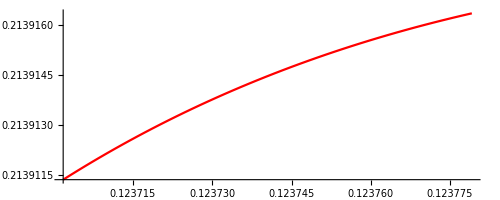

```mathematica
Show[graphWithTrajectoriesBACK]
```

```mathematica
0.4925+0.4925+0.015
```

1.

```mathematica
listOfProjectedTrajectoriesBelow=Flatten[Table[Simplex2DCoord[Trajectory[N[{0.4925,0.4925,0.015}],bv,cv,deltav,100][ti]],{initx1,1/div,(div-1)/div,200}]];
```

Step to 0.0001: {0.492519,0.492481,0.0150004}  ExpectedChange {0.188885,-0.192805,0.00391932}

Step to 0.0002: {0.492538,0.492461,0.0150008}  ExpectedChange {0.188885,-0.192804,0.00391944}

Step to 0.0004: {0.492576,0.492423,0.0150016}  ExpectedChange {0.188884,-0.192803,0.00391968}

Step to 0.0008: {0.492651,0.492346,0.0150031}  ExpectedChange {0.188881,-0.192801,0.00392016}

Step to 0.0016: {0.492802,0.492192,0.0150063}  ExpectedChange {0.188876,-0.192797,0.00392112}

Step to 0.0032: {0.493104,0.491883,0.0150125}  ExpectedChange {0.188866,-0.192789,0.00392304}

Step to 0.0064: {0.493709,0.491266,0.0150251}  ExpectedChange {0.188844,-0.192771,0.00392687}

Step to 0.0128: {0.494917,0.490033,0.0150503}  ExpectedChange {0.1888,-0.192735,0.0039345}

Step to 0.0192: {0.496125,0.488799,0.0150755}  ExpectedChange {0.188754,-0.192696,0.00394209}

Step to 0.0256: {0.497333,0.487566,0.0151007}  ExpectedChange {0.188705,-0.192654,0.00394963}

Step to 0.032: {0.498541,0.486333,0.015126}  ExpectedChange {0.188653,-0.19261,0.00395714}

Step to 0.0448: {0.500955,0.483868,0.0151768}  ExpectedChange {0.188543,-0.192515,0.00397201}

Step to 0.0576: {0.503367,0.481405,0.0152277}  ExpectedChange {0.188423,-0.19241,0.0039867}

Step to 0.0704: {0.505778,0.478943,0.0152788}  ExpectedChange {0.188294,-0.192295,0.00400121}

Step to 0.0832: {0.508188,0.476482,0.0153301}  ExpectedChange {0.188154,-0.19217,0.00401554}

Step to 0.1088: {0.513001,0.471566,0.0154333}  ExpectedChange {0.187847,-0.19189,0.00404362}

Step to 0.130245: {0.517026,0.467454,0.0155203}  ExpectedChange {0.187559,-0.191626,0.00406653}

Step to 0.15169: {0.521045,0.463347,0.0156077}  ExpectedChange {0.187246,-0.191334,0.00408887}

Step to 0.173135: {0.525057,0.459248,0.0156956}  ExpectedChange {0.186905,-0.191016,0.00411061}

Step to 0.19458: {0.529061,0.455155,0.015784}  ExpectedChange {0.186539,-0.19067,0.00413175}

Step to 0.216025: {0.533057,0.45107,0.0158728}  ExpectedChange {0.186146,-0.190298,0.00415226}

Step to 0.258915: {0.541023,0.442925,0.0160518}  ExpectedChange {0.185284,-0.189475,0.00419134}

Step to 0.301805: {0.548949,0.434818,0.0162323}  ExpectedChange {0.184321,-0.188548,0.00422771}

Step to 0.344695: {0.556833,0.426753,0.0164144}  ExpectedChange {0.183259,-0.187521,0.00426125}

Step to 0.387585: {0.564668,0.418734,0.0165978}  ExpectedChange {0.182102,-0.186394,0.00429181}

Step to 0.430475: {0.572452,0.410766,0.0167825}  ExpectedChange {0.180852,-0.185172,0.00431928}

Step to 0.473365: {0.58018,0.402851,0.0169683}  ExpectedChange {0.179513,-0.183856,0.00434355}

Step to 0.516255: {0.587849,0.394996,0.017155}  ExpectedChange {0.178086,-0.182451,0.0043645}

Step to 0.559145: {0.595455,0.387202,0.0173426}  ExpectedChange {0.176577,-0.180959,0.00438204}

Step to 0.602035: {0.602995,0.379474,0.0175309}  ExpectedChange {0.174988,-0.179384,0.00439606}

Step to 0.644926: {0.610465,0.371816,0.0177197}  ExpectedChange {0.173323,-0.177729,0.00440648}

Step to 0.687816: {0.617862,0.36423,0.0179088}  ExpectedChange {0.171585,-0.175998,0.00441322}

Step to 0.730706: {0.625182,0.356719,0.0180982}  ExpectedChange {0.169779,-0.174196,0.00441621}

Step to 0.773596: {0.632424,0.349288,0.0182876}  ExpectedChange {0.167909,-0.172324,0.00441539}

Step to 0.816486: {0.639585,0.341938,0.0184769}  ExpectedChange {0.165978,-0.170389,0.00441071}

Step to 0.902266: {0.653651,0.327494,0.0188544}  ExpectedChange {0.16195,-0.16634,0.00438963}

Step to 0.973188: {0.665014,0.315821,0.0191648}  ExpectedChange {0.158472,-0.162833,0.00436028}

Step to 1.03702: {0.675027,0.305531,0.019442}  ExpectedChange {0.155244,-0.159569,0.00432462}

Step to 1.10085: {0.684831,0.295452,0.0197167}  ExpectedChange {0.151936,-0.156216,0.00428023}

Step to 1.16468: {0.694422,0.28559,0.0199882}  ExpectedChange {0.148562,-0.152789,0.00422719}

Step to 1.22851: {0.703796,0.275948,0.0202561}  ExpectedChange {0.145133,-0.149299,0.00416566}

Step to 1.29234: {0.712949,0.266531,0.0205198}  ExpectedChange {0.141663,-0.145758,0.0040958}

Step to 1.35617: {0.72188,0.257342,0.0207788}  ExpectedChange {0.138162,-0.142179,0.00401785}

Step to 1.42: {0.730586,0.248381,0.0210326}  ExpectedChange {0.134641,-0.138574,0.00393207}

Step to 1.48383: {0.739068,0.239652,0.0212806}  ExpectedChange {0.131113,-0.134951,0.00383877}

Step to 1.54766: {0.747324,0.231153,0.0215225}  ExpectedChange {0.127585,-0.131323,0.00373829}

Step to 1.61149: {0.755356,0.222887,0.0217577}  ExpectedChange {0.124067,-0.127698,0.003631}

Step to 1.67532: {0.763163,0.214851,0.0219859}  ExpectedChange {0.120569,-0.124086,0.00351729}

Step to 1.73915: {0.770748,0.207045,0.0222066}  ExpectedChange {0.117097,-0.120495,0.00339758}

Step to 1.80298: {0.778112,0.199468,0.0224195}  ExpectedChange {0.11366,-0.116932,0.00327229}

Step to 1.86681: {0.785259,0.192117,0.0226243}  ExpectedChange {0.110263,-0.113404,0.00314188}

Step to 1.93064: {0.79219,0.18499,0.0228205}  ExpectedChange {0.106912,-0.109919,0.00300679}

Step to 1.99447: {0.798908,0.178084,0.023008}  ExpectedChange {0.103613,-0.10648,0.00286748}

Step to 2.0583: {0.805418,0.171395,0.0231865}  ExpectedChange {0.10037,-0.103094,0.00272441}

Step to 2.12213: {0.811723,0.164921,0.0233557}  ExpectedChange {0.0971873,-0.0997653,0.00257802}

Step to 2.18596: {0.817826,0.158658,0.0235155}  ExpectedChange {0.0940684,-0.0964972,0.00242876}

Step to 2.24979: {0.823733,0.152601,0.0236657}  ExpectedChange {0.0910162,-0.0932933,0.00227708}

Step to 2.31362: {0.829447,0.146747,0.0238062}  ExpectedChange {0.088033,-0.0901564,0.00212339}

Step to 2.37745: {0.834973,0.14109,0.0239368}  ExpectedChange {0.0851208,-0.0870889,0.00196812}

Step to 2.44128: {0.840315,0.135627,0.0240574}  ExpectedChange {0.0822811,-0.0840928,0.00181165}

Step to 2.50511: {0.845479,0.130353,0.024168}  ExpectedChange {0.0795151,-0.0811694,0.00165438}

Step to 2.56894: {0.850468,0.125264,0.0242686}  ExpectedChange {0.0768234,-0.07832,0.00149666}

Step to 2.63277: {0.855287,0.120353,0.0243591}  ExpectedChange {0.0742065,-0.0755454,0.00133884}

Step to 2.6966: {0.859943,0.115618,0.0244395}  ExpectedChange {0.0716646,-0.0728458,0.00118124}

Step to 2.76044: {0.864438,0.111052,0.0245099}  ExpectedChange {0.0691974,-0.0702216,0.00102417}

Step to 2.82427: {0.868778,0.106652,0.0245703}  ExpectedChange {0.0668047,-0.0676726,0.000867923}

Step to 2.8881: {0.872968,0.102412,0.0246207}  ExpectedChange {0.0644857,-0.0651984,0.000712758}

Step to 2.95193: {0.877012,0.098327,0.0246613}  ExpectedChange {0.0622397,-0.0627986,0.000558926}

Step to 3.01576: {0.880915,0.0943932,0.0246921}  ExpectedChange {0.0600657,-0.0604723,0.000406654}

Step to 3.07959: {0.884681,0.0906055,0.0247133}  ExpectedChange {0.0579626,-0.0582187,0.000256154}

Step to 3.14342: {0.888316,0.0869594,0.0247249}  ExpectedChange {0.0559292,-0.0560368,0.000107616}

Step to 3.20725: {0.891823,0.0834503,0.0247271}  ExpectedChange {0.0539641,-0.0539253,-0.0000387831}

Step to 3.27108: {0.895206,0.0800738,0.02472}  ExpectedChange {0.052066,-0.0518831,-0.000182886}

Step to 3.33491: {0.898471,0.0768255,0.0247038}  ExpectedChange {0.0502333,-0.0499088,-0.00032455}

Step to 3.39874: {0.90162,0.073701,0.0246786}  ExpectedChange {0.0484645,-0.0480009,-0.000463647}

Step to 3.46257: {0.904659,0.0706963,0.0246446}  ExpectedChange {0.046758,-0.0461579,-0.000600065}

Step to 3.5264: {0.907591,0.0678071,0.024602}  ExpectedChange {0.0451121,-0.0443784,-0.000733702}

Step to 3.59023: {0.910419,0.0650296,0.024551}  ExpectedChange {0.0435253,-0.0426608,-0.000864472}

Step to 3.65406: {0.913149,0.0623597,0.0244917}  ExpectedChange {0.0419957,-0.0410034,-0.000992299}

Step to 3.71789: {0.915782,0.0597938,0.0244244}  ExpectedChange {0.0405219,-0.0394048,-0.00111712}

Step to 3.78172: {0.918323,0.0573281,0.0243492}  ExpectedChange {0.039102,-0.0378632,-0.00123887}

Step to 3.84555: {0.920775,0.054959,0.0242663}  ExpectedChange {0.0377345,-0.036377,-0.00135752}

Step to 3.90938: {0.923141,0.052683,0.024176}  ExpectedChange {0.0364177,-0.0349446,-0.00147302}

Step to 3.97321: {0.925425,0.0504968,0.0240783}  ExpectedChange {0.0351498,-0.0335645,-0.00158535}

Step to 4.03704: {0.927629,0.0483971,0.0239736}  ExpectedChange {0.0339295,-0.032235,-0.00169449}

Step to 4.10087: {0.929757,0.0463806,0.0238621}  ExpectedChange {0.032755,-0.0309545,-0.00180041}

Step to 4.1647: {0.931812,0.0444444,0.0237439}  ExpectedChange {0.0316247,-0.0297216,-0.00190312}

Step to 4.22853: {0.933795,0.0425854,0.0236192}  ExpectedChange {0.0305372,-0.0285346,-0.00200261}

Step to 4.29236: {0.935711,0.0408007,0.0234883}  ExpectedChange {0.029491,-0.0273921,-0.00209888}

Step to 4.35619: {0.937561,0.0390876,0.0233513}  ExpectedChange {0.0284846,-0.0262926,-0.00219194}

Step to 4.42002: {0.939348,0.0374433,0.0232085}  ExpectedChange {0.0275165,-0.0252347,-0.0022818}

Step to 4.48385: {0.941075,0.0358653,0.0230601}  ExpectedChange {0.0265855,-0.024217,-0.00236847}

Step to 4.54768: {0.942743,0.0343509,0.0229062}  ExpectedChange {0.02569,-0.023238,-0.00245198}

Step to 4.61151: {0.944355,0.0328979,0.0227471}  ExpectedChange {0.0248288,-0.0222965,-0.00253234}

Step to 4.67534: {0.945913,0.0315038,0.022583}  ExpectedChange {0.0240007,-0.0213911,-0.00260958}

Step to 4.73917: {0.94742,0.0301663,0.0224141}  ExpectedChange {0.0232043,-0.0205206,-0.00268372}

Step to 4.803: {0.948876,0.0288834,0.0222405}  ExpectedChange {0.0224386,-0.0196838,-0.00275479}

Step to 4.86683: {0.950285,0.0276528,0.0220624}  ExpectedChange {0.0217022,-0.0188793,-0.00282283}

Step to 4.93066: {0.951647,0.0264726,0.0218802}  ExpectedChange {0.0209941,-0.0181062,-0.00288786}

Step to 4.99449: {0.952965,0.0253407,0.0216938}  ExpectedChange {0.0203131,-0.0173632,-0.00294993}

Step to 5.05832: {0.954241,0.0242554,0.0215036}  ExpectedChange {0.0196583,-0.0166492,-0.00300905}

Step to 5.12215: {0.955476,0.0232147,0.0213098}  ExpectedChange {0.0190285,-0.0159633,-0.00306528}

Step to 5.18598: {0.956671,0.0222169,0.0211124}  ExpectedChange {0.0184229,-0.0153042,-0.00311865}

Step to 5.24981: {0.957828,0.0212604,0.0209117}  ExpectedChange {0.0178404,-0.0146712,-0.00316919}

Step to 5.31364: {0.958949,0.0203435,0.0207079}  ExpectedChange {0.0172801,-0.0140632,-0.00321694}

Step to 5.37748: {0.960034,0.0194646,0.0205011}  ExpectedChange {0.0167412,-0.0134792,-0.00326195}

Step to 5.44131: {0.961086,0.0186222,0.0202915}  ExpectedChange {0.0162227,-0.0129184,-0.00330425}

Step to 5.50514: {0.962106,0.0178149,0.0200793}  ExpectedChange {0.0157238,-0.0123799,-0.00334388}

Step to 5.56897: {0.963094,0.0170413,0.0198647}  ExpectedChange {0.0152438,-0.0118629,-0.0033809}

Step to 5.6328: {0.964052,0.0163001,0.0196478}  ExpectedChange {0.0147819,-0.0113666,-0.00341533}

Step to 5.69663: {0.964981,0.0155898,0.0194287}  ExpectedChange {0.0143373,-0.0108901,-0.00344722}

Step to 5.76046: {0.965883,0.0149094,0.0192077}  ExpectedChange {0.0139093,-0.0104327,-0.00347661}

Step to 5.82429: {0.966757,0.0142576,0.0189849}  ExpectedChange {0.0134973,-0.00999375,-0.00350355}

Step to 5.88812: {0.967606,0.0136332,0.0187605}  ExpectedChange {0.0131005,-0.00957246,-0.00352807}

Step to 5.95195: {0.96843,0.0130352,0.0185346}  ExpectedChange {0.0127184,-0.00916818,-0.00355023}

Step to 6.01578: {0.96923,0.0124625,0.0183073}  ExpectedChange {0.0123503,-0.00878027,-0.00357006}

Step to 6.07961: {0.970007,0.011914,0.0180789}  ExpectedChange {0.0119957,-0.00840807,-0.00358761}

Step to 6.14344: {0.970762,0.0113888,0.0178494}  ExpectedChange {0.0116539,-0.008051,-0.00360292}

Step to 6.20727: {0.971495,0.0108859,0.017619}  ExpectedChange {0.0113245,-0.00770846,-0.00361604}

Step to 6.2711: {0.972208,0.0104044,0.0173878}  ExpectedChange {0.0110069,-0.00737989,-0.00362702}

Step to 6.33493: {0.972901,0.00994346,0.017156}  ExpectedChange {0.0107006,-0.00706474,-0.00363588}

Step to 6.39876: {0.973574,0.00950223,0.0169237}  ExpectedChange {0.0104052,-0.0067625,-0.00364269}

Step to 6.46259: {0.974229,0.00907989,0.016691}  ExpectedChange {0.0101201,-0.00647267,-0.00364748}

Step to 6.52642: {0.974866,0.00867567,0.0164581}  ExpectedChange {0.00984505,-0.00619474,-0.00365031}

Step to 6.59025: {0.975486,0.00828883,0.0162251}  ExpectedChange {0.00957947,-0.00592827,-0.00365121}

Step to 6.65408: {0.976089,0.00791863,0.015992}  ExpectedChange {0.00932301,-0.00567279,-0.00365023}

Step to 6.71791: {0.976676,0.00756441,0.0157591}  ExpectedChange {0.00907528,-0.00542787,-0.00364742}

Step to 6.78174: {0.977248,0.00722549,0.0155264}  ExpectedChange {0.00883592,-0.0051931,-0.00364282}

Step to 6.84557: {0.977805,0.00690125,0.0152941}  ExpectedChange {0.00860456,-0.00496808,-0.00363648}

Step to 6.9094: {0.978347,0.00659107,0.0150622}  ExpectedChange {0.00838086,-0.00475241,-0.00362844}

Step to 6.97323: {0.978875,0.00629436,0.0148309}  ExpectedChange {0.0081645,-0.00454574,-0.00361876}

Step to 7.03706: {0.979389,0.00601057,0.0146003}  ExpectedChange {0.00795517,-0.00434769,-0.00360748}

Step to 7.10089: {0.97989,0.00573915,0.0143704}  ExpectedChange {0.00775257,-0.00415793,-0.00359464}

Step to 7.16472: {0.980379,0.0054796,0.0141414}  ExpectedChange {0.00755641,-0.00397612,-0.00358029}

Step to 7.29238: {0.98132,0.00499408,0.0136864}  ExpectedChange {0.00718236,-0.00363512,-0.00354724}

Step to 7.40728: {0.982126,0.00459288,0.0132808}  ExpectedChange {0.00686516,-0.00335235,-0.00351281}

Step to 7.52217: {0.982898,0.00422293,0.0128794}  ExpectedChange {0.00656497,-0.00309075,-0.00347421}

Step to 7.63707: {0.983635,0.0038819,0.0124826}  ExpectedChange {0.00628054,-0.00284882,-0.00343172}

Step to 7.75196: {0.984341,0.00356761,0.0120909}  ExpectedChange {0.00601074,-0.00262513,-0.0033856}

Step to 7.86685: {0.985017,0.00327804,0.0117048}  ExpectedChange {0.0057545,-0.00241837,-0.00333613}

Step to 7.98175: {0.985664,0.0030113,0.0113245}  ExpectedChange {0.00551088,-0.00222731,-0.00328357}

Step to 8.09664: {0.986284,0.00276567,0.0109503}  ExpectedChange {0.005279,-0.00205082,-0.00322818}

Step to 8.21154: {0.986878,0.00253953,0.0105828}  ExpectedChange {0.00505805,-0.00188782,-0.00317023}

Step to 8.32643: {0.987447,0.00233139,0.010222}  ExpectedChange {0.0048473,-0.00173733,-0.00310997}

Step to 8.44133: {0.987992,0.00213987,0.0098682}  ExpectedChange {0.00464608,-0.00159843,-0.00304765}

Step to 8.55622: {0.988515,0.00196368,0.00952171}  ExpectedChange {0.00445378,-0.00147026,-0.00298352}

Step to 8.78601: {0.989496,0.00165264,0.00885127}  ExpectedChange {0.00409379,-0.00124302,-0.00285077}

Step to 9.0158: {0.990398,0.00138981,0.0082119}  ExpectedChange {0.00376344,-0.00104988,-0.00271356}

Step to 9.24559: {0.991228,0.00116792,0.0076044}  ExpectedChange {0.0034595,-0.000885916,-0.00257358}

Step to 9.47538: {0.99199,0.000980764,0.00702923}  ExpectedChange {0.0031793,-0.000746878,-0.00243242}

Step to 9.70517: {0.99269,0.000823049,0.0064865}  ExpectedChange {0.00292058,-0.000629108,-0.00229147}

Step to 9.93495: {0.993334,0.000690259,0.005976}  ExpectedChange {0.00268146,-0.00052946,-0.002152}

Step to 10.1647: {0.993924,0.000578546,0.00549729}  ExpectedChange {0.00246034,-0.000445237,-0.0020151}

Step to 10.3945: {0.994466,0.00048464,0.00504964}  ExpectedChange {0.00225581,-0.000374124,-0.00188169}

Step to 10.6243: {0.994962,0.00040576,0.00463218}  ExpectedChange {0.00206668,-0.00031414,-0.00175254}

Step to 10.8541: {0.995417,0.00033955,0.00424384}  ExpectedChange {0.00189185,-0.00026359,-0.00162826}

Step to 11.0839: {0.995833,0.000284012,0.00388345}  ExpectedChange {0.00173037,-0.000221031,-0.00150934}

Step to 11.3137: {0.996213,0.000237455,0.00354974}  ExpectedChange {0.00158134,-0.00018523,-0.00139611}

Step to 11.5435: {0.99656,0.00019845,0.00324138}  ExpectedChange {0.00144395,-0.000155138,-0.00128881}

Step to 11.7733: {0.996877,0.00016579,0.00295697}  ExpectedChange {0.00131741,-0.000129866,-0.00118755}

Step to 12.0031: {0.997166,0.000138458,0.00269514}  ExpectedChange {0.00120101,-0.000108656,-0.00109236}

Step to 12.2328: {0.99743,0.000115594,0.00245449}  ExpectedChange {0.00109407,-0.0000908679,-0.0010032}

Step to 12.4626: {0.99767,0.000096478,0.00223364}  ExpectedChange {0.000995921,-0.0000759592,-0.000919961}

Step to 12.6924: {0.997888,0.0000805012,0.00203125}  ExpectedChange {0.000905956,-0.0000634713,-0.000842485}

Step to 12.9222: {0.998087,0.0000671535,0.00184602}  ExpectedChange {0.000823586,-0.0000530169,-0.000770569}

Step to 13.152: {0.998267,0.0000560061,0.0016767}  ExpectedChange {0.00074825,-0.0000442695,-0.000703981}

Step to 13.3818: {0.998431,0.0000466995,0.0015221}  ExpectedChange {0.000679422,-0.0000369538,-0.000642468}

Step to 13.6116: {0.99858,0.0000389319,0.00138107}  ExpectedChange {0.000616602,-0.0000308382,-0.000585764}

Step to 13.8414: {0.998715,0.0000324506,0.00125255}  ExpectedChange {0.000559318,-0.0000257279,-0.000533591}

Step to 14.0712: {0.998837,0.000027044,0.00113552}  ExpectedChange {0.00050713,-0.0000214593,-0.000485671}

Step to 14.3009: {0.998948,0.0000225349,0.00102904}  ExpectedChange {0.000459623,-0.000017895,-0.000441728}

Step to 14.5307: {0.999049,0.0000187751,0.000932225}  ExpectedChange {0.000416409,-0.0000149197,-0.000401489}

Step to 14.7605: {0.99914,0.0000156408,0.000844259}  ExpectedChange {0.000377129,-0.0000124368,-0.000364692}

Step to 14.9903: {0.999223,0.0000130282,0.000764377}  ExpectedChange {0.000341447,-0.0000103654,-0.000331081}

Step to 15.2201: {0.999297,0.000010851,0.000691875}  ExpectedChange {0.000309053,-8.63766×10^-6,-0.000300415}

Step to 15.6797: {0.999426,7.52642×10^-6,0.000566465}  ExpectedChange {0.000253004,-5.99661×10^-6,-0.000247008}

Step to 16.1393: {0.999531,5.22061×10^-6,0.000463429}  ExpectedChange {0.000206946,-4.16256×10^-6,-0.000202783}

Step to 16.5988: {0.999617,3.62151×10^-6,0.000378894}  ExpectedChange {0.000169156,-2.8893×10^-6,-0.000166267}

Step to 17.0584: {0.999688,2.5119×10^-6,0.000309619}  ExpectedChange {0.00013819,-2.00504×10^-6,-0.000136185}

Step to 17.518: {0.999745,1.74174×10^-6,0.000252903}  ExpectedChange {0.000112842,-1.39085×10^-6,-0.000111451}

Step to 17.9776: {0.999792,1.2075×10^-6,0.000206504}  ExpectedChange {0.0000921101,-9.6456×10^-7,-0.0000911456}

Step to 18.4371: {0.999831,8.37204×10^-7,0.000168569}  ExpectedChange {0.0000751661,-6.68948×10^-7,-0.0000744972}

Step to 18.8967: {0.999862,5.80522×10^-7,0.000137571}  ExpectedChange {0.0000613253,-4.63957×10^-7,-0.0000608613}

Step to 19.3563: {0.999887,4.0246×10^-7,0.000112252}  ExpectedChange {0.0000500242,-3.21707×10^-7,-0.0000497025}

Step to 19.8159: {0.999908,2.78919×10^-7,0.0000915789}  ExpectedChange {0.0000407999,-2.22987×10^-7,-0.0000405769}

Step to 20.2755: {0.999925,1.93287×10^-7,0.0000747034}  ExpectedChange {0.000033273,-1.54546×10^-7,-0.0000331185}

Step to 20.735: {0.999939,1.33982×10^-7,0.0000609312}  ExpectedChange {0.0000271324,-1.07138×10^-7,-0.0000270253}

Step to 21.1946: {0.99995,9.28884×10^-8,0.0000496939}  ExpectedChange {0.0000221237,-7.42841×10^-8,-0.0000220494}

Step to 21.6542: {0.999959,6.43811×10^-8,0.0000405262}  ExpectedChange {0.0000180387,-5.14898×10^-8,-0.0000179872}

Step to 22.1138: {0.999967,4.46055×10^-8,0.000033048}  ExpectedChange {0.0000147074,-3.56759×10^-8,-0.0000146717}

Step to 22.5733: {0.999973,3.09064×10^-8,0.0000269485}  ExpectedChange {0.000011991,-2.47203×10^-8,-0.0000119663}

Step to 23.0329: {0.999978,2.14242×10^-8,0.0000219739}  ExpectedChange {9.77613×10^-6,-1.71366×10^-8,-9.75899×10^-6}

Step to 23.4925: {0.999982,1.48534×10^-8,0.0000179171}  ExpectedChange {7.97024×10^-6,-1.18812×10^-8,-7.95836×10^-6}

Step to 23.9521: {0.999985,1.02932×10^-8,0.0000146088}  ExpectedChange {6.49787×10^-6,-8.23371×10^-9,-6.48963×10^-6}

Step to 24.4117: {0.999988,7.12996×10^-9,0.0000119112}  ExpectedChange {5.29746×10^-6,-5.70348×10^-9,-5.29175×10^-6}

Step to 24.8712: {0.99999,4.94013×10^-9,9.71154×10^-6}  ExpectedChange {4.31879×10^-6,-3.95182×10^-9,-4.31484×10^-6}

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {0.999992+1/2 (-x12-x13),x12,x13,3.39355×10^-9+1/2 (-x12-x23),x23,7.91695×10^-6+1/2 (-x13-x23)}/.{}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolveValue::nlnum: The function value {3.5262×10^-6-0.999992 (3.96021×10^-6 (2.4 Part[«2»]+1.33333 Part[«2»])-1. (-0.4 Part[«2»]+1.6 Plus[«2»])-1. (-0.222222 Part[«2»]+1.6 Plus[«2»])),-2.89624×10^-9-3.39355×10^-9 (-0.5 (2.4 Part[«2»]+1.33333 Part[«2»])+«1»-1. (-«20» «1»+«1»)),-3.52331×10^-6-7.91695×10^-6 (-0.5 (2.4 Part[«2»]+1.33333 Part[«2»])-1. (-0.4 Part[«2»]+1.6 Plus[«2»])+126310. (-0.222222 Part[«2»]+1.6 Plus[«2»]))} is not a list of numbers with dimensions {3} at {ti,x$40440160[ti],x$40440160'[ti]} = {25.3308,{0.999992,3.39355×10^-9,7.91695×10^-6},{3.5262×10^-6,-2.89624×10^-9,-3.52331×10^-6}}.

```mathematica
graphWithTrajectoriesBACK=ParametricPlot[Evaluate[listOfProjectedTrajectoriesBACK],{ti,0,100},PlotStyle ->Red];
```

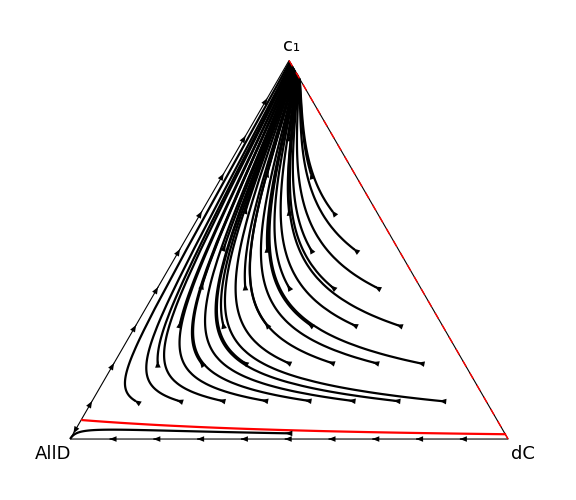

```mathematica
listOfArrows=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.1)}]},{i,0,0}]&,listOfProjectedTrajectories],1];listOfArrowsSide=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.01)}]},{i,0,0}]&,listOfProjectedTrajectoriesSide],1];listOfArrowsBottom=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.01)}]},{i,0,0}]&,listOfProjectedTrajectoriesBottom],1];
listOfArrowsSideBottom=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.01)}]},{i,0,0}]&,listOfProjectedTrajectoriesSideBottom],1];
listOfArrowsSideBelow=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.045)}]},{i,0,0}]&,listOfProjectedTrajectoriesBelow],1];graphWithTrajectories=ParametricPlot[Evaluate[listOfProjectedTrajectories],{ti,0,47},PlotStyle ->Black];graphWithTrajectoriesBelow=ParametricPlot[Evaluate[listOfProjectedTrajectoriesBelow],{ti,0,20},PlotStyle ->Black];graphWithTrajectoriesBACK=ParametricPlot[Evaluate[listOfProjectedTrajectoriesBACK],{ti,0,100},PlotStyle ->Red];Neutralpart =Graphics[{Red,Dashed,Line[{Simplex2DCoord[{0,1,0}],Simplex2DCoord[{0,0,1}]}]}]; 
Show[{Outside,graphWithTrajectories,graphWithTrajectoriesBACK,graphWithTrajectoriesBelow,Graphics[listOfArrows],Graphics[listOfArrowsBottom],Graphics[listOfArrowsSideBottom],Graphics[listOfArrowsSide],Graphics[listOfArrowsSideBelow],Neutralpart,Graphics[{Inset[Style[Row[{Subscript["c",1]}],18],{0.505,0.9}],Inset[Style[Row[{"AllD"}],18],{-0.04,-0.035}],Inset[Style[Row[{"dC"}],18],{1.035,-0.035}]}]},Frame ->False,Axes->False,ImageSize->Large]
```

```mathematica
listOfProjectedTrajectories[[2]]
```

Simplex2DCoord[InterpolatingFunction[…][ti]]

```mathematica
Simplex2DCoord[InterpolatingFunction[…][0]]
Simplex2DCoord[InterpolatingFunction[…][4]]
```

{0.583333,0.433013}

{0.694181,2.73069×10^-6}

```mathematica
Simplex2DInverseCoord[Simplex2DCoord[InterpolatingFunction[…][4]]]
```

{0.305817,0.69418,3.15313×10^-6}

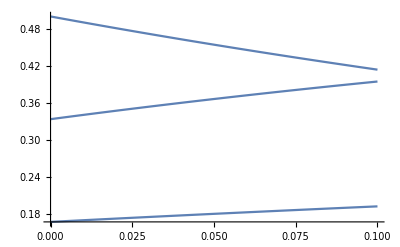

```mathematica
Plot[Simplex2DInverseCoord[Simplex2DCoord[InterpolatingFunction[…][ti]]],{ti,0,0.1}]
```

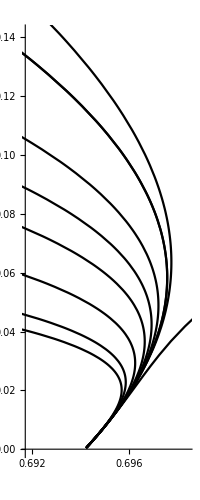

```mathematica
graphWithTrajectories
```

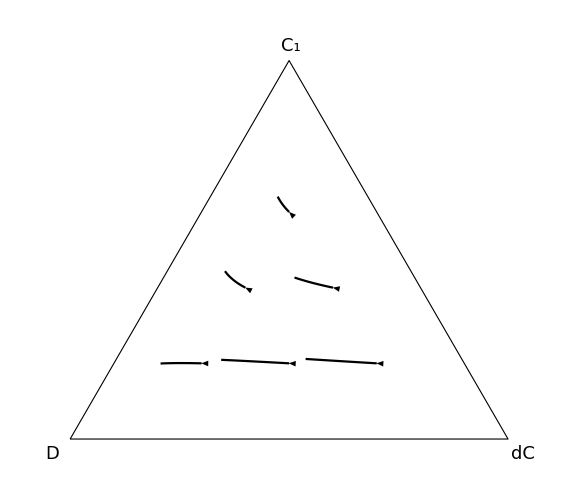

```mathematica
Show[{Outside,graphWithTrajectories,Graphics[listOfArrows],Graphics[{Inset[Style[Row[{Subscript["C",1]}],18],{0.505,0.9}],Inset[Style[Row[{"D"}],18],{-0.04,-0.035}],Inset[Style[Row[{"dC"}],18],{1.035,-0.035}]}]},Frame ->False,Axes->False,ImageSize->Large]
```

```mathematica
bv = 3;cv=1;deltav=0.9;Tv = 1;
listOfProjectedTrajectories=Flatten[Table[Simplex2DCoord[Trajectory[N[{initx1,initx2,1-initx1-initx2}],bv,cv,deltav,Tv][ti]],{initx1,0,1,1/3},{initx2,0,1-initx1,1/6}]];listOfArrows=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.04)}]},{i,0,0}]&,listOfProjectedTrajectories],1];graphWithTrajectories=ParametricPlot[Evaluate[listOfProjectedTrajectories],{ti,0,100},PlotStyle ->Black];Show[{Outside,graphWithTrajectories,Graphics[listOfArrows],circ,Graphics[{Inset[Style[Row[{"D"}],18],{0.505,0.9}],Inset[Style[Row[{"CC"}],18],{-0.04,-0.035}],Inset[Style[Row[{"CH"}],18],{1.035,-0.035}]}]},PlotRange ->{{-0.1,1+0.1},{-0.1,(√3)/2+0.1}},Frame ->False,Axes->False,ImageSize->Large]
```

Part::partw: Part 4 of solveSystem[x$56860[ti].{1,0,0},x$56860[ti].{0,1,0},0.9] does not exist.

Part::partw: Part 5 of solveSystem[x$56860[ti].{1,0,0},x$56860[ti].{0,1,0},0.9] does not exist.

Part::partw: Part 6 of solveSystem[x$56860[ti].{1,0,0},x$56860[ti].{0,1,0},0.9] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Invalid input⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {Invalid input⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Invalid input⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {Invalid input⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Invalid input⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {Invalid input⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolveValue::nlnum: The function value {0.929895 (0.111268-1. (-0.0656447+1.8 (Part[«2»]+Part[«2»]))),0.0729386 (-1.47588+12.7102 (-0.0656447+1.8 (Part[«2»]+Part[«2»]))),-0.00283324 (-1.47588-1. (-0.0656447+1.8 (Part[«2»]+Part[«2»])))} is not a list of numbers with dimensions {3} at {ti,x$89915[ti]} = {0.978526,{0.929895,0.0729386,-0.00283324}}.

NDSolveValue::nlnum: The function value {0.871131 (0.242091-1. (-0.11918+1.8 (Part[«2»]+Part[«2»]))),0.132422 (-1.63649+6.55161 (-0.11918+1.8 (Part[«2»]+Part[«2»]))),-0.00355274 (-1.63649-1. (-0.11918+1.8 (Part[«2»]+Part[«2»])))} is not a list of numbers with dimensions {3} at {ti,x$148438[ti]} = {0.769598,{0.871131,0.132422,-0.00355274}}.

NDSolveValue::nlnum: The function value {0.799231 (0.459755-1. (-0.183756+1.8 (Part[«2»]+Part[«2»]))),0.204174 (-1.83022+3.89779 (-0.183756+1.8 (Part[«2»]+Part[«2»]))),-0.00340483 (-1.83022-1. (-0.183756+1.8 (Part[«2»]+Part[«2»])))} is not a list of numbers with dimensions {3} at {ti,x$204195[ti]} = {0.586671,{0.799231,0.204174,-0.00340483}}.

General::stop: Further output of NDSolveValue::nlnum will be suppressed during this calculation.

$Aborted

```mathematica
{0.03*(PD[0.03,0.8,3,1,0.9]-AvgP[0.03,0.8,3,1,0.9]),0.8*(PDC[0.03,0.8,3,1,0.9]-AvgP[0.03,0.8,3,1,0.9]),(x.{0,0,1})*(PC1[0.03,0.8,3,1,0.9]-AvgP[0.03,0.8,3,1,0.9])}


ExpectedChange[{0.03,0.8,0.1}, 3,1,0.9]




solveSystem[1,0,delta]















ClearAll[solveSystem]

solveSystem[x1_?NumericQ,x2_?NumericQ,delta_?NumericQ]:=Module[{b11,b12,b13,b22,b23,b33,eq1,eq2,eq3,sol,x3,solution},(*Define x3*)x3=1-x1-x2;
(*Define b values*)b11=b12=b22=b23=b33=(1-delta);
b13=delta/(1+delta) + (1-delta)/(1+delta);
Eq1=b12 x12==(2 (b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b12 x12+b23 x23-b22 (x12-2 x2+x23)))/(-2 b12 x12+b22 x12-2 b13 x13+b11 (-2 x1+x12+x13)-2 b22 x2+b22 x23-2 b23 x23+b33 (-2+2 x1+x13+2 x2+x23))^2;
Eq2=b23 x23==(2 (b12 x12+b23 x23-b22 (x12-2 x2+x23)) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(-2 b12 x12+b22 x12-2 b13 x13+b11 (-2 x1+x12+x13)-2 b22 x2+b22 x23-2 b23 x23+b33 (-2+2 x1+x13+2 x2+x23))^2;
Eq3=b13 x13==(2 (b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(-2 b12 x12+b22 x12-2 b13 x13+b11 (-2 x1+x12+x13)-2 b22 x2+b22 x23-2 b23 x23+b33 (-2+2 x1+x13+2 x2+x23))^2;

(*Solve the system numerically for positive roots that satisfy all conditions*)sol=NSolve[{Eq1,Eq2,Eq3,x12>0,x23>0,x13>0,x1-(1/2)*(x12+x13)>0,x2-(1/2)*(x12+x23)>0,x3-(1/2)*(x23+x13)>0},{x12,x23,x13},Reals];
(*Check if there are any solutions*)If[sol=!={},(*Use the first solution*)solution=sol[[1]];
(*Return the six values as specified*){x1-(1/2)*(x12+x13),x12,x13,x2-(1/2)*(x12+x23),x23,x3-(1/2)*(x23+x13)}/.solution,(*If no solution,return an error message*)"No positive solution found where all specified expressions are positive"]]

(*Example usage:*)
solveSystem[0.5,0.3,0.9]  (*Assuming delta is 0.1*)
```

{0.0837396,-0.245083,0.949079 x.{0,0,1}}

{0.0837396,-0.245083,0.0949079}

No positive solution found where all specified expressions are positive

No positive solution found where all specified expressions are positive

```mathematica
ClearAll[solveSystem]

solveSystem[x1_?NumericQ,x2_?NumericQ,delta_?NumericQ]:=Module[{b11,b12,b13,b22,b23,b33,eq1,eq2,eq3,sol,x3,solution},(*Define x3*)x3=1-x1-x2;
(*Define b values*)b11=b12=b22=b23=b33=(1-delta);
b13=delta/(1+delta) + (1-delta)/(1+delta);
Eq1=b12 x12==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b12 x12+b23 x23-b22 (x12-2 x2+x23)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
Eq2=b23 x23==((b12 x12+b23 x23-b22 (x12-2 x2+x23)) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
Eq3=b13 x13==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));

(*Solve the system numerically for positive roots that satisfy all conditions*)sol=NSolve[{Eq1,Eq2,Eq3,x12>0,x23>0,x13>0},{x12,x23,x13},Reals];
(*Check if there are any solutions*)If[sol=!={},(*Use the first solution*)solution=sol[[1]];
(*Return the six values as specified*){x1-(1/2)*(x12+x13),x12,x13,x2-(1/2)*(x12+x23),x23,x3-(1/2)*(x23+x13)}/.solution,(*If no solution,return an error message*)"No positive solution found where all specified expressions are positive"]]

(*Example usage:*)
solveSystem[0.5,0.3,0.9]
```

{0.318067,0.3,0.0638655,0.0707398,0.15852,0.088807}[1]

```mathematica
Mean[{0.3180672268907563,0.3,0.06386554621848739,0.07073976221928666,0.15852047556142668,0.08880698911004298}]
```

0.166667

```mathematica
ClearAll[solveSystem]

solveSystem[x1_?NumericQ,x2_?NumericQ,delta_?NumericQ]:=Module[{b11,b12,b13,b22,b23,b33,eq1,eq2,eq3,sol,x3},(*Define x3*)x3=1-x1-x2;
(*Define b values*)b11=b12=b22=b23=b33=(1-delta);

(*Define b values*)b11=b12=b22=b23=b33=(1-delta);
b13=delta/(1+delta) + (1-delta)/(1+delta);
Eq1=b12 x12==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b12 x12+b23 x23-b22 (x12-2 x2+x23)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
Eq2=b23 x23==((b12 x12+b23 x23-b22 (x12-2 x2+x23)) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
Eq3=b13 x13==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));


(*Solve the system based on the values of x1,x2,and x3*)sol=Which[x1>0&&x2>0&&x3>0,NSolve[{eq1,eq2,eq3,x12>0,x23>0,x13>0},{x12,x23,x13},Reals],x1==0,NSolve[{eq2,x12==0,x23>0,x13==0},{x12,x23,x13},Reals],x2==0,NSolve[{eq3,x12==0,x23==0,x13>0},{x12,x23,x13},Reals],x3==0,NSolve[{eq1,x12>0,x23==0,x13==0},{x12,x23,x13},Reals],x1==0&&x2==0,{{x13->0,x12->0,x23->0}},x1==0&&x3==0,{{x23->0,x12->0,x13->0}},x2==0&&x3==0,{{x12->0,x23->0,x13->0}},True,"Invalid input"];
(*Process the solution*)If[ListQ[sol]&&Not[sol==="Invalid input"],If[sol=!={},(*If there are solutions,format the output*)First[{x1-(1/2)*(x12+x13),x12,x13,x2-(1/2)*(x12+x23),x23,x3-(1/2)*(x23+x13)}/.sol],(*If no solution,return an error message*)"No positive solution found"],sol]]

(*Example usage:*)
solveSystem[0.5,0.3,0.9]  (*Assuming delta is 0.1*)
```

No positive solution found

```mathematica
solveSystem[x1_?NumericQ,x2_?NumericQ,delta_?NumericQ]:=Module[{b11,b12,b13,b22,b23,b33,eq1,eq2,eq3,sol,x3,solution},(*Define x3*)x3=1-x1-x2;
(*Define b values*)b11=b12=b22=b23=b33=(1-delta);
b13=delta/(1+delta) + (1-delta)/(1+delta);
eq1=b12 x12==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b12 x12+b23 x23-b22 (x12-2 x2+x23)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
eq2=b23 x23==((b12 x12+b23 x23-b22 (x12-2 x2+x23)) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
eq3=b13 x13==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));

(*Solve the system numerically for positive roots that satisfy all conditions*)sol=Which[x1>0&&x2>0&&x3>0,NSolve[{eq1,eq2,eq3,x12>0,x23>0,x13>0},{x12,x23,x13},Reals],x1==0,NSolve[{eq2,x12==0,x23>0,x13==0},{x12,x23,x13},Reals],x2==0,NSolve[{eq3,x12==0,x23==0,x13>0},{x12,x23,x13},Reals],x3==0,NSolve[{eq1,x12>0,x23==0,x13==0},{x12,x23,x13},Reals],x1==0&&x2==0,{{x13->0,x12->0,x23->0}},x1==0&&x3==0,{{x23->0,x12->0,x13->0}},x2==0&&x3==0,{{x12->0,x23->0,x13->0}},True,"Invalid input"];(*Check if there are any solutions*)If[sol=!={},(*Use the first solution*)solution=sol[[1]];
(*Return the six values as specified*){x1-(1/2)*(x12+x13),x12,x13,x2-(1/2)*(x12+x23),x23,x3-(1/2)*(x23+x13)}/.solution,(*If no solution,return an error message*)"No positive solution found where all specified expressions are positive"]]
```

```mathematica
solveSystem[0.5,0.3,0.9]
```

{0.318067,0.3,0.0638655,0.0707398,0.15852,0.088807}

```mathematica
x1 = 0.5; x2 = 0.3;
```

```mathematica
(*Define x3*)x3=1-x1-x2;
(*Define b values*)b11=b12=b22=b23=b33=(1-delta);
b13=delta/(1+delta) + (1-delta)/(1+delta);
Eq1=b12 x12==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b12 x12+b23 x23-b22 (x12-2 x2+x23)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
Eq2=b23 x23==((b12 x12+b23 x23-b22 (x12-2 x2+x23)) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
Eq3=b13 x13==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
```

```mathematica
sol=Which[x1>0&&x2>0&&x3>0,NSolve[{eq1,eq2,eq3,x12>0,x23>0,x13>0},{x12,x23,x13},Reals],x1==0,NSolve[{eq2,x12==0,x23>0,x13==0},{x12,x23,x13},Reals],x2==0,NSolve[{eq3,x12==0,x23==0,x13>0},{x12,x23,x13},Reals],x3==0,NSolve[{eq1,x12>0,x23==0,x13==0},{x12,x23,x13},Reals],x1==0&&x2==0,{{x13->0,x12->0,x23->0}},x1==0&&x3==0,{{x23->0,x12->0,x13->0}},x2==0&&x3==0,{{x12->0,x23->0,x13->0}},True,"Invalid input"];
```

```mathematica
sol
```

{}

```mathematica
NSolve[{x12==2,x23==2,x13==2},{x12,x23,x13},Reals][[1]]
```

{x12→2.,x23→2.,x13→2.}

```mathematica
{{x23->0,x12->0,x13->0}}[[1]]
```

{x23→0,x12→0,x13→0}

```mathematica
x1 = 0.69;x2 = 0.31;  delta = 0.9;
b11=(1-delta);b12=(1-delta);b22=(1-delta);b23=(1-delta);b33=(1-delta);
b13=delta/(1+delta) + (1-delta)/(1+delta); x3 = 1-x2-x1;
```

```mathematica
x3
```

False

```mathematica
eq1=b12 x12==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b12 x12+b23 x23-b22 (x12-2 x2+x23)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
eq2=b23 x23==((b12 x12+b23 x23-b22 (x12-2 x2+x23)) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
eq3=b13 x13==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));

(*Solve the system numerically for positive roots that satisfy all conditions*)sol=Which[x1>0&&x2>0&&x3>0,NSolve[{eq1,eq2,eq3,x12>0,x23>0,x13>0},{x12,x23,x13},Reals],x1==0&&x2==0,NSolve[{x12==0,x23==0,x13==0},{x12,x23,x13},Reals],x1==0&&x3==0,NSolve[{x12==0,x23==0,x13==0},{x12,x23,x13},Reals],x2==0&&x3==0,NSolve[{x12==0,x23==0,x13==0},{x12,x23,x13},Reals],x1==0,NSolve[{eq2,x12==0,x23>0,x13==0},{x12,x23,x13},Reals],x2==0,NSolve[{eq3,x12==0,x23==0,x13>0},{x12,x23,x13},Reals],x3==0,NSolve[{eq1,x12>0,x23==0,x13==0},{x12,x23,x13},Reals],True,"Invalid input"];
```

```mathematica
sol
```

{{x23→0,x13→0,x12→0.4278}}

```mathematica
solveSystem[x1_?NumericQ,x2_?NumericQ,delta_?NumericQ]:=Module[{b11,b12,b13,b22,b23,b33,eq1,eq2,eq3,sol,x3,solution},(*Define x3*)x3=1-x1-x2;x3=Max[0,x3];
(*Define b values*)b11=b12=b22=b23=b33=(1-delta);
b13=delta/(1+delta) + (1-delta)/(1+delta);
eq1=b12 x12==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b12 x12+b23 x23-b22 (x12-2 x2+x23)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
eq2=b23 x23==((b12 x12+b23 x23-b22 (x12-2 x2+x23)) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));
eq3=b13 x13==((b12 x12+b11 (2 x1-x12-x13)+b13 x13) (b13 x13+b23 x23-b33 (x13+x23-2 x3)))/(2 b12 x12-b22 x12+b11 (2 x1-x12-x13)+2 b13 x13+2 b22 x2-b22 x23+2 b23 x23-b33 (-2+2 x1+x13+2 x2+x23));

(*Solve the system numerically for positive roots that satisfy all conditions*)sol=Which[x1>0&&x2>0&&x3>0,NSolve[{eq1,eq2,eq3,x12>0,x23>0,x13>0},{x12,x23,x13},Reals],x1==0&&x2==0,NSolve[{x12==0,x23==0,x13==0},{x12,x23,x13},Reals],x1==0&&x3==0,NSolve[{x12==0,x23==0,x13==0},{x12,x23,x13},Reals],x2==0&&x3==0,NSolve[{x12==0,x23==0,x13==0},{x12,x23,x13},Reals],x1==0,NSolve[{eq2,x12==0,x23>0,x13==0},{x12,x23,x13},Reals],x2==0,NSolve[{eq3,x12==0,x23==0,x13>0},{x12,x23,x13},Reals],x3==0,NSolve[{eq1,x12>0,x23==0,x13==0},{x12,x23,x13},Reals],True,"Invalid input"];(*Check if there are any solutions*)If[sol=!={},(*Use the first solution*)solution=sol[[1]];
(*Return the six values as specified*){x1-(1/2)*(x12+x13),x12,x13,x2-(1/2)*(x12+x23),x23,x3-(1/2)*(x23+x13)}/.solution,(*If no solution,return an error message*)"No positive solution found where all specified expressions are positive"]]
solveSystem[0.5,0.3,0.9]
solveSystem[0,0.3,0.9]
solveSystem[0.5,0,0.9]
solveSystem[0,0,0.9]
solveSystem[1,0,0.9]
solveSystem[0,1,0.9]
solveSystem[0.5,0.5,0.9]
solveSystem[0.4,0.6,0.9]
solveSystem[0.69,0.31,0.9]
(*Example usage:*)
```

```mathematica
(* against DC: 1/(1-delta) games --> only second period counts --> has weight delta --> delta*(1/1/(1-delta))
```

```mathematica
PD[xD_,xDC_, b_,c_,delta_] := xDC*delta*b + (1-xD-xDC)*b*delta*(1-delta);
```

```mathematica
PDC[0,0.2, 3,1,0.9]
PC1[0,0.2, 3,1,0.9]
(*against d -> 0 kind of the opposite of what D gets -> -c, and for dcdc it's similar but payoff is b-c. And against c1, the payoff is the same *)
```

PDC[0,0.2,3,1,0.9]

PC1[0,0.2,3,1,0.9]

```mathematica
PDC[xD_,xDC_, b_,c_,delta_] := xD*delta*(-c) + (1-xD) * delta*(b-c);
```

```mathematica
PC1[xD_,xDC_, b_,c_,delta_] := xD*delta*(1-delta)*(-c) + (1-xD)* delta* (b-c);

AvgP[xD_,xDC_, b_,c_,delta_] := xD* PD[xD,xDC, b,c,delta] + xDC* PDC[xD,xDC, b,c,delta] + (1-xD-xDC)* PC1[xD,xDC, b,c,delta];


(*G1 and D --> (1-xd)*delta*(1-delta)*b == (1-xd)*delta*(b-c) + xd*delta*(1-delta)*(-c)*)
Solve[(1-xd)*delta*(1-delta)*b == (1-xd)*delta*(b-c) + xd*delta*(1-delta)*(-c),xd]
```

{{xd→(-c+b delta)/((b-c) delta)}}

```mathematica
Trajectory[initialPoint_List, b_,c_,delta_,time_]:=Module[{x},
NDSolveValue[
{x'[ti]==ExpectedChange[x[ti], b,c,delta],x[0]==initialPoint},
x,{ti,0,time},Method->{"EquationSimplification"->"Residual"}]
]
```

```mathematica
BackTrajectory[initialPoint_List, b_,c_,delta_,time_]:=Module[{x},
NDSolveValue[
{x'[ti]==-ExpectedChange[x[ti], b,c,delta],x[0]==initialPoint},
x,{ti,0,time},Method->{"EquationSimplification"->"Residual"}]
]
```

```mathematica
bv = 3;cv=1;deltav=0.8;Tv = 60;div = 10;
listOfProjectedTrajectories=Flatten[Table[Simplex2DCoord[Trajectory[N[{initx1,initx2,1-initx1-initx2}],bv,cv,deltav,Tv][ti]],{initx1,0,1,1/div},{initx2,0,1-initx1,1/div}]];listOfProjectedTrajectoriesBACK=Flatten[Table[Simplex2DCoord[BackTrajectory[N[{(-cv+bv deltav)/((bv-cv) deltav)-0.0001,0.0002,1-(-cv+bv deltav)/((bv-cv) deltav)-0.0001}],bv,cv,deltav,Tv][ti]],{initx1,0,1,10},{initx2,0,1-initx1,10}]];
```

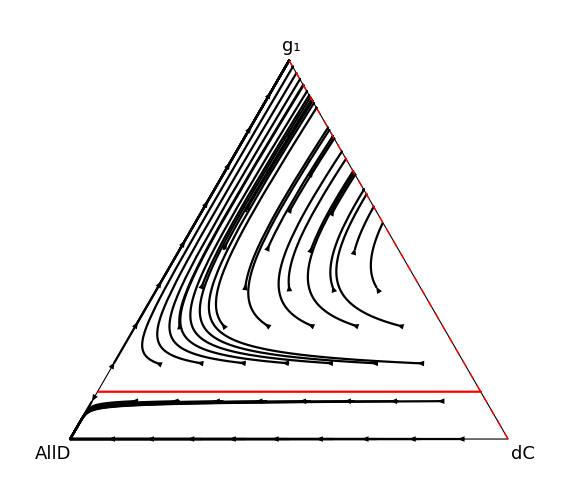

```mathematica
listOfArrows=Flatten[Map[Table[{Arrowheads[0.02],Arrow[{#/.ti ->i,#/.ti ->(i+0.2)}]},{i,0,0}]&,listOfProjectedTrajectories],1];graphWithTrajectories=ParametricPlot[Evaluate[listOfProjectedTrajectories],{ti,0,Tv},PlotStyle ->Black];
graphWithTrajectoriesBACK=ParametricPlot[Evaluate[listOfProjectedTrajectoriesBACK],{ti,0,Tv},PlotStyle ->Red];Neutralpart =Graphics[{Red,Dashed,Line[{Simplex2DCoord[{0,1,0}],Simplex2DCoord[{0,0,1}]}]}]; 
Show[{Outside,graphWithTrajectories,graphWithTrajectoriesBACK,Graphics[listOfArrows],Neutralpart,Graphics[{Inset[Style[Row[{Subscript["g",1]}],18],{0.505,0.9}],Inset[Style[Row[{"AllD"}],18],{-0.04,-0.035}],Inset[Style[Row[{"dC"}],18],{1.035,-0.035}]}]},Frame ->False,Axes->False,ImageSize->Large]
```